Loading modules...

LoadModules::Using Re Im variables.

LoadModules::Moments 1 through 6 are being used.

TODO::STM_Common::Propagate UseHighPrecision and HighPrecisionValue throughout code...

SetDelayed::write: Tag BooleanQ in BooleanQ[x_] is Protected.

Attributes[RandomVariate]={Protected}
 
Options[RandomVariate]={Method→Automatic,WorkingPrecision→Automatic}

TODO::In gradient implementation Tangential gradient was not included.

TODO::CoeffF2NormF2 must be changed from default value to be in the same form as for P4 model.

TODO::Implement CalculateP2Invariants in a more efficient way.

TODO::STM_P4Grad::The code below either is not used or should not be used. Remove.

TODO::STM_Calc::Change Transpose to ConjugateTranspose.

TODO::STM_Calc::eeReconstruct now supports only complex variables.

sm Analytinc functions for R(NT,NS,TTT)

LoadModules::Loading STM_YDerivativesImplReImCYI.m, STM_YDerivativesImplReImGen.m, STM_YDerivativesImplReIm.m, STM_CommonReIm.m

LoadModules::Loading STM_YDerivativesImpl_6_ReImCYI.m, STM_YDerivativesImpl_6_ReImGen.m

Initializing models & related coefficients.

Initializing F2 model.

Resetting 4th power polynom model.

Initializing.

NNN = 8

NA = 28

GradientMultiplier = 1/56

!!! Clearing t !!!

remapTable

remapReverseTable

CreateVariables::Starting...

CreateVariables::Creating real S, A and related...

SL - Linearized variables.

Ap - preliminary matrix of antysimmetric variables (without accounting for the sign swap for pairs).

AL - Linearized antisymmetric variables.

A - matrix of all antisymmetric variables.

Ap = (0 | Ar1c2 | Ar1c3 | Ar1c4 | Ar1c5 | Ar1c6 | Ar1c7 | Ar1c8
-Ar1c2 | 0 | Ar2c3 | Ar2c4 | Ar2c5 | Ar2c6 | Ar2c7 | Ar2c8
-Ar1c3 | -Ar2c3 | 0 | Ar3c4 | Ar3c5 | Ar3c6 | Ar3c7 | Ar3c8
-Ar1c4 | -Ar2c4 | -Ar3c4 | 0 | Ar4c5 | Ar4c6 | Ar4c7 | Ar4c8
-Ar1c5 | -Ar2c5 | -Ar3c5 | -Ar4c5 | 0 | Ar5c6 | Ar5c7 | Ar5c8
-Ar1c6 | -Ar2c6 | -Ar3c6 | -Ar4c6 | -Ar5c6 | 0 | Ar6c7 | Ar6c8
-Ar1c7 | -Ar2c7 | -Ar3c7 | -Ar4c7 | -Ar5c7 | -Ar6c7 | 0 | Ar7c8
-Ar1c8 | -Ar2c8 | -Ar3c8 | -Ar4c8 | -Ar5c8 | -Ar6c8 | -Ar7c8 | 0)

AL = {Ar1c2,Ar1c3,Ar1c4,Ar1c5,Ar1c6,Ar1c7,Ar1c8,Ar2c3,Ar2c4,Ar2c5,Ar2c6,Ar2c7,Ar2c8,Ar3c4,Ar3c5,Ar3c6,Ar3c7,Ar3c8,Ar4c5,Ar4c6,Ar4c7,Ar4c8,Ar5c6,Ar5c7,Ar5c8,Ar6c7,Ar6c8,Ar7c8}

A = (0 | Ar1c2 | Ar1c3 | Ar1c4 | Ar1c5 | Ar1c6 | Ar1c7 | Ar1c8
-Ar1c2 | 0 | Ar2c3 | Ar2c4 | Ar2c5 | Ar2c6 | Ar2c7 | Ar2c8
-Ar1c3 | -Ar2c3 | 0 | Ar3c4 | Ar3c5 | Ar3c6 | Ar3c7 | Ar3c8
-Ar1c4 | -Ar2c4 | -Ar3c4 | 0 | Ar4c5 | Ar4c6 | Ar4c7 | Ar4c8
-Ar1c5 | -Ar2c5 | -Ar3c5 | -Ar4c5 | 0 | Ar5c6 | Ar5c7 | Ar5c8
-Ar1c6 | -Ar2c6 | -Ar3c6 | -Ar4c6 | -Ar5c6 | 0 | Ar6c7 | Ar6c8
-Ar1c7 | -Ar2c7 | -Ar3c7 | -Ar4c7 | -Ar5c7 | -Ar6c7 | 0 | Ar7c8
-Ar1c8 | -Ar2c8 | -Ar3c8 | -Ar4c8 | -Ar5c8 | -Ar6c8 | -Ar7c8 | 0)

Check ToALinear...

(AL - ToALinear[A]) = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Check ToAMatrix...

(A - ToAMatrix[AL]) = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Creating WL

WL = {Sr1c2,Sr1c3,Sr1c4,Sr1c5,Sr1c6,Sr1c7,Sr1c8,Sr2c3,Sr2c4,Sr2c5,Sr2c6,Sr2c7,Sr2c8,Sr3c4,Sr3c5,Sr3c6,Sr3c7,Sr3c8,Sr4c5,Sr4c6,Sr4c7,Sr4c8,Sr5c6,Sr5c7,Sr5c8,Sr6c7,Sr6c8,Sr7c8,Ar1c2,Ar1c3,Ar1c4,Ar1c5,Ar1c6,Ar1c7,Ar1c8,Ar2c3,Ar2c4,Ar2c5,Ar2c6,Ar2c7,Ar2c8,Ar3c4,Ar3c5,Ar3c6,Ar3c7,Ar3c8,Ar4c5,Ar4c6,Ar4c7,Ar4c8,Ar5c6,Ar5c7,Ar5c8,Ar6c7,Ar6c8,Ar7c8}

CreateVariables::Completed.

=============================================

EE - matrix of all 1.

EI - vector (column) of all 1, EIT - row of all 1.

---------------------------------------------

eXXTIdentity - Identity matrix of size nn.

ZZ - matrix of all 0.

ZL - vector (of na length) of all 0.

II - Identity matrix.

EEIJ - matrix of all 1 of dimension (nn-1) x (nn-1)

IIIJ

eeIJmeeIJT = IIIJ-(1/nn)*EEIJ

eprimIJidentity - (n-1) x (n-1) Identity matrix.

!!! NOT calculating alphaIJ, alphaIJpm1.

Constructing 2-nd power terms.

D = 2, 4 terms.

D2T4Cabcd

---------------------------------------------

D = 2, 2 terms.

D2T2Cabbd

---------------------------------------------

D = 2, 0 terms.

D2T0Cabab

---------------------------------------------

Initializing P4 model.

Resetting 4th power polynom model.

Initializing.

NNN = 8

NA = 28

GradientMultiplier = 1/56

!!! Clearing t !!!

remapTable

remapReverseTable

CreateVariables::Starting...

CreateVariables::Creating real S, A and related...

SL - Linearized variables.

Ap - preliminary matrix of antysimmetric variables (without accounting for the sign swap for pairs).

AL - Linearized antisymmetric variables.

A - matrix of all antisymmetric variables.

Ap = (0 | Ar1c2 | Ar1c3 | Ar1c4 | Ar1c5 | Ar1c6 | Ar1c7 | Ar1c8
-Ar1c2 | 0 | Ar2c3 | Ar2c4 | Ar2c5 | Ar2c6 | Ar2c7 | Ar2c8
-Ar1c3 | -Ar2c3 | 0 | Ar3c4 | Ar3c5 | Ar3c6 | Ar3c7 | Ar3c8
-Ar1c4 | -Ar2c4 | -Ar3c4 | 0 | Ar4c5 | Ar4c6 | Ar4c7 | Ar4c8
-Ar1c5 | -Ar2c5 | -Ar3c5 | -Ar4c5 | 0 | Ar5c6 | Ar5c7 | Ar5c8
-Ar1c6 | -Ar2c6 | -Ar3c6 | -Ar4c6 | -Ar5c6 | 0 | Ar6c7 | Ar6c8
-Ar1c7 | -Ar2c7 | -Ar3c7 | -Ar4c7 | -Ar5c7 | -Ar6c7 | 0 | Ar7c8
-Ar1c8 | -Ar2c8 | -Ar3c8 | -Ar4c8 | -Ar5c8 | -Ar6c8 | -Ar7c8 | 0)

AL = {Ar1c2,Ar1c3,Ar1c4,Ar1c5,Ar1c6,Ar1c7,Ar1c8,Ar2c3,Ar2c4,Ar2c5,Ar2c6,Ar2c7,Ar2c8,Ar3c4,Ar3c5,Ar3c6,Ar3c7,Ar3c8,Ar4c5,Ar4c6,Ar4c7,Ar4c8,Ar5c6,Ar5c7,Ar5c8,Ar6c7,Ar6c8,Ar7c8}

A = (0 | Ar1c2 | Ar1c3 | Ar1c4 | Ar1c5 | Ar1c6 | Ar1c7 | Ar1c8
-Ar1c2 | 0 | Ar2c3 | Ar2c4 | Ar2c5 | Ar2c6 | Ar2c7 | Ar2c8
-Ar1c3 | -Ar2c3 | 0 | Ar3c4 | Ar3c5 | Ar3c6 | Ar3c7 | Ar3c8
-Ar1c4 | -Ar2c4 | -Ar3c4 | 0 | Ar4c5 | Ar4c6 | Ar4c7 | Ar4c8
-Ar1c5 | -Ar2c5 | -Ar3c5 | -Ar4c5 | 0 | Ar5c6 | Ar5c7 | Ar5c8
-Ar1c6 | -Ar2c6 | -Ar3c6 | -Ar4c6 | -Ar5c6 | 0 | Ar6c7 | Ar6c8
-Ar1c7 | -Ar2c7 | -Ar3c7 | -Ar4c7 | -Ar5c7 | -Ar6c7 | 0 | Ar7c8
-Ar1c8 | -Ar2c8 | -Ar3c8 | -Ar4c8 | -Ar5c8 | -Ar6c8 | -Ar7c8 | 0)

Check ToALinear...

(AL - ToALinear[A]) = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Check ToAMatrix...

(A - ToAMatrix[AL]) = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Creating WL

WL = {Sr1c2,Sr1c3,Sr1c4,Sr1c5,Sr1c6,Sr1c7,Sr1c8,Sr2c3,Sr2c4,Sr2c5,Sr2c6,Sr2c7,Sr2c8,Sr3c4,Sr3c5,Sr3c6,Sr3c7,Sr3c8,Sr4c5,Sr4c6,Sr4c7,Sr4c8,Sr5c6,Sr5c7,Sr5c8,Sr6c7,Sr6c8,Sr7c8,Ar1c2,Ar1c3,Ar1c4,Ar1c5,Ar1c6,Ar1c7,Ar1c8,Ar2c3,Ar2c4,Ar2c5,Ar2c6,Ar2c7,Ar2c8,Ar3c4,Ar3c5,Ar3c6,Ar3c7,Ar3c8,Ar4c5,Ar4c6,Ar4c7,Ar4c8,Ar5c6,Ar5c7,Ar5c8,Ar6c7,Ar6c8,Ar7c8}

CreateVariables::Completed.

=============================================

EE - matrix of all 1.

EI - vector (column) of all 1, EIT - row of all 1.

---------------------------------------------

eXXTIdentity - Identity matrix of size nn.

ZZ - matrix of all 0.

ZL - vector (of na length) of all 0.

II - Identity matrix.

EEIJ - matrix of all 1 of dimension (nn-1) x (nn-1)

IIIJ

eeIJmeeIJT = IIIJ-(1/nn)*EEIJ

eprimIJidentity - (n-1) x (n-1) Identity matrix.

!!! NOT calculating alphaIJ, alphaIJpm1.

Constructing 4-th power terms.

D = 4, 8 terms.

D4T8Cabcdefgh

---------------------------------------------

D = 4, 6 terms.

D4T6Cabbdefgh

---------------------------------------------

D = 4, 5 terms.

D4T5Cabbdbfgh

---------------------------------------------

D = 4, 4 terms.

D4T4Cabbdbfbh

D4T4Cababefgh

D4T4Cabbddfgh

D4T4Cabbdeffh

---------------------------------------------

D = 4, 3 terms.

D4T3Cababbfgh

D4T3Cabbddfdh

---------------------------------------------

D = 4, 2 terms.

D4T2Cababbfbh

D4T2Cababeffh

D4T2Cabbddffh

D4T2Cabbdbddh

D4T2Cabababgh

D4T2Cabbdadgh

---------------------------------------------

D = 4, 1 terms.

D4T1Cababbffh

D4T1Cabbdaddh

D4T1Cabababbh

---------------------------------------------

D = 4, 0 terms.

D4T0Cababbfbf

D4T0Cababefef

D4T0Cabbddfaf

D4T0Cabbdbdad

D4T0Cabababab

---------------------------------------------

Total number of terms NoTermCnt = 23

=============================================

Time used: 0.4132759, total time used: 0.4132759
---------------------------------------------

TODO::F4Func is not implemented yet for complex variables!!!

Initializing P6 model.

Resetting 6th power polynom model.

Initializing.

NNN = 12

NA = 66

GradientMultiplier = 1/132

!!! Clearing t !!!

remapTable

remapReverseTable

CreateVariables::Starting...

CreateVariables::Creating real S, A and related...

SL - Linearized variables.

Ap - preliminary matrix of antysimmetric variables (without accounting for the sign swap for pairs).

AL - Linearized antisymmetric variables.

A - matrix of all antisymmetric variables.

Ap = (0 | Ar01c02 | Ar01c03 | Ar01c04 | Ar01c05 | Ar01c06 | Ar01c07 | Ar01c08 | Ar01c09 | Ar01c10 | Ar01c11 | Ar01c12
-Ar01c02 | 0 | Ar02c03 | Ar02c04 | Ar02c05 | Ar02c06 | Ar02c07 | Ar02c08 | Ar02c09 | Ar02c10 | Ar02c11 | Ar02c12
-Ar01c03 | -Ar02c03 | 0 | Ar03c04 | Ar03c05 | Ar03c06 | Ar03c07 | Ar03c08 | Ar03c09 | Ar03c10 | Ar03c11 | Ar03c12
-Ar01c04 | -Ar02c04 | -Ar03c04 | 0 | Ar04c05 | Ar04c06 | Ar04c07 | Ar04c08 | Ar04c09 | Ar04c10 | Ar04c11 | Ar04c12
-Ar01c05 | -Ar02c05 | -Ar03c05 | -Ar04c05 | 0 | Ar05c06 | Ar05c07 | Ar05c08 | Ar05c09 | Ar05c10 | Ar05c11 | Ar05c12
-Ar01c06 | -Ar02c06 | -Ar03c06 | -Ar04c06 | -Ar05c06 | 0 | Ar06c07 | Ar06c08 | Ar06c09 | Ar06c10 | Ar06c11 | Ar06c12
-Ar01c07 | -Ar02c07 | -Ar03c07 | -Ar04c07 | -Ar05c07 | -Ar06c07 | 0 | Ar07c08 | Ar07c09 | Ar07c10 | Ar07c11 | Ar07c12
-Ar01c08 | -Ar02c08 | -Ar03c08 | -Ar04c08 | -Ar05c08 | -Ar06c08 | -Ar07c08 | 0 | Ar08c09 | Ar08c10 | Ar08c11 | Ar08c12
-Ar01c09 | -Ar02c09 | -Ar03c09 | -Ar04c09 | -Ar05c09 | -Ar06c09 | -Ar07c09 | -Ar08c09 | 0 | Ar09c10 | Ar09c11 | Ar09c12
-Ar01c10 | -Ar02c10 | -Ar03c10 | -Ar04c10 | -Ar05c10 | -Ar06c10 | -Ar07c10 | -Ar08c10 | -Ar09c10 | 0 | Ar10c11 | Ar10c12
-Ar01c11 | -Ar02c11 | -Ar03c11 | -Ar04c11 | -Ar05c11 | -Ar06c11 | -Ar07c11 | -Ar08c11 | -Ar09c11 | -Ar10c11 | 0 | Ar11c12
-Ar01c12 | -Ar02c12 | -Ar03c12 | -Ar04c12 | -Ar05c12 | -Ar06c12 | -Ar07c12 | -Ar08c12 | -Ar09c12 | -Ar10c12 | -Ar11c12 | 0)

AL = {Ar01c02,Ar01c03,Ar01c04,Ar01c05,Ar01c06,Ar01c07,Ar01c08,Ar01c09,Ar01c10,Ar01c11,Ar01c12,Ar02c03,Ar02c04,Ar02c05,Ar02c06,Ar02c07,Ar02c08,Ar02c09,Ar02c10,Ar02c11,Ar02c12,Ar03c04,Ar03c05,Ar03c06,Ar03c07,Ar03c08,Ar03c09,Ar03c10,Ar03c11,Ar03c12,Ar04c05,Ar04c06,Ar04c07,Ar04c08,Ar04c09,Ar04c10,Ar04c11,Ar04c12,Ar05c06,Ar05c07,Ar05c08,Ar05c09,Ar05c10,Ar05c11,Ar05c12,Ar06c07,Ar06c08,Ar06c09,Ar06c10,Ar06c11,Ar06c12,Ar07c08,Ar07c09,Ar07c10,Ar07c11,Ar07c12,Ar08c09,Ar08c10,Ar08c11,Ar08c12,Ar09c10,Ar09c11,Ar09c12,Ar10c11,Ar10c12,Ar11c12}

A = (0 | Ar01c02 | Ar01c03 | Ar01c04 | Ar01c05 | Ar01c06 | Ar01c07 | Ar01c08 | Ar01c09 | Ar01c10 | Ar01c11 | Ar01c12
-Ar01c02 | 0 | Ar02c03 | Ar02c04 | Ar02c05 | Ar02c06 | Ar02c07 | Ar02c08 | Ar02c09 | Ar02c10 | Ar02c11 | Ar02c12
-Ar01c03 | -Ar02c03 | 0 | Ar03c04 | Ar03c05 | Ar03c06 | Ar03c07 | Ar03c08 | Ar03c09 | Ar03c10 | Ar03c11 | Ar03c12
-Ar01c04 | -Ar02c04 | -Ar03c04 | 0 | Ar04c05 | Ar04c06 | Ar04c07 | Ar04c08 | Ar04c09 | Ar04c10 | Ar04c11 | Ar04c12
-Ar01c05 | -Ar02c05 | -Ar03c05 | -Ar04c05 | 0 | Ar05c06 | Ar05c07 | Ar05c08 | Ar05c09 | Ar05c10 | Ar05c11 | Ar05c12
-Ar01c06 | -Ar02c06 | -Ar03c06 | -Ar04c06 | -Ar05c06 | 0 | Ar06c07 | Ar06c08 | Ar06c09 | Ar06c10 | Ar06c11 | Ar06c12
-Ar01c07 | -Ar02c07 | -Ar03c07 | -Ar04c07 | -Ar05c07 | -Ar06c07 | 0 | Ar07c08 | Ar07c09 | Ar07c10 | Ar07c11 | Ar07c12
-Ar01c08 | -Ar02c08 | -Ar03c08 | -Ar04c08 | -Ar05c08 | -Ar06c08 | -Ar07c08 | 0 | Ar08c09 | Ar08c10 | Ar08c11 | Ar08c12
-Ar01c09 | -Ar02c09 | -Ar03c09 | -Ar04c09 | -Ar05c09 | -Ar06c09 | -Ar07c09 | -Ar08c09 | 0 | Ar09c10 | Ar09c11 | Ar09c12
-Ar01c10 | -Ar02c10 | -Ar03c10 | -Ar04c10 | -Ar05c10 | -Ar06c10 | -Ar07c10 | -Ar08c10 | -Ar09c10 | 0 | Ar10c11 | Ar10c12
-Ar01c11 | -Ar02c11 | -Ar03c11 | -Ar04c11 | -Ar05c11 | -Ar06c11 | -Ar07c11 | -Ar08c11 | -Ar09c11 | -Ar10c11 | 0 | Ar11c12
-Ar01c12 | -Ar02c12 | -Ar03c12 | -Ar04c12 | -Ar05c12 | -Ar06c12 | -Ar07c12 | -Ar08c12 | -Ar09c12 | -Ar10c12 | -Ar11c12 | 0)

Check ToALinear...

(AL - ToALinear[A]) = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Check ToAMatrix...

(A - ToAMatrix[AL]) = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Creating WL

WL = {Sr01c02,Sr01c03,Sr01c04,Sr01c05,Sr01c06,Sr01c07,Sr01c08,Sr01c09,Sr01c10,Sr01c11,Sr01c12,Sr02c03,Sr02c04,Sr02c05,Sr02c06,Sr02c07,Sr02c08,Sr02c09,Sr02c10,Sr02c11,Sr02c12,Sr03c04,Sr03c05,Sr03c06,Sr03c07,Sr03c08,Sr03c09,Sr03c10,Sr03c11,Sr03c12,Sr04c05,Sr04c06,Sr04c07,Sr04c08,Sr04c09,Sr04c10,Sr04c11,Sr04c12,Sr05c06,Sr05c07,Sr05c08,Sr05c09,Sr05c10,Sr05c11,Sr05c12,Sr06c07,Sr06c08,Sr06c09,Sr06c10,Sr06c11,Sr06c12,Sr07c08,Sr07c09,Sr07c10,Sr07c11,Sr07c12,Sr08c09,Sr08c10,Sr08c11,Sr08c12,Sr09c10,Sr09c11,Sr09c12,Sr10c11,Sr10c12,Sr11c12,Ar01c02,Ar01c03,Ar01c04,Ar01c05,Ar01c06,Ar01c07,Ar01c08,Ar01c09,Ar01c10,Ar01c11,Ar01c12,Ar02c03,Ar02c04,Ar02c05,Ar02c06,Ar02c07,Ar02c08,Ar02c09,Ar02c10,Ar02c11,Ar02c12,Ar03c04,Ar03c05,Ar03c06,Ar03c07,Ar03c08,Ar03c09,Ar03c10,Ar03c11,Ar03c12,Ar04c05,Ar04c06,Ar04c07,Ar04c08,Ar04c09,Ar04c10,Ar04c11,Ar04c12,Ar05c06,Ar05c07,Ar05c08,Ar05c09,Ar05c10,Ar05c11,Ar05c12,Ar06c07,Ar06c08,Ar06c09,Ar06c10,Ar06c11,Ar06c12,Ar07c08,Ar07c09,Ar07c10,Ar07c11,Ar07c12,Ar08c09,Ar08c10,Ar08c11,Ar08c12,Ar09c10,Ar09c11,Ar09c12,Ar10c11,Ar10c12,Ar11c12}

CreateVariables::Completed.

=============================================

EE - matrix of all 1.

EI - vector (column) of all 1, EIT - row of all 1.

---------------------------------------------

eXXTIdentity - Identity matrix of size nn.

ZZ - matrix of all 0.

ZL - vector (of na length) of all 0.

II - Identity matrix.

EEIJ - matrix of all 1 of dimension (nn-1) x (nn-1)

IIIJ

eeIJmeeIJT = IIIJ-(1/nn)*EEIJ

eprimIJidentity - (n-1) x (n-1) Identity matrix.

!!! NOT calculating alphaIJ, alphaIJpm1.

Constructing SOME 6-th power terms.

D6T0Cabababababab

---------------------------------------------

Reinitializing variables for numeric run.

Initializing.

NNN = 10

NA = 45

GradientMultiplier = 1/90

!!! Clearing t !!!

remapTable

remapReverseTable

CreateVariables::Starting...

CreateVariables::Creating real S, A and related...

SL - Linearized variables.

Ap - preliminary matrix of antysimmetric variables (without accounting for the sign swap for pairs).

AL - Linearized antisymmetric variables.

A - matrix of all antisymmetric variables.

Ap = (0 | Ar01c02 | Ar01c03 | Ar01c04 | Ar01c05 | Ar01c06 | Ar01c07 | Ar01c08 | Ar01c09 | Ar01c10
-Ar01c02 | 0 | Ar02c03 | Ar02c04 | Ar02c05 | Ar02c06 | Ar02c07 | Ar02c08 | Ar02c09 | Ar02c10
-Ar01c03 | -Ar02c03 | 0 | Ar03c04 | Ar03c05 | Ar03c06 | Ar03c07 | Ar03c08 | Ar03c09 | Ar03c10
-Ar01c04 | -Ar02c04 | -Ar03c04 | 0 | Ar04c05 | Ar04c06 | Ar04c07 | Ar04c08 | Ar04c09 | Ar04c10
-Ar01c05 | -Ar02c05 | -Ar03c05 | -Ar04c05 | 0 | Ar05c06 | Ar05c07 | Ar05c08 | Ar05c09 | Ar05c10
-Ar01c06 | -Ar02c06 | -Ar03c06 | -Ar04c06 | -Ar05c06 | 0 | Ar06c07 | Ar06c08 | Ar06c09 | Ar06c10
-Ar01c07 | -Ar02c07 | -Ar03c07 | -Ar04c07 | -Ar05c07 | -Ar06c07 | 0 | Ar07c08 | Ar07c09 | Ar07c10
-Ar01c08 | -Ar02c08 | -Ar03c08 | -Ar04c08 | -Ar05c08 | -Ar06c08 | -Ar07c08 | 0 | Ar08c09 | Ar08c10
-Ar01c09 | -Ar02c09 | -Ar03c09 | -Ar04c09 | -Ar05c09 | -Ar06c09 | -Ar07c09 | -Ar08c09 | 0 | Ar09c10
-Ar01c10 | -Ar02c10 | -Ar03c10 | -Ar04c10 | -Ar05c10 | -Ar06c10 | -Ar07c10 | -Ar08c10 | -Ar09c10 | 0)

AL = {Ar01c02,Ar01c03,Ar01c04,Ar01c05,Ar01c06,Ar01c07,Ar01c08,Ar01c09,Ar01c10,Ar02c03,Ar02c04,Ar02c05,Ar02c06,Ar02c07,Ar02c08,Ar02c09,Ar02c10,Ar03c04,Ar03c05,Ar03c06,Ar03c07,Ar03c08,Ar03c09,Ar03c10,Ar04c05,Ar04c06,Ar04c07,Ar04c08,Ar04c09,Ar04c10,Ar05c06,Ar05c07,Ar05c08,Ar05c09,Ar05c10,Ar06c07,Ar06c08,Ar06c09,Ar06c10,Ar07c08,Ar07c09,Ar07c10,Ar08c09,Ar08c10,Ar09c10}

A = (0 | Ar01c02 | Ar01c03 | Ar01c04 | Ar01c05 | Ar01c06 | Ar01c07 | Ar01c08 | Ar01c09 | Ar01c10
-Ar01c02 | 0 | Ar02c03 | Ar02c04 | Ar02c05 | Ar02c06 | Ar02c07 | Ar02c08 | Ar02c09 | Ar02c10
-Ar01c03 | -Ar02c03 | 0 | Ar03c04 | Ar03c05 | Ar03c06 | Ar03c07 | Ar03c08 | Ar03c09 | Ar03c10
-Ar01c04 | -Ar02c04 | -Ar03c04 | 0 | Ar04c05 | Ar04c06 | Ar04c07 | Ar04c08 | Ar04c09 | Ar04c10
-Ar01c05 | -Ar02c05 | -Ar03c05 | -Ar04c05 | 0 | Ar05c06 | Ar05c07 | Ar05c08 | Ar05c09 | Ar05c10
-Ar01c06 | -Ar02c06 | -Ar03c06 | -Ar04c06 | -Ar05c06 | 0 | Ar06c07 | Ar06c08 | Ar06c09 | Ar06c10
-Ar01c07 | -Ar02c07 | -Ar03c07 | -Ar04c07 | -Ar05c07 | -Ar06c07 | 0 | Ar07c08 | Ar07c09 | Ar07c10
-Ar01c08 | -Ar02c08 | -Ar03c08 | -Ar04c08 | -Ar05c08 | -Ar06c08 | -Ar07c08 | 0 | Ar08c09 | Ar08c10
-Ar01c09 | -Ar02c09 | -Ar03c09 | -Ar04c09 | -Ar05c09 | -Ar06c09 | -Ar07c09 | -Ar08c09 | 0 | Ar09c10
-Ar01c10 | -Ar02c10 | -Ar03c10 | -Ar04c10 | -Ar05c10 | -Ar06c10 | -Ar07c10 | -Ar08c10 | -Ar09c10 | 0)

Check ToALinear...

(AL - ToALinear[A]) = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Check ToAMatrix...

(A - ToAMatrix[AL]) = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Creating WL

WL = {Sr01c02,Sr01c03,Sr01c04,Sr01c05,Sr01c06,Sr01c07,Sr01c08,Sr01c09,Sr01c10,Sr02c03,Sr02c04,Sr02c05,Sr02c06,Sr02c07,Sr02c08,Sr02c09,Sr02c10,Sr03c04,Sr03c05,Sr03c06,Sr03c07,Sr03c08,Sr03c09,Sr03c10,Sr04c05,Sr04c06,Sr04c07,Sr04c08,Sr04c09,Sr04c10,Sr05c06,Sr05c07,Sr05c08,Sr05c09,Sr05c10,Sr06c07,Sr06c08,Sr06c09,Sr06c10,Sr07c08,Sr07c09,Sr07c10,Sr08c09,Sr08c10,Sr09c10,Ar01c02,Ar01c03,Ar01c04,Ar01c05,Ar01c06,Ar01c07,Ar01c08,Ar01c09,Ar01c10,Ar02c03,Ar02c04,Ar02c05,Ar02c06,Ar02c07,Ar02c08,Ar02c09,Ar02c10,Ar03c04,Ar03c05,Ar03c06,Ar03c07,Ar03c08,Ar03c09,Ar03c10,Ar04c05,Ar04c06,Ar04c07,Ar04c08,Ar04c09,Ar04c10,Ar05c06,Ar05c07,Ar05c08,Ar05c09,Ar05c10,Ar06c07,Ar06c08,Ar06c09,Ar06c10,Ar07c08,Ar07c09,Ar07c10,Ar08c09,Ar08c10,Ar09c10}

CreateVariables::Completed.

=============================================

EE - matrix of all 1.

EI - vector (column) of all 1, EIT - row of all 1.

---------------------------------------------

eXXTIdentity - Identity matrix of size nn.

ZZ - matrix of all 0.

ZL - vector (of na length) of all 0.

II - Identity matrix.

EEIJ - matrix of all 1 of dimension (nn-1) x (nn-1)

IIIJ

eeIJmeeIJT = IIIJ-(1/nn)*EEIJ

eprimIJidentity - (n-1) x (n-1) Identity matrix.

Calculating alphaIJ and alphaIJpm1 numerically.

Using high precision arithmetics.

alphaIJ = MatrixPower[eeIJmeeIJT,(1/2)]

alphaIJpm1 = Inverse[alphaIJ]

Time used: 0.0600403, total time used: 0.4733162
---------------------------------------------

Initializing Dynamic Model...

NoOfElements = 10

NT = 1

NS = 3

TTT = 1

GammaValList = (1.
4.
0.25
0.25
0.0625
0.0625)

GammaValList (exact) = (1
4
1/4
1/4
1/16
1/16)

AlphaValList = (1
1
1
1
1
1)

Creating initial values for numerical run.

Creating initial values...

coorNorm = 1

CreateInitialvalues::IVTdistribution.

Setting precision 100 to SIL

Initial values rule (SIrule = SL -> SIL), (AIrule = AL -> AIL).

Matrix of initial values (SI = ToSMatrix[SIL], AI = ToAMatrix[AIL]).

---------------------------------------------

Time used: 0.004002, total time used: 0.4773182
---------------------------------------------

e = (0.4535 | -0.339739-0.274408 ⅈ | -0.281226+0.0514295 ⅈ | -0.0264463+0.118407 ⅈ | -0.0979692-0.104149 ⅈ | -0.169153-0.177837 ⅈ | 0.273862+0.0725429 ⅈ | -0.406653+0.137436 ⅈ | -0.248313-0.0173619 ⅈ | 0.316228
0.448238-0.0309626 ⅈ | 0.459545 | 0.131005-0.159921 ⅈ | -0.158972-0.0737961 ⅈ | -0.0149213+0.0873982 ⅈ | -0.355865+0.0879874 ⅈ | -0.350436-0.34015 ⅈ | 0.0969235+0.0762658 ⅈ | -0.0523991-0.121576 ⅈ | 0.316228
-0.152424-0.359008 ⅈ | 0.402498+0.111565 ⅈ | -0.147475-0.162587 ⅈ | 0.0900425-0.226352 ⅈ | -0.0988032+0.0690924 ⅈ | 0.186643-0.0658612 ⅈ | 0.503595 | 0.0968773-0.204043 ⅈ | -0.323668+0.0529611 ⅈ | 0.316228
-0.315242+0.129681 ⅈ | -0.0505953+0.0890849 ⅈ | -0.25449+0.24243 ⅈ | 0.543721 | 0.0685514+0.202018 ⅈ | -0.111064+0.00712642 ⅈ | -0.356218-0.0280169 ⅈ | -0.102245-0.0690346 ⅈ | -0.211724-0.329423 ⅈ | 0.316228
0.0473087+0.1308 ⅈ | 0.0243029-0.20239 ⅈ | 0.377792+0.295213 ⅈ | -0.0315632+0.285545 ⅈ | -0.255953+0.05136 ⅈ | 0.616567 | -0.0555391-0.122685 ⅈ | 0.140051+0.153288 ⅈ | -0.127901-0.0279208 ⅈ | 0.316228
-0.175687-0.0858215 ⅈ | -0.369633-0.079656 ⅈ | 0.487408 | -0.110318-0.182242 ⅈ | -0.151029-0.0568826 ⅈ | -0.260514+0.255479 ⅈ | 0.113628-0.0368174 ⅈ | -0.0848554-0.468309 ⅈ | 0.130327-0.137469 ⅈ | 0.316228
0.157628-0.255827 ⅈ | 0.015648+0.133034 ⅈ | -0.0109857+0.130644 ⅈ | -0.00244904-0.114709 ⅈ | 0.564427 | 0.324219-0.0788096 ⅈ | -0.0401671+0.00277752 ⅈ | -0.270715-0.0254133 ⅈ | 0.505915 | 0.316228
-0.18228+0.204476 ⅈ | 0.156636+0.0987609 ⅈ | 0.133925-0.155612 ⅈ | 0.183094+0.498391 ⅈ | 0.242-0.352851 ⅈ | -0.22799+0.113878 ⅈ | 0.0858733+0.110584 ⅈ | 0.0154622+0.0387785 ⅈ | -0.00101041+0.444123 ⅈ | 0.316228
-0.0364059+0.180835 ⅈ | -0.388234+0.132546 ⅈ | -0.363304-0.193503 ⅈ | -0.264772-0.224966 ⅈ | 0.0665322-0.2656 ⅈ | 0.157033-0.0265099 ⅈ | -0.170462-0.110935 ⅈ | 0.508533 | -0.0477322+0.0703606 ⅈ | 0.316228
-0.244636+0.0858267 ⅈ | 0.0895717-0.00853597 ⅈ | -0.0726483-0.0480933 ⅈ | -0.222337-0.0802775 ⅈ | -0.322833+0.369615 ⅈ | -0.159877-0.115453 ⅈ | -0.00413591+0.4527 ⅈ | 0.00662111+0.361032 ⅈ | 0.376506+0.0663066 ⅈ | 0.316228)

eeprimIJ = (0.512274-0.0206201 ⅈ | -0.361259-0.272357 ⅈ | -0.263772+0.0629841 ⅈ | 0.0269709+0.137694 ⅈ | -0.0204076-0.192951 ⅈ | -0.130742-0.150099 ⅈ | 0.274855-0.0362196 ⅈ | -0.408244+0.050697 ⅈ | -0.33877-0.0332923 ⅈ
0.507012-0.0515827 ⅈ | 0.438026+0.00205079 ⅈ | 0.148459-0.148367 ⅈ | -0.105555-0.0545092 ⅈ | 0.0626404-0.00140295 ⅈ | -0.317454+0.115725 ⅈ | -0.349443-0.448912 ⅈ | 0.0953328-0.0104733 ⅈ | -0.142856-0.137507 ⅈ
-0.0936493-0.379628 ⅈ | 0.380978+0.113615 ⅈ | -0.130021-0.151032 ⅈ | 0.14346-0.207065 ⅈ | -0.0212416-0.0197087 ⅈ | 0.225054-0.0381233 ⅈ | 0.504589-0.108763 ⅈ | 0.0952866-0.290783 ⅈ | -0.414125+0.0370307 ⅈ
-0.256467+0.109061 ⅈ | -0.0721152+0.0911357 ⅈ | -0.237036+0.253985 ⅈ | 0.597138+0.0192869 ⅈ | 0.146113+0.113217 ⅈ | -0.0726532+0.0348643 ⅈ | -0.355225-0.136779 ⅈ | -0.103836-0.155774 ⅈ | -0.302181-0.345353 ⅈ
0.106083+0.11018 ⅈ | 0.00278307-0.20034 ⅈ | 0.395246+0.306768 ⅈ | 0.0218539+0.304832 ⅈ | -0.178392-0.0374412 ⅈ | 0.654978+0.0277379 ⅈ | -0.0545454-0.231448 ⅈ | 0.13846+0.0665488 ⅈ | -0.218358-0.0438511 ⅈ
-0.116913-0.106442 ⅈ | -0.391153-0.0776052 ⅈ | 0.504862+0.0115546 ⅈ | -0.0569004-0.162955 ⅈ | -0.0734676-0.145684 ⅈ | -0.222103+0.283217 ⅈ | 0.114622-0.14558 ⅈ | -0.0864462-0.555049 ⅈ | 0.0398705-0.1534 ⅈ
0.216403-0.276447 ⅈ | -0.00587191+0.135084 ⅈ | 0.00646825+0.142199 ⅈ | 0.0509681-0.0954224 ⅈ | 0.641988-0.0888011 ⅈ | 0.36263-0.0510717 ⅈ | -0.0391735-0.105985 ⅈ | -0.272306-0.112152 ⅈ | 0.415459-0.0159304 ⅈ
-0.123505+0.183856 ⅈ | 0.135116+0.100812 ⅈ | 0.151379-0.144057 ⅈ | 0.236511+0.517678 ⅈ | 0.319561-0.441652 ⅈ | -0.189579+0.141616 ⅈ | 0.0868669+0.00182133 ⅈ | 0.0138715-0.0479606 ⅈ | -0.0914671+0.428193 ⅈ
0.0223687+0.160215 ⅈ | -0.409754+0.134597 ⅈ | -0.34585-0.181949 ⅈ | -0.211355-0.205679 ⅈ | 0.144094-0.354402 ⅈ | 0.195444+0.00122802 ⅈ | -0.169468-0.219698 ⅈ | 0.506943-0.0867391 ⅈ | -0.138189+0.0544302 ⅈ)

Λ = (0.280974 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.246377 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.233175 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.194047 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.141335 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.105772 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.0741493 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0554715 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0180886 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

eeprimIJ . ConjugateTranspose[eeprimIJ] = (1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

ConjugateTranspose[eeprimIJ] . eeprimIJ = (1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

Reconstructing SI

SI + I*AI - siReconstr = (0 | 0.-0.0192877 ⅈ | 0.+0.0243776 ⅈ | 0.-0.104324 ⅈ | 0.-0.0419441 ⅈ | 0.-0.0193691 ⅈ | 0.-0.0253428 ⅈ | 0.-0.028105 ⅈ | 0.-0.0303408 ⅈ | 0.-0.0523413 ⅈ
0.+0.0192877 ⅈ | 0 | 0.+0.0436653 ⅈ | 0.-0.0850367 ⅈ | 0.-0.0226564 ⅈ | 0.-0.0000813789 ⅈ | 0.-0.00605514 ⅈ | 0.-0.00881735 ⅈ | 0.-0.0110531 ⅈ | 0.-0.0330536 ⅈ
0.-0.0243776 ⅈ | 0.-0.0436653 ⅈ | 0 | 0.-0.128702 ⅈ | 0.-0.0663218 ⅈ | 0.-0.0437467 ⅈ | 0.-0.0497205 ⅈ | 0.-0.0524827 ⅈ | 0.-0.0547184 ⅈ | 0.-0.0767189 ⅈ
0.+0.104324 ⅈ | 0.+0.0850367 ⅈ | 0.+0.128702 ⅈ | 0 | 0.+0.0623802 ⅈ | 0.+0.0849553 ⅈ | 0.+0.0789815 ⅈ | 0.+0.0762193 ⅈ | 0.+0.0739836 ⅈ | 0.+0.0519831 ⅈ
0.+0.0419441 ⅈ | 0.+0.0226564 ⅈ | 0.+0.0663218 ⅈ | 0.-0.0623802 ⅈ | 0 | 0.+0.0225751 ⅈ | 0.+0.0166013 ⅈ | 0.+0.0138391 ⅈ | 0.+0.0116034 ⅈ | 0.-0.0103971 ⅈ
0.+0.0193691 ⅈ | 0.+0.0000813789 ⅈ | 0.+0.0437467 ⅈ | 0.-0.0849553 ⅈ | 0.-0.0225751 ⅈ | 0 | 0.-0.00597377 ⅈ | 0.-0.00873597 ⅈ | 0.-0.0109717 ⅈ | 0.-0.0329722 ⅈ
0.+0.0253428 ⅈ | 0.+0.00605514 ⅈ | 0.+0.0497205 ⅈ | 0.-0.0789815 ⅈ | 0.-0.0166013 ⅈ | 0.+0.00597377 ⅈ | 0 | 0.-0.00276221 ⅈ | 0.-0.00499793 ⅈ | 0.-0.0269984 ⅈ
0.+0.028105 ⅈ | 0.+0.00881735 ⅈ | 0.+0.0524827 ⅈ | 0.-0.0762193 ⅈ | 0.-0.0138391 ⅈ | 0.+0.00873597 ⅈ | 0.+0.00276221 ⅈ | 0 | 0.-0.00223573 ⅈ | 0.-0.0242362 ⅈ
0.+0.0303408 ⅈ | 0.+0.0110531 ⅈ | 0.+0.0547184 ⅈ | 0.-0.0739836 ⅈ | 0.-0.0116034 ⅈ | 0.+0.0109717 ⅈ | 0.+0.00499793 ⅈ | 0.+0.00223573 ⅈ | 0 | 0.-0.0220005 ⅈ
0.+0.0523413 ⅈ | 0.+0.0330536 ⅈ | 0.+0.0767189 ⅈ | 0.-0.0519831 ⅈ | 0.+0.0103971 ⅈ | 0.+0.0329722 ⅈ | 0.+0.0269984 ⅈ | 0.+0.0242362 ⅈ | 0.+0.0220005 ⅈ | 0)

=============================================

Reconstructing ee back.

e = (0.4535 | -0.339739-0.274408 ⅈ | -0.281226+0.0514295 ⅈ | -0.0264463+0.118407 ⅈ | -0.0979692-0.104149 ⅈ | -0.169153-0.177837 ⅈ | 0.273862+0.0725429 ⅈ | -0.406653+0.137436 ⅈ | -0.248313-0.0173619 ⅈ | 0.316228
0.448238-0.0309626 ⅈ | 0.459545 | 0.131005-0.159921 ⅈ | -0.158972-0.0737961 ⅈ | -0.0149213+0.0873982 ⅈ | -0.355865+0.0879874 ⅈ | -0.350436-0.34015 ⅈ | 0.0969235+0.0762658 ⅈ | -0.0523991-0.121576 ⅈ | 0.316228-8.29288×10^-119 ⅈ
-0.152424-0.359008 ⅈ | 0.402498+0.111565 ⅈ | -0.147475-0.162587 ⅈ | 0.0900425-0.226352 ⅈ | -0.0988032+0.0690924 ⅈ | 0.186643-0.0658612 ⅈ | 0.503595 | 0.0968773-0.204043 ⅈ | -0.323668+0.0529611 ⅈ | 0.316228+2.44853×10^-118 ⅈ
-0.315242+0.129681 ⅈ | -0.0505953+0.0890849 ⅈ | -0.25449+0.24243 ⅈ | 0.543721 | 0.0685514+0.202018 ⅈ | -0.111064+0.00712642 ⅈ | -0.356218-0.0280169 ⅈ | -0.102245-0.0690346 ⅈ | -0.211724-0.329423 ⅈ | 0.316228-2.0546×10^-118 ⅈ
0.0473087+0.1308 ⅈ | 0.0243029-0.20239 ⅈ | 0.377792+0.295213 ⅈ | -0.0315632+0.285545 ⅈ | -0.255953+0.05136 ⅈ | 0.616567 | -0.0555391-0.122685 ⅈ | 0.140051+0.153288 ⅈ | -0.127901-0.0279208 ⅈ | 0.316228-1.13628×10^-118 ⅈ
-0.175687-0.0858215 ⅈ | -0.369633-0.079656 ⅈ | 0.487408 | -0.110318-0.182242 ⅈ | -0.151029-0.0568826 ⅈ | -0.260514+0.255479 ⅈ | 0.113628-0.0368174 ⅈ | -0.0848554-0.468309 ⅈ | 0.130327-0.137469 ⅈ | 0.316228-5.52244×10^-118 ⅈ
0.157628-0.255827 ⅈ | 0.015648+0.133034 ⅈ | -0.0109857+0.130644 ⅈ | -0.00244904-0.114709 ⅈ | 0.564427 | 0.324219-0.0788096 ⅈ | -0.0401671+0.00277752 ⅈ | -0.270715-0.0254133 ⅈ | 0.505915 | 0.316228-1.15727×10^-117 ⅈ
-0.18228+0.204476 ⅈ | 0.156636+0.0987609 ⅈ | 0.133925-0.155612 ⅈ | 0.183094+0.498391 ⅈ | 0.242-0.352851 ⅈ | -0.22799+0.113878 ⅈ | 0.0858733+0.110584 ⅈ | 0.0154622+0.0387785 ⅈ | -0.00101041+0.444123 ⅈ | 0.316228-3.59432×10^-118 ⅈ
-0.0364059+0.180835 ⅈ | -0.388234+0.132546 ⅈ | -0.363304-0.193503 ⅈ | -0.264772-0.224966 ⅈ | 0.0665322-0.2656 ⅈ | 0.157033-0.0265099 ⅈ | -0.170462-0.110935 ⅈ | 0.508533 | -0.0477322+0.0703606 ⅈ | 0.316228-1.71204×10^-118 ⅈ
-0.244636+0.0858267 ⅈ | 0.0895717-0.00853597 ⅈ | -0.0726483-0.0480933 ⅈ | -0.222337-0.0802775 ⅈ | -0.322833+0.369615 ⅈ | -0.159877-0.115453 ⅈ | -0.00413591+0.4527 ⅈ | 0.00662111+0.361032 ⅈ | 0.376506+0.0663066 ⅈ | 0.316228-1.01939×10^-117 ⅈ)

eerpFinal = (0.4535+0. ⅈ | -0.339739-0.274408 ⅈ | -0.281226+0.0514295 ⅈ | -0.0264463+0.118407 ⅈ | -0.0979692-0.104149 ⅈ | -0.169153-0.177837 ⅈ | 0.273862+0.0725429 ⅈ | -0.406653+0.137436 ⅈ | -0.248313-0.0173619 ⅈ | 0.316228
0.448238-0.0309626 ⅈ | 0.459545+0. ⅈ | 0.131005-0.159921 ⅈ | -0.158972-0.0737961 ⅈ | -0.0149213+0.0873982 ⅈ | -0.355865+0.0879874 ⅈ | -0.350436-0.34015 ⅈ | 0.0969235+0.0762658 ⅈ | -0.0523991-0.121576 ⅈ | 0.316228
-0.152424-0.359008 ⅈ | 0.402498+0.111565 ⅈ | -0.147475-0.162587 ⅈ | 0.0900425-0.226352 ⅈ | -0.0988032+0.0690924 ⅈ | 0.186643-0.0658612 ⅈ | 0.503595+0. ⅈ | 0.0968773-0.204043 ⅈ | -0.323668+0.0529611 ⅈ | 0.316228
-0.315242+0.129681 ⅈ | -0.0505953+0.0890849 ⅈ | -0.25449+0.24243 ⅈ | 0.543721+0. ⅈ | 0.0685514+0.202018 ⅈ | -0.111064+0.00712642 ⅈ | -0.356218-0.0280169 ⅈ | -0.102245-0.0690346 ⅈ | -0.211724-0.329423 ⅈ | 0.316228
0.0473087+0.1308 ⅈ | 0.0243029-0.20239 ⅈ | 0.377792+0.295213 ⅈ | -0.0315632+0.285545 ⅈ | -0.255953+0.05136 ⅈ | 0.616567+0. ⅈ | -0.0555391-0.122685 ⅈ | 0.140051+0.153288 ⅈ | -0.127901-0.0279208 ⅈ | 0.316228
-0.175687-0.0858215 ⅈ | -0.369633-0.079656 ⅈ | 0.487408+0. ⅈ | -0.110318-0.182242 ⅈ | -0.151029-0.0568826 ⅈ | -0.260514+0.255479 ⅈ | 0.113628-0.0368174 ⅈ | -0.0848554-0.468309 ⅈ | 0.130327-0.137469 ⅈ | 0.316228
0.157628-0.255827 ⅈ | 0.015648+0.133034 ⅈ | -0.0109857+0.130644 ⅈ | -0.00244904-0.114709 ⅈ | 0.564427+0. ⅈ | 0.324219-0.0788096 ⅈ | -0.0401671+0.00277752 ⅈ | -0.270715-0.0254133 ⅈ | 0.505915+0. ⅈ | 0.316228
-0.18228+0.204476 ⅈ | 0.156636+0.0987609 ⅈ | 0.133925-0.155612 ⅈ | 0.183094+0.498391 ⅈ | 0.242-0.352851 ⅈ | -0.22799+0.113878 ⅈ | 0.0858733+0.110584 ⅈ | 0.0154622+0.0387785 ⅈ | -0.00101041+0.444123 ⅈ | 0.316228
-0.0364059+0.180835 ⅈ | -0.388234+0.132546 ⅈ | -0.363304-0.193503 ⅈ | -0.264772-0.224966 ⅈ | 0.0665322-0.2656 ⅈ | 0.157033-0.0265099 ⅈ | -0.170462-0.110935 ⅈ | 0.508533+0. ⅈ | -0.0477322+0.0703606 ⅈ | 0.316228
-0.244636+0.0858267 ⅈ | 0.0895717-0.00853597 ⅈ | -0.0726483-0.0480933 ⅈ | -0.222337-0.0802775 ⅈ | -0.322833+0.369615 ⅈ | -0.159877-0.115453 ⅈ | -0.00413591+0.4527 ⅈ | 0.00662111+0.361032 ⅈ | 0.376506+0.0663066 ⅈ | 0.316228)

eerpFinal . ConjugateTranspose[eerpFinal] = (1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

ConjugateTranspose[eerpFinal] . eerpFinal = (1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

N[alphaIJ] = (0.924025 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747
-0.0759747 | 0.924025 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747
-0.0759747 | -0.0759747 | 0.924025 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747
-0.0759747 | -0.0759747 | -0.0759747 | 0.924025 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747
-0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | 0.924025 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747
-0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | 0.924025 | -0.0759747 | -0.0759747 | -0.0759747
-0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | 0.924025 | -0.0759747 | -0.0759747
-0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | 0.924025 | -0.0759747
-0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | -0.0759747 | 0.924025)

e-eerpFinal = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

SI = (0. | -0.114849 | -0.070807 | 0.0945775 | 0.0592526 | 0.177016 | 0.0104464 | 0.0470086 | -0.0205078 | 0.108996
-0.114849 | 0. | 0.153107 | 0.0789102 | -0.0531348 | -0.0223619 | 0.00287295 | 0.0738576 | -0.0669296 | 0.179581
-0.070807 | 0.153107 | 0. | 0.0601953 | 0.0784049 | -0.0709462 | 0.0743165 | 0.0149348 | -0.0408871 | 0.0257669
0.0945775 | 0.0789102 | 0.0601953 | 0. | -0.00987103 | 0.0511576 | 0.0735475 | 0.0426125 | -0.0936435 | -0.0628856
0.0592526 | -0.0531348 | 0.0784049 | -0.00987103 | 0. | -0.143384 | 0.0965597 | 0.0141313 | 0.0540852 | 0.0223409
0.177016 | -0.0223619 | -0.0709462 | 0.0511576 | -0.143384 | 0. | 0.0613738 | -0.111811 | 0.146084 | 0.0182275
0.0104464 | 0.00287295 | 0.0743165 | 0.0735475 | 0.0965597 | 0.0613738 | 0. | 0.0163525 | 0.0663203 | 0.178518
0.0470086 | 0.0738576 | 0.0149348 | 0.0426125 | 0.0141313 | -0.111811 | 0.0163525 | 0. | -0.169725 | 0.0280376
-0.0205078 | -0.0669296 | -0.0408871 | -0.0936435 | 0.0540852 | 0.146084 | 0.0663203 | -0.169725 | 0. | 0.041928
0.108996 | 0.179581 | 0.0257669 | -0.0628856 | 0.0223409 | 0.0182275 | 0.178518 | 0.0280376 | 0.041928 | 0.)

S = (0 | Sr01c02 | Sr01c03 | Sr01c04 | Sr01c05 | Sr01c06 | Sr01c07 | Sr01c08 | Sr01c09 | Sr01c10
Sr01c02 | 0 | Sr02c03 | Sr02c04 | Sr02c05 | Sr02c06 | Sr02c07 | Sr02c08 | Sr02c09 | Sr02c10
Sr01c03 | Sr02c03 | 0 | Sr03c04 | Sr03c05 | Sr03c06 | Sr03c07 | Sr03c08 | Sr03c09 | Sr03c10
Sr01c04 | Sr02c04 | Sr03c04 | 0 | Sr04c05 | Sr04c06 | Sr04c07 | Sr04c08 | Sr04c09 | Sr04c10
Sr01c05 | Sr02c05 | Sr03c05 | Sr04c05 | 0 | Sr05c06 | Sr05c07 | Sr05c08 | Sr05c09 | Sr05c10
Sr01c06 | Sr02c06 | Sr03c06 | Sr04c06 | Sr05c06 | 0 | Sr06c07 | Sr06c08 | Sr06c09 | Sr06c10
Sr01c07 | Sr02c07 | Sr03c07 | Sr04c07 | Sr05c07 | Sr06c07 | 0 | Sr07c08 | Sr07c09 | Sr07c10
Sr01c08 | Sr02c08 | Sr03c08 | Sr04c08 | Sr05c08 | Sr06c08 | Sr07c08 | 0 | Sr08c09 | Sr08c10
Sr01c09 | Sr02c09 | Sr03c09 | Sr04c09 | Sr05c09 | Sr06c09 | Sr07c09 | Sr08c09 | 0 | Sr09c10
Sr01c10 | Sr02c10 | Sr03c10 | Sr04c10 | Sr05c10 | Sr06c10 | Sr07c10 | Sr08c10 | Sr09c10 | 0)

AI = (0. | 0.0334803 | 0.151608 | -0.154473 | 0.0358457 | -0.0051284 | 0.041306 | -0.145384 | -0.178928 | -0.0750038
-0.0334803 | 0. | 0.168879 | -0.0518977 | -0.188192 | -0.0511953 | 0.105866 | -0.0597567 | 0.0170418 | -0.011065
-0.151608 | -0.168879 | 0. | 0.0592003 | -0.0876971 | -0.0650735 | -0.0674638 | 0.00892668 | 0.0129515 | -0.0808111
0.154473 | 0.0518977 | -0.0592003 | 0. | 0.206213 | 0.0835298 | 0.0693549 | 0.211736 | 0.0125593 | 0.0160022
-0.0358457 | 0.188192 | 0.0876971 | -0.206213 | 0. | 0.0752646 | 0.0186778 | 0.0217373 | -0.045381 | 0.0186349
0.0051284 | 0.0511953 | 0.0650735 | -0.0835298 | -0.0752646 | 0. | -0.120799 | 0.022671 | 0.0140271 | 0.0185112
-0.041306 | -0.105866 | 0.0674638 | -0.0693549 | -0.0186778 | 0.120799 | 0. | 0.0788707 | 0.0211561 | -0.096334
0.145384 | 0.0597567 | -0.00892668 | -0.211736 | -0.0217373 | -0.022671 | -0.0788707 | 0. | 0.121128 | 0.00204535
0.178928 | -0.0170418 | -0.0129515 | -0.0125593 | 0.045381 | -0.0140271 | -0.0211561 | -0.121128 | 0. | -0.0187148
0.0750038 | 0.011065 | 0.0808111 | -0.0160022 | -0.0186349 | -0.0185112 | 0.096334 | -0.00204535 | 0.0187148 | 0.)

A = (0 | Ar01c02 | Ar01c03 | Ar01c04 | Ar01c05 | Ar01c06 | Ar01c07 | Ar01c08 | Ar01c09 | Ar01c10
-Ar01c02 | 0 | Ar02c03 | Ar02c04 | Ar02c05 | Ar02c06 | Ar02c07 | Ar02c08 | Ar02c09 | Ar02c10
-Ar01c03 | -Ar02c03 | 0 | Ar03c04 | Ar03c05 | Ar03c06 | Ar03c07 | Ar03c08 | Ar03c09 | Ar03c10
-Ar01c04 | -Ar02c04 | -Ar03c04 | 0 | Ar04c05 | Ar04c06 | Ar04c07 | Ar04c08 | Ar04c09 | Ar04c10
-Ar01c05 | -Ar02c05 | -Ar03c05 | -Ar04c05 | 0 | Ar05c06 | Ar05c07 | Ar05c08 | Ar05c09 | Ar05c10
-Ar01c06 | -Ar02c06 | -Ar03c06 | -Ar04c06 | -Ar05c06 | 0 | Ar06c07 | Ar06c08 | Ar06c09 | Ar06c10
-Ar01c07 | -Ar02c07 | -Ar03c07 | -Ar04c07 | -Ar05c07 | -Ar06c07 | 0 | Ar07c08 | Ar07c09 | Ar07c10
-Ar01c08 | -Ar02c08 | -Ar03c08 | -Ar04c08 | -Ar05c08 | -Ar06c08 | -Ar07c08 | 0 | Ar08c09 | Ar08c10
-Ar01c09 | -Ar02c09 | -Ar03c09 | -Ar04c09 | -Ar05c09 | -Ar06c09 | -Ar07c09 | -Ar08c09 | 0 | Ar09c10
-Ar01c10 | -Ar02c10 | -Ar03c10 | -Ar04c10 | -Ar05c10 | -Ar06c10 | -Ar07c10 | -Ar08c10 | -Ar09c10 | 0)

=============================================

mFuncY1 = 0.10987767899571415368582816274312108362209983170032501220703125

=============================================

mFuncY2 = 0.271738757881892366734022829385667081253323399637490560940782846693437557942110238771299401960845898

=============================================

mFuncY3 = 0.014468604257312173074718403294690537238814768279784830316678964393468519726695861183808704981052994

=============================================

mFuncY4 = 0.014855248568108807268183080638648998871766697932240048362118145512571802651392670243468573963712348

=============================================

mFuncY5 = 0.001302409524868136169450294641585684154267649187799181591434085575071719700660890451208200769826647

=============================================

mFuncY6 = 0.000939387910147840854527986001689974492092855138432205215936602785696631832261645281728015782499873

=============================================

Constraining to R(1, 3)...

lambdaVec4D = (-1.
1.
1.
1.
0.
0.
0.
0.
0.
0.)

wi4D = (0 | 0.982279-0.398312 ⅈ | 0.399983-0.567977 ⅈ | -0.0157417+0.444859 ⅈ | 0.477311+0.180309 ⅈ | 0.326449+0.0852664 ⅈ | 0.273546-0.0845254 ⅈ | 0.343129+0.162573 ⅈ | 0.136688+0.246343 ⅈ | -0.108505-0.068535 ⅈ
0.982279+0.398312 ⅈ | 0 | -0.289867-0.429307 ⅈ | 0.46919-0.0475143 ⅈ | 0.456897+0.203467 ⅈ | 0.468316-0.21216 ⅈ | 0.210488-0.408677 ⅈ | 0.0929578+0.210624 ⅈ | 0.736077+0.172489 ⅈ | -0.298723+0.112766 ⅈ
0.399983+0.567977 ⅈ | -0.289867+0.429307 ⅈ | 0 | 0.373024-0.44077 ⅈ | 0.724108+0.0895316 ⅈ | 1.02918-0.194069 ⅈ | 0.168968+0.15144 ⅈ | 0.355352-0.499853 ⅈ | 0.494241-0.0531531 ⅈ | 0.0435929-0.0504111 ⅈ
-0.0157417-0.444859 ⅈ | 0.46919+0.0475143 ⅈ | 0.373024+0.44077 ⅈ | 0 | 0.774179-0.0879666 ⅈ | 1.13451+0.46026 ⅈ | 0.0173478+0.32257 ⅈ | 0.707514-0.59998 ⅈ | 0.941672-0.190334 ⅈ | 0.733028+0.0520262 ⅈ
0.477311-0.180309 ⅈ | 0.456897-0.203467 ⅈ | 0.724108-0.0895316 ⅈ | 0.774179+0.0879666 ⅈ | 0 | 0.39779+0.404605 ⅈ | 0.290215-0.19208 ⅈ | 0.40416+0.331503 ⅈ | 1.37593-0.0563654 ⅈ | 0.445562-0.102321 ⅈ
0.326449-0.0852664 ⅈ | 0.468316+0.21216 ⅈ | 1.02918+0.194069 ⅈ | 1.13451-0.46026 ⅈ | 0.39779-0.404605 ⅈ | 0 | 0.335338+0.061031 ⅈ | 0.922991+0.139843 ⅈ | 0.741708+0.325548 ⅈ | 0.520631+0.0174806 ⅈ
0.273546+0.0845254 ⅈ | 0.210488+0.408677 ⅈ | 0.168968-0.15144 ⅈ | 0.0173478-0.32257 ⅈ | 0.290215+0.19208 ⅈ | 0.335338-0.061031 ⅈ | 0 | 0.206895+0.00179302 ⅈ | 0.244968-0.108599 ⅈ | -0.167752-0.0434361 ⅈ
0.343129-0.162573 ⅈ | 0.0929578-0.210624 ⅈ | 0.355352+0.499853 ⅈ | 0.707514+0.59998 ⅈ | 0.40416-0.331503 ⅈ | 0.922991-0.139843 ⅈ | 0.206895-0.00179302 ⅈ | 0 | 1.24869-0.185886 ⅈ | 0.551508-0.067611 ⅈ
0.136688-0.246343 ⅈ | 0.736077-0.172489 ⅈ | 0.494241+0.0531531 ⅈ | 0.941672+0.190334 ⅈ | 1.37593+0.0563654 ⅈ | 0.741708-0.325548 ⅈ | 0.244968+0.108599 ⅈ | 1.24869+0.185886 ⅈ | 0 | 0.324177+0.150042 ⅈ
-0.108505+0.068535 ⅈ | -0.298723-0.112766 ⅈ | 0.0435929+0.0504111 ⅈ | 0.733028-0.0520262 ⅈ | 0.445562+0.102321 ⅈ | 0.520631-0.0174806 ⅈ | -0.167752+0.0434361 ⅈ | 0.551508+0.067611 ⅈ | 0.324177-0.150042 ⅈ | 0)

div = 1.

1/div = 1.

Sqrt[GammaValList[[2]]] = 2.

lambdaVec4D = {-1,1,1,1,0,0,0,0,0,0}

lambda4D = (-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

si4D = (0. | 0.982279 | 0.399983 | -0.0157417 | 0.477311 | 0.326449 | 0.273546 | 0.343129 | 0.136688 | -0.108505
0.982279 | 0. | -0.289867 | 0.46919 | 0.456897 | 0.468316 | 0.210488 | 0.0929578 | 0.736077 | -0.298723
0.399983 | -0.289867 | 0. | 0.373024 | 0.724108 | 1.02918 | 0.168968 | 0.355352 | 0.494241 | 0.0435929
-0.0157417 | 0.46919 | 0.373024 | 0. | 0.774179 | 1.13451 | 0.0173478 | 0.707514 | 0.941672 | 0.733028
0.477311 | 0.456897 | 0.724108 | 0.774179 | 0. | 0.39779 | 0.290215 | 0.40416 | 1.37593 | 0.445562
0.326449 | 0.468316 | 1.02918 | 1.13451 | 0.39779 | 0. | 0.335338 | 0.922991 | 0.741708 | 0.520631
0.273546 | 0.210488 | 0.168968 | 0.0173478 | 0.290215 | 0.335338 | 0. | 0.206895 | 0.244968 | -0.167752
0.343129 | 0.0929578 | 0.355352 | 0.707514 | 0.40416 | 0.922991 | 0.206895 | 0. | 1.24869 | 0.551508
0.136688 | 0.736077 | 0.494241 | 0.941672 | 1.37593 | 0.741708 | 0.244968 | 1.24869 | 0. | 0.324177
-0.108505 | -0.298723 | 0.0435929 | 0.733028 | 0.445562 | 0.520631 | -0.167752 | 0.551508 | 0.324177 | 0.)

ai4D = (0. | -0.398312 | -0.567977 | 0.444859 | 0.180309 | 0.0852664 | -0.0845254 | 0.162573 | 0.246343 | -0.068535
0.398312 | 0. | -0.429307 | -0.0475143 | 0.203467 | -0.21216 | -0.408677 | 0.210624 | 0.172489 | 0.112766
0.567977 | 0.429307 | 0. | -0.44077 | 0.0895316 | -0.194069 | 0.15144 | -0.499853 | -0.0531531 | -0.0504111
-0.444859 | 0.0475143 | 0.44077 | 0. | -0.0879666 | 0.46026 | 0.32257 | -0.59998 | -0.190334 | 0.0520262
-0.180309 | -0.203467 | -0.0895316 | 0.0879666 | 0. | 0.404605 | -0.19208 | 0.331503 | -0.0563654 | -0.102321
-0.0852664 | 0.21216 | 0.194069 | -0.46026 | -0.404605 | 0. | 0.061031 | 0.139843 | 0.325548 | 0.0174806
0.0845254 | 0.408677 | -0.15144 | -0.32257 | 0.19208 | -0.061031 | 0. | 0.00179302 | -0.108599 | -0.0434361
-0.162573 | -0.210624 | 0.499853 | 0.59998 | -0.331503 | -0.139843 | -0.00179302 | 0. | -0.185886 | -0.067611
-0.246343 | -0.172489 | 0.0531531 | 0.190334 | 0.0563654 | -0.325548 | 0.108599 | 0.185886 | 0. | 0.150042
0.068535 | -0.112766 | 0.0504111 | -0.0520262 | 0.102321 | -0.0174806 | 0.0434361 | 0.067611 | -0.150042 | 0.)

=============================================

Calculating e for constrained elements...

e - eC = (0.4535 | -0.875627-0.274408 ⅈ | -0.281226+0.0514295 ⅈ | -0.479946+0.118407 ⅈ | -0.214916+0.000311439 ⅈ | -0.360807+0.119664 ⅈ | -0.438292+0.0725429 ⅈ | -1.0838+0.137436 ⅈ | -0.703172+0.133609 ⅈ | -0.351692
0.458297-0.146658 ⅈ | 0.843444-0.345435 ⅈ | 0.186355-0.197118 ⅈ | -0.60721-0.0428336 ⅈ | 0.0683718+0.506056 ⅈ | -0.568398+0.14211 ⅈ | -0.353877-0.0999301 ⅈ | 0.0531022+0.16908 ⅈ | -0.249203+0.155876 ⅈ | 0.213472+0.119404 ⅈ
-0.0246832-0.205381 ⅈ | 0.707468-0.114562 ⅈ | 0.161764-0.114733 ⅈ | 0.242466+0.132656 ⅈ | -0.0579837-0.012666 ⅈ | -0.167333+0.0533096 ⅈ | 0.177045-0.058458 ⅈ | -0.18688-0.290655 ⅈ | -0.609787+0.0468535 ⅈ | 0.0290083-0.120896 ⅈ
-0.431211+0.578842 ⅈ | -0.167041+0.394409 ⅈ | 0.046954+0.112739 ⅈ | 0.858962-0.129681 ⅈ | 0.0988732+0.519309 ⅈ | -0.430685+0.196387 ⅈ | -0.46934-0.175189 ⅈ | -0.307867-0.311761 ⅈ | -0.401836-0.11213 ⅈ | 0.0623081-0.177818 ⅈ
-0.2673-0.0193834 ⅈ | 0.041352-0.144847 ⅈ | 0.0692253-0.0703187 ⅈ | -0.0788719+0.154745 ⅈ | -0.188409-0.162368 ⅈ | 0.261123+0.081263 ⅈ | -0.0382422-0.082692 ⅈ | 0.197534+0.0757268 ⅈ | -0.110841+0.192896 ⅈ | 0.293905-0.0924984 ⅈ
0.00801396-0.114594 ⅈ | -0.354152+0.0725275 ⅈ | -0.11918 | 0.0653696-0.09642 ⅈ | -0.0598505+0.0368624 ⅈ | -0.688828+0.255479 ⅈ | -0.00989877-0.205985 ⅈ | -0.239977-0.689273 ⅈ | -0.362671-0.137469 ⅈ | 0.141359-0.235743 ⅈ
0.271499-0.266063 ⅈ | 0.100611+0.270664 ⅈ | 0.0616064+0.0690512 ⅈ | -0.160078+0.141118 ⅈ | 0.232794+0.219378 ⅈ | 0.283429-0.284902 ⅈ | -0.00372337-0.263699 ⅈ | -0.31019-0.349869 ⅈ | 0.556156+0.188563 ⅈ | 0.210525-0.264861 ⅈ
-0.748352+0.204476 ⅈ | 0.290641+0.0774065 ⅈ | 0.144395-0.0163448 ⅈ | 0.365374+0.293914 ⅈ | 0.442894-0.22155 ⅈ | -0.228968+0.0471789 ⅈ | -0.13104+0.256863 ⅈ | -0.200549+0.175126 ⅈ | -0.152356+0.488007 ⅈ | 0.123192+0.127927 ⅈ
0.384278+0.0501675 ⅈ | -0.701939+0.209359 ⅈ | -0.261428+0.193413 ⅈ | -0.228366-0.405801 ⅈ | 0.389871-0.135276 ⅈ | -0.169019-0.234657 ⅈ | 0.0424143-0.0535802 ⅈ | 0.708017-0.0467319 ⅈ | 0.0892071+0.016244 ⅈ | 0.484591-0.038689 ⅈ
-0.104041-0.0814072 ⅈ | 0.115243-0.145113 ⅈ | -0.00846571-0.0281175 ⅈ | 0.022299-0.166104 ⅈ | -0.850729+0.369615 ⅈ | -0.00585225-0.0113328 ⅈ | -0.179238+0.610127 ⅈ | -0.20205+0.404729 ⅈ | 0.18015+0.338509 ⅈ | 0.0537818+0.0835493 ⅈ)

(eeprimIJ - eeprimIJC) = (0.478496+0.0195583 ⅈ | -0.903315-0.239544 ⅈ | -0.279193+0.0581848 ⅈ | -0.485303+0.158314 ⅈ | -0.0439413+0.180515 ⅈ | -0.858007+0.209959 ⅈ | -0.732591-0.0740419 ⅈ | -1.41309-0.134271 ⅈ | -1.17034+0.367244 ⅈ
0.483293-0.1271 ⅈ | 0.815756-0.310572 ⅈ | 0.188389-0.190362 ⅈ | -0.612567-0.00292653 ⅈ | 0.239347+0.686259 ⅈ | -1.0656+0.232405 ⅈ | -0.648176-0.246515 ⅈ | -0.276191-0.102628 ⅈ | -0.716375+0.38951 ⅈ
0.000312884-0.185823 ⅈ | 0.679781-0.0796987 ⅈ | 0.163798-0.107978 ⅈ | 0.237109+0.172563 ⅈ | 0.112991+0.167538 ⅈ | -0.664534+0.143605 ⅈ | -0.117254-0.205043 ⅈ | -0.516173-0.562363 ⅈ | -1.07696+0.280488 ⅈ
-0.406215+0.598401 ⅈ | -0.194728+0.429272 ⅈ | 0.0489879+0.119494 ⅈ | 0.853605-0.0897736 ⅈ | 0.269848+0.699513 ⅈ | -0.927886+0.286682 ⅈ | -0.763639-0.321774 ⅈ | -0.63716-0.583469 ⅈ | -0.869008+0.121504 ⅈ
-0.242304+0.000174905 ⅈ | 0.0136646-0.109983 ⅈ | 0.0712592-0.0635633 ⅈ | -0.0842293+0.194652 ⅈ | -0.0174346+0.0178357 ⅈ | -0.236078+0.171558 ⅈ | -0.332541-0.229277 ⅈ | -0.13176-0.195981 ⅈ | -0.578014+0.426531 ⅈ
0.0330101-0.0950353 ⅈ | -0.38184+0.107391 ⅈ | -0.117146+0.00675532 ⅈ | 0.0600122-0.056513 ⅈ | 0.111124+0.217066 ⅈ | -1.18603+0.345774 ⅈ | -0.304198-0.35257 ⅈ | -0.56927-0.960981 ⅈ | -0.829843+0.0961649 ⅈ
0.296495-0.246505 ⅈ | 0.072924+0.305528 ⅈ | 0.0636403+0.0758065 ⅈ | -0.165435+0.181025 ⅈ | 0.403768+0.399582 ⅈ | -0.213771-0.194607 ⅈ | -0.298022-0.410284 ⅈ | -0.639484-0.621577 ⅈ | 0.0889832+0.422197 ⅈ
-0.723356+0.224035 ⅈ | 0.262953+0.11227 ⅈ | 0.146429-0.00958951 ⅈ | 0.360016+0.333821 ⅈ | 0.613869-0.041346 ⅈ | -0.726169+0.137474 ⅈ | -0.425339+0.110278 ⅈ | -0.529843-0.096582 ⅈ | -0.619529+0.721641 ⅈ
0.409274+0.0697259 ⅈ | -0.729626+0.244223 ⅈ | -0.259394+0.200168 ⅈ | -0.233724-0.365894 ⅈ | 0.560846+0.0449282 ⅈ | -0.66622-0.144362 ⅈ | -0.251885-0.200165 ⅈ | 0.378724-0.318439 ⅈ | -0.377965+0.249878 ⅈ)

ΛC = (1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

e = (0.4535 | -0.339739-0.274408 ⅈ | -0.281226+0.0514295 ⅈ | -0.0264463+0.118407 ⅈ | -0.0979692-0.104149 ⅈ | -0.169153-0.177837 ⅈ | 0.273862+0.0725429 ⅈ | -0.406653+0.137436 ⅈ | -0.248313-0.0173619 ⅈ | 0.316228
0.448238-0.0309626 ⅈ | 0.459545 | 0.131005-0.159921 ⅈ | -0.158972-0.0737961 ⅈ | -0.0149213+0.0873982 ⅈ | -0.355865+0.0879874 ⅈ | -0.350436-0.34015 ⅈ | 0.0969235+0.0762658 ⅈ | -0.0523991-0.121576 ⅈ | 0.316228
-0.152424-0.359008 ⅈ | 0.402498+0.111565 ⅈ | -0.147475-0.162587 ⅈ | 0.0900425-0.226352 ⅈ | -0.0988032+0.0690924 ⅈ | 0.186643-0.0658612 ⅈ | 0.503595 | 0.0968773-0.204043 ⅈ | -0.323668+0.0529611 ⅈ | 0.316228
-0.315242+0.129681 ⅈ | -0.0505953+0.0890849 ⅈ | -0.25449+0.24243 ⅈ | 0.543721 | 0.0685514+0.202018 ⅈ | -0.111064+0.00712642 ⅈ | -0.356218-0.0280169 ⅈ | -0.102245-0.0690346 ⅈ | -0.211724-0.329423 ⅈ | 0.316228
0.0473087+0.1308 ⅈ | 0.0243029-0.20239 ⅈ | 0.377792+0.295213 ⅈ | -0.0315632+0.285545 ⅈ | -0.255953+0.05136 ⅈ | 0.616567 | -0.0555391-0.122685 ⅈ | 0.140051+0.153288 ⅈ | -0.127901-0.0279208 ⅈ | 0.316228
-0.175687-0.0858215 ⅈ | -0.369633-0.079656 ⅈ | 0.487408 | -0.110318-0.182242 ⅈ | -0.151029-0.0568826 ⅈ | -0.260514+0.255479 ⅈ | 0.113628-0.0368174 ⅈ | -0.0848554-0.468309 ⅈ | 0.130327-0.137469 ⅈ | 0.316228
0.157628-0.255827 ⅈ | 0.015648+0.133034 ⅈ | -0.0109857+0.130644 ⅈ | -0.00244904-0.114709 ⅈ | 0.564427 | 0.324219-0.0788096 ⅈ | -0.0401671+0.00277752 ⅈ | -0.270715-0.0254133 ⅈ | 0.505915 | 0.316228
-0.18228+0.204476 ⅈ | 0.156636+0.0987609 ⅈ | 0.133925-0.155612 ⅈ | 0.183094+0.498391 ⅈ | 0.242-0.352851 ⅈ | -0.22799+0.113878 ⅈ | 0.0858733+0.110584 ⅈ | 0.0154622+0.0387785 ⅈ | -0.00101041+0.444123 ⅈ | 0.316228
-0.0364059+0.180835 ⅈ | -0.388234+0.132546 ⅈ | -0.363304-0.193503 ⅈ | -0.264772-0.224966 ⅈ | 0.0665322-0.2656 ⅈ | 0.157033-0.0265099 ⅈ | -0.170462-0.110935 ⅈ | 0.508533 | -0.0477322+0.0703606 ⅈ | 0.316228
-0.244636+0.0858267 ⅈ | 0.0895717-0.00853597 ⅈ | -0.0726483-0.0480933 ⅈ | -0.222337-0.0802775 ⅈ | -0.322833+0.369615 ⅈ | -0.159877-0.115453 ⅈ | -0.00413591+0.4527 ⅈ | 0.00662111+0.361032 ⅈ | 0.376506+0.0663066 ⅈ | 0.316228)

eC = (0 | 0.535888 | 0 | 0.4535 | 0.116947-0.104461 ⅈ | 0.191654-0.2975 ⅈ | 0.712153 | 0.677148 | 0.454859-0.150971 ⅈ | 0.66792
-0.0100596+0.115695 ⅈ | -0.383898+0.345435 ⅈ | -0.0553495+0.0371963 ⅈ | 0.448238-0.0309626 ⅈ | -0.0832931-0.418657 ⅈ | 0.212533-0.0541227 ⅈ | 0.00344124-0.240219 ⅈ | 0.0438213-0.0928142 ⅈ | 0.196804-0.277452 ⅈ | 0.102756-0.119404 ⅈ
-0.127741-0.153627 ⅈ | -0.30497+0.226127 ⅈ | -0.309239-0.0478537 ⅈ | -0.152424-0.359008 ⅈ | -0.0408196+0.0817585 ⅈ | 0.353976-0.119171 ⅈ | 0.32655+0.058458 ⅈ | 0.283757+0.0866118 ⅈ | 0.286118+0.0061076 ⅈ | 0.287219+0.120896 ⅈ
0.11597-0.449162 ⅈ | 0.116446-0.305324 ⅈ | -0.301444+0.129692 ⅈ | -0.315242+0.129681 ⅈ | -0.0303218-0.317291 ⅈ | 0.319621-0.189261 ⅈ | 0.113122+0.147172 ⅈ | 0.205622+0.242727 ⅈ | 0.190111-0.217293 ⅈ | 0.25392+0.177818 ⅈ
0.314608+0.150184 ⅈ | -0.0170491-0.0575433 ⅈ | 0.308567+0.365532 ⅈ | 0.0473087+0.1308 ⅈ | -0.0675442+0.213728 ⅈ | 0.355444-0.081263 ⅈ | -0.0172969-0.039993 ⅈ | -0.0574827+0.0775611 ⅈ | -0.0170599-0.220817 ⅈ | 0.0223225+0.0924984 ⅈ
-0.183701+0.0287721 ⅈ | -0.0154809-0.152183 ⅈ | 0.606588 | -0.175687-0.0858215 ⅈ | -0.0911789-0.093745 ⅈ | 0.428314 | 0.123527+0.169168 ⅈ | 0.155121+0.220964 ⅈ | 0.492998 | 0.174869+0.235743 ⅈ
-0.11387+0.0102361 ⅈ | -0.0849635-0.137631 ⅈ | -0.0725922+0.0615927 ⅈ | 0.157628-0.255827 ⅈ | 0.331633-0.219378 ⅈ | 0.0407898+0.206092 ⅈ | -0.0364438+0.266477 ⅈ | 0.0394753+0.324456 ⅈ | -0.0502404-0.188563 ⅈ | 0.105703+0.264861 ⅈ
0.566072 | -0.134005+0.0213544 ⅈ | -0.0104705-0.139267 ⅈ | -0.18228+0.204476 ⅈ | -0.200894-0.131302 ⅈ | 0.000978125+0.0666989 ⅈ | 0.216913-0.14628 ⅈ | 0.216012-0.136347 ⅈ | 0.151346-0.0438839 ⅈ | 0.193036-0.127927 ⅈ
-0.420683+0.130667 ⅈ | 0.313705-0.0768125 ⅈ | -0.101876-0.386916 ⅈ | -0.0364059+0.180835 ⅈ | -0.323339-0.130325 ⅈ | 0.326052+0.208147 ⅈ | -0.212876-0.0573552 ⅈ | -0.199484+0.0467319 ⅈ | -0.136939+0.0541165 ⅈ | -0.168363+0.038689 ⅈ
-0.140595+0.167234 ⅈ | -0.0256713+0.136577 ⅈ | -0.0641826-0.0199758 ⅈ | -0.244636+0.0858267 ⅈ | 0.527896 | -0.154024-0.10412 ⅈ | 0.175102-0.157427 ⅈ | 0.208672-0.0436967 ⅈ | 0.196356-0.272202 ⅈ | 0.262446-0.0835493 ⅈ)

(wi4D - wi4DC) = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Y4D = (0.0815138 | -0.409002+0.199156 ⅈ | -0.0943054+0.283989 ⅈ | 0.205364-0.222429 ⅈ | -0.0305909-0.0901546 ⅈ | 0.071378-0.0426332 ⅈ | -0.117015+0.0422627 ⅈ | 0.0108522-0.0812863 ⅈ | 0.18462-0.123171 ⅈ | 0.0971854+0.0342675 ⅈ
-0.409002-0.199156 ⅈ | 0.0827614 | 0.251243+0.214654 ⅈ | -0.0364781+0.0237572 ⅈ | -0.0197599-0.101733 ⅈ | 0.00106832+0.10608 ⅈ | -0.0848627+0.204339 ⅈ | 0.136562-0.105312 ⅈ | -0.11445-0.0862447 ⅈ | 0.192918-0.0563831 ⅈ
-0.0943054-0.283989 ⅈ | 0.251243-0.214654 ⅈ | 0.129858 | 0.0351531+0.220385 ⅈ | -0.129817-0.0447658 ⅈ | -0.255816+0.0970345 ⅈ | -0.0405541-0.0757199 ⅈ | 0.028913+0.249926 ⅈ | 0.0300161+0.0265765 ⅈ | 0.0453086+0.0252056 ⅈ
0.205364+0.222429 ⅈ | -0.0364781-0.0237572 ⅈ | 0.0351531-0.220385 ⅈ | 0.313472 | -0.0630456+0.0439833 ⅈ | -0.216672-0.23013 ⅈ | 0.127063-0.161285 ⅈ | -0.0553615+0.29999 ⅈ | -0.101892+0.0951672 ⅈ | -0.207602-0.0260131 ⅈ
-0.0305909+0.0901546 ⅈ | -0.0197599+0.101733 ⅈ | -0.129817+0.0447658 ⅈ | -0.0630456-0.0439833 ⅈ | 0.334616 | 0.162258-0.202302 ⅈ | 0.00120072+0.0960401 ⅈ | 0.106887-0.165752 ⅈ | -0.308451+0.0281827 ⅈ | -0.0532972+0.0511607 ⅈ
0.071378+0.0426332 ⅈ | 0.00106832-0.10608 ⅈ | -0.255816-0.0970345 ⅈ | -0.216672+0.23013 ⅈ | 0.162258+0.202302 ⅈ | 0.387691 | 0.00517735-0.0305155 ⅈ | -0.12599-0.0699214 ⅈ | 0.0351992-0.162774 ⅈ | -0.0642942-0.00874032 ⅈ
-0.117015-0.0422627 ⅈ | -0.0848627-0.204339 ⅈ | -0.0405541+0.0757199 ⅈ | 0.127063+0.161285 ⅈ | 0.00120072-0.0960401 ⅈ | 0.00517735+0.0305155 ⅈ | -0.0419987 | 0.0172131-0.000896508 ⅈ | 0.0687244+0.0542995 ⅈ | 0.0650525+0.021718 ⅈ
0.0108522+0.0812863 ⅈ | 0.136562+0.105312 ⅈ | 0.028913-0.249926 ⅈ | -0.0553615-0.29999 ⅈ | 0.106887+0.165752 ⅈ | -0.12599+0.0699214 ⅈ | 0.0172131+0.000896508 ⅈ | 0.28332 | -0.270477+0.0929431 ⅈ | -0.131918+0.0338055 ⅈ
0.18462+0.123171 ⅈ | -0.11445+0.0862447 ⅈ | 0.0300161-0.0265765 ⅈ | -0.101892-0.0951672 ⅈ | -0.308451-0.0281827 ⅈ | 0.0351992+0.162774 ⅈ | 0.0687244-0.0542995 ⅈ | -0.270477-0.0929431 ⅈ | 0.424415 | 0.0522951-0.0750208 ⅈ
0.0971854-0.0342675 ⅈ | 0.192918+0.0563831 ⅈ | 0.0453086-0.0252056 ⅈ | -0.207602+0.0260131 ⅈ | -0.0532972-0.0511607 ⅈ | -0.0642942+0.00874032 ⅈ | 0.0650525-0.021718 ⅈ | -0.131918-0.0338055 ⅈ | 0.0522951+0.0750208 ⅈ | 0.00435191)

Y4DC = (0.0815138 | -0.409002+0.199156 ⅈ | -0.0943054+0.283989 ⅈ | 0.205364-0.222429 ⅈ | -0.0305909-0.0901546 ⅈ | 0.071378-0.0426332 ⅈ | -0.117015+0.0422627 ⅈ | 0.0108522-0.0812863 ⅈ | 0.18462-0.123171 ⅈ | 0.0971854+0.0342675 ⅈ
-0.409002-0.199156 ⅈ | 0.0827614 | 0.251243+0.214654 ⅈ | -0.0364781+0.0237572 ⅈ | -0.0197599-0.101733 ⅈ | 0.00106832+0.10608 ⅈ | -0.0848627+0.204339 ⅈ | 0.136562-0.105312 ⅈ | -0.11445-0.0862447 ⅈ | 0.192918-0.0563831 ⅈ
-0.0943054-0.283989 ⅈ | 0.251243-0.214654 ⅈ | 0.129858 | 0.0351531+0.220385 ⅈ | -0.129817-0.0447658 ⅈ | -0.255816+0.0970345 ⅈ | -0.0405541-0.0757199 ⅈ | 0.028913+0.249926 ⅈ | 0.0300161+0.0265765 ⅈ | 0.0453086+0.0252056 ⅈ
0.205364+0.222429 ⅈ | -0.0364781-0.0237572 ⅈ | 0.0351531-0.220385 ⅈ | 0.313472 | -0.0630456+0.0439833 ⅈ | -0.216672-0.23013 ⅈ | 0.127063-0.161285 ⅈ | -0.0553615+0.29999 ⅈ | -0.101892+0.0951672 ⅈ | -0.207602-0.0260131 ⅈ
-0.0305909+0.0901546 ⅈ | -0.0197599+0.101733 ⅈ | -0.129817+0.0447658 ⅈ | -0.0630456-0.0439833 ⅈ | 0.334616 | 0.162258-0.202302 ⅈ | 0.00120072+0.0960401 ⅈ | 0.106887-0.165752 ⅈ | -0.308451+0.0281827 ⅈ | -0.0532972+0.0511607 ⅈ
0.071378+0.0426332 ⅈ | 0.00106832-0.10608 ⅈ | -0.255816-0.0970345 ⅈ | -0.216672+0.23013 ⅈ | 0.162258+0.202302 ⅈ | 0.387691 | 0.00517735-0.0305155 ⅈ | -0.12599-0.0699214 ⅈ | 0.0351992-0.162774 ⅈ | -0.0642942-0.00874032 ⅈ
-0.117015-0.0422627 ⅈ | -0.0848627-0.204339 ⅈ | -0.0405541+0.0757199 ⅈ | 0.127063+0.161285 ⅈ | 0.00120072-0.0960401 ⅈ | 0.00517735+0.0305155 ⅈ | -0.0419987 | 0.0172131-0.000896508 ⅈ | 0.0687244+0.0542995 ⅈ | 0.0650525+0.021718 ⅈ
0.0108522+0.0812863 ⅈ | 0.136562+0.105312 ⅈ | 0.028913-0.249926 ⅈ | -0.0553615-0.29999 ⅈ | 0.106887+0.165752 ⅈ | -0.12599+0.0699214 ⅈ | 0.0172131+0.000896508 ⅈ | 0.28332 | -0.270477+0.0929431 ⅈ | -0.131918+0.0338055 ⅈ
0.18462+0.123171 ⅈ | -0.11445+0.0862447 ⅈ | 0.0300161-0.0265765 ⅈ | -0.101892-0.0951672 ⅈ | -0.308451-0.0281827 ⅈ | 0.0351992+0.162774 ⅈ | 0.0687244-0.0542995 ⅈ | -0.270477-0.0929431 ⅈ | 0.424415 | 0.0522951-0.0750208 ⅈ
0.0971854-0.0342675 ⅈ | 0.192918+0.0563831 ⅈ | 0.0453086-0.0252056 ⅈ | -0.207602+0.0260131 ⅈ | -0.0532972-0.0511607 ⅈ | -0.0642942+0.00874032 ⅈ | 0.0650525-0.021718 ⅈ | -0.131918-0.0338055 ⅈ | 0.0522951+0.0750208 ⅈ | 0.00435191)

(Y4D - Y4DC) = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

=============================================

Checking R(1, 3) constraint.

AlphaValList = (1.
1.
1.
1.
1.
1.)

GammaValList = (1.
4.
0.25
0.25
0.0625
0.0625)

uukAll = (0
0
0
0
0)

uuTestVal = 0

DuuTestVal = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Time used: 2.389591, total time used: 2.866909
---------------------------------------------

=============================================

Hessian for UUAll.

DabDcdUUAllVal = (3.84426×10^11 | -1.9449×10^11 | -7.45399×10^11 | -3.11415×10^11 | -4.99022×10^11 | -1.52477×10^11 | -3.87787×10^11 | -7.07028×10^11 | -5.46515×10^11 | -8.29555×10^11 | -3.0092×10^11 | -3.3133×10^11 | -3.69792×10^11 | -2.11556×10^11 | -6.1884×10^11 | -1.57373×10^11 | -7.22466×10^11 | -4.32285×10^11 | -1.29194×10^11 | 1.026×10^11 | -2.93013×10^11 | -4.20909×10^11 | -4.22963×10^11 | -4.50941×10^11 | -2.51804×10^11 | 3.06297×10^10 | -6.01372×10^11 | -2.65766×10^11 | -1.80343×10^11 | 1.40466×10^10 | -6.65934×10^11 | -3.69938×10^11 | -5.64094×10^11 | 1.99269×10^11 | -2.69725×10^11 | -3.77207×10^11 | -1.36092×10^11 | -4.32391×10^11 | -2.49443×10^11 | -3.99474×10^11 | -4.94091×10^11 | -4.87359×10^11 | 1.29517×10^11 | -1.25105×10^11 | -4.63746×10^11 | -3.66059×10^11 | -5.22264×10^11 | 4.0892×10^11 | 1.65812×10^11 | 7.82801×10^10 | -7.79017×10^10 | 1.49578×10^11 | 2.26538×10^11 | -6.29046×10^10 | -3.94838×10^11 | -4.35691×10^10 | 1.87094×10^11 | -1.95051×10^11 | -3.75771×10^11 | 1.93722×10^11 | 1.58666×10^11 | 1.03688×10^11 | -4.05307×10^11 | 8.22698×10^10 | -1.78438×10^11 | 1.39353×10^11 | -4.59531×10^11 | -4.89247×10^10 | -4.65226×10^10 | -8.09299×10^10 | 4.23056×10^11 | 2.96545×10^11 | -5.51435×10^11 | -1.75011×10^11 | 4.78189×10^10 | 3.71851×10^11 | -1.76577×10^11 | 3.04702×10^11 | -5.17714×10^10 | -9.39584×10^10 | 5.6199×10^10 | 1.28409×10^11 | 2.99096×10^11 | 1.59935×10^10 | 1.61958×10^9 | -9.97602×10^10 | -4.00116×10^10 | -1.70871×10^11 | -6.20644×10^10 | 1.37962×10^11
-1.9449×10^11 | 9.84303×10^10 | 3.7703×10^11 | 1.57475×10^11 | 2.52411×10^11 | 7.70751×10^10 | 1.96172×10^11 | 3.57528×10^11 | 2.76448×10^11 | 4.19511×10^11 | 1.52303×10^11 | 1.67547×10^11 | 1.87069×10^11 | 1.0694×10^11 | 3.12998×10^11 | 7.96261×10^10 | 3.65411×10^11 | 2.18603×10^11 | 6.54044×10^10 | -5.18806×10^10 | 1.48133×10^11 | 2.12889×10^11 | 2.13939×10^11 | 2.28031×10^11 | 1.27351×10^11 | -1.54818×10^10 | 3.04162×10^11 | 1.34345×10^11 | 9.11936×10^10 | -7.13274×10^9 | 3.36754×10^11 | 1.87102×10^11 | 2.85233×10^11 | -1.00728×10^11 | 1.36414×10^11 | 1.90761×10^11 | 6.88372×10^10 | 2.18665×10^11 | 1.26131×10^11 | 2.0208×10^11 | 2.49895×10^11 | 2.46498×10^11 | -6.54791×10^10 | 6.32433×10^10 | 2.34491×10^11 | 1.85091×10^11 | 2.64188×10^11 | -2.06798×10^11 | -8.38826×10^10 | -3.95472×10^10 | 3.94806×10^10 | -7.57016×10^10 | -1.14604×10^11 | 3.17734×10^10 | 1.99764×10^11 | 2.19897×10^10 | -9.46435×10^10 | 9.86536×10^10 | 1.90079×10^11 | -9.80154×10^10 | -8.02862×10^10 | -5.24495×10^10 | 2.05031×10^11 | -4.15934×10^10 | 9.0259×10^10 | -7.05341×10^10 | 2.32418×10^11 | 2.47691×10^10 | 2.36031×10^10 | 4.09564×10^10 | -2.13938×10^11 | -1.49982×10^11 | 2.78839×10^11 | 8.85279×10^10 | -2.41811×10^10 | -1.88024×10^11 | 8.9304×10^10 | -1.54085×10^11 | 2.6165×10^10 | 4.74765×10^10 | -2.84614×10^10 | -6.48822×10^10 | -1.51195×10^11 | -8.05732×10^9 | -8.07279×10^8 | 5.04235×10^10 | 2.02694×10^10 | 8.64133×10^10 | 3.13522×10^10 | -6.97868×10^10
-7.45399×10^11 | 3.7703×10^11 | 1.44553×10^12 | 6.04024×10^11 | 9.67739×10^11 | 2.95817×10^11 | 7.5196×10^11 | 1.37136×10^12 | 1.0598×10^12 | 1.60895×10^12 | 5.8333×10^11 | 6.42645×10^11 | 7.17067×10^11 | 4.10434×10^11 | 1.20014×10^12 | 3.05127×10^11 | 1.40111×10^12 | 8.38448×10^11 | 2.50399×10^11 | -1.99007×10^11 | 5.68421×10^11 | 8.16284×10^11 | 8.20241×10^11 | 8.74645×10^11 | 4.88351×10^11 | -5.9427×10^10 | 1.16627×10^12 | 5.15601×10^11 | 3.49797×10^11 | -2.71703×10^10 | 1.29164×10^12 | 7.1745×10^11 | 1.09416×10^12 | -3.86599×10^11 | 5.2311×10^11 | 7.31592×10^11 | 2.6392×10^11 | 8.38631×10^11 | 4.8384×10^11 | 7.74635×10^11 | 9.5823×10^11 | 9.45154×10^11 | -2.5125×10^11 | 2.42702×10^11 | 8.99521×10^11 | 7.10051×10^11 | 1.01276×10^12 | -7.93103×10^11 | -3.21522×10^11 | -1.51926×10^11 | 1.50879×10^11 | -2.89964×10^11 | -4.39273×10^11 | 1.22101×10^11 | 7.6557×10^11 | 8.46128×10^10 | -3.62803×10^11 | 3.78271×10^11 | 7.28697×10^11 | -3.75608×10^11 | -3.07619×10^11 | -2.0107×10^11 | 7.85946×10^11 | -1.59593×10^11 | 3.46033×10^11 | -2.70124×10^11 | 8.91202×10^11 | 9.4822×10^10 | 9.00409×10^10 | 1.56892×10^11 | -8.20541×10^11 | -5.75116×10^11 | 1.06959×10^12 | 3.3938×10^11 | -9.27494×10^10 | -7.21276×10^11 | 3.42458×10^11 | -5.90993×10^11 | 1.00453×10^11 | 1.82333×10^11 | -1.08897×10^11 | -2.49191×10^11 | -5.80255×10^11 | -3.10969×10^10 | -3.1707×10^9 | 1.93553×10^11 | 7.75155×10^10 | 3.31404×10^11 | 1.20462×10^11 | -2.67535×10^11
-3.11415×10^11 | 1.57475×10^11 | 6.04024×10^11 | 2.52447×10^11 | 4.04374×10^11 | 1.2367×10^11 | 3.14178×10^11 | 5.73146×10^11 | 4.42824×10^11 | 6.72417×10^11 | 2.43629×10^11 | 2.68586×10^11 | 2.99599×10^11 | 1.71586×10^11 | 5.01509×10^11 | 1.27468×10^11 | 5.85485×10^11 | 3.50413×10^11 | 1.04559×10^11 | -8.31752×10^10 | 2.37612×10^11 | 3.41102×10^11 | 3.42742×10^11 | 3.65549×10^11 | 2.04077×10^11 | -2.48457×10^10 | 4.87355×10^11 | 2.1555×10^11 | 1.46196×10^11 | -1.13184×10^10 | 5.39821×10^11 | 2.9981×10^11 | 4.57317×10^11 | -1.61622×10^11 | 2.18604×10^11 | 3.05741×10^11 | 1.1028×10^11 | 3.50479×10^11 | 2.02226×10^11 | 3.23657×10^11 | 4.00427×10^11 | 3.94953×10^11 | -1.05026×10^11 | 1.01459×10^11 | 3.75965×10^11 | 2.9678×10^11 | 4.23158×10^11 | -3.3145×10^11 | -1.34333×10^11 | -6.35426×10^10 | 6.29492×10^10 | -1.21109×10^11 | -1.83529×10^11 | 5.1076×10^10 | 3.19834×10^11 | 3.5416×10^10 | -1.51588×10^11 | 1.58069×10^11 | 3.04477×10^11 | -1.56914×10^11 | -1.28501×10^11 | -8.40142×10^10 | 3.28383×10^11 | -6.6711×10^10 | 1.44588×10^11 | -1.12813×10^11 | 3.72416×10^11 | 3.95937×10^10 | 3.75345×10^10 | 6.55315×10^10 | -3.42928×10^11 | -2.40332×10^11 | 4.47036×10^11 | 1.41805×10^11 | -3.87636×10^10 | -3.01467×10^11 | 1.43111×10^11 | -2.46995×10^11 | 4.20016×10^10 | 7.62496×10^10 | -4.54588×10^10 | -1.04211×10^11 | -2.42576×10^11 | -1.30345×10^10 | -1.33982×10^9 | 8.09225×10^10 | 3.23513×10^10 | 1.38498×10^11 | 5.03863×10^10 | -1.11785×10^11
-4.99022×10^11 | 2.52411×10^11 | 9.67739×10^11 | 4.04374×10^11 | 6.47871×10^11 | 1.98039×10^11 | 5.03414×10^11 | 9.18079×10^11 | 7.09505×10^11 | 1.07714×10^12 | 3.90522×10^11 | 4.3023×10^11 | 4.80054×10^11 | 2.74772×10^11 | 8.03459×10^11 | 2.04273×10^11 | 9.37998×10^11 | 5.61314×10^11 | 1.67635×10^11 | -1.33229×10^11 | 3.80539×10^11 | 5.46476×10^11 | 5.49126×10^11 | 5.85547×10^11 | 3.26936×10^11 | -3.97844×10^10 | 7.80781×10^11 | 3.45178×10^11 | 2.34178×10^11 | -1.819×10^10 | 8.64709×10^11 | 4.8031×10^11 | 7.32507×10^11 | -2.58815×10^11 | 3.50206×10^11 | 4.89777×10^11 | 1.76686×10^11 | 5.61437×10^11 | 3.23915×10^11 | 5.18594×10^11 | 6.41505×10^11 | 6.32751×10^11 | -1.68204×10^11 | 1.62481×10^11 | 6.022×10^11 | 4.75356×10^11 | 6.78009×10^11 | -5.30957×10^11 | -2.15249×10^11 | -1.01709×10^11 | 1.0101×10^11 | -1.94122×10^11 | -2.9408×10^11 | 8.1742×10^10 | 5.12526×10^11 | 5.6645×10^10 | -2.42886×10^11 | 2.5324×10^11 | 4.8784×10^11 | -2.51458×10^11 | -2.05942×10^11 | -1.3461×10^11 | 5.26166×10^11 | -1.06842×10^11 | 2.31659×10^11 | -1.8084×10^11 | 5.96632×10^11 | 6.34806×10^10 | 6.02804×10^10 | 1.05034×10^11 | -5.49326×10^11 | -3.85022×10^11 | 7.16056×10^11 | 2.27204×10^11 | -6.20928×10^10 | -4.82871×10^11 | 2.29264×10^11 | -3.95651×10^11 | 6.72497×10^10 | 1.22066×10^11 | -7.29033×10^10 | -1.66825×10^11 | -3.88461×10^11 | -2.0818×10^10 | -2.12255×10^9 | 1.29577×10^11 | 5.18945×10^10 | 2.21864×10^11 | 8.06448×10^10 | -1.79106×10^11
-1.52477×10^11 | 7.70751×10^10 | 2.95817×10^11 | 1.2367×10^11 | 1.98039×10^11 | 6.06084×10^10 | 1.53844×10^11 | 2.80774×10^11 | 2.16857×10^11 | 3.29386×10^11 | 1.19235×10^11 | 1.31575×10^11 | 1.46706×10^11 | 8.40903×10^10 | 2.45626×10^11 | 6.2405×10^10 | 2.86755×10^11 | 1.71656×10^11 | 5.11588×10^10 | -4.07475×10^10 | 1.16433×10^11 | 1.67062×10^11 | 1.67856×10^11 | 1.79075×10^11 | 9.99574×10^10 | -1.21774×10^10 | 2.38695×10^11 | 1.05635×10^11 | 7.16204×10^10 | -5.51937×10^9 | 2.64444×10^11 | 1.46844×10^11 | 2.24046×10^11 | -7.92082×10^10 | 1.07073×10^11 | 1.49764×10^11 | 5.40087×10^10 | 1.71681×10^11 | 9.90732×10^10 | 1.5849×10^11 | 1.96125×10^11 | 1.93437×10^11 | -5.14634×10^10 | 4.97195×10^10 | 1.84191×10^11 | 1.45401×10^11 | 2.0722×10^11 | -1.62358×10^11 | -6.57775×10^10 | -3.11602×10^10 | 3.07632×10^10 | -5.92751×10^10 | -8.98661×10^10 | 2.5052×10^10 | 1.56593×10^11 | 1.73857×10^10 | -7.4231×10^10 | 7.74178×10^10 | 1.49107×10^11 | -7.68228×10^10 | -6.29059×10^10 | -4.11426×10^10 | 1.60804×10^11 | -3.26879×10^10 | 7.08084×10^10 | -5.52085×10^10 | 1.82404×10^11 | 1.93716×10^10 | 1.83213×10^10 | 3.20755×10^10 | -1.67988×10^11 | -1.17712×10^11 | 2.19003×10^11 | 6.94432×10^10 | -1.89895×10^10 | -1.47695×10^11 | 7.00965×10^10 | -1.20995×10^11 | 2.05883×10^10 | 3.73841×10^10 | -2.2233×10^10 | -5.10949×10^10 | -1.18877×10^11 | -6.41114×10^9 | -6.66335×10^8 | 3.96622×10^10 | 1.58173×10^10 | 6.78411×10^10 | 2.4711×10^10 | -5.47425×10^10
-3.87787×10^11 | 1.96172×10^11 | 7.5196×10^11 | 3.14178×10^11 | 5.03414×10^11 | 1.53844×10^11 | 3.91186×10^11 | 7.133×10^11 | 5.51316×10^11 | 8.36901×10^11 | 3.03519×10^11 | 3.34268×10^11 | 3.73034×10^11 | 2.13454×10^11 | 6.24296×10^11 | 1.58745×10^11 | 7.28834×10^11 | 4.36117×10^11 | 1.30301×10^11 | -1.03511×10^11 | 2.95631×10^11 | 4.24619×10^11 | 4.26685×10^11 | 4.5494×10^11 | 2.54027×10^11 | -3.09051×10^10 | 6.06674×10^11 | 2.68149×10^11 | 1.81943×10^11 | -1.41555×10^10 | 6.71839×10^11 | 3.73202×10^11 | 5.69107×10^11 | -2.01057×10^11 | 2.72107×10^11 | 3.80544×10^11 | 1.3729×10^11 | 4.36219×10^11 | 2.5166×10^11 | 4.02978×10^11 | 4.9845×10^11 | 4.91655×10^11 | -1.30674×10^11 | 1.26225×10^11 | 4.67868×10^11 | 3.69315×10^11 | 5.26848×10^11 | -4.12539×10^11 | -1.67264×10^11 | -7.89941×10^10 | 7.85466×10^10 | -1.50872×10^11 | -2.28522×10^11 | 6.34817×10^10 | 3.98286×10^11 | 4.39779×10^10 | -1.88736×10^11 | 1.96771×10^11 | 3.79073×10^11 | -1.95412×10^11 | -1.60046×10^11 | -1.04598×10^11 | 4.08863×10^11 | -8.30041×10^10 | 1.80007×10^11 | -1.40554×10^11 | 4.63585×10^11 | 4.93434×10^10 | 4.68943×10^10 | 8.16309×10^10 | -4.26804×10^11 | -2.99162×10^11 | 5.56332×10^11 | 1.76548×10^11 | -4.8243×10^10 | -3.75156×10^11 | 1.78137×10^11 | -3.07403×10^11 | 5.22383×10^10 | 9.4811×10^10 | -5.66749×10^10 | -1.29575×10^11 | -3.01776×10^11 | -1.61513×10^10 | -1.64013×10^9 | 1.00657×10^11 | 4.03473×10^10 | 1.72383×10^11 | 6.26321×10^10 | -1.39174×10^11
-7.07028×10^11 | 3.57528×10^11 | 1.37136×10^12 | 5.73146×10^11 | 9.18079×10^11 | 2.80774×10^11 | 7.133×10^11 | 1.30125×10^12 | 1.00538×10^12 | 1.52663×10^12 | 5.53132×10^11 | 6.09788×10^11 | 6.80202×10^11 | 3.89561×10^11 | 1.13861×10^12 | 2.89399×10^11 | 1.32927×10^12 | 7.95566×10^11 | 2.37391×10^11 | -1.88838×10^11 | 5.39464×10^11 | 7.74427×10^11 | 7.78151×10^11 | 8.29928×10^11 | 4.6333×10^11 | -5.64084×10^10 | 1.10648×10^12 | 4.89375×10^11 | 3.31919×10^11 | -2.56981×10^10 | 1.22559×10^12 | 6.80679×10^11 | 1.03827×10^12 | -3.6694×10^11 | 4.96311×10^11 | 6.94145×10^11 | 2.50376×10^11 | 7.95716×10^11 | 4.59125×10^11 | 7.34822×10^11 | 9.09117×10^11 | 8.96689×10^11 | -2.38447×10^11 | 2.30348×10^11 | 8.53576×10^11 | 6.73797×10^11 | 9.60725×10^11 | -7.52511×10^11 | -3.04986×10^11 | -1.44263×10^11 | 1.42921×10^11 | -2.74963×10^11 | -4.16679×10^11 | 1.1596×10^11 | 7.26142×10^11 | 8.04053×10^10 | -3.4416×10^11 | 3.58875×10^11 | 6.91276×10^11 | -3.56253×10^11 | -2.91746×10^11 | -1.90743×10^11 | 7.45552×10^11 | -1.51458×10^11 | 3.28268×10^11 | -2.56128×10^11 | 8.45521×10^11 | 8.98932×10^10 | 8.52202×10^10 | 1.48782×10^11 | -7.7857×10^11 | -5.45641×10^11 | 1.01493×10^12 | 3.21949×10^11 | -8.80074×10^10 | -6.84439×10^11 | 3.24914×10^11 | -5.60769×10^11 | 9.53583×10^10 | 1.73113×10^11 | -1.0321×10^11 | -2.36595×10^11 | -5.50733×10^11 | -2.95918×10^10 | -3.04141×10^9 | 1.83723×10^11 | 7.34506×10^10 | 3.1444×10^11 | 1.14394×10^11 | -2.53794×10^11
-5.46515×10^11 | 2.76448×10^11 | 1.0598×10^12 | 4.42824×10^11 | 7.09505×10^11 | 2.16857×10^11 | 5.51316×10^11 | 1.00538×10^12 | 7.77009×10^11 | 1.17957×10^12 | 4.27716×10^11 | 4.7114×10^11 | 5.25734×10^11 | 3.00881×10^11 | 8.79886×10^11 | 2.23718×10^11 | 1.02722×10^12 | 6.1469×10^11 | 1.83609×10^11 | -1.45896×10^11 | 4.16706×10^11 | 5.98459×10^11 | 6.01365×10^11 | 6.41224×10^11 | 3.58031×10^11 | -4.35642×10^10 | 8.5505×10^11 | 3.77978×10^11 | 2.56444×10^11 | -1.99331×10^10 | 9.46933×10^11 | 5.25996×10^11 | 8.0215×10^11 | -2.83407×10^11 | 3.83514×10^11 | 5.36355×10^11 | 1.93495×10^11 | 6.14828×10^11 | 3.54712×10^11 | 5.67939×10^11 | 7.02523×10^11 | 6.9294×10^11 | -1.84191×10^11 | 1.77922×10^11 | 6.59454×10^11 | 5.20548×10^11 | 7.4252×10^11 | -5.81451×10^11 | -2.35732×10^11 | -1.11363×10^11 | 1.10654×10^11 | -2.12609×10^11 | -3.22065×10^11 | 8.94981×10^10 | 5.61307×10^11 | 6.2012×10^10 | -2.65996×10^11 | 2.77329×10^11 | 5.34254×10^11 | -2.75393×10^11 | -2.25547×10^11 | -1.47418×10^11 | 5.76232×10^11 | -1.16997×10^11 | 2.53698×10^11 | -1.98066×10^11 | 6.53382×10^11 | 6.95299×10^10 | 6.60476×10^10 | 1.15036×10^11 | -6.01563×10^11 | -4.21644×10^11 | 7.84138×10^11 | 2.48822×10^11 | -6.7997×10^10 | -5.28779×10^11 | 2.5107×10^11 | -4.33273×10^11 | 7.36375×10^10 | 1.33656×10^11 | -7.98549×10^10 | -1.82664×10^11 | -4.25375×10^11 | -2.27837×10^10 | -2.31904×10^9 | 1.41888×10^11 | 5.68456×10^10 | 2.42964×10^11 | 8.82983×10^10 | -1.96147×10^11
-8.29555×10^11 | 4.19511×10^11 | 1.60895×10^12 | 6.72417×10^11 | 1.07714×10^12 | 3.29386×10^11 | 8.36901×10^11 | 1.52663×10^12 | 1.17957×10^12 | 1.79107×10^12 | 6.49031×10^11 | 7.15407×10^11 | 7.98068×10^11 | 4.57007×10^11 | 1.33587×10^12 | 3.39557×10^11 | 1.55956×10^12 | 9.33366×10^11 | 2.7856×10^11 | -2.21544×10^11 | 6.32875×10^11 | 9.08592×10^11 | 9.1297×10^11 | 9.73676×10^11 | 5.43595×10^11 | -6.61737×10^10 | 1.29816×10^12 | 5.74104×10^11 | 3.89408×10^11 | -3.01699×10^10 | 1.43787×10^12 | 7.98599×10^11 | 1.2181×10^12 | -4.30469×10^11 | 5.82288×10^11 | 8.14385×10^11 | 2.93755×10^11 | 9.33548×10^11 | 5.38643×10^11 | 8.62149×10^11 | 1.06661×10^12 | 1.05204×10^12 | -2.79737×10^11 | 2.70232×10^11 | 1.00141×10^12 | 7.9049×10^11 | 1.12719×10^12 | -8.82861×10^11 | -3.57836×10^11 | -1.69224×10^11 | 1.67737×10^11 | -3.22632×10^11 | -4.88884×10^11 | 1.36019×10^11 | 8.51986×10^11 | 9.43023×10^10 | -4.03794×10^11 | 4.21048×10^11 | 8.1105×10^11 | -4.17996×10^11 | -3.42314×10^11 | -2.23793×10^11 | 8.74738×10^11 | -1.77685×10^11 | 3.85145×10^11 | -3.00538×10^11 | 9.91999×10^11 | 1.05483×10^11 | 1.00035×10^11 | 1.74574×10^11 | -9.13428×10^11 | -6.40167×10^11 | 1.19072×10^12 | 3.77733×10^11 | -1.03251×10^11 | -8.02977×10^11 | 3.81199×10^11 | -6.57899×10^11 | 1.11864×10^11 | 2.03071×10^11 | -1.21116×10^11 | -2.77538×10^11 | -6.46086×10^11 | -3.4696×10^10 | -3.55998×10^9 | 2.15528×10^11 | 8.61981×10^10 | 3.68908×10^11 | 1.34185×10^11 | -2.97768×10^11
-3.0092×10^11 | 1.52303×10^11 | 5.8333×10^11 | 2.43629×10^11 | 3.90522×10^11 | 1.19235×10^11 | 3.03519×10^11 | 5.53132×10^11 | 4.27716×10^11 | 6.49031×10^11 | 2.35663×10^11 | 2.59213×10^11 | 2.89434×10^11 | 1.65437×10^11 | 4.84255×10^11 | 1.23202×10^11 | 5.65346×10^11 | 3.38203×10^11 | 1.01207×10^11 | -8.02641×10^10 | 2.29167×10^11 | 3.29372×10^11 | 3.30999×10^11 | 3.52787×10^11 | 1.9703×10^11 | -2.39501×10^10 | 4.70584×10^11 | 2.07832×10^11 | 1.41085×10^11 | -1.10429×10^10 | 5.20993×10^11 | 2.89475×10^11 | 4.41279×10^11 | -1.55827×10^11 | 2.11051×10^11 | 2.95131×10^11 | 1.06503×10^11 | 3.38301×10^11 | 1.95135×10^11 | 3.12658×10^11 | 3.86625×10^11 | 3.81371×10^11 | -1.01299×10^11 | 9.78386×10^10 | 3.62778×10^11 | 2.8635×10^11 | 4.0875×10^11 | -3.19942×10^11 | -1.29784×10^11 | -6.11736×10^10 | 6.11035×10^10 | -1.17135×10^11 | -1.77317×10^11 | 4.9147×10^10 | 3.09082×10^11 | 3.40091×10^10 | -1.46432×10^11 | 1.52632×10^11 | 2.94087×10^11 | -1.51654×10^11 | -1.24225×10^11 | -8.1149×10^10 | 3.17224×10^11 | -6.43468×10^10 | 1.39647×10^11 | -1.09141×10^11 | 3.59584×10^11 | 3.83279×10^10 | 3.65369×10^10 | 6.33721×10^10 | -3.30985×10^11 | -2.32044×10^11 | 4.3139×10^11 | 1.36969×10^11 | -3.74105×10^10 | -2.90888×10^11 | 1.38166×10^11 | -2.38386×10^11 | 4.04759×10^10 | 7.34414×10^10 | -4.40439×10^10 | -1.00366×10^11 | -2.33901×10^11 | -1.24575×10^10 | -1.24584×10^9 | 7.80041×10^10 | 3.13685×10^10 | 1.33692×10^11 | 4.84964×10^10 | -1.07973×10^11
-3.3133×10^11 | 1.67547×10^11 | 6.42645×10^11 | 2.68586×10^11 | 4.3023×10^11 | 1.31575×10^11 | 3.34268×10^11 | 6.09788×10^11 | 4.7114×10^11 | 7.15407×10^11 | 2.59213×10^11 | 2.85757×10^11 | 3.18758×10^11 | 1.82553×10^11 | 5.33575×10^11 | 1.35619×10^11 | 6.22921×10^11 | 3.72816×10^11 | 1.11248×10^11 | -8.84926×10^10 | 2.52801×10^11 | 3.62912×10^11 | 3.64657×10^11 | 3.88919×10^11 | 2.17125×10^11 | -2.64337×10^10 | 5.18516×10^11 | 2.29328×10^11 | 1.55543×10^11 | -1.20438×10^10 | 5.74332×10^11 | 3.18979×10^11 | 4.86553×10^11 | -1.71953×10^11 | 2.32581×10^11 | 3.25289×10^11 | 1.17331×10^11 | 3.72887×10^11 | 2.15154×10^11 | 3.44353×10^11 | 4.2603×10^11 | 4.20206×10^11 | -1.1174×10^11 | 1.07944×10^11 | 4.×10^11 | 3.15752×10^11 | 4.50216×10^11 | -3.52641×10^11 | -1.42923×10^11 | -6.76028×10^10 | 6.69788×10^10 | -1.28855×10^11 | -1.95265×10^11 | 5.43392×10^10 | 3.40287×10^11 | 3.76776×10^10 | -1.61281×10^11 | 1.68176×10^11 | 3.23947×10^11 | -1.66948×10^11 | -1.36719×10^11 | -8.93863×10^10 | 3.49382×10^11 | -7.09754×10^10 | 1.53833×10^11 | -1.20029×10^11 | 3.96227×10^11 | 4.21267×10^10 | 3.99388×10^10 | 6.97229×10^10 | -3.64852×10^11 | -2.55698×10^11 | 4.75615×10^11 | 1.50872×10^11 | -4.12418×10^10 | -3.20739×10^11 | 1.52261×10^11 | -2.62786×10^11 | 4.46859×10^10 | 8.11221×10^10 | -4.83676×10^10 | -1.1087×10^11 | -2.58081×10^11 | -1.3866×10^10 | -1.42478×10^9 | 8.60947×10^10 | 3.44217×10^10 | 1.47352×10^11 | 5.36057×10^10 | -1.18933×10^11
-3.69792×10^11 | 1.87069×10^11 | 7.17067×10^11 | 2.99599×10^11 | 4.80054×10^11 | 1.46706×10^11 | 3.73034×10^11 | 6.80202×10^11 | 5.25734×10^11 | 7.98068×10^11 | 2.89434×10^11 | 3.18758×10^11 | 3.55724×10^11 | 2.0355×10^11 | 5.95327×10^11 | 1.51379×10^11 | 6.95015×10^11 | 4.1588×10^11 | 1.24254×10^11 | -9.87076×10^10 | 2.81914×10^11 | 4.04915×10^11 | 4.06886×10^11 | 4.33831×10^11 | 2.4224×10^11 | -2.94712×10^10 | 5.78523×10^11 | 2.55707×10^11 | 1.73501×10^11 | -1.34984×10^10 | 6.40665×10^11 | 3.55884×10^11 | 5.427×10^11 | -1.91728×10^11 | 2.59481×10^11 | 3.62886×10^11 | 1.30919×10^11 | 4.15978×10^11 | 2.39983×10^11 | 3.84279×10^11 | 4.75321×10^11 | 4.68841×10^11 | -1.24611×10^11 | 1.20368×10^11 | 4.46158×10^11 | 3.52178×10^11 | 5.02401×10^11 | -3.93397×10^11 | -1.59503×10^11 | -7.53291×10^10 | 7.4901×10^10 | -1.4387×10^11 | -2.17918×10^11 | 6.05364×10^10 | 3.79804×10^11 | 4.19377×10^10 | -1.79978×10^11 | 1.8764×10^11 | 3.61483×10^11 | -1.86344×10^11 | -1.52619×10^11 | -9.97447×10^10 | 3.8989×10^11 | -7.91527×10^10 | 1.71654×10^11 | -1.34032×10^11 | 4.42074×10^11 | 4.70535×10^10 | 4.47176×10^10 | 7.78429×10^10 | -4.07×10^11 | -2.8528×10^11 | 5.30517×10^11 | 1.68356×10^11 | -4.60045×10^10 | -3.57749×10^11 | 1.69871×10^11 | -2.93139×10^11 | 4.98146×10^10 | 9.0412×10^10 | -5.40447×10^10 | -1.23563×10^11 | -2.87773×10^11 | -1.54022×10^10 | -1.56414×10^9 | 9.59869×10^10 | 3.84748×10^10 | 1.64384×10^11 | 5.97262×10^10 | -1.32716×10^11
-2.11556×10^11 | 1.0694×10^11 | 4.10434×10^11 | 1.71586×10^11 | 2.74772×10^11 | 8.40903×10^10 | 2.13454×10^11 | 3.89561×10^11 | 3.00881×10^11 | 4.57007×10^11 | 1.65437×10^11 | 1.82553×10^11 | 2.0355×10^11 | 1.1667×10^11 | 3.40796×10^11 | 8.65852×10^10 | 3.9786×10^11 | 2.38165×10^11 | 7.09825×10^10 | -5.65351×10^10 | 1.61544×10^11 | 2.31791×10^11 | 2.32893×10^11 | 2.48458×10^11 | 1.38687×10^11 | -1.68953×10^10 | 3.31179×10^11 | 1.46562×10^11 | 9.93698×10^10 | -7.65874×10^9 | 3.66904×10^11 | 2.03739×10^11 | 3.10853×10^11 | -1.09896×10^11 | 1.48559×10^11 | 2.0779×10^11 | 7.4935×10^10 | 2.382×10^11 | 1.37459×10^11 | 2.19899×10^11 | 2.72114×10^11 | 2.68385×10^11 | -7.14025×10^10 | 6.89828×10^10 | 2.55556×10^11 | 2.01737×10^11 | 2.8751×10^11 | -2.25264×10^11 | -9.12641×10^10 | -4.32321×10^10 | 4.2685×10^10 | -8.22431×10^10 | -1.24686×10^11 | 3.47573×10^10 | 2.17268×10^11 | 2.41205×10^10 | -1.02993×10^11 | 1.07414×10^11 | 2.06881×10^11 | -1.06589×10^11 | -8.72804×10^10 | -5.70839×10^10 | 2.2311×10^11 | -4.53526×10^10 | 9.8244×10^10 | -7.6601×10^10 | 2.53077×10^11 | 2.68779×10^10 | 2.54223×10^10 | 4.45041×10^10 | -2.33075×10^11 | -1.63321×10^11 | 3.03856×10^11 | 9.63498×10^10 | -2.6347×10^10 | -2.04918×10^11 | 9.72558×10^10 | -1.67875×10^11 | 2.85649×10^10 | 5.18676×10^10 | -3.08485×10^10 | -7.08901×10^10 | -1.64934×10^11 | -8.89425×10^9 | -9.2416×10^8 | 5.50286×10^10 | 2.19468×10^10 | 9.41264×10^10 | 3.42843×10^10 | -7.59532×10^10
-6.1884×10^11 | 3.12998×10^11 | 1.20014×10^12 | 5.01509×10^11 | 8.03459×10^11 | 2.45626×10^11 | 6.24296×10^11 | 1.13861×10^12 | 8.79886×10^11 | 1.33587×10^12 | 4.84255×10^11 | 5.33575×10^11 | 5.95327×10^11 | 3.40796×10^11 | 9.96422×10^11 | 2.53316×10^11 | 1.16327×10^12 | 6.96143×10^11 | 2.07862×10^11 | -1.65232×10^11 | 4.71968×10^11 | 6.7772×10^11 | 6.81×10^11 | 7.262×10^11 | 4.05458×10^11 | -4.93448×10^10 | 9.68298×10^11 | 4.28119×10^11 | 2.9043×10^11 | -2.25432×10^10 | 1.07242×10^12 | 5.95667×10^11 | 9.08471×10^11 | -3.21005×10^11 | 4.34317×10^11 | 6.07417×10^11 | 2.19118×10^11 | 6.96291×10^11 | 4.01727×10^11 | 6.43123×10^11 | 7.95575×10^11 | 7.84715×10^11 | -2.08616×10^11 | 2.01521×10^11 | 7.46862×10^11 | 5.8955×10^11 | 8.40823×10^11 | -6.58489×10^11 | -2.66935×10^11 | -1.26161×10^11 | 1.25226×10^11 | -2.40718×10^11 | -3.64693×10^11 | 1.01397×10^11 | 6.35583×10^11 | 7.02748×10^10 | -3.0121×10^11 | 3.1406×10^11 | 6.04991×10^11 | -3.11831×10^11 | -2.55382×10^11 | -1.66936×10^11 | 6.52514×10^11 | -1.32511×10^11 | 2.8729×10^11 | -2.24243×10^11 | 7.39924×10^11 | 7.87133×10^10 | 7.47178×10^10 | 1.30247×10^11 | -6.81275×10^11 | -4.77493×10^11 | 8.88063×10^11 | 2.81765×10^11 | -7.70079×10^10 | -5.98868×10^11 | 2.84329×10^11 | -4.90688×10^11 | 8.34117×10^10 | 1.51407×10^11 | -9.03919×10^10 | -2.06925×10^11 | -4.81801×10^11 | -2.58352×10^10 | -2.63881×10^9 | 1.60716×10^11 | 6.43401×10^10 | 2.75154×10^11 | 1.00034×10^11 | -2.22117×10^11
-1.57373×10^11 | 7.96261×10^10 | 3.05127×10^11 | 1.27468×10^11 | 2.04273×10^11 | 6.2405×10^10 | 1.58745×10^11 | 2.89399×10^11 | 2.23718×10^11 | 3.39557×10^11 | 1.23202×10^11 | 1.35619×10^11 | 1.51379×10^11 | 8.65852×10^10 | 2.53316×10^11 | 6.44258×10^10 | 2.95735×10^11 | 1.76944×10^11 | 5.28976×10^10 | -4.19955×10^10 | 1.19927×10^11 | 1.72295×10^11 | 1.73139×10^11 | 1.84578×10^11 | 1.03072×10^11 | -1.25358×10^10 | 2.46166×10^11 | 1.08772×10^11 | 7.38171×10^10 | -5.75606×10^9 | 2.7258×10^11 | 1.51429×10^11 | 2.3089×10^11 | -8.15562×10^10 | 1.10408×10^11 | 1.54401×10^11 | 5.57091×10^10 | 1.76989×10^11 | 1.021×10^11 | 1.63529×10^11 | 2.0225×10^11 | 1.99496×10^11 | -5.30105×10^10 | 5.12033×10^10 | 1.89816×10^11 | 1.49831×10^11 | 2.13792×10^11 | -1.67382×10^11 | -6.78776×10^10 | -3.20332×10^10 | 3.19058×10^10 | -6.1239×10^10 | -9.2737×10^10 | 2.574×10^10 | 1.61637×10^11 | 1.78243×10^10 | -7.65886×10^10 | 7.98425×10^10 | 1.53823×10^11 | -7.93059×10^10 | -6.49564×10^10 | -4.24449×10^10 | 1.65916×10^11 | -3.36726×10^10 | 7.30439×10^10 | -5.70544×10^10 | 1.88104×10^11 | 2.00321×10^10 | 1.90597×10^10 | 3.31331×10^10 | -1.73166×10^11 | -1.21387×10^11 | 2.2571×10^11 | 7.16415×10^10 | -1.95731×10^10 | -1.52202×10^11 | 7.2279×10^10 | -1.24721×10^11 | 2.11877×10^10 | 3.84509×10^10 | -2.30127×10^10 | -5.25487×10^10 | -1.22414×10^11 | -6.53975×10^9 | -6.60342×10^8 | 4.08286×10^10 | 1.63855×10^10 | 6.99423×10^10 | 2.53969×10^10 | -5.64752×10^10
-7.22466×10^11 | 3.65411×10^11 | 1.40111×10^12 | 5.85485×10^11 | 9.37998×10^11 | 2.86755×10^11 | 7.28834×10^11 | 1.32927×10^12 | 1.02722×10^12 | 1.55956×10^12 | 5.65346×10^11 | 6.22921×10^11 | 6.95015×10^11 | 3.9786×10^11 | 1.16327×10^12 | 2.95735×10^11 | 1.35806×10^12 | 8.1271×10^11 | 2.4267×10^11 | -1.929×10^11 | 5.50996×10^11 | 7.91204×10^11 | 7.95033×10^11 | 8.478×10^11 | 4.73351×10^11 | -5.76072×10^10 | 1.13044×10^12 | 4.99805×10^11 | 3.39062×10^11 | -2.63188×10^10 | 1.25199×10^12 | 6.95411×10^11 | 1.06059×10^12 | -3.74755×10^11 | 5.07043×10^11 | 7.09128×10^11 | 2.55809×10^11 | 8.12883×10^11 | 4.68995×10^11 | 7.50815×10^11 | 9.28793×10^11 | 9.16115×10^11 | -2.43548×10^11 | 2.35264×10^11 | 8.71922×10^11 | 6.88268×10^11 | 9.81619×10^11 | -7.68752×10^11 | -3.11633×10^11 | -1.47285×10^11 | 1.46197×10^11 | -2.81027×10^11 | -4.25762×10^11 | 1.18375×10^11 | 7.42012×10^11 | 8.20409×10^10 | -3.51648×10^11 | 3.66649×10^11 | 7.06297×10^11 | -3.64047×10^11 | -2.98146×10^11 | -1.94889×10^11 | 7.61778×10^11 | -1.54699×10^11 | 3.35397×10^11 | -2.61794×10^11 | 8.63824×10^11 | 9.18945×10^10 | 8.72312×10^10 | 1.52058×10^11 | -7.95353×10^11 | -5.57449×10^11 | 1.03677×10^12 | 3.28947×10^11 | -8.99027×10^10 | -6.99147×10^11 | 3.31939×10^11 | -5.72852×10^11 | 9.73783×10^10 | 1.76758×10^11 | -1.05529×10^11 | -2.41573×10^11 | -5.62476×10^11 | -3.01604×10^10 | -3.08035×10^9 | 1.87626×10^11 | 7.51147×10^10 | 3.21228×10^11 | 1.16784×10^11 | -2.5931×10^11
-4.32285×10^11 | 2.18603×10^11 | 8.38448×10^11 | 3.50413×10^11 | 5.61314×10^11 | 1.71656×10^11 | 4.36117×10^11 | 7.95566×10^11 | 6.1469×10^11 | 9.33366×10^11 | 3.38203×10^11 | 3.72816×10^11 | 4.1588×10^11 | 2.38165×10^11 | 6.96143×10^11 | 1.76944×10^11 | 8.1271×10^11 | 4.864×10^11 | 1.45151×10^11 | -1.15453×10^11 | 3.29814×10^11 | 4.73483×10^11 | 4.75762×10^11 | 5.07407×10^11 | 2.83278×10^11 | -3.4486×10^10 | 6.76496×10^11 | 2.99188×10^11 | 2.0293×10^11 | -1.57171×10^10 | 7.4931×10^11 | 4.16164×10^11 | 6.34784×10^11 | -2.24335×10^11 | 3.03441×10^11 | 4.24394×10^11 | 1.5308×10^11 | 4.86493×10^11 | 2.80702×10^11 | 4.49275×10^11 | 5.5583×10^11 | 5.48233×10^11 | -1.45781×10^11 | 1.40828×10^11 | 5.21862×10^11 | 4.11947×10^11 | 5.87392×10^11 | -4.60079×10^11 | -1.86471×10^11 | -8.81936×10^10 | 8.73965×10^10 | -1.68121×10^11 | -2.54761×10^11 | 7.08893×10^10 | 4.43973×10^11 | 4.91508×10^10 | -2.10421×10^11 | 2.19415×10^11 | 4.22648×10^11 | -2.17818×10^11 | -1.78379×10^11 | -1.16621×10^11 | 4.55835×10^11 | -9.25976×10^10 | 2.00704×10^11 | -1.56606×10^11 | 5.16948×10^11 | 5.49649×10^10 | 5.21171×10^10 | 9.09691×10^10 | -4.76009×10^11 | -3.33603×10^11 | 6.20515×10^11 | 1.96841×10^11 | -5.38066×10^10 | -4.18454×10^11 | 1.9865×10^11 | -3.42847×10^11 | 5.8298×10^10 | 1.05832×10^11 | -6.31091×10^10 | -1.44641×10^11 | -3.36701×10^11 | -1.80863×10^10 | -1.85727×10^9 | 1.12321×10^11 | 4.49136×10^10 | 1.92246×10^11 | 6.99328×10^10 | -1.55171×10^11
-1.29194×10^11 | 6.54044×10^10 | 2.50399×10^11 | 1.04559×10^11 | 1.67635×10^11 | 5.11588×10^10 | 1.30301×10^11 | 2.37391×10^11 | 1.83609×10^11 | 2.7856×10^11 | 1.01207×10^11 | 1.11248×10^11 | 1.24254×10^11 | 7.09825×10^10 | 2.07862×10^11 | 5.28976×10^10 | 2.4267×10^11 | 1.45151×10^11 | 4.34716×10^10 | -3.44466×10^10 | 9.83352×10^10 | 1.41381×10^11 | 1.42084×10^11 | 1.51408×10^11 | 8.45699×10^10 | -1.02754×10^10 | 2.01993×10^11 | 8.91732×10^10 | 6.05496×10^10 | -4.75388×10^9 | 2.236×10^11 | 1.24252×10^11 | 1.89378×10^11 | -6.68587×10^10 | 9.05879×10^10 | 1.26671×10^11 | 4.57173×10^10 | 1.45198×10^11 | 8.37435×10^10 | 1.34222×10^11 | 1.65952×10^11 | 1.63701×10^11 | -4.34676×10^10 | 4.19806×10^10 | 1.55688×10^11 | 1.22887×10^11 | 1.7547×10^11 | -1.37319×10^11 | -5.57174×10^10 | -2.6236×10^10 | 2.62669×10^10 | -5.03023×10^10 | -7.6124×10^10 | 2.10751×10^10 | 1.32701×10^11 | 1.45752×10^10 | -6.28618×10^10 | 6.55161×10^10 | 1.26244×10^11 | -6.51129×10^10 | -5.33397×10^10 | -3.48355×10^10 | 1.36182×10^11 | -2.76119×10^10 | 5.99461×10^10 | -4.6873×10^10 | 1.54346×10^11 | 1.64636×10^10 | 1.57187×10^10 | 2.72134×10^10 | -1.42055×10^11 | -9.96005×10^10 | 1.85138×10^11 | 5.87979×10^10 | -1.60558×10^10 | -1.24836×10^11 | 5.93037×10^10 | -1.02311×10^11 | 1.73641×10^10 | 3.15016×10^10 | -1.89235×10^10 | -4.30495×10^10 | -1.0036×10^11 | -5.33166×10^9 | -5.28961×10^8 | 3.34662×10^10 | 1.34804×10^10 | 5.7381×10^10 | 2.07977×10^10 | -4.63505×10^10
1.026×10^11 | -5.18806×10^10 | -1.99007×10^11 | -8.31752×10^10 | -1.33229×10^11 | -4.07475×10^10 | -1.03511×10^11 | -1.88838×10^11 | -1.45896×10^11 | -2.21544×10^11 | -8.02641×10^10 | -8.84926×10^10 | -9.87076×10^10 | -5.65351×10^10 | -1.65232×10^11 | -4.19955×10^10 | -1.929×10^11 | -1.15453×10^11 | -3.44466×10^10 | 2.74043×10^10 | -7.8289×10^10 | -1.12383×10^11 | -1.12923×10^11 | -1.20439×10^11 | -6.72377×10^10 | 8.18635×10^9 | -1.60569×10^11 | -7.10207×10^10 | -4.81683×10^10 | 3.72784×10^9 | -1.77858×10^11 | -9.87788×10^10 | -1.50676×10^11 | 5.32523×10^10 | -7.20238×10^10 | -1.00734×10^11 | -3.63338×10^10 | -1.15474×10^11 | -6.66288×10^10 | -1.06634×10^11 | -1.31929×10^11 | -1.30125×10^11 | 3.46043×10^10 | -3.34292×10^10 | -1.23872×10^11 | -9.77825×10^10 | -1.39416×10^11 | 1.09204×10^11 | 4.4258×10^10 | 2.09374×10^10 | -2.07364×10^10 | 3.98996×10^10 | 6.04662×10^10 | -1.68299×10^10 | -1.05373×10^11 | -1.16705×10^10 | 4.9943×10^10 | -5.20791×10^10 | -1.00315×10^11 | 5.16969×10^10 | 4.23357×10^10 | 2.76799×10^10 | -1.08191×10^11 | 2.198×10^10 | -4.76371×10^10 | 3.71662×10^10 | -1.227×10^11 | -1.30439×10^10 | -1.23633×10^10 | -2.15897×10^10 | 1.12986×10^11 | 7.91824×10^10 | -1.47288×10^11 | -4.672×10^10 | 1.27717×10^10 | 9.93267×10^10 | -4.7151×10^10 | 8.13788×10^10 | -1.38392×10^10 | -2.5124×10^10 | 1.49757×10^10 | 3.43373×10^10 | 7.99251×10^10 | 4.29587×10^9 | 4.4195×10^8 | -2.6663×10^10 | -1.06574×10^10 | -4.56313×10^10 | -1.66025×10^10 | 3.68296×10^10
-2.93013×10^11 | 1.48133×10^11 | 5.68421×10^11 | 2.37612×10^11 | 3.80539×10^11 | 1.16433×10^11 | 2.95631×10^11 | 5.39464×10^11 | 4.16706×10^11 | 6.32875×10^11 | 2.29167×10^11 | 2.52801×10^11 | 2.81914×10^11 | 1.61544×10^11 | 4.71968×10^11 | 1.19927×10^11 | 5.50996×10^11 | 3.29814×10^11 | 9.83352×10^10 | -7.8289×10^10 | 2.23687×10^11 | 3.21008×10^11 | 3.2254×10^11 | 3.44065×10^11 | 1.92063×10^11 | -2.3393×10^10 | 4.58649×10^11 | 2.02934×10^11 | 1.37606×10^11 | -1.06213×10^10 | 5.08091×10^11 | 2.82155×10^11 | 4.3046×10^11 | -1.52165×10^11 | 2.05735×10^11 | 2.87756×10^11 | 1.0378×10^11 | 3.29867×10^11 | 1.90349×10^11 | 3.04556×10^11 | 3.76847×10^11 | 3.71687×10^11 | -9.88703×10^10 | 9.55173×10^10 | 3.53886×10^11 | 2.79356×10^11 | 3.98192×10^11 | -3.11954×10^11 | -1.26401×10^11 | -5.98484×10^10 | 5.91559×10^10 | -1.13923×10^11 | -1.72691×10^11 | 4.81131×10^10 | 3.00927×10^11 | 3.338×10^10 | -1.42642×10^11 | 1.48758×10^11 | 2.8652×10^11 | -1.47634×10^11 | -1.20893×10^11 | -7.90586×10^10 | 3.09003×10^11 | -6.27998×10^10 | 1.36062×10^11 | -1.06112×10^11 | 3.50484×10^11 | 3.72357×10^10 | 3.52454×10^10 | 6.16461×10^10 | -3.22766×10^11 | -2.2618×10^11 | 4.20775×10^11 | 1.3344×10^11 | -3.64854×10^10 | -2.83764×10^11 | 1.34687×10^11 | -2.32476×10^11 | 3.9549×10^10 | 7.18074×10^10 | -4.27413×10^10 | -9.81418×10^10 | -2.28375×10^11 | -1.2301×10^10 | -1.27366×10^9 | 7.61916×10^10 | 3.04109×10^10 | 1.3035×10^11 | 4.746×10^10 | -1.05192×10^11
-4.20909×10^11 | 2.12889×10^11 | 8.16284×10^11 | 3.41102×10^11 | 5.46476×10^11 | 1.67062×10^11 | 4.24619×10^11 | 7.74427×10^11 | 5.98459×10^11 | 9.08592×10^11 | 3.29372×10^11 | 3.62912×10^11 | 4.04915×10^11 | 2.31791×10^11 | 6.7772×10^11 | 1.72295×10^11 | 7.91204×10^11 | 4.73483×10^11 | 1.41381×10^11 | -1.12383×10^11 | 3.21008×10^11 | 4.60954×10^11 | 4.63185×10^11 | 4.93925×10^11 | 2.75773×10^11 | -3.35616×10^10 | 6.58592×10^11 | 2.91183×10^11 | 1.97537×10^11 | -1.5334×10^10 | 7.29406×10^11 | 4.05145×10^11 | 6.17897×10^11 | -2.1833×10^11 | 2.95402×10^11 | 4.13136×10^11 | 1.49034×10^11 | 4.73583×10^11 | 2.73235×10^11 | 4.37424×10^11 | 5.41113×10^11 | 5.33727×10^11 | -1.4189×10^11 | 1.37064×10^11 | 5.07979×10^11 | 4.00982×10^11 | 5.71891×10^11 | -4.47873×10^11 | -1.81557×10^11 | -8.58069×10^10 | 8.51759×10^10 | -1.63727×10^11 | -2.48049×10^11 | 6.89637×10^10 | 4.32297×10^11 | 4.77957×10^10 | -2.0487×10^11 | 2.13609×10^11 | 4.11488×10^11 | -2.12094×10^11 | -1.737×10^11 | -1.13542×10^11 | 4.43811×10^11 | -9.01272×10^10 | 1.95402×10^11 | -1.52522×10^11 | 5.03262×10^11 | 5.35382×10^10 | 5.08226×10^10 | 8.85891×10^10 | -4.6337×10^11 | -3.24769×10^11 | 6.04017×10^11 | 1.91644×10^11 | -5.2377×10^10 | -4.0732×10^11 | 1.93387×10^11 | -3.33742×10^11 | 5.67319×10^10 | 1.02978×10^11 | -6.14819×10^10 | -1.40738×10^11 | -3.27695×10^11 | -1.75706×10^10 | -1.7943×10^9 | 1.0931×10^11 | 4.37625×10^10 | 1.87146×10^11 | 6.8037×10^10 | -1.51074×10^11
-4.22963×10^11 | 2.13939×10^11 | 8.20241×10^11 | 3.42742×10^11 | 5.49126×10^11 | 1.67856×10^11 | 4.26685×10^11 | 7.78151×10^11 | 6.01365×10^11 | 9.1297×10^11 | 3.30999×10^11 | 3.64657×10^11 | 4.06886×10^11 | 2.32893×10^11 | 6.81×10^11 | 1.73139×10^11 | 7.95033×10^11 | 4.75762×10^11 | 1.42084×10^11 | -1.12923×10^11 | 3.2254×10^11 | 4.63185×10^11 | 4.65431×10^11 | 4.96301×10^11 | 2.77106×10^11 | -3.37208×10^10 | 6.61779×10^11 | 2.92569×10^11 | 1.98486×10^11 | -1.54172×10^10 | 7.32916×10^11 | 4.07104×10^11 | 6.20863×10^11 | -2.19368×10^11 | 2.96829×10^11 | 4.15128×10^11 | 1.49756×10^11 | 4.75866×10^11 | 2.74546×10^11 | 4.39552×10^11 | 5.4373×10^11 | 5.3631×10^11 | -1.42567×10^11 | 1.37717×10^11 | 5.10417×10^11 | 4.02905×10^11 | 5.7467×10^11 | -4.50032×10^11 | -1.82442×10^11 | -8.62077×10^10 | 8.56135×10^10 | -1.64535×10^11 | -2.49257×10^11 | 6.92839×10^10 | 4.34409×10^11 | 4.80121×10^10 | -2.05866×10^11 | 2.14643×10^11 | 4.13486×10^11 | -2.13132×10^11 | -1.74553×10^11 | -1.14094×10^11 | 4.4597×10^11 | -9.05579×10^10 | 1.9635×10^11 | -1.53277×10^11 | 5.05696×10^11 | 5.38049×10^10 | 5.10918×10^10 | 8.90254×10^10 | -4.65601×10^11 | -3.26339×10^11 | 6.06919×10^11 | 1.92575×10^11 | -5.2629×10^10 | -4.09275×10^11 | 1.94321×10^11 | -3.35348×10^11 | 5.70001×10^10 | 1.03462×10^11 | -6.17913×10^10 | -1.41399×10^11 | -3.29255×10^11 | -1.76454×10^10 | -1.79919×10^9 | 1.09828×10^11 | 4.39846×10^10 | 1.88049×10^11 | 6.83539×10^10 | -1.51808×10^11
-4.50941×10^11 | 2.28031×10^11 | 8.74645×10^11 | 3.65549×10^11 | 5.85547×10^11 | 1.79075×10^11 | 4.5494×10^11 | 8.29928×10^11 | 6.41224×10^11 | 9.73676×10^11 | 3.52787×10^11 | 3.88919×10^11 | 4.33831×10^11 | 2.48458×10^11 | 7.262×10^11 | 1.84578×10^11 | 8.478×10^11 | 5.07407×10^11 | 1.51408×10^11 | -1.20439×10^11 | 3.44065×10^11 | 4.93925×10^11 | 4.96301×10^11 | 5.29322×10^11 | 2.9551×10^11 | -3.59767×10^10 | 7.05704×10^11 | 3.12119×10^11 | 2.11696×10^11 | -1.63909×10^10 | 7.81673×10^11 | 4.34133×10^11 | 6.62204×10^11 | -2.34031×10^11 | 3.16544×10^11 | 4.42721×10^11 | 1.59689×10^11 | 5.07503×10^11 | 2.92827×10^11 | 4.68667×10^11 | 5.7983×10^11 | 5.71904×10^11 | -1.5208×10^11 | 1.46914×10^11 | 5.44405×10^11 | 4.29743×10^11 | 6.12747×10^11 | -4.79947×10^11 | -1.94519×10^11 | -9.20092×10^10 | 9.11564×10^10 | -1.75371×10^11 | -2.65756×10^11 | 7.39573×10^10 | 4.63132×10^11 | 5.12809×10^10 | -2.19504×10^11 | 2.28889×10^11 | 4.40893×10^11 | -2.27217×10^11 | -1.86075×10^11 | -1.21655×10^11 | 4.7551×10^11 | -9.65985×10^10 | 2.09368×10^11 | -1.63359×10^11 | 5.39269×10^11 | 5.7334×10^10 | 5.43549×10^10 | 9.48928×10^10 | -4.96567×10^11 | -3.48007×10^11 | 6.47318×10^11 | 2.05338×10^11 | -5.61306×10^10 | -4.3653×10^11 | 2.07228×10^11 | -3.57655×10^11 | 6.08185×10^10 | 1.10409×10^11 | -6.58276×10^10 | -1.50897×10^11 | -3.51252×10^11 | -1.88726×10^10 | -1.93948×10^9 | 1.17176×10^11 | 4.68473×10^10 | 2.00548×10^11 | 7.29588×10^10 | -1.61869×10^11
-2.51804×10^11 | 1.27351×10^11 | 4.88351×10^11 | 2.04077×10^11 | 3.26936×10^11 | 9.99574×10^10 | 2.54027×10^11 | 4.6333×10^11 | 3.58031×10^11 | 5.43595×10^11 | 1.9703×10^11 | 2.17125×10^11 | 2.4224×10^11 | 1.38687×10^11 | 4.05458×10^11 | 1.03072×10^11 | 4.73351×10^11 | 2.83278×10^11 | 8.45699×10^10 | -6.72377×10^10 | 1.92063×10^11 | 2.75773×10^11 | 2.77106×10^11 | 2.9551×10^11 | 1.64988×10^11 | -2.00811×10^10 | 3.94014×10^11 | 1.74222×10^11 | 1.18184×10^11 | -9.16754×10^9 | 4.36394×10^11 | 2.42386×10^11 | 3.69684×10^11 | -1.30633×10^11 | 1.76731×10^11 | 2.47171×10^11 | 8.91612×10^10 | 2.83336×10^11 | 1.63475×10^11 | 2.61689×10^11 | 3.23732×10^11 | 3.19311×10^11 | -8.48943×10^10 | 8.20079×10^10 | 3.03921×10^11 | 2.39907×10^11 | 3.42135×10^11 | -2.67953×10^11 | -1.08616×10^11 | -5.13455×10^10 | 5.09403×10^10 | -9.79418×10^10 | -1.48394×10^11 | 4.12682×10^10 | 2.58615×10^11 | 2.8605×10^10 | -1.22564×10^11 | 1.27795×10^11 | 2.46175×10^11 | -1.26881×10^11 | -1.03911×10^11 | -6.79271×10^10 | 2.6551×10^11 | -5.39239×10^10 | 1.16901×10^11 | -9.12373×10^10 | 3.01086×10^11 | 3.20248×10^10 | 3.03893×10^10 | 5.29947×10^10 | -2.77227×10^11 | -1.94299×10^11 | 3.61378×10^11 | 1.14652×10^11 | -3.13365×10^10 | -2.43698×10^11 | 1.15698×10^11 | -1.99673×10^11 | 3.39453×10^10 | 6.16185×10^10 | -3.67744×10^10 | -8.42135×10^10 | -1.96068×10^11 | -1.0519×10^10 | -1.07611×10^9 | 6.5404×10^10 | 2.61745×10^10 | 1.11966×10^11 | 4.07129×10^10 | -9.03807×10^10
3.06297×10^10 | -1.54818×10^10 | -5.9427×10^10 | -2.48457×10^10 | -3.97844×10^10 | -1.21774×10^10 | -3.09051×10^10 | -5.64084×10^10 | -4.35642×10^10 | -6.61737×10^10 | -2.39501×10^10 | -2.64337×10^10 | -2.94712×10^10 | -1.68953×10^10 | -4.93448×10^10 | -1.25358×10^10 | -5.76072×10^10 | -3.4486×10^10 | -1.02754×10^10 | 8.18635×10^9 | -2.3393×10^10 | -3.35616×10^10 | -3.37208×10^10 | -3.59767×10^10 | -2.00811×10^10 | 2.44671×10^9 | -4.79524×10^10 | -2.1224×10^10 | -1.43888×10^10 | 1.10784×10^9 | -5.31274×10^10 | -2.95002×10^10 | -4.50121×10^10 | 1.59144×10^10 | -2.15106×10^10 | -3.00874×10^10 | -1.08499×10^10 | -3.44908×10^10 | -1.99043×10^10 | -3.18385×10^10 | -3.94005×10^10 | -3.88602×10^10 | 1.03397×10^10 | -9.98945×10^9 | -3.7005×10^10 | -2.92121×10^10 | -4.16279×10^10 | 3.26176×10^10 | 1.32137×10^10 | 6.26145×10^9 | -6.17742×10^9 | 1.19064×10^10 | 1.80527×10^10 | -5.03426×10^9 | -3.14564×10^10 | -3.49428×10^9 | 1.49121×10^10 | -1.55528×10^10 | -2.9954×10^10 | 1.54321×10^10 | 1.26362×10^10 | 8.26509×10^9 | -3.23034×10^10 | 6.56739×10^9 | -1.42247×10^10 | 1.10893×10^10 | -3.66439×10^10 | -3.89081×10^9 | -3.67815×10^9 | -6.44297×10^9 | 3.37489×10^10 | 2.36479×10^10 | -4.39986×10^10 | -1.39503×10^10 | 3.81504×10^9 | 2.96727×10^10 | -1.40821×10^10 | 2.43082×10^10 | -4.13676×10^9 | -7.51183×10^9 | 4.46521×10^9 | 1.02669×10^10 | 2.38845×10^10 | 1.28906×10^9 | 1.34271×10^8 | -7.96904×10^9 | -3.17649×10^9 | -1.36292×10^10 | -4.96562×10^9 | 1.09971×10^10
-6.01372×10^11 | 3.04162×10^11 | 1.16627×10^12 | 4.87355×10^11 | 7.80781×10^11 | 2.38695×10^11 | 6.06674×10^11 | 1.10648×10^12 | 8.5505×10^11 | 1.29816×10^12 | 4.70584×10^11 | 5.18516×10^11 | 5.78523×10^11 | 3.31179×10^11 | 9.68298×10^11 | 2.46166×10^11 | 1.13044×10^12 | 6.76496×10^11 | 2.01993×10^11 | -1.60569×10^11 | 4.58649×10^11 | 6.58592×10^11 | 6.61779×10^11 | 7.05704×10^11 | 3.94014×10^11 | -4.79524×10^10 | 9.40968×10^11 | 4.16037×10^11 | 2.82234×10^11 | -2.1906×10^10 | 1.04215×10^12 | 5.78854×10^11 | 8.82832×10^11 | -3.11947×10^11 | 4.22059×10^11 | 5.90274×10^11 | 2.12933×10^11 | 6.76639×10^11 | 3.90389×10^11 | 6.2497×10^11 | 7.73121×10^11 | 7.62566×10^11 | -2.02729×10^11 | 1.95834×10^11 | 7.25784×10^11 | 5.72912×10^11 | 8.1709×10^11 | -6.39904×10^11 | -2.594×10^11 | -1.22601×10^11 | 1.21689×10^11 | -2.33922×10^11 | -3.54399×10^11 | 9.85363×10^10 | 6.17642×10^11 | 6.82927×10^10 | -2.92708×10^11 | 3.05196×10^11 | 5.87915×10^11 | -3.03028×10^11 | -2.48173×10^11 | -1.62224×10^11 | 6.34096×10^11 | -1.28772×10^11 | 2.79181×10^11 | -2.17912×10^11 | 7.1904×10^11 | 7.64909×10^10 | 7.26067×10^10 | 1.2657×10^11 | -6.62047×10^11 | -4.64016×10^11 | 8.63×10^11 | 2.73812×10^11 | -7.48345×10^10 | -5.81967×10^11 | 2.76304×10^11 | -4.76839×10^11 | 8.1058×10^10 | 1.47135×10^11 | -8.78395×10^10 | -2.01087×10^11 | -4.68205×10^11 | -2.5107×10^10 | -2.56469×10^9 | 1.5618×10^11 | 6.25232×10^10 | 2.67388×10^11 | 9.72119×10^10 | -2.15847×10^11
-2.65766×10^11 | 1.34345×10^11 | 5.15601×10^11 | 2.1555×10^11 | 3.45178×10^11 | 1.05635×10^11 | 2.68149×10^11 | 4.89375×10^11 | 3.77978×10^11 | 5.74104×10^11 | 2.07832×10^11 | 2.29328×10^11 | 2.55707×10^11 | 1.46562×10^11 | 4.28119×10^11 | 1.08772×10^11 | 4.99805×10^11 | 2.99188×10^11 | 8.91732×10^10 | -7.10207×10^10 | 2.02934×10^11 | 2.91183×10^11 | 2.92569×10^11 | 3.12119×10^11 | 1.74222×10^11 | -2.1224×10^10 | 4.16037×10^11 | 1.84112×10^11 | 1.24831×10^11 | -9.62245×10^9 | 4.60913×10^11 | 2.55944×10^11 | 3.90499×10^11 | -1.38053×10^11 | 1.86625×10^11 | 2.61032×10^11 | 9.41359×10^10 | 2.99233×10^11 | 1.72679×10^11 | 2.76246×10^11 | 3.41838×10^11 | 3.37154×10^11 | -8.96967×10^10 | 8.66568×10^10 | 3.21034×10^11 | 2.53426×10^11 | 3.61181×10^11 | -2.82982×10^11 | -1.1465×10^11 | -5.43075×10^10 | 5.36259×10^10 | -1.03319×10^11 | -1.56636×10^11 | 4.36613×10^10 | 2.72942×10^11 | 3.02988×10^10 | -1.29384×10^11 | 1.34937×10^11 | 2.59891×10^11 | -1.33903×10^11 | -1.09646×10^11 | -7.17109×10^10 | 2.8028×10^11 | -5.69726×10^10 | 1.23418×10^11 | -9.6231×10^10 | 3.17924×10^11 | 3.3766×10^10 | 3.19396×10^10 | 5.59086×10^10 | -2.92794×10^11 | -2.05169×10^11 | 3.8171×10^11 | 1.21038×10^11 | -3.30977×10^10 | -2.57423×10^11 | 1.22176×10^11 | -2.10889×10^11 | 3.58832×10^10 | 6.51556×10^10 | -3.87546×10^10 | -8.90514×10^10 | -2.07192×10^11 | -1.11718×10^10 | -1.16041×10^9 | 6.91272×10^10 | 2.75717×10^10 | 1.18244×10^11 | 4.30673×10^10 | -9.54152×10^10
-1.80343×10^11 | 9.11936×10^10 | 3.49797×10^11 | 1.46196×10^11 | 2.34178×10^11 | 7.16204×10^10 | 1.81943×10^11 | 3.31919×10^11 | 2.56444×10^11 | 3.89408×10^11 | 1.41085×10^11 | 1.55543×10^11 | 1.73501×10^11 | 9.93698×10^10 | 2.9043×10^11 | 7.38171×10^10 | 3.39062×10^11 | 2.0293×10^11 | 6.05496×10^10 | -4.81683×10^10 | 1.37606×10^11 | 1.97537×10^11 | 1.98486×10^11 | 2.11696×10^11 | 1.18184×10^11 | -1.43888×10^10 | 2.82234×10^11 | 1.24831×10^11 | 8.4665×10^10 | -6.55364×10^9 | 3.12619×10^11 | 1.73624×10^11 | 2.64841×10^11 | -9.35997×10^10 | 1.26597×10^11 | 1.7706×10^11 | 6.38645×10^10 | 2.02968×10^11 | 1.17113×10^11 | 1.87433×10^11 | 2.31893×10^11 | 2.28723×10^11 | -6.08232×10^10 | 5.87574×10^10 | 2.17728×10^11 | 1.71871×10^11 | 2.45055×10^11 | -1.91948×10^11 | -7.77934×10^10 | -3.68×10^10 | 3.64519×10^10 | -7.01339×10^10 | -1.06283×10^11 | 2.95803×10^10 | 1.85218×10^11 | 2.05115×10^10 | -8.77858×10^10 | 9.15399×10^10 | 1.76326×10^11 | -9.08695×10^10 | -7.44154×10^10 | -4.86535×10^10 | 1.9017×10^11 | -3.86338×10^10 | 8.37325×10^10 | -6.53295×10^10 | 2.15671×10^11 | 2.29284×10^10 | 2.17342×10^10 | 3.79493×10^10 | -1.98595×10^11 | -1.39179×10^11 | 2.58887×10^11 | 8.21206×10^10 | -2.24487×10^10 | -1.74585×10^11 | 8.28775×10^10 | -1.43039×10^11 | 2.43244×10^10 | 4.41587×10^10 | -2.63245×10^10 | -6.03523×10^10 | -1.40482×10^11 | -7.54956×10^9 | -7.76326×10^8 | 4.68645×10^10 | 1.87339×10^10 | 8.02061×10^10 | 2.91808×10^10 | -6.47361×10^10
1.40466×10^10 | -7.13274×10^9 | -2.71703×10^10 | -1.13184×10^10 | -1.819×10^10 | -5.51937×10^9 | -1.41555×10^10 | -2.56981×10^10 | -1.99331×10^10 | -3.01699×10^10 | -1.10429×10^10 | -1.20438×10^10 | -1.34984×10^10 | -7.65874×10^9 | -2.25432×10^10 | -5.75606×10^9 | -2.63188×10^10 | -1.57171×10^10 | -4.75388×10^9 | 3.72784×10^9 | -1.06213×10^10 | -1.5334×10^10 | -1.54172×10^10 | -1.63909×10^10 | -9.16754×10^9 | 1.10784×10^9 | -2.1906×10^10 | -9.62245×10^9 | -6.55364×10^9 | 5.33873×10^8 | -2.42088×10^10 | -1.3472×10^10 | -2.04895×10^10 | 7.21319×10^9 | -9.81937×10^9 | -1.3723×10^10 | -4.96085×10^9 | -1.57276×10^10 | -9.06069×10^9 | -1.45786×10^10 | -1.79936×10^10 | -1.77547×10^10 | 4.69579×10^9 | -4.53202×10^9 | -1.68442×10^10 | -1.32921×10^10 | -1.90543×10^10 | 1.48757×10^10 | 6.05432×10^9 | 2.81598×10^9 | -2.90012×10^9 | 5.48635×10^9 | 8.27224×10^9 | -2.25804×10^9 | -1.44322×10^10 | -1.55045×10^9 | 6.82708×10^9 | -7.10559×10^9 | -1.3705×10^10 | 7.08396×10^9 | 5.80804×10^9 | 3.78205×10^9 | -1.47914×10^10 | 2.98347×10^9 | -6.50661×10^9 | 5.11711×10^9 | -1.67361×10^10 | -1.80101×10^9 | -1.75192×10^9 | -2.96664×10^9 | 1.5383×10^10 | 1.07988×10^10 | -2.00358×10^10 | -6.38369×10^9 | 1.73816×10^9 | 1.35054×10^10 | -6.42816×10^9 | 1.1078×10^10 | -1.87022×10^9 | -3.38671×10^9 | 2.07624×10^9 | 4.62702×10^9 | 1.08313×10^10 | 5.57571×10^8 | 4.9673×10^7 | -3.60789×10^9 | -1.4829×10^9 | -6.21655×10^9 | -2.23043×10^9 | 5.03222×10^9
-6.65934×10^11 | 3.36754×10^11 | 1.29164×10^12 | 5.39821×10^11 | 8.64709×10^11 | 2.64444×10^11 | 6.71839×10^11 | 1.22559×10^12 | 9.46933×10^11 | 1.43787×10^12 | 5.20993×10^11 | 5.74332×10^11 | 6.40665×10^11 | 3.66904×10^11 | 1.07242×10^12 | 2.7258×10^11 | 1.25199×10^12 | 7.4931×10^11 | 2.236×10^11 | -1.77858×10^11 | 5.08091×10^11 | 7.29406×10^11 | 7.32916×10^11 | 7.81673×10^11 | 4.36394×10^11 | -5.31274×10^10 | 1.04215×10^12 | 4.60913×10^11 | 3.12619×10^11 | -2.42088×10^10 | 1.15433×10^12 | 6.41107×10^11 | 9.77902×10^11 | -3.45598×10^11 | 4.67457×10^11 | 6.53787×10^11 | 2.35821×10^11 | 7.49452×10^11 | 4.32429×10^11 | 6.92109×10^11 | 8.56265×10^11 | 8.44561×10^11 | -2.24581×10^11 | 2.16952×10^11 | 8.03943×10^11 | 6.34617×10^11 | 9.0488×10^11 | -7.0876×10^11 | -2.87259×10^11 | -1.35869×10^11 | 1.34625×10^11 | -2.58986×10^11 | -3.9246×10^11 | 1.09211×10^11 | 6.83939×10^11 | 7.57233×10^10 | -3.24155×10^11 | 3.38012×10^11 | 6.51093×10^11 | -3.35548×10^11 | -2.74791×10^11 | -1.79656×10^11 | 7.02215×10^11 | -1.4265×10^11 | 3.09186×10^11 | -2.41247×10^11 | 7.96366×10^11 | 8.46712×10^10 | 8.0278×10^10 | 1.40136×10^11 | -7.33302×10^11 | -5.1392×10^11 | 9.5592×10^11 | 3.03235×10^11 | -8.28903×10^10 | -6.4464×10^11 | 3.06024×10^11 | -5.28164×10^11 | 8.98113×10^10 | 1.63041×10^11 | -9.72157×10^10 | -2.2283×10^11 | -5.18702×10^11 | -2.78662×10^10 | -2.86263×10^9 | 1.73036×10^11 | 6.91859×10^10 | 2.96158×10^11 | 1.07737×10^11 | -2.39041×10^11
-3.69938×10^11 | 1.87102×10^11 | 7.1745×10^11 | 2.9981×10^11 | 4.8031×10^11 | 1.46844×10^11 | 3.73202×10^11 | 6.80679×10^11 | 5.25996×10^11 | 7.98599×10^11 | 2.89475×10^11 | 3.18979×10^11 | 3.55884×10^11 | 2.03739×10^11 | 5.95667×10^11 | 1.51429×10^11 | 6.95411×10^11 | 4.16164×10^11 | 1.24252×10^11 | -9.87788×10^10 | 2.82155×10^11 | 4.05145×10^11 | 4.07104×10^11 | 4.34133×10^11 | 2.42386×10^11 | -2.95002×10^10 | 5.78854×10^11 | 2.55944×10^11 | 1.73624×10^11 | -1.3472×10^10 | 6.41107×10^11 | 3.56094×10^11 | 5.43101×10^11 | -1.91908×10^11 | 2.59638×10^11 | 3.63121×10^11 | 1.30989×10^11 | 4.16251×10^11 | 2.4016×10^11 | 3.84458×10^11 | 4.756×10^11 | 4.69107×10^11 | -1.24716×10^11 | 1.20475×10^11 | 4.46488×10^11 | 3.52445×10^11 | 5.02643×10^11 | -3.93653×10^11 | -1.59572×10^11 | -7.54268×10^10 | 7.48481×10^10 | -1.43895×10^11 | -2.18012×10^11 | 6.06223×10^10 | 3.79945×10^11 | 4.2018×10^10 | -1.80063×10^11 | 1.87747×10^11 | 3.61664×10^11 | -1.86409×10^11 | -1.52663×10^11 | -9.97941×10^10 | 3.90071×10^11 | -7.92186×10^10 | 1.71743×10^11 | -1.34046×10^11 | 4.42332×10^11 | 4.70515×10^10 | 4.46553×10^10 | 7.78588×10^10 | -4.07276×10^11 | -2.85449×10^11 | 5.309×10^11 | 1.68439×10^11 | -4.60365×10^10 | -3.58015×10^11 | 1.69974×10^11 | -2.9334×10^11 | 4.98671×10^10 | 9.05189×10^10 | -5.4031×10^10 | -1.23711×10^11 | -2.88036×10^11 | -1.54494×10^10 | -1.57936×10^9 | 9.60819×10^10 | 3.84578×10^10 | 1.6449×10^11 | 5.98071×10^10 | -1.32781×10^11
-5.64094×10^11 | 2.85233×10^11 | 1.09416×10^12 | 4.57317×10^11 | 7.32507×10^11 | 2.24046×10^11 | 5.69107×10^11 | 1.03827×10^12 | 8.0215×10^11 | 1.2181×10^12 | 4.41279×10^11 | 4.86553×10^11 | 5.427×10^11 | 3.10853×10^11 | 9.08471×10^11 | 2.3089×10^11 | 1.06059×10^12 | 6.34784×10^11 | 1.89378×10^11 | -1.50676×10^11 | 4.3046×10^11 | 6.17897×10^11 | 6.20863×10^11 | 6.62204×10^11 | 3.69684×10^11 | -4.50121×10^10 | 8.82832×10^11 | 3.90499×10^11 | 2.64841×10^11 | -2.04895×10^10 | 9.77902×10^11 | 5.43101×10^11 | 8.28454×10^11 | -2.92803×10^11 | 3.95999×10^11 | 5.53854×10^11 | 1.99767×10^11 | 6.34899×10^11 | 3.66343×10^11 | 5.86281×10^11 | 7.25367×10^11 | 7.15447×10^11 | -1.90266×10^11 | 1.83806×10^11 | 6.81081×10^11 | 5.37635×10^11 | 7.66522×10^11 | -6.00425×10^11 | -2.43332×10^11 | -1.15127×10^11 | 1.13993×10^11 | -2.19362×10^11 | -3.32446×10^11 | 9.25432×10^10 | 5.79341×10^11 | 6.41774×10^10 | -2.7459×10^11 | 2.86338×10^11 | 5.51543×10^11 | -2.84228×10^11 | -2.32759×10^11 | -1.52187×10^11 | 5.94841×10^11 | -1.20853×10^11 | 2.61914×10^11 | -2.04333×10^11 | 6.74624×10^11 | 7.17115×10^10 | 6.79582×10^10 | 1.18697×10^11 | -6.21222×10^11 | -4.35357×10^11 | 8.09826×10^11 | 2.56871×10^11 | -7.02216×10^10 | -5.46124×10^11 | 2.59244×10^11 | -4.47439×10^11 | 7.60944×10^10 | 1.38146×10^11 | -8.23298×10^10 | -1.88806×10^11 | -4.39459×10^11 | -2.36269×10^10 | -2.43272×10^9 | 1.46605×10^11 | 5.85881×10^10 | 2.5089×10^11 | 9.12921×10^10 | -2.02492×10^11
1.99269×10^11 | -1.00728×10^11 | -3.86599×10^11 | -1.61622×10^11 | -2.58815×10^11 | -7.92082×10^10 | -2.01057×10^11 | -3.6694×10^11 | -2.83407×10^11 | -4.30469×10^11 | -1.55827×10^11 | -1.71953×10^11 | -1.91728×10^11 | -1.09896×10^11 | -3.21005×10^11 | -8.15562×10^10 | -3.74755×10^11 | -2.24335×10^11 | -6.68587×10^10 | 5.32523×10^10 | -1.52165×10^11 | -2.1833×10^11 | -2.19368×10^11 | -2.34031×10^11 | -1.30633×10^11 | 1.59144×10^10 | -3.11947×10^11 | -1.38053×10^11 | -9.35997×10^10 | 7.21319×10^9 | -3.45598×10^11 | -1.91908×10^11 | -2.92803×10^11 | 1.03516×10^11 | -1.39932×10^11 | -1.95724×10^11 | -7.05832×10^10 | -2.24368×10^11 | -1.29477×10^11 | -2.07128×10^11 | -2.56312×10^11 | -2.52799×10^11 | 6.72567×10^10 | -6.49777×10^10 | -2.40717×10^11 | -1.90023×10^11 | -2.70813×10^11 | 2.12183×10^11 | 8.59637×10^10 | 4.07228×10^10 | -4.0204×10^10 | 7.74658×10^10 | 1.17445×10^11 | -3.27401×10^10 | -2.04649×10^11 | -2.2721×10^10 | 9.70114×10^10 | -1.01176×10^11 | -1.94866×10^11 | 1.00399×10^11 | 8.22108×10^10 | 5.37687×10^10 | -2.10153×10^11 | 4.27194×10^10 | -9.25385×10^10 | 7.21512×10^10 | -2.38381×10^11 | -2.53164×10^10 | -2.39439×10^10 | -4.1919×10^10 | 2.1954×10^11 | 1.53836×10^11 | -2.86212×10^11 | -9.07543×10^10 | 2.48171×10^10 | 1.9302×10^11 | -9.16081×10^10 | 1.58127×10^11 | -2.69066×10^10 | -4.88568×10^10 | 2.9056×10^10 | 6.67751×10^10 | 1.55358×10^11 | 8.37862×10^9 | 8.70821×10^8 | -5.18339×10^10 | -2.06714×10^10 | -8.86606×10^10 | -3.22944×10^10 | 7.15421×10^10
-2.69725×10^11 | 1.36414×10^11 | 5.2311×10^11 | 2.18604×10^11 | 3.50206×10^11 | 1.07073×10^11 | 2.72107×10^11 | 4.96311×10^11 | 3.83514×10^11 | 5.82288×10^11 | 2.11051×10^11 | 2.32581×10^11 | 2.59481×10^11 | 1.48559×10^11 | 4.34317×10^11 | 1.10408×10^11 | 5.07043×10^11 | 3.03441×10^11 | 9.05879×10^10 | -7.20238×10^10 | 2.05735×10^11 | 2.95402×10^11 | 2.96829×10^11 | 3.16544×10^11 | 1.76731×10^11 | -2.15106×10^10 | 4.22059×10^11 | 1.86625×10^11 | 1.26597×10^11 | -9.81937×10^9 | 4.67457×10^11 | 2.59638×10^11 | 3.95999×10^11 | -1.39932×10^11 | 1.8931×10^11 | 2.64764×10^11 | 9.55073×10^10 | 3.03504×10^11 | 1.75111×10^11 | 2.80315×10^11 | 3.46774×10^11 | 3.42038×10^11 | -9.09375×10^10 | 8.78458×10^10 | 3.25555×10^11 | 2.56984×10^11 | 3.66486×10^11 | -2.87026×10^11 | -1.16346×10^11 | -5.50013×10^10 | 5.45641×10^10 | -1.04912×10^11 | -1.58955×10^11 | 4.42066×10^10 | 2.77021×10^11 | 3.06422×10^10 | -1.31287×10^11 | 1.36891×10^11 | 2.63696×10^11 | -1.35912×10^11 | -1.11307×10^11 | -7.27618×10^10 | 2.84408×10^11 | -5.77625×10^10 | 1.25221×10^11 | -9.77301×10^10 | 3.22517×10^11 | 3.43036×10^10 | 3.25505×10^10 | 5.67661×10^10 | -2.9696×10^11 | -2.08129×10^11 | 3.87102×10^11 | 1.22812×10^11 | -3.35671×10^10 | -2.61045×10^11 | 1.23934×10^11 | -2.13886×10^11 | 3.63619×10^10 | 6.60054×10^10 | -3.9391×10^10 | -9.02091×10^10 | -2.10025×10^11 | -1.12685×10^10 | -1.153×10^9 | 7.006×10^10 | 2.80367×10^10 | 1.19935×10^11 | 4.36117×10^10 | -9.68136×10^10
-3.77207×10^11 | 1.90761×10^11 | 7.31592×10^11 | 3.05741×10^11 | 4.89777×10^11 | 1.49764×10^11 | 3.80544×10^11 | 6.94145×10^11 | 5.36355×10^11 | 8.14385×10^11 | 2.95131×10^11 | 3.25289×10^11 | 3.62886×10^11 | 2.0779×10^11 | 6.07417×10^11 | 1.54401×10^11 | 7.09128×10^11 | 4.24394×10^11 | 1.26671×10^11 | -1.00734×10^11 | 2.87756×10^11 | 4.13136×10^11 | 4.15128×10^11 | 4.42721×10^11 | 2.47171×10^11 | -3.00874×10^10 | 5.90274×10^11 | 2.61032×10^11 | 1.7706×10^11 | -1.3723×10^10 | 6.53787×10^11 | 3.63121×10^11 | 5.53854×10^11 | -1.95724×10^11 | 2.64764×10^11 | 3.70296×10^11 | 1.33571×10^11 | 4.24478×10^11 | 2.44915×10^11 | 3.92024×10^11 | 4.84986×10^11 | 4.7836×10^11 | -1.27191×10^11 | 1.22869×10^11 | 4.55329×10^11 | 3.59426×10^11 | 5.12539×10^11 | -4.01432×10^11 | -1.62711×10^11 | -7.69384×10^10 | 7.62831×10^10 | -1.46708×10^11 | -2.22299×10^11 | 6.18405×10^10 | 3.87407×10^11 | 4.28713×10^10 | -1.83607×10^11 | 1.9145×10^11 | 3.68787×10^11 | -1.90068×10^11 | -1.55656×10^11 | -1.01759×10^11 | 3.97748×10^11 | -8.07902×10^10 | 1.75126×10^11 | -1.36663×10^11 | 4.5106×10^11 | 4.79672×10^10 | 4.54981×10^10 | 7.93824×10^10 | -4.15328×10^11 | -2.91082×10^11 | 5.41407×10^11 | 1.71756×10^11 | -4.69472×10^10 | -3.65104×10^11 | 1.7333×10^11 | -2.99141×10^11 | 5.08613×10^10 | 9.23285×10^10 | -5.50775×10^10 | -1.26185×10^11 | -2.93761×10^11 | -1.57709×10^10 | -1.61672×10^9 | 9.79947×10^10 | 3.91996×10^10 | 1.6774×10^11 | 6.10071×10^10 | -1.35396×10^11
-1.36092×10^11 | 6.88372×10^10 | 2.6392×10^11 | 1.1028×10^11 | 1.76686×10^11 | 5.40087×10^10 | 1.3729×10^11 | 2.50376×10^11 | 1.93495×10^11 | 2.93755×10^11 | 1.06503×10^11 | 1.17331×10^11 | 1.30919×10^11 | 7.4935×10^10 | 2.19118×10^11 | 5.57091×10^10 | 2.55809×10^11 | 1.5308×10^11 | 4.57173×10^10 | -3.63338×10^10 | 1.0378×10^11 | 1.49034×10^11 | 1.49756×10^11 | 1.59689×10^11 | 8.91612×10^10 | -1.08499×10^10 | 2.12933×10^11 | 9.41359×10^10 | 6.38645×10^10 | -4.96085×10^9 | 2.35821×10^11 | 1.30989×10^11 | 1.99767×10^11 | -7.05832×10^10 | 9.55073×10^10 | 1.33571×10^11 | 4.81855×10^10 | 1.53114×10^11 | 8.83374×10^10 | 1.4143×10^11 | 1.7495×10^11 | 1.72562×10^11 | -4.58721×10^10 | 4.43113×10^10 | 1.64231×10^11 | 1.29638×10^11 | 1.84905×10^11 | -1.44801×10^11 | -5.87023×10^10 | -2.77377×10^10 | 2.75475×10^10 | -5.29408×10^10 | -8.02009×10^10 | 2.22923×10^10 | 1.39775×10^11 | 1.54479×10^10 | -6.62393×10^10 | 6.90632×10^10 | 1.33043×10^11 | -6.85772×10^10 | -5.61641×10^10 | -3.67107×10^10 | 1.43495×10^11 | -2.91377×10^10 | 6.31775×10^10 | -4.93185×10^10 | 1.62712×10^11 | 1.73124×10^10 | 1.64398×10^10 | 2.86449×10^10 | -1.49811×10^11 | -1.05002×10^11 | 1.95281×10^11 | 6.19628×10^10 | -1.69338×10^10 | -1.31687×10^11 | 6.25245×10^10 | -1.07901×10^11 | 1.83401×10^10 | 3.32893×10^10 | -1.98822×10^10 | -4.54958×10^10 | -1.0594×10^11 | -5.67732×10^9 | -5.78811×10^8 | 3.53379×10^10 | 1.41527×10^10 | 6.05063×10^10 | 2.19931×10^10 | -4.88455×10^10
-4.32391×10^11 | 2.18665×10^11 | 8.38631×10^11 | 3.50479×10^11 | 5.61437×10^11 | 1.71681×10^11 | 4.36219×10^11 | 7.95716×10^11 | 6.14828×10^11 | 9.33548×10^11 | 3.38301×10^11 | 3.72887×10^11 | 4.15978×10^11 | 2.382×10^11 | 6.96291×10^11 | 1.76989×10^11 | 8.12883×10^11 | 4.86493×10^11 | 1.45198×10^11 | -1.15474×10^11 | 3.29867×10^11 | 4.73583×10^11 | 4.75866×10^11 | 5.07503×10^11 | 2.83336×10^11 | -3.44908×10^10 | 6.76639×10^11 | 2.99233×10^11 | 2.02968×10^11 | -1.57276×10^10 | 7.49452×10^11 | 4.16251×10^11 | 6.34899×10^11 | -2.24368×10^11 | 3.03504×10^11 | 4.24478×10^11 | 1.53114×10^11 | 4.86588×10^11 | 2.80753×10^11 | 4.49378×10^11 | 5.55947×10^11 | 5.4835×10^11 | -1.45804×10^11 | 1.4085×10^11 | 5.21957×10^11 | 4.12021×10^11 | 5.87526×10^11 | -4.60169×10^11 | -1.86515×10^11 | -8.82007×10^10 | 8.74352×10^10 | -1.68168×10^11 | -2.54822×10^11 | 7.08935×10^10 | 4.44083×10^11 | 4.91493×10^10 | -2.1047×10^11 | 2.19462×10^11 | 4.22743×10^11 | -2.17873×10^11 | -1.78426×10^11 | -1.16647×10^11 | 4.5594×10^11 | -9.26129×10^10 | 2.00748×10^11 | -1.56652×10^11 | 5.17056×10^11 | 5.49827×10^10 | 5.21467×10^10 | 9.09944×10^10 | -4.76101×10^11 | -3.33672×10^11 | 6.2063×10^11 | 1.96885×10^11 | -5.38168×10^10 | -4.1853×10^11 | 1.98691×10^11 | -3.42913×10^11 | 5.83053×10^10 | 1.05843×10^11 | -6.31319×10^10 | -1.44655×10^11 | -3.36751×10^11 | -1.8082×10^10 | -1.85463×10^9 | 1.12336×10^11 | 4.49313×10^10 | 1.92284×10^11 | 6.99378×10^10 | -1.55206×10^11
-2.49443×10^11 | 1.26131×10^11 | 4.8384×10^11 | 2.02226×10^11 | 3.23915×10^11 | 9.90732×10^10 | 2.5166×10^11 | 4.59125×10^11 | 3.54712×10^11 | 5.38643×10^11 | 1.95135×10^11 | 2.15154×10^11 | 2.39983×10^11 | 1.37459×10^11 | 4.01727×10^11 | 1.021×10^11 | 4.68995×10^11 | 2.80702×10^11 | 8.37435×10^10 | -6.66288×10^10 | 1.90349×10^11 | 2.73235×10^11 | 2.74546×10^11 | 2.92827×10^11 | 1.63475×10^11 | -1.99043×10^10 | 3.90389×10^11 | 1.72679×10^11 | 1.17113×10^11 | -9.06069×10^9 | 4.32429×10^11 | 2.4016×10^11 | 3.66343×10^11 | -1.29477×10^11 | 1.75111×10^11 | 2.44915×10^11 | 8.83374×10^10 | 2.80753×10^11 | 1.61997×10^11 | 2.59254×10^11 | 3.20758×10^11 | 3.16371×10^11 | -8.41357×10^10 | 8.1279×10^10 | 3.01174×10^11 | 2.37742×10^11 | 3.38957×10^11 | -2.65508×10^11 | -1.07602×10^11 | -5.09092×10^10 | 5.04084×10^10 | -9.70026×10^10 | -1.47008×10^11 | 4.09224×10^10 | 2.56186×10^11 | 2.8379×10^10 | -1.21424×10^11 | 1.26619×10^11 | 2.43893×10^11 | -1.25686×10^11 | -1.02927×10^11 | -6.72971×10^10 | 2.6304×10^11 | -5.34414×10^10 | 1.15819×10^11 | -9.03565×10^10 | 2.9832×10^11 | 3.17111×10^10 | 3.00517×10^10 | 5.24883×10^10 | -2.74705×10^11 | -1.92515×10^11 | 3.58106×10^11 | 1.13589×10^11 | -3.1052×10^10 | -2.41496×10^11 | 1.14638×10^11 | -1.97858×10^11 | 3.36489×10^10 | 6.1088×10^10 | -3.64066×10^10 | -8.349×10^10 | -1.94329×10^11 | -1.04476×10^10 | -1.07567×10^9 | 6.48287×10^10 | 2.59079×10^10 | 1.10944×10^11 | 4.03692×10^10 | -8.95425×10^10
-3.99474×10^11 | 2.0208×10^11 | 7.74635×10^11 | 3.23657×10^11 | 5.18594×10^11 | 1.5849×10^11 | 4.02978×10^11 | 7.34822×10^11 | 5.67939×10^11 | 8.62149×10^11 | 3.12658×10^11 | 3.44353×10^11 | 3.84279×10^11 | 2.19899×10^11 | 6.43123×10^11 | 1.63529×10^11 | 7.50815×10^11 | 4.49275×10^11 | 1.34222×10^11 | -1.06634×10^11 | 3.04556×10^11 | 4.37424×10^11 | 4.39552×10^11 | 4.68667×10^11 | 2.61689×10^11 | -3.18385×10^10 | 6.2497×10^11 | 2.76246×10^11 | 1.87433×10^11 | -1.45786×10^10 | 6.92109×10^11 | 3.84458×10^11 | 5.86281×10^11 | -2.07128×10^11 | 2.80315×10^11 | 3.92024×10^11 | 1.4143×10^11 | 4.49378×10^11 | 2.59254×10^11 | 4.15127×10^11 | 5.13484×10^11 | 5.06482×10^11 | -1.34619×10^11 | 1.30036×10^11 | 4.81986×10^11 | 3.8046×10^11 | 5.42732×10^11 | -4.24984×10^11 | -1.72306×10^11 | -8.13826×10^10 | 8.09047×10^10 | -1.55415×10^11 | -2.35411×10^11 | 6.54019×10^10 | 4.10289×10^11 | 4.53105×10^10 | -1.94426×10^11 | 2.02705×10^11 | 3.90502×10^11 | -2.013×10^11 | -1.64868×10^11 | -1.07752×10^11 | 4.21189×10^11 | -8.55097×10^10 | 1.85435×10^11 | -1.44786×10^11 | 4.77567×10^11 | 5.08283×10^10 | 4.82988×10^10 | 8.40896×10^10 | -4.39681×10^11 | -3.08185×10^11 | 5.73119×10^11 | 1.81871×10^11 | -4.96986×10^10 | -3.86477×10^11 | 1.8351×10^11 | -3.16678×10^11 | 5.38165×10^10 | 9.76765×10^10 | -5.83792×10^10 | -1.33491×10^11 | -3.10888×10^11 | -1.66427×10^10 | -1.6912×10^9 | 1.03698×10^11 | 4.15598×10^10 | 1.77583×10^11 | 6.45262×10^10 | -1.4337×10^11
-4.94091×10^11 | 2.49895×10^11 | 9.5823×10^11 | 4.00427×10^11 | 6.41505×10^11 | 1.96125×10^11 | 4.9845×10^11 | 9.09117×10^11 | 7.02523×10^11 | 1.06661×10^12 | 3.86625×10^11 | 4.2603×10^11 | 4.75321×10^11 | 2.72114×10^11 | 7.95575×10^11 | 2.0225×10^11 | 9.28793×10^11 | 5.5583×10^11 | 1.65952×10^11 | -1.31929×10^11 | 3.76847×10^11 | 5.41113×10^11 | 5.4373×10^11 | 5.7983×10^11 | 3.23732×10^11 | -3.94005×10^10 | 7.73121×10^11 | 3.41838×10^11 | 2.31893×10^11 | -1.79936×10^10 | 8.56265×10^11 | 4.756×10^11 | 7.25367×10^11 | -2.56312×10^11 | 3.46774×10^11 | 4.84986×10^11 | 1.7495×10^11 | 5.55947×10^11 | 3.20758×10^11 | 5.13484×10^11 | 6.35214×10^11 | 6.26541×10^11 | -1.66571×10^11 | 1.60907×10^11 | 5.96331×10^11 | 4.70726×10^11 | 6.71333×10^11 | -5.25764×10^11 | -2.13126×10^11 | -1.0074×10^11 | 9.99684×10^10 | -1.92187×10^11 | -2.91178×10^11 | 8.0967×10^10 | 5.07457×10^11 | 5.61189×10^10 | -2.40493×10^11 | 2.50755×10^11 | 4.8304×10^11 | -2.48969×10^11 | -2.03898×10^11 | -1.33286×10^11 | 5.20981×10^11 | -1.05804×10^11 | 2.2938×10^11 | -1.79033×10^11 | 5.9078×10^11 | 6.28425×10^10 | 5.96427×10^10 | 1.03989×10^11 | -5.43959×10^11 | -3.81247×10^11 | 7.09071×10^11 | 2.24968×10^11 | -6.14865×10^10 | -4.78166×10^11 | 2.27018×10^11 | -3.91786×10^11 | 6.66025×10^10 | 1.20897×10^11 | -7.21645×10^10 | -1.65229×10^11 | -3.84702×10^11 | -2.0634×10^10 | -2.10925×10^9 | 1.28327×10^11 | 5.13648×10^10 | 2.19694×10^11 | 7.98781×10^10 | -1.77344×10^11
-4.87359×10^11 | 2.46498×10^11 | 9.45154×10^11 | 3.94953×10^11 | 6.32751×10^11 | 1.93437×10^11 | 4.91655×10^11 | 8.96689×10^11 | 6.9294×10^11 | 1.05204×10^12 | 3.81371×10^11 | 4.20206×10^11 | 4.68841×10^11 | 2.68385×10^11 | 7.84715×10^11 | 1.99496×10^11 | 9.16115×10^11 | 5.48233×10^11 | 1.63701×10^11 | -1.30125×10^11 | 3.71687×10^11 | 5.33727×10^11 | 5.3631×10^11 | 5.71904×10^11 | 3.19311×10^11 | -3.88602×10^10 | 7.62566×10^11 | 3.37154×10^11 | 2.28723×10^11 | -1.77547×10^10 | 8.44561×10^11 | 4.69107×10^11 | 7.15447×10^11 | -2.52799×10^11 | 3.42038×10^11 | 4.7836×10^11 | 1.72562×10^11 | 5.4835×10^11 | 3.16371×10^11 | 5.06482×10^11 | 6.26541×10^11 | 6.17988×10^11 | -1.64291×10^11 | 1.58703×10^11 | 5.88176×10^11 | 4.64287×10^11 | 6.62177×10^11 | -5.1858×10^11 | -2.1022×10^11 | -9.93538×10^10 | 9.86226×10^10 | -1.89575×10^11 | -2.87209×10^11 | 7.98515×10^10 | 5.00545×10^11 | 5.53416×10^10 | -2.37213×10^11 | 2.47332×10^11 | 4.76451×10^11 | -2.45578×10^11 | -2.01123×10^11 | -1.31467×10^11 | 5.13878×10^11 | -1.04356×10^11 | 2.26251×10^11 | -1.76601×10^11 | 5.82714×10^11 | 6.19903×10^10 | 5.88459×10^10 | 1.02575×10^11 | -5.36524×10^11 | -3.76041×10^11 | 6.99376×10^11 | 2.219×10^11 | -6.0646×10^10 | -4.71626×10^11 | 2.23918×10^11 | -3.86431×10^11 | 6.56885×10^10 | 1.19236×10^11 | -7.11882×10^10 | -1.62958×10^11 | -3.7943×10^11 | -2.03447×10^10 | -2.07763×10^9 | 1.26567×10^11 | 5.06713×10^10 | 2.16692×10^11 | 7.87785×10^10 | -1.74925×10^11
1.29517×10^11 | -6.54791×10^10 | -2.5125×10^11 | -1.05026×10^11 | -1.68204×10^11 | -5.14634×10^10 | -1.30674×10^11 | -2.38447×10^11 | -1.84191×10^11 | -2.79737×10^11 | -1.01299×10^11 | -1.1174×10^11 | -1.24611×10^11 | -7.14025×10^10 | -2.08616×10^11 | -5.30105×10^10 | -2.43548×10^11 | -1.45781×10^11 | -4.34676×10^10 | 3.46043×10^10 | -9.88703×10^10 | -1.4189×10^11 | -1.42567×10^11 | -1.5208×10^11 | -8.48943×10^10 | 1.03397×10^10 | -2.02729×10^11 | -8.96967×10^10 | -6.08232×10^10 | 4.69579×10^9 | -2.24581×10^11 | -1.24716×10^11 | -1.90266×10^11 | 6.72567×10^10 | -9.09375×10^10 | -1.27191×10^11 | -4.58721×10^10 | -1.45804×10^11 | -8.41357×10^10 | -1.34619×10^11 | -1.66571×10^11 | -1.64291×10^11 | 4.3701×10^10 | -4.22187×10^10 | -1.5642×10^11 | -1.23477×10^11 | -1.76007×10^11 | 1.37887×10^11 | 5.58715×10^10 | 2.64521×10^10 | -2.61505×10^10 | 5.03573×10^10 | 7.63326×10^10 | -2.12651×10^10 | -1.33016×10^11 | -1.47527×10^10 | 6.30504×10^10 | -6.57529×10^10 | -1.26646×10^11 | 6.52572×10^10 | 5.34377×10^10 | 3.49452×10^10 | -1.36585×10^11 | 2.77577×10^10 | -6.01416×10^10 | 4.69047×10^10 | -1.54918×10^11 | -1.64595×10^10 | -1.55815×10^10 | -2.72492×10^10 | 1.42666×10^11 | 9.99745×10^10 | -1.85986×10^11 | -5.89828×10^10 | 1.61269×10^10 | 1.25426×10^11 | -5.95331×10^10 | 1.02756×10^11 | -1.74805×10^10 | -3.17382×10^10 | 1.88936×10^10 | 4.33777×10^10 | 1.00942×10^11 | 5.43604×10^9 | 5.62548×10^8 | -3.36765×10^10 | -1.34432×10^10 | -5.76162×10^10 | -2.09766×10^10 | 4.64964×10^10
-1.25105×10^11 | 6.32433×10^10 | 2.42702×10^11 | 1.01459×10^11 | 1.62481×10^11 | 4.97195×10^10 | 1.26225×10^11 | 2.30348×10^11 | 1.77922×10^11 | 2.70232×10^11 | 9.78386×10^10 | 1.07944×10^11 | 1.20368×10^11 | 6.89828×10^10 | 2.01521×10^11 | 5.12033×10^10 | 2.35264×10^11 | 1.40828×10^11 | 4.19806×10^10 | -3.34292×10^10 | 9.55173×10^10 | 1.37064×10^11 | 1.37717×10^11 | 1.46914×10^11 | 8.20079×10^10 | -9.98945×10^9 | 1.95834×10^11 | 8.66568×10^10 | 5.87574×10^10 | -4.53202×10^9 | 2.16952×10^11 | 1.20475×10^11 | 1.83806×10^11 | -6.49777×10^10 | 8.78458×10^10 | 1.22869×10^11 | 4.43113×10^10 | 1.4085×10^11 | 8.1279×10^10 | 1.30036×10^11 | 1.60907×10^11 | 1.58703×10^11 | -4.22187×10^10 | 4.07875×10^10 | 1.51109×10^11 | 1.19286×10^11 | 1.70016×10^11 | -1.33201×10^11 | -5.39687×10^10 | -2.5559×10^10 | 2.52497×10^10 | -4.86378×10^10 | -7.37328×10^10 | 2.0548×10^10 | 1.28483×10^11 | 1.42577×10^10 | -6.09039×10^10 | 6.35165×10^10 | 1.22336×10^11 | -6.30328×10^10 | -5.16151×10^10 | -3.37558×10^10 | 1.31934×10^11 | -2.68161×10^10 | 5.8095×10^10 | -4.5302×10^10 | 1.4965×10^11 | 1.58963×10^10 | 1.50411×10^10 | 2.63191×10^10 | -1.37819×10^11 | -9.65749×10^10 | 1.7967×10^11 | 5.69752×10^10 | -1.55791×10^10 | -1.21167×10^11 | 5.75091×10^10 | -9.92655×10^10 | 1.68888×10^10 | 3.06653×10^10 | -1.82457×10^10 | -4.19116×10^10 | -9.75203×10^10 | -5.25574×10^9 | -5.4512×10^8 | 3.25359×10^10 | 1.29813×10^10 | 5.56581×10^10 | 2.02687×10^10 | -4.49139×10^10
-4.63746×10^11 | 2.34491×10^11 | 8.99521×10^11 | 3.75965×10^11 | 6.022×10^11 | 1.84191×10^11 | 4.67868×10^11 | 8.53576×10^11 | 6.59454×10^11 | 1.00141×10^12 | 3.62778×10^11 | 4.×10^11 | 4.46158×10^11 | 2.55556×10^11 | 7.46862×10^11 | 1.89816×10^11 | 8.71922×10^11 | 5.21862×10^11 | 1.55688×10^11 | -1.23872×10^11 | 3.53886×10^11 | 5.07979×10^11 | 5.10417×10^11 | 5.44405×10^11 | 3.03921×10^11 | -3.7005×10^10 | 7.25784×10^11 | 3.21034×10^11 | 2.17728×10^11 | -1.68442×10^10 | 8.03943×10^11 | 4.46488×10^11 | 6.81081×10^11 | -2.40717×10^11 | 3.25555×10^11 | 4.55329×10^11 | 1.64231×10^11 | 5.21957×10^11 | 3.01174×10^11 | 4.81986×10^11 | 5.96331×10^11 | 5.88176×10^11 | -1.5642×10^11 | 1.51109×10^11 | 5.59923×10^11 | 4.41995×10^11 | 6.30164×10^11 | -4.93615×10^11 | -2.00046×10^11 | -9.4648×10^10 | 9.37135×10^10 | -1.80339×10^11 | -2.73306×10^11 | 7.60812×10^10 | 4.7628×10^11 | 5.27615×10^10 | -2.25743×10^11 | 2.35401×10^11 | 4.53428×10^11 | -2.33666×10^11 | -1.91353×10^11 | -1.25114×10^11 | 4.89024×10^11 | -9.9355×10^10 | 2.15321×10^11 | -1.67983×10^11 | 5.54615×10^11 | 5.89543×10^10 | 5.58679×10^10 | 9.75819×10^10 | -5.10713×10^11 | -3.57911×10^11 | 6.65767×10^11 | 2.11176×10^11 | -5.77299×10^10 | -4.48974×10^11 | 2.13127×10^11 | -3.67844×10^11 | 6.25582×10^10 | 1.13572×10^11 | -6.76835×10^10 | -1.5522×10^11 | -3.61284×10^11 | -1.94243×10^10 | -2.00014×10^9 | 1.20526×10^11 | 4.81653×10^10 | 2.06259×10^11 | 7.50526×10^10 | -1.66471×10^11
-3.66059×10^11 | 1.85091×10^11 | 7.10051×10^11 | 2.9678×10^11 | 4.75356×10^11 | 1.45401×10^11 | 3.69315×10^11 | 6.73797×10^11 | 5.20548×10^11 | 7.9049×10^11 | 2.8635×10^11 | 3.15752×10^11 | 3.52178×10^11 | 2.01737×10^11 | 5.8955×10^11 | 1.49831×10^11 | 6.88268×10^11 | 4.11947×10^11 | 1.22887×10^11 | -9.77825×10^10 | 2.79356×10^11 | 4.00982×10^11 | 4.02905×10^11 | 4.29743×10^11 | 2.39907×10^11 | -2.92121×10^10 | 5.72912×10^11 | 2.53426×10^11 | 1.71871×10^11 | -1.32921×10^10 | 6.34617×10^11 | 3.52445×10^11 | 5.37635×10^11 | -1.90023×10^11 | 2.56984×10^11 | 3.59426×10^11 | 1.29638×10^11 | 4.12021×10^11 | 2.37742×10^11 | 3.8046×10^11 | 4.70726×10^11 | 4.64287×10^11 | -1.23477×10^11 | 1.19286×10^11 | 4.41995×10^11 | 3.48906×10^11 | 4.97427×10^11 | -3.89649×10^11 | -1.57907×10^11 | -7.47189×10^10 | 7.39628×10^10 | -1.42347×10^11 | -2.15736×10^11 | 6.00625×10^10 | 3.75952×10^11 | 4.16552×10^10 | -1.78192×10^11 | 1.85818×10^11 | 3.57919×10^11 | -1.84444×10^11 | -1.51043×10^11 | -9.87601×10^10 | 3.86015×10^11 | -7.84303×10^10 | 1.69967×10^11 | -1.32593×10^11 | 4.37796×10^11 | 4.65332×10^10 | 4.40896×10^10 | 7.70246×10^10 | -4.03146×10^11 | -2.82525×10^11 | 5.25545×10^11 | 1.66694×10^11 | -4.55709×10^10 | -3.54414×10^11 | 1.68237×10^11 | -2.90369×10^11 | 4.93844×10^10 | 8.96568×10^10 | -5.34218×10^10 | -1.22536×10^11 | -2.85199×10^11 | -1.53377×10^10 | -1.5806×10^9 | 9.51443×10^10 | 3.80154×10^10 | 1.62816×10^11 | 5.925×10^10 | -1.31406×10^11
-5.22264×10^11 | 2.64188×10^11 | 1.01276×10^12 | 4.23158×10^11 | 6.78009×10^11 | 2.0722×10^11 | 5.26848×10^11 | 9.60725×10^11 | 7.4252×10^11 | 1.12719×10^12 | 4.0875×10^11 | 4.50216×10^11 | 5.02401×10^11 | 2.8751×10^11 | 8.40823×10^11 | 2.13792×10^11 | 9.81619×10^11 | 5.87392×10^11 | 1.7547×10^11 | -1.39416×10^11 | 3.98192×10^11 | 5.71891×10^11 | 5.7467×10^11 | 6.12747×10^11 | 3.42135×10^11 | -4.16279×10^10 | 8.1709×10^11 | 3.61181×10^11 | 2.45055×10^11 | -1.90543×10^10 | 9.0488×10^11 | 5.02643×10^11 | 7.66522×10^11 | -2.70813×10^11 | 3.66486×10^11 | 5.12539×10^11 | 1.84905×10^11 | 5.87526×10^11 | 3.38957×10^11 | 5.42732×10^11 | 6.71333×10^11 | 6.62177×10^11 | -1.76007×10^11 | 1.70016×10^11 | 6.30164×10^11 | 4.97427×10^11 | 7.09564×10^11 | -5.55632×10^11 | -2.25271×10^11 | -1.06409×10^11 | 1.05759×10^11 | -2.03181×10^11 | -3.07772×10^11 | 8.55156×10^10 | 5.36401×10^11 | 5.92488×10^10 | -2.5419×10^11 | 2.65017×10^11 | 5.1054×10^11 | -2.63174×10^11 | -2.15542×10^11 | -1.40874×10^11 | 5.50657×10^11 | -1.11799×10^11 | 2.42437×10^11 | -1.89284×10^11 | 6.24374×10^11 | 6.64483×10^10 | 6.31311×10^10 | 1.09934×10^11 | -5.74849×10^11 | -4.02924×10^11 | 7.49312×10^11 | 2.37777×10^11 | -6.49772×10^10 | -5.05293×10^11 | 2.39923×10^11 | -4.14032×10^11 | 7.0364×10^10 | 1.27712×10^11 | -7.63177×10^10 | -1.7454×10^11 | -4.06473×10^11 | -2.17653×10^10 | -2.21351×10^9 | 1.35581×10^11 | 5.43289×10^10 | 2.32175×10^11 | 8.43698×10^10 | -1.87441×10^11
4.0892×10^11 | -2.06798×10^11 | -7.93103×10^11 | -3.3145×10^11 | -5.30957×10^11 | -1.62358×10^11 | -4.12539×10^11 | -7.52511×10^11 | -5.81451×10^11 | -8.82861×10^11 | -3.19942×10^11 | -3.52641×10^11 | -3.93397×10^11 | -2.25264×10^11 | -6.58489×10^11 | -1.67382×10^11 | -7.68752×10^11 | -4.60079×10^11 | -1.37319×10^11 | 1.09204×10^11 | -3.11954×10^11 | -4.47873×10^11 | -4.50032×10^11 | -4.79947×10^11 | -2.67953×10^11 | 3.26176×10^10 | -6.39904×10^11 | -2.82982×10^11 | -1.91948×10^11 | 1.48757×10^10 | -7.0876×10^11 | -3.93653×10^11 | -6.00425×10^11 | 2.12183×10^11 | -2.87026×10^11 | -4.01432×10^11 | -1.44801×10^11 | -4.60169×10^11 | -2.65508×10^11 | -4.24984×10^11 | -5.25764×10^11 | -5.1858×10^11 | 1.37887×10^11 | -1.33201×10^11 | -4.93615×10^11 | -3.89649×10^11 | -5.55632×10^11 | 4.35185×10^11 | 1.76391×10^11 | 8.34092×10^10 | -8.26939×10^10 | 1.59042×10^11 | 2.40989×10^11 | -6.70417×10^10 | -4.19978×10^11 | -4.64777×10^10 | 1.99044×10^11 | -2.07547×10^11 | -3.99794×10^11 | 2.06048×10^11 | 1.68742×10^11 | 1.10315×10^11 | -4.3119×10^11 | 8.75838×10^10 | -1.8985×10^11 | 1.48151×10^11 | -4.88985×10^11 | -5.19993×10^10 | -4.93208×10^10 | -8.6056×10^10 | 4.50251×10^11 | 3.15557×10^11 | -5.86931×10^11 | -1.86197×10^11 | 5.08947×10^10 | 3.95804×10^11 | -1.87904×10^11 | 3.24294×10^11 | -5.51385×10^10 | -1.00093×10^11 | 5.9707×10^10 | 1.36798×10^11 | 3.18464×10^11 | 1.70981×10^10 | 1.75312×10^9 | -1.06235×10^11 | -4.24942×10^10 | -1.81844×10^11 | -6.61381×10^10 | 1.4678×10^11
1.65812×10^11 | -8.38826×10^10 | -3.21522×10^11 | -1.34333×10^11 | -2.15249×10^11 | -6.57775×10^10 | -1.67264×10^11 | -3.04986×10^11 | -2.35732×10^11 | -3.57836×10^11 | -1.29784×10^11 | -1.42923×10^11 | -1.59503×10^11 | -9.12641×10^10 | -2.66935×10^11 | -6.78776×10^10 | -3.11633×10^11 | -1.86471×10^11 | -5.57174×10^10 | 4.4258×10^10 | -1.26401×10^11 | -1.81557×10^11 | -1.82442×10^11 | -1.94519×10^11 | -1.08616×10^11 | 1.32137×10^10 | -2.594×10^11 | -1.1465×10^11 | -7.77934×10^10 | 6.05432×10^9 | -2.87259×10^11 | -1.59572×10^11 | -2.43332×10^11 | 8.59637×10^10 | -1.16346×10^11 | -1.62711×10^11 | -5.87023×10^10 | -1.86515×10^11 | -1.07602×10^11 | -1.72306×10^11 | -2.13126×10^11 | -2.1022×10^11 | 5.58715×10^10 | -5.39687×10^10 | -2.00046×10^11 | -1.57907×10^11 | -2.25271×10^11 | 1.76391×10^11 | 7.15195×10^10 | 3.37733×10^10 | -3.35897×10^10 | 6.45122×10^10 | 9.77124×10^10 | -2.71407×10^10 | -1.70302×10^11 | -1.8801×10^10 | 8.07001×10^10 | -8.41346×10^10 | -1.62084×10^11 | 8.35557×10^10 | 6.84343×10^10 | 4.47242×10^10 | -1.74822×10^11 | 3.54896×10^10 | -7.69675×10^10 | 6.0101×10^10 | -1.98218×10^11 | -2.10996×10^10 | -2.00555×10^10 | -3.4905×10^10 | 1.8249×10^11 | 1.27915×10^11 | -2.37871×10^11 | -7.54887×10^10 | 2.06273×10^10 | 1.60405×10^11 | -7.61668×10^10 | 1.31437×10^11 | -2.23347×10^10 | -4.05361×10^10 | 2.42352×10^10 | 5.53992×10^10 | 1.29027×10^11 | 6.90395×10^9 | 7.00542×10^8 | -4.30367×10^10 | -1.72536×10^10 | -7.37063×10^10 | -2.67776×10^10 | 5.9508×10^10
7.82801×10^10 | -3.95472×10^10 | -1.51926×10^11 | -6.35426×10^10 | -1.01709×10^11 | -3.11602×10^10 | -7.89941×10^10 | -1.44263×10^11 | -1.11363×10^11 | -1.69224×10^11 | -6.11736×10^10 | -6.76028×10^10 | -7.53291×10^10 | -4.32321×10^10 | -1.26161×10^11 | -3.20332×10^10 | -1.47285×10^11 | -8.81936×10^10 | -2.6236×10^10 | 2.09374×10^10 | -5.98484×10^10 | -8.58069×10^10 | -8.62077×10^10 | -9.20092×10^10 | -5.13455×10^10 | 6.26145×10^9 | -1.22601×10^11 | -5.43075×10^10 | -3.68×10^10 | 2.81598×10^9 | -1.35869×10^11 | -7.54268×10^10 | -1.15127×10^11 | 4.07228×10^10 | -5.50013×10^10 | -7.69384×10^10 | -2.77377×10^10 | -8.82007×10^10 | -5.09092×10^10 | -8.13826×10^10 | -1.0074×10^11 | -9.93538×10^10 | 2.64521×10^10 | -2.5559×10^10 | -9.4648×10^10 | -7.47189×10^10 | -1.06409×10^11 | 8.34092×10^10 | 3.37733×10^10 | 1.60352×10^10 | -1.57477×10^10 | 3.04134×10^10 | 4.61409×10^10 | -1.2896×10^10 | -8.0389×10^10 | -8.96111×10^9 | 3.81174×10^10 | -3.97639×10^10 | -7.65719×10^10 | 3.94354×10^10 | 3.22863×10^10 | 2.11279×10^10 | -8.2571×10^10 | 1.6801×10^10 | -3.63638×10^10 | 2.83219×10^10 | -9.36911×10^10 | -9.93378×10^9 | -9.36157×10^9 | -1.64591×10^10 | 8.63074×10^10 | 6.04637×10^10 | -1.12531×10^11 | -3.56609×10^10 | 9.75681×10^9 | 7.58948×10^10 | -3.60072×10^10 | 6.21654×10^10 | -1.05882×10^10 | -1.92324×10^10 | 1.13948×10^10 | 2.62871×10^10 | 6.11135×10^10 | 3.31433×10^9 | 3.5021×10^8 | -2.0394×10^10 | -8.10258×10^9 | -3.4852×10^10 | -1.27183×10^10 | 2.81118×10^10
-7.79017×10^10 | 3.94806×10^10 | 1.50879×10^11 | 6.29492×10^10 | 1.0101×10^11 | 3.07632×10^10 | 7.85466×10^10 | 1.42921×10^11 | 1.10654×10^11 | 1.67737×10^11 | 6.11035×10^10 | 6.69788×10^10 | 7.4901×10^10 | 4.2685×10^10 | 1.25226×10^11 | 3.19058×10^10 | 1.46197×10^11 | 8.73965×10^10 | 2.62669×10^10 | -2.07364×10^10 | 5.91559×10^10 | 8.51759×10^10 | 8.56135×10^10 | 9.11564×10^10 | 5.09403×10^10 | -6.17742×10^9 | 1.21689×10^11 | 5.36259×10^10 | 3.64519×10^10 | -2.90012×10^9 | 1.34625×10^11 | 7.48481×10^10 | 1.13993×10^11 | -4.0204×10^10 | 5.45641×10^10 | 7.62831×10^10 | 2.75475×10^10 | 8.74352×10^10 | 5.04084×10^10 | 8.09047×10^10 | 9.99684×10^10 | 9.86226×10^10 | -2.61505×10^10 | 2.52497×10^10 | 9.37135×10^10 | 7.39628×10^10 | 1.05759×10^11 | -8.26939×10^10 | -3.35897×10^10 | -1.57477×10^10 | 1.5926×10^10 | -3.03655×10^10 | -4.5893×10^10 | 1.2642×10^10 | 8.0025×10^10 | 8.72096×10^9 | -3.78897×10^10 | 3.94703×10^10 | 7.60819×10^10 | -3.9271×10^10 | -3.21802×10^10 | -2.09945×10^10 | 8.2086×10^10 | -1.66127×10^10 | 3.61247×10^10 | -2.83049×10^10 | 9.29789×10^10 | 9.94902×10^9 | 9.56291×10^9 | 1.64248×10^10 | -8.55344×10^10 | -5.99977×10^10 | 1.11451×10^11 | 3.54362×10^10 | -9.66654×10^9 | -7.51407×10^10 | 3.57204×10^10 | -6.16015×10^10 | 1.04353×10^10 | 1.89193×10^10 | -1.14477×10^10 | -2.58523×10^10 | -6.03566×10^10 | -3.17121×10^9 | -3.03465×10^8 | 2.01189×10^10 | 8.16253×10^9 | 3.4556×10^10 | 1.24798×10^10 | -2.79343×10^10
1.49578×10^11 | -7.57016×10^10 | -2.89964×10^11 | -1.21109×10^11 | -1.94122×10^11 | -5.92751×10^10 | -1.50872×10^11 | -2.74963×10^11 | -2.12609×10^11 | -3.22632×10^11 | -1.17135×10^11 | -1.28855×10^11 | -1.4387×10^11 | -8.22431×10^10 | -2.40718×10^11 | -6.1239×10^10 | -2.81027×10^11 | -1.68121×10^11 | -5.03023×10^10 | 3.98996×10^10 | -1.13923×10^11 | -1.63727×10^11 | -1.64535×10^11 | -1.75371×10^11 | -9.79418×10^10 | 1.19064×10^10 | -2.33922×10^11 | -1.03319×10^11 | -7.01339×10^10 | 5.48635×10^9 | -2.58986×10^11 | -1.43895×10^11 | -2.19362×10^11 | 7.74658×10^10 | -1.04912×10^11 | -1.46708×10^11 | -5.29408×10^10 | -1.68168×10^11 | -9.70026×10^10 | -1.55415×10^11 | -1.92187×10^11 | -1.89575×10^11 | 5.03573×10^10 | -4.86378×10^10 | -1.80339×10^11 | -1.42347×10^11 | -2.03181×10^11 | 1.59042×10^11 | 6.45122×10^10 | 3.04134×10^10 | -3.03655×10^10 | 5.82212×10^10 | 8.81395×10^10 | -2.44349×10^10 | -1.53634×10^11 | -1.69104×10^10 | 7.2788×10^10 | -7.58717×10^10 | -1.46185×10^11 | 7.53818×10^10 | 6.17468×10^10 | 4.03376×10^10 | -1.57684×10^11 | 3.19878×10^10 | -6.94159×10^10 | 5.42472×10^10 | -1.78746×10^11 | -1.90498×10^10 | -1.81544×10^10 | -3.1499×10^10 | 1.64533×10^11 | 1.15347×10^11 | -2.14446×10^11 | -6.80846×10^10 | 1.85968×10^10 | 1.44602×10^11 | -6.8681×10^10 | 1.18502×10^11 | -2.01222×10^10 | -3.65116×10^10 | 2.18898×10^10 | 4.98973×10^10 | 1.16278×10^11 | 6.1958×10^9 | 6.20537×10^8 | -3.87784×10^10 | -1.55895×10^10 | -6.64577×10^10 | -2.41111×10^10 | 5.36713×10^10
2.26538×10^11 | -1.14604×10^11 | -4.39273×10^11 | -1.83529×10^11 | -2.9408×10^11 | -8.98661×10^10 | -2.28522×10^11 | -4.16679×10^11 | -3.22065×10^11 | -4.88884×10^11 | -1.77317×10^11 | -1.95265×10^11 | -2.17918×10^11 | -1.24686×10^11 | -3.64693×10^11 | -9.2737×10^10 | -4.25762×10^11 | -2.54761×10^11 | -7.6124×10^10 | 6.04662×10^10 | -1.72691×10^11 | -2.48049×10^11 | -2.49257×10^11 | -2.65756×10^11 | -1.48394×10^11 | 1.80527×10^10 | -3.54399×10^11 | -1.56636×10^11 | -1.06283×10^11 | 8.27224×10^9 | -3.9246×10^11 | -2.18012×10^11 | -3.32446×10^11 | 1.17445×10^11 | -1.58955×10^11 | -2.22299×10^11 | -8.02009×10^10 | -2.54822×10^11 | -1.47008×10^11 | -2.35411×10^11 | -2.91178×10^11 | -2.87209×10^11 | 7.63326×10^10 | -7.37328×10^10 | -2.73306×10^11 | -2.15736×10^11 | -3.07772×10^11 | 2.40989×10^11 | 9.77124×10^10 | 4.61409×10^10 | -4.5893×10^10 | 8.81395×10^10 | 1.33498×10^11 | -3.70793×10^10 | -2.32672×10^11 | -2.56854×10^10 | 1.10255×10^11 | -1.14947×10^11 | -2.21444×10^11 | 1.14157×10^11 | 9.34977×10^10 | 6.11037×10^10 | -2.38848×10^11 | 4.84865×10^10 | -1.05155×10^11 | 8.21129×10^10 | -2.70811×10^11 | -2.88274×10^10 | -2.74021×10^10 | -4.76887×10^10 | 2.49321×10^11 | 1.7476×10^11 | -3.24984×10^11 | -1.03135×10^11 | 2.81815×10^10 | 2.19149×10^11 | -1.04061×10^11 | 1.79572×10^11 | -3.05138×10^10 | -5.53805×10^10 | 3.31117×10^10 | 7.56865×10^10 | 1.76279×10^11 | 9.43163×10^9 | 9.56824×10^8 | -5.87972×10^10 | -2.35731×10^10 | -1.00699×10^11 | -3.65834×10^10 | 8.13017×10^10
-6.29046×10^10 | 3.17734×10^10 | 1.22101×10^11 | 5.1076×10^10 | 8.1742×10^10 | 2.5052×10^10 | 6.34817×10^10 | 1.1596×10^11 | 8.94981×10^10 | 1.36019×10^11 | 4.9147×10^10 | 5.43392×10^10 | 6.05364×10^10 | 3.47573×10^10 | 1.01397×10^11 | 2.574×10^10 | 1.18375×10^11 | 7.08893×10^10 | 2.10751×10^10 | -1.68299×10^10 | 4.81131×10^10 | 6.89637×10^10 | 6.92839×10^10 | 7.39573×10^10 | 4.12682×10^10 | -5.03426×10^9 | 9.85363×10^10 | 4.36613×10^10 | 2.95803×10^10 | -2.25804×10^9 | 1.09211×10^11 | 6.06223×10^10 | 9.25432×10^10 | -3.27401×10^10 | 4.42066×10^10 | 6.18405×10^10 | 2.22923×10^10 | 7.08935×10^10 | 4.09224×10^10 | 6.54019×10^10 | 8.0967×10^10 | 7.98515×10^10 | -2.12651×10^10 | 2.0548×10^10 | 7.60812×10^10 | 6.00625×10^10 | 8.55156×10^10 | -6.70417×10^10 | -2.71407×10^10 | -1.2896×10^10 | 1.2642×10^10 | -2.44349×10^10 | -3.70793×10^10 | 1.03725×10^10 | 6.45981×10^10 | 7.21073×10^9 | -3.06326×10^10 | 3.19586×10^10 | 6.15379×10^10 | -3.16884×10^10 | -2.59423×10^10 | -1.69796×10^10 | 6.63569×10^10 | -1.35063×10^10 | 2.92245×10^10 | -2.27531×10^10 | 7.53015×10^10 | 7.9795×10^9 | 7.51062×10^9 | 1.32241×10^10 | -6.93728×10^10 | -4.85963×10^10 | 9.04544×10^10 | 2.86591×10^10 | -7.84255×10^9 | -6.1007×10^10 | 2.89404×10^10 | -4.99682×10^10 | 8.51353×10^9 | 1.54657×10^10 | -9.15132×10^9 | -2.11391×10^10 | -4.91326×10^10 | -2.66962×10^9 | -2.83649×10^8 | 1.6397×10^10 | 6.50621×10^9 | 2.80128×10^10 | 1.0229×10^10 | -2.25922×10^10
-3.94838×10^11 | 1.99764×10^11 | 7.6557×10^11 | 3.19834×10^11 | 5.12526×10^11 | 1.56593×10^11 | 3.98286×10^11 | 7.26142×10^11 | 5.61307×10^11 | 8.51986×10^11 | 3.09082×10^11 | 3.40287×10^11 | 3.79804×10^11 | 2.17268×10^11 | 6.35583×10^11 | 1.61637×10^11 | 7.42012×10^11 | 4.43973×10^11 | 1.32701×10^11 | -1.05373×10^11 | 3.00927×10^11 | 4.32297×10^11 | 4.34409×10^11 | 4.63132×10^11 | 2.58615×10^11 | -3.14564×10^10 | 6.17642×10^11 | 2.72942×10^11 | 1.85218×10^11 | -1.44322×10^10 | 6.83939×10^11 | 3.79945×10^11 | 5.79341×10^11 | -2.04649×10^11 | 2.77021×10^11 | 3.87407×10^11 | 1.39775×10^11 | 4.44083×10^11 | 2.56186×10^11 | 4.10289×10^11 | 5.07457×10^11 | 5.00545×10^11 | -1.33016×10^11 | 1.28483×10^11 | 4.7628×10^11 | 3.75952×10^11 | 5.36401×10^11 | -4.19978×10^11 | -1.70302×10^11 | -8.0389×10^10 | 8.0025×10^10 | -1.53634×10^11 | -2.32672×10^11 | 6.45981×10^10 | 4.05532×10^11 | 4.47387×10^10 | -1.92159×10^11 | 2.00328×10^11 | 3.85941×10^11 | -1.9897×10^11 | -1.62966×10^11 | -1.06494×10^11 | 4.1628×10^11 | -8.44922×10^10 | 1.83268×10^11 | -1.43134×10^11 | 4.71963×10^11 | 5.02531×10^10 | 4.77957×10^10 | 8.31241×10^10 | -4.34494×10^11 | -3.04567×10^11 | 5.66341×10^11 | 1.79748×10^11 | -4.91117×10^10 | -3.81901×10^11 | 1.81353×10^11 | -3.12941×10^11 | 5.31681×10^10 | 9.64914×10^10 | -5.77268×10^10 | -1.3187×10^11 | -3.07172×10^11 | -1.64199×10^10 | -1.66105×10^9 | 1.02453×10^11 | 4.11005×10^10 | 1.75492×10^11 | 6.37359×10^10 | -1.41696×10^11
-4.35691×10^10 | 2.19897×10^10 | 8.46128×10^10 | 3.5416×10^10 | 5.6645×10^10 | 1.73857×10^10 | 4.39779×10^10 | 8.04053×10^10 | 6.2012×10^10 | 9.43023×10^10 | 3.40091×10^10 | 3.76776×10^10 | 4.19377×10^10 | 2.41205×10^10 | 7.02748×10^10 | 1.78243×10^10 | 8.20409×10^10 | 4.91508×10^10 | 1.45752×10^10 | -1.16705×10^10 | 3.338×10^10 | 4.77957×10^10 | 4.80121×10^10 | 5.12809×10^10 | 2.8605×10^10 | -3.49428×10^9 | 6.82927×10^10 | 3.02988×10^10 | 2.05115×10^10 | -1.55045×10^9 | 7.57233×10^10 | 4.2018×10^10 | 6.41774×10^10 | -2.2721×10^10 | 3.06422×10^10 | 4.28713×10^10 | 1.54479×10^10 | 4.91493×10^10 | 2.8379×10^10 | 4.53105×10^10 | 5.61189×10^10 | 5.53416×10^10 | -1.47527×10^10 | 1.42577×10^10 | 5.27615×10^10 | 4.16552×10^10 | 5.92488×10^10 | -4.64777×10^10 | -1.8801×10^10 | -8.96111×10^9 | 8.72096×10^9 | -1.69104×10^10 | -2.56854×10^10 | 7.21073×10^9 | 4.47387×10^10 | 5.02154×10^9 | -2.12229×10^10 | 2.21493×10^10 | 4.26391×10^10 | -2.19444×10^10 | -1.79613×10^10 | -1.17648×10^10 | 4.59722×10^10 | -9.36956×10^9 | 2.02503×10^10 | -1.57427×10^10 | 5.21913×10^10 | 5.51803×10^9 | 5.16791×10^9 | 9.15302×10^9 | -4.80984×10^10 | -3.36829×10^10 | 6.27249×10^10 | 1.98572×10^10 | -5.43789×10^9 | -4.23084×10^10 | 2.00604×10^10 | -3.46455×10^10 | 5.91072×10^9 | 1.07423×10^10 | -6.32347×10^9 | -1.4684×10^10 | -3.40942×10^10 | -1.86662×10^9 | -2.02694×10^8 | 1.13814×10^10 | 4.49263×10^9 | 1.942×10^10 | 7.1093×10^9 | -1.56536×10^10
1.87094×10^11 | -9.46435×10^10 | -3.62803×10^11 | -1.51588×10^11 | -2.42886×10^11 | -7.4231×10^10 | -1.88736×10^11 | -3.4416×10^11 | -2.65996×10^11 | -4.03794×10^11 | -1.46432×10^11 | -1.61281×10^11 | -1.79978×10^11 | -1.02993×10^11 | -3.0121×10^11 | -7.65886×10^10 | -3.51648×10^11 | -2.10421×10^11 | -6.28618×10^10 | 4.9943×10^10 | -1.42642×10^11 | -2.0487×10^11 | -2.05866×10^11 | -2.19504×10^11 | -1.22564×10^11 | 1.49121×10^10 | -2.92708×10^11 | -1.29384×10^11 | -8.77858×10^10 | 6.82708×10^9 | -3.24155×10^11 | -1.80063×10^11 | -2.7459×10^11 | 9.70114×10^10 | -1.31287×10^11 | -1.83607×10^11 | -6.62393×10^10 | -2.1047×10^11 | -1.21424×10^11 | -1.94426×10^11 | -2.40493×10^11 | -2.37213×10^11 | 6.30504×10^10 | -6.09039×10^10 | -2.25743×10^11 | -1.78192×10^11 | -2.5419×10^11 | 1.99044×10^11 | 8.07001×10^10 | 3.81174×10^10 | -3.78897×10^10 | 7.2788×10^10 | 1.10255×10^11 | -3.06326×10^10 | -1.92159×10^11 | -2.12229×10^10 | 9.10599×10^10 | -9.49379×10^10 | -1.82893×10^11 | 9.4279×10^10 | 7.72157×10^10 | 5.0466×10^10 | -1.97265×10^11 | 4.00494×10^10 | -8.68491×10^10 | 6.78098×10^10 | -2.23671×10^11 | -2.38049×10^10 | -2.26187×10^10 | -3.93831×10^10 | 2.05928×10^11 | 1.4434×10^11 | -2.68425×10^11 | -8.518×10^10 | 2.32767×10^10 | 1.8101×10^11 | -8.59479×10^10 | 1.48319×10^11 | -2.52058×10^10 | -4.57487×10^10 | 2.73411×10^10 | 6.25233×10^10 | 1.45608×10^11 | 7.79569×10^9 | 7.92447×10^8 | -4.85683×10^10 | -1.94637×10^10 | -8.31722×10^10 | -3.02224×10^10 | 6.71478×10^10
-1.95051×10^11 | 9.86536×10^10 | 3.78271×10^11 | 1.58069×10^11 | 2.5324×10^11 | 7.74178×10^10 | 1.96771×10^11 | 3.58875×10^11 | 2.77329×10^11 | 4.21048×10^11 | 1.52632×10^11 | 1.68176×10^11 | 1.8764×10^11 | 1.07414×10^11 | 3.1406×10^11 | 7.98425×10^10 | 3.66649×10^11 | 2.19415×10^11 | 6.55161×10^10 | -5.20791×10^10 | 1.48758×10^11 | 2.13609×10^11 | 2.14643×10^11 | 2.28889×10^11 | 1.27795×10^11 | -1.55528×10^10 | 3.05196×10^11 | 1.34937×10^11 | 9.15399×10^10 | -7.10559×10^9 | 3.38012×10^11 | 1.87747×10^11 | 2.86338×10^11 | -1.01176×10^11 | 1.36891×10^11 | 1.9145×10^11 | 6.90632×10^10 | 2.19462×10^11 | 1.26619×10^11 | 2.02705×10^11 | 2.50755×10^11 | 2.47332×10^11 | -6.57529×10^10 | 6.35165×10^10 | 2.35401×10^11 | 1.85818×10^11 | 2.65017×10^11 | -2.07547×10^11 | -8.41346×10^10 | -3.97639×10^10 | 3.94703×10^10 | -7.58717×10^10 | -1.14947×10^11 | 3.19586×10^10 | 2.00328×10^11 | 2.21493×10^10 | -9.49379×10^10 | 9.89878×10^10 | 1.90686×10^11 | -9.82855×10^10 | -8.04936×10^10 | -5.26161×10^10 | 2.05665×10^11 | -4.17657×10^10 | 9.05504×10^10 | -7.06791×10^10 | 2.33215×10^11 | 2.48097×10^10 | 2.35508×10^10 | 4.10525×10^10 | -2.14729×10^11 | -1.505×10^11 | 2.79906×10^11 | 8.8809×10^10 | -2.42719×10^10 | -1.88755×10^11 | 8.96168×10^10 | -1.54658×10^11 | 2.62901×10^10 | 4.7721×10^10 | -2.84908×10^10 | -6.52197×10^10 | -1.51857×10^11 | -8.14263×10^9 | -8.31606×10^8 | 5.06552×10^10 | 2.02795×10^10 | 8.67249×10^10 | 3.15291×10^10 | -7.00085×10^10
-3.75771×10^11 | 1.90079×10^11 | 7.28697×10^11 | 3.04477×10^11 | 4.8784×10^11 | 1.49107×10^11 | 3.79073×10^11 | 6.91276×10^11 | 5.34254×10^11 | 8.1105×10^11 | 2.94087×10^11 | 3.23947×10^11 | 3.61483×10^11 | 2.06881×10^11 | 6.04991×10^11 | 1.53823×10^11 | 7.06297×10^11 | 4.22648×10^11 | 1.26244×10^11 | -1.00315×10^11 | 2.8652×10^11 | 4.11488×10^11 | 4.13486×10^11 | 4.40893×10^11 | 2.46175×10^11 | -2.9954×10^10 | 5.87915×10^11 | 2.59891×10^11 | 1.76326×10^11 | -1.3705×10^10 | 6.51093×10^11 | 3.61664×10^11 | 5.51543×10^11 | -1.94866×10^11 | 2.63696×10^11 | 3.68787×10^11 | 1.33043×10^11 | 4.22743×10^11 | 2.43893×10^11 | 3.90502×10^11 | 4.8304×10^11 | 4.76451×10^11 | -1.26646×10^11 | 1.22336×10^11 | 4.53428×10^11 | 3.57919×10^11 | 5.1054×10^11 | -3.99794×10^11 | -1.62084×10^11 | -7.65719×10^10 | 7.60819×10^10 | -1.46185×10^11 | -2.21444×10^11 | 6.15379×10^10 | 3.85941×10^11 | 4.26391×10^10 | -1.82893×10^11 | 1.90686×10^11 | 3.67341×10^11 | -1.89354×10^11 | -1.55081×10^11 | -1.01361×10^11 | 3.96204×10^11 | -8.04452×10^10 | 1.74437×10^11 | -1.36185×10^11 | 4.49252×10^11 | 4.78068×10^10 | 4.54114×10^10 | 7.90961×10^10 | -4.13623×10^11 | -2.89913×10^11 | 5.39158×10^11 | 1.71084×10^11 | -4.67534×10^10 | -3.63579×10^11 | 1.72631×10^11 | -2.9791×10^11 | 5.0632×10^10 | 9.18999×10^10 | -5.49057×10^10 | -1.25597×10^11 | -2.92481×10^11 | -1.56663×10^10 | -1.59477×10^9 | 9.75598×10^10 | 3.90851×10^10 | 1.67057×10^11 | 6.07128×10^10 | -1.34866×10^11
1.93722×10^11 | -9.80154×10^10 | -3.75608×10^11 | -1.56914×10^11 | -2.51458×10^11 | -7.68228×10^10 | -1.95412×10^11 | -3.56253×10^11 | -2.75393×10^11 | -4.17996×10^11 | -1.51654×10^11 | -1.66948×10^11 | -1.86344×10^11 | -1.06589×10^11 | -3.11831×10^11 | -7.93059×10^10 | -3.64047×10^11 | -2.17818×10^11 | -6.51129×10^10 | 5.16969×10^10 | -1.47634×10^11 | -2.12094×10^11 | -2.13132×10^11 | -2.27217×10^11 | -1.26881×10^11 | 1.54321×10^10 | -3.03028×10^11 | -1.33903×10^11 | -9.08695×10^10 | 7.08396×10^9 | -3.35548×10^11 | -1.86409×10^11 | -2.84228×10^11 | 1.00399×10^11 | -1.35912×10^11 | -1.90068×10^11 | -6.85772×10^10 | -2.17873×10^11 | -1.25686×10^11 | -2.013×10^11 | -2.48969×10^11 | -2.45578×10^11 | 6.52572×10^10 | -6.30328×10^10 | -2.33666×10^11 | -1.84444×10^11 | -2.63174×10^11 | 2.06048×10^11 | 8.35557×10^10 | 3.94354×10^10 | -3.9271×10^10 | 7.53818×10^10 | 1.14157×10^11 | -3.16884×10^10 | -1.9897×10^11 | -2.19444×10^10 | 9.4279×10^10 | -9.82855×10^10 | -1.89354×10^11 | 9.76229×10^10 | 7.99587×10^10 | 5.2249×10^10 | -2.0424×10^11 | 4.14517×10^10 | -8.9916×10^10 | 7.02304×10^10 | -2.31555×10^11 | -2.4658×10^10 | -2.34579×10^10 | -4.07852×10^10 | 2.13168×10^11 | 1.49427×10^11 | -2.77852×10^11 | -8.81895×10^10 | 2.40947×10^10 | 1.87363×10^11 | -8.89753×10^10 | 1.53532×10^11 | -2.60831×10^10 | -4.73355×10^10 | 2.83262×10^10 | 6.46909×10^10 | 1.50696×10^11 | 8.05232×10^9 | 8.13595×10^8 | -5.02617×10^10 | -2.01685×10^10 | -8.6099×10^10 | -3.12658×10^10 | 6.95201×10^10
1.58666×10^11 | -8.02862×10^10 | -3.07619×10^11 | -1.28501×10^11 | -2.05942×10^11 | -6.29059×10^10 | -1.60046×10^11 | -2.91746×10^11 | -2.25547×10^11 | -3.42314×10^11 | -1.24225×10^11 | -1.36719×10^11 | -1.52619×10^11 | -8.72804×10^10 | -2.55382×10^11 | -6.49564×10^10 | -2.98146×10^11 | -1.78379×10^11 | -5.33397×10^10 | 4.23357×10^10 | -1.20893×10^11 | -1.737×10^11 | -1.74553×10^11 | -1.86075×10^11 | -1.03911×10^11 | 1.26362×10^10 | -2.48173×10^11 | -1.09646×10^11 | -7.44154×10^10 | 5.80804×10^9 | -2.74791×10^11 | -1.52663×10^11 | -2.32759×10^11 | 8.22108×10^10 | -1.11307×10^11 | -1.55656×10^11 | -5.61641×10^10 | -1.78426×10^11 | -1.02927×10^11 | -1.64868×10^11 | -2.03898×10^11 | -2.01123×10^11 | 5.34377×10^10 | -5.16151×10^10 | -1.91353×10^11 | -1.51043×10^11 | -2.15542×10^11 | 1.68742×10^11 | 6.84343×10^10 | 3.22863×10^10 | -3.21802×10^10 | 6.17468×10^10 | 9.34977×10^10 | -2.59423×10^10 | -1.62966×10^11 | -1.79613×10^10 | 7.72157×10^10 | -8.04936×10^10 | -1.55081×10^11 | 7.99587×10^10 | 6.54925×10^10 | 4.27921×10^10 | -1.67275×10^11 | 3.39441×10^10 | -7.3641×10^10 | 5.75288×10^10 | -1.89637×10^11 | -2.01997×10^10 | -1.92281×10^10 | -3.34075×10^10 | 1.74572×10^11 | 1.22376×10^11 | -2.27539×10^11 | -7.22275×10^10 | 1.97319×10^10 | 1.53434×10^11 | -7.28674×10^10 | 1.25733×10^11 | -2.13569×10^10 | -3.87562×10^10 | 2.32069×10^10 | 5.29656×10^10 | 1.23398×10^11 | 6.58738×10^9 | 6.63606×10^8 | -4.11555×10^10 | -1.65249×10^10 | -7.05108×10^10 | -2.55971×10^10 | 5.69372×10^10
1.03688×10^11 | -5.24495×10^10 | -2.0107×10^11 | -8.40142×10^10 | -1.3461×10^11 | -4.11426×10^10 | -1.04598×10^11 | -1.90743×10^11 | -1.47418×10^11 | -2.23793×10^11 | -8.1149×10^10 | -8.93863×10^10 | -9.97447×10^10 | -5.70839×10^10 | -1.66936×10^11 | -4.24449×10^10 | -1.94889×10^11 | -1.16621×10^11 | -3.48355×10^10 | 2.76799×10^10 | -7.90586×10^10 | -1.13542×10^11 | -1.14094×10^11 | -1.21655×10^11 | -6.79271×10^10 | 8.26509×10^9 | -1.62224×10^11 | -7.17109×10^10 | -4.86535×10^10 | 3.78205×10^9 | -1.79656×10^11 | -9.97941×10^10 | -1.52187×10^11 | 5.37687×10^10 | -7.27618×10^10 | -1.01759×10^11 | -3.67107×10^10 | -1.16647×10^11 | -6.72971×10^10 | -1.07752×10^11 | -1.33286×10^11 | -1.31467×10^11 | 3.49452×10^10 | -3.37558×10^10 | -1.25114×10^11 | -9.87601×10^10 | -1.40874×10^11 | 1.10315×10^11 | 4.47242×10^10 | 2.11279×10^10 | -2.09945×10^10 | 4.03376×10^10 | 6.11037×10^10 | -1.69796×10^10 | -1.06494×10^11 | -1.17648×10^10 | 5.0466×10^10 | -5.26161×10^10 | -1.01361×10^11 | 5.2249×10^10 | 4.27921×10^10 | 2.79687×10^10 | -1.09325×10^11 | 2.2197×10^10 | -4.81327×10^10 | 3.75783×10^10 | -1.23962×10^11 | -1.31917×10^10 | -1.25315×10^10 | -2.18254×10^10 | 1.14131×10^11 | 7.9996×10^10 | -1.48769×10^11 | -4.72075×10^10 | 1.29006×10^10 | 1.00322×10^11 | -4.7634×10^10 | 8.22022×10^10 | -1.39706×10^10 | -2.53573×10^10 | 1.51507×10^10 | 3.46552×10^10 | 8.07033×10^10 | 4.32235×10^9 | 4.39875×10^8 | -2.69193×10^10 | -1.07853×10^10 | -4.6096×10^10 | -1.6752×10^10 | 3.72139×10^10
-4.05307×10^11 | 2.05031×10^11 | 7.85946×10^11 | 3.28383×10^11 | 5.26166×10^11 | 1.60804×10^11 | 4.08863×10^11 | 7.45552×10^11 | 5.76232×10^11 | 8.74738×10^11 | 3.17224×10^11 | 3.49382×10^11 | 3.8989×10^11 | 2.2311×10^11 | 6.52514×10^11 | 1.65916×10^11 | 7.61778×10^11 | 4.55835×10^11 | 1.36182×10^11 | -1.08191×10^11 | 3.09003×10^11 | 4.43811×10^11 | 4.4597×10^11 | 4.7551×10^11 | 2.6551×10^11 | -3.23034×10^10 | 6.34096×10^11 | 2.8028×10^11 | 1.9017×10^11 | -1.47914×10^10 | 7.02215×10^11 | 3.90071×10^11 | 5.94841×10^11 | -2.10153×10^11 | 2.84408×10^11 | 3.97748×10^11 | 1.43495×10^11 | 4.5594×10^11 | 2.6304×10^11 | 4.21189×10^11 | 5.20981×10^11 | 5.13878×10^11 | -1.36585×10^11 | 1.31934×10^11 | 4.89024×10^11 | 3.86015×10^11 | 5.50657×10^11 | -4.3119×10^11 | -1.74822×10^11 | -8.2571×10^10 | 8.2086×10^10 | -1.57684×10^11 | -2.38848×10^11 | 6.63569×10^10 | 4.1628×10^11 | 4.59722×10^10 | -1.97265×10^11 | 2.05665×10^11 | 3.96204×10^11 | -2.0424×10^11 | -1.67275×10^11 | -1.09325×10^11 | 4.27339×10^11 | -8.67583×10^10 | 1.88143×10^11 | -1.469×10^11 | 4.8454×10^11 | 5.15704×10^10 | 4.9004×10^10 | 8.53175×10^10 | -4.46101×10^11 | -3.12685×10^11 | 5.81487×10^11 | 1.84527×10^11 | -5.04243×10^10 | -3.9212×10^11 | 1.86189×10^11 | -3.21302×10^11 | 5.46023×10^10 | 9.91028×10^10 | -5.92316×10^10 | -1.35441×10^11 | -3.15427×10^11 | -1.68858×10^10 | -1.7159×10^9 | 1.05212×10^11 | 4.21666×10^10 | 1.80176×10^11 | 6.54684×10^10 | -1.45463×10^11
8.22698×10^10 | -4.15934×10^10 | -1.59593×10^11 | -6.6711×10^10 | -1.06842×10^11 | -3.26879×10^10 | -8.30041×10^10 | -1.51458×10^11 | -1.16997×10^11 | -1.77685×10^11 | -6.43468×10^10 | -7.09754×10^10 | -7.91527×10^10 | -4.53526×10^10 | -1.32511×10^11 | -3.36726×10^10 | -1.54699×10^11 | -9.25976×10^10 | -2.76119×10^10 | 2.198×10^10 | -6.27998×10^10 | -9.01272×10^10 | -9.05579×10^10 | -9.65985×10^10 | -5.39239×10^10 | 6.56739×10^9 | -1.28772×10^11 | -5.69726×10^10 | -3.86338×10^10 | 2.98347×10^9 | -1.4265×10^11 | -7.92186×10^10 | -1.20853×10^11 | 4.27194×10^10 | -5.77625×10^10 | -8.07902×10^10 | -2.91377×10^10 | -9.26129×10^10 | -5.34414×10^10 | -8.55097×10^10 | -1.05804×10^11 | -1.04356×10^11 | 2.77577×10^10 | -2.68161×10^10 | -9.9355×10^10 | -7.84303×10^10 | -1.11799×10^11 | 8.75838×10^10 | 3.54896×10^10 | 1.6801×10^10 | -1.66127×10^10 | 3.19878×10^10 | 4.84865×10^10 | -1.35063×10^10 | -8.44922×10^10 | -9.36956×10^9 | 4.00494×10^10 | -4.17657×10^10 | -8.04452×10^10 | 4.14517×10^10 | 3.39441×10^10 | 2.2197×10^10 | -8.67583×10^10 | 1.7631×10^10 | -3.82017×10^10 | 2.97948×10^10 | -9.84027×10^10 | -1.04556×10^10 | -9.89918×10^9 | -1.73091×10^10 | 9.0619×10^10 | 6.35028×10^10 | -1.18135×10^11 | -3.74656×10^10 | 1.02435×10^10 | 7.9668×10^10 | -3.78147×10^10 | 6.52692×10^10 | -1.11029×10^10 | -2.01586×10^10 | 1.2002×10^10 | 2.75514×10^10 | 6.41151×10^10 | 3.45208×10^9 | 3.57011×10^8 | -2.13901×10^10 | -8.53986×10^9 | -3.6597×10^10 | -1.33231×10^10 | 2.95344×10^10
-1.78438×10^11 | 9.0259×10^10 | 3.46033×10^11 | 1.44588×10^11 | 2.31659×10^11 | 7.08084×10^10 | 1.80007×10^11 | 3.28268×10^11 | 2.53698×10^11 | 3.85145×10^11 | 1.39647×10^11 | 1.53833×10^11 | 1.71654×10^11 | 9.8244×10^10 | 2.8729×10^11 | 7.30439×10^10 | 3.35397×10^11 | 2.00704×10^11 | 5.99461×10^10 | -4.76371×10^10 | 1.36062×10^11 | 1.95402×10^11 | 1.9635×10^11 | 2.09368×10^11 | 1.16901×10^11 | -1.42247×10^10 | 2.79181×10^11 | 1.23418×10^11 | 8.37325×10^10 | -6.50661×10^9 | 3.09186×10^11 | 1.71743×10^11 | 2.61914×10^11 | -9.25385×10^10 | 1.25221×10^11 | 1.75126×10^11 | 6.31775×10^10 | 2.00748×10^11 | 1.15819×10^11 | 1.85435×10^11 | 2.2938×10^11 | 2.26251×10^11 | -6.01416×10^10 | 5.8095×10^10 | 2.15321×10^11 | 1.69967×10^11 | 2.42437×10^11 | -1.8985×10^11 | -7.69675×10^10 | -3.63638×10^10 | 3.61247×10^10 | -6.94159×10^10 | -1.05155×10^11 | 2.92245×10^10 | 1.83268×10^11 | 2.02503×10^10 | -8.68491×10^10 | 9.05504×10^10 | 1.74437×10^11 | -8.9916×10^10 | -7.3641×10^10 | -4.81327×10^10 | 1.88143×10^11 | -3.82017×10^10 | 8.28341×10^10 | -6.46669×10^10 | 2.13335×10^11 | 2.27006×10^10 | 2.15606×10^10 | 3.75589×10^10 | -1.96418×10^11 | -1.37671×10^11 | 2.56032×10^11 | 8.12417×10^10 | -2.22019×10^10 | -1.72654×10^11 | 8.19769×10^10 | -1.41469×10^11 | 2.40445×10^10 | 4.36426×10^10 | -2.6071×10^10 | -5.96453×10^10 | -1.38894×10^11 | -7.44105×10^9 | -7.57917×10^8 | 4.63297×10^10 | 1.85586×10^10 | 7.93304×10^10 | 2.88325×10^10 | -6.40432×10^10
1.39353×10^11 | -7.05341×10^10 | -2.70124×10^11 | -1.12813×10^11 | -1.8084×10^11 | -5.52085×10^10 | -1.40554×10^11 | -2.56128×10^11 | -1.98066×10^11 | -3.00538×10^11 | -1.09141×10^11 | -1.20029×10^11 | -1.34032×10^11 | -7.6601×10^10 | -2.24243×10^11 | -5.70544×10^10 | -2.61794×10^11 | -1.56606×10^11 | -4.6873×10^10 | 3.71662×10^10 | -1.06112×10^11 | -1.52522×10^11 | -1.53277×10^11 | -1.63359×10^11 | -9.12373×10^10 | 1.10893×10^10 | -2.17912×10^11 | -9.6231×10^10 | -6.53295×10^10 | 5.11711×10^9 | -2.41247×10^11 | -1.34046×10^11 | -2.04333×10^11 | 7.21512×10^10 | -9.77301×10^10 | -1.36663×10^11 | -4.93185×10^10 | -1.56652×10^11 | -9.03565×10^10 | -1.44786×10^11 | -1.79033×10^11 | -1.76601×10^11 | 4.69047×10^10 | -4.5302×10^10 | -1.67983×10^11 | -1.32593×10^11 | -1.89284×10^11 | 1.48151×10^11 | 6.0101×10^10 | 2.83219×10^10 | -2.83049×10^10 | 5.42472×10^10 | 8.21129×10^10 | -2.27531×10^10 | -1.43134×10^11 | -1.57427×10^10 | 6.78098×10^10 | -7.06791×10^10 | -1.36185×10^11 | 7.02304×10^10 | 5.75288×10^10 | 3.75783×10^10 | -1.469×10^11 | 2.97948×10^10 | -6.46669×10^10 | 5.0546×10^10 | -1.66511×10^11 | -1.77514×10^10 | -1.69281×10^10 | -2.93485×10^10 | 1.53264×10^11 | 1.07452×10^11 | -1.99755×10^11 | -6.34273×10^10 | 1.7323×10^10 | 1.34694×10^11 | -6.39794×10^10 | 1.10385×10^11 | -1.87406×10^10 | -3.40027×10^10 | 2.03999×10^10 | 4.64681×10^10 | 1.08302×10^11 | 5.76471×10^9 | 5.75441×10^8 | -3.61171×10^10 | -1.45297×10^10 | -6.19072×10^10 | -2.24524×10^10 | 4.99999×10^10
-4.59531×10^11 | 2.32418×10^11 | 8.91202×10^11 | 3.72416×10^11 | 5.96632×10^11 | 1.82404×10^11 | 4.63585×10^11 | 8.45521×10^11 | 6.53382×10^11 | 9.91999×10^11 | 3.59584×10^11 | 3.96227×10^11 | 4.42074×10^11 | 2.53077×10^11 | 7.39924×10^11 | 1.88104×10^11 | 8.63824×10^11 | 5.16948×10^11 | 1.54346×10^11 | -1.227×10^11 | 3.50484×10^11 | 5.03262×10^11 | 5.05696×10^11 | 5.39269×10^11 | 3.01086×10^11 | -3.66439×10^10 | 7.1904×10^11 | 3.17924×10^11 | 2.15671×10^11 | -1.67361×10^10 | 7.96366×10^11 | 4.42332×10^11 | 6.74624×10^11 | -2.38381×10^11 | 3.22517×10^11 | 4.5106×10^11 | 1.62712×10^11 | 5.17056×10^11 | 2.9832×10^11 | 4.77567×10^11 | 5.9078×10^11 | 5.82714×10^11 | -1.54918×10^11 | 1.4965×10^11 | 5.54615×10^11 | 4.37796×10^11 | 6.24374×10^11 | -4.88985×10^11 | -1.98218×10^11 | -9.36911×10^10 | 9.29789×10^10 | -1.78746×10^11 | -2.70811×10^11 | 7.53015×10^10 | 4.71963×10^11 | 5.21913×10^10 | -2.23671×10^11 | 2.33215×10^11 | 4.49252×10^11 | -2.31555×10^11 | -1.89637×10^11 | -1.23962×10^11 | 4.8454×10^11 | -9.84027×10^10 | 2.13335×10^11 | -1.66511×10^11 | 5.49455×10^11 | 5.84476×10^10 | 5.54737×10^10 | 9.67158×10^10 | -5.05907×10^11 | -3.54578×10^11 | 6.59469×10^11 | 2.09232×10^11 | -5.71853×10^10 | -4.44715×10^11 | 2.11138×10^11 | -3.64379×10^11 | 6.19428×10^10 | 1.12438×10^11 | -6.71181×10^10 | -1.53668×10^11 | -3.57788×10^11 | -1.91893×10^10 | -1.96121×10^9 | 1.19349×10^11 | 4.77732×10^10 | 2.04325×10^11 | 7.4289×10^10 | -1.64939×10^11
-4.89247×10^10 | 2.47691×10^10 | 9.4822×10^10 | 3.95937×10^10 | 6.34806×10^10 | 1.93716×10^10 | 4.93434×10^10 | 8.98932×10^10 | 6.95299×10^10 | 1.05483×10^11 | 3.83279×10^10 | 4.21267×10^10 | 4.70535×10^10 | 2.68779×10^10 | 7.87133×10^10 | 2.00321×10^10 | 9.18945×10^10 | 5.49649×10^10 | 1.64636×10^10 | -1.30439×10^10 | 3.72357×10^10 | 5.35382×10^10 | 5.38049×10^10 | 5.7334×10^10 | 3.20248×10^10 | -3.89081×10^9 | 7.64909×10^10 | 3.3766×10^10 | 2.29284×10^10 | -1.80101×10^9 | 8.46712×10^10 | 4.70515×10^10 | 7.17115×10^10 | -2.53164×10^10 | 3.43036×10^10 | 4.79672×10^10 | 1.73124×10^10 | 5.49827×10^10 | 3.17111×10^10 | 5.08283×10^10 | 6.28425×10^10 | 6.19903×10^10 | -1.64595×10^10 | 1.58963×10^10 | 5.89543×10^10 | 4.65332×10^10 | 6.64483×10^10 | -5.19993×10^10 | -2.10996×10^10 | -9.93378×10^9 | 9.94902×10^9 | -1.90498×10^10 | -2.88274×10^10 | 7.9795×10^9 | 5.02531×10^10 | 5.51803×10^9 | -2.38049×10^10 | 2.48097×10^10 | 4.78068×10^10 | -2.4658×10^10 | -2.01997×10^10 | -1.31917×10^10 | 5.15704×10^10 | -1.04556×10^10 | 2.27006×10^10 | -1.77514×10^10 | 5.84476×10^10 | 6.23512×10^9 | 5.95445×10^9 | 1.03059×10^10 | -5.37924×10^10 | -3.77166×10^10 | 7.01062×10^10 | 2.22659×10^10 | -6.07987×10^9 | -4.72714×10^10 | 2.2457×10^10 | -3.87425×10^10 | 6.57489×10^9 | 1.19277×10^10 | -7.16701×10^9 | -1.63002×10^10 | -3.80019×10^10 | -2.01809×10^9 | -1.99968×10^8 | 1.26721×10^10 | 5.10568×10^9 | 2.17288×10^10 | 7.87457×10^9 | -1.75523×10^10
-4.65226×10^10 | 2.36031×10^10 | 9.00409×10^10 | 3.75345×10^10 | 6.02804×10^10 | 1.83213×10^10 | 4.68943×10^10 | 8.52202×10^10 | 6.60476×10^10 | 1.00035×10^11 | 3.65369×10^10 | 3.99388×10^10 | 4.47176×10^10 | 2.54223×10^10 | 7.47178×10^10 | 1.90597×10^10 | 8.72312×10^10 | 5.21171×10^10 | 1.57187×10^10 | -1.23633×10^10 | 3.52454×10^10 | 5.08226×10^10 | 5.10918×10^10 | 5.43549×10^10 | 3.03893×10^10 | -3.67815×10^9 | 7.26067×10^10 | 3.19396×10^10 | 2.17342×10^10 | -1.75192×10^9 | 8.0278×10^10 | 4.46553×10^10 | 6.79582×10^10 | -2.39439×10^10 | 3.25505×10^10 | 4.54981×10^10 | 1.64398×10^10 | 5.21467×10^10 | 3.00517×10^10 | 4.82988×10^10 | 5.96427×10^10 | 5.88459×10^10 | -1.55815×10^10 | 1.50411×10^10 | 5.58679×10^10 | 4.40896×10^10 | 6.31311×10^10 | -4.93208×10^10 | -2.00555×10^10 | -9.36157×10^9 | 9.56291×10^9 | -1.81544×10^10 | -2.74021×10^10 | 7.51062×10^9 | 4.77957×10^10 | 5.16791×10^9 | -2.26187×10^10 | 2.35508×10^10 | 4.54114×10^10 | -2.34579×10^10 | -1.92281×10^10 | -1.25315×10^10 | 4.9004×10^10 | -9.89918×10^9 | 2.15606×10^10 | -1.69281×10^10 | 5.54737×10^10 | 5.95445×10^9 | 5.76133×10^9 | 9.81807×10^9 | -5.10082×10^10 | -3.57949×10^10 | 6.64485×10^10 | 2.11517×10^10 | -5.76402×10^9 | -4.47947×10^10 | 2.1309×10^10 | -3.67344×10^10 | 6.21117×10^9 | 1.12535×10^10 | -6.85858×10^9 | -1.53761×10^10 | -3.59504×10^10 | -1.86786×10^9 | -1.72022×10^8 | 1.19789×10^10 | 4.89489×10^9 | 2.06106×10^10 | 7.41672×10^9 | -1.66738×10^10
-8.09299×10^10 | 4.09564×10^10 | 1.56892×10^11 | 6.55315×10^10 | 1.05034×10^11 | 3.20755×10^10 | 8.16309×10^10 | 1.48782×10^11 | 1.15036×10^11 | 1.74574×10^11 | 6.33721×10^10 | 6.97229×10^10 | 7.78429×10^10 | 4.45041×10^10 | 1.30247×10^11 | 3.31331×10^10 | 1.52058×10^11 | 9.09691×10^10 | 2.72134×10^10 | -2.15897×10^10 | 6.16461×10^10 | 8.85891×10^10 | 8.90254×10^10 | 9.48928×10^10 | 5.29947×10^10 | -6.44297×10^9 | 1.2657×10^11 | 5.59086×10^10 | 3.79493×10^10 | -2.96664×10^9 | 1.40136×10^11 | 7.78588×10^10 | 1.18697×10^11 | -4.1919×10^10 | 5.67661×10^10 | 7.93824×10^10 | 2.86449×10^10 | 9.09944×10^10 | 5.24883×10^10 | 8.40896×10^10 | 1.03989×10^11 | 1.02575×10^11 | -2.72492×10^10 | 2.63191×10^10 | 9.75819×10^10 | 7.70246×10^10 | 1.09934×10^11 | -8.6056×10^10 | -3.4905×10^10 | -1.64591×10^10 | 1.64248×10^10 | -3.1499×10^10 | -4.76887×10^10 | 1.32241×10^10 | 8.31241×10^10 | 9.15302×10^9 | -3.93831×10^10 | 4.10525×10^10 | 7.90961×10^10 | -4.07852×10^10 | -3.34075×10^10 | -2.18254×10^10 | 8.53175×10^10 | -1.73091×10^10 | 3.75589×10^10 | -2.93485×10^10 | 9.67158×10^10 | 1.03059×10^10 | 9.81807×10^9 | 1.70419×10^10 | -8.90275×10^10 | -6.24121×10^10 | 1.16037×10^11 | 3.68384×10^10 | -1.00627×10^10 | -7.82447×10^10 | 3.71622×10^10 | -6.41206×10^10 | 1.0889×10^10 | 1.97588×10^10 | -1.18416×10^10 | -2.70027×10^10 | -6.2921×10^10 | -3.35457×10^9 | -3.3656×10^8 | 2.09844×10^10 | 8.43297×10^9 | 3.59595×10^10 | 1.30486×10^10 | -2.90398×10^10
4.23056×10^11 | -2.13938×10^11 | -8.20541×10^11 | -3.42928×10^11 | -5.49326×10^11 | -1.67988×10^11 | -4.26804×10^11 | -7.7857×10^11 | -6.01563×10^11 | -9.13428×10^11 | -3.30985×10^11 | -3.64852×10^11 | -4.07×10^11 | -2.33075×10^11 | -6.81275×10^11 | -1.73166×10^11 | -7.95353×10^11 | -4.76009×10^11 | -1.42055×10^11 | 1.12986×10^11 | -3.22766×10^11 | -4.6337×10^11 | -4.65601×10^11 | -4.96567×10^11 | -2.77227×10^11 | 3.37489×10^10 | -6.62047×10^11 | -2.92794×10^11 | -1.98595×10^11 | 1.5383×10^10 | -7.33302×10^11 | -4.07276×10^11 | -6.21222×10^11 | 2.1954×10^11 | -2.9696×10^11 | -4.15328×10^11 | -1.49811×10^11 | -4.76101×10^11 | -2.74705×10^11 | -4.39681×10^11 | -5.43959×10^11 | -5.36524×10^11 | 1.42666×10^11 | -1.37819×10^11 | -5.10713×10^11 | -4.03146×10^11 | -5.74849×10^11 | 4.50251×10^11 | 1.8249×10^11 | 8.63074×10^10 | -8.55344×10^10 | 1.64533×10^11 | 2.49321×10^11 | -6.93728×10^10 | -4.34494×10^11 | -4.80984×10^10 | 2.05928×10^11 | -2.14729×10^11 | -4.13623×10^11 | 2.13168×10^11 | 1.74572×10^11 | 1.14131×10^11 | -4.46101×10^11 | 9.0619×10^10 | -1.96418×10^11 | 1.53264×10^11 | -5.05907×10^11 | -5.37924×10^10 | -5.10082×10^10 | -8.90275×10^10 | 4.6584×10^11 | 3.26477×10^11 | -6.07259×10^11 | -1.92637×10^11 | 5.26571×10^10 | 4.09514×10^11 | -1.94407×10^11 | 3.35523×10^11 | -5.70517×10^10 | -1.03569×10^11 | 6.17633×10^10 | 1.41548×10^11 | 3.29505×10^11 | 1.76982×10^10 | 1.81693×10^9 | -1.0992×10^11 | -4.39561×10^10 | -1.88139×10^11 | -6.8437×10^10 | 1.51857×10^11
2.96545×10^11 | -1.49982×10^11 | -5.75116×10^11 | -2.40332×10^11 | -3.85022×10^11 | -1.17712×10^11 | -2.99162×10^11 | -5.45641×10^11 | -4.21644×10^11 | -6.40167×10^11 | -2.32044×10^11 | -2.55698×10^11 | -2.8528×10^11 | -1.63321×10^11 | -4.77493×10^11 | -1.21387×10^11 | -5.57449×10^11 | -3.33603×10^11 | -9.96005×10^10 | 7.91824×10^10 | -2.2618×10^11 | -3.24769×10^11 | -3.26339×10^11 | -3.48007×10^11 | -1.94299×10^11 | 2.36479×10^10 | -4.64016×10^11 | -2.05169×10^11 | -1.39179×10^11 | 1.07988×10^10 | -5.1392×10^11 | -2.85449×10^11 | -4.35357×10^11 | 1.53836×10^11 | -2.08129×10^11 | -2.91082×10^11 | -1.05002×10^11 | -3.33672×10^11 | -1.92515×10^11 | -3.08185×10^11 | -3.81247×10^11 | -3.76041×10^11 | 9.99745×10^10 | -9.65749×10^10 | -3.57911×10^11 | -2.82525×10^11 | -4.02924×10^11 | 3.15557×10^11 | 1.27915×10^11 | 6.04637×10^10 | -5.99977×10^10 | 1.15347×10^11 | 1.7476×10^11 | -4.85963×10^10 | -3.04567×10^11 | -3.36829×10^10 | 1.4434×10^11 | -1.505×10^11 | -2.89913×10^11 | 1.49427×10^11 | 1.22376×10^11 | 7.9996×10^10 | -3.12685×10^11 | 6.35028×10^10 | -1.37671×10^11 | 1.07452×10^11 | -3.54578×10^11 | -3.77166×10^10 | -3.57949×10^10 | -6.24121×10^10 | 3.26477×10^11 | 2.28819×10^11 | -4.25576×10^11 | -1.35023×10^11 | 3.69035×10^10 | 2.8699×10^11 | -1.36253×10^11 | 2.35145×10^11 | -3.99744×10^10 | -7.25618×10^10 | 4.33112×10^10 | 9.91695×10^10 | 2.30895×10^11 | 1.2385×10^10 | 1.26623×10^9 | -7.70209×10^10 | -3.08277×10^10 | -1.31857×10^11 | -4.79427×10^10 | 1.06439×10^11
-5.51435×10^11 | 2.78839×10^11 | 1.06959×10^12 | 4.47036×10^11 | 7.16056×10^11 | 2.19003×10^11 | 5.56332×10^11 | 1.01493×10^12 | 7.84138×10^11 | 1.19072×10^12 | 4.3139×10^11 | 4.75615×10^11 | 5.30517×10^11 | 3.03856×10^11 | 8.88063×10^11 | 2.2571×10^11 | 1.03677×10^12 | 6.20515×10^11 | 1.85138×10^11 | -1.47288×10^11 | 4.20775×10^11 | 6.04017×10^11 | 6.06919×10^11 | 6.47318×10^11 | 3.61378×10^11 | -4.39986×10^10 | 8.63×10^11 | 3.8171×10^11 | 2.58887×10^11 | -2.00358×10^10 | 9.5592×10^11 | 5.309×10^11 | 8.09826×10^11 | -2.86212×10^11 | 3.87102×10^11 | 5.41407×10^11 | 1.95281×10^11 | 6.2063×10^11 | 3.58106×10^11 | 5.73119×10^11 | 7.09071×10^11 | 6.99376×10^11 | -1.85986×10^11 | 1.7967×10^11 | 6.65767×10^11 | 5.25545×10^11 | 7.49312×10^11 | -5.86931×10^11 | -2.37871×10^11 | -1.12531×10^11 | 1.11451×10^11 | -2.14446×10^11 | -3.24984×10^11 | 9.04544×10^10 | 5.66341×10^11 | 6.27249×10^10 | -2.68425×10^11 | 2.79906×10^11 | 5.39158×10^11 | -2.77852×10^11 | -2.27539×10^11 | -1.48769×10^11 | 5.81487×10^11 | -1.18135×10^11 | 2.56032×10^11 | -1.99755×10^11 | 6.59469×10^11 | 7.01062×10^10 | 6.64485×10^10 | 1.16037×10^11 | -6.07259×10^11 | -4.25576×10^11 | 7.91619×10^11 | 2.51103×10^11 | -6.8643×10^10 | -5.33844×10^11 | 2.53419×10^11 | -4.37381×10^11 | 7.43804×10^10 | 1.35032×10^11 | -8.0489×10^10 | -1.8455×10^11 | -4.29568×10^11 | -2.30887×10^10 | -2.37531×10^9 | 1.43304×10^11 | 5.72795×10^10 | 2.45251×10^11 | 8.92323×10^10 | -1.97946×10^11
-1.75011×10^11 | 8.85279×10^10 | 3.3938×10^11 | 1.41805×10^11 | 2.27204×10^11 | 6.94432×10^10 | 1.76548×10^11 | 3.21949×10^11 | 2.48822×10^11 | 3.77733×10^11 | 1.36969×10^11 | 1.50872×10^11 | 1.68356×10^11 | 9.63498×10^10 | 2.81765×10^11 | 7.16415×10^10 | 3.28947×10^11 | 1.96841×10^11 | 5.87979×10^10 | -4.672×10^10 | 1.3344×10^11 | 1.91644×10^11 | 1.92575×10^11 | 2.05338×10^11 | 1.14652×10^11 | -1.39503×10^10 | 2.73812×10^11 | 1.21038×10^11 | 8.21206×10^10 | -6.38369×10^9 | 3.03235×10^11 | 1.68439×10^11 | 2.56871×10^11 | -9.07543×10^10 | 1.22812×10^11 | 1.71756×10^11 | 6.19628×10^10 | 1.96885×10^11 | 1.13589×10^11 | 1.81871×10^11 | 2.24968×10^11 | 2.219×10^11 | -5.89828×10^10 | 5.69752×10^10 | 2.11176×10^11 | 1.66694×10^11 | 2.37777×10^11 | -1.86197×10^11 | -7.54887×10^10 | -3.56609×10^10 | 3.54362×10^10 | -6.80846×10^10 | -1.03135×10^11 | 2.86591×10^10 | 1.79748×10^11 | 1.98572×10^10 | -8.518×10^10 | 8.8809×10^10 | 1.71084×10^11 | -8.81895×10^10 | -7.22275×10^10 | -4.72075×10^10 | 1.84527×10^11 | -3.74656×10^10 | 8.12417×10^10 | -6.34273×10^10 | 2.09232×10^11 | 2.22659×10^10 | 2.11517×10^10 | 3.68384×10^10 | -1.92637×10^11 | -1.35023×10^11 | 2.51103×10^11 | 7.96801×10^10 | -2.17745×10^10 | -1.6933×10^11 | 8.03999×10^10 | -1.38746×10^11 | 2.35805×10^10 | 4.27997×10^10 | -2.55725×10^10 | -5.84932×10^10 | -1.36216×10^11 | -7.29545×10^9 | -7.42412×10^8 | 4.54361×10^10 | 1.82042×10^10 | 7.78039×10^10 | 2.8275×10^10 | -6.28122×10^10
4.78189×10^10 | -2.41811×10^10 | -9.27494×10^10 | -3.87636×10^10 | -6.20928×10^10 | -1.89895×10^10 | -4.8243×10^10 | -8.80074×10^10 | -6.7997×10^10 | -1.03251×10^11 | -3.74105×10^10 | -4.12418×10^10 | -4.60045×10^10 | -2.6347×10^10 | -7.70079×10^10 | -1.95731×10^10 | -8.99027×10^10 | -5.38066×10^10 | -1.60558×10^10 | 1.27717×10^10 | -3.64854×10^10 | -5.2377×10^10 | -5.2629×10^10 | -5.61306×10^10 | -3.13365×10^10 | 3.81504×10^9 | -7.48345×10^10 | -3.30977×10^10 | -2.24487×10^10 | 1.73816×10^9 | -8.28903×10^10 | -4.60365×10^10 | -7.02216×10^10 | 2.48171×10^10 | -3.35671×10^10 | -4.69472×10^10 | -1.69338×10^10 | -5.38168×10^10 | -3.1052×10^10 | -4.96986×10^10 | -6.14865×10^10 | -6.0646×10^10 | 1.61269×10^10 | -1.55791×10^10 | -5.77299×10^10 | -4.55709×10^10 | -6.49772×10^10 | 5.08947×10^10 | 2.06273×10^10 | 9.75681×10^9 | -9.66654×10^9 | 1.85968×10^10 | 2.81815×10^10 | -7.84255×10^9 | -4.91117×10^10 | -5.43789×10^9 | 2.32767×10^10 | -2.42719×10^10 | -4.67534×10^10 | 2.40947×10^10 | 1.97319×10^10 | 1.29006×10^10 | -5.04243×10^10 | 1.02435×10^10 | -2.22019×10^10 | 1.7323×10^10 | -5.71853×10^10 | -6.07987×10^9 | -5.76402×10^9 | -1.00627×10^10 | 5.26571×10^10 | 3.69035×10^10 | -6.8643×10^10 | -2.17745×10^10 | 5.95221×10^9 | 4.62906×10^10 | -2.1975×10^10 | 3.79265×10^10 | -6.44931×10^9 | -1.1708×10^10 | 6.98056×10^9 | 1.60014×10^10 | 3.72475×10^10 | 2.00126×10^9 | 2.05652×10^8 | -1.24256×10^10 | -4.96784×10^9 | -2.12666×10^10 | -7.73668×10^9 | 1.7165×10^10
3.71851×10^11 | -1.88024×10^11 | -7.21276×10^11 | -3.01467×10^11 | -4.82871×10^11 | -1.47695×10^11 | -3.75156×10^11 | -6.84439×10^11 | -5.28779×10^11 | -8.02977×10^11 | -2.90888×10^11 | -3.20739×10^11 | -3.57749×10^11 | -2.04918×10^11 | -5.98868×10^11 | -1.52202×10^11 | -6.99147×10^11 | -4.18454×10^11 | -1.24836×10^11 | 9.93267×10^10 | -2.83764×10^11 | -4.0732×10^11 | -4.09275×10^11 | -4.3653×10^11 | -2.43698×10^11 | 2.96727×10^10 | -5.81967×10^11 | -2.57423×10^11 | -1.74585×10^11 | 1.35054×10^10 | -6.4464×10^11 | -3.58015×10^11 | -5.46124×10^11 | 1.9302×10^11 | -2.61045×10^11 | -3.65104×10^11 | -1.31687×10^11 | -4.1853×10^11 | -2.41496×10^11 | -3.86477×10^11 | -4.78166×10^11 | -4.71626×10^11 | 1.25426×10^11 | -1.21167×10^11 | -4.48974×10^11 | -3.54414×10^11 | -5.05293×10^11 | 3.95804×10^11 | 1.60405×10^11 | 7.58948×10^10 | -7.51407×10^10 | 1.44602×10^11 | 2.19149×10^11 | -6.1007×10^10 | -3.81901×10^11 | -4.23084×10^10 | 1.8101×10^11 | -1.88755×10^11 | -3.63579×10^11 | 1.87363×10^11 | 1.53434×10^11 | 1.00322×10^11 | -3.9212×10^11 | 7.9668×10^10 | -1.72654×10^11 | 1.34694×10^11 | -4.44715×10^11 | -4.72714×10^10 | -4.47947×10^10 | -7.82447×10^10 | 4.09514×10^11 | 2.8699×10^11 | -5.33844×10^11 | -1.6933×10^11 | 4.62906×10^10 | 3.6001×10^11 | -1.70895×10^11 | 2.94955×10^11 | -5.01628×10^10 | -9.10688×10^10 | 5.42703×10^10 | 1.24465×10^11 | 2.89697×10^11 | 1.55765×10^10 | 1.60426×10^9 | -9.66444×10^10 | -3.86199×10^10 | -1.65388×10^11 | -6.01821×10^10 | 1.33484×10^11
-1.76577×10^11 | 8.9304×10^10 | 3.42458×10^11 | 1.43111×10^11 | 2.29264×10^11 | 7.00965×10^10 | 1.78137×10^11 | 3.24914×10^11 | 2.5107×10^11 | 3.81199×10^11 | 1.38166×10^11 | 1.52261×10^11 | 1.69871×10^11 | 9.72558×10^10 | 2.84329×10^11 | 7.2279×10^10 | 3.31939×10^11 | 1.9865×10^11 | 5.93037×10^10 | -4.7151×10^10 | 1.34687×10^11 | 1.93387×10^11 | 1.94321×10^11 | 2.07228×10^11 | 1.15698×10^11 | -1.40821×10^10 | 2.76304×10^11 | 1.22176×10^11 | 8.28775×10^10 | -6.42816×10^9 | 3.06024×10^11 | 1.69974×10^11 | 2.59244×10^11 | -9.16081×10^10 | 1.23934×10^11 | 1.7333×10^11 | 6.25245×10^10 | 1.98691×10^11 | 1.14638×10^11 | 1.8351×10^11 | 2.27018×10^11 | 2.23918×10^11 | -5.95331×10^10 | 5.75091×10^10 | 2.13127×10^11 | 1.68237×10^11 | 2.39923×10^11 | -1.87904×10^11 | -7.61668×10^10 | -3.60072×10^10 | 3.57204×10^10 | -6.8681×10^10 | -1.04061×10^11 | 2.89404×10^10 | 1.81353×10^11 | 2.00604×10^10 | -8.59479×10^10 | 8.96168×10^10 | 1.72631×10^11 | -8.89753×10^10 | -7.28674×10^10 | -4.7634×10^10 | 1.86189×10^11 | -3.78147×10^10 | 8.19769×10^10 | -6.39794×10^10 | 2.11138×10^11 | 2.2457×10^10 | 2.1309×10^10 | 3.71622×10^10 | -1.94407×10^11 | -1.36253×10^11 | 2.53419×10^11 | 8.03999×10^10 | -2.1975×10^10 | -1.70895×10^11 | 8.1134×10^10 | -1.40022×10^11 | 2.38047×10^10 | 4.32112×10^10 | -2.57874×10^10 | -5.90564×10^10 | -1.37495×10^11 | -7.37718×10^9 | -7.54887×10^8 | 4.58655×10^10 | 1.83543×10^10 | 7.85167×10^10 | 2.85509×10^10 | -6.33796×10^10
3.04702×10^11 | -1.54085×10^11 | -5.90993×10^11 | -2.46995×10^11 | -3.95651×10^11 | -1.20995×10^11 | -3.07403×10^11 | -5.60769×10^11 | -4.33273×10^11 | -6.57899×10^11 | -2.38386×10^11 | -2.62786×10^11 | -2.93139×10^11 | -1.67875×10^11 | -4.90688×10^11 | -1.24721×10^11 | -5.72852×10^11 | -3.42847×10^11 | -1.02311×10^11 | 8.13788×10^10 | -2.32476×10^11 | -3.33742×10^11 | -3.35348×10^11 | -3.57655×10^11 | -1.99673×10^11 | 2.43082×10^10 | -4.76839×10^11 | -2.10889×10^11 | -1.43039×10^11 | 1.1078×10^10 | -5.28164×10^11 | -2.9334×10^11 | -4.47439×10^11 | 1.58127×10^11 | -2.13886×10^11 | -2.99141×10^11 | -1.07901×10^11 | -3.42913×10^11 | -1.97858×10^11 | -3.16678×10^11 | -3.91786×10^11 | -3.86431×10^11 | 1.02756×10^11 | -9.92655×10^10 | -3.67844×10^11 | -2.90369×10^11 | -4.14032×10^11 | 3.24294×10^11 | 1.31437×10^11 | 6.21654×10^10 | -6.16015×10^10 | 1.18502×10^11 | 1.79572×10^11 | -4.99682×10^10 | -3.12941×10^11 | -3.46455×10^10 | 1.48319×10^11 | -1.54658×10^11 | -2.9791×10^11 | 1.53532×10^11 | 1.25733×10^11 | 8.22022×10^10 | -3.21302×10^11 | 6.52692×10^10 | -1.41469×10^11 | 1.10385×10^11 | -3.64379×10^11 | -3.87425×10^10 | -3.67344×10^10 | -6.41206×10^10 | 3.35523×10^11 | 2.35145×10^11 | -4.37381×10^11 | -1.38746×10^11 | 3.79265×10^10 | 2.94955×10^11 | -1.40022×10^11 | 2.41662×10^11 | -4.10926×10^10 | -7.45981×10^10 | 4.44828×10^10 | 1.01954×10^11 | 2.3733×10^11 | 1.2749×10^10 | 1.30932×10^9 | -7.91719×10^10 | -3.16575×10^10 | -1.35508×10^11 | -4.92939×10^10 | 1.09374×10^11
-5.17714×10^10 | 2.6165×10^10 | 1.00453×10^11 | 4.20016×10^10 | 6.72497×10^10 | 2.05883×10^10 | 5.22383×10^10 | 9.53583×10^10 | 7.36375×10^10 | 1.11864×10^11 | 4.04759×10^10 | 4.46859×10^10 | 4.98146×10^10 | 2.85649×10^10 | 8.34117×10^10 | 2.11877×10^10 | 9.73783×10^10 | 5.8298×10^10 | 1.73641×10^10 | -1.38392×10^10 | 3.9549×10^10 | 5.67319×10^10 | 5.70001×10^10 | 6.08185×10^10 | 3.39453×10^10 | -4.13676×10^9 | 8.1058×10^10 | 3.58832×10^10 | 2.43244×10^10 | -1.87022×10^9 | 8.98113×10^10 | 4.98671×10^10 | 7.60944×10^10 | -2.69066×10^10 | 3.63619×10^10 | 5.08613×10^10 | 1.83401×10^10 | 5.83053×10^10 | 3.36489×10^10 | 5.38165×10^10 | 6.66025×10^10 | 6.56885×10^10 | -1.74805×10^10 | 1.68888×10^10 | 6.25582×10^10 | 4.93844×10^10 | 7.0364×10^10 | -5.51385×10^10 | -2.23347×10^10 | -1.05882×10^10 | 1.04353×10^10 | -2.01222×10^10 | -3.05138×10^10 | 8.51353×10^9 | 5.31681×10^10 | 5.91072×10^9 | -2.52058×10^10 | 2.62901×10^10 | 5.0632×10^10 | -2.60831×10^10 | -2.13569×10^10 | -1.39706×10^10 | 5.46023×10^10 | -1.11029×10^10 | 2.40445×10^10 | -1.87406×10^10 | 6.19428×10^10 | 6.57489×10^9 | 6.21117×10^9 | 1.0889×10^10 | -5.70517×10^10 | -3.99744×10^10 | 7.43804×10^10 | 2.35805×10^10 | -6.44931×10^9 | -5.01628×10^10 | 2.38047×10^10 | -4.10926×10^10 | 6.99445×10^9 | 1.27019×10^10 | -7.54472×10^9 | -1.73605×10^10 | -4.0381×10^10 | -2.18176×10^9 | -2.27998×10^8 | 1.34736×10^10 | 5.36669×10^9 | 2.30395×10^10 | 8.39717×10^9 | -1.85887×10^10
-9.39584×10^10 | 4.74765×10^10 | 1.82333×10^11 | 7.62496×10^10 | 1.22066×10^11 | 3.73841×10^10 | 9.4811×10^10 | 1.73113×10^11 | 1.33656×10^11 | 2.03071×10^11 | 7.34414×10^10 | 8.11221×10^10 | 9.0412×10^10 | 5.18676×10^10 | 1.51407×10^11 | 3.84509×10^10 | 1.76758×10^11 | 1.05832×10^11 | 3.15016×10^10 | -2.5124×10^10 | 7.18074×10^10 | 1.02978×10^11 | 1.03462×10^11 | 1.10409×10^11 | 6.16185×10^10 | -7.51183×10^9 | 1.47135×10^11 | 6.51556×10^10 | 4.41587×10^10 | -3.38671×10^9 | 1.63041×10^11 | 9.05189×10^10 | 1.38146×10^11 | -4.88568×10^10 | 6.60054×10^10 | 9.23285×10^10 | 3.32893×10^10 | 1.05843×10^11 | 6.1088×10^10 | 9.76765×10^10 | 1.20897×10^11 | 1.19236×10^11 | -3.17382×10^10 | 3.06653×10^10 | 1.13572×10^11 | 8.96568×10^10 | 1.27712×10^11 | -1.00093×10^11 | -4.05361×10^10 | -1.92324×10^10 | 1.89193×10^10 | -3.65116×10^10 | -5.53805×10^10 | 1.54657×10^10 | 9.64914×10^10 | 1.07423×10^10 | -4.57487×10^10 | 4.7721×10^10 | 9.18999×10^10 | -4.73355×10^10 | -3.87562×10^10 | -2.53573×10^10 | 9.91028×10^10 | -2.01586×10^10 | 4.36426×10^10 | -3.40027×10^10 | 1.12438×10^11 | 1.19277×10^10 | 1.12535×10^10 | 1.97588×10^10 | -1.03569×10^11 | -7.25618×10^10 | 1.35032×10^11 | 4.27997×10^10 | -1.1708×10^10 | -9.10688×10^10 | 4.32112×10^10 | -7.45981×10^10 | 1.27019×10^10 | 2.30692×10^10 | -1.36844×10^10 | -3.15308×10^10 | -7.33219×10^10 | -3.96939×10^9 | -4.17249×10^8 | 2.44665×10^10 | 9.73224×10^9 | 4.18236×10^10 | 1.52534×10^10 | -3.37393×10^10
5.6199×10^10 | -2.84614×10^10 | -1.08897×10^11 | -4.54588×10^10 | -7.29033×10^10 | -2.2233×10^10 | -5.66749×10^10 | -1.0321×10^11 | -7.98549×10^10 | -1.21116×10^11 | -4.40439×10^10 | -4.83676×10^10 | -5.40447×10^10 | -3.08485×10^10 | -9.03919×10^10 | -2.30127×10^10 | -1.05529×10^11 | -6.31091×10^10 | -1.89235×10^10 | 1.49757×10^10 | -4.27413×10^10 | -6.14819×10^10 | -6.17913×10^10 | -6.58276×10^10 | -3.67744×10^10 | 4.46521×10^9 | -8.78395×10^10 | -3.87546×10^10 | -2.63245×10^10 | 2.07624×10^9 | -9.72157×10^10 | -5.4031×10^10 | -8.23298×10^10 | 2.9056×10^10 | -3.9391×10^10 | -5.50775×10^10 | -1.98822×10^10 | -6.31319×10^10 | -3.64066×10^10 | -5.83792×10^10 | -7.21645×10^10 | -7.11882×10^10 | 1.88936×10^10 | -1.82457×10^10 | -6.76835×10^10 | -5.34218×10^10 | -7.63177×10^10 | 5.9707×10^10 | 2.42352×10^10 | 1.13948×10^10 | -1.14477×10^10 | 2.18898×10^10 | 3.31117×10^10 | -9.15132×10^9 | -5.77268×10^10 | -6.32347×10^9 | 2.73411×10^10 | -2.84908×10^10 | -5.49057×10^10 | 2.83262×10^10 | 2.32069×10^10 | 1.51507×10^10 | -5.92316×10^10 | 1.2002×10^10 | -2.6071×10^10 | 2.03999×10^10 | -6.71181×10^10 | -7.16701×10^9 | -6.85858×10^9 | -1.18416×10^10 | 6.17633×10^10 | 4.33112×10^10 | -8.0489×10^10 | -2.55725×10^10 | 6.98056×10^9 | 5.42703×10^10 | -2.57874×10^10 | 4.44828×10^10 | -7.54472×10^9 | -1.36844×10^10 | 8.24086×10^9 | 1.87003×10^10 | 4.3617×10^10 | 2.30845×10^9 | 2.26266×10^8 | -1.45427×10^10 | -5.87237×10^9 | -2.49498×10^10 | -9.0319×10^9 | 2.01588×10^10
1.28409×10^11 | -6.48822×10^10 | -2.49191×10^11 | -1.04211×10^11 | -1.66825×10^11 | -5.10949×10^10 | -1.29575×10^11 | -2.36595×10^11 | -1.82664×10^11 | -2.77538×10^11 | -1.00366×10^11 | -1.1087×10^11 | -1.23563×10^11 | -7.08901×10^10 | -2.06925×10^11 | -5.25487×10^10 | -2.41573×10^11 | -1.44641×10^11 | -4.30495×10^10 | 3.43373×10^10 | -9.81418×10^10 | -1.40738×10^11 | -1.41399×10^11 | -1.50897×10^11 | -8.42135×10^10 | 1.02669×10^10 | -2.01087×10^11 | -8.90514×10^10 | -6.03523×10^10 | 4.62702×10^9 | -2.2283×10^11 | -1.23711×10^11 | -1.88806×10^11 | 6.67751×10^10 | -9.02091×10^10 | -1.26185×10^11 | -4.54958×10^10 | -1.44655×10^11 | -8.349×10^10 | -1.33491×10^11 | -1.65229×10^11 | -1.62958×10^11 | 4.33777×10^10 | -4.19116×10^10 | -1.5522×10^11 | -1.22536×10^11 | -1.7454×10^11 | 1.36798×10^11 | 5.53992×10^10 | 2.62871×10^10 | -2.58523×10^10 | 4.98973×10^10 | 7.56865×10^10 | -2.11391×10^10 | -1.3187×10^11 | -1.4684×10^10 | 6.25233×10^10 | -6.52197×10^10 | -1.25597×10^11 | 6.46909×10^10 | 5.29656×10^10 | 3.46552×10^10 | -1.35441×10^11 | 2.75514×10^10 | -5.96453×10^10 | 4.64681×10^10 | -1.53668×10^11 | -1.63002×10^10 | -1.53761×10^10 | -2.70027×10^10 | 1.41548×10^11 | 9.91695×10^10 | -1.8455×10^11 | -5.84932×10^10 | 1.60014×10^10 | 1.24465×10^11 | -5.90564×10^10 | 1.01954×10^11 | -1.73605×10^10 | -3.15308×10^10 | 1.87003×10^10 | 4.30963×10^10 | 1.00212×10^11 | 5.42666×10^9 | 5.70902×10^8 | -3.34399×10^10 | -1.32991×10^10 | -5.71603×10^10 | -2.08487×10^10 | 4.61106×10^10
2.99096×10^11 | -1.51195×10^11 | -5.80255×10^11 | -2.42576×10^11 | -3.88461×10^11 | -1.18877×10^11 | -3.01776×10^11 | -5.50733×10^11 | -4.25375×10^11 | -6.46086×10^11 | -2.33901×10^11 | -2.58081×10^11 | -2.87773×10^11 | -1.64934×10^11 | -4.81801×10^11 | -1.22414×10^11 | -5.62476×10^11 | -3.36701×10^11 | -1.0036×10^11 | 7.99251×10^10 | -2.28375×10^11 | -3.27695×10^11 | -3.29255×10^11 | -3.51252×10^11 | -1.96068×10^11 | 2.38845×10^10 | -4.68205×10^11 | -2.07192×10^11 | -1.40482×10^11 | 1.08313×10^10 | -5.18702×10^11 | -2.88036×10^11 | -4.39459×10^11 | 1.55358×10^11 | -2.10025×10^11 | -2.93761×10^11 | -1.0594×10^11 | -3.36751×10^11 | -1.94329×10^11 | -3.10888×10^11 | -3.84702×10^11 | -3.7943×10^11 | 1.00942×10^11 | -9.75203×10^10 | -3.61284×10^11 | -2.85199×10^11 | -4.06473×10^11 | 3.18464×10^11 | 1.29027×10^11 | 6.11135×10^10 | -6.03566×10^10 | 1.16278×10^11 | 1.76279×10^11 | -4.91326×10^10 | -3.07172×10^11 | -3.40942×10^10 | 1.45608×10^11 | -1.51857×10^11 | -2.92481×10^11 | 1.50696×10^11 | 1.23398×10^11 | 8.07033×10^10 | -3.15427×10^11 | 6.41151×10^10 | -1.38894×10^11 | 1.08302×10^11 | -3.57788×10^11 | -3.80019×10^10 | -3.59504×10^10 | -6.2921×10^10 | 3.29505×10^11 | 2.30895×10^11 | -4.29568×10^11 | -1.36216×10^11 | 3.72475×10^10 | 2.89697×10^11 | -1.37495×10^11 | 2.3733×10^11 | -4.0381×10^10 | -7.33219×10^10 | 4.3617×10^10 | 1.00212×10^11 | 2.33166×10^11 | 1.257×10^10 | 1.30496×10^9 | -7.77925×10^10 | -3.10316×10^10 | -1.3307×10^11 | -4.84644×10^10 | 1.0738×10^11
1.59935×10^10 | -8.05732×10^9 | -3.10969×10^10 | -1.30345×10^10 | -2.0818×10^10 | -6.41114×10^9 | -1.61513×10^10 | -2.95918×10^10 | -2.27837×10^10 | -3.4696×10^10 | -1.24575×10^10 | -1.3866×10^10 | -1.54022×10^10 | -8.89425×10^9 | -2.58352×10^10 | -6.53975×10^9 | -3.01604×10^10 | -1.80863×10^10 | -5.33166×10^9 | 4.29587×10^9 | -1.2301×10^10 | -1.75706×10^10 | -1.76454×10^10 | -1.88726×10^10 | -1.0519×10^10 | 1.28906×10^9 | -2.5107×10^10 | -1.11718×10^10 | -7.54956×10^9 | 5.57571×10^8 | -2.78662×10^10 | -1.54494×10^10 | -2.36269×10^10 | 8.37862×10^9 | -1.12685×10^10 | -1.57709×10^10 | -5.67732×10^9 | -1.8082×10^10 | -1.04476×10^10 | -1.66427×10^10 | -2.0634×10^10 | -2.03447×10^10 | 5.43604×10^9 | -5.25574×10^9 | -1.94243×10^10 | -1.53377×10^10 | -2.17653×10^10 | 1.70981×10^10 | 6.90395×10^9 | 3.31433×10^9 | -3.17121×10^9 | 6.1958×10^9 | 9.43163×10^9 | -2.66962×10^9 | -1.64199×10^10 | -1.86662×10^9 | 7.79569×10^9 | -8.14263×10^9 | -1.56663×10^10 | 8.05232×10^9 | 6.58738×10^9 | 4.32235×10^9 | -1.68858×10^10 | 3.45208×10^9 | -7.44105×10^9 | 5.76471×10^9 | -1.91893×10^10 | -2.01809×10^9 | -1.86786×10^9 | -3.35457×10^9 | 1.76982×10^10 | 1.2385×10^10 | -2.30887×10^10 | -7.29545×10^9 | 2.00126×10^9 | 1.55765×10^10 | -7.37718×10^9 | 1.2749×10^10 | -2.18176×10^9 | -3.96939×10^9 | 2.30845×10^9 | 5.42666×10^9 | 1.257×10^10 | 7.00252×10^8 | 7.97388×10^7 | -4.19881×10^9 | -1.63744×10^9 | -7.14384×10^9 | -2.63066×10^9 | 5.75111×10^9
1.61958×10^9 | -8.07279×10^8 | -3.1707×10^9 | -1.33982×10^9 | -2.12255×10^9 | -6.66335×10^8 | -1.64013×10^9 | -3.04141×10^9 | -2.31904×10^9 | -3.55998×10^9 | -1.24584×10^9 | -1.42478×10^9 | -1.56414×10^9 | -9.2416×10^8 | -2.63881×10^9 | -6.60342×10^8 | -3.08035×10^9 | -1.85727×10^9 | -5.28961×10^8 | 4.4195×10^8 | -1.27366×10^9 | -1.7943×10^9 | -1.79919×10^9 | -1.93948×10^9 | -1.07611×10^9 | 1.34271×10^8 | -2.56469×10^9 | -1.16041×10^9 | -7.76326×10^8 | 4.9673×10^7 | -2.86263×10^9 | -1.57936×10^9 | -2.43272×10^9 | 8.70821×10^8 | -1.153×10^9 | -1.61672×10^9 | -5.78811×10^8 | -1.85463×10^9 | -1.07567×10^9 | -1.6912×10^9 | -2.10925×10^9 | -2.07763×10^9 | 5.62548×10^8 | -5.4512×10^8 | -2.00014×10^9 | -1.5806×10^9 | -2.21351×10^9 | 1.75312×10^9 | 7.00542×10^8 | 3.5021×10^8 | -3.03465×10^8 | 6.20537×10^8 | 9.56824×10^8 | -2.83649×10^8 | -1.66105×10^9 | -2.02694×10^8 | 7.92447×10^8 | -8.31606×10^8 | -1.59477×10^9 | 8.13595×10^8 | 6.63606×10^8 | 4.39875×10^8 | -1.7159×10^9 | 3.57011×10^8 | -7.57917×10^8 | 5.75441×10^8 | -1.96121×10^9 | -1.99968×10^8 | -1.72022×10^8 | -3.3656×10^8 | 1.81693×10^9 | 1.26623×10^9 | -2.37531×10^9 | -7.42412×10^8 | 2.05652×10^8 | 1.60426×10^9 | -7.54887×10^8 | 1.30932×10^9 | -2.27998×10^8 | -4.17249×10^8 | 2.26266×10^8 | 5.70902×10^8 | 1.30496×10^9 | 7.97388×10^7 | 1.12037×10^7 | -4.37455×10^8 | -1.58931×10^8 | -7.32282×10^8 | -2.78689×10^8 | 5.85276×10^8
-9.97602×10^10 | 5.04235×10^10 | 1.93553×10^11 | 8.09225×10^10 | 1.29577×10^11 | 3.96622×10^10 | 1.00657×10^11 | 1.83723×10^11 | 1.41888×10^11 | 2.15528×10^11 | 7.80041×10^10 | 8.60947×10^10 | 9.59869×10^10 | 5.50286×10^10 | 1.60716×10^11 | 4.08286×10^10 | 1.87626×10^11 | 1.12321×10^11 | 3.34662×10^10 | -2.6663×10^10 | 7.61916×10^10 | 1.0931×10^11 | 1.09828×10^11 | 1.17176×10^11 | 6.5404×10^10 | -7.96904×10^9 | 1.5618×10^11 | 6.91272×10^10 | 4.68645×10^10 | -3.60789×10^9 | 1.73036×10^11 | 9.60819×10^10 | 1.46605×10^11 | -5.18339×10^10 | 7.006×10^10 | 9.79947×10^10 | 3.53379×10^10 | 1.12336×10^11 | 6.48287×10^10 | 1.03698×10^11 | 1.28327×10^11 | 1.26567×10^11 | -3.36765×10^10 | 3.25359×10^10 | 1.20526×10^11 | 9.51443×10^10 | 1.35581×10^11 | -1.06235×10^11 | -4.30367×10^10 | -2.0394×10^10 | 2.01189×10^10 | -3.87784×10^10 | -5.87972×10^10 | 1.6397×10^10 | 1.02453×10^11 | 1.13814×10^10 | -4.85683×10^10 | 5.06552×10^10 | 9.75598×10^10 | -5.02617×10^10 | -4.11555×10^10 | -2.69193×10^10 | 1.05212×10^11 | -2.13901×10^10 | 4.63297×10^10 | -3.61171×10^10 | 1.19349×10^11 | 1.26721×10^10 | 1.19789×10^10 | 2.09844×10^10 | -1.0992×10^11 | -7.70209×10^10 | 1.43304×10^11 | 4.54361×10^10 | -1.24256×10^10 | -9.66444×10^10 | 4.58655×10^10 | -7.91719×10^10 | 1.34736×10^10 | 2.44665×10^10 | -1.45427×10^10 | -3.34399×10^10 | -7.77925×10^10 | -4.19881×10^9 | -4.37455×10^8 | 2.59555×10^10 | 1.03454×10^10 | 4.43904×10^10 | 1.61734×10^10 | -3.58175×10^10
-4.00116×10^10 | 2.02694×10^10 | 7.75155×10^10 | 3.23513×10^10 | 5.18945×10^10 | 1.58173×10^10 | 4.03473×10^10 | 7.34506×10^10 | 5.68456×10^10 | 8.61981×10^10 | 3.13685×10^10 | 3.44217×10^10 | 3.84748×10^10 | 2.19468×10^10 | 6.43401×10^10 | 1.63855×10^10 | 7.51147×10^10 | 4.49136×10^10 | 1.34804×10^10 | -1.06574×10^10 | 3.04109×10^10 | 4.37625×10^10 | 4.39846×10^10 | 4.68473×10^10 | 2.61745×10^10 | -3.17649×10^9 | 6.25232×10^10 | 2.75717×10^10 | 1.87339×10^10 | -1.4829×10^9 | 6.91859×10^10 | 3.84578×10^10 | 5.85881×10^10 | -2.06714×10^10 | 2.80367×10^10 | 3.91996×10^10 | 1.41527×10^10 | 4.49313×10^10 | 2.59079×10^10 | 4.15598×10^10 | 5.13648×10^10 | 5.06713×10^10 | -1.34432×10^10 | 1.29813×10^10 | 4.81653×10^10 | 3.80154×10^10 | 5.43289×10^10 | -4.24942×10^10 | -1.72536×10^10 | -8.10258×10^9 | 8.16253×10^9 | -1.55895×10^10 | -2.35731×10^10 | 6.50621×10^9 | 4.11005×10^10 | 4.49263×10^9 | -1.94637×10^10 | 2.02795×10^10 | 3.90851×10^10 | -2.01685×10^10 | -1.65249×10^10 | -1.07853×10^10 | 4.21666×10^10 | -8.53986×10^9 | 1.85586×10^10 | -1.45297×10^10 | 4.77732×10^10 | 5.10568×10^9 | 4.89489×10^9 | 8.43297×10^9 | -4.39561×10^10 | -3.08277×10^10 | 5.72795×10^10 | 1.82042×10^10 | -4.96784×10^9 | -3.86199×10^10 | 1.83543×10^10 | -3.16575×10^10 | 5.36669×10^9 | 9.73224×10^9 | -5.87237×10^9 | -1.32991×10^10 | -3.10316×10^10 | -1.63744×10^9 | -1.58931×10^8 | 1.03454×10^10 | 4.18567×10^9 | 1.77572×10^10 | 6.42189×10^9 | -1.43504×10^10
-1.70871×10^11 | 8.64133×10^10 | 3.31404×10^11 | 1.38498×10^11 | 2.21864×10^11 | 6.78411×10^10 | 1.72383×10^11 | 3.1444×10^11 | 2.42964×10^11 | 3.68908×10^11 | 1.33692×10^11 | 1.47352×10^11 | 1.64384×10^11 | 9.41264×10^10 | 2.75154×10^11 | 6.99423×10^10 | 3.21228×10^11 | 1.92246×10^11 | 5.7381×10^10 | -4.56313×10^10 | 1.3035×10^11 | 1.87146×10^11 | 1.88049×10^11 | 2.00548×10^11 | 1.11966×10^11 | -1.36292×10^10 | 2.67388×10^11 | 1.18244×10^11 | 8.02061×10^10 | -6.21655×10^9 | 2.96158×10^11 | 1.6449×10^11 | 2.5089×10^11 | -8.86606×10^10 | 1.19935×10^11 | 1.6774×10^11 | 6.05063×10^10 | 1.92284×10^11 | 1.10944×10^11 | 1.77583×10^11 | 2.19694×10^11 | 2.16692×10^11 | -5.76162×10^10 | 5.56581×10^10 | 2.06259×10^11 | 1.62816×10^11 | 2.32175×10^11 | -1.81844×10^11 | -7.37063×10^10 | -3.4852×10^10 | 3.4556×10^10 | -6.64577×10^10 | -1.00699×10^11 | 2.80128×10^10 | 1.75492×10^11 | 1.942×10^10 | -8.31722×10^10 | 8.67249×10^10 | 1.67057×10^11 | -8.6099×10^10 | -7.05108×10^10 | -4.6096×10^10 | 1.80176×10^11 | -3.6597×10^10 | 7.93304×10^10 | -6.19072×10^10 | 2.04325×10^11 | 2.17288×10^10 | 2.06106×10^10 | 3.59595×10^10 | -1.88139×10^11 | -1.31857×10^11 | 2.45251×10^11 | 7.78039×10^10 | -2.12666×10^10 | -1.65388×10^11 | 7.85167×10^10 | -1.35508×10^11 | 2.30395×10^10 | 4.18236×10^10 | -2.49498×10^10 | -5.71603×10^10 | -1.3307×10^11 | -7.14384×10^9 | -7.32282×10^8 | 4.43904×10^10 | 1.77572×10^10 | 7.59845×10^10 | 2.76354×10^10 | -6.13332×10^10
-6.20644×10^10 | 3.13522×10^10 | 1.20462×10^11 | 5.03863×10^10 | 8.06448×10^10 | 2.4711×10^10 | 6.26321×10^10 | 1.14394×10^11 | 8.82983×10^10 | 1.34185×10^11 | 4.84964×10^10 | 5.36057×10^10 | 5.97262×10^10 | 3.42843×10^10 | 1.00034×10^11 | 2.53969×10^10 | 1.16784×10^11 | 6.99328×10^10 | 2.07977×10^10 | -1.66025×10^10 | 4.746×10^10 | 6.8037×10^10 | 6.83539×10^10 | 7.29588×10^10 | 4.07129×10^10 | -4.96562×10^9 | 9.72119×10^10 | 4.30673×10^10 | 2.91808×10^10 | -2.23043×10^9 | 1.07737×10^11 | 5.98071×10^10 | 9.12921×10^10 | -3.22944×10^10 | 4.36117×10^10 | 6.10071×10^10 | 2.19931×10^10 | 6.99378×10^10 | 4.03692×10^10 | 6.45262×10^10 | 7.98781×10^10 | 7.87785×10^10 | -2.09766×10^10 | 2.02687×10^10 | 7.50526×10^10 | 5.925×10^10 | 8.43698×10^10 | -6.61381×10^10 | -2.67776×10^10 | -1.27183×10^10 | 1.24798×10^10 | -2.41111×10^10 | -3.65834×10^10 | 1.0229×10^10 | 6.37359×10^10 | 7.1093×10^9 | -3.02224×10^10 | 3.15291×10^10 | 6.07128×10^10 | -3.12658×10^10 | -2.55971×10^10 | -1.6752×10^10 | 6.54684×10^10 | -1.33231×10^10 | 2.88325×10^10 | -2.24524×10^10 | 7.4289×10^10 | 7.87457×10^9 | 7.41672×10^9 | 1.30486×10^10 | -6.8437×10^10 | -4.79427×10^10 | 8.92323×10^10 | 2.8275×10^10 | -7.73668×10^9 | -6.01821×10^10 | 2.85509×10^10 | -4.92939×10^10 | 8.39717×10^9 | 1.52534×10^10 | -9.0319×10^9 | -2.08487×10^10 | -4.84644×10^10 | -2.63066×10^9 | -2.78689×10^8 | 1.61734×10^10 | 6.42189×10^9 | 2.76354×10^10 | 1.00877×10^10 | -2.22894×10^10
1.37962×10^11 | -6.97868×10^10 | -2.67535×10^11 | -1.11785×10^11 | -1.79106×10^11 | -5.47425×10^10 | -1.39174×10^11 | -2.53794×10^11 | -1.96147×10^11 | -2.97768×10^11 | -1.07973×10^11 | -1.18933×10^11 | -1.32716×10^11 | -7.59532×10^10 | -2.22117×10^11 | -5.64752×10^10 | -2.5931×10^11 | -1.55171×10^11 | -4.63505×10^10 | 3.68296×10^10 | -1.05192×10^11 | -1.51074×10^11 | -1.51808×10^11 | -1.61869×10^11 | -9.03807×10^10 | 1.09971×10^10 | -2.15847×10^11 | -9.54152×10^10 | -6.47361×10^10 | 5.03222×10^9 | -2.39041×10^11 | -1.32781×10^11 | -2.02492×10^11 | 7.15421×10^10 | -9.68136×10^10 | -1.35396×10^11 | -4.88455×10^10 | -1.55206×10^11 | -8.95425×10^10 | -1.4337×10^11 | -1.77344×10^11 | -1.74925×10^11 | 4.64964×10^10 | -4.49139×10^10 | -1.66471×10^11 | -1.31406×10^11 | -1.87441×10^11 | 1.4678×10^11 | 5.9508×10^10 | 2.81118×10^10 | -2.79343×10^10 | 5.36713×10^10 | 8.13017×10^10 | -2.25922×10^10 | -1.41696×10^11 | -1.56536×10^10 | 6.71478×10^10 | -7.00085×10^10 | -1.34866×10^11 | 6.95201×10^10 | 5.69372×10^10 | 3.72139×10^10 | -1.45463×10^11 | 2.95344×10^10 | -6.40432×10^10 | 4.99999×10^10 | -1.64939×10^11 | -1.75523×10^10 | -1.66738×10^10 | -2.90398×10^10 | 1.51857×10^11 | 1.06439×10^11 | -1.97946×10^11 | -6.28122×10^10 | 1.7165×10^10 | 1.33484×10^11 | -6.33796×10^10 | 1.09374×10^11 | -1.85887×10^10 | -3.37393×10^10 | 2.01588×10^10 | 4.61106×10^10 | 1.0738×10^11 | 5.75111×10^9 | 5.85276×10^8 | -3.58175×10^10 | -1.43504×10^10 | -6.13332×10^10 | -2.22894×10^10 | 4.95151×10^10)

Eigensystem

eValHessian = {2.7035×10^13,4.22116×10^9,7.73425,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

eVecHessian = (0.119226 | -0.0602993 | -0.231229 | -0.0966287 | -0.154801 | -0.0473289 | -0.120279 | -0.219382 | -0.169524 | -0.257387 | -0.0932914 | -0.102807 | -0.114698 | -0.0656668 | -0.19198 | -0.0488035 | -0.224127 | -0.134129 | -0.0400429 | 0.0318364 | -0.0909402 | -0.130576 | -0.131207 | -0.139921 | -0.07812 | 0.00950821 | -0.186562 | -0.0824926 | -0.055959 | 0.00434067 | -0.206628 | -0.114767 | -0.175042 | 0.0618535 | -0.0836804 | -0.117033 | -0.0422169 | -0.134157 | -0.0774037 | -0.123907 | -0.153284 | -0.15119 | 0.0401967 | -0.03883 | -0.143904 | -0.113594 | -0.161997 | 0.126873 | 0.0514284 | 0.0243117 | -0.0241195 | 0.0463744 | 0.0702629 | -0.0195402 | -0.122451 | -0.0135443 | 0.0580326 | -0.0605097 | -0.116561 | 0.0600769 | 0.0492009 | 0.0321628 | -0.125716 | 0.0255325 | -0.0553513 | 0.0431998 | -0.142561 | -0.0151634 | -0.0143889 | -0.0250924 | 0.131264 | 0.0919989 | -0.171109 | -0.0542866 | 0.0148375 | 0.115389 | -0.054782 | 0.0945432 | -0.0160728 | -0.0291758 | 0.0174122 | 0.0398744 | 0.0928362 | 0.00498071 | 0.000509556 | -0.0309682 | -0.0123933 | -0.0530147 | -0.0192772 | 0.0427943
-0.172047 | 0.176046 | 0.110466 | -0.0653115 | 0.0750067 | -0.107886 | 0.126562 | -0.14464 | 0.12266 | -0.107265 | 0.295943 | -0.0641936 | 0.119799 | -0.147049 | 0.0442669 | 0.0900625 | 0.0541676 | -0.0716505 | 0.17054 | 0.0254033 | -0.157086 | 0.0338302 | 0.0624238 | -0.0898877 | 0.000427274 | 0.0247327 | 0.0402933 | -0.180621 | -0.0409441 | -0.0761748 | -0.121479 | 0.0125236 | -0.160751 | 0.140976 | -0.00171918 | -0.0338113 | 0.0207976 | -0.0489655 | -0.0704639 | 0.118348 | 0.0177717 | 0.0387366 | 0.0662495 | -0.0767757 | -0.133511 | -0.118541 | 0.136502 | 0.0401086 | -0.0596659 | 0.115089 | 0.216723 | -0.137778 | -0.0835863 | -0.108853 | 0.194289 | -0.121221 | -0.0526889 | 0.0148105 | 0.0824772 | -0.105473 | -0.106689 | -0.0240454 | 0.120042 | 0.0397177 | 0.0345769 | -0.148038 | 0.0202542 | 0.0671197 | 0.197119 | 0.0685447 | 0.0650531 | -0.00849698 | -0.136468 | 0.0408783 | 0.00941846 | 0.11045 | -0.00163801 | 0.0519474 | -0.0495224 | -0.115329 | -0.102355 | 0.162512 | 0.196111 | 0.0837118 | 0.0314839 | -0.0815774 | 0.0887664 | -0.0147388 | -0.0987836 | -0.0320046
-0.311126 | -0.150452 | 0.009328 | -0.112598 | -0.0610057 | -0.157628 | -0.0939315 | 0.00270102 | -0.0481555 | 0.0373366 | -0.121883 | -0.106882 | -0.0989962 | -0.139937 | -0.0259692 | -0.15965 | 0.00369986 | -0.0776811 | -0.16916 | -0.233393 | -0.116306 | -0.0827859 | -0.08269 | -0.0719929 | -0.130903 | -0.212656 | -0.0309306 | -0.123744 | -0.150765 | -0.206131 | -0.00953416 | -0.0970945 | -0.0381799 | -0.263234 | -0.125705 | -0.0941979 | -0.164577 | -0.078044 | -0.130354 | -0.0904235 | -0.0614334 | -0.0637355 | -0.241852 | -0.16605 | -0.067549 | 0.107468 | 0.148028 | -0.118451 | -0.0467139 | -0.0245373 | 0.0186759 | -0.0406849 | -0.0637864 | 0.0200015 | 0.110332 | 0.014648 | -0.0529634 | 0.0559114 | 0.10678 | -0.0539569 | -0.043841 | -0.0294417 | 0.114634 | -0.0243795 | 0.0507849 | -0.0375626 | 0.131978 | 0.0129251 | 0.00997964 | 0.0221168 | -0.122954 | -0.0852478 | 0.161161 | 0.0496886 | -0.0139335 | -0.108995 | 0.0508767 | -0.0886447 | 0.015767 | 0.0290563 | -0.014409 | -0.0397948 | -0.0895294 | -0.00605685 | -0.0010122 | 0.0301419 | 0.00998312 | 0.0494607 | 0.019585 | -0.0391735
0.00414191 | -0.221002 | 0.00158567 | -0.15636 | 0.0160615 | -0.09037 | -0.00804628 | -0.00565392 | -0.0024697 | -0.0293281 | -0.248498 | -0.160833 | -0.0248249 | -0.0665692 | 0.113364 | -0.00954359 | 0.0905976 | -0.132062 | -0.105362 | 0.132248 | -0.105467 | 0.0867333 | 0.0665253 | -0.0878643 | 0.131207 | 0.117244 | 0.121737 | 0.0100382 | -0.170704 | -0.0370057 | -0.0654069 | 0.0882604 | 0.00723397 | 0.0116428 | 0.0727464 | 0.166641 | 0.0922779 | 0.249701 | -0.131486 | 0.0357504 | 0.144224 | 0.11343 | 0.124011 | -0.134188 | -0.00435785 | -0.0380536 | -0.057102 | -0.18418 | -0.0451054 | 0.047496 | -0.146027 | 0.0654134 | 0.0203997 | -0.0593751 | -0.114287 | -0.0445193 | -0.0492479 | 0.0539915 | -0.0201638 | 0.0410401 | 0.0249189 | -0.0527496 | -0.0491951 | 0.213305 | 0.0844356 | 0.0718617 | 0.0966158 | -0.0254415 | -0.165472 | 0.0126512 | 0.122131 | -0.122403 | -0.0135229 | 0.0794627 | 0.230549 | 0.0826418 | 0.126899 | 0.10064 | -0.203989 | -0.0889763 | 0.0409447 | 0.0237284 | -0.00327216 | 0.0970702 | 0.169835 | -0.102464 | 0.0281333 | 0.128446 | -0.102979 | -0.0363627
0.052134 | 0.0664423 | -0.170271 | 0.0586345 | -0.0299833 | 0.057688 | -0.0584446 | -0.136794 | -0.107077 | -0.208452 | 0.0310948 | 0.021478 | -0.00729171 | 0.120372 | -0.126876 | 0.140163 | -0.106644 | -0.00436077 | 0.129714 | -0.0335695 | 0.0963186 | -0.0253337 | 0.0193713 | 0.0238209 | 0.149675 | -0.0260632 | -0.127727 | 0.0604832 | 0.0296287 | -0.0460386 | -0.148212 | 0.0486457 | -0.0544457 | -0.00227936 | 0.10918 | 0.0768911 | 0.117389 | 0.0957301 | 0.0297269 | -0.0595739 | -0.0019872 | -0.0615019 | -0.0429932 | 0.0716549 | -0.0203162 | -0.00755088 | -0.069417 | -0.10218 | -0.0780791 | -0.0788037 | 0.155492 | -0.0820494 | -0.038608 | 0.16146 | -0.0120283 | 0.111564 | -0.103031 | 0.132495 | 0.0822152 | -0.0836524 | -0.154202 | -0.163841 | -0.0229433 | -0.133926 | 0.0960854 | -0.100002 | 0.040759 | 0.187479 | 0.1488 | 0.18195 | -0.0204094 | -0.102837 | -0.0254464 | 0.142819 | -0.13732 | -0.0569306 | 0.139709 | -0.0402938 | 0.0854849 | 0.158544 | -0.154577 | -0.171376 | -0.132834 | -0.165093 | -0.126024 | 0.117962 | 0.174013 | 0.1761 | 0.137439 | -0.143698
0.0560866 | -0.265599 | 0.0880736 | -0.0122787 | -0.0756436 | -0.0174473 | 0.123537 | -0.137712 | -0.102473 | -0.0584683 | 0.0552779 | -0.0224503 | 0.00557006 | 0.0634926 | 0.00455014 | 0.105508 | -0.022166 | -0.0134474 | 0.140831 | 0.0404634 | -0.176984 | 0.178134 | 0.126589 | 0.140321 | -0.131704 | -0.0513248 | 0.156287 | -0.20098 | -0.0131041 | -0.0777961 | -0.204773 | -0.0313092 | 0.138171 | 0.0541699 | 0.00992955 | -0.057411 | 0.140863 | -0.0453242 | 0.0217101 | 0.13425 | -0.0445173 | 0.119283 | -0.0241635 | -0.133076 | 0.0170541 | 0.0931442 | -0.135507 | 0.038204 | -0.211951 | -0.139126 | 0.0839341 | 0.126301 | 0.0826967 | 0.0850165 | -0.0820983 | 0.162709 | -0.050334 | 0.059697 | -0.119096 | -0.0273599 | -0.146795 | -0.108825 | 0.0252479 | -0.0549885 | -0.0192629 | 0.175624 | -0.213041 | 0.112426 | -0.0402841 | 0.0446519 | -0.0398228 | -0.0889794 | 0.133888 | -0.0128752 | -0.0571554 | -0.0932738 | 0.000339167 | -0.027892 | 0.0945328 | 0.0491699 | -0.000900167 | -0.0191099 | -0.00279734 | -0.218271 | 0.202914 | 0.00563875 | 0.14178 | -0.0979513 | 0.0353309 | -0.0644123
-0.0322054 | -0.0914896 | 0.0122515 | -0.0778802 | 0.0173465 | 0.0094244 | -0.185096 | -0.0893025 | 0.00670189 | 0.00499558 | 0.014559 | -0.0815695 | 0.0500349 | 0.00704019 | -0.0987737 | -0.0219467 | -0.104604 | 0.0259427 | -0.0186992 | 0.102047 | 0.178144 | -0.0471877 | 0.0715396 | -0.0210876 | 0.0523938 | -0.0994009 | -0.136364 | -0.130407 | 0.0797489 | 0.139266 | 0.000530554 | -0.0890891 | 0.177777 | 0.169084 | -0.0101233 | -0.0439961 | -0.0577981 | 0.189109 | 0.192909 | -0.146736 | 0.0956554 | 0.116409 | -0.0491708 | -0.0506543 | -0.0293274 | -0.0701042 | 0.188555 | 0.0427051 | -0.0983943 | -0.0993044 | -0.0297715 | 0.0251654 | -0.0212342 | -0.284461 | 0.0379717 | -0.140098 | -0.0153422 | 0.0566237 | 0.121253 | -0.046598 | 0.0531672 | -0.0688059 | 0.189935 | 0.124917 | -0.0577768 | 0.0152285 | -0.089629 | -0.105619 | 0.112041 | -0.0357906 | 0.0796183 | 0.0652776 | -0.0664388 | 0.20929 | -0.198534 | -0.101771 | -0.0701112 | 0.156777 | -0.0278229 | 0.231316 | 0.0548481 | -0.0140553 | -0.153925 | 0.147317 | 0.0671734 | -0.0465302 | -0.010995 | 0.0755538 | 0.204282 | 0.111506
-0.0450675-0.00222099 ⅈ | -0.0373625+0.0637389 ⅈ | 0.0891853-0.0485381 ⅈ | -0.048564+0.0309187 ⅈ | 0.013336-0.14325 ⅈ | -0.0312198+0.11553 ⅈ | 0.143102+0.0913591 ⅈ | -0.0920436-0.0096339 ⅈ | -0.0614569-0.104997 ⅈ | 0.0817757+0.0123427 ⅈ | -0.043624-0.0280108 ⅈ | -0.0876826-0.0346207 ⅈ | -0.0474482-0.0363003 ⅈ | 0.0261342+0.00895204 ⅈ | 0.143636+0.115969 ⅈ | -0.127598-0.0908587 ⅈ | -0.0329146-0.0737808 ⅈ | -0.0403084-0.0161886 ⅈ | 0.0460326-0.0220816 ⅈ | 0.0440682+0.00648401 ⅈ | 0.0657648+0.0157926 ⅈ | 0.00339977+0.094548 ⅈ | -0.00829906+0.100161 ⅈ | -0.224508-0.0366884 ⅈ | -0.0401066+0.0244004 ⅈ | 0.0628772+0.124431 ⅈ | 0.00485302-0.0995968 ⅈ | -0.00328833-0.131036 ⅈ | 0.0675606+0.0393971 ⅈ | 0.157713+0.0891786 ⅈ | 0.0407433+0.053293 ⅈ | -0.0792968+0.0626504 ⅈ | 0.0533552+0.118492 ⅈ | -0.0135674-0.0310011 ⅈ | 0.0646959-0.00214949 ⅈ | -0.0734741-0.137029 ⅈ | 0.0512587-0.0370939 ⅈ | -0.026328-0.0572235 ⅈ | 0.0732216+0.110932 ⅈ | 0.0710133+0.0464348 ⅈ | -0.0936351-0.00481038 ⅈ | -0.0790331-0.00168755 ⅈ | 0.0684633-0.0511637 ⅈ | 0.102929-0.052595 ⅈ | -0.138293-0.0724486 ⅈ | 0.232385 | -0.0151498+0.0321012 ⅈ | -0.0340679-0.0344581 ⅈ | -0.0555582+0.00132216 ⅈ | -0.142215+0.0781891 ⅈ | 0.0491269-0.0300842 ⅈ | 0.00934286-0.0715643 ⅈ | -0.0337103-0.0351625 ⅈ | 0.115136-0.0206768 ⅈ | 0.0513919+0.0652234 ⅈ | -0.0516114+0.072902 ⅈ | 0.0259808-0.0667621 ⅈ | 0.135324+0.065416 ⅈ | -0.188145-0.00610459 ⅈ | 0.0236884+0.0155549 ⅈ | 0.0072367-0.00546392 ⅈ | -0.0482553-0.0294919 ⅈ | 0.0315644+0.0840124 ⅈ | -0.000547682-0.0166597 ⅈ | 0.0210459-0.0255888 ⅈ | -0.0629009+0.104404 ⅈ | 0.00693249+0.0776463 ⅈ | -0.00219159+0.0769261 ⅈ | 0.0454306-0.0048872 ⅈ | -0.0954224+0.0352713 ⅈ | -0.0638048-0.0288241 ⅈ | 0.0993259+0.102771 ⅈ | 0.0452094+0.0634662 ⅈ | -0.128893-0.111259 ⅈ | 0.107536+0.0947955 ⅈ | -0.0305503+0.075344 ⅈ | -0.0374473-0.00656042 ⅈ | 0.0894819-0.00341638 ⅈ | -0.00508461-0.0182129 ⅈ | 0.0652551+0.0463331 ⅈ | -0.0507518+0.064006 ⅈ | 0.118084-0.0184642 ⅈ | -0.0365292+0.0555181 ⅈ | -0.0981577+0.0406846 ⅈ | 0.137451+0.010363 ⅈ | -0.0814349-0.192344 ⅈ | 0.160478-0.0307633 ⅈ | -0.0109185-0.0131113 ⅈ | 0.0617828+0.0472514 ⅈ | -0.0401706-0.00142884 ⅈ
-0.0450675+0.00222099 ⅈ | -0.0373625-0.0637389 ⅈ | 0.0891853+0.0485381 ⅈ | -0.048564-0.0309187 ⅈ | 0.013336+0.14325 ⅈ | -0.0312198-0.11553 ⅈ | 0.143102-0.0913591 ⅈ | -0.0920436+0.0096339 ⅈ | -0.0614569+0.104997 ⅈ | 0.0817757-0.0123427 ⅈ | -0.043624+0.0280108 ⅈ | -0.0876826+0.0346207 ⅈ | -0.0474482+0.0363003 ⅈ | 0.0261342-0.00895204 ⅈ | 0.143636-0.115969 ⅈ | -0.127598+0.0908587 ⅈ | -0.0329146+0.0737808 ⅈ | -0.0403084+0.0161886 ⅈ | 0.0460326+0.0220816 ⅈ | 0.0440682-0.00648401 ⅈ | 0.0657648-0.0157926 ⅈ | 0.00339977-0.094548 ⅈ | -0.00829906-0.100161 ⅈ | -0.224508+0.0366884 ⅈ | -0.0401066-0.0244004 ⅈ | 0.0628772-0.124431 ⅈ | 0.00485302+0.0995968 ⅈ | -0.00328833+0.131036 ⅈ | 0.0675606-0.0393971 ⅈ | 0.157713-0.0891786 ⅈ | 0.0407433-0.053293 ⅈ | -0.0792968-0.0626504 ⅈ | 0.0533552-0.118492 ⅈ | -0.0135674+0.0310011 ⅈ | 0.0646959+0.00214949 ⅈ | -0.0734741+0.137029 ⅈ | 0.0512587+0.0370939 ⅈ | -0.026328+0.0572235 ⅈ | 0.0732216-0.110932 ⅈ | 0.0710133-0.0464348 ⅈ | -0.0936351+0.00481038 ⅈ | -0.0790331+0.00168755 ⅈ | 0.0684633+0.0511637 ⅈ | 0.102929+0.052595 ⅈ | -0.138293+0.0724486 ⅈ | 0.232385 | -0.0151498-0.0321012 ⅈ | -0.0340679+0.0344581 ⅈ | -0.0555582-0.00132216 ⅈ | -0.142215-0.0781891 ⅈ | 0.0491269+0.0300842 ⅈ | 0.00934286+0.0715643 ⅈ | -0.0337103+0.0351625 ⅈ | 0.115136+0.0206768 ⅈ | 0.0513919-0.0652234 ⅈ | -0.0516114-0.072902 ⅈ | 0.0259808+0.0667621 ⅈ | 0.135324-0.065416 ⅈ | -0.188145+0.00610459 ⅈ | 0.0236884-0.0155549 ⅈ | 0.0072367+0.00546392 ⅈ | -0.0482553+0.0294919 ⅈ | 0.0315644-0.0840124 ⅈ | -0.000547682+0.0166597 ⅈ | 0.0210459+0.0255888 ⅈ | -0.0629009-0.104404 ⅈ | 0.00693249-0.0776463 ⅈ | -0.00219159-0.0769261 ⅈ | 0.0454306+0.0048872 ⅈ | -0.0954224-0.0352713 ⅈ | -0.0638048+0.0288241 ⅈ | 0.0993259-0.102771 ⅈ | 0.0452094-0.0634662 ⅈ | -0.128893+0.111259 ⅈ | 0.107536-0.0947955 ⅈ | -0.0305503-0.075344 ⅈ | -0.0374473+0.00656042 ⅈ | 0.0894819+0.00341638 ⅈ | -0.00508461+0.0182129 ⅈ | 0.0652551-0.0463331 ⅈ | -0.0507518-0.064006 ⅈ | 0.118084+0.0184642 ⅈ | -0.0365292-0.0555181 ⅈ | -0.0981577-0.0406846 ⅈ | 0.137451-0.010363 ⅈ | -0.0814349+0.192344 ⅈ | 0.160478+0.0307633 ⅈ | -0.0109185+0.0131113 ⅈ | 0.0617828-0.0472514 ⅈ | -0.0401706+0.00142884 ⅈ
0.0090191 | -0.106918 | 0.040867 | -0.0105036 | 0.00952142 | 0.0402948 | 0.0831879 | -0.0817118 | -0.155539 | -0.0967072 | 0.239771 | 0.111073 | -0.194245 | 0.136419 | -0.0231315 | -0.00181556 | 0.0585269 | -0.148542 | 0.133535 | 0.142556 | -0.00771794 | -0.0680956 | -0.0356717 | -0.24769 | -0.0356285 | -0.0253215 | 0.225906 | -0.00749996 | -0.0791116 | 0.139762 | 0.0638799 | -0.00152906 | -0.0139636 | -0.0872245 | 0.0154936 | -0.0214053 | -0.140728 | 0.0767304 | -0.0641596 | 0.117668 | -0.0199749 | -0.0794886 | 0.129093 | 0.00482949 | -0.0238065 | 0.0432836 | -0.00253066 | 0.000120823 | -0.122717 | -0.290754 | 0.105902 | 0.0521157 | -0.0835275 | 0.0696364 | -0.00582762 | -0.106965 | 0.10858 | -0.0136984 | -0.169573 | 0.0521429 | 0.0267504 | 0.0843482 | -0.00202033 | 0.0215234 | 0.155038 | -0.032666 | -0.046737 | -0.0477457 | -0.0366759 | -0.116213 | -0.00794629 | -0.0296932 | 0.125713 | -0.0305006 | 0.0168579 | -0.187849 | 0.134408 | -0.103815 | -0.117577 | -0.0168348 | -0.18501 | 0.0602812 | -0.06676 | -0.125822 | 0.208237 | 0.0321654 | 0.180825 | -0.0285043 | 0.193418 | 0.128958
0.0604451 | -0.0134379 | -0.0714865 | -0.0452958 | -0.00374398 | 0.00566923 | 0.154636 | -0.1243 | -0.00260699 | 0.177021 | -0.0322197 | 0.0459713 | 0.215018 | 0.26513 | 0.0013056 | -0.0458047 | 0.0543136 | -0.0573973 | 0.0456308 | -0.0345674 | 0.0217164 | -0.115477 | 0.0370648 | -0.0400932 | -0.140389 | 0.0630324 | 0.0779548 | 0.118061 | -0.0169551 | -0.057711 | -0.151706 | 0.139106 | -0.139306 | -0.150051 | 0.0836132 | -0.111027 | 0.0670262 | -0.0773697 | -0.135771 | 0.163262 | -0.043841 | 0.0464593 | -0.0910191 | -0.0919743 | -0.0488866 | 0.0992733 | 0.0799511 | -0.10751 | -0.0297639 | 0.121484 | -0.0138169 | 0.0618042 | 0.110184 | -0.140741 | 0.000629971 | 0.044719 | -0.015954 | 0.151653 | -0.0317876 | -0.00247459 | 0.157981 | 0.166905 | 0.00659357 | -0.0732123 | -0.0533796 | -0.0728332 | -0.0280772 | -0.0198375 | -0.135544 | -0.0264954 | 0.10688 | 0.200825 | -0.0283481 | 0.00375607 | -0.189221 | 0.214822 | 0.146512 | -0.135081 | -0.047327 | -0.201359 | 0.0908494 | 0.0332616 | -0.212034 | -0.223751 | -0.0562636 | -0.0248859 | 0.127213 | 0.00319602 | -0.0779632 | -0.0263288
0.128772+0.0165995 ⅈ | 0.0548432-0.0478946 ⅈ | -0.0267427+0.0716765 ⅈ | 0.169074-0.0114085 ⅈ | 0.0260038+0.0114258 ⅈ | 0.0464027-0.0251416 ⅈ | -0.137618-0.0601901 ⅈ | 0.0703049+0.0290726 ⅈ | -0.0256658+0.0432356 ⅈ | -0.0758969-0.0431032 ⅈ | 0.0508615+0.0280388 ⅈ | 0.089655-0.0110787 ⅈ | 0.044308+0.0327004 ⅈ | 0.114562+0.0119083 ⅈ | -0.0953275-0.0296673 ⅈ | -0.0159438+0.0890391 ⅈ | -0.00224693+0.0795123 ⅈ | -0.00762363-0.0270939 ⅈ | 0.0199101+0.0715059 ⅈ | -0.0115361+0.0539056 ⅈ | 0.0177352-0.0302587 ⅈ | -0.0275509-0.0389817 ⅈ | 0.049518-0.0977493 ⅈ | 0.0901355-0.0419476 ⅈ | 0.126461-0.0230878 ⅈ | 0.00224121-0.0891272 ⅈ | -0.0613776+0.0906399 ⅈ | -0.0323614+0.100894 ⅈ | -0.0575864-0.0173061 ⅈ | -0.0432772-0.108888 ⅈ | 0.0779798-0.0725216 ⅈ | 0.0357-0.107064 ⅈ | -0.082106-0.061298 ⅈ | 0.00408191+0.0400238 ⅈ | -0.0101532+0.0834913 ⅈ | -0.0722868+0.0253483 ⅈ | -0.123478+0.0737529 ⅈ | 0.0028838-0.0665849 ⅈ | -0.132841-0.0305113 ⅈ | -0.0589121-0.0682602 ⅈ | -0.0544952-0.0463362 ⅈ | 0.00636401+0.0871707 ⅈ | -0.0989106+0.0545621 ⅈ | -0.0450587-0.0173255 ⅈ | 0.0711987+0.0783233 ⅈ | -0.179723+0.0173916 ⅈ | 0.162338-0.039572 ⅈ | -0.0690323+0.00145886 ⅈ | 0.0807593+0.00200164 ⅈ | 0.157755-0.0433828 ⅈ | -0.0615882-0.0197428 ⅈ | -0.162701+0.0556746 ⅈ | -0.0520257+0.0372406 ⅈ | -0.102414-0.00971557 ⅈ | -0.0583172-0.0165451 ⅈ | 0.0411171+0.0258106 ⅈ | 0.0251547-0.0234785 ⅈ | -0.0298055+0.0141665 ⅈ | 0.138777+0.000854493 ⅈ | 0.115534-0.0430193 ⅈ | 0.00837529-0.00892739 ⅈ | -0.0220589+0.0537747 ⅈ | 0.0659524+0.0183054 ⅈ | 0.0332503+0.0425945 ⅈ | -0.0422157+0.00264889 ⅈ | 0.116986+0.00241213 ⅈ | 0.221501-0.0659688 ⅈ | 0.146025-0.00786586 ⅈ | -0.010404-0.0296539 ⅈ | 0.102439-0.033324 ⅈ | 0.0724299-0.0269071 ⅈ | 0.0652722-0.0735039 ⅈ | -0.0433785-0.00754137 ⅈ | -0.011791+0.0518802 ⅈ | 0.0165526-0.066832 ⅈ | -0.00479771-0.0593295 ⅈ | 0.123098-0.0323329 ⅈ | -0.0610573+0.00465631 ⅈ | -0.0846427+0.0581936 ⅈ | 0.0419132-0.0489167 ⅈ | 0.114213-0.0381787 ⅈ | -0.181445+0.0022834 ⅈ | 0.167038-0.0392418 ⅈ | 0.112317-0.000030976 ⅈ | -0.242036 | -0.162473+0.132043 ⅈ | -0.173382-0.0295541 ⅈ | 0.107175+0.0419688 ⅈ | -0.00343432-0.0525651 ⅈ | 0.0556816+0.00215781 ⅈ
0.128772-0.0165995 ⅈ | 0.0548432+0.0478946 ⅈ | -0.0267427-0.0716765 ⅈ | 0.169074+0.0114085 ⅈ | 0.0260038-0.0114258 ⅈ | 0.0464027+0.0251416 ⅈ | -0.137618+0.0601901 ⅈ | 0.0703049-0.0290726 ⅈ | -0.0256658-0.0432356 ⅈ | -0.0758969+0.0431032 ⅈ | 0.0508615-0.0280388 ⅈ | 0.089655+0.0110787 ⅈ | 0.044308-0.0327004 ⅈ | 0.114562-0.0119083 ⅈ | -0.0953275+0.0296673 ⅈ | -0.0159438-0.0890391 ⅈ | -0.00224693-0.0795123 ⅈ | -0.00762363+0.0270939 ⅈ | 0.0199101-0.0715059 ⅈ | -0.0115361-0.0539056 ⅈ | 0.0177352+0.0302587 ⅈ | -0.0275509+0.0389817 ⅈ | 0.049518+0.0977493 ⅈ | 0.0901355+0.0419476 ⅈ | 0.126461+0.0230878 ⅈ | 0.00224121+0.0891272 ⅈ | -0.0613776-0.0906399 ⅈ | -0.0323614-0.100894 ⅈ | -0.0575864+0.0173061 ⅈ | -0.0432772+0.108888 ⅈ | 0.0779798+0.0725216 ⅈ | 0.0357+0.107064 ⅈ | -0.082106+0.061298 ⅈ | 0.00408191-0.0400238 ⅈ | -0.0101532-0.0834913 ⅈ | -0.0722868-0.0253483 ⅈ | -0.123478-0.0737529 ⅈ | 0.0028838+0.0665849 ⅈ | -0.132841+0.0305113 ⅈ | -0.0589121+0.0682602 ⅈ | -0.0544952+0.0463362 ⅈ | 0.00636401-0.0871707 ⅈ | -0.0989106-0.0545621 ⅈ | -0.0450587+0.0173255 ⅈ | 0.0711987-0.0783233 ⅈ | -0.179723-0.0173916 ⅈ | 0.162338+0.039572 ⅈ | -0.0690323-0.00145886 ⅈ | 0.0807593-0.00200164 ⅈ | 0.157755+0.0433828 ⅈ | -0.0615882+0.0197428 ⅈ | -0.162701-0.0556746 ⅈ | -0.0520257-0.0372406 ⅈ | -0.102414+0.00971557 ⅈ | -0.0583172+0.0165451 ⅈ | 0.0411171-0.0258106 ⅈ | 0.0251547+0.0234785 ⅈ | -0.0298055-0.0141665 ⅈ | 0.138777-0.000854493 ⅈ | 0.115534+0.0430193 ⅈ | 0.00837529+0.00892739 ⅈ | -0.0220589-0.0537747 ⅈ | 0.0659524-0.0183054 ⅈ | 0.0332503-0.0425945 ⅈ | -0.0422157-0.00264889 ⅈ | 0.116986-0.00241213 ⅈ | 0.221501+0.0659688 ⅈ | 0.146025+0.00786586 ⅈ | -0.010404+0.0296539 ⅈ | 0.102439+0.033324 ⅈ | 0.0724299+0.0269071 ⅈ | 0.0652722+0.0735039 ⅈ | -0.0433785+0.00754137 ⅈ | -0.011791-0.0518802 ⅈ | 0.0165526+0.066832 ⅈ | -0.00479771+0.0593295 ⅈ | 0.123098+0.0323329 ⅈ | -0.0610573-0.00465631 ⅈ | -0.0846427-0.0581936 ⅈ | 0.0419132+0.0489167 ⅈ | 0.114213+0.0381787 ⅈ | -0.181445-0.0022834 ⅈ | 0.167038+0.0392418 ⅈ | 0.112317+0.000030976 ⅈ | -0.242036 | -0.162473-0.132043 ⅈ | -0.173382+0.0295541 ⅈ | 0.107175-0.0419688 ⅈ | -0.00343432+0.0525651 ⅈ | 0.0556816-0.00215781 ⅈ
0.00560098-0.0187383 ⅈ | 0.0660114-0.0922337 ⅈ | 0.0539827+0.0182316 ⅈ | -0.0239354-0.011256 ⅈ | 0.012481-0.0271844 ⅈ | 0.0268268+0.0423629 ⅈ | -0.0878057+0.0117563 ⅈ | 0.0317817+0.042545 ⅈ | -0.0505769-0.0194361 ⅈ | -0.10239+0.0284441 ⅈ | 0.0499802-0.0105494 ⅈ | -0.0069725+0.0702436 ⅈ | 0.0532583-0.0475355 ⅈ | -0.174662+0.135622 ⅈ | -0.117682+0.00602942 ⅈ | 0.047383-0.0638508 ⅈ | -0.00731088-0.00824884 ⅈ | 0.0153002+0.00699374 ⅈ | 0.0321151-0.00181785 ⅈ | -0.0910329-0.0473807 ⅈ | 0.0819067+0.00574308 ⅈ | 0.0462174+0.023734 ⅈ | -0.0892543-0.0620741 ⅈ | 0.0577076+0.0445427 ⅈ | 0.0078113-0.0144131 ⅈ | -0.0252039+0.0500751 ⅈ | 0.0324235-0.00661069 ⅈ | -0.00192036+0.0310571 ⅈ | 0.0897192+0.0790693 ⅈ | 0.0639426-0.0301361 ⅈ | 0.045865-0.0271682 ⅈ | -0.0253816+0.0882958 ⅈ | 0.0565557-0.0264503 ⅈ | 0.0750319+0.00633704 ⅈ | -0.107798-0.00986294 ⅈ | -0.160057+0.033751 ⅈ | 0.0106119-0.0373218 ⅈ | 0.0939023-0.0298679 ⅈ | 0.216937-0.00761468 ⅈ | -0.121493-0.0375313 ⅈ | 0.170939+0.0332367 ⅈ | -0.098108-0.142378 ⅈ | 0.00548864-0.000436023 ⅈ | -0.138117-0.0312034 ⅈ | -0.0200799+0.0532294 ⅈ | -0.0329453-0.0424581 ⅈ | 0.0209915+0.0500043 ⅈ | 0.220058-0.0262143 ⅈ | -0.140174-0.0701554 ⅈ | 0.0850973+0.108119 ⅈ | 0.0264826-0.0145417 ⅈ | -0.191305-0.0576601 ⅈ | 0.0570185-0.0200057 ⅈ | 0.039844-0.00508268 ⅈ | -0.0358112-0.00137935 ⅈ | 0.0153021+0.0383232 ⅈ | 0.0516356-0.062201 ⅈ | 0.0250441+0.0844985 ⅈ | -0.014006-0.0507035 ⅈ | 0.00972522-0.143712 ⅈ | 0.113439+0.102986 ⅈ | -0.159382+0.0938619 ⅈ | 0.0455971-0.00267196 ⅈ | 0.134941-0.0061379 ⅈ | 0.109779-0.0716906 ⅈ | -0.0578322-0.0103559 ⅈ | -0.00877113+0.00409148 ⅈ | 0.0212497+0.0143191 ⅈ | -0.0234474+0.0314933 ⅈ | -0.0181537+0.0406886 ⅈ | -0.128446+0.0404306 ⅈ | -0.0990301+0.0659639 ⅈ | 0.00234705-0.0924862 ⅈ | 0.00685125+0.10432 ⅈ | 0.0128105+0.00311122 ⅈ | -0.156638+0.00858977 ⅈ | 0.0790372-0.0223106 ⅈ | 0.244523 | -0.101601-0.0190191 ⅈ | 0.055279-0.0223996 ⅈ | 0.145595-0.0984926 ⅈ | 0.0000331916+0.0821774 ⅈ | -0.124715-0.0565919 ⅈ | 0.0612291-0.0610938 ⅈ | 0.0439896-0.0584731 ⅈ | 0.0264603-0.0874271 ⅈ | -0.0335317+0.0528311 ⅈ | 0.120358+0.0450925 ⅈ | -0.0248913-0.0619067 ⅈ | 0.209385+0.00855208 ⅈ
0.00560098+0.0187383 ⅈ | 0.0660114+0.0922337 ⅈ | 0.0539827-0.0182316 ⅈ | -0.0239354+0.011256 ⅈ | 0.012481+0.0271844 ⅈ | 0.0268268-0.0423629 ⅈ | -0.0878057-0.0117563 ⅈ | 0.0317817-0.042545 ⅈ | -0.0505769+0.0194361 ⅈ | -0.10239-0.0284441 ⅈ | 0.0499802+0.0105494 ⅈ | -0.0069725-0.0702436 ⅈ | 0.0532583+0.0475355 ⅈ | -0.174662-0.135622 ⅈ | -0.117682-0.00602942 ⅈ | 0.047383+0.0638508 ⅈ | -0.00731088+0.00824884 ⅈ | 0.0153002-0.00699374 ⅈ | 0.0321151+0.00181785 ⅈ | -0.0910329+0.0473807 ⅈ | 0.0819067-0.00574308 ⅈ | 0.0462174-0.023734 ⅈ | -0.0892543+0.0620741 ⅈ | 0.0577076-0.0445427 ⅈ | 0.0078113+0.0144131 ⅈ | -0.0252039-0.0500751 ⅈ | 0.0324235+0.00661069 ⅈ | -0.00192036-0.0310571 ⅈ | 0.0897192-0.0790693 ⅈ | 0.0639426+0.0301361 ⅈ | 0.045865+0.0271682 ⅈ | -0.0253816-0.0882958 ⅈ | 0.0565557+0.0264503 ⅈ | 0.0750319-0.00633704 ⅈ | -0.107798+0.00986294 ⅈ | -0.160057-0.033751 ⅈ | 0.0106119+0.0373218 ⅈ | 0.0939023+0.0298679 ⅈ | 0.216937+0.00761468 ⅈ | -0.121493+0.0375313 ⅈ | 0.170939-0.0332367 ⅈ | -0.098108+0.142378 ⅈ | 0.00548864+0.000436023 ⅈ | -0.138117+0.0312034 ⅈ | -0.0200799-0.0532294 ⅈ | -0.0329453+0.0424581 ⅈ | 0.0209915-0.0500043 ⅈ | 0.220058+0.0262143 ⅈ | -0.140174+0.0701554 ⅈ | 0.0850973-0.108119 ⅈ | 0.0264826+0.0145417 ⅈ | -0.191305+0.0576601 ⅈ | 0.0570185+0.0200057 ⅈ | 0.039844+0.00508268 ⅈ | -0.0358112+0.00137935 ⅈ | 0.0153021-0.0383232 ⅈ | 0.0516356+0.062201 ⅈ | 0.0250441-0.0844985 ⅈ | -0.014006+0.0507035 ⅈ | 0.00972522+0.143712 ⅈ | 0.113439-0.102986 ⅈ | -0.159382-0.0938619 ⅈ | 0.0455971+0.00267196 ⅈ | 0.134941+0.0061379 ⅈ | 0.109779+0.0716906 ⅈ | -0.0578322+0.0103559 ⅈ | -0.00877113-0.00409148 ⅈ | 0.0212497-0.0143191 ⅈ | -0.0234474-0.0314933 ⅈ | -0.0181537-0.0406886 ⅈ | -0.128446-0.0404306 ⅈ | -0.0990301-0.0659639 ⅈ | 0.00234705+0.0924862 ⅈ | 0.00685125-0.10432 ⅈ | 0.0128105-0.00311122 ⅈ | -0.156638-0.00858977 ⅈ | 0.0790372+0.0223106 ⅈ | 0.244523 | -0.101601+0.0190191 ⅈ | 0.055279+0.0223996 ⅈ | 0.145595+0.0984926 ⅈ | 0.0000331916-0.0821774 ⅈ | -0.124715+0.0565919 ⅈ | 0.0612291+0.0610938 ⅈ | 0.0439896+0.0584731 ⅈ | 0.0264603+0.0874271 ⅈ | -0.0335317-0.0528311 ⅈ | 0.120358-0.0450925 ⅈ | -0.0248913+0.0619067 ⅈ | 0.209385-0.00855208 ⅈ
0.145538 | 0.036899 | -0.0028785 | 0.0305808 | -0.0634337 | 0.0682899 | -0.0947414 | 0.0432424 | 0.0301381 | -0.0660026 | 0.139557 | 0.0773604 | 0.136959 | 0.147863 | -0.0248209 | 0.00232541 | 0.00669834 | -0.115626 | 0.0512483 | -0.100743 | 0.123673 | 0.0266092 | -0.0124247 | -0.0475988 | 0.0847318 | -0.0923057 | -0.17072 | 0.0511628 | -0.0292914 | -0.0854871 | 0.0457419 | -0.0595404 | 0.0840308 | -0.0297292 | 0.0881199 | -0.0484556 | -0.0421439 | -0.0543476 | -0.139777 | -0.0549523 | -0.0557899 | 0.0490482 | -0.112659 | -0.101959 | 0.135611 | 0.0375573 | 0.0058431 | -0.0268324 | -0.00972664 | 0.0936882 | -0.142396 | -0.24668 | -0.055572 | -0.0899614 | 0.007551 | -0.0528195 | -0.0485289 | 0.0107684 | 0.137004 | 0.0500291 | -0.0566715 | -0.084914 | -0.114923 | 0.180687 | -0.0485425 | 0.0816897 | 0.227967 | 0.0508637 | 0.0853588 | -0.102915 | 0.0357736 | 0.215324 | -0.147802 | -0.0427862 | 0.112897 | -0.0457653 | 0.157019 | -0.117057 | 0.00694172 | -0.0328068 | 0.0862975 | -0.136441 | 0.193688 | 0.115621 | -0.277129 | -0.199387 | -0.267301 | 0.167208 | 0.0152848 | -0.0181507
-0.119611 | 0.020163 | -0.00867653 | -0.0790371 | 0.0387296 | 0.0796225 | 0.0886382 | -0.155364 | -0.0190195 | -0.0594748 | 0.136775 | -0.222401 | 0.0441402 | -0.173526 | -0.0771804 | 0.0168566 | -0.102636 | 0.23494 | -0.0565459 | 0.0452014 | 0.251466 | -0.00170874 | -0.0425156 | 0.0783003 | -0.0658992 | 0.0542168 | 0.0557892 | 0.147582 | -0.103964 | 0.0651501 | -0.0511119 | -0.12278 | -0.132336 | -0.0625737 | 0.00790734 | -0.0795757 | -0.117094 | -0.057921 | -0.0838652 | 0.148669 | 0.09518 | 0.281693 | 0.0966355 | -0.00328464 | 0.010445 | 0.0751994 | -0.226979 | 0.0792628 | 0.111966 | -0.120263 | 0.0392766 | 0.110476 | -0.0144034 | -0.00934694 | 0.0136067 | 0.00510893 | 0.0788478 | -0.0338414 | 0.14117 | 0.0336761 | 0.0421631 | -0.173195 | 0.0193296 | -0.0476643 | -0.144948 | 0.0090473 | 0.163842 | 0.176512 | 0.00741442 | 0.0270983 | -0.0788349 | -0.138265 | -0.0651094 | -0.198648 | 0.0617023 | -0.046922 | 0.0706574 | -0.103093 | -0.153076 | -0.00115137 | 0.226248 | 0.00264445 | -0.0743005 | 0.0498787 | 0.095601 | 0.0840728 | -0.0557284 | 0.00556173 | 0.0870566 | 0.0463158
0.0873007+0.0104491 ⅈ | 0.0401581+0.0194721 ⅈ | 0.0724226+0.0096043 ⅈ | 0.102689+0.0416904 ⅈ | 0.0585379+0.01513 ⅈ | 0.0605342+0.030123 ⅈ | 0.00164964-0.0050815 ⅈ | -0.0364387+0.0091716 ⅈ | -0.0156535+0.0357761 ⅈ | -0.0384793-0.0140092 ⅈ | -0.0608244+0.0173463 ⅈ | 0.155261-0.00169295 ⅈ | -0.00112149+0.015211 ⅈ | 0.12159+0.0138023 ⅈ | -0.0867588-0.0201595 ⅈ | -0.0788754-0.0170135 ⅈ | 0.158808-0.00608745 ⅈ | 0.0851689+0.0354393 ⅈ | -0.100837-0.00659689 ⅈ | -0.0120379+0.0359595 ⅈ | 0.0901914+0.039084 ⅈ | -0.0140388-0.00705274 ⅈ | 0.115517-0.0224672 ⅈ | 0.144901-0.0506617 ⅈ | 0.00586512-0.026839 ⅈ | -0.0492391-0.0174747 ⅈ | 0.0442674+0.00103904 ⅈ | -0.170859-0.000725377 ⅈ | -0.0195637-0.0178339 ⅈ | -0.130298-0.0304836 ⅈ | -0.0150049+0.00143735 ⅈ | -0.151818-0.0152982 ⅈ | -0.172163-0.00269399 ⅈ | 0.190681-0.0383486 ⅈ | -0.0979462+0.0130729 ⅈ | -0.0478669-0.0470542 ⅈ | 0.0927885+0.0312285 ⅈ | -0.0519345-0.0267042 ⅈ | -0.19792+0.05167 ⅈ | -0.134805-0.0335271 ⅈ | -0.0601886-0.00460158 ⅈ | 0.0637936-0.0126859 ⅈ | 0.240735 | -0.176572+0.0410634 ⅈ | -0.0116152-0.0426773 ⅈ | -0.0836079+0.0819531 ⅈ | 0.139154+0.0135637 ⅈ | 0.0310553-0.0462992 ⅈ | -0.0796683+0.0656963 ⅈ | 0.00446339+0.00389155 ⅈ | 0.10517+0.0105143 ⅈ | 0.145231+0.0307905 ⅈ | -0.108944-0.0188608 ⅈ | 0.0240521+0.00919779 ⅈ | -0.185992-0.0144215 ⅈ | 0.0546409+0.0549085 ⅈ | 0.182685-0.0233695 ⅈ | 0.0291049+0.027439 ⅈ | 0.0870742+0.0460457 ⅈ | 0.0941799-0.122282 ⅈ | 0.130743-0.0166886 ⅈ | 0.177895-0.00689052 ⅈ | 0.0415347-0.0146248 ⅈ | -0.0267408+0.0303324 ⅈ | 0.0258523-0.0241674 ⅈ | 0.0450648-0.00609596 ⅈ | 0.0098631-0.0287448 ⅈ | -0.0764462-0.0308785 ⅈ | -0.0405938-0.0841715 ⅈ | 0.0960036-0.041765 ⅈ | 0.00112335-0.0166252 ⅈ | -0.211764-0.0335897 ⅈ | 0.0730606-0.013663 ⅈ | 0.0266435+0.0373533 ⅈ | -0.0604411-0.00253282 ⅈ | -0.0839018+0.0542538 ⅈ | 0.14975+0.00248529 ⅈ | -0.0360616+0.0374092 ⅈ | -0.0484869-0.0540155 ⅈ | 0.0554837+0.00912491 ⅈ | -0.0103583-0.0799536 ⅈ | -0.0741064+0.00416415 ⅈ | 0.058016+0.0153236 ⅈ | 0.149346+0.0700486 ⅈ | -0.16534+0.0108169 ⅈ | 0.024128-0.00892796 ⅈ | 0.0772538-0.0077528 ⅈ | -0.0215477-0.0376477 ⅈ | -0.0483842-0.0378432 ⅈ | -0.0588845+0.0495136 ⅈ
0.0873007-0.0104491 ⅈ | 0.0401581-0.0194721 ⅈ | 0.0724226-0.0096043 ⅈ | 0.102689-0.0416904 ⅈ | 0.0585379-0.01513 ⅈ | 0.0605342-0.030123 ⅈ | 0.00164964+0.0050815 ⅈ | -0.0364387-0.0091716 ⅈ | -0.0156535-0.0357761 ⅈ | -0.0384793+0.0140092 ⅈ | -0.0608244-0.0173463 ⅈ | 0.155261+0.00169295 ⅈ | -0.00112149-0.015211 ⅈ | 0.12159-0.0138023 ⅈ | -0.0867588+0.0201595 ⅈ | -0.0788754+0.0170135 ⅈ | 0.158808+0.00608745 ⅈ | 0.0851689-0.0354393 ⅈ | -0.100837+0.00659689 ⅈ | -0.0120379-0.0359595 ⅈ | 0.0901914-0.039084 ⅈ | -0.0140388+0.00705274 ⅈ | 0.115517+0.0224672 ⅈ | 0.144901+0.0506617 ⅈ | 0.00586512+0.026839 ⅈ | -0.0492391+0.0174747 ⅈ | 0.0442674-0.00103904 ⅈ | -0.170859+0.000725377 ⅈ | -0.0195637+0.0178339 ⅈ | -0.130298+0.0304836 ⅈ | -0.0150049-0.00143735 ⅈ | -0.151818+0.0152982 ⅈ | -0.172163+0.00269399 ⅈ | 0.190681+0.0383486 ⅈ | -0.0979462-0.0130729 ⅈ | -0.0478669+0.0470542 ⅈ | 0.0927885-0.0312285 ⅈ | -0.0519345+0.0267042 ⅈ | -0.19792-0.05167 ⅈ | -0.134805+0.0335271 ⅈ | -0.0601886+0.00460158 ⅈ | 0.0637936+0.0126859 ⅈ | 0.240735 | -0.176572-0.0410634 ⅈ | -0.0116152+0.0426773 ⅈ | -0.0836079-0.0819531 ⅈ | 0.139154-0.0135637 ⅈ | 0.0310553+0.0462992 ⅈ | -0.0796683-0.0656963 ⅈ | 0.00446339-0.00389155 ⅈ | 0.10517-0.0105143 ⅈ | 0.145231-0.0307905 ⅈ | -0.108944+0.0188608 ⅈ | 0.0240521-0.00919779 ⅈ | -0.185992+0.0144215 ⅈ | 0.0546409-0.0549085 ⅈ | 0.182685+0.0233695 ⅈ | 0.0291049-0.027439 ⅈ | 0.0870742-0.0460457 ⅈ | 0.0941799+0.122282 ⅈ | 0.130743+0.0166886 ⅈ | 0.177895+0.00689052 ⅈ | 0.0415347+0.0146248 ⅈ | -0.0267408-0.0303324 ⅈ | 0.0258523+0.0241674 ⅈ | 0.0450648+0.00609596 ⅈ | 0.0098631+0.0287448 ⅈ | -0.0764462+0.0308785 ⅈ | -0.0405938+0.0841715 ⅈ | 0.0960036+0.041765 ⅈ | 0.00112335+0.0166252 ⅈ | -0.211764+0.0335897 ⅈ | 0.0730606+0.013663 ⅈ | 0.0266435-0.0373533 ⅈ | -0.0604411+0.00253282 ⅈ | -0.0839018-0.0542538 ⅈ | 0.14975-0.00248529 ⅈ | -0.0360616-0.0374092 ⅈ | -0.0484869+0.0540155 ⅈ | 0.0554837-0.00912491 ⅈ | -0.0103583+0.0799536 ⅈ | -0.0741064-0.00416415 ⅈ | 0.058016-0.0153236 ⅈ | 0.149346-0.0700486 ⅈ | -0.16534-0.0108169 ⅈ | 0.024128+0.00892796 ⅈ | 0.0772538+0.0077528 ⅈ | -0.0215477+0.0376477 ⅈ | -0.0483842+0.0378432 ⅈ | -0.0588845-0.0495136 ⅈ
-0.0206476 | -0.0277664 | -0.00838289 | 0.0453022 | -0.0455942 | -0.0958453 | -0.07733 | -0.199172 | 0.0291002 | -0.0319664 | 0.0772216 | 0.0511201 | -0.00735418 | 0.115846 | 0.154259 | 0.0910111 | 0.124687 | 0.137785 | -0.154544 | -0.00266733 | 0.127351 | 0.209079 | -0.129352 | 0.00660401 | -0.162282 | -0.0290108 | -0.170804 | 0.0423616 | -0.0795602 | 0.0338561 | -0.0855274 | 0.0261291 | -0.1325 | -0.0416557 | -0.0550716 | -0.104942 | 0.00123479 | 0.0203487 | 0.115164 | 0.0646723 | -0.0859956 | 0.0724304 | 0.0930894 | 0.0678074 | 0.0415141 | -0.126057 | 0.0443693 | -0.108842 | 0.238738 | 0.0843629 | 0.134494 | 0.186853 | 0.0526482 | 0.0593789 | 0.0773423 | -0.144205 | -0.0580466 | 0.152611 | -0.0610982 | 0.129305 | -0.102291 | -0.136824 | -0.10452 | 0.149763 | -0.0317799 | 0.0552035 | 0.159661 | -0.142697 | -0.0313842 | 0.200212 | 0.0139472 | -0.135156 | 0.0361761 | 0.0375545 | 0.0655487 | -0.00862144 | 0.049169 | -0.1298 | 0.191621 | -0.0321922 | 0.063804 | 0.191701 | 0.000280356 | -0.136534 | 0.0262576 | -0.0293829 | -0.104301 | 0.0205854 | 0.130819 | 0.208952
0.0400198 | 0.0391876 | 0.00095193 | 0.0545408 | -0.0548142 | -0.113364 | 0.0158129 | -0.0620042 | -0.0881756 | -0.0395466 | 0.108367 | -0.00212086 | -0.0650414 | -0.0130453 | 0.0928977 | -0.140975 | 0.0623098 | 0.0847929 | -0.0973844 | -0.000730697 | 0.138809 | 0.0441731 | 0.115914 | -0.00263993 | -0.0492403 | 0.0109645 | -0.150204 | 0.0406115 | 0.068944 | 0.127914 | 0.0906874 | 0.0659763 | 0.145869 | 0.149884 | -0.147668 | -0.0482191 | -0.0254147 | -0.0231762 | -0.120936 | -0.0508392 | 0.0304913 | 0.0348881 | 0.113696 | -0.239567 | -0.142595 | 0.0938572 | -0.0793739 | -0.183143 | 0.00855293 | 0.11421 | 0.192016 | 0.16785 | 0.0201022 | 0.149185 | -0.0806161 | 0.0056193 | 0.185153 | 0.0529992 | 0.100779 | 0.0733184 | -0.22124 | 0.277075 | 0.0899048 | 0.0508853 | -0.0463633 | -0.130286 | -0.159161 | 0.139134 | -0.084552 | -0.0643299 | -0.0571255 | -0.0152822 | -0.0131972 | 0.167289 | -0.0249221 | -0.0203599 | -0.0107771 | 0.0162715 | -0.0937457 | -0.0120987 | -0.183355 | -0.0337669 | -0.148936 | 0.104757 | -0.0766785 | 0.114522 | -0.145754 | -0.0181803 | -0.232409 | 0.0242725
-0.115378-0.00597194 ⅈ | -0.0419291-0.103806 ⅈ | -0.165206-0.0518127 ⅈ | -0.0561388-0.0351836 ⅈ | -0.107503-0.0103971 ⅈ | 0.101034-0.0749993 ⅈ | 0.0931941+0.00699635 ⅈ | 0.0638794-0.00402831 ⅈ | 0.0599916-0.0312763 ⅈ | 0.0758885+0.0445909 ⅈ | 0.0388187+0.0633226 ⅈ | -0.0455104-0.016674 ⅈ | 0.0188442-0.0178473 ⅈ | -0.0537851-0.0279989 ⅈ | 0.0636564-0.00258436 ⅈ | -0.0656105+0.0524792 ⅈ | -0.115388-0.0251033 ⅈ | -0.00559158-0.0857153 ⅈ | 0.00246091+0.0431834 ⅈ | 0.0322113-0.0194419 ⅈ | 0.142572-0.136493 ⅈ | 0.0940423-0.0425356 ⅈ | 0.0342671-0.00604127 ⅈ | -0.118912+0.115399 ⅈ | 0.085498+0.104443 ⅈ | 0.096875+0.0567417 ⅈ | -0.218142 | 0.00857883+0.00852854 ⅈ | 0.0440702-0.0298384 ⅈ | 0.126571+0.0422072 ⅈ | -0.0276265-0.0227526 ⅈ | 0.0443494+0.04219 ⅈ | 0.170097-0.00751226 ⅈ | -0.159226-0.0113305 ⅈ | -0.00506728-0.035763 ⅈ | -0.043012+0.0303033 ⅈ | -0.0137815-0.0828972 ⅈ | 0.0285021+0.120771 ⅈ | 0.15782-0.016068 ⅈ | -0.0306408+0.109507 ⅈ | 0.0456297+0.0020726 ⅈ | -0.140618+0.0167676 ⅈ | -0.0839315-0.0752227 ⅈ | 0.0881308+0.0158579 ⅈ | -0.103986+0.103933 ⅈ | 0.101775-0.154052 ⅈ | -0.0477515-0.00446186 ⅈ | -0.0608141+0.0382443 ⅈ | 0.0988076-0.0331874 ⅈ | 0.107269+0.0624655 ⅈ | 0.0549451+0.0326503 ⅈ | -0.00817816-0.0965857 ⅈ | -0.0963076+0.142118 ⅈ | 0.0137781-0.017837 ⅈ | 0.155202-0.0652333 ⅈ | -0.0212465-0.0223976 ⅈ | -0.112462+0.0550926 ⅈ | 0.00192203-0.181415 ⅈ | 0.031901+0.039243 ⅈ | -0.0977737+0.0883017 ⅈ | -0.103418-0.0116249 ⅈ | -0.112509-0.0266711 ⅈ | -0.0884596-0.0195796 ⅈ | 0.0168387-0.0903294 ⅈ | -0.0161358+0.0294029 ⅈ | -0.0741397-0.0149274 ⅈ | 0.0147416+0.098125 ⅈ | 0.0138234+0.108498 ⅈ | -0.0308146+0.0792308 ⅈ | -0.0998168+0.0891826 ⅈ | -0.0371337+0.116528 ⅈ | 0.137704+0.0195829 ⅈ | -0.0315268+0.0483389 ⅈ | -0.0952188+0.0133436 ⅈ | 0.110385+0.0219103 ⅈ | 0.0900021-0.0226569 ⅈ | 0.00218814+0.0578087 ⅈ | 0.0615096-0.0533508 ⅈ | -0.0402596+0.0708154 ⅈ | -0.0629308+0.0595558 ⅈ | -0.0495369+0.0869094 ⅈ | 0.0264444-0.111564 ⅈ | -0.061601+0.0107254 ⅈ | 0.0483741-0.0955361 ⅈ | 0.0431852-0.0789009 ⅈ | -0.0819951-0.0205569 ⅈ | 0.0258318-0.0294473 ⅈ | -0.074774+0.0865211 ⅈ | -0.000378453+0.076697 ⅈ | 0.00399238+0.0527979 ⅈ
-0.115378+0.00597194 ⅈ | -0.0419291+0.103806 ⅈ | -0.165206+0.0518127 ⅈ | -0.0561388+0.0351836 ⅈ | -0.107503+0.0103971 ⅈ | 0.101034+0.0749993 ⅈ | 0.0931941-0.00699635 ⅈ | 0.0638794+0.00402831 ⅈ | 0.0599916+0.0312763 ⅈ | 0.0758885-0.0445909 ⅈ | 0.0388187-0.0633226 ⅈ | -0.0455104+0.016674 ⅈ | 0.0188442+0.0178473 ⅈ | -0.0537851+0.0279989 ⅈ | 0.0636564+0.00258436 ⅈ | -0.0656105-0.0524792 ⅈ | -0.115388+0.0251033 ⅈ | -0.00559158+0.0857153 ⅈ | 0.00246091-0.0431834 ⅈ | 0.0322113+0.0194419 ⅈ | 0.142572+0.136493 ⅈ | 0.0940423+0.0425356 ⅈ | 0.0342671+0.00604127 ⅈ | -0.118912-0.115399 ⅈ | 0.085498-0.104443 ⅈ | 0.096875-0.0567417 ⅈ | -0.218142 | 0.00857883-0.00852854 ⅈ | 0.0440702+0.0298384 ⅈ | 0.126571-0.0422072 ⅈ | -0.0276265+0.0227526 ⅈ | 0.0443494-0.04219 ⅈ | 0.170097+0.00751226 ⅈ | -0.159226+0.0113305 ⅈ | -0.00506728+0.035763 ⅈ | -0.043012-0.0303033 ⅈ | -0.0137815+0.0828972 ⅈ | 0.0285021-0.120771 ⅈ | 0.15782+0.016068 ⅈ | -0.0306408-0.109507 ⅈ | 0.0456297-0.0020726 ⅈ | -0.140618-0.0167676 ⅈ | -0.0839315+0.0752227 ⅈ | 0.0881308-0.0158579 ⅈ | -0.103986-0.103933 ⅈ | 0.101775+0.154052 ⅈ | -0.0477515+0.00446186 ⅈ | -0.0608141-0.0382443 ⅈ | 0.0988076+0.0331874 ⅈ | 0.107269-0.0624655 ⅈ | 0.0549451-0.0326503 ⅈ | -0.00817816+0.0965857 ⅈ | -0.0963076-0.142118 ⅈ | 0.0137781+0.017837 ⅈ | 0.155202+0.0652333 ⅈ | -0.0212465+0.0223976 ⅈ | -0.112462-0.0550926 ⅈ | 0.00192203+0.181415 ⅈ | 0.031901-0.039243 ⅈ | -0.0977737-0.0883017 ⅈ | -0.103418+0.0116249 ⅈ | -0.112509+0.0266711 ⅈ | -0.0884596+0.0195796 ⅈ | 0.0168387+0.0903294 ⅈ | -0.0161358-0.0294029 ⅈ | -0.0741397+0.0149274 ⅈ | 0.0147416-0.098125 ⅈ | 0.0138234-0.108498 ⅈ | -0.0308146-0.0792308 ⅈ | -0.0998168-0.0891826 ⅈ | -0.0371337-0.116528 ⅈ | 0.137704-0.0195829 ⅈ | -0.0315268-0.0483389 ⅈ | -0.0952188-0.0133436 ⅈ | 0.110385-0.0219103 ⅈ | 0.0900021+0.0226569 ⅈ | 0.00218814-0.0578087 ⅈ | 0.0615096+0.0533508 ⅈ | -0.0402596-0.0708154 ⅈ | -0.0629308-0.0595558 ⅈ | -0.0495369-0.0869094 ⅈ | 0.0264444+0.111564 ⅈ | -0.061601-0.0107254 ⅈ | 0.0483741+0.0955361 ⅈ | 0.0431852+0.0789009 ⅈ | -0.0819951+0.0205569 ⅈ | 0.0258318+0.0294473 ⅈ | -0.074774-0.0865211 ⅈ | -0.000378453-0.076697 ⅈ | 0.00399238-0.0527979 ⅈ
-0.0744376 | 0.0416749 | 0.0750669 | -0.0856796 | -0.12377 | 0.0160246 | -0.107823 | 0.0859482 | 0.00659645 | -0.0336759 | 0.0722144 | 0.134409 | -0.0520246 | 0.0322919 | 0.076463 | -0.0704224 | -0.0723149 | 0.0954873 | 0.00187859 | -0.106763 | -0.0818539 | 0.206361 | -0.157983 | -0.0160234 | 0.135043 | 0.146343 | 0.145057 | 0.0341272 | 0.0785701 | 0.129241 | -0.159991 | 0.176185 | -0.0310788 | 0.0988295 | -0.0380148 | -0.0222028 | 0.0251776 | 0.110653 | -0.0466095 | -0.21684 | -0.0345897 | -0.29051 | -0.0161188 | -0.129463 | 0.0445478 | 0.0449789 | 0.165452 | -0.140534 | -0.113935 | 0.0408576 | 0.0653632 | 0.0326074 | 0.0513389 | -0.168934 | -0.05205 | -0.0849251 | 0.032041 | -0.122844 | -0.0653417 | -0.301437 | 0.0804466 | 0.0883364 | -0.209886 | -0.0778152 | -0.244638 | 0.090436 | 0.0354081 | 0.0149366 | 0.1076 | 0.101489 | -0.0504983 | -0.0619604 | -0.101452 | 0.000524535 | -0.00781909 | -0.127055 | -0.141225 | -0.0605636 | 0.00374795 | 0.0992654 | 0.010943 | 0.0310863 | -0.10633 | 0.0317663 | 0.0298251 | -0.0861373 | -0.0373643 | 0.129118 | 0.02896 | 0.0309153
0.0752188+0.00997839 ⅈ | 0.104747+0.0121773 ⅈ | 0.17693+0.0197463 ⅈ | -0.0474654-0.00650191 ⅈ | -0.25063 | 0.0650534+0.00636782 ⅈ | 0.0257078-0.011846 ⅈ | 0.0374631+0.0362417 ⅈ | 0.00896879-0.0183265 ⅈ | 0.0376858+0.0528505 ⅈ | -0.00324047-0.0830294 ⅈ | 0.0951259-0.0237713 ⅈ | 0.00619772-0.0695117 ⅈ | -0.139464+0.129615 ⅈ | -0.0694647-0.0264453 ⅈ | -0.0378032-0.0651789 ⅈ | -0.0917226-0.0911826 ⅈ | 0.00593054-0.00111348 ⅈ | 0.0054053+0.0397667 ⅈ | -0.0131317-0.0285815 ⅈ | -0.0932828+0.0274187 ⅈ | -0.12604-0.0111853 ⅈ | -0.105743-0.0675331 ⅈ | 0.0994122-0.00826285 ⅈ | 0.183468+0.0288716 ⅈ | -0.00192941-0.0101963 ⅈ | 0.127409+0.0736791 ⅈ | -0.0702032+0.0409448 ⅈ | 0.206168+0.0646078 ⅈ | 0.106202-0.0535914 ⅈ | -0.0344033+0.0446842 ⅈ | -0.055322-0.0544046 ⅈ | -0.098504+0.0210923 ⅈ | -0.018255+0.0250099 ⅈ | -0.0103513-0.0580355 ⅈ | 0.135569+0.0380843 ⅈ | 0.00436574-0.0328863 ⅈ | 0.136506-0.0476176 ⅈ | 0.0244425+0.00781911 ⅈ | -0.0759041-0.00750565 ⅈ | -0.0336264+0.04885 ⅈ | -0.205095+0.0181806 ⅈ | -0.00116785+0.0073979 ⅈ | -0.199854-0.0465214 ⅈ | 0.114624+0.0698445 ⅈ | -0.0248947-0.0278405 ⅈ | 0.0394313+0.0327228 ⅈ | -0.0668232+0.0308773 ⅈ | -0.0461592-0.0775557 ⅈ | 0.119868+0.0536874 ⅈ | 0.20905+0.0236489 ⅈ | -0.0617252-0.041314 ⅈ | -0.0237833-0.0735286 ⅈ | -0.0605503-0.0080527 ⅈ | 0.0381854-0.0464938 ⅈ | -0.118693-0.039486 ⅈ | 0.0191226-0.106051 ⅈ | -0.174136+0.012173 ⅈ | 0.00889883+0.0305248 ⅈ | -0.143902-0.0655893 ⅈ | 0.0226639+0.0402948 ⅈ | -0.0808299+0.0766598 ⅈ | -0.127439+0.0430288 ⅈ | 0.00985045+0.0303808 ⅈ | -0.0160817-0.0254583 ⅈ | 0.0715738-0.0251843 ⅈ | -0.0735866-0.0716867 ⅈ | 0.0446904+0.0226079 ⅈ | -0.101645-0.0086576 ⅈ | 0.0659093+0.0217553 ⅈ | -0.0872581+0.0847286 ⅈ | 0.0866828+0.101719 ⅈ | 0.00268644+0.0325966 ⅈ | 0.103409+0.129992 ⅈ | 0.0265384+0.0157106 ⅈ | -0.0712914+0.00377667 ⅈ | 0.0563389-0.0211941 ⅈ | -0.0330125+0.0352234 ⅈ | -0.0728879-0.00997318 ⅈ | 0.166942+0.0261503 ⅈ | 0.0932557-0.0547374 ⅈ | -0.0470332+0.0590156 ⅈ | -0.0762225+0.048218 ⅈ | -0.0468572-0.100989 ⅈ | 0.0613762-0.0200619 ⅈ | -0.0172533-0.0688157 ⅈ | -0.0784461+0.0631655 ⅈ | 0.0568225-0.0175035 ⅈ | -0.0893968-0.0644383 ⅈ | 0.0454695-0.00805337 ⅈ
0.0752188-0.00997839 ⅈ | 0.104747-0.0121773 ⅈ | 0.17693-0.0197463 ⅈ | -0.0474654+0.00650191 ⅈ | -0.25063 | 0.0650534-0.00636782 ⅈ | 0.0257078+0.011846 ⅈ | 0.0374631-0.0362417 ⅈ | 0.00896879+0.0183265 ⅈ | 0.0376858-0.0528505 ⅈ | -0.00324047+0.0830294 ⅈ | 0.0951259+0.0237713 ⅈ | 0.00619772+0.0695117 ⅈ | -0.139464-0.129615 ⅈ | -0.0694647+0.0264453 ⅈ | -0.0378032+0.0651789 ⅈ | -0.0917226+0.0911826 ⅈ | 0.00593054+0.00111348 ⅈ | 0.0054053-0.0397667 ⅈ | -0.0131317+0.0285815 ⅈ | -0.0932828-0.0274187 ⅈ | -0.12604+0.0111853 ⅈ | -0.105743+0.0675331 ⅈ | 0.0994122+0.00826285 ⅈ | 0.183468-0.0288716 ⅈ | -0.00192941+0.0101963 ⅈ | 0.127409-0.0736791 ⅈ | -0.0702032-0.0409448 ⅈ | 0.206168-0.0646078 ⅈ | 0.106202+0.0535914 ⅈ | -0.0344033-0.0446842 ⅈ | -0.055322+0.0544046 ⅈ | -0.098504-0.0210923 ⅈ | -0.018255-0.0250099 ⅈ | -0.0103513+0.0580355 ⅈ | 0.135569-0.0380843 ⅈ | 0.00436574+0.0328863 ⅈ | 0.136506+0.0476176 ⅈ | 0.0244425-0.00781911 ⅈ | -0.0759041+0.00750565 ⅈ | -0.0336264-0.04885 ⅈ | -0.205095-0.0181806 ⅈ | -0.00116785-0.0073979 ⅈ | -0.199854+0.0465214 ⅈ | 0.114624-0.0698445 ⅈ | -0.0248947+0.0278405 ⅈ | 0.0394313-0.0327228 ⅈ | -0.0668232-0.0308773 ⅈ | -0.0461592+0.0775557 ⅈ | 0.119868-0.0536874 ⅈ | 0.20905-0.0236489 ⅈ | -0.0617252+0.041314 ⅈ | -0.0237833+0.0735286 ⅈ | -0.0605503+0.0080527 ⅈ | 0.0381854+0.0464938 ⅈ | -0.118693+0.039486 ⅈ | 0.0191226+0.106051 ⅈ | -0.174136-0.012173 ⅈ | 0.00889883-0.0305248 ⅈ | -0.143902+0.0655893 ⅈ | 0.0226639-0.0402948 ⅈ | -0.0808299-0.0766598 ⅈ | -0.127439-0.0430288 ⅈ | 0.00985045-0.0303808 ⅈ | -0.0160817+0.0254583 ⅈ | 0.0715738+0.0251843 ⅈ | -0.0735866+0.0716867 ⅈ | 0.0446904-0.0226079 ⅈ | -0.101645+0.0086576 ⅈ | 0.0659093-0.0217553 ⅈ | -0.0872581-0.0847286 ⅈ | 0.0866828-0.101719 ⅈ | 0.00268644-0.0325966 ⅈ | 0.103409-0.129992 ⅈ | 0.0265384-0.0157106 ⅈ | -0.0712914-0.00377667 ⅈ | 0.0563389+0.0211941 ⅈ | -0.0330125-0.0352234 ⅈ | -0.0728879+0.00997318 ⅈ | 0.166942-0.0261503 ⅈ | 0.0932557+0.0547374 ⅈ | -0.0470332-0.0590156 ⅈ | -0.0762225-0.048218 ⅈ | -0.0468572+0.100989 ⅈ | 0.0613762+0.0200619 ⅈ | -0.0172533+0.0688157 ⅈ | -0.0784461-0.0631655 ⅈ | 0.0568225+0.0175035 ⅈ | -0.0893968+0.0644383 ⅈ | 0.0454695+0.00805337 ⅈ
-0.050154 | -0.024124 | 0.0103387 | 0.097779 | -0.0317808 | 0.173852 | -0.00228137 | 0.118121 | 0.000456402 | 0.0342233 | 0.0384778 | -0.0923927 | 0.135488 | 0.0775336 | -0.0177063 | 0.0198705 | -0.135323 | 0.0858239 | 0.0268203 | 0.0259258 | 0.216933 | -0.0231538 | -0.075873 | -0.0484919 | -0.00593652 | 0.0627746 | -0.143425 | -0.0841845 | -0.0617004 | -0.213334 | -0.0294499 | -0.10182 | 0.133939 | -0.161288 | 0.0133903 | -0.107617 | 0.20486 | -0.0571005 | 0.0284248 | -0.0272553 | -0.0375592 | -0.0267185 | 0.0527752 | -0.0386246 | 0.0394862 | 0.0176944 | 0.227877 | -0.25489 | 0.0103376 | -0.0472617 | 0.15081 | 0.129386 | -0.0379081 | -0.0345452 | -0.153015 | -0.068173 | 0.149497 | 0.0615445 | 0.0306439 | 0.0692634 | -0.0813485 | 0.121861 | 0.0184062 | -0.124159 | 0.115058 | -0.0134149 | 0.0339509 | -0.0206076 | -0.0315043 | -0.0494476 | -0.116875 | -0.113067 | -0.332685 | 0.0541073 | 0.178652 | -0.00197402 | -0.0154893 | 0.14104 | -0.153697 | -0.0497553 | -0.081339 | -0.170865 | 0.0994691 | 0.00278732 | -0.0787128 | -0.00722991 | -0.0351138 | -0.168444 | -0.146112 | 0.148289
-0.0768122 | -0.019457 | -0.13018 | -0.0779765 | 0.231158 | -0.088753 | -0.0626318 | -0.0597714 | 0.0483956 | -0.0183118 | -0.0105945 | 0.05205 | -0.032239 | 0.240261 | 0.05417 | -0.066341 | 0.0969896 | -0.0954917 | -0.0371732 | -0.00576487 | 0.0134875 | 0.213823 | 0.0576123 | -0.237957 | -0.156974 | 0.0376005 | -0.0759097 | 0.133412 | -0.254808 | -0.079956 | -0.102171 | 0.159456 | 0.164133 | 0.0844456 | -0.0239248 | -0.206176 | -0.0127245 | -0.0546168 | 0.0309582 | 0.0175128 | 0.0581276 | 0.0666531 | 0.0179422 | 0.186912 | 0.0216155 | 0.0255309 | 0.0332703 | 0.224272 | -0.0231624 | -0.0776595 | -0.114449 | 0.0842665 | 0.00694657 | 0.0750059 | -0.0593636 | 0.162204 | 0.0000874171 | 0.18773 | 0.0538447 | 0.11116 | 0.0842534 | 0.030927 | 0.181129 | -0.0356239 | -0.0599839 | -0.0350838 | 0.0587806 | 0.00573307 | 0.123422 | -0.124625 | 0.0493278 | -0.218797 | -0.0841274 | 0.0497911 | 0.0266981 | -0.0640336 | -0.287876 | 0.00184024 | -0.00794987 | -0.0605851 | 0.0173659 | 0.0641445 | 0.0380845 | 0.011317 | -0.105151 | -0.0464508 | 0.0326175 | -0.0454123 | 0.0452917 | -0.0296383
0.0801494 | 0.0179819 | 0.129556 | 0.00888975 | -0.252448 | 0.0379001 | 0.0501849 | -0.00114567 | 0.0190254 | 0.040463 | 0.0853345 | 0.00573207 | 0.0868645 | -0.246171 | -0.108321 | -0.00102315 | -0.0930625 | 0.128344 | 0.0160857 | -0.0100518 | -0.0248142 | -0.234461 | -0.0650293 | 0.1047 | 0.135142 | -0.0264083 | 0.0556082 | -0.169944 | 0.180726 | 0.0427907 | 0.0682317 | -0.0695186 | -0.0796833 | 0.0152769 | 0.160471 | 0.227058 | -0.0731247 | 0.0804256 | 0.0459692 | -0.085043 | -0.0303716 | -0.178236 | 0.0370547 | -0.20946 | 0.0983512 | -0.038152 | -0.0274083 | -0.154823 | 0.0671792 | 0.0528502 | 0.16146 | -0.0779147 | 0.0408421 | -0.0489062 | 0.0806672 | -0.166978 | 0.0488676 | -0.15676 | -0.0326347 | -0.0653208 | -0.026905 | -0.110917 | -0.154432 | -0.0583927 | 0.0301435 | 0.160717 | -0.00962208 | 0.030012 | -0.1704 | 0.139804 | -0.0920189 | 0.204955 | 0.129977 | 0.0225496 | 0.048404 | 0.0981781 | 0.256427 | -0.0307852 | -0.0330496 | 0.0759041 | -0.024247 | -0.0428012 | -0.0802305 | -0.0210333 | 0.043856 | 0.0687375 | -0.0320975 | -0.00197406 | -0.102409 | -0.0425952
-0.132851 | -0.0027919 | -0.0868282 | -0.0598724 | 0.0248657 | -0.0241814 | 0.0218236 | 0.101982 | -0.00468352 | 0.0195957 | 0.0904464 | -0.119722 | -0.100872 | -0.0274734 | 0.11339 | 0.121035 | -0.0610112 | 0.00973777 | -0.0702256 | -0.00208677 | 0.142635 | 0.0747502 | 0.120858 | -0.0360738 | 0.145261 | -0.0469642 | -0.118223 | -0.0656843 | 0.0660418 | -0.0138777 | -0.213872 | 0.0694943 | -0.0168862 | 0.00119489 | 0.107152 | 0.184738 | 0.0970933 | -0.2002 | 0.103697 | -0.0939285 | 0.051981 | -0.127165 | 0.0960142 | -0.0634222 | -0.0748904 | 0.0147664 | 0.0876387 | 0.0141638 | 0.0800275 | -0.0269943 | 0.168237 | 0.113895 | -0.166446 | 0.0687678 | 0.0885374 | 0.0290204 | -0.0859417 | 0.0549356 | 0.0908754 | -0.0943563 | 0.125254 | -0.0344245 | -0.0240884 | 0.210029 | -0.106832 | -0.0418063 | -0.00712388 | -0.152689 | -0.106868 | -0.267467 | -0.0738551 | 0.0360794 | 0.0714699 | -0.30455 | 0.0399888 | 0.0217412 | -0.037806 | 0.0901546 | -0.0856422 | 0.00501919 | -0.106955 | -0.207901 | -0.156103 | -0.189485 | 0.0231409 | -0.108504 | -0.015807 | -0.18347 | -0.028938 | 0.0770108
0.106484 | 0.0131332 | 0.0886488 | 0.0774565 | -0.0756436 | 0.000439456 | -0.116629 | -0.159308 | 0.00230765 | 0.018612 | -0.0802067 | 0.104678 | 0.081169 | 0.0238056 | -0.129264 | -0.158309 | 0.097002 | 0.0244236 | 0.0831027 | 0.024835 | -0.180282 | -0.109445 | -0.11956 | 0.0599469 | -0.148405 | 0.0845977 | 0.140433 | 0.0980817 | -0.0203309 | 0.00174669 | 0.230229 | -0.0755553 | 0.0176351 | 0.0325805 | -0.109688 | -0.179237 | -0.0487151 | 0.175009 | -0.116648 | 0.0814211 | -0.00560138 | 0.143941 | -0.0848846 | 0.0240608 | 0.0819338 | -0.0165434 | -0.0785455 | -0.0170633 | -0.0537907 | -0.0322708 | -0.15755 | -0.139045 | 0.114544 | -0.0697418 | -0.0551283 | 0.00952723 | 0.0823698 | 0.0135718 | -0.13053 | 0.0941727 | -0.116088 | 0.0396796 | -0.00728855 | -0.172663 | 0.125012 | 0.0665376 | 0.0119029 | 0.098453 | 0.107869 | 0.259824 | 0.0570441 | -0.067942 | -0.0842918 | 0.263238 | -0.0897947 | -0.0483576 | 0.00220275 | -0.0814174 | 0.0261288 | -0.0476172 | 0.112176 | 0.210623 | 0.179954 | 0.153534 | -0.0380891 | 0.101826 | 0.0127866 | 0.143307 | 0.0584235 | -0.125857
0.0329174 | 0.0560427 | -0.00502322 | 0.0588 | 0.184144 | 0.088561 | 0.125888 | 0.0102462 | -0.0673406 | -0.0774407 | -0.00495669 | -0.0544462 | -0.0352065 | -0.104344 | 0.221285 | 0.171121 | -0.0231861 | 0.0879017 | -0.132333 | -0.184432 | 0.0515339 | 0.0808192 | 0.0210804 | -0.0688009 | 0.0767117 | -0.130388 | -0.0713066 | -0.0652 | -0.0202644 | 0.0191178 | -0.087165 | 0.0329931 | -0.0123105 | 0.0215783 | -0.00618908 | 0.105992 | -0.0389896 | 0.0497571 | -0.151139 | 0.073538 | -0.021502 | -0.158301 | 0.0937258 | -0.122843 | -0.0206478 | -0.237497 | -0.0682264 | 0.136648 | 0.132876 | -0.0615421 | -0.105609 | 0.117364 | 0.178684 | -0.0147602 | 0.0794441 | -0.0302293 | -0.0863957 | -0.122653 | 0.0873717 | -0.109693 | 0.239998 | -0.0106685 | 0.101355 | 0.0757861 | 0.0648517 | -0.0369585 | 0.0183316 | -0.00218924 | 0.153489 | -0.142069 | -0.0241716 | 0.0739832 | 0.194054 | 0.0233463 | -0.0711912 | 0.070203 | -0.0708848 | -0.0188887 | 0.00573494 | 0.115398 | -0.107665 | -0.24708 | -0.122218 | -0.246845 | 0.0574942 | -0.184117 | -0.0231446 | -0.0200156 | -0.122873 | 0.12297
0.0754885+0.0278257 ⅈ | 0.0554908+0.0416027 ⅈ | 0.026037-0.0187611 ⅈ | -0.0666067-0.0393352 ⅈ | 0.0646523+0.107877 ⅈ | 0.0592658+0.00753413 ⅈ | 0.0396979-0.0453958 ⅈ | -0.136649-0.0632752 ⅈ | -0.00194986-0.0100387 ⅈ | -0.0369086+0.0220379 ⅈ | -0.0554729+0.0097944 ⅈ | 0.124148-0.00197867 ⅈ | 0.055012-0.0264429 ⅈ | -0.155921+0.0340525 ⅈ | -0.0723383-0.00934088 ⅈ | -0.11451-0.080871 ⅈ | -0.0402446+0.018185 ⅈ | -0.0671131-0.0560941 ⅈ | 0.1181+0.0449292 ⅈ | 0.0748556-0.0183548 ⅈ | -0.155048+0.00467605 ⅈ | -0.0171089+0.035418 ⅈ | 0.0469237-0.00507551 ⅈ | 0.107435+0.00522808 ⅈ | 0.237712+0.000892489 ⅈ | -0.0796457-0.0512226 ⅈ | 0.0278623-0.000314143 ⅈ | 0.0663365+0.0562758 ⅈ | -0.163821-0.0710568 ⅈ | 0.0728144+0.0167881 ⅈ | 0.0467138-0.0576674 ⅈ | 0.0262191+0.0482759 ⅈ | 0.0633888+0.0771278 ⅈ | -0.0490664+0.025063 ⅈ | -0.141201-0.0650348 ⅈ | -0.049686-0.0778081 ⅈ | 0.0971641+0.0206833 ⅈ | 0.0351008-0.0490603 ⅈ | 0.0712067+0.0140531 ⅈ | 0.00286396+0.0294481 ⅈ | -0.125506-0.00913782 ⅈ | -0.107324-0.00455211 ⅈ | 0.0682607-0.0112441 ⅈ | -0.02177+0.0602002 ⅈ | -0.00485722+0.0640936 ⅈ | 0.183546+0.0435255 ⅈ | 0.00123142+0.0338126 ⅈ | 0.0433752+0.0776203 ⅈ | -0.0381197-0.0643283 ⅈ | 0.066502+0.00418563 ⅈ | 0.265865 | 0.0333526+0.0297867 ⅈ | -0.0802776-0.0176997 ⅈ | -0.0935965-0.0293539 ⅈ | -0.054025-0.0902114 ⅈ | 0.00178039-0.0112786 ⅈ | -0.169757-0.0930147 ⅈ | -0.17157+0.00285326 ⅈ | 0.0610894+0.00210575 ⅈ | -0.0165609+0.0147625 ⅈ | 0.0586295+0.00330563 ⅈ | 0.0898674+0.0730481 ⅈ | -0.0119369+0.0376061 ⅈ | 0.0845102+0.043286 ⅈ | 0.0271478+0.000221035 ⅈ | 0.215653+0.0388777 ⅈ | 0.0664205+0.0146055 ⅈ | -0.143629-0.0379866 ⅈ | 0.0698348+0.0581385 ⅈ | 0.0641089+0.0332766 ⅈ | -0.206273-0.0305134 ⅈ | 0.0573082-0.0614297 ⅈ | -0.0149289+0.0484393 ⅈ | 0.0574331+0.00345402 ⅈ | 0.0546533+0.0346018 ⅈ | -0.0694494-0.0238818 ⅈ | -0.0685932-0.0924069 ⅈ | 0.0274544+0.0761087 ⅈ | -0.0796204-0.030181 ⅈ | 0.0314843-0.0259379 ⅈ | 0.0979971-0.00922099 ⅈ | 0.0076414+0.0102573 ⅈ | -0.0401579+0.000146733 ⅈ | -0.191633-0.0142 ⅈ | 0.0439199+0.00481557 ⅈ | 0.116609-0.00247501 ⅈ | -0.139324+0.0150675 ⅈ | 0.164571+0.0646334 ⅈ | -0.0909593-0.0361828 ⅈ | 0.0526163+0.0227088 ⅈ
0.0754885-0.0278257 ⅈ | 0.0554908-0.0416027 ⅈ | 0.026037+0.0187611 ⅈ | -0.0666067+0.0393352 ⅈ | 0.0646523-0.107877 ⅈ | 0.0592658-0.00753413 ⅈ | 0.0396979+0.0453958 ⅈ | -0.136649+0.0632752 ⅈ | -0.00194986+0.0100387 ⅈ | -0.0369086-0.0220379 ⅈ | -0.0554729-0.0097944 ⅈ | 0.124148+0.00197867 ⅈ | 0.055012+0.0264429 ⅈ | -0.155921-0.0340525 ⅈ | -0.0723383+0.00934088 ⅈ | -0.11451+0.080871 ⅈ | -0.0402446-0.018185 ⅈ | -0.0671131+0.0560941 ⅈ | 0.1181-0.0449292 ⅈ | 0.0748556+0.0183548 ⅈ | -0.155048-0.00467605 ⅈ | -0.0171089-0.035418 ⅈ | 0.0469237+0.00507551 ⅈ | 0.107435-0.00522808 ⅈ | 0.237712-0.000892489 ⅈ | -0.0796457+0.0512226 ⅈ | 0.0278623+0.000314143 ⅈ | 0.0663365-0.0562758 ⅈ | -0.163821+0.0710568 ⅈ | 0.0728144-0.0167881 ⅈ | 0.0467138+0.0576674 ⅈ | 0.0262191-0.0482759 ⅈ | 0.0633888-0.0771278 ⅈ | -0.0490664-0.025063 ⅈ | -0.141201+0.0650348 ⅈ | -0.049686+0.0778081 ⅈ | 0.0971641-0.0206833 ⅈ | 0.0351008+0.0490603 ⅈ | 0.0712067-0.0140531 ⅈ | 0.00286396-0.0294481 ⅈ | -0.125506+0.00913782 ⅈ | -0.107324+0.00455211 ⅈ | 0.0682607+0.0112441 ⅈ | -0.02177-0.0602002 ⅈ | -0.00485722-0.0640936 ⅈ | 0.183546-0.0435255 ⅈ | 0.00123142-0.0338126 ⅈ | 0.0433752-0.0776203 ⅈ | -0.0381197+0.0643283 ⅈ | 0.066502-0.00418563 ⅈ | 0.265865 | 0.0333526-0.0297867 ⅈ | -0.0802776+0.0176997 ⅈ | -0.0935965+0.0293539 ⅈ | -0.054025+0.0902114 ⅈ | 0.00178039+0.0112786 ⅈ | -0.169757+0.0930147 ⅈ | -0.17157-0.00285326 ⅈ | 0.0610894-0.00210575 ⅈ | -0.0165609-0.0147625 ⅈ | 0.0586295-0.00330563 ⅈ | 0.0898674-0.0730481 ⅈ | -0.0119369-0.0376061 ⅈ | 0.0845102-0.043286 ⅈ | 0.0271478-0.000221035 ⅈ | 0.215653-0.0388777 ⅈ | 0.0664205-0.0146055 ⅈ | -0.143629+0.0379866 ⅈ | 0.0698348-0.0581385 ⅈ | 0.0641089-0.0332766 ⅈ | -0.206273+0.0305134 ⅈ | 0.0573082+0.0614297 ⅈ | -0.0149289-0.0484393 ⅈ | 0.0574331-0.00345402 ⅈ | 0.0546533-0.0346018 ⅈ | -0.0694494+0.0238818 ⅈ | -0.0685932+0.0924069 ⅈ | 0.0274544-0.0761087 ⅈ | -0.0796204+0.030181 ⅈ | 0.0314843+0.0259379 ⅈ | 0.0979971+0.00922099 ⅈ | 0.0076414-0.0102573 ⅈ | -0.0401579-0.000146733 ⅈ | -0.191633+0.0142 ⅈ | 0.0439199-0.00481557 ⅈ | 0.116609+0.00247501 ⅈ | -0.139324-0.0150675 ⅈ | 0.164571-0.0646334 ⅈ | -0.0909593+0.0361828 ⅈ | 0.0526163-0.0227088 ⅈ
0.0354758 | 0.0174374 | 0.0859187 | -0.0515336 | 0.228998 | 0.0399784 | -0.0357996 | -0.0250129 | -0.0412713 | -0.0251153 | -0.00862586 | -0.00803776 | -0.00188369 | -0.0274575 | 0.0495692 | 0.181766 | 0.0894329 | -0.0226198 | -0.191138 | -0.128383 | -0.021952 | -0.0335293 | 0.121787 | -0.0380493 | 0.0356384 | 0.0266901 | 0.0563997 | -0.0112891 | -0.199473 | 0.0415419 | 0.198525 | -0.0211436 | -0.107942 | -0.0367145 | 0.102675 | -0.121799 | -0.0519487 | -0.0269349 | 0.0760148 | 0.10484 | -0.136138 | -0.0211579 | -0.0992972 | -0.125067 | 0.126626 | -0.279516 | 0.0485112 | 0.128188 | 0.0781403 | 0.0151501 | -0.0569353 | 0.0185378 | 0.185002 | -0.0159616 | -0.189983 | 0.01107 | -0.0414643 | -0.167104 | 0.000243581 | 0.0436457 | 0.089277 | 0.0533276 | 0.0278496 | 0.128378 | -0.246879 | -0.18214 | -0.0805332 | 0.0986419 | 0.202494 | 0.031744 | 0.0685281 | -0.0302358 | -0.00510397 | 0.0410518 | 0.0227715 | 0.0241379 | 0.14549 | -0.0386661 | 0.020547 | 0.192741 | -0.170205 | -0.193869 | -0.0603177 | -0.195399 | 0.0584462 | -0.0487421 | -0.101278 | 0.0263529 | -0.0812125 | -0.136715
-0.0511703 | 0.0407975 | 0.0893931 | -0.144635 | 0.194384 | 0.0883676 | -0.00785574 | -0.0571137 | -0.0222704 | -0.200023 | 0.0616208 | -0.00754935 | 0.208028 | 0.0428025 | -0.000488146 | 0.144595 | 0.063297 | -0.0420658 | -0.307057 | -0.125111 | -0.0702938 | -0.145881 | 0.0698179 | -0.0290184 | 0.0355283 | 0.00160111 | 0.0394367 | 0.0749979 | -0.0953635 | 0.0414118 | 0.280301 | 0.0528096 | -0.081998 | -0.040267 | 0.0276865 | -0.0838406 | -0.00593467 | -0.0480187 | -0.0361047 | -0.0272424 | -0.0849363 | 0.15313 | -0.045142 | -0.0592026 | 0.108575 | -0.206339 | 0.146167 | 0.0983538 | 0.057191 | -0.0718775 | -0.123452 | 0.0164607 | 0.132722 | 0.180195 | -0.197199 | -0.0138522 | 0.00387859 | -0.117785 | -0.169019 | -0.0365076 | 0.0836997 | 0.082501 | 0.0963851 | 0.0863621 | -0.115437 | 0.00907456 | -0.0807511 | 0.0802172 | 0.174582 | 0.136962 | 0.10998 | -0.0129719 | -0.00385221 | 0.0430153 | -0.0631487 | -0.0432029 | 0.0476165 | -0.0607998 | 0.0718713 | 0.173213 | -0.0493886 | -0.0694562 | -0.0053442 | -0.12629 | 0.137803 | -0.0839993 | -0.0508826 | 0.0141245 | -0.163608 | -0.118713
-0.0274534-0.116073 ⅈ | 0.0409629-0.0334111 ⅈ | -0.00497297-0.0233401 ⅈ | 0.118383+0.0171251 ⅈ | -0.0000412303+0.0489702 ⅈ | -0.0584155+0.00841325 ⅈ | -0.0591875+0.00406744 ⅈ | 0.066074+0.0168684 ⅈ | 0.154359-0.0885815 ⅈ | -0.00120987+0.0394352 ⅈ | 0.0635062-0.0757207 ⅈ | -0.080393-0.0379329 ⅈ | -0.0965752+0.0284861 ⅈ | 0.181222+0.0623967 ⅈ | 0.0981368-0.0362227 ⅈ | -0.00360951+0.0765942 ⅈ | -0.091132-0.0379532 ⅈ | -0.0593129+0.0333115 ⅈ | -0.0840376+0.00549781 ⅈ | -0.205715+0.0944817 ⅈ | 0.0599464-0.0109542 ⅈ | -0.00967574+0.127078 ⅈ | -0.00249469+0.0356716 ⅈ | -0.0455285-0.060847 ⅈ | -0.127979-0.0231279 ⅈ | -0.0263699+0.0215789 ⅈ | 0.0430977-0.077607 ⅈ | -0.0279131-0.0256827 ⅈ | 0.14218-0.0873153 ⅈ | -0.0254818-0.0861686 ⅈ | -0.0935926+0.0559645 ⅈ | -0.0618822+0.0298081 ⅈ | 0.125144-0.0473951 ⅈ | 0.019382+0.0271458 ⅈ | 0.0375963+0.0215538 ⅈ | -0.0595191-0.0159513 ⅈ | -0.0652544-0.0608252 ⅈ | -0.0665068+0.036719 ⅈ | -0.00823584-0.0638834 ⅈ | -0.0419187-0.0230931 ⅈ | 0.0426375+0.074483 ⅈ | 0.0732348+0.0917109 ⅈ | -0.0156922+0.0893815 ⅈ | 0.0940431-0.0228515 ⅈ | 0.0901951+0.00819462 ⅈ | -0.160872+0.0303636 ⅈ | -0.0197633-0.0413991 ⅈ | 0.0114117+0.00882456 ⅈ | -0.0724329+0.111121 ⅈ | 0.0113654+0.000764157 ⅈ | -0.205122-0.0422316 ⅈ | 0.00308556-0.110378 ⅈ | 0.0564969+0.0131396 ⅈ | 0.0745551-0.0132684 ⅈ | -0.0229016+0.0230153 ⅈ | 0.0194214+0.0742659 ⅈ | 0.0891788+0.089348 ⅈ | 0.201853+0.0280197 ⅈ | 0.11478-0.107949 ⅈ | 0.0424621-0.0539293 ⅈ | 0.0772778-0.059801 ⅈ | 0.0411003+0.0259324 ⅈ | 0.00820093+0.046398 ⅈ | -0.00772114-0.0466434 ⅈ | -0.0308527-0.0279713 ⅈ | -0.179516-0.066497 ⅈ | -0.031122+0.0567955 ⅈ | 0.139176-0.092849 ⅈ | -0.0396499+0.010525 ⅈ | 0.0237551-0.0359436 ⅈ | 0.309259 | -0.159+0.080422 ⅈ | 0.0141413-0.0406015 ⅈ | -0.0224242-0.0459303 ⅈ | 0.00527594-0.04511 ⅈ | -0.0837865+0.000234399 ⅈ | -0.0747308+0.0407813 ⅈ | 0.0942439-0.0144675 ⅈ | -0.0148831+0.0729914 ⅈ | -0.129928+0.075161 ⅈ | -0.100627-0.0354494 ⅈ | 0.0878437+0.0539823 ⅈ | -0.00651322-0.0282421 ⅈ | 0.0452739-0.0173341 ⅈ | 0.0834415-0.0473715 ⅈ | -0.124457+0.0437274 ⅈ | 0.0770316+0.00387099 ⅈ | -0.0487879-0.0965399 ⅈ | 0.128186-0.00586984 ⅈ | -0.0172903+0.00464292 ⅈ
-0.0274534+0.116073 ⅈ | 0.0409629+0.0334111 ⅈ | -0.00497297+0.0233401 ⅈ | 0.118383-0.0171251 ⅈ | -0.0000412303-0.0489702 ⅈ | -0.0584155-0.00841325 ⅈ | -0.0591875-0.00406744 ⅈ | 0.066074-0.0168684 ⅈ | 0.154359+0.0885815 ⅈ | -0.00120987-0.0394352 ⅈ | 0.0635062+0.0757207 ⅈ | -0.080393+0.0379329 ⅈ | -0.0965752-0.0284861 ⅈ | 0.181222-0.0623967 ⅈ | 0.0981368+0.0362227 ⅈ | -0.00360951-0.0765942 ⅈ | -0.091132+0.0379532 ⅈ | -0.0593129-0.0333115 ⅈ | -0.0840376-0.00549781 ⅈ | -0.205715-0.0944817 ⅈ | 0.0599464+0.0109542 ⅈ | -0.00967574-0.127078 ⅈ | -0.00249469-0.0356716 ⅈ | -0.0455285+0.060847 ⅈ | -0.127979+0.0231279 ⅈ | -0.0263699-0.0215789 ⅈ | 0.0430977+0.077607 ⅈ | -0.0279131+0.0256827 ⅈ | 0.14218+0.0873153 ⅈ | -0.0254818+0.0861686 ⅈ | -0.0935926-0.0559645 ⅈ | -0.0618822-0.0298081 ⅈ | 0.125144+0.0473951 ⅈ | 0.019382-0.0271458 ⅈ | 0.0375963-0.0215538 ⅈ | -0.0595191+0.0159513 ⅈ | -0.0652544+0.0608252 ⅈ | -0.0665068-0.036719 ⅈ | -0.00823584+0.0638834 ⅈ | -0.0419187+0.0230931 ⅈ | 0.0426375-0.074483 ⅈ | 0.0732348-0.0917109 ⅈ | -0.0156922-0.0893815 ⅈ | 0.0940431+0.0228515 ⅈ | 0.0901951-0.00819462 ⅈ | -0.160872-0.0303636 ⅈ | -0.0197633+0.0413991 ⅈ | 0.0114117-0.00882456 ⅈ | -0.0724329-0.111121 ⅈ | 0.0113654-0.000764157 ⅈ | -0.205122+0.0422316 ⅈ | 0.00308556+0.110378 ⅈ | 0.0564969-0.0131396 ⅈ | 0.0745551+0.0132684 ⅈ | -0.0229016-0.0230153 ⅈ | 0.0194214-0.0742659 ⅈ | 0.0891788-0.089348 ⅈ | 0.201853-0.0280197 ⅈ | 0.11478+0.107949 ⅈ | 0.0424621+0.0539293 ⅈ | 0.0772778+0.059801 ⅈ | 0.0411003-0.0259324 ⅈ | 0.00820093-0.046398 ⅈ | -0.00772114+0.0466434 ⅈ | -0.0308527+0.0279713 ⅈ | -0.179516+0.066497 ⅈ | -0.031122-0.0567955 ⅈ | 0.139176+0.092849 ⅈ | -0.0396499-0.010525 ⅈ | 0.0237551+0.0359436 ⅈ | 0.309259 | -0.159-0.080422 ⅈ | 0.0141413+0.0406015 ⅈ | -0.0224242+0.0459303 ⅈ | 0.00527594+0.04511 ⅈ | -0.0837865-0.000234399 ⅈ | -0.0747308-0.0407813 ⅈ | 0.0942439+0.0144675 ⅈ | -0.0148831-0.0729914 ⅈ | -0.129928-0.075161 ⅈ | -0.100627+0.0354494 ⅈ | 0.0878437-0.0539823 ⅈ | -0.00651322+0.0282421 ⅈ | 0.0452739+0.0173341 ⅈ | 0.0834415+0.0473715 ⅈ | -0.124457-0.0437274 ⅈ | 0.0770316-0.00387099 ⅈ | -0.0487879+0.0965399 ⅈ | 0.128186+0.00586984 ⅈ | -0.0172903-0.00464292 ⅈ
-0.224388 | 0.0319786 | -0.0355281 | -0.0221187 | 0.160732 | 0.0415312 | -0.0849293 | -0.103165 | -0.190122 | 0.109063 | 0.0352564 | -0.116671 | -0.113768 | 0.149263 | 0.055068 | 0.00538104 | -0.0150674 | -0.0793844 | 0.0985641 | 0.0930374 | 0.142566 | 0.243747 | 0.104822 | -0.0562384 | -0.0728797 | -0.13273 | -0.035384 | 0.209384 | -0.247355 | -0.066863 | 0.000578243 | 0.0982265 | -0.0936662 | 0.0807935 | -0.0583947 | -0.154938 | -0.0522889 | -0.0449295 | -0.00668012 | -0.00745935 | 0.151107 | 0.156767 | -0.0337275 | 0.0405965 | 0.0402142 | 0.00387624 | -0.00401276 | 0.0160732 | 0.0159493 | -0.0494714 | -0.127868 | -0.0592611 | 0.0561345 | -0.106953 | -0.191899 | 0.0527244 | 0.112594 | 0.0405212 | -0.0863809 | -0.0489743 | 0.0738153 | -0.0464007 | 0.105149 | -0.0843366 | 0.110805 | -0.148303 | -0.0111637 | -0.0991665 | -0.0979184 | -0.0461457 | 0.106367 | 0.0190681 | 0.0371675 | -0.0283063 | 0.0172476 | -0.1397 | -0.161218 | 0.133444 | 0.25534 | -0.0160001 | -0.047471 | 0.0865208 | 0.0594025 | 0.0137458 | -0.122027 | -0.0879457 | 0.0610575 | -0.181191 | -0.123038 | -0.158531
-0.0165162 | -0.00157815 | 0.00506469 | 0.0976103 | 0.013359 | 0.112968 | 0.106612 | -0.152196 | -0.228649 | -0.0773623 | -0.0873671 | 0.0843352 | 0.207109 | -0.0277387 | -0.0943515 | -0.0448067 | 0.057818 | -0.0345876 | -0.152464 | -0.133867 | 0.0587816 | -0.0787093 | 0.0906799 | -0.151327 | 0.0194035 | -0.0332001 | 0.0778715 | -0.0742124 | 0.11433 | -0.0811182 | 0.270317 | 0.133493 | 0.0604412 | 0.183157 | -0.195384 | 0.150165 | 0.0907232 | -0.0803827 | -0.00836903 | -0.138011 | -0.0836413 | 0.0619864 | -0.131749 | 0.0569685 | 0.0543936 | -0.115755 | 0.0470569 | 0.0679934 | 0.331414 | -0.0120947 | -0.0146288 | 0.134994 | 0.0348778 | -0.200164 | -0.0679762 | -0.0158238 | -0.0172763 | 0.0567812 | -0.0439988 | -0.227975 | -0.0790542 | -0.0461613 | -0.0125393 | 0.136831 | 0.0630293 | -0.0723752 | 0.051303 | 0.203991 | 0.0241582 | -0.104138 | -0.0136835 | -0.0501745 | -0.0424197 | -0.0784903 | 0.104576 | -0.0850255 | -0.0692847 | -0.0984918 | -0.0210521 | -0.114348 | 0.0214155 | 0.0699913 | -0.0396647 | -0.0619632 | -0.000284025 | 0.0216898 | 0.143535 | 0.0689661 | 0.00892825 | -0.031611
0.179961 | -0.0121003 | -0.00268499 | 0.0054802 | 0.100549 | -0.00115001 | 0.0899299 | 0.199981 | -0.0680633 | -0.0555164 | 0.0570916 | 0.0412289 | 0.16407 | -0.141036 | -0.169246 | -0.0541078 | 0.0205786 | 0.150784 | -0.140878 | 0.0828016 | -0.183491 | -0.145292 | -0.16472 | 0.0609822 | -0.0255061 | 0.202802 | 0.027619 | -0.185571 | 0.212027 | 0.0289553 | 0.019157 | -0.0832447 | 0.0331412 | 0.00411365 | 0.0675715 | 0.178617 | 0.0168641 | 0.110385 | 0.12384 | -0.0792137 | -0.2621 | -0.183238 | 0.0208144 | -0.252964 | 0.0107789 | 0.0566033 | -0.0404841 | -0.103971 | -0.0424924 | 0.0225364 | 0.0303832 | 0.0521047 | -0.0404062 | 0.162149 | 0.265877 | 0.0031937 | -0.0478898 | -0.0201797 | 0.124599 | 0.0229517 | -0.0692596 | 0.0151508 | -0.0505281 | 0.0673364 | -0.0265549 | 0.104256 | 0.0339319 | 0.0110392 | 0.112208 | 0.00148325 | -0.0046944 | -0.0343708 | -0.0920653 | 0.0288719 | 0.0038519 | 0.128043 | 0.146334 | -0.112271 | -0.0812048 | -0.0128722 | 0.0374495 | 0.0256476 | -0.0938876 | -0.0302496 | 0.0737446 | -0.02148 | -0.0888708 | 0.0932601 | 0.169512 | 0.0829888
0.0707117 | 0.0271586 | 0.0876131 | 0.10975 | 0.105717 | 0.00894825 | -0.0137884 | -0.0292155 | -0.00574852 | -0.102411 | -0.0678098 | -0.03863 | -0.0449619 | -0.0719066 | 0.102161 | -0.0103923 | 0.189505 | 0.0540347 | 0.0473118 | -0.126298 | -0.209338 | 0.00979239 | 0.0124807 | -0.0613412 | -0.024526 | -0.0759449 | 0.103348 | 0.0872308 | -0.0991397 | 0.0716633 | 0.136861 | -0.0482459 | -0.129561 | 0.0294863 | 0.194145 | -0.157742 | -0.0922979 | -0.0477456 | -0.0257816 | 0.00498762 | -0.123938 | 0.0618797 | -0.0111192 | -0.0332981 | 0.136395 | 0.0320571 | -0.0222934 | 0.0517344 | -0.22768 | -0.137675 | -0.231425 | 0.0727844 | 0.103089 | -0.000902082 | -0.0770303 | -0.0756307 | -0.126288 | 0.100629 | 0.0206134 | 0.197134 | 0.067012 | 0.0302298 | 0.0802394 | -0.0322123 | -0.130287 | -0.0683428 | -0.121687 | -0.113096 | 0.0980757 | 0.227095 | 0.00765584 | -0.0630205 | -0.251124 | 0.0641752 | -0.0851505 | -0.0133861 | 0.230801 | -0.0471722 | -0.0110417 | 0.268928 | -0.0326947 | -0.0201169 | 0.0406348 | -0.0515463 | -0.0250766 | 0.00592006 | -0.0586264 | -0.175852 | -0.194914 | 0.0377199
0.155731 | 0.024884 | -0.020735 | -0.0542456 | 0.157836 | -0.0522133 | 0.0450601 | 0.211463 | -0.0824664 | -0.0704398 | 0.0862767 | 0.0628771 | 0.165896 | -0.126416 | -0.12546 | -0.0992892 | -0.025718 | 0.158615 | -0.169359 | 0.0777475 | -0.160067 | -0.075659 | -0.222759 | 0.0506718 | -0.0292053 | 0.23002 | 0.0591502 | -0.210578 | 0.172008 | 0.0101443 | 0.0322602 | -0.138462 | 0.104408 | 0.0457854 | 0.0603729 | 0.162137 | 0.0526085 | 0.0860166 | 0.0458005 | -0.0556078 | -0.215814 | -0.202762 | 0.0420601 | -0.2172 | 0.0546254 | 0.0464403 | -0.0209064 | -0.0944945 | -0.0420212 | 0.030123 | -0.00160139 | 0.00668292 | 0.0271899 | 0.138485 | 0.250069 | 0.0715737 | -0.0836888 | 0.0575795 | 0.0343006 | 0.013191 | -0.0659367 | 0.0251586 | 0.0644529 | 0.0742333 | -0.0753458 | 0.073683 | -0.00600597 | -0.0170569 | 0.101238 | -0.0376495 | 0.0750871 | -0.052371 | -0.0956582 | 0.0241752 | 0.0338208 | 0.0956237 | 0.19164 | -0.10464 | -0.0370128 | -0.00368211 | 0.0403475 | 0.02758 | -0.0901947 | -0.0116864 | 0.04414 | 0.0450518 | -0.0489835 | 0.0384956 | 0.221206 | 0.124382
0.053969 | -0.025912 | 0.0244501 | 0.0609897 | -0.0296329 | 0.0761141 | 0.0158798 | 0.164949 | -0.228459 | -0.0020689 | 0.0633383 | 0.148593 | 0.0597719 | -0.0724763 | 0.0568032 | -0.184884 | -0.00112731 | 0.197735 | -0.056053 | -0.159216 | -0.227656 | 0.0884669 | 0.182068 | -0.12308 | 0.0618556 | -0.105102 | 0.0683543 | 0.0571111 | -0.105765 | 0.0961294 | 0.0872635 | -0.155527 | -0.132563 | -0.117488 | 0.277163 | -0.101577 | 0.0667217 | -0.0171955 | 0.00949953 | -0.0110398 | -0.101383 | 0.113341 | -0.162253 | 0.0149354 | 0.0749552 | -0.00643131 | -0.0458324 | 0.191718 | -0.0462916 | -0.115108 | -0.0209729 | 0.122012 | 0.0677302 | -0.0109148 | -0.107377 | -0.196878 | -0.00242712 | 0.236833 | -0.0674147 | 0.00847936 | -0.0625852 | 0.0364552 | 0.00959558 | 0.18015 | -0.00519242 | 0.0133684 | 0.0685719 | 0.0471855 | 0.0563805 | 0.0469074 | 0.110777 | -0.0781836 | -0.165609 | 0.0400442 | -0.129829 | 0.0450544 | 0.0571318 | 0.0647257 | -0.0462419 | 0.127568 | -0.0131483 | 0.077344 | 0.0802117 | -0.0242691 | -0.0266661 | 0.132106 | 0.0649626 | -0.0357617 | -0.197869 | -0.0175566
-0.0758893 | 0.0576385 | 0.0179987 | 0.100351 | 0.153839 | -0.00265091 | 0.0445263 | -0.18478 | 0.191139 | -0.0311781 | 0.00827709 | 0.0394957 | -0.0926263 | -0.0504256 | -0.0368292 | 0.254644 | 0.0732901 | -0.0596511 | -0.0364822 | 0.0185999 | 0.0232212 | -0.071613 | -0.219338 | 0.0446651 | -0.15566 | 0.143619 | -0.00539353 | 0.0011281 | 0.0356443 | -0.0149232 | 0.0275809 | 0.135348 | -0.0111382 | -0.0363156 | -0.195275 | 0.00496104 | 0.0152851 | -0.0127159 | -0.0627136 | -0.0934916 | -0.0063623 | 0.0883557 | 0.184656 | -0.108224 | -0.100585 | 0.0293445 | 0.0109725 | -0.00500642 | -0.0412413 | -0.10699 | -0.230382 | -0.114739 | -0.0560738 | -0.0634432 | 0.087661 | 0.0134766 | -0.0576012 | 0.0473996 | -0.00187026 | 0.146461 | 0.105214 | -0.0176073 | 0.11788 | -0.178566 | -0.168491 | -0.0315249 | -0.238795 | -0.187264 | -0.132239 | 0.212797 | -0.0948416 | 0.13108 | -0.00410853 | 0.0476994 | 0.210385 | -0.0585107 | -0.0680865 | -0.0448814 | -0.019502 | 0.113185 | -0.126492 | -0.156262 | -0.0525921 | -0.00937152 | -0.0169635 | -0.0990295 | -0.0992001 | 0.131288 | 0.040872 | -0.118409
-0.0709435-0.0439775 ⅈ | 0.0598313-0.0180582 ⅈ | 0.0363816+0.00555595 ⅈ | -0.0926824+0.0726461 ⅈ | 0.117775+0.0337287 ⅈ | -0.0513696+0.096552 ⅈ | -0.0718447+0.0260769 ⅈ | 0.0330807-0.110581 ⅈ | 0.0828197-0.00143287 ⅈ | -0.0676763-0.0303454 ⅈ | -0.0683493+0.0438091 ⅈ | -0.110968+0.0607548 ⅈ | -0.0696527+0.0441943 ⅈ | 0.0651432+0.0181457 ⅈ | 0.000633417-0.00536176 ⅈ | 0.0720558+0.0303345 ⅈ | -0.042568+0.0421128 ⅈ | -0.000342541+0.0515008 ⅈ | 0.0000551872-0.102106 ⅈ | 0.0371531-0.102922 ⅈ | 0.194142-0.0173532 ⅈ | -0.107237+0.0805572 ⅈ | -0.0185686-0.0592263 ⅈ | 0.0690711-0.0889883 ⅈ | -0.219217+0.0502738 ⅈ | 0.0173786-0.0110795 ⅈ | 0.0186907+0.0379207 ⅈ | 0.0222279+0.00590156 ⅈ | 0.120292+0.0126203 ⅈ | -0.0536572+0.020256 ⅈ | -0.00685694+0.0939532 ⅈ | 0.259003 | 0.00608185-0.0962452 ⅈ | -0.0520613-0.0482112 ⅈ | -0.0412476-0.0559751 ⅈ | -0.0123162+0.0406522 ⅈ | 0.0340779+0.0125354 ⅈ | -0.0558309+0.0049116 ⅈ | -0.0944829+0.0500721 ⅈ | -0.0245019-0.0267214 ⅈ | 0.0794928-0.109031 ⅈ | -0.106128+0.0352138 ⅈ | 0.22978+0.0224169 ⅈ | 0.00101669-0.0259868 ⅈ | -0.117683-0.0390941 ⅈ | -0.113439+0.0928385 ⅈ | -0.0428731-0.00709794 ⅈ | -0.0322405+0.0765474 ⅈ | 0.0264792+0.0324008 ⅈ | 0.0713846-0.129432 ⅈ | -0.0272164-0.135663 ⅈ | -0.0746728-0.0244139 ⅈ | 0.115587+0.00792824 ⅈ | -0.0845901-0.0752551 ⅈ | 0.0800209+0.0665303 ⅈ | 0.141065-0.00160279 ⅈ | -0.0314185-0.0806034 ⅈ | -0.160335+0.113445 ⅈ | 0.0886661-0.0431896 ⅈ | 0.0866056+0.113558 ⅈ | 0.0576871-0.0230813 ⅈ | 0.0497439+0.028114 ⅈ | 0.0670191+0.0515065 ⅈ | 0.00456477-0.0150199 ⅈ | 0.102483-0.0759641 ⅈ | 0.0542751-0.0365086 ⅈ | -0.0607472-0.0806186 ⅈ | -0.101777-0.0439277 ⅈ | 0.0197406-0.0458376 ⅈ | 0.0765141+0.146696 ⅈ | -0.0877226+0.0370299 ⅈ | 0.0645469+0.0148792 ⅈ | 0.0607932-0.0874544 ⅈ | 0.0358274+0.0219234 ⅈ | -0.0309188+0.00999997 ⅈ | -0.0507972-0.0301135 ⅈ | -0.00787524-0.0055516 ⅈ | -0.113704+0.0288757 ⅈ | -0.0468593-0.0833569 ⅈ | 0.15608+0.033232 ⅈ | -0.052094-0.0479895 ⅈ | 0.054574-0.101736 ⅈ | 0.0745736+0.0123681 ⅈ | 0.0241523+0.0394932 ⅈ | -0.0179772+0.0032449 ⅈ | -0.0920246+0.00050485 ⅈ | -0.109118-0.0309142 ⅈ | 0.0536617+0.00332837 ⅈ | 0.124364-0.133204 ⅈ | -0.126809-0.0964761 ⅈ
-0.0709435+0.0439775 ⅈ | 0.0598313+0.0180582 ⅈ | 0.0363816-0.00555595 ⅈ | -0.0926824-0.0726461 ⅈ | 0.117775-0.0337287 ⅈ | -0.0513696-0.096552 ⅈ | -0.0718447-0.0260769 ⅈ | 0.0330807+0.110581 ⅈ | 0.0828197+0.00143287 ⅈ | -0.0676763+0.0303454 ⅈ | -0.0683493-0.0438091 ⅈ | -0.110968-0.0607548 ⅈ | -0.0696527-0.0441943 ⅈ | 0.0651432-0.0181457 ⅈ | 0.000633417+0.00536176 ⅈ | 0.0720558-0.0303345 ⅈ | -0.042568-0.0421128 ⅈ | -0.000342541-0.0515008 ⅈ | 0.0000551872+0.102106 ⅈ | 0.0371531+0.102922 ⅈ | 0.194142+0.0173532 ⅈ | -0.107237-0.0805572 ⅈ | -0.0185686+0.0592263 ⅈ | 0.0690711+0.0889883 ⅈ | -0.219217-0.0502738 ⅈ | 0.0173786+0.0110795 ⅈ | 0.0186907-0.0379207 ⅈ | 0.0222279-0.00590156 ⅈ | 0.120292-0.0126203 ⅈ | -0.0536572-0.020256 ⅈ | -0.00685694-0.0939532 ⅈ | 0.259003 | 0.00608185+0.0962452 ⅈ | -0.0520613+0.0482112 ⅈ | -0.0412476+0.0559751 ⅈ | -0.0123162-0.0406522 ⅈ | 0.0340779-0.0125354 ⅈ | -0.0558309-0.0049116 ⅈ | -0.0944829-0.0500721 ⅈ | -0.0245019+0.0267214 ⅈ | 0.0794928+0.109031 ⅈ | -0.106128-0.0352138 ⅈ | 0.22978-0.0224169 ⅈ | 0.00101669+0.0259868 ⅈ | -0.117683+0.0390941 ⅈ | -0.113439-0.0928385 ⅈ | -0.0428731+0.00709794 ⅈ | -0.0322405-0.0765474 ⅈ | 0.0264792-0.0324008 ⅈ | 0.0713846+0.129432 ⅈ | -0.0272164+0.135663 ⅈ | -0.0746728+0.0244139 ⅈ | 0.115587-0.00792824 ⅈ | -0.0845901+0.0752551 ⅈ | 0.0800209-0.0665303 ⅈ | 0.141065+0.00160279 ⅈ | -0.0314185+0.0806034 ⅈ | -0.160335-0.113445 ⅈ | 0.0886661+0.0431896 ⅈ | 0.0866056-0.113558 ⅈ | 0.0576871+0.0230813 ⅈ | 0.0497439-0.028114 ⅈ | 0.0670191-0.0515065 ⅈ | 0.00456477+0.0150199 ⅈ | 0.102483+0.0759641 ⅈ | 0.0542751+0.0365086 ⅈ | -0.0607472+0.0806186 ⅈ | -0.101777+0.0439277 ⅈ | 0.0197406+0.0458376 ⅈ | 0.0765141-0.146696 ⅈ | -0.0877226-0.0370299 ⅈ | 0.0645469-0.0148792 ⅈ | 0.0607932+0.0874544 ⅈ | 0.0358274-0.0219234 ⅈ | -0.0309188-0.00999997 ⅈ | -0.0507972+0.0301135 ⅈ | -0.00787524+0.0055516 ⅈ | -0.113704-0.0288757 ⅈ | -0.0468593+0.0833569 ⅈ | 0.15608-0.033232 ⅈ | -0.052094+0.0479895 ⅈ | 0.054574+0.101736 ⅈ | 0.0745736-0.0123681 ⅈ | 0.0241523-0.0394932 ⅈ | -0.0179772-0.0032449 ⅈ | -0.0920246-0.00050485 ⅈ | -0.109118+0.0309142 ⅈ | 0.0536617-0.00332837 ⅈ | 0.124364+0.133204 ⅈ | -0.126809+0.0964761 ⅈ
-0.271215 | 0.0568904-0.0152905 ⅈ | 0.0359255-0.00308359 ⅈ | 0.000988369-0.0154464 ⅈ | 0.0822963+0.00168262 ⅈ | -0.0592345+0.0324274 ⅈ | -0.145208+0.00794839 ⅈ | 0.112444-0.0201974 ⅈ | -0.0513651-0.0658594 ⅈ | 0.0814565-0.0705498 ⅈ | 0.0356789-0.047119 ⅈ | -0.0585345-0.00876695 ⅈ | -0.0345948-0.0415499 ⅈ | 0.0952409+0.0273999 ⅈ | -0.180276+0.0622669 ⅈ | -0.0665841+0.0773358 ⅈ | -0.0159064+0.0694543 ⅈ | -0.0538613-0.00950468 ⅈ | -0.142264+0.0627453 ⅈ | 0.00657402-0.0154069 ⅈ | -0.0306111+0.0496577 ⅈ | 0.175067-0.01553 ⅈ | -0.110257+0.0761667 ⅈ | 0.0395355-0.0000898399 ⅈ | 0.0703174-0.0524216 ⅈ | -0.101083+0.103702 ⅈ | -0.0813303+0.0287199 ⅈ | 0.172414-0.0355665 ⅈ | -0.0504249+0.0174968 ⅈ | -0.115517-0.0189021 ⅈ | -0.0293047-0.017065 ⅈ | 0.151539-0.0774033 ⅈ | 0.0853436-0.000706504 ⅈ | 0.0766198-0.00449029 ⅈ | 0.011401-0.0361799 ⅈ | -0.119748+0.0313491 ⅈ | 0.0576404-0.0884008 ⅈ | -0.0018974+0.016014 ⅈ | 0.0131853-0.00423456 ⅈ | 0.0905533-0.00743278 ⅈ | 0.00862783+0.000147044 ⅈ | 0.174862+0.0469571 ⅈ | 0.083912-0.0484045 ⅈ | -0.0105778+0.0525314 ⅈ | 0.0112839-0.0444004 ⅈ | -0.0310885+0.012527 ⅈ | -0.160837+0.0771333 ⅈ | -0.0202645+0.0465082 ⅈ | 0.00241776+0.0373217 ⅈ | -0.000344631-0.00376942 ⅈ | -0.0012714-0.0181352 ⅈ | 0.0169953+0.00409181 ⅈ | -0.0807141+0.089409 ⅈ | -0.11782+0.105558 ⅈ | -0.0508149+0.0652332 ⅈ | 0.10912-0.068925 ⅈ | 0.00790299-0.0087663 ⅈ | 0.0509791-0.0587286 ⅈ | -0.171658+0.043742 ⅈ | 0.0656826-0.0391443 ⅈ | 0.179076-0.0262917 ⅈ | 0.0101161+0.029112 ⅈ | 0.0607988-0.0274257 ⅈ | 0.0203974-0.000729735 ⅈ | 0.00146375-0.043353 ⅈ | -0.180992+0.0954256 ⅈ | -0.0663011+0.0763297 ⅈ | 0.090528-0.0535586 ⅈ | 0.0910969-0.0542005 ⅈ | -0.0175681+0.00115956 ⅈ | 0.138426-0.0729088 ⅈ | 0.107465+0.0318782 ⅈ | 0.0812244-0.0716059 ⅈ | 0.010302+0.0478231 ⅈ | 0.0827473-0.0418047 ⅈ | 0.0221548-0.00386922 ⅈ | -0.0718456+0.00612621 ⅈ | -0.0551646+0.0754672 ⅈ | 0.0816637-0.0591315 ⅈ | 0.0533551-0.0256717 ⅈ | -0.0624066-0.0163578 ⅈ | -0.0310771+0.0303084 ⅈ | 0.0697369-0.035869 ⅈ | 0.0940258-0.0296598 ⅈ | -0.0760616-0.0805236 ⅈ | -0.00700466+0.00755679 ⅈ | 0.227176-0.00273881 ⅈ | -0.154033-0.00466962 ⅈ | 0.0518154+0.000680512 ⅈ | 0.165204-0.0838595 ⅈ
-0.271215 | 0.0568904+0.0152905 ⅈ | 0.0359255+0.00308359 ⅈ | 0.000988369+0.0154464 ⅈ | 0.0822963-0.00168262 ⅈ | -0.0592345-0.0324274 ⅈ | -0.145208-0.00794839 ⅈ | 0.112444+0.0201974 ⅈ | -0.0513651+0.0658594 ⅈ | 0.0814565+0.0705498 ⅈ | 0.0356789+0.047119 ⅈ | -0.0585345+0.00876695 ⅈ | -0.0345948+0.0415499 ⅈ | 0.0952409-0.0273999 ⅈ | -0.180276-0.0622669 ⅈ | -0.0665841-0.0773358 ⅈ | -0.0159064-0.0694543 ⅈ | -0.0538613+0.00950468 ⅈ | -0.142264-0.0627453 ⅈ | 0.00657402+0.0154069 ⅈ | -0.0306111-0.0496577 ⅈ | 0.175067+0.01553 ⅈ | -0.110257-0.0761667 ⅈ | 0.0395355+0.0000898399 ⅈ | 0.0703174+0.0524216 ⅈ | -0.101083-0.103702 ⅈ | -0.0813303-0.0287199 ⅈ | 0.172414+0.0355665 ⅈ | -0.0504249-0.0174968 ⅈ | -0.115517+0.0189021 ⅈ | -0.0293047+0.017065 ⅈ | 0.151539+0.0774033 ⅈ | 0.0853436+0.000706504 ⅈ | 0.0766198+0.00449029 ⅈ | 0.011401+0.0361799 ⅈ | -0.119748-0.0313491 ⅈ | 0.0576404+0.0884008 ⅈ | -0.0018974-0.016014 ⅈ | 0.0131853+0.00423456 ⅈ | 0.0905533+0.00743278 ⅈ | 0.00862783-0.000147044 ⅈ | 0.174862-0.0469571 ⅈ | 0.083912+0.0484045 ⅈ | -0.0105778-0.0525314 ⅈ | 0.0112839+0.0444004 ⅈ | -0.0310885-0.012527 ⅈ | -0.160837-0.0771333 ⅈ | -0.0202645-0.0465082 ⅈ | 0.00241776-0.0373217 ⅈ | -0.000344631+0.00376942 ⅈ | -0.0012714+0.0181352 ⅈ | 0.0169953-0.00409181 ⅈ | -0.0807141-0.089409 ⅈ | -0.11782-0.105558 ⅈ | -0.0508149-0.0652332 ⅈ | 0.10912+0.068925 ⅈ | 0.00790299+0.0087663 ⅈ | 0.0509791+0.0587286 ⅈ | -0.171658-0.043742 ⅈ | 0.0656826+0.0391443 ⅈ | 0.179076+0.0262917 ⅈ | 0.0101161-0.029112 ⅈ | 0.0607988+0.0274257 ⅈ | 0.0203974+0.000729735 ⅈ | 0.00146375+0.043353 ⅈ | -0.180992-0.0954256 ⅈ | -0.0663011-0.0763297 ⅈ | 0.090528+0.0535586 ⅈ | 0.0910969+0.0542005 ⅈ | -0.0175681-0.00115956 ⅈ | 0.138426+0.0729088 ⅈ | 0.107465-0.0318782 ⅈ | 0.0812244+0.0716059 ⅈ | 0.010302-0.0478231 ⅈ | 0.0827473+0.0418047 ⅈ | 0.0221548+0.00386922 ⅈ | -0.0718456-0.00612621 ⅈ | -0.0551646-0.0754672 ⅈ | 0.0816637+0.0591315 ⅈ | 0.0533551+0.0256717 ⅈ | -0.0624066+0.0163578 ⅈ | -0.0310771-0.0303084 ⅈ | 0.0697369+0.035869 ⅈ | 0.0940258+0.0296598 ⅈ | -0.0760616+0.0805236 ⅈ | -0.00700466-0.00755679 ⅈ | 0.227176+0.00273881 ⅈ | -0.154033+0.00466962 ⅈ | 0.0518154-0.000680512 ⅈ | 0.165204+0.0838595 ⅈ
-0.245637-0.0341838 ⅈ | 0.0359349-0.0194837 ⅈ | 0.0541799+0.0151516 ⅈ | 0.00921552-0.000079534 ⅈ | -0.0572345+0.093608 ⅈ | -0.0867618+0.0901083 ⅈ | -0.13221+0.0105635 ⅈ | 0.0827177-0.086769 ⅈ | -0.17427-0.0690422 ⅈ | 0.0581676-0.0208605 ⅈ | 0.0157583-0.0599611 ⅈ | -0.0725086-0.00422381 ⅈ | -0.12246-0.0544709 ⅈ | 0.098675+0.0187677 ⅈ | -0.121531+0.0461998 ⅈ | 0.135306+0.132768 ⅈ | 0.0728922+0.0659821 ⅈ | -0.129633+0.0131979 ⅈ | -0.0726394+0.0416674 ⅈ | -0.0477862-0.0173867 ⅈ | 0.0845483+0.0563144 ⅈ | 0.187233-0.0232647 ⅈ | 0.0522863+0.0646671 ⅈ | 0.0555494-0.00996533 ⅈ | 0.00637316-0.00272833 ⅈ | 0.0103238+0.144732 ⅈ | -0.0374224-0.0377236 ⅈ | 0.0734796+0.0210431 ⅈ | 0.00327198-0.00448214 ⅈ | -0.129241-0.0571535 ⅈ | -0.0229223-0.0593777 ⅈ | -0.0153865+0.00416054 ⅈ | 0.0380486+0.0144496 ⅈ | 0.0759476-0.0370644 ⅈ | -0.000903836-0.0472588 ⅈ | -0.0629322-0.0276531 ⅈ | -0.119778-0.113835 ⅈ | 0.0890623-0.0214047 ⅈ | 0.0150384-0.0475536 ⅈ | 0.077877-0.0411604 ⅈ | 0.0262782+0.0273622 ⅈ | 0.276067 | 0.0197768-0.040617 ⅈ | 0.106305+0.0741403 ⅈ | -0.109055+0.00281925 ⅈ | -0.0489722+0.0279685 ⅈ | -0.0266382-0.00318865 ⅈ | 0.0625151-0.0179139 ⅈ | 0.105199-0.015945 ⅈ | 0.0771209-0.0569844 ⅈ | -0.0494291+0.0333805 ⅈ | 0.0452238-0.030143 ⅈ | 0.0359499+0.100577 ⅈ | 0.108395+0.0552245 ⅈ | -0.0261793-0.00220142 ⅈ | -0.0576046-0.0759653 ⅈ | -0.119598-0.0556379 ⅈ | -0.0880243+0.000348721 ⅈ | -0.0757442+0.00663194 ⅈ | -0.0247723-0.0444534 ⅈ | 0.155857-0.0232283 ⅈ | 0.0540981+0.0788408 ⅈ | -0.0214784+0.0682269 ⅈ | -0.121416+0.0674162 ⅈ | -0.0143934-0.051291 ⅈ | 0.00730419+0.00302905 ⅈ | 0.0498159+0.051592 ⅈ | -0.0119709-0.0338371 ⅈ | -0.0231239-0.0633439 ⅈ | -0.0215557-0.0574928 ⅈ | -0.0256107+0.0312931 ⅈ | 0.157063+0.00821693 ⅈ | -0.0956435+0.0426417 ⅈ | 0.0511425+0.0627026 ⅈ | -0.0434606-0.027826 ⅈ | -0.0437285-0.00795243 ⅈ | -0.0900409-0.0151625 ⅈ | 0.0351166+0.0650875 ⅈ | -0.117087-0.00307757 ⅈ | 0.0188155-0.0290207 ⅈ | -0.124518+0.0943546 ⅈ | 0.0633827+0.0279617 ⅈ | -0.0326391+0.0868082 ⅈ | 0.0290097+0.00634189 ⅈ | -0.217493-0.107654 ⅈ | -0.0762168+0.0559056 ⅈ | 0.20468+0.00929377 ⅈ | -0.0800485-0.0842271 ⅈ | 0.0118673+0.0260512 ⅈ | 0.0148348-0.0869591 ⅈ
-0.245637+0.0341838 ⅈ | 0.0359349+0.0194837 ⅈ | 0.0541799-0.0151516 ⅈ | 0.00921552+0.000079534 ⅈ | -0.0572345-0.093608 ⅈ | -0.0867618-0.0901083 ⅈ | -0.13221-0.0105635 ⅈ | 0.0827177+0.086769 ⅈ | -0.17427+0.0690422 ⅈ | 0.0581676+0.0208605 ⅈ | 0.0157583+0.0599611 ⅈ | -0.0725086+0.00422381 ⅈ | -0.12246+0.0544709 ⅈ | 0.098675-0.0187677 ⅈ | -0.121531-0.0461998 ⅈ | 0.135306-0.132768 ⅈ | 0.0728922-0.0659821 ⅈ | -0.129633-0.0131979 ⅈ | -0.0726394-0.0416674 ⅈ | -0.0477862+0.0173867 ⅈ | 0.0845483-0.0563144 ⅈ | 0.187233+0.0232647 ⅈ | 0.0522863-0.0646671 ⅈ | 0.0555494+0.00996533 ⅈ | 0.00637316+0.00272833 ⅈ | 0.0103238-0.144732 ⅈ | -0.0374224+0.0377236 ⅈ | 0.0734796-0.0210431 ⅈ | 0.00327198+0.00448214 ⅈ | -0.129241+0.0571535 ⅈ | -0.0229223+0.0593777 ⅈ | -0.0153865-0.00416054 ⅈ | 0.0380486-0.0144496 ⅈ | 0.0759476+0.0370644 ⅈ | -0.000903836+0.0472588 ⅈ | -0.0629322+0.0276531 ⅈ | -0.119778+0.113835 ⅈ | 0.0890623+0.0214047 ⅈ | 0.0150384+0.0475536 ⅈ | 0.077877+0.0411604 ⅈ | 0.0262782-0.0273622 ⅈ | 0.276067 | 0.0197768+0.040617 ⅈ | 0.106305-0.0741403 ⅈ | -0.109055-0.00281925 ⅈ | -0.0489722-0.0279685 ⅈ | -0.0266382+0.00318865 ⅈ | 0.0625151+0.0179139 ⅈ | 0.105199+0.015945 ⅈ | 0.0771209+0.0569844 ⅈ | -0.0494291-0.0333805 ⅈ | 0.0452238+0.030143 ⅈ | 0.0359499-0.100577 ⅈ | 0.108395-0.0552245 ⅈ | -0.0261793+0.00220142 ⅈ | -0.0576046+0.0759653 ⅈ | -0.119598+0.0556379 ⅈ | -0.0880243-0.000348721 ⅈ | -0.0757442-0.00663194 ⅈ | -0.0247723+0.0444534 ⅈ | 0.155857+0.0232283 ⅈ | 0.0540981-0.0788408 ⅈ | -0.0214784-0.0682269 ⅈ | -0.121416-0.0674162 ⅈ | -0.0143934+0.051291 ⅈ | 0.00730419-0.00302905 ⅈ | 0.0498159-0.051592 ⅈ | -0.0119709+0.0338371 ⅈ | -0.0231239+0.0633439 ⅈ | -0.0215557+0.0574928 ⅈ | -0.0256107-0.0312931 ⅈ | 0.157063-0.00821693 ⅈ | -0.0956435-0.0426417 ⅈ | 0.0511425-0.0627026 ⅈ | -0.0434606+0.027826 ⅈ | -0.0437285+0.00795243 ⅈ | -0.0900409+0.0151625 ⅈ | 0.0351166-0.0650875 ⅈ | -0.117087+0.00307757 ⅈ | 0.0188155+0.0290207 ⅈ | -0.124518-0.0943546 ⅈ | 0.0633827-0.0279617 ⅈ | -0.0326391-0.0868082 ⅈ | 0.0290097-0.00634189 ⅈ | -0.217493+0.107654 ⅈ | -0.0762168-0.0559056 ⅈ | 0.20468-0.00929377 ⅈ | -0.0800485+0.0842271 ⅈ | 0.0118673-0.0260512 ⅈ | 0.0148348+0.0869591 ⅈ
-0.309501 | -0.0407712 | -0.023321 | -0.0247169 | 0.0331043 | 0.157656 | -0.14257 | 0.033364 | 0.105155 | -0.00423054 | -0.0103889 | 0.0417344 | 0.076582 | -0.165248 | 0.0559842 | -0.0259558 | -0.0408326 | -0.00488198 | -0.0927158 | 0.0175382 | 0.301279 | 0.0514182 | 0.0586245 | -0.122983 | -0.0930376 | -0.0781354 | 0.0911442 | 0.0295856 | 0.126897 | -0.00274654 | 0.0183829 | 0.179811 | -0.138141 | -0.00466476 | -0.110728 | -0.0226047 | 0.133009 | -0.0161018 | 0.0242636 | -0.128561 | -0.151749 | 0.000320444 | 0.134492 | 0.0239015 | 0.060341 | 0.0708168 | -0.0511972 | 0.064066 | -0.0574696 | -0.123886 | -0.019367 | -0.0223436 | 0.213198 | -0.0815472 | 0.120213 | 0.24257 | -0.139225 | -0.135468 | -0.0831787 | 0.239893 | -0.141169 | 0.0740346 | 0.0328458 | 0.0351506 | 0.0286925 | -0.027977 | 0.0479387 | 0.00180335 | -0.163638 | 0.0991376 | 0.0773645 | 0.0898715 | -0.13713 | 0.00224381 | -0.0804344 | -0.0112359 | -0.00457071 | -0.08867 | -0.177812 | 0.141209 | -0.12701 | 0.0477427 | 0.146632 | -0.0674979 | 0.0364889 | -0.100548 | 0.0274863 | 0.0342587 | -0.0183757 | -0.111119
-0.00436889 | -0.0317074 | -0.0344838 | 0.038582 | -0.0946401 | 0.20649 | -0.108825 | -0.0887306 | 0.0302346 | -0.0192124 | 0.154183 | 0.00809031 | -0.10112 | -0.0681994 | -0.166682 | -0.10829 | 0.179483 | 0.038426 | -0.22962 | 0.0108679 | 0.0434706 | 0.0247384 | 0.154404 | -0.0961363 | -0.036933 | -0.117213 | 0.221171 | 0.0449333 | -0.0877207 | -0.0921706 | -0.0166316 | -0.0427387 | -0.00189989 | -0.0672443 | -0.0584495 | 0.0830733 | 0.28975 | 0.0479091 | 0.0632986 | -0.186094 | 0.0569746 | -0.085871 | 0.105258 | 0.113931 | 0.0297127 | -0.0138617 | -0.0319893 | -0.0138455 | -0.147631 | -0.0250514 | -0.0354145 | 0.0733036 | 0.205498 | 0.0239115 | 0.184859 | 0.0449001 | -0.0856749 | 0.00382632 | 0.0164294 | 0.105983 | -0.230287 | 0.0883537 | 0.0560044 | -0.128993 | -0.130869 | -0.203438 | 0.132511 | 0.0171585 | -0.0650207 | 0.0438001 | -0.0414968 | 0.285695 | -0.0533416 | -0.0814423 | -0.0127498 | 0.016387 | 0.00647136 | 0.0626849 | -0.0447426 | 0.105284 | 0.0864055 | 0.044478 | 0.112407 | -0.0599181 | 0.112397 | -0.130444 | 0.00429283 | 0.0415839 | -0.0617895 | 0.0333012
0.131953-0.0227655 ⅈ | -0.139187-0.00220681 ⅈ | -0.0366288-0.00665816 ⅈ | -0.0173818+0.0477738 ⅈ | -0.0797361-0.0284129 ⅈ | 0.0377009-0.0140031 ⅈ | 0.210707-0.0137392 ⅈ | -0.187902+0.0133951 ⅈ | 0.0950101+0.0183859 ⅈ | -0.0839515+0.0130766 ⅈ | -0.119508+0.0313065 ⅈ | 0.120937-0.0169344 ⅈ | 0.124106-0.0146783 ⅈ | -0.137915+0.0178989 ⅈ | 0.0862858-0.00152695 ⅈ | 0.0760329+0.00761749 ⅈ | 0.125534-0.0307074 ⅈ | 0.163442+0.0448742 ⅈ | -0.0502626-0.00481021 ⅈ | 0.130675+0.00398522 ⅈ | 0.0274816+0.00279444 ⅈ | -0.145506-0.0281569 ⅈ | -0.0141035+0.048977 ⅈ | 0.0717711-0.0769252 ⅈ | 0.0878482-0.0166577 ⅈ | -0.0170671-0.0351111 ⅈ | -0.135164+0.028013 ⅈ | -0.0376759+0.0399956 ⅈ | -0.0172655+0.0472341 ⅈ | 0.0484202+0.0361248 ⅈ | 0.138639-0.0259458 ⅈ | 0.145443-0.000370946 ⅈ | -0.138761-0.0209144 ⅈ | -0.116018+0.00766219 ⅈ | 0.126059-0.0353878 ⅈ | -0.0477055+0.0100336 ⅈ | 0.0403159+0.0230622 ⅈ | -0.181637+0.0341345 ⅈ | -0.0490459-0.0151276 ⅈ | -0.0926514-0.00145827 ⅈ | 0.160503-0.0249917 ⅈ | -0.273458 | -0.0379818-0.0355035 ⅈ | -0.0190593-0.00246595 ⅈ | 0.0267074-0.000884981 ⅈ | 0.11084+0.00483143 ⅈ | -0.059933+0.00241748 ⅈ | -0.0984122+0.0215643 ⅈ | 0.0225427-0.0116021 ⅈ | -0.0343479+0.0203429 ⅈ | 0.0391241-0.00458861 ⅈ | -0.0906252-0.00678423 ⅈ | -0.160108-0.00365216 ⅈ | -0.151589+0.00376197 ⅈ | 0.00750104-0.0161876 ⅈ | -0.111728+0.0615607 ⅈ | 0.0202303+0.0280525 ⅈ | 0.0890026-0.0228455 ⅈ | 0.179595-0.00187782 ⅈ | 0.105436-0.0102559 ⅈ | -0.0256846-0.00973859 ⅈ | 0.0507253-0.00327692 ⅈ | -0.110544+0.0607149 ⅈ | -0.0136274+0.0132927 ⅈ | 0.0563841-0.00835598 ⅈ | 0.0273553+0.054724 ⅈ | 0.0158708-0.0115125 ⅈ | 0.149937-0.0695866 ⅈ | -0.0288982+0.0647954 ⅈ | -0.0460526+0.00701563 ⅈ | -0.0590744-0.00913084 ⅈ | -0.0231893-0.0230024 ⅈ | 0.0294875-0.0181463 ⅈ | 0.0027057+0.0124808 ⅈ | -0.133259+0.0971685 ⅈ | 0.0631423+0.0346267 ⅈ | -0.0428295+0.0547937 ⅈ | -0.0207439-0.000654849 ⅈ | 0.102826+0.0323836 ⅈ | 0.0622909-0.0379953 ⅈ | -0.0325166+0.0262115 ⅈ | -0.0821945-0.0182533 ⅈ | 0.170267-0.0176634 ⅈ | -0.0150009-0.0100999 ⅈ | 0.234619+0.0292637 ⅈ | 0.010332+0.021681 ⅈ | -0.0867111+0.00205382 ⅈ | 0.0869653-0.00329802 ⅈ | 0.0179211-0.00530137 ⅈ | -0.0118536-0.0163346 ⅈ
0.131953+0.0227655 ⅈ | -0.139187+0.00220681 ⅈ | -0.0366288+0.00665816 ⅈ | -0.0173818-0.0477738 ⅈ | -0.0797361+0.0284129 ⅈ | 0.0377009+0.0140031 ⅈ | 0.210707+0.0137392 ⅈ | -0.187902-0.0133951 ⅈ | 0.0950101-0.0183859 ⅈ | -0.0839515-0.0130766 ⅈ | -0.119508-0.0313065 ⅈ | 0.120937+0.0169344 ⅈ | 0.124106+0.0146783 ⅈ | -0.137915-0.0178989 ⅈ | 0.0862858+0.00152695 ⅈ | 0.0760329-0.00761749 ⅈ | 0.125534+0.0307074 ⅈ | 0.163442-0.0448742 ⅈ | -0.0502626+0.00481021 ⅈ | 0.130675-0.00398522 ⅈ | 0.0274816-0.00279444 ⅈ | -0.145506+0.0281569 ⅈ | -0.0141035-0.048977 ⅈ | 0.0717711+0.0769252 ⅈ | 0.0878482+0.0166577 ⅈ | -0.0170671+0.0351111 ⅈ | -0.135164-0.028013 ⅈ | -0.0376759-0.0399956 ⅈ | -0.0172655-0.0472341 ⅈ | 0.0484202-0.0361248 ⅈ | 0.138639+0.0259458 ⅈ | 0.145443+0.000370946 ⅈ | -0.138761+0.0209144 ⅈ | -0.116018-0.00766219 ⅈ | 0.126059+0.0353878 ⅈ | -0.0477055-0.0100336 ⅈ | 0.0403159-0.0230622 ⅈ | -0.181637-0.0341345 ⅈ | -0.0490459+0.0151276 ⅈ | -0.0926514+0.00145827 ⅈ | 0.160503+0.0249917 ⅈ | -0.273458 | -0.0379818+0.0355035 ⅈ | -0.0190593+0.00246595 ⅈ | 0.0267074+0.000884981 ⅈ | 0.11084-0.00483143 ⅈ | -0.059933-0.00241748 ⅈ | -0.0984122-0.0215643 ⅈ | 0.0225427+0.0116021 ⅈ | -0.0343479-0.0203429 ⅈ | 0.0391241+0.00458861 ⅈ | -0.0906252+0.00678423 ⅈ | -0.160108+0.00365216 ⅈ | -0.151589-0.00376197 ⅈ | 0.00750104+0.0161876 ⅈ | -0.111728-0.0615607 ⅈ | 0.0202303-0.0280525 ⅈ | 0.0890026+0.0228455 ⅈ | 0.179595+0.00187782 ⅈ | 0.105436+0.0102559 ⅈ | -0.0256846+0.00973859 ⅈ | 0.0507253+0.00327692 ⅈ | -0.110544-0.0607149 ⅈ | -0.0136274-0.0132927 ⅈ | 0.0563841+0.00835598 ⅈ | 0.0273553-0.054724 ⅈ | 0.0158708+0.0115125 ⅈ | 0.149937+0.0695866 ⅈ | -0.0288982-0.0647954 ⅈ | -0.0460526-0.00701563 ⅈ | -0.0590744+0.00913084 ⅈ | -0.0231893+0.0230024 ⅈ | 0.0294875+0.0181463 ⅈ | 0.0027057-0.0124808 ⅈ | -0.133259-0.0971685 ⅈ | 0.0631423-0.0346267 ⅈ | -0.0428295-0.0547937 ⅈ | -0.0207439+0.000654849 ⅈ | 0.102826-0.0323836 ⅈ | 0.0622909+0.0379953 ⅈ | -0.0325166-0.0262115 ⅈ | -0.0821945+0.0182533 ⅈ | 0.170267+0.0176634 ⅈ | -0.0150009+0.0100999 ⅈ | 0.234619-0.0292637 ⅈ | 0.010332-0.021681 ⅈ | -0.0867111-0.00205382 ⅈ | 0.0869653+0.00329802 ⅈ | 0.0179211+0.00530137 ⅈ | -0.0118536+0.0163346 ⅈ
-0.314266 | -0.0477982+0.00523474 ⅈ | -0.0340475-0.00708699 ⅈ | -0.0729521-0.0109241 ⅈ | 0.0021831-0.0573745 ⅈ | 0.063028+0.0693404 ⅈ | 0.0627352-0.00831916 ⅈ | -0.0325287-0.0456795 ⅈ | 0.0624097+0.0746985 ⅈ | -0.054533+0.144208 ⅈ | -0.000134767+0.00367871 ⅈ | -0.0655653-0.012327 ⅈ | -0.112069-0.00352994 ⅈ | 0.0457223-0.131394 ⅈ | -0.188861-0.0175037 ⅈ | 0.0247493-0.00415448 ⅈ | -0.0469652-0.0915984 ⅈ | 0.021792-0.0160095 ⅈ | 0.0204699-0.0521316 ⅈ | -0.0953818+0.150511 ⅈ | 0.0566659-0.08494 ⅈ | 0.0875439+0.14787 ⅈ | 0.00973031+0.0469185 ⅈ | -0.0521795-0.0683766 ⅈ | 0.060145-0.0693139 ⅈ | 0.0176274-0.0664544 ⅈ | -0.0463707+0.112739 ⅈ | -0.00894642+0.0454836 ⅈ | 0.0911323+0.0156827 ⅈ | 0.163302-0.0655248 ⅈ | 0.0967306-0.040455 ⅈ | 0.0729424-0.063864 ⅈ | 0.00263298+0.0356821 ⅈ | -0.0918259+0.0575056 ⅈ | -0.0143823-0.106155 ⅈ | -0.0409567+0.0539664 ⅈ | 0.147213-0.040036 ⅈ | 0.0303076-0.0367122 ⅈ | 0.00998108+0.0912509 ⅈ | -0.00680515-0.0206846 ⅈ | -0.0610425-0.0729411 ⅈ | -0.00571234+0.0270188 ⅈ | 0.114797-0.0329797 ⅈ | 0.040436+0.0388932 ⅈ | 0.0890482+0.105789 ⅈ | 0.0974045+0.0698921 ⅈ | -0.0215779+0.0498029 ⅈ | -0.0631966+0.0243665 ⅈ | 0.0753479-0.0758726 ⅈ | 0.0848496-0.0585703 ⅈ | -0.114475+0.122626 ⅈ | 0.0327239+0.00607353 ⅈ | 0.0592444+0.144634 ⅈ | -0.0834218+0.0646336 ⅈ | 0.135074+0.0118773 ⅈ | -0.0429558-0.00695594 ⅈ | 0.0720612-0.0179254 ⅈ | -0.073504-0.0230967 ⅈ | -0.0269747-0.102679 ⅈ | 0.0267487+0.123397 ⅈ | 0.00880527+0.00777678 ⅈ | -0.0693633+0.0564757 ⅈ | 0.0978516-0.0390943 ⅈ | 0.088912+0.0313539 ⅈ | 0.0153037-0.0407646 ⅈ | 0.0679651-0.00441208 ⅈ | -0.132191+0.121828 ⅈ | -0.00173713+0.0911182 ⅈ | -0.0691061-0.0798733 ⅈ | 0.0139369-0.0789056 ⅈ | 0.00827324+0.0893789 ⅈ | -0.116608-0.0358418 ⅈ | -0.0282804-0.113967 ⅈ | -0.0862963-0.0147103 ⅈ | -0.0809303-0.107934 ⅈ | 0.0278522-0.0542099 ⅈ | 0.00769124+0.10306 ⅈ | -0.0177692-0.00895413 ⅈ | -0.0630686+0.0748527 ⅈ | -0.013489-0.0246988 ⅈ | -0.0690112-0.052495 ⅈ | 0.00257893-0.119249 ⅈ | 0.104301+0.0492571 ⅈ | -0.0822854+0.0119714 ⅈ | -0.167093+0.0593467 ⅈ | 0.000738543-0.0464928 ⅈ | 0.0179339+0.129053 ⅈ | 0.0261342+0.122423 ⅈ | -0.0422182-0.0697342 ⅈ | -0.0748184+0.0469772 ⅈ
-0.314266 | -0.0477982-0.00523474 ⅈ | -0.0340475+0.00708699 ⅈ | -0.0729521+0.0109241 ⅈ | 0.0021831+0.0573745 ⅈ | 0.063028-0.0693404 ⅈ | 0.0627352+0.00831916 ⅈ | -0.0325287+0.0456795 ⅈ | 0.0624097-0.0746985 ⅈ | -0.054533-0.144208 ⅈ | -0.000134767-0.00367871 ⅈ | -0.0655653+0.012327 ⅈ | -0.112069+0.00352994 ⅈ | 0.0457223+0.131394 ⅈ | -0.188861+0.0175037 ⅈ | 0.0247493+0.00415448 ⅈ | -0.0469652+0.0915984 ⅈ | 0.021792+0.0160095 ⅈ | 0.0204699+0.0521316 ⅈ | -0.0953818-0.150511 ⅈ | 0.0566659+0.08494 ⅈ | 0.0875439-0.14787 ⅈ | 0.00973031-0.0469185 ⅈ | -0.0521795+0.0683766 ⅈ | 0.060145+0.0693139 ⅈ | 0.0176274+0.0664544 ⅈ | -0.0463707-0.112739 ⅈ | -0.00894642-0.0454836 ⅈ | 0.0911323-0.0156827 ⅈ | 0.163302+0.0655248 ⅈ | 0.0967306+0.040455 ⅈ | 0.0729424+0.063864 ⅈ | 0.00263298-0.0356821 ⅈ | -0.0918259-0.0575056 ⅈ | -0.0143823+0.106155 ⅈ | -0.0409567-0.0539664 ⅈ | 0.147213+0.040036 ⅈ | 0.0303076+0.0367122 ⅈ | 0.00998108-0.0912509 ⅈ | -0.00680515+0.0206846 ⅈ | -0.0610425+0.0729411 ⅈ | -0.00571234-0.0270188 ⅈ | 0.114797+0.0329797 ⅈ | 0.040436-0.0388932 ⅈ | 0.0890482-0.105789 ⅈ | 0.0974045-0.0698921 ⅈ | -0.0215779-0.0498029 ⅈ | -0.0631966-0.0243665 ⅈ | 0.0753479+0.0758726 ⅈ | 0.0848496+0.0585703 ⅈ | -0.114475-0.122626 ⅈ | 0.0327239-0.00607353 ⅈ | 0.0592444-0.144634 ⅈ | -0.0834218-0.0646336 ⅈ | 0.135074-0.0118773 ⅈ | -0.0429558+0.00695594 ⅈ | 0.0720612+0.0179254 ⅈ | -0.073504+0.0230967 ⅈ | -0.0269747+0.102679 ⅈ | 0.0267487-0.123397 ⅈ | 0.00880527-0.00777678 ⅈ | -0.0693633-0.0564757 ⅈ | 0.0978516+0.0390943 ⅈ | 0.088912-0.0313539 ⅈ | 0.0153037+0.0407646 ⅈ | 0.0679651+0.00441208 ⅈ | -0.132191-0.121828 ⅈ | -0.00173713-0.0911182 ⅈ | -0.0691061+0.0798733 ⅈ | 0.0139369+0.0789056 ⅈ | 0.00827324-0.0893789 ⅈ | -0.116608+0.0358418 ⅈ | -0.0282804+0.113967 ⅈ | -0.0862963+0.0147103 ⅈ | -0.0809303+0.107934 ⅈ | 0.0278522+0.0542099 ⅈ | 0.00769124-0.10306 ⅈ | -0.0177692+0.00895413 ⅈ | -0.0630686-0.0748527 ⅈ | -0.013489+0.0246988 ⅈ | -0.0690112+0.052495 ⅈ | 0.00257893+0.119249 ⅈ | 0.104301-0.0492571 ⅈ | -0.0822854-0.0119714 ⅈ | -0.167093-0.0593467 ⅈ | 0.000738543+0.0464928 ⅈ | 0.0179339-0.129053 ⅈ | 0.0261342-0.122423 ⅈ | -0.0422182+0.0697342 ⅈ | -0.0748184-0.0469772 ⅈ
-0.000203619 | -0.0903738 | -0.0480439 | 0.0941175 | -0.174215 | -0.170157 | 0.29592 | -0.0788866 | 0.142394 | -0.161657 | -0.0364057 | 0.0604279 | 0.0154377 | -0.118318 | -0.0633899 | 0.107886 | 0.0745462 | 0.151171 | -0.0899286 | 0.216865 | 0.115922 | -0.0578479 | 0.0269489 | 0.101346 | 0.0206366 | 0.0249122 | -0.154337 | -0.0125101 | 0.0174198 | 0.0394722 | 0.151301 | 0.0649004 | -0.231629 | -0.0226723 | 0.111233 | -0.104133 | 0.0140331 | -0.0808204 | 0.000610853 | -0.0752781 | 0.148885 | -0.218418 | -0.0719158 | 0.0291984 | 0.0355553 | 0.121511 | 0.0704421 | -0.026539 | 0.0258498 | -0.0819833 | -0.133014 | -0.106204 | -0.0384163 | -0.133185 | 0.0438902 | -0.0317989 | -0.00143123 | 0.114294 | 0.175457 | 0.0753151 | -0.0468604 | 0.254672 | -0.173829 | 0.0820848 | 0.0723189 | 0.141517 | 0.0548563 | 0.104502 | 0.0799422 | -0.10879 | -0.108796 | -0.0170891 | -0.00632906 | 0.103234 | 0.0210328 | 0.0537361 | -0.0300446 | -0.0325834 | 0.0962289 | 0.0869689 | 0.0415973 | -0.0725882 | 0.0499106 | -0.0888374 | 0.22232 | -0.013341 | 0.0637715 | 0.0193836 | -0.039054 | -0.0791545
0.00220064+0.00706158 ⅈ | 0.00381547-0.0151919 ⅈ | -0.0413187-0.0044956 ⅈ | 0.0956831+0.0225592 ⅈ | -0.153357-0.0313277 ⅈ | -0.253347-0.0304623 ⅈ | 0.254153+0.0290129 ⅈ | 0.0118653-0.0507999 ⅈ | 0.0824442+0.00216102 ⅈ | -0.137801-0.00567049 ⅈ | 0.0049942-0.0214922 ⅈ | -0.0348296+0.0304741 ⅈ | 0.0165965+0.0126206 ⅈ | -0.0546441-0.0295468 ⅈ | -0.104054-0.025933 ⅈ | 0.0521619+0.0231488 ⅈ | 0.0370361+0.0107656 ⅈ | -0.0210573+0.0406159 ⅈ | -0.120377+0.00602352 ⅈ | 0.165913-0.0263388 ⅈ | 0.0773411+0.00953944 ⅈ | 0.0504291-0.00918587 ⅈ | -0.0372835+0.0175919 ⅈ | 0.237457+0.0159476 ⅈ | 0.0294627+0.0403563 ⅈ | 0.0245851-0.00356112 ⅈ | -0.101812-0.000137439 ⅈ | -0.0294521+0.0275898 ⅈ | 0.0233273+0.0177926 ⅈ | -0.0235848-0.0127379 ⅈ | 0.0932039+0.00285097 ⅈ | 0.0141579+0.0142216 ⅈ | -0.234409+0.0102496 ⅈ | 0.068105-0.0495589 ⅈ | 0.0806447+0.0319391 ⅈ | -0.207005-0.00147652 ⅈ | 0.0592319-0.0261347 ⅈ | 0.0355865-0.0127309 ⅈ | 0.0849321+0.00462278 ⅈ | -0.034406-0.00393011 ⅈ | 0.0901487-0.013725 ⅈ | -0.131933-0.0130362 ⅈ | -0.0551387+0.0260648 ⅈ | 0.00485639-0.0110255 ⅈ | 0.075476-0.00471078 ⅈ | 0.0756557-0.0219931 ⅈ | 0.107584-0.0000362885 ⅈ | 0.0113335-0.0165058 ⅈ | 0.0494476-0.0138312 ⅈ | -0.116947-0.00135417 ⅈ | -0.190525+0.0127846 ⅈ | -0.0670304-0.000846729 ⅈ | 0.0565483-0.0226729 ⅈ | -0.0661307-0.00388467 ⅈ | 0.13202-0.00675588 ⅈ | -0.111631-0.00515017 ⅈ | -0.0769963-0.0179915 ⅈ | 0.0999844-0.0228987 ⅈ | 0.112071-0.0236541 ⅈ | 0.0669034+0.00240366 ⅈ | -0.0335959-0.00644841 ⅈ | 0.282324 | -0.186887+0.00530442 ⅈ | -0.00806642+0.00376703 ⅈ | 0.021558+0.0120688 ⅈ | 0.174804-0.011298 ⅈ | 0.0585794+0.0188261 ⅈ | 0.132398+0.00247564 ⅈ | 0.0448511-0.0189194 ⅈ | -0.241247-0.0230659 ⅈ | -0.0491895-0.0162361 ⅈ | -0.0135603-0.00214511 ⅈ | 0.0187351-0.0189241 ⅈ | 0.0891022+0.000564816 ⅈ | 0.0583317-0.0109891 ⅈ | -0.0942001+0.0232874 ⅈ | -0.00335759-0.0229626 ⅈ | -0.00238687-0.00566359 ⅈ | -0.0333408+0.0136699 ⅈ | 0.143407+0.0155451 ⅈ | -0.0280581-0.0114459 ⅈ | 0.0368299+0.00740208 ⅈ | 0.00188884-0.0128839 ⅈ | -0.0793079+0.0438273 ⅈ | 0.152434+0.00994793 ⅈ | 0.0268356-0.0361263 ⅈ | 0.115674-0.00833282 ⅈ | -0.00403176+0.0014113 ⅈ | -0.0599817+0.0135802 ⅈ | -0.0616001-0.00725643 ⅈ
0.00220064-0.00706158 ⅈ | 0.00381547+0.0151919 ⅈ | -0.0413187+0.0044956 ⅈ | 0.0956831-0.0225592 ⅈ | -0.153357+0.0313277 ⅈ | -0.253347+0.0304623 ⅈ | 0.254153-0.0290129 ⅈ | 0.0118653+0.0507999 ⅈ | 0.0824442-0.00216102 ⅈ | -0.137801+0.00567049 ⅈ | 0.0049942+0.0214922 ⅈ | -0.0348296-0.0304741 ⅈ | 0.0165965-0.0126206 ⅈ | -0.0546441+0.0295468 ⅈ | -0.104054+0.025933 ⅈ | 0.0521619-0.0231488 ⅈ | 0.0370361-0.0107656 ⅈ | -0.0210573-0.0406159 ⅈ | -0.120377-0.00602352 ⅈ | 0.165913+0.0263388 ⅈ | 0.0773411-0.00953944 ⅈ | 0.0504291+0.00918587 ⅈ | -0.0372835-0.0175919 ⅈ | 0.237457-0.0159476 ⅈ | 0.0294627-0.0403563 ⅈ | 0.0245851+0.00356112 ⅈ | -0.101812+0.000137439 ⅈ | -0.0294521-0.0275898 ⅈ | 0.0233273-0.0177926 ⅈ | -0.0235848+0.0127379 ⅈ | 0.0932039-0.00285097 ⅈ | 0.0141579-0.0142216 ⅈ | -0.234409-0.0102496 ⅈ | 0.068105+0.0495589 ⅈ | 0.0806447-0.0319391 ⅈ | -0.207005+0.00147652 ⅈ | 0.0592319+0.0261347 ⅈ | 0.0355865+0.0127309 ⅈ | 0.0849321-0.00462278 ⅈ | -0.034406+0.00393011 ⅈ | 0.0901487+0.013725 ⅈ | -0.131933+0.0130362 ⅈ | -0.0551387-0.0260648 ⅈ | 0.00485639+0.0110255 ⅈ | 0.075476+0.00471078 ⅈ | 0.0756557+0.0219931 ⅈ | 0.107584+0.0000362885 ⅈ | 0.0113335+0.0165058 ⅈ | 0.0494476+0.0138312 ⅈ | -0.116947+0.00135417 ⅈ | -0.190525-0.0127846 ⅈ | -0.0670304+0.000846729 ⅈ | 0.0565483+0.0226729 ⅈ | -0.0661307+0.00388467 ⅈ | 0.13202+0.00675588 ⅈ | -0.111631+0.00515017 ⅈ | -0.0769963+0.0179915 ⅈ | 0.0999844+0.0228987 ⅈ | 0.112071+0.0236541 ⅈ | 0.0669034-0.00240366 ⅈ | -0.0335959+0.00644841 ⅈ | 0.282324 | -0.186887-0.00530442 ⅈ | -0.00806642-0.00376703 ⅈ | 0.021558-0.0120688 ⅈ | 0.174804+0.011298 ⅈ | 0.0585794-0.0188261 ⅈ | 0.132398-0.00247564 ⅈ | 0.0448511+0.0189194 ⅈ | -0.241247+0.0230659 ⅈ | -0.0491895+0.0162361 ⅈ | -0.0135603+0.00214511 ⅈ | 0.0187351+0.0189241 ⅈ | 0.0891022-0.000564816 ⅈ | 0.0583317+0.0109891 ⅈ | -0.0942001-0.0232874 ⅈ | -0.00335759+0.0229626 ⅈ | -0.00238687+0.00566359 ⅈ | -0.0333408-0.0136699 ⅈ | 0.143407-0.0155451 ⅈ | -0.0280581+0.0114459 ⅈ | 0.0368299-0.00740208 ⅈ | 0.00188884+0.0128839 ⅈ | -0.0793079-0.0438273 ⅈ | 0.152434-0.00994793 ⅈ | 0.0268356+0.0361263 ⅈ | 0.115674+0.00833282 ⅈ | -0.00403176-0.0014113 ⅈ | -0.0599817-0.0135802 ⅈ | -0.0616001+0.00725643 ⅈ
0.0220096+0.0475881 ⅈ | 0.044192+0.0262167 ⅈ | 0.0350617-0.00230533 ⅈ | 0.17765+0.0337851 ⅈ | 0.115451+0.0563167 ⅈ | 0.0330561+0.0396155 ⅈ | 0.0133631-0.0947733 ⅈ | -0.0584997+0.00500486 ⅈ | -0.0175296+0.000668538 ⅈ | 0.0652624+0.0498699 ⅈ | 0.0496606-0.0648706 ⅈ | -0.0802588+0.0258501 ⅈ | -0.0584648+0.011363 ⅈ | -0.0640086-0.0628494 ⅈ | -0.016775+0.0267185 ⅈ | -0.0523895+0.00643267 ⅈ | 0.151154-0.0157914 ⅈ | -0.0772717+0.0135897 ⅈ | -0.0591106-0.0291966 ⅈ | -0.0676303+0.0123551 ⅈ | -0.0664824-0.0751148 ⅈ | 0.0880757-0.00577904 ⅈ | -0.0205052+0.0590125 ⅈ | -0.0922039+4.37906×10^-6 ⅈ | -0.185054-0.115526 ⅈ | 0.0302881+0.00517958 ⅈ | -0.0433129+0.00479242 ⅈ | 0.0673123+0.0401494 ⅈ | -0.0028655+0.0130917 ⅈ | -0.0633682-0.0275237 ⅈ | -0.113472-0.0263219 ⅈ | -0.199114-0.0298378 ⅈ | 0.109385+0.0321926 ⅈ | 0.0624183+0.105913 ⅈ | -0.0455841+0.0100901 ⅈ | 0.0649889-0.0320398 ⅈ | -0.0327986-0.0592663 ⅈ | -0.0777394-0.0981837 ⅈ | 0.123057+0.0487546 ⅈ | 0.0655495+0.0421699 ⅈ | 0.190771+0.0413135 ⅈ | -0.0480483-0.0258963 ⅈ | 0.0615781+0.0472212 ⅈ | 0.0339825+0.0484116 ⅈ | -0.0617786-0.0883953 ⅈ | -0.0343509-0.0549984 ⅈ | 0.0867537-0.0147833 ⅈ | -0.092662-0.00983577 ⅈ | -0.076226-0.0167852 ⅈ | 0.0582002-0.0490289 ⅈ | -0.00799944+0.0411212 ⅈ | -0.104741-0.0702214 ⅈ | -0.164327-0.0691439 ⅈ | -0.0563487+0.0387075 ⅈ | -0.0700697-0.00635223 ⅈ | 0.00633286-0.0982099 ⅈ | 0.0656349-0.0246985 ⅈ | -0.211734+0.0471108 ⅈ | -0.0958087-0.0192263 ⅈ | 0.0256912-0.0578415 ⅈ | 0.0314035+0.0338869 ⅈ | 0.0356663+0.0674033 ⅈ | -0.0198418-0.0226839 ⅈ | 0.0342241-0.0253705 ⅈ | -0.00261427+0.0125211 ⅈ | 0.201307+0.0419716 ⅈ | 0.122769+0.0690545 ⅈ | 0.118572+0.0147875 ⅈ | -0.0761948-0.0413297 ⅈ | -0.122115-0.0294596 ⅈ | 0.231182 | -0.0642696+0.0124477 ⅈ | -0.121577-0.0886307 ⅈ | 0.000767452+0.0776875 ⅈ | -0.115725+0.00126027 ⅈ | 0.059089-0.0286055 ⅈ | 0.0182116+0.0739799 ⅈ | -0.100593-0.109632 ⅈ | 0.130332+0.0958647 ⅈ | 0.146617+0.00341372 ⅈ | 0.0364771+0.0278045 ⅈ | -0.0545279-0.10202 ⅈ | -0.0519403-0.0651254 ⅈ | -0.115069+0.053122 ⅈ | 0.0862052+0.118596 ⅈ | 0.15934-0.0419896 ⅈ | 0.0554124+0.0040058 ⅈ | 0.108017+0.0330509 ⅈ | -0.0634529-0.0484293 ⅈ | -0.0203703-0.0019774 ⅈ
0.0220096-0.0475881 ⅈ | 0.044192-0.0262167 ⅈ | 0.0350617+0.00230533 ⅈ | 0.17765-0.0337851 ⅈ | 0.115451-0.0563167 ⅈ | 0.0330561-0.0396155 ⅈ | 0.0133631+0.0947733 ⅈ | -0.0584997-0.00500486 ⅈ | -0.0175296-0.000668538 ⅈ | 0.0652624-0.0498699 ⅈ | 0.0496606+0.0648706 ⅈ | -0.0802588-0.0258501 ⅈ | -0.0584648-0.011363 ⅈ | -0.0640086+0.0628494 ⅈ | -0.016775-0.0267185 ⅈ | -0.0523895-0.00643267 ⅈ | 0.151154+0.0157914 ⅈ | -0.0772717-0.0135897 ⅈ | -0.0591106+0.0291966 ⅈ | -0.0676303-0.0123551 ⅈ | -0.0664824+0.0751148 ⅈ | 0.0880757+0.00577904 ⅈ | -0.0205052-0.0590125 ⅈ | -0.0922039-4.37906×10^-6 ⅈ | -0.185054+0.115526 ⅈ | 0.0302881-0.00517958 ⅈ | -0.0433129-0.00479242 ⅈ | 0.0673123-0.0401494 ⅈ | -0.0028655-0.0130917 ⅈ | -0.0633682+0.0275237 ⅈ | -0.113472+0.0263219 ⅈ | -0.199114+0.0298378 ⅈ | 0.109385-0.0321926 ⅈ | 0.0624183-0.105913 ⅈ | -0.0455841-0.0100901 ⅈ | 0.0649889+0.0320398 ⅈ | -0.0327986+0.0592663 ⅈ | -0.0777394+0.0981837 ⅈ | 0.123057-0.0487546 ⅈ | 0.0655495-0.0421699 ⅈ | 0.190771-0.0413135 ⅈ | -0.0480483+0.0258963 ⅈ | 0.0615781-0.0472212 ⅈ | 0.0339825-0.0484116 ⅈ | -0.0617786+0.0883953 ⅈ | -0.0343509+0.0549984 ⅈ | 0.0867537+0.0147833 ⅈ | -0.092662+0.00983577 ⅈ | -0.076226+0.0167852 ⅈ | 0.0582002+0.0490289 ⅈ | -0.00799944-0.0411212 ⅈ | -0.104741+0.0702214 ⅈ | -0.164327+0.0691439 ⅈ | -0.0563487-0.0387075 ⅈ | -0.0700697+0.00635223 ⅈ | 0.00633286+0.0982099 ⅈ | 0.0656349+0.0246985 ⅈ | -0.211734-0.0471108 ⅈ | -0.0958087+0.0192263 ⅈ | 0.0256912+0.0578415 ⅈ | 0.0314035-0.0338869 ⅈ | 0.0356663-0.0674033 ⅈ | -0.0198418+0.0226839 ⅈ | 0.0342241+0.0253705 ⅈ | -0.00261427-0.0125211 ⅈ | 0.201307-0.0419716 ⅈ | 0.122769-0.0690545 ⅈ | 0.118572-0.0147875 ⅈ | -0.0761948+0.0413297 ⅈ | -0.122115+0.0294596 ⅈ | 0.231182 | -0.0642696-0.0124477 ⅈ | -0.121577+0.0886307 ⅈ | 0.000767452-0.0776875 ⅈ | -0.115725-0.00126027 ⅈ | 0.059089+0.0286055 ⅈ | 0.0182116-0.0739799 ⅈ | -0.100593+0.109632 ⅈ | 0.130332-0.0958647 ⅈ | 0.146617-0.00341372 ⅈ | 0.0364771-0.0278045 ⅈ | -0.0545279+0.10202 ⅈ | -0.0519403+0.0651254 ⅈ | -0.115069-0.053122 ⅈ | 0.0862052-0.118596 ⅈ | 0.15934+0.0419896 ⅈ | 0.0554124-0.0040058 ⅈ | 0.108017-0.0330509 ⅈ | -0.0634529+0.0484293 ⅈ | -0.0203703+0.0019774 ⅈ
-0.157568 | 0.0185199 | -0.032161 | 0.201655 | 0.183787 | 0.0597434 | -0.185869 | -0.0206968 | 0.00485607 | 0.0138914 | -0.10719 | 0.0491556 | -0.00403453 | -0.0493468 | 0.0418042 | 0.0102582 | -0.0498175 | -0.047702 | -0.0662923 | 0.0212894 | -0.0520574 | -0.0449727 | 0.0974493 | 0.00185839 | -0.162122 | 0.0457368 | -0.109312 | 0.105894 | 0.0699231 | 0.0676162 | -0.0810071 | -0.0739577 | 0.141141 | 0.155039 | 0.0938736 | -0.00322766 | -0.0252313 | -0.160758 | 0.128453 | 0.061858 | 0.188679 | -0.111166 | 0.0128088 | -0.017979 | -0.212822 | -0.117678 | -0.099565 | 0.0374564 | 0.0438199 | -0.0434614 | 0.0567559 | -0.0832015 | -0.155136 | 0.0468644 | 0.0465964 | -0.188262 | -0.0422106 | 0.0203464 | -0.0641234 | -0.174523 | 0.0925757 | 0.162242 | -0.0132864 | -0.0699803 | 0.0204601 | 0.0389452 | 0.170854 | -0.0362052 | -0.178553 | 0.059969 | -0.0262583 | 0.0321033 | -0.198382 | 0.0858247 | 0.013771 | -0.0421768 | 0.103056 | -0.314915 | 0.137293 | 0.0547766 | 0.0970814 | -0.160995 | -0.0261227 | 0.118688 | 0.218535 | -0.0358758 | 0.0426025 | 0.0500858 | -0.134196 | -0.0316813
0.536793 | -0.0577604-0.0424125 ⅈ | 0.092677-0.00815669 ⅈ | 0.044959-0.0549422 ⅈ | 0.0841405-0.0431033 ⅈ | -0.0294894-0.0850691 ⅈ | -0.0655063+0.0173725 ⅈ | -0.035176+0.00932255 ⅈ | 0.0288706-0.0355625 ⅈ | -0.130799-0.0300175 ⅈ | -0.00752659+0.0459847 ⅈ | -0.0704234-0.0488502 ⅈ | 0.0253226+0.15155 ⅈ | 0.0522676-0.00219354 ⅈ | 0.0550102-0.0582902 ⅈ | -0.0621836-0.018841 ⅈ | -0.0400566+0.0581333 ⅈ | 0.00338935-0.0978075 ⅈ | -0.0569745+0.102731 ⅈ | 0.0152389-0.0658633 ⅈ | 0.0505493+0.0571602 ⅈ | -0.064662+0.100991 ⅈ | 0.0401102-0.0484624 ⅈ | -0.0174894-0.0598412 ⅈ | -0.0377468-0.00139402 ⅈ | 0.000102535+0.0318736 ⅈ | -0.0521313+0.124819 ⅈ | 0.00616598-0.0852348 ⅈ | -0.0133283+0.0420056 ⅈ | -0.0465563+0.0181312 ⅈ | 0.0505131+0.0608883 ⅈ | 0.0838243-0.0591544 ⅈ | -0.00732945-0.0797919 ⅈ | -0.110002-0.0910045 ⅈ | -0.071421+0.0423451 ⅈ | -0.0200585-0.0203161 ⅈ | -0.0241118+0.108207 ⅈ | 0.0563394-0.0220019 ⅈ | -0.089587+0.00351112 ⅈ | 0.0696739+0.0595811 ⅈ | 0.0394021-0.15816 ⅈ | -0.0679577+0.0246046 ⅈ | -0.0278632+0.0212102 ⅈ | -0.0508382+0.0326953 ⅈ | -0.0783703+0.103353 ⅈ | -0.120695+0.155982 ⅈ | 0.0473886-0.00983459 ⅈ | 0.0109493-0.00136769 ⅈ | -0.00777019-0.0371139 ⅈ | 0.0534549-0.0216571 ⅈ | 0.00141394-0.0744921 ⅈ | -0.0875091+0.128495 ⅈ | -0.112218+0.0297472 ⅈ | -0.0424743-0.098113 ⅈ | 0.0804722-0.0386503 ⅈ | -0.0360362+0.104207 ⅈ | -0.0671177+0.0575455 ⅈ | 0.0484776-0.0733829 ⅈ | 0.169092-0.0843625 ⅈ | -0.103082+0.115989 ⅈ | -0.0219105-0.0732501 ⅈ | -0.0117675-0.0525175 ⅈ | 0.0246063+0.0502153 ⅈ | -0.0467591+0.0332549 ⅈ | 0.0350233-0.0547529 ⅈ | -0.0430348-0.00361251 ⅈ | 0.0397091+0.00443632 ⅈ | -0.025566+0.00432141 ⅈ | 0.0118969+0.0489521 ⅈ | 0.0209097-0.0172986 ⅈ | -0.0463454+0.091434 ⅈ | -0.00871608-0.0952784 ⅈ | 0.0982004+0.0903181 ⅈ | -0.0556922+0.0490821 ⅈ | -0.0009234+0.00278 ⅈ | 0.0808452-0.0930854 ⅈ | -0.0318462-0.00264341 ⅈ | -0.0794165+0.126801 ⅈ | 0.0473146-0.0657215 ⅈ | 0.00439259+0.0228292 ⅈ | -0.0151981-0.0430079 ⅈ | -0.0257615+0.0663099 ⅈ | -0.00792857+0.0383554 ⅈ | 0.0329443-0.10689 ⅈ | -0.134486-0.0152897 ⅈ | 0.0772481+0.0300477 ⅈ | -0.0313267-0.0503546 ⅈ | 0.00504403-0.0490312 ⅈ | -0.0282915-0.0468701 ⅈ | -0.054627-0.0528773 ⅈ
0.536793 | -0.0577604+0.0424125 ⅈ | 0.092677+0.00815669 ⅈ | 0.044959+0.0549422 ⅈ | 0.0841405+0.0431033 ⅈ | -0.0294894+0.0850691 ⅈ | -0.0655063-0.0173725 ⅈ | -0.035176-0.00932255 ⅈ | 0.0288706+0.0355625 ⅈ | -0.130799+0.0300175 ⅈ | -0.00752659-0.0459847 ⅈ | -0.0704234+0.0488502 ⅈ | 0.0253226-0.15155 ⅈ | 0.0522676+0.00219354 ⅈ | 0.0550102+0.0582902 ⅈ | -0.0621836+0.018841 ⅈ | -0.0400566-0.0581333 ⅈ | 0.00338935+0.0978075 ⅈ | -0.0569745-0.102731 ⅈ | 0.0152389+0.0658633 ⅈ | 0.0505493-0.0571602 ⅈ | -0.064662-0.100991 ⅈ | 0.0401102+0.0484624 ⅈ | -0.0174894+0.0598412 ⅈ | -0.0377468+0.00139402 ⅈ | 0.000102535-0.0318736 ⅈ | -0.0521313-0.124819 ⅈ | 0.00616598+0.0852348 ⅈ | -0.0133283-0.0420056 ⅈ | -0.0465563-0.0181312 ⅈ | 0.0505131-0.0608883 ⅈ | 0.0838243+0.0591544 ⅈ | -0.00732945+0.0797919 ⅈ | -0.110002+0.0910045 ⅈ | -0.071421-0.0423451 ⅈ | -0.0200585+0.0203161 ⅈ | -0.0241118-0.108207 ⅈ | 0.0563394+0.0220019 ⅈ | -0.089587-0.00351112 ⅈ | 0.0696739-0.0595811 ⅈ | 0.0394021+0.15816 ⅈ | -0.0679577-0.0246046 ⅈ | -0.0278632-0.0212102 ⅈ | -0.0508382-0.0326953 ⅈ | -0.0783703-0.103353 ⅈ | -0.120695-0.155982 ⅈ | 0.0473886+0.00983459 ⅈ | 0.0109493+0.00136769 ⅈ | -0.00777019+0.0371139 ⅈ | 0.0534549+0.0216571 ⅈ | 0.00141394+0.0744921 ⅈ | -0.0875091-0.128495 ⅈ | -0.112218-0.0297472 ⅈ | -0.0424743+0.098113 ⅈ | 0.0804722+0.0386503 ⅈ | -0.0360362-0.104207 ⅈ | -0.0671177-0.0575455 ⅈ | 0.0484776+0.0733829 ⅈ | 0.169092+0.0843625 ⅈ | -0.103082-0.115989 ⅈ | -0.0219105+0.0732501 ⅈ | -0.0117675+0.0525175 ⅈ | 0.0246063-0.0502153 ⅈ | -0.0467591-0.0332549 ⅈ | 0.0350233+0.0547529 ⅈ | -0.0430348+0.00361251 ⅈ | 0.0397091-0.00443632 ⅈ | -0.025566-0.00432141 ⅈ | 0.0118969-0.0489521 ⅈ | 0.0209097+0.0172986 ⅈ | -0.0463454-0.091434 ⅈ | -0.00871608+0.0952784 ⅈ | 0.0982004-0.0903181 ⅈ | -0.0556922-0.0490821 ⅈ | -0.0009234-0.00278 ⅈ | 0.0808452+0.0930854 ⅈ | -0.0318462+0.00264341 ⅈ | -0.0794165-0.126801 ⅈ | 0.0473146+0.0657215 ⅈ | 0.00439259-0.0228292 ⅈ | -0.0151981+0.0430079 ⅈ | -0.0257615-0.0663099 ⅈ | -0.00792857-0.0383554 ⅈ | 0.0329443+0.10689 ⅈ | -0.134486+0.0152897 ⅈ | 0.0772481-0.0300477 ⅈ | -0.0313267+0.0503546 ⅈ | 0.00504403+0.0490312 ⅈ | -0.0282915+0.0468701 ⅈ | -0.054627+0.0528773 ⅈ
0.0778063-0.0744301 ⅈ | -0.0267152-0.0587376 ⅈ | -0.0333501-0.0350527 ⅈ | -0.0235173+0.148139 ⅈ | -0.107055+0.0125348 ⅈ | -0.183692+0.132486 ⅈ | 0.0465008-0.00259991 ⅈ | -0.155819-0.0793286 ⅈ | -0.0298805+0.0865035 ⅈ | -0.0365305-0.0137908 ⅈ | -0.14455+0.00118974 ⅈ | 0.0593702-0.00358015 ⅈ | 0.111037-0.00468634 ⅈ | 0.000273054-0.0345668 ⅈ | 0.0203439+0.0501058 ⅈ | 0.167036-0.100338 ⅈ | 0.22222-0.0526733 ⅈ | 0.31979 | 0.0412483-0.0843012 ⅈ | 0.0765232+0.010257 ⅈ | 0.0419621+0.00659782 ⅈ | 0.00342898-0.0126878 ⅈ | 0.0545505-0.0705123 ⅈ | -0.0843921+0.024824 ⅈ | -0.0599339+0.0659298 ⅈ | 0.0120015-0.0256439 ⅈ | -0.0659018+0.0568882 ⅈ | -0.101778-0.0100466 ⅈ | 0.0139203+0.0105748 ⅈ | 0.029815-0.0172449 ⅈ | 0.192435+0.0162834 ⅈ | -0.01641+0.126285 ⅈ | -0.0271853+0.00620106 ⅈ | -0.200515-0.00149189 ⅈ | 0.0680262+0.161283 ⅈ | 0.0763499-0.0145697 ⅈ | -0.0912349-0.0182327 ⅈ | -0.159519-0.0571923 ⅈ | -0.015966-0.021434 ⅈ | -0.0919775-0.00595187 ⅈ | 0.0691297-0.0724949 ⅈ | -0.121177+0.0487461 ⅈ | 0.0197172+0.00544011 ⅈ | 0.00522181+0.00517433 ⅈ | 0.0483932-0.103856 ⅈ | 0.0212799-0.0335416 ⅈ | -0.0295794-0.0208372 ⅈ | -0.0161755+0.0114018 ⅈ | -0.145184-0.0337559 ⅈ | -0.0536696+0.0967103 ⅈ | -0.00851079+0.0736714 ⅈ | -0.026912+0.0407659 ⅈ | -0.100309-0.0314014 ⅈ | -0.00702453+0.0136722 ⅈ | -0.0723979+0.056446 ⅈ | 0.0844921-0.0651151 ⅈ | 0.0628195-0.011734 ⅈ | -0.0513818-0.0648354 ⅈ | 0.0881985-0.109048 ⅈ | 0.00207832-0.0345548 ⅈ | 0.0710352-0.0654444 ⅈ | 0.034916-0.0865857 ⅈ | 0.0583715-0.0349196 ⅈ | 0.0776555-0.0539533 ⅈ | 0.0257346+0.0605291 ⅈ | 0.040547+0.00025821 ⅈ | 0.0741258-0.0696242 ⅈ | 0.0307731-0.0535943 ⅈ | 0.0324399+0.00577502 ⅈ | 0.0464613-0.0788158 ⅈ | -0.051821-0.00485996 ⅈ | 0.0585856-0.0280566 ⅈ | -0.15681-0.0130331 ⅈ | 0.00671173+0.00695159 ⅈ | -0.0745513+0.00776723 ⅈ | 0.141706-0.00973932 ⅈ | -0.12449+0.0486967 ⅈ | 0.00137718+0.0274351 ⅈ | 0.106097-0.0585183 ⅈ | -0.050814+0.0136648 ⅈ | -0.0996172+0.0606454 ⅈ | -0.0244649-0.0286179 ⅈ | -0.00315293-0.0444857 ⅈ | 0.0603902-0.00318746 ⅈ | 0.10134-0.0268448 ⅈ | -0.0855336+0.0136507 ⅈ | 0.0364713-0.1004 ⅈ | 0.121812+0.0445257 ⅈ | 0.048474+0.0233719 ⅈ | 0.04247-0.0771325 ⅈ
0.0778063+0.0744301 ⅈ | -0.0267152+0.0587376 ⅈ | -0.0333501+0.0350527 ⅈ | -0.0235173-0.148139 ⅈ | -0.107055-0.0125348 ⅈ | -0.183692-0.132486 ⅈ | 0.0465008+0.00259991 ⅈ | -0.155819+0.0793286 ⅈ | -0.0298805-0.0865035 ⅈ | -0.0365305+0.0137908 ⅈ | -0.14455-0.00118974 ⅈ | 0.0593702+0.00358015 ⅈ | 0.111037+0.00468634 ⅈ | 0.000273054+0.0345668 ⅈ | 0.0203439-0.0501058 ⅈ | 0.167036+0.100338 ⅈ | 0.22222+0.0526733 ⅈ | 0.31979 | 0.0412483+0.0843012 ⅈ | 0.0765232-0.010257 ⅈ | 0.0419621-0.00659782 ⅈ | 0.00342898+0.0126878 ⅈ | 0.0545505+0.0705123 ⅈ | -0.0843921-0.024824 ⅈ | -0.0599339-0.0659298 ⅈ | 0.0120015+0.0256439 ⅈ | -0.0659018-0.0568882 ⅈ | -0.101778+0.0100466 ⅈ | 0.0139203-0.0105748 ⅈ | 0.029815+0.0172449 ⅈ | 0.192435-0.0162834 ⅈ | -0.01641-0.126285 ⅈ | -0.0271853-0.00620106 ⅈ | -0.200515+0.00149189 ⅈ | 0.0680262-0.161283 ⅈ | 0.0763499+0.0145697 ⅈ | -0.0912349+0.0182327 ⅈ | -0.159519+0.0571923 ⅈ | -0.015966+0.021434 ⅈ | -0.0919775+0.00595187 ⅈ | 0.0691297+0.0724949 ⅈ | -0.121177-0.0487461 ⅈ | 0.0197172-0.00544011 ⅈ | 0.00522181-0.00517433 ⅈ | 0.0483932+0.103856 ⅈ | 0.0212799+0.0335416 ⅈ | -0.0295794+0.0208372 ⅈ | -0.0161755-0.0114018 ⅈ | -0.145184+0.0337559 ⅈ | -0.0536696-0.0967103 ⅈ | -0.00851079-0.0736714 ⅈ | -0.026912-0.0407659 ⅈ | -0.100309+0.0314014 ⅈ | -0.00702453-0.0136722 ⅈ | -0.0723979-0.056446 ⅈ | 0.0844921+0.0651151 ⅈ | 0.0628195+0.011734 ⅈ | -0.0513818+0.0648354 ⅈ | 0.0881985+0.109048 ⅈ | 0.00207832+0.0345548 ⅈ | 0.0710352+0.0654444 ⅈ | 0.034916+0.0865857 ⅈ | 0.0583715+0.0349196 ⅈ | 0.0776555+0.0539533 ⅈ | 0.0257346-0.0605291 ⅈ | 0.040547-0.00025821 ⅈ | 0.0741258+0.0696242 ⅈ | 0.0307731+0.0535943 ⅈ | 0.0324399-0.00577502 ⅈ | 0.0464613+0.0788158 ⅈ | -0.051821+0.00485996 ⅈ | 0.0585856+0.0280566 ⅈ | -0.15681+0.0130331 ⅈ | 0.00671173-0.00695159 ⅈ | -0.0745513-0.00776723 ⅈ | 0.141706+0.00973932 ⅈ | -0.12449-0.0486967 ⅈ | 0.00137718-0.0274351 ⅈ | 0.106097+0.0585183 ⅈ | -0.050814-0.0136648 ⅈ | -0.0996172-0.0606454 ⅈ | -0.0244649+0.0286179 ⅈ | -0.00315293+0.0444857 ⅈ | 0.0603902+0.00318746 ⅈ | 0.10134+0.0268448 ⅈ | -0.0855336-0.0136507 ⅈ | 0.0364713+0.1004 ⅈ | 0.121812-0.0445257 ⅈ | 0.048474-0.0233719 ⅈ | 0.04247+0.0771325 ⅈ
0.0790631 | 0.00710727 | -0.00405244 | -0.0570718 | 0.0871649 | 0.076242 | -0.077904 | 0.0780066 | 0.0596978 | 0.0597831 | 0.0994987 | 0.0420438 | 0.0105558 | -0.0521672 | -0.0858401 | -0.161769 | -0.190727 | -0.286946 | 0.106778 | -0.122028 | -0.069255 | -0.0120506 | 0.0255782 | 0.0362916 | 0.0469898 | -0.00916036 | 0.0101369 | 0.175453 | 0.0961488 | -0.0593115 | -0.165361 | -0.0338491 | -0.0354816 | 0.0866224 | -0.153813 | -0.0190653 | 0.0977132 | 0.227434 | 0.0609306 | 0.26451 | -0.0956958 | -0.0144216 | 0.127278 | -0.195051 | -0.0600072 | -0.0105456 | 0.246325 | 0.0284941 | 0.157731 | -0.0368877 | -0.203376 | 0.114533 | 0.124091 | 0.0630528 | -0.0435525 | -0.0501174 | -0.113808 | 0.176627 | 0.0659337 | -0.00471272 | -0.0543336 | -0.00611302 | -0.00875639 | -0.0592619 | -0.0452167 | 0.0274722 | 0.0100488 | 0.129685 | -0.056394 | -0.0887428 | -0.076879 | -0.0181643 | 0.0847635 | -0.142078 | 0.0655066 | -0.0936211 | 0.139208 | 0.00125464 | 0.0402221 | 0.134014 | -0.0607992 | 0.144214 | 0.099624 | 0.00747456 | 0.0650524 | 0.200084 | -0.107058 | -0.135881 | 0.0109726 | -0.0447408
0.643775 | 0.0135898-0.050286 ⅈ | 0.0791684-0.0066924 ⅈ | 0.0793111+0.0215766 ⅈ | 0.110162+0.0165809 ⅈ | 0.0120087-0.0300328 ⅈ | -0.0318395-0.0319192 ⅈ | -0.0509268+0.0174691 ⅈ | 0.0298178-0.0122749 ⅈ | -0.0262877-0.0962118 ⅈ | -0.0592114+0.0034191 ⅈ | -0.0563306-0.026181 ⅈ | -0.066234+0.122501 ⅈ | -0.0156259+0.0152225 ⅈ | 0.0968735-0.0273655 ⅈ | -0.0282584-0.0509673 ⅈ | -0.0331521+0.00119408 ⅈ | 0.0250273-0.0714832 ⅈ | -0.135552+0.0432688 ⅈ | 0.0458184-0.0315924 ⅈ | -0.0432276+0.0884126 ⅈ | -0.0914217+0.0221242 ⅈ | 0.0633887+0.02491 ⅈ | 0.00669591-0.0330032 ⅈ | -0.137706-0.0287266 ⅈ | -0.0396819+0.0500028 ⅈ | -0.0488721+0.00793903 ⅈ | 0.0810057-0.00301448 ⅈ | -0.0598888+0.0648618 ⅈ | -0.0968075+0.0167213 ⅈ | 0.0339403+0.067151 ⅈ | 0.0318132+0.0212956 ⅈ | 0.0512965-0.0277724 ⅈ | -0.0160827-0.0496189 ⅈ | -0.0362907+0.019415 ⅈ | 0.00450159-0.0298996 ⅈ | -0.130511+0.0596046 ⅈ | 0.0375593-0.00571787 ⅈ | -0.0837374-0.0188428 ⅈ | 0.0135024+0.0602626 ⅈ | 0.0902836-0.0527584 ⅈ | -0.045002-0.0522406 ⅈ | -0.0203842+0.0111028 ⅈ | -0.0723853+0.0153105 ⅈ | -0.124122-0.0337452 ⅈ | -0.164687-0.0311324 ⅈ | 0.120075-0.0842246 ⅈ | 0.00858923-0.0132116 ⅈ | -0.0695536+0.00903262 ⅈ | 0.0277757+0.00926637 ⅈ | 0.110481-0.0351105 ⅈ | -0.17107+0.0150799 ⅈ | -0.0983385-0.0591684 ⅈ | 0.015127-0.0487587 ⅈ | 0.0674483+0.0255093 ⅈ | -0.0710519-0.0294364 ⅈ | -0.0944667-0.007404 ⅈ | 0.124936+0.0212978 ⅈ | 0.146777+0.0151597 ⅈ | -0.121697-0.0335683 ⅈ | 0.0237972-0.0132002 ⅈ | 0.01465-0.0161883 ⅈ | -0.0411097+0.0295403 ⅈ | -0.0621784-0.0164247 ⅈ | 0.0208045-0.0336889 ⅈ | 0.0354412-0.0172807 ⅈ | 0.0488076+0.0237748 ⅈ | 0.0103086-0.0853849 ⅈ | 0.0228815-0.0133999 ⅈ | -0.0228702+0.0491054 ⅈ | -0.0801767-0.0066972 ⅈ | 0.0122339-0.0342472 ⅈ | 0.00479941+0.0610716 ⅈ | -0.0397853+0.0154274 ⅈ | -0.0349306+0.0145816 ⅈ | 0.0887888-0.0146928 ⅈ | -0.00874763-0.0301506 ⅈ | -0.113889-0.019285 ⅈ | 0.132338-0.032214 ⅈ | -0.020631+0.0382658 ⅈ | -0.0155491-0.00310174 ⅈ | -0.060803-0.0301258 ⅈ | -0.0359216+0.0116644 ⅈ | 0.100221-0.00901536 ⅈ | -0.0277405-0.00385439 ⅈ | 0.043736+0.027491 ⅈ | 0.0188829-0.05865 ⅈ | 0.0548802-0.0466071 ⅈ | -0.0153393-0.0457099 ⅈ | 0.0283191-0.0680227 ⅈ
0.643775 | 0.0135898+0.050286 ⅈ | 0.0791684+0.0066924 ⅈ | 0.0793111-0.0215766 ⅈ | 0.110162-0.0165809 ⅈ | 0.0120087+0.0300328 ⅈ | -0.0318395+0.0319192 ⅈ | -0.0509268-0.0174691 ⅈ | 0.0298178+0.0122749 ⅈ | -0.0262877+0.0962118 ⅈ | -0.0592114-0.0034191 ⅈ | -0.0563306+0.026181 ⅈ | -0.066234-0.122501 ⅈ | -0.0156259-0.0152225 ⅈ | 0.0968735+0.0273655 ⅈ | -0.0282584+0.0509673 ⅈ | -0.0331521-0.00119408 ⅈ | 0.0250273+0.0714832 ⅈ | -0.135552-0.0432688 ⅈ | 0.0458184+0.0315924 ⅈ | -0.0432276-0.0884126 ⅈ | -0.0914217-0.0221242 ⅈ | 0.0633887-0.02491 ⅈ | 0.00669591+0.0330032 ⅈ | -0.137706+0.0287266 ⅈ | -0.0396819-0.0500028 ⅈ | -0.0488721-0.00793903 ⅈ | 0.0810057+0.00301448 ⅈ | -0.0598888-0.0648618 ⅈ | -0.0968075-0.0167213 ⅈ | 0.0339403-0.067151 ⅈ | 0.0318132-0.0212956 ⅈ | 0.0512965+0.0277724 ⅈ | -0.0160827+0.0496189 ⅈ | -0.0362907-0.019415 ⅈ | 0.00450159+0.0298996 ⅈ | -0.130511-0.0596046 ⅈ | 0.0375593+0.00571787 ⅈ | -0.0837374+0.0188428 ⅈ | 0.0135024-0.0602626 ⅈ | 0.0902836+0.0527584 ⅈ | -0.045002+0.0522406 ⅈ | -0.0203842-0.0111028 ⅈ | -0.0723853-0.0153105 ⅈ | -0.124122+0.0337452 ⅈ | -0.164687+0.0311324 ⅈ | 0.120075+0.0842246 ⅈ | 0.00858923+0.0132116 ⅈ | -0.0695536-0.00903262 ⅈ | 0.0277757-0.00926637 ⅈ | 0.110481+0.0351105 ⅈ | -0.17107-0.0150799 ⅈ | -0.0983385+0.0591684 ⅈ | 0.015127+0.0487587 ⅈ | 0.0674483-0.0255093 ⅈ | -0.0710519+0.0294364 ⅈ | -0.0944667+0.007404 ⅈ | 0.124936-0.0212978 ⅈ | 0.146777-0.0151597 ⅈ | -0.121697+0.0335683 ⅈ | 0.0237972+0.0132002 ⅈ | 0.01465+0.0161883 ⅈ | -0.0411097-0.0295403 ⅈ | -0.0621784+0.0164247 ⅈ | 0.0208045+0.0336889 ⅈ | 0.0354412+0.0172807 ⅈ | 0.0488076-0.0237748 ⅈ | 0.0103086+0.0853849 ⅈ | 0.0228815+0.0133999 ⅈ | -0.0228702-0.0491054 ⅈ | -0.0801767+0.0066972 ⅈ | 0.0122339+0.0342472 ⅈ | 0.00479941-0.0610716 ⅈ | -0.0397853-0.0154274 ⅈ | -0.0349306-0.0145816 ⅈ | 0.0887888+0.0146928 ⅈ | -0.00874763+0.0301506 ⅈ | -0.113889+0.019285 ⅈ | 0.132338+0.032214 ⅈ | -0.020631-0.0382658 ⅈ | -0.0155491+0.00310174 ⅈ | -0.060803+0.0301258 ⅈ | -0.0359216-0.0116644 ⅈ | 0.100221+0.00901536 ⅈ | -0.0277405+0.00385439 ⅈ | 0.043736-0.027491 ⅈ | 0.0188829+0.05865 ⅈ | 0.0548802+0.0466071 ⅈ | -0.0153393+0.0457099 ⅈ | 0.0283191+0.0680227 ⅈ
0.24036 | 0.011677 | 0.0591664 | 0.144702 | 0.144484 | -0.0475051 | 0.0260569 | -0.0599754 | -0.0305273 | 0.00898625 | -0.134759 | -0.0664622 | -0.030455 | -0.02838 | 0.0189895 | -0.096437 | -0.0584134 | -0.0460709 | -0.210123 | 0.18003 | 0.0834352 | -0.0604751 | 0.0680999 | -0.0626509 | -0.104923 | -0.0161492 | -0.0967223 | 0.164792 | -0.00675301 | -0.0667328 | 0.0494388 | 0.0467568 | 0.105886 | -0.0122342 | -0.00535356 | 0.0239846 | -0.0506416 | 0.150645 | -0.113759 | 0.0485206 | 0.0410545 | -0.0425779 | -0.0214927 | 0.00973241 | -0.157224 | -0.334015 | 0.0409927 | 0.100033 | -0.212999 | -0.0219855 | 0.171697 | -0.25682 | -0.0470032 | 0.0097076 | 0.0995647 | -0.115296 | -0.0736589 | 0.143044 | 0.1633 | -0.219333 | 0.0597222 | 0.0531898 | -0.121411 | -0.0760627 | -0.102321 | 0.116491 | 0.0276515 | 0.025464 | -0.0919893 | 0.0806306 | -0.117541 | -0.0191774 | 0.00686545 | -0.117063 | -0.0844381 | 0.0552526 | -0.0075759 | -0.109203 | 0.203702 | -0.130749 | -0.0581612 | -0.133565 | 0.0138094 | 0.079042 | -0.0446629 | 0.046499 | -0.0712243 | -0.0321174 | -0.0364903 | 0.0989119
-0.149527 | -0.0590171 | -0.0450713 | 0.166917 | 0.120125 | 0.208273 | -0.0882303 | -0.0917067 | 0.219923 | 0.0173301 | 0.0569843 | 0.0163653 | -0.021155 | -0.0477812 | 0.0383601 | -0.303035 | -0.186634 | -0.181966 | -0.0310726 | -0.0529261 | -0.0266699 | 0.0555985 | -0.109154 | 0.0204428 | 0.0987275 | 0.0439697 | 0.00383933 | 0.111337 | 0.0719131 | -0.0989606 | -0.0353405 | 0.19047 | -0.0947169 | 0.050545 | 0.117648 | 0.012388 | 0.0535641 | 0.0326808 | 0.0174788 | 0.221789 | -0.162328 | 0.0524323 | 0.0765356 | -0.152613 | -0.137732 | -0.0941882 | 0.146524 | 0.0813236 | 0.0663797 | 0.0484097 | -0.120827 | 0.152462 | 0.0499322 | 0.0987233 | -0.0208773 | -0.0794072 | -0.0269791 | 0.039405 | 0.00622604 | -0.0725676 | -0.142343 | -0.0558011 | -0.00786061 | -0.0951263 | 0.0532513 | 0.0900648 | -0.124707 | 0.0230071 | -0.0342486 | -0.210683 | -0.113862 | 0.0281184 | -0.00606472 | -0.0835934 | 0.0145535 | -0.0929902 | 0.21088 | 0.120604 | 0.0115414 | 0.0975242 | 0.0604582 | 0.0816769 | 0.0449439 | -0.0153875 | 0.0551665 | 0.186581 | -0.13136 | 0.00869924 | 0.0935916 | -0.115898
-0.441175 | -0.0233078 | -0.0358574 | -0.106257 | 0.0060789 | -0.0933908 | -0.045494 | -0.0404635 | 0.00977549 | -0.0153756 | -0.00981378 | 0.0217532 | 0.0733608 | -0.0342941 | -0.0216438 | 0.00235645 | -0.0435602 | 0.0883685 | 0.0347623 | 0.187726 | 0.0777922 | 0.0772941 | 0.0134523 | -0.0484488 | 0.200105 | -0.0804793 | -0.0242963 | -0.0629941 | 0.11581 | 0.0944808 | -0.168071 | 0.0404114 | 0.114383 | -0.00639904 | -0.00342202 | -0.0231184 | 0.19659 | -0.0121533 | 0.147481 | 0.0787539 | -0.0862377 | -0.0620845 | -0.11246 | 0.0696896 | -0.0496261 | -0.105722 | -0.187745 | 0.0993931 | 0.0404424 | -0.0342008 | -0.25102 | 0.018814 | -0.113354 | 0.0670429 | 0.00967427 | -0.105061 | 0.147839 | -0.102677 | -0.0659584 | -0.15612 | 0.0145501 | 0.202677 | 0.0437297 | -0.0100179 | -0.0122826 | -0.148445 | 0.0590809 | 0.019354 | -0.233005 | 0.201778 | -0.0370146 | 0.0272498 | 0.0130481 | 0.0381174 | 0.0594515 | -0.143881 | 0.100644 | -0.112254 | -0.11582 | -0.0397787 | 0.083728 | -0.00510302 | 0.080093 | -0.109473 | -0.133105 | -0.0145485 | -0.0508766 | -0.0896771 | 0.00563442 | 0.00194596
0.136246-0.0282729 ⅈ | 0.040638+0.00540982 ⅈ | 0.0387442+0.0135362 ⅈ | -0.136013-0.00912431 ⅈ | -0.0338756-0.000998927 ⅈ | -0.138744-0.00242597 ⅈ | 0.0899947-0.00893958 ⅈ | 0.114739-0.0150502 ⅈ | -0.189686+0.000701773 ⅈ | 0.00356652-0.015006 ⅈ | 0.017483-0.0370235 ⅈ | -0.0519025-0.0129125 ⅈ | 0.0133412+0.0261926 ⅈ | 0.0323484-0.00557682 ⅈ | -0.00639183+0.00857509 ⅈ | 0.272475 | -0.0621248+0.0177936 ⅈ | -0.0291593-0.0298711 ⅈ | -0.025471-0.00915847 ⅈ | -0.0769737-0.0162868 ⅈ | -0.0435633-0.0367109 ⅈ | -0.0853313+0.113261 ⅈ | 0.100609-0.0394826 ⅈ | 0.0258141+0.0240657 ⅈ | -0.0955929-0.026317 ⅈ | 0.0336398+0.00679042 ⅈ | 0.095698-0.04563 ⅈ | 0.0147859+0.057633 ⅈ | -0.11183+0.0203791 ⅈ | 0.0752725+0.0142665 ⅈ | -0.0858314+0.00580775 ⅈ | -0.249792-0.022711 ⅈ | 0.0516073-0.0288925 ⅈ | 0.0958641-0.00457457 ⅈ | -0.200184+0.0120746 ⅈ | -0.0895672+0.00405171 ⅈ | 0.112624-0.0215739 ⅈ | 0.131035+0.00241845 ⅈ | 0.052807+0.00273169 ⅈ | -0.121172-0.000496671 ⅈ | 0.0936604+0.0391677 ⅈ | -0.0788502-0.0396446 ⅈ | -0.0980956-0.00873198 ⅈ | 0.16342+0.0307906 ⅈ | 0.203738+0.0597652 ⅈ | 0.074638-0.0360879 ⅈ | -0.122287+0.0193323 ⅈ | -0.101067+0.0134085 ⅈ | -0.0270234+0.0189585 ⅈ | -0.0121222-0.0770989 ⅈ | 0.112475+0.0287588 ⅈ | -0.0775046+0.0183732 ⅈ | -0.0629199-0.00520314 ⅈ | -0.099639+0.0134221 ⅈ | 0.0576035-0.0546993 ⅈ | 0.032218+0.0363532 ⅈ | -0.00419238+0.0769656 ⅈ | 0.0174775-0.00694349 ⅈ | -0.0218949+0.0971036 ⅈ | 0.0885038-0.0297642 ⅈ | 0.0573117-0.027158 ⅈ | 0.00422701+0.0388523 ⅈ | 0.00306564+0.0814233 ⅈ | 0.111276+0.0273439 ⅈ | 0.0142304+0.0160743 ⅈ | -0.0478509+0.00688312 ⅈ | 0.0965245-0.0410637 ⅈ | -0.0150599-0.0184794 ⅈ | 0.00660195-0.0183754 ⅈ | 0.203718+0.0231274 ⅈ | 0.0815286-0.0201947 ⅈ | 0.0593842+0.0911901 ⅈ | 0.117824-0.0116521 ⅈ | -0.0180172-0.0219156 ⅈ | -0.00692163+0.00124652 ⅈ | -0.0186995+0.0395928 ⅈ | -0.144791+0.0256836 ⅈ | -0.212033+0.00225293 ⅈ | -0.11717-0.0171896 ⅈ | -0.0441011-0.0468375 ⅈ | -0.10549+0.0023003 ⅈ | -0.0368272-0.00625728 ⅈ | -0.10554+0.0214631 ⅈ | 0.121515+0.00143739 ⅈ | -0.122113+0.00408213 ⅈ | -0.100601-0.0152221 ⅈ | 0.0529752+0.0432069 ⅈ | -0.131221+0.0306925 ⅈ | -0.135984+0.0556616 ⅈ | 0.0868889-0.0191606 ⅈ
0.136246+0.0282729 ⅈ | 0.040638-0.00540982 ⅈ | 0.0387442-0.0135362 ⅈ | -0.136013+0.00912431 ⅈ | -0.0338756+0.000998927 ⅈ | -0.138744+0.00242597 ⅈ | 0.0899947+0.00893958 ⅈ | 0.114739+0.0150502 ⅈ | -0.189686-0.000701773 ⅈ | 0.00356652+0.015006 ⅈ | 0.017483+0.0370235 ⅈ | -0.0519025+0.0129125 ⅈ | 0.0133412-0.0261926 ⅈ | 0.0323484+0.00557682 ⅈ | -0.00639183-0.00857509 ⅈ | 0.272475 | -0.0621248-0.0177936 ⅈ | -0.0291593+0.0298711 ⅈ | -0.025471+0.00915847 ⅈ | -0.0769737+0.0162868 ⅈ | -0.0435633+0.0367109 ⅈ | -0.0853313-0.113261 ⅈ | 0.100609+0.0394826 ⅈ | 0.0258141-0.0240657 ⅈ | -0.0955929+0.026317 ⅈ | 0.0336398-0.00679042 ⅈ | 0.095698+0.04563 ⅈ | 0.0147859-0.057633 ⅈ | -0.11183-0.0203791 ⅈ | 0.0752725-0.0142665 ⅈ | -0.0858314-0.00580775 ⅈ | -0.249792+0.022711 ⅈ | 0.0516073+0.0288925 ⅈ | 0.0958641+0.00457457 ⅈ | -0.200184-0.0120746 ⅈ | -0.0895672-0.00405171 ⅈ | 0.112624+0.0215739 ⅈ | 0.131035-0.00241845 ⅈ | 0.052807-0.00273169 ⅈ | -0.121172+0.000496671 ⅈ | 0.0936604-0.0391677 ⅈ | -0.0788502+0.0396446 ⅈ | -0.0980956+0.00873198 ⅈ | 0.16342-0.0307906 ⅈ | 0.203738-0.0597652 ⅈ | 0.074638+0.0360879 ⅈ | -0.122287-0.0193323 ⅈ | -0.101067-0.0134085 ⅈ | -0.0270234-0.0189585 ⅈ | -0.0121222+0.0770989 ⅈ | 0.112475-0.0287588 ⅈ | -0.0775046-0.0183732 ⅈ | -0.0629199+0.00520314 ⅈ | -0.099639-0.0134221 ⅈ | 0.0576035+0.0546993 ⅈ | 0.032218-0.0363532 ⅈ | -0.00419238-0.0769656 ⅈ | 0.0174775+0.00694349 ⅈ | -0.0218949-0.0971036 ⅈ | 0.0885038+0.0297642 ⅈ | 0.0573117+0.027158 ⅈ | 0.00422701-0.0388523 ⅈ | 0.00306564-0.0814233 ⅈ | 0.111276-0.0273439 ⅈ | 0.0142304-0.0160743 ⅈ | -0.0478509-0.00688312 ⅈ | 0.0965245+0.0410637 ⅈ | -0.0150599+0.0184794 ⅈ | 0.00660195+0.0183754 ⅈ | 0.203718-0.0231274 ⅈ | 0.0815286+0.0201947 ⅈ | 0.0593842-0.0911901 ⅈ | 0.117824+0.0116521 ⅈ | -0.0180172+0.0219156 ⅈ | -0.00692163-0.00124652 ⅈ | -0.0186995-0.0395928 ⅈ | -0.144791-0.0256836 ⅈ | -0.212033-0.00225293 ⅈ | -0.11717+0.0171896 ⅈ | -0.0441011+0.0468375 ⅈ | -0.10549-0.0023003 ⅈ | -0.0368272+0.00625728 ⅈ | -0.10554-0.0214631 ⅈ | 0.121515-0.00143739 ⅈ | -0.122113-0.00408213 ⅈ | -0.100601+0.0152221 ⅈ | 0.0529752-0.0432069 ⅈ | -0.131221-0.0306925 ⅈ | -0.135984-0.0556616 ⅈ | 0.0868889+0.0191606 ⅈ
-0.0857197 | -0.051064 | 0.0153337 | -0.123305 | 0.156368 | 0.0147019 | -0.0192028 | -0.144795 | -0.00319523 | 0.0530043 | -0.0923135 | 0.252808 | -0.0819773 | 0.0500975 | -0.0756862 | 0.0209337 | -0.191599 | 0.0337094 | 0.0532284 | -0.0731946 | 0.0757872 | -0.0545279 | 0.0552598 | -0.065852 | -0.0346852 | 0.124972 | 0.0579785 | 0.0670997 | -0.0178139 | 0.038856 | -0.125679 | -0.0163133 | -0.0175923 | 0.133215 | -0.0526245 | -0.0755626 | 0.0684388 | 0.0155753 | 0.0566638 | 0.0668301 | 0.00308833 | 0.124269 | -0.170775 | 0.018437 | 0.0168216 | -0.169143 | 0.0218339 | -0.213009 | -0.0166801 | 0.0396577 | -0.0411356 | 0.0570318 | 0.0267058 | 0.0832872 | 0.238046 | 0.09997 | -0.0365474 | 0.0646372 | 0.109749 | -0.038152 | 0.0147496 | -0.023419 | -0.13893 | -0.0444956 | 0.215591 | 0.0478251 | -0.0398095 | -0.0784819 | 0.114783 | -0.0190707 | 0.165572 | 0.14337 | 0.0984254 | -0.260799 | 0.144657 | -0.119386 | 0.00197007 | -0.0735176 | -0.0990877 | 0.150189 | -0.0597532 | -0.0497388 | 0.0530196 | 0.110834 | 0.0191945 | 0.248751 | -0.106765 | -0.0117696 | -0.282385 | 0.0942529
0.539413 | -0.0102354 | 0.0257745 | 0.035327 | 0.0522052 | -0.0252968 | 0.0574263 | -0.0281886 | -0.139667 | 0.099955 | 0.0061578 | 0.139134 | -0.138473 | -0.113098 | 0.201739 | 0.163449 | -0.0844035 | -0.0318868 | -0.0847166 | 0.0559012 | -0.0688182 | -0.0697441 | 0.0112441 | -0.0204865 | -0.0752389 | -0.200134 | -0.063057 | 0.165044 | -0.0521743 | -0.169079 | 0.102742 | 0.0239298 | 0.0726937 | -0.0245904 | -0.0534914 | -0.0365986 | -0.006916 | -0.210287 | -0.0112685 | 0.00979161 | -0.00679089 | -0.0758936 | 0.139075 | -0.0860706 | -0.0143967 | -0.00871796 | 0.222887 | -0.105423 | -0.0258186 | 0.0268719 | -0.0617747 | -0.0482019 | -0.0628497 | 0.0243707 | 0.102485 | -0.00460114 | 0.0448823 | 0.035257 | 0.08717 | -0.0476184 | -0.0659938 | -0.169716 | -0.0774976 | -0.0438157 | -0.067674 | 0.060358 | -0.0132139 | 0.0278259 | 0.20027 | 0.0307742 | 0.0295448 | 0.00670177 | 0.0327489 | 0.0949515 | -0.0992334 | 0.0931536 | 0.0780378 | 0.0187824 | -0.188031 | 0.000499146 | 0.129348 | 0.0655662 | -0.0633911 | 0.128366 | 0.01807 | 0.0412386 | 0.0928324 | 0.0274177 | 0.00824277 | -0.0613342
0.882134 | -0.0227582-0.00445056 ⅈ | 0.0605213-0.00514155 ⅈ | 0.00212482-0.0165589 ⅈ | 0.0440023-0.0152189 ⅈ | -0.0252545-0.0239957 ⅈ | -0.0302774+0.00257425 ⅈ | -0.0229728+0.00955214 ⅈ | 0.0189241-0.0103208 ⅈ | -0.00766565-0.0182819 ⅈ | 0.00951861+0.016176 ⅈ | -0.0470994-0.0257914 ⅈ | -0.00736464+0.0609231 ⅈ | -0.0481081+0.00941854 ⅈ | 0.0840755-0.0167986 ⅈ | -0.00392303-0.0315165 ⅈ | -0.00320536-0.00145317 ⅈ | 0.00663563-0.0144249 ⅈ | -0.0630352+0.0162733 ⅈ | -0.0455388-0.0324979 ⅈ | -0.0625147+0.00715813 ⅈ | -0.0559806+0.00198998 ⅈ | 0.022706+0.0127264 ⅈ | -0.00809395-0.00803862 ⅈ | -0.0671886-0.0206591 ⅈ | -0.0770008+0.0230697 ⅈ | 0.0183576+0.0067252 ⅈ | -0.0268567-0.0170678 ⅈ | -0.0657056+0.0160114 ⅈ | -0.0808081+0.00403175 ⅈ | 0.0126877+0.0169545 ⅈ | 0.00865641-0.0124811 ⅈ | 0.0127374-0.0194603 ⅈ | -0.0719806+0.00205311 ⅈ | -0.0293216+0.0329566 ⅈ | -0.0314482-0.01746 ⅈ | -0.0633599-0.00818505 ⅈ | -0.0066413+0.0569178 ⅈ | -0.0590777-0.00427931 ⅈ | 0.030161+0.0169134 ⅈ | 0.012931-0.0182614 ⅈ | -0.0288933-0.00152925 ⅈ | -0.0328652+0.00365507 ⅈ | -0.0763743+0.0150414 ⅈ | -0.0548587+0.012751 ⅈ | -0.00470188+0.0068384 ⅈ | 0.13596-0.0285475 ⅈ | -0.0369551+0.00382919 ⅈ | -0.0172438-0.0202337 ⅈ | 0.00497466+0.00106525 ⅈ | 0.04442+0.0000675132 ⅈ | -0.0784771+0.0367723 ⅈ | -0.0914852-0.0198195 ⅈ | -0.0130602-0.0237306 ⅈ | 0.0968403+0.0233682 ⅈ | -0.0119373+0.0217676 ⅈ | -0.0589523-0.0143186 ⅈ | 0.0541494-0.0242213 ⅈ | 0.108235-0.0178008 ⅈ | -0.0489409-0.00136611 ⅈ | -0.0436008-0.00910046 ⅈ | -0.0186479+0.0177295 ⅈ | 0.0319804+0.00536117 ⅈ | -0.0188632+0.0100768 ⅈ | 0.0320252-0.0251624 ⅈ | -0.0350903-0.0261147 ⅈ | 0.0361788+0.00340652 ⅈ | 0.022007-0.0211044 ⅈ | 0.0493346-0.0490394 ⅈ | -0.00441113+0.0108218 ⅈ | -0.0540836-0.0110272 ⅈ | -0.0284041-0.0257756 ⅈ | 0.0441155+0.0141188 ⅈ | 0.00603505-0.00557914 ⅈ | -0.00238356+0.0166613 ⅈ | 0.0112105-0.0442469 ⅈ | 0.0218601-0.0186189 ⅈ | -0.0593437+0.0291955 ⅈ | 0.030492+0.0236288 ⅈ | 0.00279338-0.00851365 ⅈ | -0.00386426-0.00654212 ⅈ | 0.0334433-0.0352962 ⅈ | -0.0221166+0.041224 ⅈ | 0.0473235-0.0343579 ⅈ | -0.0423629-0.00210365 ⅈ | 0.0197484+0.00415783 ⅈ | 0.0433565+0.0036793 ⅈ | 0.0517111+0.0119437 ⅈ | -0.0399825-0.0108054 ⅈ | -0.0286242+0.00530383 ⅈ
0.882134 | -0.0227582+0.00445056 ⅈ | 0.0605213+0.00514155 ⅈ | 0.00212482+0.0165589 ⅈ | 0.0440023+0.0152189 ⅈ | -0.0252545+0.0239957 ⅈ | -0.0302774-0.00257425 ⅈ | -0.0229728-0.00955214 ⅈ | 0.0189241+0.0103208 ⅈ | -0.00766565+0.0182819 ⅈ | 0.00951861-0.016176 ⅈ | -0.0470994+0.0257914 ⅈ | -0.00736464-0.0609231 ⅈ | -0.0481081-0.00941854 ⅈ | 0.0840755+0.0167986 ⅈ | -0.00392303+0.0315165 ⅈ | -0.00320536+0.00145317 ⅈ | 0.00663563+0.0144249 ⅈ | -0.0630352-0.0162733 ⅈ | -0.0455388+0.0324979 ⅈ | -0.0625147-0.00715813 ⅈ | -0.0559806-0.00198998 ⅈ | 0.022706-0.0127264 ⅈ | -0.00809395+0.00803862 ⅈ | -0.0671886+0.0206591 ⅈ | -0.0770008-0.0230697 ⅈ | 0.0183576-0.0067252 ⅈ | -0.0268567+0.0170678 ⅈ | -0.0657056-0.0160114 ⅈ | -0.0808081-0.00403175 ⅈ | 0.0126877-0.0169545 ⅈ | 0.00865641+0.0124811 ⅈ | 0.0127374+0.0194603 ⅈ | -0.0719806-0.00205311 ⅈ | -0.0293216-0.0329566 ⅈ | -0.0314482+0.01746 ⅈ | -0.0633599+0.00818505 ⅈ | -0.0066413-0.0569178 ⅈ | -0.0590777+0.00427931 ⅈ | 0.030161-0.0169134 ⅈ | 0.012931+0.0182614 ⅈ | -0.0288933+0.00152925 ⅈ | -0.0328652-0.00365507 ⅈ | -0.0763743-0.0150414 ⅈ | -0.0548587-0.012751 ⅈ | -0.00470188-0.0068384 ⅈ | 0.13596+0.0285475 ⅈ | -0.0369551-0.00382919 ⅈ | -0.0172438+0.0202337 ⅈ | 0.00497466-0.00106525 ⅈ | 0.04442-0.0000675132 ⅈ | -0.0784771-0.0367723 ⅈ | -0.0914852+0.0198195 ⅈ | -0.0130602+0.0237306 ⅈ | 0.0968403-0.0233682 ⅈ | -0.0119373-0.0217676 ⅈ | -0.0589523+0.0143186 ⅈ | 0.0541494+0.0242213 ⅈ | 0.108235+0.0178008 ⅈ | -0.0489409+0.00136611 ⅈ | -0.0436008+0.00910046 ⅈ | -0.0186479-0.0177295 ⅈ | 0.0319804-0.00536117 ⅈ | -0.0188632-0.0100768 ⅈ | 0.0320252+0.0251624 ⅈ | -0.0350903+0.0261147 ⅈ | 0.0361788-0.00340652 ⅈ | 0.022007+0.0211044 ⅈ | 0.0493346+0.0490394 ⅈ | -0.00441113-0.0108218 ⅈ | -0.0540836+0.0110272 ⅈ | -0.0284041+0.0257756 ⅈ | 0.0441155-0.0141188 ⅈ | 0.00603505+0.00557914 ⅈ | -0.00238356-0.0166613 ⅈ | 0.0112105+0.0442469 ⅈ | 0.0218601+0.0186189 ⅈ | -0.0593437-0.0291955 ⅈ | 0.030492-0.0236288 ⅈ | 0.00279338+0.00851365 ⅈ | -0.00386426+0.00654212 ⅈ | 0.0334433+0.0352962 ⅈ | -0.0221166-0.041224 ⅈ | 0.0473235+0.0343579 ⅈ | -0.0423629+0.00210365 ⅈ | 0.0197484-0.00415783 ⅈ | 0.0433565-0.0036793 ⅈ | 0.0517111-0.0119437 ⅈ | -0.0399825+0.0108054 ⅈ | -0.0286242-0.00530383 ⅈ
-0.0210072 | 0.0194358 | 0.00231162 | 0.155996 | 0.0505569 | -0.126303 | -0.0683118 | 0.0273849 | -0.0476006 | 0.0725009 | 0.113766 | -0.234722 | 0.166432 | 0.0868313 | 0.123266 | -0.15897 | 0.0000762727 | -0.151875 | 0.119837 | 0.0456965 | -0.0172722 | 0.0674214 | 0.184897 | 0.00720578 | -0.0037527 | -0.118718 | 0.0573832 | -0.143947 | -0.0808664 | 0.072032 | 0.0732391 | -0.0214779 | -0.130968 | -0.244365 | -0.114664 | 0.0517118 | 0.124425 | -0.0377671 | 0.00338548 | -0.155219 | 0.0807784 | -0.0791815 | 0.216529 | -0.0911392 | 0.125028 | 0.0696498 | -0.0557082 | 0.0887299 | 0.0953553 | -0.097396 | -0.0618239 | -0.111451 | 0.0500889 | 0.111508 | -0.0147072 | -0.143607 | -0.127065 | -0.0997169 | -0.106953 | 0.0293713 | 0.082522 | 0.0705361 | -0.0478141 | 0.0344648 | -0.129784 | 0.0114197 | -0.135853 | 0.209102 | -0.0304706 | 0.0399309 | -0.107253 | -0.126115 | -0.0799245 | 0.184531 | 0.034697 | 0.139734 | -0.0661944 | 0.0000725649 | 0.0894427 | -0.0752645 | 0.137111 | -0.0414508 | -0.107867 | 0.0543503 | -0.112592 | -0.0316971 | 0.0829721 | -0.0549085 | 0.243144 | 0.0432518
-0.0652046 | -0.0614001 | 0.0296812 | 0.0293353 | 0.158864 | 0.110208 | -0.0553205 | -0.0805345 | -0.041754 | 0.0941338 | 0.0453155 | -0.00832504 | 0.0243916 | -0.00915413 | 0.0595486 | -0.125801 | -0.183405 | -0.189379 | 0.248935 | -0.110504 | -0.0403152 | 0.0862969 | 0.15545 | -0.0270169 | -0.112803 | -0.145861 | -0.0510743 | 0.0314117 | -0.0356548 | 0.0812863 | 0.0192536 | 0.0121016 | -0.163773 | -0.103234 | -0.0645506 | 0.0535508 | 0.251097 | 0.102358 | -0.0115385 | -0.125973 | 0.173741 | -0.00346397 | 0.0151622 | -0.0371141 | 0.0710315 | -0.0904309 | -0.0367199 | -0.107665 | 0.248579 | -0.0550949 | 0.0658762 | -0.11296 | 0.00900773 | 0.211184 | 0.130745 | -0.0823022 | -0.156525 | -0.0647457 | 0.0498922 | 0.0298207 | 0.0845202 | 0.152625 | -0.105933 | 0.00709279 | -0.0581791 | 0.0356173 | -0.186024 | 0.134166 | 0.0198744 | 0.0944915 | 0.0382711 | 0.0128383 | 0.0398962 | 0.0111478 | 0.165165 | 0.0687543 | -0.0226168 | -0.0760948 | -0.046619 | 0.00386965 | 0.181257 | -0.101922 | -0.12954 | 0.198275 | -0.126977 | 0.0135087 | 0.0402619 | -0.146642 | 0.129979 | 0.06736
0.185974 | 0.0134669 | 0.0264979 | -0.0691566 | 0.0230384 | -0.0927468 | -0.0111443 | -0.0658874 | -0.0655912 | 0.175335 | 0.0942009 | -0.130942 | -0.217533 | -0.0626175 | 0.0347385 | 0.040796 | 0.0736227 | -0.0554031 | 0.176333 | -0.0690655 | 0.1955 | 0.00466566 | -0.0962878 | 0.0549048 | 0.139567 | 0.0419168 | 0.10699 | -0.147889 | -0.00374232 | -0.271825 | 0.112308 | 0.154014 | 0.071511 | -0.0280183 | -0.0219352 | -0.156072 | -0.0282557 | 0.14239 | -0.111566 | -0.0992944 | -0.0557132 | -0.0493213 | -0.0751689 | 0.0664871 | 0.0509185 | 0.0256143 | 0.0339269 | 0.215978 | 0.041899 | 0.0100977 | 0.013484 | 0.229523 | -0.162999 | 0.132154 | 0.133497 | 0.0640634 | 0.144181 | 0.155283 | -0.0135037 | -0.0898854 | 0.0649199 | 0.0782911 | 0.00208052 | 0.0673474 | 0.0872493 | 0.0396035 | 0.00710117 | 0.0395451 | -0.012449 | 0.0604153 | 0.126681 | 0.0832604 | -0.152748 | 0.011896 | -0.0648281 | 0.201721 | 0.0693558 | -0.0415799 | 0.177064 | 0.0821789 | 0.077781 | -0.0845972 | 0.0480712 | 0.0364086 | 0.183853 | 0.0669775 | -0.129037 | 0.125049 | -0.0421152 | -0.0449383
0.922381 | -0.013512+0.00362046 ⅈ | 0.0538672-0.000387591 ⅈ | -0.0257628-0.00903432 ⅈ | 0.00537323-0.0123409 ⅈ | -0.0611368-0.00924957 ⅈ | -0.0177457+0.0072903 ⅈ | -0.00741529+0.00130399 ⅈ | 0.0263144+0.00118769 ⅈ | 0.0218532+0.00705156 ⅈ | 0.0218135+0.00318456 ⅈ | -0.025923+0.00671821 ⅈ | 0.0112223+0.00258054 ⅈ | -0.0638481+0.00358349 ⅈ | 0.0412322-0.00690546 ⅈ | -0.0237692-0.00731617 ⅈ | 0.0336883+0.00222316 ⅈ | -0.0280797-0.00309842 ⅈ | -0.0260372+0.00511212 ⅈ | -0.0664845-0.00429543 ⅈ | -0.0462487+0.000944329 ⅈ | -0.0139169+0.00570875 ⅈ | -0.0013283-0.000337692 ⅈ | -0.00739671+0.00329531 ⅈ | -0.044044-0.00480611 ⅈ | -0.0627043+0.00602558 ⅈ | 0.029585-0.00122044 ⅈ | -0.053466-0.00347685 ⅈ | -0.0666162+0.000033297 ⅈ | -0.0881809-0.00476532 ⅈ | 0.0018424-0.00047875 ⅈ | -0.0120746-0.00207276 ⅈ | -0.00633027-0.0053395 ⅈ | -0.0793316+0.00647275 ⅈ | -0.0310871+0.00685534 ⅈ | -0.0127324+0.000116091 ⅈ | -0.0469396-0.000331318 ⅈ | -0.012508+0.00685231 ⅈ | -0.0460207+0.00109931 ⅈ | 0.00789609-0.00661376 ⅈ | -0.0109427-0.00341536 ⅈ | -0.0024244+0.00403543 ⅈ | -0.0661522-0.00398789 ⅈ | -0.0650192+0.00136564 ⅈ | -0.0418896+0.00281337 ⅈ | 0.0322068+0.00791928 ⅈ | 0.094854-0.00760867 ⅈ | -0.0420096+0.000832613 ⅈ | -0.0291962-0.00290311 ⅈ | 0.00852636-0.00182839 ⅈ | 0.04587-0.00509608 ⅈ | -0.0624042+0.0077004 ⅈ | -0.0525179+0.00180895 ⅈ | -0.0158419+0.000288346 ⅈ | 0.0933781+0.00112925 ⅈ | -0.0275326-0.00145134 ⅈ | -0.0283746-0.000363282 ⅈ | 0.0327835-0.0165256 ⅈ | 0.0832535-0.0068591 ⅈ | -0.0479442-0.0024987 ⅈ | -0.0432628+0.000982044 ⅈ | -0.0138838+0.00173871 ⅈ | 0.0845691+0.0130528 ⅈ | -0.000476755+0.00784568 ⅈ | 0.0313407+0.0000305624 ⅈ | -0.0382861-0.00859699 ⅈ | 0.0526302+0.0066507 ⅈ | 0.025286+0.00197012 ⅈ | 0.0545512-0.00541783 ⅈ | 0.0178237+0.00826961 ⅈ | -0.0428281+0.00205405 ⅈ | -0.055485-0.00466577 ⅈ | 0.0535383-0.000786189 ⅈ | 0.0114801+0.000263286 ⅈ | -0.00223813+0.000969564 ⅈ | -0.0171024-0.00860594 ⅈ | 0.0284946-0.000321141 ⅈ | -0.0392969+0.0127685 ⅈ | 0.00385719-0.000553802 ⅈ | 0.00506781-0.00476306 ⅈ | -0.0243678-0.00303325 ⅈ | 0.0262477-0.010683 ⅈ | -0.0137861+0.00795312 ⅈ | 0.0126744-0.0112706 ⅈ | -0.0041924+0.00670209 ⅈ | -0.0066721+0.000530584 ⅈ | 0.0336451-0.00149728 ⅈ | 0.018444-0.00337771 ⅈ | -0.0289842+0.00534917 ⅈ | -0.0236045+0.00661926 ⅈ
0.922381 | -0.013512-0.00362046 ⅈ | 0.0538672+0.000387591 ⅈ | -0.0257628+0.00903432 ⅈ | 0.00537323+0.0123409 ⅈ | -0.0611368+0.00924957 ⅈ | -0.0177457-0.0072903 ⅈ | -0.00741529-0.00130399 ⅈ | 0.0263144-0.00118769 ⅈ | 0.0218532-0.00705156 ⅈ | 0.0218135-0.00318456 ⅈ | -0.025923-0.00671821 ⅈ | 0.0112223-0.00258054 ⅈ | -0.0638481-0.00358349 ⅈ | 0.0412322+0.00690546 ⅈ | -0.0237692+0.00731617 ⅈ | 0.0336883-0.00222316 ⅈ | -0.0280797+0.00309842 ⅈ | -0.0260372-0.00511212 ⅈ | -0.0664845+0.00429543 ⅈ | -0.0462487-0.000944329 ⅈ | -0.0139169-0.00570875 ⅈ | -0.0013283+0.000337692 ⅈ | -0.00739671-0.00329531 ⅈ | -0.044044+0.00480611 ⅈ | -0.0627043-0.00602558 ⅈ | 0.029585+0.00122044 ⅈ | -0.053466+0.00347685 ⅈ | -0.0666162-0.000033297 ⅈ | -0.0881809+0.00476532 ⅈ | 0.0018424+0.00047875 ⅈ | -0.0120746+0.00207276 ⅈ | -0.00633027+0.0053395 ⅈ | -0.0793316-0.00647275 ⅈ | -0.0310871-0.00685534 ⅈ | -0.0127324-0.000116091 ⅈ | -0.0469396+0.000331318 ⅈ | -0.012508-0.00685231 ⅈ | -0.0460207-0.00109931 ⅈ | 0.00789609+0.00661376 ⅈ | -0.0109427+0.00341536 ⅈ | -0.0024244-0.00403543 ⅈ | -0.0661522+0.00398789 ⅈ | -0.0650192-0.00136564 ⅈ | -0.0418896-0.00281337 ⅈ | 0.0322068-0.00791928 ⅈ | 0.094854+0.00760867 ⅈ | -0.0420096-0.000832613 ⅈ | -0.0291962+0.00290311 ⅈ | 0.00852636+0.00182839 ⅈ | 0.04587+0.00509608 ⅈ | -0.0624042-0.0077004 ⅈ | -0.0525179-0.00180895 ⅈ | -0.0158419-0.000288346 ⅈ | 0.0933781-0.00112925 ⅈ | -0.0275326+0.00145134 ⅈ | -0.0283746+0.000363282 ⅈ | 0.0327835+0.0165256 ⅈ | 0.0832535+0.0068591 ⅈ | -0.0479442+0.0024987 ⅈ | -0.0432628-0.000982044 ⅈ | -0.0138838-0.00173871 ⅈ | 0.0845691-0.0130528 ⅈ | -0.000476755-0.00784568 ⅈ | 0.0313407-0.0000305624 ⅈ | -0.0382861+0.00859699 ⅈ | 0.0526302-0.0066507 ⅈ | 0.025286-0.00197012 ⅈ | 0.0545512+0.00541783 ⅈ | 0.0178237-0.00826961 ⅈ | -0.0428281-0.00205405 ⅈ | -0.055485+0.00466577 ⅈ | 0.0535383+0.000786189 ⅈ | 0.0114801-0.000263286 ⅈ | -0.00223813-0.000969564 ⅈ | -0.0171024+0.00860594 ⅈ | 0.0284946+0.000321141 ⅈ | -0.0392969-0.0127685 ⅈ | 0.00385719+0.000553802 ⅈ | 0.00506781+0.00476306 ⅈ | -0.0243678+0.00303325 ⅈ | 0.0262477+0.010683 ⅈ | -0.0137861-0.00795312 ⅈ | 0.0126744+0.0112706 ⅈ | -0.0041924-0.00670209 ⅈ | -0.0066721-0.000530584 ⅈ | 0.0336451+0.00149728 ⅈ | 0.018444+0.00337771 ⅈ | -0.0289842-0.00534917 ⅈ | -0.0236045-0.00661926 ⅈ
0.92703 | -0.0100668 | 0.0533706 | -0.0374832 | 0.0133551 | -0.0668382 | 0.00743286 | 0.00227774 | 0.0284054 | 0.0257264 | 0.0260165 | -0.034563 | 0.0037603 | -0.0658103 | 0.0241906 | -0.0305898 | 0.0401199 | -0.0221181 | -0.0199724 | -0.0777102 | -0.0564918 | -0.00471222 | 0.000707758 | -0.0228488 | -0.0338069 | -0.0680035 | 0.0210911 | -0.0644423 | -0.0510008 | -0.0838765 | 0.000829556 | -0.0155019 | -0.0201352 | -0.0701368 | -0.0317456 | -0.0228376 | -0.0459454 | -0.0180262 | -0.0468713 | 0.00755238 | 0.00239419 | 0.00524324 | -0.074044 | -0.0649839 | -0.0289413 | 0.0286773 | 0.0958487 | -0.0486275 | -0.0333656 | 0.00999754 | 0.0495916 | -0.0451889 | -0.0459571 | -0.010976 | 0.0888357 | -0.0158393 | -0.0350175 | 0.0292957 | 0.0661349 | -0.0454102 | -0.0408418 | -0.0184802 | 0.07692 | -0.00409471 | 0.0305801 | -0.0456369 | 0.066388 | 0.0187448 | 0.0417831 | 0.0233711 | -0.0460741 | -0.0420195 | 0.0507675 | 0.0312447 | -0.00483661 | -0.0309225 | 0.0238166 | -0.032269 | -0.00183207 | -0.00789981 | -0.0260713 | 0.0116764 | -0.00559106 | 0.0128627 | 0.00543784 | -0.00104097 | 0.0214185 | 0.0206827 | -0.0092809 | -0.0245908
-0.807261 | 0.0385656 | -0.032989 | -0.0335646 | -0.0182038 | -0.0344622 | 0.0743827 | -0.0154312 | 0.0689527 | -0.0530116 | -0.0425623 | 0.112534 | -0.0923012 | 0.129666 | -0.0367246 | -0.019073 | -0.0136971 | 0.0380807 | -0.0149821 | 0.117174 | 0.0334478 | 0.0362924 | -0.0139332 | 0.0188334 | -0.0794583 | 0.0636186 | -0.00658092 | 0.0065791 | 0.100153 | 0.0474976 | -0.00549597 | 0.0166059 | -0.0146027 | 0.0888674 | 0.0459396 | 0.00549783 | 0.0570138 | 0.0670826 | 0.0577551 | -0.0502768 | 0.010743 | 0.0478637 | 0.0196473 | 0.0183449 | 0.0634735 | 0.0219577 | -0.122695 | 0.0642263 | 0.0240784 | -0.0703439 | -0.0568831 | 0.0879082 | 0.0140483 | -0.0212622 | -0.15141 | -0.0147358 | -0.0401236 | -0.131255 | -0.142974 | -0.00391343 | 0.0700302 | 0.0365466 | 0.0272097 | 0.0015881 | 0.0475475 | -0.00955633 | 0.0611522 | 0.0807879 | -0.0277292 | 0.00822604 | 0.0571009 | 0.0497281 | -0.0822438 | -0.0592408 | -0.0249054 | 0.040675 | 0.0225184 | 0.179397 | 0.0285811 | -0.0406403 | -0.00184038 | -0.0730068 | 0.00501321 | -0.0700193 | -0.0253361 | 0.0303945 | -0.139754 | -0.0733646 | 0.0665479 | 0.0364076
-0.195687 | 0.046239 | -0.0370365 | 0.0433245 | -0.0660483 | -0.0469267 | -0.0186138 | 0.0814787 | -0.00709409 | -0.256872 | -0.0941035 | -0.0524838 | -0.0759881 | -0.147153 | -0.0365359 | -0.0367939 | 0.188271 | 0.186759 | 0.0385791 | 0.110024 | 0.0696458 | 0.00222381 | 0.163215 | -0.0684849 | -0.0179145 | 0.0912873 | -0.0933676 | 0.0319471 | 0.112565 | -0.337213 | 0.0182529 | -0.0565983 | 0.0431114 | -0.0320739 | 0.154068 | 0.00336392 | 0.0328545 | 0.0932194 | 0.025192 | 0.208162 | -0.0632242 | -0.079928 | -0.0393373 | -0.00458815 | 0.120283 | 0.268586 | 0.089677 | 0.168242 | 0.0448941 | -0.0222309 | 0.0793406 | 0.0183286 | 0.0243784 | -0.066237 | -0.084004 | -0.0507885 | 0.0657971 | -0.0498886 | -0.136858 | 0.0281878 | 0.0434558 | 0.00670067 | 0.0261934 | -0.0882521 | -0.0476358 | 0.00428858 | -0.211506 | -0.0260292 | 0.0189993 | 0.079181 | 0.28433 | -0.00351863 | 0.0693189 | -0.0789196 | 0.0025274 | -0.202225 | -0.0451997 | -0.021994 | -0.0152332 | -0.066452 | -0.0215769 | 0.10216 | -0.0912575 | -0.0270801 | 0.0182572 | -0.169721 | -0.0925205 | 0.169052 | -0.0322797 | 0.096058
0.483345 | -0.0542572 | 0.0101005 | -0.0388014 | -0.0395921 | 0.053767 | 0.0504214 | 0.0725567 | 0.0706004 | 0.107455 | 0.0395797 | -0.0162772 | 0.0437318 | -0.0582183 | -0.0547541 | 0.145204 | -0.0159601 | -0.127696 | -0.0280984 | -0.211299 | -0.0357132 | 0.0538964 | 0.104214 | -0.0287217 | -0.132059 | -0.0806736 | -0.0304209 | 0.156743 | -0.181642 | 0.153827 | 0.0110563 | -0.00750653 | 0.0272199 | 0.0798736 | -0.0967403 | 0.103559 | -0.0151784 | -0.102799 | -0.125987 | -0.0186155 | -0.0455028 | -0.0471849 | -0.112261 | -0.057935 | -0.00325519 | -0.0654714 | -0.00676112 | -0.120204 | 0.0937376 | -0.0655574 | 0.189528 | -0.0159814 | -0.145429 | -0.0224177 | 0.250672 | 0.0238643 | -0.0897764 | 0.108803 | -0.0170019 | -0.127855 | 0.0532193 | 0.11416 | -0.0703038 | -0.103574 | 0.156694 | 0.00574904 | -0.0379504 | 0.0709633 | -0.041569 | 0.0958738 | -0.0358265 | -0.0447798 | 0.0223213 | 0.0460644 | 0.0594973 | 0.109562 | 0.137562 | 0.187587 | -0.0909953 | 0.21327 | 0.100473 | 0.0348942 | 0.00586989 | 0.0855277 | -0.0558664 | -0.042916 | -0.101322 | -0.00942364 | 0.127848 | -0.0195255
0.657106 | 0.00996787+0.0198117 ⅈ | 0.0332944+0.0291751 ⅈ | -0.0636589+0.0313611 ⅈ | -0.0514065-0.0491628 ⅈ | -0.0334569-0.00551458 ⅈ | 0.0356363+0.0644339 ⅈ | 0.0427227-0.00105952 ⅈ | 0.0537905+0.00162772 ⅈ | 0.10578+0.0860519 ⅈ | 0.00931128-0.0757971 ⅈ | -0.0122111+0.0485999 ⅈ | 0.0558331+0.00846275 ⅈ | -0.09507-0.0658464 ⅈ | -0.0515359-0.0337986 ⅈ | 0.0601538-0.0654969 ⅈ | 0.061291+0.0254057 ⅈ | -0.0674715+0.036357 ⅈ | 0.00917669+0.069785 ⅈ | -0.127747-0.0438977 ⅈ | -0.0192321+0.0641077 ⅈ | 0.00900439-0.0635933 ⅈ | -0.0172574-0.0739752 ⅈ | -0.0362898-0.00846854 ⅈ | -0.0198255+0.0310616 ⅈ | -0.0864814-0.0214465 ⅈ | 0.0403707+0.0082279 ⅈ | -0.0120412-0.0147294 ⅈ | -0.116278-0.14485 ⅈ | -0.00156513+0.0381611 ⅈ | 0.0170834-0.0885858 ⅈ | -0.0124559+0.0959102 ⅈ | -0.0171437-0.0698381 ⅈ | -0.00418945+0.0169897 ⅈ | -0.0351147-0.0246624 ⅈ | 0.0240224+0.0270649 ⅈ | -0.0788574-0.0685072 ⅈ | -0.0477844+0.00285689 ⅈ | -0.0459943+0.101754 ⅈ | 0.0278501-0.0322938 ⅈ | 0.0332198+0.124566 ⅈ | -0.0225415+0.0410197 ⅈ | -0.099334+0.0354842 ⅈ | -0.0714537-0.0369906 ⅈ | -0.0392172-0.0197618 ⅈ | 0.00293103-0.0179696 ⅈ | -0.00834947-0.0178589 ⅈ | -0.0656001-0.0189371 ⅈ | -0.0170972+0.0163271 ⅈ | 0.00311234+0.140595 ⅈ | 0.0757302-0.0703308 ⅈ | 0.0444744+0.0422156 ⅈ | -0.0462615+0.0582965 ⅈ | 0.0125857+0.144085 ⅈ | 0.141524-0.00467307 ⅈ | 0.0244742-0.022408 ⅈ | 0.0127363+0.0432557 ⅈ | 0.0531967+0.0128886 ⅈ | 0.0167874+0.0171829 ⅈ | -0.0706884-0.0639989 ⅈ | -0.0498976-0.0445741 ⅈ | 0.0807211+0.0405934 ⅈ | 0.0494643+0.070736 ⅈ | 0.00660264+0.0858761 ⅈ | 0.0254826-0.0190935 ⅈ | 0.0262949+0.0382679 ⅈ | 0.0367182+0.0122131 ⅈ | 0.0130072-0.0326353 ⅈ | 0.0101483+0.0725448 ⅈ | 0.0679873+0.0320523 ⅈ | 0.0102184+0.0591771 ⅈ | -0.0584653+0.101826 ⅈ | 0.0107157-0.0560317 ⅈ | 0.026214-0.00133951 ⅈ | 0.0188085-0.0399776 ⅈ | -0.046044-0.12421 ⅈ | 0.0304504-0.0371198 ⅈ | 0.103379-0.019915 ⅈ | 0.00276069+0.0183208 ⅈ | 0.0735749-0.0758618 ⅈ | 0.00467651-0.0358785 ⅈ | -0.000124783-0.187064 ⅈ | 0.0207061+0.111077 ⅈ | -0.00748359-0.000194988 ⅈ | -0.0468605+0.0169411 ⅈ | -0.0705358+0.0110861 ⅈ | 0.0405695+0.0877126 ⅈ | 0.0180525-0.0425177 ⅈ | 0.0717237+0.120336 ⅈ | 0.0129758+0.00705022 ⅈ
0.657106 | 0.00996787-0.0198117 ⅈ | 0.0332944-0.0291751 ⅈ | -0.0636589-0.0313611 ⅈ | -0.0514065+0.0491628 ⅈ | -0.0334569+0.00551458 ⅈ | 0.0356363-0.0644339 ⅈ | 0.0427227+0.00105952 ⅈ | 0.0537905-0.00162772 ⅈ | 0.10578-0.0860519 ⅈ | 0.00931128+0.0757971 ⅈ | -0.0122111-0.0485999 ⅈ | 0.0558331-0.00846275 ⅈ | -0.09507+0.0658464 ⅈ | -0.0515359+0.0337986 ⅈ | 0.0601538+0.0654969 ⅈ | 0.061291-0.0254057 ⅈ | -0.0674715-0.036357 ⅈ | 0.00917669-0.069785 ⅈ | -0.127747+0.0438977 ⅈ | -0.0192321-0.0641077 ⅈ | 0.00900439+0.0635933 ⅈ | -0.0172574+0.0739752 ⅈ | -0.0362898+0.00846854 ⅈ | -0.0198255-0.0310616 ⅈ | -0.0864814+0.0214465 ⅈ | 0.0403707-0.0082279 ⅈ | -0.0120412+0.0147294 ⅈ | -0.116278+0.14485 ⅈ | -0.00156513-0.0381611 ⅈ | 0.0170834+0.0885858 ⅈ | -0.0124559-0.0959102 ⅈ | -0.0171437+0.0698381 ⅈ | -0.00418945-0.0169897 ⅈ | -0.0351147+0.0246624 ⅈ | 0.0240224-0.0270649 ⅈ | -0.0788574+0.0685072 ⅈ | -0.0477844-0.00285689 ⅈ | -0.0459943-0.101754 ⅈ | 0.0278501+0.0322938 ⅈ | 0.0332198-0.124566 ⅈ | -0.0225415-0.0410197 ⅈ | -0.099334-0.0354842 ⅈ | -0.0714537+0.0369906 ⅈ | -0.0392172+0.0197618 ⅈ | 0.00293103+0.0179696 ⅈ | -0.00834947+0.0178589 ⅈ | -0.0656001+0.0189371 ⅈ | -0.0170972-0.0163271 ⅈ | 0.00311234-0.140595 ⅈ | 0.0757302+0.0703308 ⅈ | 0.0444744-0.0422156 ⅈ | -0.0462615-0.0582965 ⅈ | 0.0125857-0.144085 ⅈ | 0.141524+0.00467307 ⅈ | 0.0244742+0.022408 ⅈ | 0.0127363-0.0432557 ⅈ | 0.0531967-0.0128886 ⅈ | 0.0167874-0.0171829 ⅈ | -0.0706884+0.0639989 ⅈ | -0.0498976+0.0445741 ⅈ | 0.0807211-0.0405934 ⅈ | 0.0494643-0.070736 ⅈ | 0.00660264-0.0858761 ⅈ | 0.0254826+0.0190935 ⅈ | 0.0262949-0.0382679 ⅈ | 0.0367182-0.0122131 ⅈ | 0.0130072+0.0326353 ⅈ | 0.0101483-0.0725448 ⅈ | 0.0679873-0.0320523 ⅈ | 0.0102184-0.0591771 ⅈ | -0.0584653-0.101826 ⅈ | 0.0107157+0.0560317 ⅈ | 0.026214+0.00133951 ⅈ | 0.0188085+0.0399776 ⅈ | -0.046044+0.12421 ⅈ | 0.0304504+0.0371198 ⅈ | 0.103379+0.019915 ⅈ | 0.00276069-0.0183208 ⅈ | 0.0735749+0.0758618 ⅈ | 0.00467651+0.0358785 ⅈ | -0.000124783+0.187064 ⅈ | 0.0207061-0.111077 ⅈ | -0.00748359+0.000194988 ⅈ | -0.0468605-0.0169411 ⅈ | -0.0705358-0.0110861 ⅈ | 0.0405695-0.0877126 ⅈ | 0.0180525+0.0425177 ⅈ | 0.0717237-0.120336 ⅈ | 0.0129758-0.00705022 ⅈ)

Time used: 163.115387, total time used: 165.982296
---------------------------------------------

=============================================

Hessian for Up12.

AlphaValList = {1,1,1,1,1,1}

CkValList = {2,4,2,4,2,4}

up12Val

up12Val = 0

Time used: 0.5743822, total time used: 166.556678
---------------------------------------------

dup12Val

dup12Val = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Time used: 0.7004652, total time used: 167.257143
---------------------------------------------

ddup12Val

ddup12Val = (8236.89 | -7286.44 | -8146.97 | 504.263 | -5490.85 | 2908.35 | -6660.26 | 1016.39 | -7433.83 | -996.616 | -12100.1 | 350.858 | -6320. | 3942.47 | -5100.38 | -4059.24 | -6041.78 | 33.2734 | -6718.93 | -301.483 | 3827.16 | -3599.33 | -4613.52 | 565.626 | -1458.47 | -690.734 | -4860.89 | 4808.47 | 401.738 | 2751.68 | 440.105 | -2560.05 | 2400.94 | -3798.72 | -1486. | -977.371 | -1508.97 | -762.601 | 1040.31 | -6439.33 | -3456.08 | -4152.44 | -1579.05 | 1974.69 | 2021.5 | 2056.29 | -7780.66 | 939.143 | 3042.68 | -3585.75 | -8044.48 | 5687.95 | 4229.54 | 3455.29 | -9075.67 | 3999.78 | 2920.14 | -1637.87 | -5046.53 | 4808.63 | 4650.18 | 1437.63 | -6532.83 | -920.555 | -2235.55 | 5989. | -3345.55 | -2633.61 | -7177.23 | -2867.13 | 145.733 | 1998.62 | 1621.6 | -2436.8 | -55.9335 | -1739.41 | -955.28 | -73.5995 | 1439.19 | 3504.23 | 3910.57 | -4960.74 | -5159.72 | -2842.97 | -1094.45 | 2287.72 | -3341.37 | -463.278 | 3107.11 | 1913.23
-7286.44 | 6696.46 | 6583.01 | -1019.02 | 4442.78 | -3065.88 | 5761.36 | -2190.62 | 6235.72 | -458.654 | 11157.6 | -905.151 | 5463.95 | -4164.62 | 3860.9 | 3646.95 | 4591.53 | -771.707 | 6260.86 | 467.331 | -4192.9 | 2751.93 | 3726.74 | -1317.19 | 976.404 | 719.553 | 3659.8 | -5092.85 | -695.631 | -2629.54 | -1564.33 | 1836.7 | -3281.41 | 4006.47 | 972.27 | 297.537 | 1223.3 | -4.15505 | -1429.97 | 5528.23 | 2488.4 | 3171.67 | 1745.83 | -2118.36 | -2743.52 | -2610.54 | 6611.04 | -205.561 | -2651.1 | 3593.03 | 7626.6 | -5230.63 | -3691.98 | -3440.86 | 8078.5 | -3932.97 | -2496.44 | 1245.88 | 4224.49 | -4306.8 | -4214. | -1209.21 | 5607.65 | 1028.91 | 1850.88 | -5538.55 | 2440.2 | 2456.69 | 6843.77 | 2627.14 | 584.005 | -1420.05 | -2508.72 | 2050.89 | 135.857 | 2314.79 | 619.071 | 592.873 | -1476.98 | -3541.25 | -3676.04 | 5005.26 | 5489.54 | 2769.83 | 1058.52 | -2377.69 | 3154.69 | 154.239 | -3103.55 | -1609.28
-8146.97 | 6583.01 | 9624.26 | 937.69 | 6472.17 | -1640.61 | 6917.83 | 2230.03 | 8208.79 | 4343.65 | 10837.2 | 1144.12 | 6572.21 | -2203.17 | 6677.88 | 3877.66 | 7864.97 | 1827.59 | 5855.26 | -201.898 | -1762.91 | 4644.84 | 5453.83 | 1487.57 | 2230.63 | 413.821 | 6414.02 | -2653.98 | 456.538 | -2231.06 | 2508.5 | 3606.31 | 524.746 | 2142.82 | 2329.2 | 2388.78 | 1774.3 | 2455.97 | 249.027 | 6793.64 | 4845.63 | 5366.18 | 690.653 | -1021.35 | 393.82 | -52.6993 | 8378.25 | -2494.42 | -3111.61 | 2493.41 | 6680.96 | -5129.06 | -4308.41 | -2456.42 | 8853.58 | -2968.92 | -3106.19 | 2128.63 | 5592.92 | -4624.59 | -4349.25 | -1578.87 | 6892.23 | 373.523 | 2528.95 | -5322.74 | 4610.05 | 2287.65 | 5862.17 | 2609.13 | -1929.05 | -2848.46 | 1085.16 | 2673.03 | -160.918 | -222.146 | 1510.86 | -1248.5 | -913.496 | -2361.87 | -3326.34 | 3363.29 | 2788.37 | 2174.46 | 856.55 | -1377.19 | 2807.84 | 1098.22 | -2185.31 | -2101.08
504.263 | -1019.02 | 937.69 | 1348.54 | 618.731 | 1311.88 | -105.227 | 3030.38 | 329.842 | 3019.54 | -1778.92 | 1389.33 | -92.7084 | 1797.52 | 1185.73 | -374.871 | 1362.92 | 1708.75 | -1136.96 | -477.581 | 2089.75 | 774.553 | 534.311 | 1912.49 | 633.441 | -289.743 | 1175.64 | 2222.83 | 807.766 | 618.375 | 2727.6 | 828.487 | 2807.04 | -1714.2 | 697.207 | 1244.6 | 165.84 | 1514.3 | 1235.98 | -5.15041 | 1097.55 | 900.556 | -896.296 | 975.584 | 2319.35 | 1943.65 | 149.621 | -1378.84 | 92.6536 | -1185.94 | -1663.21 | 804.215 | 144.343 | 1093.51 | -668.787 | 1150.76 | -21.0788 | 366.347 | 242.733 | 415.242 | 514.363 | -55.929 | -4.98301 | -549.067 | 154.648 | 918.156 | 988.751 | -452.358 | -1574.31 | -383.617 | -1628.72 | -677.32 | 2566.53 | 91.887 | -201.827 | -1888.85 | 460.798 | -1216.8 | 556.068 | 1227.67 | 736.403 | -1719.83 | -2440.07 | -759.022 | -274.347 | 952.63 | -660.718 | 558.815 | 1004.95 | -74.3231
-5490.85 | 4442.78 | 6472.17 | 618.731 | 4352.58 | -1117.15 | 4659.57 | 1473.01 | 5524.76 | 2896.42 | 7314.8 | 757.352 | 4426.71 | -1500.59 | 4485.72 | 2614.89 | 5283.42 | 1214.56 | 3953.84 | -131.312 | -1206.9 | 3120.58 | 3667.63 | 983.657 | 1496.19 | 281.528 | 4308.13 | -1808.2 | 299.863 | -1508.17 | 1663.41 | 2420.72 | 326.794 | 1459.37 | 1561.96 | 1596.88 | 1193.34 | 1639.56 | 156.055 | 4574.99 | 3252.72 | 3605.13 | 473.711 | -696.94 | 243.263 | -53.9596 | 5640.49 | -1666.64 | -2096.24 | 1690.33 | 4514.76 | -3461.55 | -2902.66 | -1664.54 | 5968.35 | -2010.2 | -2091.51 | 1429.94 | 3763.96 | -3118.14 | -2933.67 | -1062.68 | 4641.27 | 256.748 | 1701.52 | -3593.06 | 3095.01 | 1544.8 | 3962.54 | 1760.63 | -1283.54 | -1911.72 | 706.356 | 1799.14 | -106.444 | -131.642 | 1013.03 | -829.177 | -620.432 | -1602.15 | -2246.95 | 2281.18 | 1900.88 | 1471.49 | 579.407 | -936.452 | 1897.08 | 734.227 | -1481.14 | -1414.16
2908.35 | -3065.88 | -1640.61 | 1311.88 | -1117.15 | 2002.55 | -2091.43 | 2912.98 | -1949.44 | 2298.92 | -5165.86 | 1300.89 | -1978.44 | 2731.11 | -511.932 | -1542.08 | -642.269 | 1480.36 | -2996.88 | -501.588 | 2947.94 | -414.821 | -926.229 | 1815.6 | 106.893 | -456.886 | -448.666 | 3357.26 | 815.733 | 1358.71 | 2479.31 | -56.1966 | 3136.73 | -2616.34 | 153.492 | 777.336 | -310.657 | 1073.93 | 1376.05 | -1938.95 | -93.8462 | -472.555 | -1245.7 | 1432.68 | 2603.07 | 2290.28 | -2208.66 | -904.388 | 993.791 | -2097.73 | -3847.88 | 2400.78 | 1394.82 | 1979. | -3301.95 | 2191.83 | 859.11 | -176.79 | -1307.17 | 1801.9 | 1839.59 | 383.755 | -1966.84 | -749.029 | -538.51 | 2589.26 | -154.212 | -1180.43 | -3510.86 | -1191.43 | -1357.76 | 17.5678 | 2695.69 | -652.976 | -190.478 | -2147.93 | 109.546 | -1069.18 | 910.859 | 2109.15 | 1808.48 | -2970.21 | -3649.77 | -1507.22 | -564.866 | 1507.02 | -1572.35 | 341.695 | 1798.2 | 510.802
-6660.26 | 5761.36 | 6917.83 | -105.227 | 4659.57 | -2091.43 | 5455.68 | -141.035 | 6191.81 | 1512.55 | 9547.28 | 30.3263 | 5178.62 | -2830.87 | 4468.3 | 3254.06 | 5283.4 | 364.817 | 5267.45 | 139.064 | -2669.02 | 3139.16 | 3918.45 | -26.4398 | 1345.56 | 502.351 | 4268.97 | -3445.82 | -144.838 | -2121.51 | 263.662 | 2296.53 | -1331.28 | 2732.72 | 1382.83 | 1089.87 | 1279.93 | 974.997 | -572.024 | 5296.87 | 3095.35 | 3623.08 | 1094.12 | -1400.41 | -1130.91 | -1246.15 | 6435.32 | -1088.68 | -2481.92 | 2678.1 | 6236.82 | -4495.04 | -3446.49 | -2591.96 | 7313.11 | -3026.78 | -2407.18 | 1431.42 | 4207.34 | -3860.8 | -3707.72 | -1195.53 | 5373.31 | 631.468 | 1874.6 | -4716.59 | 2978.97 | 2062.94 | 5543.73 | 2270.81 | -493.228 | -1799.49 | -745.762 | 2025.78 | -0.247085 | 998.025 | 891.517 | -218.365 | -1056.54 | -2601.47 | -3048.37 | 3686.9 | 3685.5 | 2164.88 | 837.497 | -1663.71 | 2597.44 | 509.223 | -2325.82 | -1591.02
1016.39 | -2190.62 | 2230.03 | 3030.38 | 1473.01 | 2912.98 | -141.035 | 6811.9 | 850.312 | 6816.64 | -3832.88 | 3124.49 | -117.759 | 3992.08 | 2744.73 | -786.161 | 3157.54 | 3848.7 | -2464.54 | -1071.96 | 4652.11 | 1796.67 | 1270.12 | 4300. | 1447.77 | -643.146 | 2718.54 | 4937.72 | 1813.57 | 1352.88 | 6138.13 | 1903.13 | 6288.72 | -3807.26 | 1591.83 | 2817.67 | 395.063 | 3422.15 | 2769.03 | 81.225 | 2522.25 | 2088.55 | -1996.76 | 2168.87 | 5195.5 | 4349. | 449.719 | -3119.94 | 164.686 | -2619.85 | -3630.51 | 1729.44 | 263.953 | 2413.5 | -1375.29 | 2534.59 | -89.7634 | 849.041 | 619.904 | 865.865 | 1091.47 | -146.813 | 83.3518 | -1223.64 | 380.765 | 1981.77 | 2275.95 | -980.972 | -3442.8 | -822.728 | -3671.4 | -1554.84 | 5758.56 | 242.287 | -453.877 | -4230.13 | 1051.94 | -2740.2 | 1231.91 | 2715.03 | 1602.4 | -3802.71 | -5422.44 | -1668.81 | -602.22 | 2113.02 | -1440.13 | 1265.64 | 2219.04 | -195.138
-7433.83 | 6235.72 | 8208.79 | 329.842 | 5524.76 | -1949.44 | 6191.81 | 850.312 | 7177.23 | 2734.09 | 10303.3 | 498.175 | 5879.75 | -2631.33 | 5495.7 | 3588.89 | 6485.18 | 986.574 | 5632.6 | -0.826725 | -2349.06 | 3841.39 | 4650.68 | 607.998 | 1747.09 | 476.522 | 5264.82 | -3191.28 | 104.137 | -2215.24 | 1211.17 | 2897.61 | -582.762 | 2546.82 | 1810.91 | 1659.22 | 1516.1 | 1618.13 | -240.527 | 6043.94 | 3899.18 | 4435.78 | 949.519 | -1272.96 | -516.842 | -773.626 | 7395.17 | -1702.82 | -2801.93 | 2660.93 | 6563.55 | -4862.19 | -3885.62 | -2593.47 | 8123.91 | -3070.66 | -2754.58 | 1756.09 | 4883.25 | -4268.1 | -4060.3 | -1383.24 | 6131.4 | 537.493 | 2191.27 | -5077.04 | 3730.2 | 2203.65 | 5802.12 | 2463.85 | -1106.58 | -2279.99 | 5.41602 | 2342.88 | -67.6452 | 508.704 | 1171.37 | -655.367 | -1020.33 | -2559.55 | -3233.6 | 3634.18 | 3392.19 | 2217.64 | 864.346 | -1580.99 | 2744.18 | 767.739 | -2319.25 | -1840.78
-996.616 | -458.654 | 4343.65 | 3019.54 | 2896.42 | 2298.92 | 1512.55 | 6816.64 | 2734.09 | 7322.92 | -964.141 | 3155.42 | 1451.96 | 3161.3 | 4119.02 | 195.177 | 4781.92 | 3986.15 | -884.28 | -1037.37 | 3875.04 | 2761.21 | 2467.34 | 4321.93 | 1865.89 | -495.38 | 4032.19 | 3927.04 | 1782.22 | 718.797 | 6260.9 | 2612.85 | 5928.81 | -3005.15 | 2022.26 | 3167.81 | 785.918 | 3741.67 | 2614.8 | 1688.19 | 3478.58 | 3201.9 | -1678.98 | 1759.19 | 4888.71 | 4001.44 | 2404.65 | -3471.93 | -586.913 | -1825.92 | -1764.3 | 378.213 | -779.496 | 1644.25 | 833.107 | 1634.3 | -820.472 | 1289.12 | 1900.29 | -299.036 | -25.4309 | -510.436 | 1713.62 | -1040.68 | 951.978 | 565.114 | 3195.36 | -362.153 | -1785.49 | -139.759 | -3846.65 | -2111.48 | 5572.62 | 858.384 | -457.124 | -3957. | 1329.69 | -2825.58 | 920.076 | 1945. | 689.049 | -2711.08 | -4342.55 | -1023.88 | -352.422 | 1623.2 | -662.411 | 1428.93 | 1529.14 | -679.045
-12100.1 | 11157.6 | 10837.2 | -1778.92 | 7314.8 | -5165.86 | 9547.28 | -3832.88 | 10303.3 | -964.141 | 18596.4 | -1593.12 | 9053.94 | -7018.18 | 6312.87 | 6064.25 | 7510.73 | -1393.78 | 10444.3 | 806.012 | -7084.79 | 4504.34 | 6134.81 | -2310.84 | 1573.77 | 1210.95 | 5980.54 | -8584.05 | -1206.79 | -4396.37 | -2775.29 | 2985.14 | -5624.01 | 6750.28 | 1562.6 | 408.234 | 2014.27 | -109.605 | -2451.8 | 9154.46 | 4046.09 | 5190.86 | 2951.46 | -3574.07 | -4700.28 | -4454.46 | 10937.2 | -247.028 | -4396.28 | 6030.07 | 12741.7 | -8715.96 | -6123.39 | -5771.82 | 13422.6 | -6590.6 | -4132.48 | 2038.28 | 6978.97 | -7159.83 | -7012.86 | -1998.56 | 9286.14 | 1740.97 | 3054.43 | -9233.57 | 3973.82 | 4098.72 | 11439.3 | 4376.3 | 1077.35 | -2305.62 | -4328.03 | 3389.88 | 238.634 | 3961. | 993.929 | 1064.14 | -2483.4 | -5947.15 | -6137.09 | 8404.75 | 9255.46 | 4638.01 | 1771.4 | -4001.77 | 5268.65 | 217.569 | -5207.27 | -2659.81
350.858 | -905.151 | 1144.12 | 1389.33 | 757.352 | 1300.89 | 30.3263 | 3124.49 | 498.175 | 3155.42 | -1593.12 | 1434.89 | 36.1912 | 1783.36 | 1337.76 | -304.092 | 1541.43 | 1773.13 | -1039.47 | -489.459 | 2089.14 | 879.471 | 651.332 | 1973.48 | 688.123 | -286.309 | 1322.28 | 2206.72 | 830.107 | 584.26 | 2822.26 | 913.682 | 2863.64 | -1699.89 | 754.894 | 1312.48 | 203.771 | 1587.95 | 1261.25 | 129.585 | 1211.76 | 1021.86 | -897.349 | 971.355 | 2365.31 | 1974.58 | 318.364 | -1451.04 | 32.4228 | -1155.97 | -1557.98 | 715.654 | 61.2106 | 1062.75 | -504.077 | 1110.77 | -83.0734 | 414.622 | 357.729 | 330.291 | 436.509 | -88.1848 | 131.723 | -550.689 | 207.384 | 827.625 | 1096.52 | -414.399 | -1483.87 | -338.147 | -1693.81 | -744.998 | 2630.3 | 146.45 | -208.341 | -1924.34 | 498.366 | -1261.6 | 547.088 | 1200.99 | 682.503 | -1681.38 | -2424.88 | -728.356 | -261.861 | 940.973 | -615.864 | 589.807 | 978.119 | -117.246
-6320. | 5463.95 | 6572.21 | -92.7084 | 4426.71 | -1978.44 | 5178.62 | -117.759 | 5879.75 | 1451.96 | 9053.94 | 36.1912 | 4915.67 | -2677.81 | 4248.15 | 3087.15 | 5022.87 | 355.427 | 4994.44 | 129.49 | -2522.61 | 2984.19 | 3722.7 | -14.9159 | 1280.75 | 475.364 | 4058.87 | -3259.34 | -133.187 | -2010.68 | 264.817 | 2184.55 | -1248.86 | 2585.12 | 1316.47 | 1041.26 | 1215.95 | 933.647 | -536.445 | 5028.39 | 2944.31 | 3444.25 | 1033.92 | -1324.23 | -1061.24 | -1172.66 | 6109.95 | -1040.83 | -2355.64 | 2536.05 | 5911.87 | -4262.94 | -3271.04 | -2454.77 | 6938.89 | -2867.25 | -2285.29 | 1360.82 | 3995.38 | -3662.91 | -3517.07 | -1135.24 | 5100.94 | 596.543 | 1780.41 | -4472.65 | 2833.25 | 1955.98 | 5254.38 | 2153.67 | -476.889 | -1711.89 | -694.317 | 1923.59 | -1.30774 | 937.397 | 848.782 | -213.767 | -1000.03 | -2463.09 | -2889.95 | 3490.89 | 3485.73 | 2051.12 | 793.591 | -1574.32 | 2462.28 | 486.385 | -2202.59 | -1510.77
3942.47 | -4164.62 | -2203.17 | 1797.52 | -1500.59 | 2731.11 | -2830.87 | 3992.08 | -2631.33 | 3161.3 | -7018.18 | 1783.36 | -2677.81 | 3724.93 | -672.225 | -2092.43 | -845.483 | 2031.59 | -4073.31 | -686.78 | 4023.24 | -547.927 | -1243.8 | 2488.55 | 155.34 | -623.09 | -586.823 | 4579.18 | 1117.13 | 1848.34 | 3400.29 | -61.9129 | 4290.91 | -3568.48 | 219.466 | 1072.69 | -417.478 | 1478.51 | 1882.39 | -2622.89 | -108.221 | -623.857 | -1700.47 | 1954.52 | 3560.69 | 3131.27 | -2984.94 | -1246.97 | 1345.83 | -2857.82 | -5233.33 | 3261.17 | 1889.16 | 2695.63 | -4477.81 | 2984.5 | 1161.7 | -232.845 | -1763.96 | 2444.44 | 2497.13 | 518.12 | -2660.5 | -1022.59 | -725.753 | 3518.08 | -191.622 | -1604.46 | -4775.93 | -1618.16 | -1864.51 | 12.1384 | 3690.33 | -881.661 | -261.111 | -2937.78 | 156.084 | -1467.1 | 1241.6 | 2873.97 | 2458.84 | -4047.13 | -4978.68 | -2051.74 | -768.766 | 2054.79 | -2138.15 | 471.779 | 2449.55 | 689.653
-5100.38 | 3860.9 | 6677.88 | 1185.73 | 4485.72 | -511.932 | 4468.3 | 2744.73 | 5495.7 | 4119.02 | 6312.87 | 1337.76 | 4248.15 | -672.225 | 4861.27 | 2370.15 | 5711.14 | 1919.62 | 3335.93 | -335.028 | -260.61 | 3359.92 | 3785.43 | 1784.52 | 1724.84 | 146.616 | 4684.84 | -785.285 | 641.648 | -1192.33 | 2797.52 | 2705.35 | 1537.16 | 668.265 | 1816.29 | 2088.17 | 1228.1 | 2246.8 | 688.542 | 4429.88 | 3628.39 | 3884.14 | 69.0345 | -251.077 | 1244.15 | 792.949 | 5529.57 | -2214.25 | -1990.55 | 1121.87 | 3650.63 | -3003.82 | -2749.32 | -1137.08 | 5491.31 | -1447.06 | -2035.42 | 1544.63 | 3752.08 | -2840.28 | -2618.47 | -1053.85 | 4494.3 | 9.96753 | 1715.68 | -3081.68 | 3428.42 | 1299.89 | 3154.3 | 1538.88 | -1951.77 | -2146.61 | 1800.41 | 1782.97 | -190.89 | -948.929 | 1181.81 | -1332.45 | -359.26 | -1018.29 | -1856.61 | 1462.12 | 780.47 | 1095.51 | 442.026 | -492.969 | 1550.56 | 954.329 | -997.908 | -1402.36
-4059.24 | 3646.95 | 3877.66 | -374.871 | 2614.89 | -1542.08 | 3254.06 | -786.161 | 3588.89 | 195.177 | 6064.25 | -304.092 | 3087.15 | -2092.43 | 2370.15 | 2013.36 | 2811.54 | -180.182 | 3381.94 | 193.295 | -2064.41 | 1678.75 | 2195.77 | -459.04 | 649.777 | 364.772 | 2254.5 | -2555.1 | -272.888 | -1399.04 | -476.376 | 1167.45 | -1438.91 | 2015.42 | 657.047 | 356.661 | 719.381 | 226.112 | -625.08 | 3136.83 | 1577.9 | 1935.98 | 855.753 | -1055.04 | -1207.19 | -1188.47 | 3774.63 | -324.616 | -1490.64 | 1860.35 | 4077.61 | -2847.33 | -2073.6 | -1787.92 | 4484.05 | -2058.59 | -1420.02 | 762.347 | 2434.2 | -2381.68 | -2314.06 | -694.714 | 3181.84 | 501.146 | 1073.78 | -3004.91 | 1534.04 | 1326.06 | 3646.72 | 1433.16 | 85.8125 | -908.092 | -1036.74 | 1177.83 | 46.6664 | 1028.88 | 420.846 | 152.971 | -754.387 | -1824.67 | -1975.26 | 2581.33 | 2747.56 | 1457.53 | 559.383 | -1205.78 | 1690.78 | 171.816 | -1609.84 | -924.55
-6041.78 | 4591.53 | 7864.97 | 1362.92 | 5283.42 | -642.269 | 5283.4 | 3157.54 | 6485.18 | 4781.92 | 7510.73 | 1541.43 | 5022.87 | -845.483 | 5711.14 | 2811.54 | 6710.45 | 2219.97 | 3974.49 | -382.414 | -367.349 | 3948.58 | 4458.25 | 2054.53 | 2020.32 | 181.441 | 5502.93 | -991.166 | 735.294 | -1426.65 | 3228.51 | 3173.5 | 1736.81 | 838.34 | 2126.58 | 2432.33 | 1446.56 | 2612.13 | 778.556 | 5235.15 | 4256.68 | 4564.51 | 106.976 | -324.456 | 1404.39 | 881.9 | 6530.37 | -2577.57 | -2354.97 | 1359.44 | 4361.38 | -3572.63 | -3253.14 | -1374.79 | 6508.39 | -1742.74 | -2404.78 | 1814.99 | 4427.17 | -3368.32 | -3109. | -1243.81 | 5311.32 | 27.3656 | 2023.14 | -3667.87 | 4023.5 | 1549. | 3772.31 | 1829.47 | -2260.29 | -2517.55 | 2054.8 | 2104.43 | -219.857 | -1067.79 | 1383.54 | -1540.09 | -440.344 | -1238.23 | -2214.97 | 1776.69 | 991.593 | 1316.17 | 530.156 | -609.613 | 1851.15 | 1111.92 | -1207.81 | -1655.14
33.2734 | -771.707 | 1827.59 | 1708.75 | 1214.56 | 1480.36 | 364.817 | 3848.7 | 986.574 | 3986.15 | -1393.78 | 1773.13 | 355.427 | 2031.59 | 1919.62 | -180.182 | 2219.97 | 2210.78 | -967.177 | -595.997 | 2418.8 | 1274.06 | 1039.19 | 2434.63 | 930.179 | -323.397 | 1888.53 | 2517.33 | 1016. | 593.848 | 3499.88 | 1265.72 | 3455.23 | -1934.63 | 1014.85 | 1685.62 | 328.293 | 2018.79 | 1522.62 | 477.821 | 1681.66 | 1478.9 | -1042.22 | 1115.01 | 2852.07 | 2362.88 | 779.303 | -1856.69 | -108.948 | -1266.33 | -1549.01 | 613.683 | -131.306 | 1156.42 | -183.335 | 1189.6 | -247.045 | 597.782 | 694.167 | 176.013 | 316.329 | -180.627 | 485.144 | -641.937 | 368.542 | 738.616 | 1532.49 | -387.761 | -1499.12 | -281.149 | -2120.66 | -1027.73 | 3202.41 | 302.392 | -257.218 | -2315.74 | 668.759 | -1570.58 | 611.977 | 1326.51 | 659.593 | -1854.4 | -2772.36 | -769.23 | -273.005 | 1061.79 | -604.391 | 758.698 | 1067.91 | -240.242
-6718.93 | 6260.86 | 5855.26 | -1136.96 | 3953.84 | -2996.88 | 5267.45 | -2464.54 | 5632.6 | -884.28 | 10444.3 | -1039.47 | 4994.44 | -4073.31 | 3335.93 | 3381.94 | 3974.49 | -967.177 | 5882.04 | 499.776 | -4144.22 | 2388.67 | 3314.25 | -1495.81 | 792.183 | 700.652 | 3154.2 | -4985.02 | -758.694 | -2492.09 | -1846.95 | 1546.17 | -3424.23 | 3916.46 | 778.567 | 79.0529 | 1089.43 | -237.571 | -1494.13 | 5039.51 | 2098.6 | 2751.78 | 1729.71 | -2081.34 | -2858.66 | -2679.52 | 6002.44 | 25.5863 | -2430.62 | 3457.97 | 7208.03 | -4891.59 | -3387.3 | -3305. | 7466.33 | -3762.38 | -2272.1 | 1078.97 | 3812.87 | -3989.51 | -3920.23 | -1093.48 | 5111.79 | 1022.58 | 1663.08 | -5189.84 | 2071.39 | 2308.98 | 6480.79 | 2453.71 | 783.816 | -1189.68 | -2682.91 | 1855.06 | 154.994 | 2401.49 | 493.081 | 728.283 | -1432.05 | -3417.23 | -3464.21 | 4827.58 | 5380.21 | 2641.75 | 1007.14 | -2314.24 | 2977.34 | 54.2786 | -2983.89 | -1455.28
-301.483 | 467.331 | -201.898 | -477.581 | -131.312 | -501.588 | 139.064 | -1071.96 | -0.826725 | -1037.37 | 806.012 | -489.459 | 129.49 | -686.78 | -335.028 | 193.295 | -382.414 | -595.997 | 499.776 | 171.606 | -786.931 | -214.603 | -115.297 | -675.198 | -198.154 | 112.055 | -335.175 | -848.361 | -287.419 | -257.333 | -957.544 | -249.317 | -1015.26 | 656.397 | -219.971 | -418.659 | -34.3064 | -516.001 | -446.53 | 100.781 | -329.438 | -250.081 | 337.184 | -370.017 | -839.368 | -709.313 | 66.8963 | 466.496 | -78.8783 | 468.472 | 703.153 | -367.518 | -115.069 | -434.24 | 372.134 | -462.538 | -37.3391 | -102.697 | -7.41986 | -218.407 | -250.55 | -2.49656 | 101.717 | 205.574 | -19.7201 | -411.861 | -293.624 | 198.064 | 658.879 | 177.665 | 565.784 | 205.627 | -919.889 | 5.24773 | 71.2426 | 685.352 | -146.083 | 425.481 | -215.953 | -481.776 | -316.667 | 675.706 | 929.935 | 308.217 | 112.427 | -367.239 | 281.561 | -187.796 | -398.027 | -3.36028
3827.16 | -4192.9 | -1762.91 | 2089.75 | -1206.9 | 2947.94 | -2669.02 | 4652.11 | -2349.06 | 3875.04 | -7084.79 | 2089.14 | -2522.61 | 4023.24 | -260.61 | -2064.41 | -367.349 | 2418.8 | -4144.22 | -786.931 | 4391.16 | -271.604 | -993.758 | 2907.2 | 339.875 | -669.708 | -184.18 | 4949.95 | 1289.37 | 1911.99 | 4007.62 | 197.668 | 4861.58 | -3852. | 419.256 | 1382.65 | -337.766 | 1843.75 | 2134.1 | -2444.47 | 237.484 | -303.476 | -1860.11 | 2121. | 4031.15 | 3515.47 | -2733.87 | -1586.42 | 1281.99 | -3027.2 | -5386.74 | 3285.19 | 1803.95 | 2847.66 | -4376.54 | 3134.34 | 1075.44 | -103.92 | -1568.01 | 2404.61 | 2484.24 | 465.305 | -2479.36 | -1121.64 | -628.249 | 3559.58 | 126.347 | -1633.75 | -4933.34 | -1625.32 | -2238.6 | -197.499 | 4228.17 | -792.8 | -305.403 | -3318.37 | 287.422 | -1741.48 | 1327.78 | 3055.11 | 2517.04 | -4299.44 | -5389.07 | -2144.86 | -800.559 | 2207.39 | -2195.04 | 611.659 | 2591.17 | 619.389
-3599.33 | 2751.93 | 4644.84 | 774.553 | 3120.58 | -414.821 | 3139.16 | 1796.67 | 3841.39 | 2761.21 | 4504.34 | 879.471 | 2984.19 | -547.927 | 3359.92 | 1678.75 | 3948.58 | 1274.06 | 2388.67 | -214.603 | -271.604 | 2324.19 | 2632.91 | 1170.62 | 1183.16 | 115.287 | 3236.58 | -645.331 | 415.874 | -862.63 | 1846.58 | 1862.71 | 959.041 | 541.823 | 1244.6 | 1412.05 | 854.583 | 1511.85 | 430.556 | 3107.95 | 2498.79 | 2686.58 | 86.6633 | -217.523 | 774.238 | 473.588 | 3872.71 | -1494.68 | -1400.34 | 837.452 | 2631.72 | -2141.43 | -1934.83 | -844.19 | 3880.67 | -1064.08 | -1426.98 | 1068. | 2621.81 | -2010.16 | -1858.77 | -736.909 | 3153.02 | 30.348 | 1197. | -2200.9 | 2363.02 | 931.134 | 2279.75 | 1095.86 | -1299.91 | -1477.07 | 1153.84 | 1246.87 | -125.327 | -585.341 | 809.457 | -882.973 | -275.679 | -766.567 | -1333.76 | 1098.85 | 651.303 | 800.801 | 321.757 | -386.346 | 1115.85 | 645.704 | -742.794 | -980.611
-4613.52 | 3726.74 | 5453.83 | 534.311 | 3667.63 | -926.229 | 3918.45 | 1270.12 | 4650.68 | 2467.34 | 6134.81 | 651.332 | 3722.7 | -1243.8 | 3785.43 | 2195.77 | 4458.25 | 1039.19 | 3314.25 | -115.297 | -993.758 | 2632.91 | 3090.61 | 847.049 | 1265.08 | 233.893 | 3635.95 | -1498.2 | 260.553 | -1262.24 | 1427.18 | 2044.76 | 303.676 | 1210.07 | 1321.06 | 1356.04 | 1005.55 | 1394.7 | 143.971 | 3848.33 | 2747.37 | 3041.79 | 389.341 | -576.207 | 228.419 | -25.489 | 4746.13 | -1416.04 | -1762.34 | 1409.71 | 3780.64 | -2903.51 | -2440.14 | -1388.96 | 5013.54 | -1679.14 | -1759.52 | 1206.57 | 3168.61 | -2618.63 | -2462.44 | -894.465 | 3904.04 | 210.347 | 1432.85 | -3012.96 | 2613.54 | 1294.81 | 3317.04 | 1477.06 | -1096.35 | -1615.01 | 620.441 | 1514.32 | -91.6037 | -130.072 | 856.849 | -709.935 | -516.194 | -1335.11 | -1882.53 | 1901.25 | 1573.98 | 1230. | 484.57 | -777.959 | 1588.99 | 623.33 | -1235.6 | -1190.3
565.626 | -1317.19 | 1487.57 | 1912.49 | 983.657 | 1815.6 | -26.4398 | 4300. | 607.998 | 4321.93 | -2310.84 | 1973.48 | -14.9159 | 2488.55 | 1784.52 | -459.04 | 2054.53 | 2434.63 | -1495.81 | -675.198 | 2907.2 | 1170.62 | 847.049 | 2715.12 | 929.752 | -400.256 | 1765.69 | 3078.65 | 1143.67 | 830.108 | 3879.17 | 1228.19 | 3955.99 | -2372.74 | 1021.14 | 1791.87 | 264.248 | 2172.26 | 1742.12 | 112.091 | 1628.3 | 1360.47 | -1248.24 | 1353.64 | 3267.95 | 2731.98 | 357.712 | -1982.61 | 75.5587 | -1623.67 | -2221.09 | 1040.59 | 127.192 | 1494.35 | -784.668 | 1565.83 | -84.2615 | 552.542 | 439.653 | 502.533 | 646.747 | -106.405 | 114.195 | -765.458 | 261.918 | 1197.39 | 1471.32 | -595.817 | -2110.5 | -493.51 | -2324.02 | -1002.45 | 3627.8 | 176.205 | -286.612 | -2659.75 | 674.482 | -1732.85 | 765.805 | 1684.65 | 976.938 | -2359.05 | -3381.87 | -1029. | -370.688 | 1315.24 | -879.638 | 805.045 | 1374.6 | -141.451
-1458.47 | 976.404 | 2230.63 | 633.441 | 1496.19 | 106.893 | 1345.56 | 1447.77 | 1747.09 | 1865.89 | 1573.77 | 688.123 | 1280.75 | 155.34 | 1724.84 | 649.777 | 2020.32 | 930.179 | 792.183 | -198.154 | 339.875 | 1183.16 | 1265.08 | 929.752 | 654.794 | -13.155 | 1668.86 | 206.125 | 358.512 | -240.379 | 1403.15 | 993.804 | 1033.64 | -139.514 | 695.559 | 888.57 | 409.028 | 991.211 | 458.797 | 1353.9 | 1330.1 | 1368.78 | -158.618 | 119.174 | 846.15 | 632.6 | 1721.12 | -953.915 | -590.166 | 105.075 | 782.651 | -757.241 | -811.846 | -128.278 | 1545.16 | -211.589 | -626.716 | 545.917 | 1196.2 | -785.294 | -697.562 | -333.519 | 1373.48 | -107.151 | 555.74 | -758.183 | 1246.95 | 306.752 | 648.7 | 393.637 | -923.793 | -792.431 | 1065.72 | 563.722 | -98.8865 | -669.304 | 453.913 | -651.712 | 1.73284 | -65.0249 | -420.004 | 101.981 | -251.04 | 182.698 | 80.1212 | 40.4323 | 341.596 | 404.015 | -103.49 | -443.795
-690.734 | 719.553 | 413.821 | -289.743 | 281.528 | -456.886 | 502.351 | -643.146 | 476.522 | -495.38 | 1210.95 | -286.309 | 475.364 | -623.09 | 146.616 | 364.772 | 181.441 | -323.397 | 700.652 | 112.055 | -669.708 | 115.287 | 233.893 | -400.256 | -13.155 | 104.904 | 131.176 | -765.778 | -180.609 | -315.107 | -544.479 | 29.9065 | -701.372 | 597.82 | -23.1551 | -162.934 | 78.4499 | -229.207 | -307.378 | 467.535 | 44.1667 | 131.629 | 283.296 | -326.044 | -582.174 | -514.433 | 535.124 | 191.353 | -237.695 | 482.642 | 895.188 | -563.029 | -333.338 | -455.812 | 782.804 | -505.997 | -207.433 | 49.6658 | 319.679 | -426.212 | -433.385 | -93.5548 | 473.868 | 169.913 | 132.751 | -606.253 | 56.225 | 275.737 | 815.686 | 279.713 | 295.789 | -17.2924 | -600.119 | 159.124 | 42.0098 | 481.186 | -17.5138 | 234.19 | -208.776 | -484.588 | -421.605 | 682.597 | 832.469 | 348.572 | 130.831 | -344.791 | 366.163 | -71.5669 | -413.95 | -124.525
-4860.89 | 3659.8 | 6414.02 | 1175.64 | 4308.13 | -448.666 | 4268.97 | 2718.54 | 5264.82 | 4032.19 | 5980.54 | 1322.28 | 4058.87 | -586.823 | 4684.84 | 2254.5 | 5502.93 | 1888.53 | 3154.2 | -335.175 | -184.18 | 3236.58 | 3635.95 | 1765.69 | 1668.86 | 131.176 | 4515.84 | -681.694 | 638.618 | -1120.78 | 2759.6 | 2612.41 | 1557.01 | 585.636 | 1758.28 | 2035.25 | 1179.37 | 2195.31 | 696.772 | 4235.35 | 3503.32 | 3741.72 | 38.1351 | -209.716 | 1261.69 | 818.601 | 5291.59 | -2159.97 | -1900.32 | 1035.76 | 3438.72 | -2847.01 | -2624.2 | -1053.18 | 5229.55 | -1347.78 | -1946.76 | 1488.25 | 3594.99 | -2702.74 | -2487.57 | -1009.34 | 4296.94 | -7.54551 | 1645.21 | -2917.9 | 3308.73 | 1228.79 | 2966.93 | 1459.42 | -1916.78 | -2073.49 | 1801.23 | 1707.59 | -188.791 | -966.033 | 1144.29 | -1311.82 | -326.203 | -935.431 | -1752.25 | 1344.48 | 670.339 | 1023.83 | 414.098 | -441.712 | 1461.98 | 929.833 | -922.868 | -1343.13
4808.47 | -5092.85 | -2653.98 | 2222.83 | -1808.2 | 3357.26 | -3445.82 | 4937.72 | -3191.28 | 3927.04 | -8584.05 | 2206.72 | -3259.34 | 4579.18 | -785.285 | -2555.1 | -991.166 | 2517.33 | -4985.02 | -848.361 | 4949.95 | -645.331 | -1498.2 | 3078.65 | 206.125 | -765.778 | -681.694 | 5629.71 | 1380.6 | 2264.72 | 4209.73 | -52.7748 | 5295.06 | -4386.8 | 285.855 | 1338.47 | -503.286 | 1839.38 | 2322.99 | -3190.15 | -101.755 | -734.24 | -2092.63 | 2403.6 | 4393.67 | 3861.24 | -3626.18 | -1554.17 | 1639.31 | -3508. | -6410.09 | 3988.15 | 2301.51 | 3308.23 | -5464.12 | 3661.11 | 1412.27 | -273.19 | -2138.68 | 2984.23 | 3051.01 | 628.607 | -3235.81 | -1258.64 | -878.436 | 4303.71 | -206.076 | -1963.67 | -5851.38 | -1978.45 | -2312.03 | -3.71457 | 4558.16 | -1069.76 | -323.067 | -3624.43 | 202.398 | -1817.46 | 1525.19 | 3528.79 | 3010.51 | -4968.99 | -6121.59 | -2516.01 | -942.45 | 2525.01 | -2618.43 | 589.018 | 3006.54 | 836.722
401.738 | -695.631 | 456.538 | 807.766 | 299.863 | 815.733 | -144.838 | 1813.57 | 104.137 | 1782.22 | -1206.79 | 830.107 | -133.187 | 1117.13 | 641.648 | -272.888 | 735.294 | 1016. | -758.694 | -287.419 | 1289.37 | 415.874 | 260.553 | 1143.67 | 358.512 | -180.609 | 638.618 | 1380.6 | 485.131 | 401.665 | 1626.51 | 460.788 | 1697.99 | -1065.59 | 396.065 | 727.663 | 80.0041 | 890.593 | 747.509 | -82.6307 | 609.592 | 483.909 | -552.061 | 604.328 | 1403.47 | 1180.5 | -7.3809 | -807.785 | 92.7188 | -749.151 | -1087.96 | 548.319 | 138.126 | 692.607 | -509.766 | 733.366 | 23.6143 | 197.439 | 81.7917 | 306.28 | 363.224 | -15.4444 | -83.8142 | -337.688 | 64.235 | 619.756 | 546.181 | -301.418 | -1024.4 | -263.458 | -966.101 | -377.776 | 1545.29 | 24.4471 | -120.632 | -1144.02 | 262.016 | -724.018 | 348.267 | 772.938 | 486.022 | -1083.44 | -1513.92 | -486.251 | -176.582 | 594.435 | -434. | 326.355 | 635.67 | -20.4892
2751.68 | -2629.54 | -2231.06 | 618.375 | -1508.17 | 1358.71 | -2121.51 | 1352.88 | -2215.24 | 718.797 | -4396.37 | 584.26 | -2010.68 | 1848.34 | -1192.33 | -1399.04 | -1426.65 | 593.848 | -2492.09 | -257.333 | 1911.99 | -862.63 | -1262.24 | 830.108 | -240.379 | -315.107 | -1120.78 | 2264.72 | 401.665 | 1072.91 | 1069.05 | -518.763 | 1710.22 | -1774.66 | -227.234 | 118.912 | -415.819 | 278.234 | 747.816 | -2018.16 | -707.511 | -992.826 | -800.348 | 951.532 | 1424.91 | 1307.44 | -2385.48 | -176.599 | 984.462 | -1527.74 | -3086.95 | 2055.75 | 1373.78 | 1455.34 | -3070.4 | 1645.39 | 907.264 | -387.849 | -1497.49 | 1647.6 | 1631.82 | 431.11 | -2047.5 | -475.713 | -647.282 | 2188.92 | -710.15 | -979.153 | -2785.02 | -1028.81 | -510.361 | 394.664 | 1383.95 | -731.73 | -86.4135 | -1189.5 | -141.849 | -438.426 | 640.517 | 1516.46 | 1476.01 | -2140.58 | -2448.76 | -1149.4 | -436.386 | 1041.61 | -1271.92 | 45.6847 | 1316.07 | 573.766
440.105 | -1564.33 | 2508.5 | 2727.6 | 1663.41 | 2479.31 | 263.662 | 6138.13 | 1211.17 | 6260.9 | -2775.29 | 2822.26 | 264.817 | 3400.29 | 2797.52 | -476.376 | 3228.51 | 3499.88 | -1846.95 | -957.544 | 4007.62 | 1846.58 | 1427.18 | 3879.17 | 1403.15 | -544.479 | 2759.6 | 4209.73 | 1626.51 | 1069.05 | 5559.01 | 1882.29 | 5580.63 | -3240.49 | 1535.84 | 2621.26 | 448.299 | 3158.61 | 2458.27 | 452.887 | 2498.33 | 2144.7 | -1723.81 | 1857.22 | 4608.28 | 3835.98 | 867.052 | -2893.98 | -29.2114 | -2172.69 | -2829.87 | 1238.83 | -8.7349 | 1992.62 | -717.251 | 2070.75 | -253.514 | 868.895 | 861.002 | 504.845 | 719.435 | -218.18 | 460.277 | -1059.18 | 477.999 | 1450.71 | 2267.68 | -737.569 | -2710.11 | -579.848 | -3349.04 | -1532.31 | 5144.07 | 363.846 | -409.674 | -3746.48 | 1013.34 | -2488.88 | 1036.17 | 2264.09 | 1227.84 | -3168.02 | -4630.04 | -1351.09 | -483.533 | 1787.93 | -1113.69 | 1178.82 | 1836.17 | -290.136
-2560.05 | 1836.7 | 3606.31 | 828.487 | 2420.72 | -56.1966 | 2296.53 | 1903.13 | 2897.61 | 2612.85 | 2985.14 | 913.682 | 2184.55 | -61.9129 | 2705.35 | 1167.45 | 3173.5 | 1265.72 | 1546.17 | -249.317 | 197.668 | 1862.71 | 2044.76 | 1228.19 | 993.804 | 29.9065 | 2612.41 | -52.7748 | 460.788 | -518.763 | 1882.29 | 1532.43 | 1242.46 | 73.3252 | 1051.29 | 1279.13 | 662.254 | 1404.15 | 553.193 | 2292.56 | 2053.08 | 2154.13 | -106.758 | 25.3395 | 1013.18 | 719.728 | 2886.37 | -1365.65 | -1015.73 | 392.09 | 1625.26 | -1427.08 | -1400.31 | -414.67 | 2736.35 | -566.034 | -1057.06 | 857.916 | 1981.01 | -1404.3 | -1273.7 | -554.457 | 2325.83 | -82.196 | 912.785 | -1449.25 | 1932.14 | 600.962 | 1382.46 | 735.618 | -1269.53 | -1219.03 | 1340.38 | 937.632 | -130.931 | -791.758 | 685.117 | -883.377 | -97.5132 | -331.832 | -843.976 | 483.291 | 15.8229 | 446.367 | 185.181 | -103.639 | 697.581 | 582.947 | -356.713 | -737.801
2400.94 | -3281.41 | 524.746 | 2807.04 | 326.794 | 3136.73 | -1331.28 | 6288.72 | -582.762 | 5928.81 | -5624.01 | 2863.64 | -1248.86 | 4290.91 | 1537.16 | -1438.91 | 1736.81 | 3455.23 | -3424.23 | -1015.26 | 4861.58 | 959.041 | 303.676 | 3955.99 | 1033.64 | -701.372 | 1557.01 | 5295.06 | 1697.99 | 1710.22 | 5580.63 | 1242.46 | 6070.32 | -4099.31 | 1157.76 | 2348.39 | 81.0592 | 2928.98 | 2669.8 | -1092.12 | 1635.23 | 1120.56 | -2075.2 | 2300.96 | 5021.92 | 4269.59 | -1004.5 | -2626.22 | 698.019 | -2996.6 | -4708.95 | 2578.9 | 1001.69 | 2788.07 | -2874.35 | 2995.09 | 447.813 | 464.624 | -357.364 | 1645.89 | 1819.41 | 128.495 | -1107.1 | -1263.17 | -63.1697 | 2859.5 | 1434.51 | -1355.58 | -4383.84 | -1256. | -3263.97 | -1031.91 | 5454.22 | -223.682 | -416.887 | -4105.74 | 769.948 | -2469.11 | 1364.4 | 3067.16 | 2143.51 | -4305.43 | -5793.04 | -2009.9 | -737.702 | 2307.56 | -1895.12 | 1050.47 | 2550.8 | 171.222
-3798.72 | 4006.47 | 2142.82 | -1714.2 | 1459.37 | -2616.34 | 2732.72 | -3807.26 | 2546.82 | -3005.15 | 6750.28 | -1699.89 | 2585.12 | -3568.48 | 668.265 | 2015.42 | 838.34 | -1934.63 | 3916.46 | 656.397 | -3852. | 541.823 | 1210.07 | -2372.74 | -139.514 | 597.82 | 585.636 | -4386.8 | -1065.59 | -1774.66 | -3240.49 | 73.3252 | -4099.31 | 3419.95 | -200.446 | -1015.87 | 406.363 | -1403.56 | -1797.92 | 2533.44 | 122.238 | 617.112 | 1628.79 | -1871.63 | -3401.75 | -2993.54 | 2884.86 | 1182.7 | -1298.21 | 2741.28 | 5027.85 | -3136.75 | -1822.09 | -2586.1 | 4313.76 | -2864.17 | -1122.17 | 230.566 | 1707.22 | -2354.09 | -2403.43 | -501.215 | 2569.14 | 978.943 | 703.263 | -3383.07 | 200.458 | 1542.36 | 4587.53 | 1556.66 | 1775.15 | -22.2785 | -3523.72 | 852.843 | 249.007 | 2807.54 | -143.547 | 1397.8 | -1190.34 | -2756.23 | -2363. | 3881.46 | 4769.83 | 1969.51 | 738.114 | -1969.44 | 2054.5 | -446.883 | -2349.84 | -667.149
-1486. | 972.27 | 2329.2 | 697.207 | 1561.96 | 153.492 | 1382.83 | 1591.83 | 1810.91 | 2022.26 | 1562.6 | 754.894 | 1316.47 | 219.466 | 1816.29 | 657.047 | 2126.58 | 1014.85 | 778.567 | -219.971 | 419.256 | 1244.6 | 1321.06 | 1021.14 | 695.559 | -23.1551 | 1758.28 | 285.855 | 396.065 | -227.234 | 1535.84 | 1051.29 | 1157.76 | -200.446 | 739.668 | 956.629 | 426.884 | 1071.3 | 513.549 | 1394.73 | 1406.67 | 1440.01 | -193.083 | 155.025 | 948.462 | 716.039 | 1778.21 | -1028.41 | -604.983 | 69.0421 | 751.365 | -753.59 | -831.67 | -96.0046 | 1569.86 | -179.947 | -646.401 | 574.571 | 1240.47 | -795.355 | -701.688 | -345.474 | 1414.92 | -128.554 | 577.692 | -750.793 | 1317.42 | 301.087 | 616.295 | 392.878 | -1005.64 | -838.838 | 1182.88 | 583.84 | -108.557 | -752.043 | 482.903 | -711.695 | 20.1734 | -26.3984 | -408.378 | 48.1995 | -339.335 | 163.134 | 73.4765 | 73.1589 | 330.097 | 434.735 | -73.3938 | -459.699
-977.371 | 297.537 | 2388.78 | 1244.6 | 1596.88 | 777.336 | 1089.87 | 2817.67 | 1659.22 | 3167.81 | 408.234 | 1312.48 | 1041.26 | 1072.69 | 2088.17 | 356.661 | 2432.33 | 1685.62 | 79.0529 | -418.659 | 1382.65 | 1412.05 | 1356.04 | 1791.87 | 888.57 | -162.934 | 2035.25 | 1338.47 | 727.663 | 118.912 | 2621.26 | 1279.13 | 2348.39 | -1015.87 | 956.629 | 1407.33 | 434.737 | 1635.8 | 1037.08 | 1149.33 | 1706.1 | 1635.93 | -604.124 | 611.808 | 1933.63 | 1555.42 | 1542.93 | -1533.3 | -453.735 | -531.175 | -204.318 | -223.56 | -615.332 | 463.061 | 964.932 | 422.122 | -544.353 | 656.27 | 1144.97 | -450.978 | -324.45 | -313.086 | 1166.19 | -378.505 | 553.85 | -164.737 | 1578.53 | 24.3255 | -271.791 | 134.234 | -1638.42 | -1028.78 | 2249.95 | 527.8 | -189.764 | -1557.98 | 627.402 | -1191.33 | 292.459 | 587.091 | 27.9371 | -813.184 | -1490.5 | -241.716 | -75.3814 | 532.909 | -55.0556 | 636.231 | 437.814 | -416.553
-1508.97 | 1223.3 | 1774.3 | 165.84 | 1193.34 | -310.657 | 1279.93 | 395.063 | 1516.1 | 785.918 | 2014.27 | 203.771 | 1215.95 | -417.478 | 1228.1 | 719.381 | 1446.56 | 328.293 | 1089.43 | -34.3064 | -337.766 | 854.583 | 1005.55 | 264.248 | 409.028 | 78.4499 | 1179.37 | -503.286 | 80.0041 | -415.819 | 448.299 | 662.254 | 81.0592 | 406.363 | 426.884 | 434.737 | 327.359 | 445.6 | 39.1616 | 1256.39 | 889.84 | 987.224 | 133.14 | -194.216 | 59.6709 | -20.9783 | 1548.21 | -453.231 | -575.85 | 467.868 | 1244.87 | -952.974 | -797.428 | -460.494 | 1640.83 | -555.582 | -574.19 | 391.45 | 1032.69 | -857.453 | -807.118 | -291.599 | 1274.35 | 72.2353 | 466.689 | -989.442 | 846.649 | 425.585 | 1092.97 | 484.626 | -347.254 | -522.745 | 185.804 | 493.693 | -28.586 | -30.1554 | 276.684 | -223.806 | -172.113 | -443.788 | -619.272 | 631.789 | 529.654 | 406.429 | 159.955 | -260.138 | 522.968 | 199.822 | -409.857 | -388.044
-762.601 | -4.15505 | 2455.97 | 1514.3 | 1639.56 | 1073.93 | 974.997 | 3422.15 | 1618.13 | 3741.67 | -109.605 | 1587.95 | 933.647 | 1478.51 | 2246.8 | 226.112 | 2612.13 | 2018.79 | -237.571 | -516.001 | 1843.75 | 1511.85 | 1394.7 | 2172.26 | 991.211 | -229.207 | 2195.31 | 1839.38 | 890.593 | 278.234 | 3158.61 | 1404.15 | 2928.98 | -1403.56 | 1071.3 | 1635.8 | 445.6 | 1919.84 | 1292.45 | 1057.08 | 1870.84 | 1752.45 | -801.099 | 829.693 | 2413.87 | 1963.05 | 1461.9 | -1788.52 | -392.607 | -812.905 | -642.127 | 13.5982 | -527.332 | 724.943 | 706.178 | 702.862 | -507.109 | 704.422 | 1120.78 | -302.022 | -158.435 | -303.621 | 1072.72 | -498.468 | 552.312 | 98.8725 | 1723.71 | -101.061 | -680.009 | 18.9285 | -1953.55 | -1132.38 | 2772.73 | 511.189 | -229.861 | -1950.45 | 703.613 | -1429.34 | 421.129 | 875.792 | 226.721 | -1218.36 | -2038.75 | -429.788 | -144.306 | 750.822 | -231.041 | 738.498 | 677.52 | -403.936
1040.31 | -1429.97 | 249.027 | 1235.98 | 156.055 | 1376.05 | -572.024 | 2769.03 | -240.527 | 2614.8 | -2451.8 | 1261.25 | -536.445 | 1882.39 | 688.542 | -625.08 | 778.556 | 1522.62 | -1494.13 | -446.53 | 2134.1 | 430.556 | 143.971 | 1742.12 | 458.797 | -307.378 | 696.772 | 2322.99 | 747.509 | 747.816 | 2458.27 | 553.193 | 2669.8 | -1797.92 | 513.549 | 1037.08 | 39.1616 | 1292.45 | 1174.35 | -467.12 | 728.2 | 502.925 | -910.815 | 1009.8 | 2208.66 | 1876.9 | -425.788 | -1159.25 | 300.992 | -1312.66 | -2057.54 | 1124.06 | 432.233 | 1221.06 | -1246.92 | 1311.1 | 191.006 | 208.274 | -146.552 | 714.838 | 791.641 | 53.5098 | -473.699 | -554.61 | -22.999 | 1247.05 | 639.337 | -591.624 | -1916.16 | -547.242 | -1438.55 | -459.021 | 2399.83 | -93.2916 | -183.575 | -1805.38 | 341.335 | -1087.82 | 598.093 | 1343.93 | 936.054 | -1886.41 | -2541.47 | -879.49 | -322.692 | 1011.85 | -827.833 | 463.879 | 1117.26 | 71.3083
-6439.33 | 5528.23 | 6793.64 | -5.15041 | 4574.99 | -1938.95 | 5296.87 | 81.225 | 6043.94 | 1688.19 | 9154.46 | 129.585 | 5028.39 | -2622.89 | 4429.88 | 3136.83 | 5235.15 | 477.821 | 5039.51 | 100.781 | -2444.47 | 3107.95 | 3848.33 | 112.091 | 1353.9 | 467.535 | 4235.35 | -3190.15 | -82.6307 | -2018.16 | 452.887 | 2292.56 | -1092.12 | 2533.44 | 1394.73 | 1149.33 | 1256.39 | 1057.08 | -467.12 | 5149.67 | 3088.63 | 3587.53 | 999.197 | -1291.31 | -932.448 | -1071.56 | 6267.73 | -1157.86 | -2406.46 | 2518.41 | 5944.11 | -4312.5 | -3340.56 | -2441.32 | 7062.21 | -2859.96 | -2341.98 | 1418.15 | 4108.21 | -3723.87 | -3567.89 | -1166.43 | 5224.02 | 574.401 | 1833.78 | -4519.7 | 2967.65 | 1973.17 | 5276.63 | 2180.22 | -596.92 | -1798.42 | -540.151 | 1976.25 | -14.7836 | 834.254 | 900.011 | -299.993 | -987.186 | -2440.9 | -2910.81 | 3460.78 | 3407.52 | 2050.18 | 794.515 | -1548.95 | 2477.84 | 535.376 | -2188.94 | -1552.27
-3456.08 | 2488.4 | 4845.63 | 1097.55 | 3252.72 | -93.8462 | 3095.35 | 2522.25 | 3899.18 | 3478.58 | 4046.09 | 1211.76 | 2944.31 | -108.221 | 3628.39 | 1577.9 | 4256.68 | 1681.66 | 2098.6 | -329.438 | 237.484 | 2498.79 | 2747.37 | 1628.3 | 1330.1 | 44.1667 | 3503.32 | -101.755 | 609.592 | -707.511 | 2498.33 | 2053.08 | 1635.23 | 122.238 | 1406.67 | 1706.1 | 889.84 | 1870.84 | 728.2 | 3088.63 | 2750.83 | 2889.69 | -131.62 | 20.6252 | 1333.04 | 942.948 | 3886.62 | -1820.93 | -1369.72 | 544.543 | 2212.49 | -1933.69 | -1888.56 | -573.693 | 3695.76 | -778.406 | -1423.83 | 1150.8 | 2665.59 | -1897.66 | -1723.07 | -746.226 | 3133.55 | -103.194 | 1227.63 | -1965.13 | 2589.5 | 815.866 | 1884.16 | 996.338 | -1688. | -1633.03 | 1770.56 | 1261.97 | -173.624 | -1040.74 | 916.695 | -1173.41 | -139.017 | -463.933 | -1147.17 | 674.751 | 54.8499 | 611.801 | 253.256 | -152.72 | 948.9 | 777.699 | -494.394 | -992.985
-4152.44 | 3171.67 | 5366.18 | 900.556 | 3605.13 | -472.555 | 3623.08 | 2088.55 | 4435.78 | 3201.9 | 5190.86 | 1021.86 | 3444.25 | -623.857 | 3884.14 | 1935.98 | 4564.51 | 1478.9 | 2751.78 | -250.081 | -303.476 | 2686.58 | 3041.79 | 1360.47 | 1368.78 | 131.629 | 3741.72 | -734.24 | 483.909 | -992.826 | 2144.7 | 2154.13 | 1120.56 | 617.112 | 1440.01 | 1635.93 | 987.224 | 1752.45 | 502.925 | 3587.53 | 2889.69 | 3105.51 | 95.6573 | -246.432 | 904.882 | 556.068 | 4471.11 | -1732.02 | -1616.01 | 960.97 | 3029.84 | -2468.04 | -2232.74 | -969.194 | 4476.36 | -1222.75 | -1647.31 | 1234.6 | 3027.62 | -2318.39 | -2143.15 | -850.908 | 3639.61 | 32.3791 | 1382.48 | -2536.13 | 2732.49 | 1072.65 | 2623.99 | 1263.14 | -1508.4 | -1708.3 | 1344.32 | 1439.75 | -145.644 | -684.803 | 936.609 | -1025.12 | -315.54 | -878.943 | -1536.05 | 1260.13 | 740.033 | 920.725 | 370.089 | -441.37 | 1284.87 | 748.058 | -852.576 | -1132.31
-1579.05 | 1745.83 | 690.653 | -896.296 | 473.711 | -1245.7 | 1094.12 | -1996.76 | 949.519 | -1678.98 | 2951.46 | -897.349 | 1033.92 | -1700.47 | 69.0345 | 855.753 | 106.976 | -1042.22 | 1729.71 | 337.184 | -1860.11 | 86.6633 | 389.341 | -1248.24 | -158.618 | 283.296 | 38.1351 | -2092.63 | -552.061 | -800.348 | -1723.81 | -106.758 | -2075.2 | 1628.79 | -193.083 | -604.124 | 133.14 | -801.099 | -910.815 | 999.197 | -131.62 | 95.6573 | 788.958 | -897.143 | -1720.38 | -1498.18 | 1112.01 | 692.115 | -526.655 | 1274.51 | 2253.64 | -1367.7 | -741.529 | -1198.21 | 1809.2 | -1317.15 | -438.647 | 30.7462 | 632.781 | -995.558 | -1031.25 | -188.291 | 1012.99 | 475.737 | 251.7 | -1483.44 | -83.2051 | 681.845 | 2065.58 | 676.203 | 966.513 | 102.32 | -1809.22 | 320.925 | 131.206 | 1415.91 | -132.136 | 750.278 | -560.168 | -1287.25 | -1051.75 | 1811.28 | 2279.41 | 900.432 | 335.796 | -932.161 | 917.789 | -267.719 | -1090.61 | -250.647
1974.69 | -2118.36 | -1021.35 | 975.584 | -696.94 | 1432.68 | -1400.41 | 2168.87 | -1272.96 | 1759.19 | -3574.07 | 971.355 | -1324.23 | 1954.52 | -251.077 | -1055.04 | -324.456 | 1115.01 | -2081.34 | -370.017 | 2121. | -217.523 | -576.207 | 1353.64 | 119.174 | -326.044 | -209.716 | 2403.6 | 604.328 | 951.532 | 1857.22 | 25.3395 | 2300.96 | -1871.63 | 155.025 | 611.808 | -194.216 | 829.693 | 1009.8 | -1291.31 | 20.6252 | -246.432 | -897.143 | 1027.8 | 1908.74 | 1671.97 | -1459.27 | -706.476 | 668.704 | -1486.44 | -2687.85 | 1659.34 | 939.63 | 1400.4 | -2249.13 | 1546.44 | 570.426 | -89.9981 | -851.988 | 1231.17 | 1263.77 | 251.284 | -1309.95 | -540.261 | -346.857 | 1793.46 | -27.8806 | -820.187 | -2456.72 | -822.31 | -1027.25 | -39.5413 | 1989.02 | -427.819 | -142.094 | -1573.04 | 107.798 | -803.942 | 648.542 | 1497.2 | 1259.84 | -2107.76 | -2614.71 | -1060.97 | -396.858 | 1075.48 | -1096.9 | 269.784 | 1273.32 | 334.484
2021.5 | -2743.52 | 393.82 | 2319.35 | 243.263 | 2603.07 | -1130.91 | 5195.5 | -516.842 | 4888.71 | -4700.28 | 2365.31 | -1061.24 | 3560.69 | 1244.15 | -1207.19 | 1404.39 | 2852.07 | -2858.66 | -839.368 | 4031.15 | 774.238 | 228.419 | 3267.95 | 846.15 | -582.174 | 1261.69 | 4393.67 | 1403.47 | 1424.91 | 4608.28 | 1013.18 | 5021.92 | -3401.75 | 948.462 | 1933.63 | 59.6709 | 2413.87 | 2208.66 | -932.448 | 1333.04 | 904.882 | -1720.38 | 1908.74 | 4154.77 | 3533.93 | -866.658 | -2163.07 | 590.82 | -2490.63 | -3925.49 | 2156.02 | 847.191 | 2317.88 | -2416.24 | 2491.38 | 383.714 | 375.577 | -319.33 | 1381.69 | 1524.15 | 112.999 | -945.32 | -1047.03 | -62.9348 | 2389.08 | 1167.85 | -1131.58 | -3652.96 | -1050.52 | -2693.29 | -842.054 | 4509.59 | -196.389 | -344.357 | -3397.16 | 630.88 | -2038.29 | 1133.09 | 2548.47 | 1788.08 | -3577.54 | -4806.33 | -1672.65 | -614.164 | 1915.64 | -1580.31 | 864.79 | 2120.37 | 150.562
2056.29 | -2610.54 | -52.6993 | 1943.65 | -53.9596 | 2290.28 | -1246.15 | 4349. | -773.626 | 4001.44 | -4454.46 | 1974.58 | -1172.66 | 3131.27 | 792.949 | -1188.47 | 881.9 | 2362.88 | -2679.52 | -709.313 | 3515.47 | 473.588 | -25.489 | 2731.98 | 632.6 | -514.433 | 818.601 | 3861.24 | 1180.5 | 1307.44 | 3835.98 | 719.728 | 4269.59 | -2993.54 | 716.039 | 1555.42 | -20.9783 | 1963.05 | 1876.9 | -1071.56 | 942.948 | 556.068 | -1498.18 | 1671.97 | 3533.93 | 3021.76 | -1079.12 | -1747.47 | 630.585 | -2228.92 | -3624.19 | 2049.53 | 898.013 | 2079.82 | -2422.4 | 2248.78 | 453.402 | 234.894 | -498.883 | 1367.5 | 1478.1 | 160.361 | -1086.28 | -909.748 | -155.978 | 2256.49 | 811.581 | -1059.35 | -3358.24 | -1003.07 | -2223.36 | -604.393 | 3809.44 | -275.833 | -287.738 | -2893.78 | 478.008 | -1691.19 | 1005.1 | 2273.03 | 1662.28 | -3192.81 | -4219.53 | -1517.1 | -559.399 | 1692.51 | -1463.8 | 694.552 | 1900.1 | 213.561
-7780.66 | 6611.04 | 8378.25 | 149.621 | 5640.49 | -2208.66 | 6435.32 | 449.719 | 7395.17 | 2404.65 | 10937.2 | 318.364 | 6109.95 | -2984.94 | 5529.57 | 3774.63 | 6530.37 | 779.303 | 6002.44 | 66.8963 | -2733.87 | 3872.71 | 4746.13 | 357.712 | 1721.12 | 535.124 | 5291.59 | -3626.18 | -7.3809 | -2385.48 | 867.052 | 2886.37 | -1004.5 | 2884.86 | 1778.21 | 1542.93 | 1548.21 | 1461.9 | -425.788 | 6267.73 | 3886.62 | 4471.11 | 1112.01 | -1459.27 | -866.658 | -1079.12 | 7647.14 | -1569.31 | -2918.67 | 2928.22 | 7043.05 | -5156.44 | -4049.77 | -2845.1 | 8519.4 | -3348.08 | -2853.37 | 1768.79 | 5029.12 | -4484.98 | -4283.62 | -1426.39 | 6358.69 | 635.58 | 2250.21 | -5395.46 | 3727.18 | 2349.53 | 6240.82 | 2609.55 | -915.434 | -2267.75 | -360.031 | 2416.36 | -41.3912 | 796.601 | 1149.01 | -506.231 | -1137.26 | -2829.04 | -3458.01 | 4013.5 | 3865.18 | 2407.73 | 935.373 | -1775.13 | 2939.71 | 716.496 | -2548.13 | -1898.22
939.143 | -205.561 | -2494.42 | -1378.84 | -1666.64 | -904.388 | -1088.68 | -3119.94 | -1702.82 | -3471.93 | -247.028 | -1451.04 | -1040.83 | -1246.97 | -2214.25 | -324.616 | -2577.57 | -1856.69 | 25.5863 | 466.496 | -1586.42 | -1494.68 | -1416.04 | -1982.61 | -953.915 | 191.353 | -2159.97 | -1554.17 | -807.785 | -176.599 | -2893.98 | -1365.65 | -2626.22 | 1182.7 | -1028.41 | -1533.3 | -453.231 | -1788.52 | -1159.25 | -1157.86 | -1820.93 | -1732.02 | 692.115 | -706.476 | -2163.07 | -1747.47 | -1569.31 | 1673.04 | 448.879 | 644.952 | 359.48 | 151.158 | 607.021 | -567.752 | -911.066 | -531.763 | 550.731 | -695.425 | -1176.69 | 416.327 | 279.621 | 320.797 | -1175.23 | 432.261 | -572.632 | 81.3415 | -1682.64 | 17.2249 | 419.299 | -99.9231 | 1802.08 | 1099.67 | -2505.14 | -540.578 | 209.936 | 1744.99 | -675.038 | 1313.33 | -346.161 | -705.174 | -96.1278 | 978.53 | 1727.83 | 313.735 | 101.315 | -625.167 | 116.482 | -692.986 | -534.127 | 426.805
3042.68 | -2651.1 | -3111.61 | 92.6536 | -2096.24 | 993.791 | -2481.92 | 164.686 | -2801.93 | -586.913 | -4396.28 | 32.4228 | -2355.64 | 1345.83 | -1990.55 | -1490.64 | -2354.97 | -108.948 | -2430.62 | -78.8783 | 1281.99 | -1400.34 | -1762.34 | 75.5587 | -590.166 | -237.695 | -1900.32 | 1639.31 | 92.7188 | 984.462 | -29.2114 | -1015.73 | 698.019 | -1298.21 | -604.983 | -453.735 | -575.85 | -392.607 | 300.992 | -2406.46 | -1369.72 | -1616.01 | -526.655 | 668.704 | 590.82 | 630.585 | -2918.67 | 448.879 | 1130.64 | -1256.01 | -2888.6 | 2068.81 | 1570.56 | 1213.81 | -3344.59 | 1413.25 | 1092.91 | -638.163 | -1903.39 | 1767.77 | 1701.51 | 541.289 | -2441.31 | -305.088 | -846.52 | 2173.24 | -1320.59 | -952.214 | -2570.77 | -1044.37 | 170.075 | 795.069 | 423.905 | -917.284 | -6.57966 | -516.041 | -389.747 | 58.8603 | 498.434 | 1222.58 | 1409.32 | -1732.02 | -1755.26 | -1008.69 | -389.58 | 787.426 | -1201.95 | -212.817 | 1089.96 | 720.35
-3585.75 | 3593.03 | 2493.41 | -1185.94 | 1690.33 | -2097.73 | 2678.1 | -2619.85 | 2660.93 | -1825.92 | 6030.07 | -1155.97 | 2536.05 | -2857.82 | 1121.87 | 1860.35 | 1359.44 | -1266.33 | 3457.97 | 468.472 | -3027.2 | 837.452 | 1409.71 | -1623.67 | 105.075 | 482.642 | 1035.76 | -3508. | -749.151 | -1527.74 | -2172.69 | 392.09 | -2996.6 | 2741.28 | 69.0421 | -531.175 | 467.868 | -812.905 | -1312.66 | 2518.41 | 544.543 | 960.97 | 1274.51 | -1486.44 | -2490.63 | -2228.92 | 2928.22 | 644.952 | -1256.01 | 2270.19 | 4361.28 | -2810.93 | -1757.35 | -2151.43 | 4034.32 | -2406.03 | -1124.72 | 370.729 | 1792.35 | -2182.21 | -2193.07 | -520.295 | 2554.43 | 762.28 | 759.416 | -3012.08 | 580.85 | 1360.2 | 3957.44 | 1400.94 | 1138.08 | -283.429 | -2516.2 | 884.043 | 169.918 | 2064.99 | 34.9106 | 921.488 | -969.922 | -2268.97 | -2067.19 | 3198.76 | 3804.89 | 1666.94 | 628.617 | -1592.19 | 1789.42 | -229.108 | -1950.51 | -692.498
-8044.48 | 7626.6 | 6680.96 | -1663.21 | 4514.76 | -3847.88 | 6236.82 | -3630.51 | 6563.55 | -1764.3 | 12741.7 | -1557.98 | 5911.87 | -5233.33 | 3650.63 | 4077.61 | 4361.38 | -1549.01 | 7208.03 | 703.153 | -5386.74 | 2631.72 | 3780.64 | -2221.09 | 782.651 | 895.188 | 3438.72 | -6410.09 | -1087.96 | -3086.95 | -2829.87 | 1625.26 | -4708.95 | 5027.85 | 751.365 | -204.318 | 1244.87 | -642.127 | -2057.54 | 5944.11 | 2212.49 | 3029.84 | 2253.64 | -2687.85 | -3925.49 | -3624.19 | 7043.05 | 359.48 | -2888.6 | 4361.28 | 8897.77 | -5960.81 | -4029.17 | -4158.8 | 8964.9 | -4711.87 | -2674.49 | 1184.95 | 4438.61 | -4804.07 | -4746.04 | -1276.2 | 6029.61 | 1337.08 | 1924.36 | -6339.75 | 2206.69 | 2831.06 | 8018.9 | 2985.32 | 1313.35 | -1241.25 | -3776.96 | 2165.76 | 230.989 | 3283.23 | 471.447 | 1149.48 | -1821.64 | -4323.19 | -4261.28 | 6103.99 | 6927.73 | 3296.73 | 1253.26 | -2956.73 | 3669.03 | -69.4486 | -3758.96 | -1698.49
5687.95 | -5230.63 | -5129.06 | 804.215 | -3461.55 | 2400.78 | -4495.04 | 1729.44 | -4862.19 | 378.213 | -8715.96 | 715.654 | -4262.94 | 3261.17 | -3003.82 | -2847.33 | -3572.63 | 613.683 | -4891.59 | -367.518 | 3285.19 | -2141.43 | -2903.51 | 1040.59 | -757.241 | -563.029 | -2847.01 | 3988.15 | 548.319 | 2055.75 | 1238.83 | -1427.08 | 2578.9 | -3136.75 | -753.59 | -223.56 | -952.974 | 13.5982 | 1124.06 | -4312.5 | -1933.69 | -2468.04 | -1367.7 | 1659.34 | 2156.02 | 2049.53 | -5156.44 | 151.158 | 2068.81 | -2810.93 | -5960.81 | 4085.92 | 2881.17 | 2691.6 | -6306.71 | 3075.89 | 1947.4 | -969.5 | -3294.01 | 3362.62 | 3290.88 | 942.958 | -4374.7 | -806.345 | -1442.88 | 4326.9 | -1897.06 | -1919.55 | -5349.5 | -2052.06 | -466.47 | 1103.29 | 1974.25 | -1599.33 | -107.333 | -1818.44 | -479.876 | -470.638 | 1155.94 | 2770.82 | 2872.69 | -3916.21 | -4298.82 | -2165.88 | -827.61 | 1861.26 | -2465.46 | -116.595 | 2427.87 | 1254.95
4229.54 | -3691.98 | -4308.41 | 144.343 | -2902.66 | 1394.82 | -3446.49 | 263.953 | -3885.62 | -779.496 | -6123.39 | 61.2106 | -3271.04 | 1889.16 | -2749.32 | -2073.6 | -3253.14 | -131.306 | -3387.3 | -115.069 | 1803.95 | -1934.83 | -2440.14 | 127.192 | -811.846 | -333.338 | -2624.2 | 2301.51 | 138.126 | 1373.78 | -8.7349 | -1400.31 | 1001.69 | -1822.09 | -831.67 | -615.332 | -797.428 | -527.332 | 432.233 | -3340.56 | -1888.56 | -2232.74 | -741.529 | 939.63 | 847.191 | 898.013 | -4049.77 | 607.021 | 1570.56 | -1757.35 | -4029.17 | 2881.17 | 2181.84 | 1697.69 | -4650.56 | 1975.21 | 1516.86 | -881.585 | -2639.33 | 2458.75 | 2367.93 | 750.731 | -3388.94 | -429.909 | -1173.28 | 3027.47 | -1821.63 | -1327.08 | -3586.95 | -1454.2 | 217.088 | 1095.76 | 618.378 | -1272.24 | -11.4878 | -738.37 | -535.647 | 67.5119 | 698.382 | 1711.43 | 1964.92 | -2424.34 | -2465.01 | -1409.06 | -543.991 | 1104.17 | -1676.18 | -288.9 | 1524.74 | 999.079
3455.29 | -3440.86 | -2456.42 | 1093.51 | -1664.54 | 1979. | -2591.96 | 2413.5 | -2593.47 | 1644.25 | -5771.82 | 1062.75 | -2454.77 | 2695.63 | -1137.08 | -1787.92 | -1374.79 | 1156.42 | -3305. | -434.24 | 2847.66 | -844.19 | -1388.96 | 1494.35 | -128.278 | -455.812 | -1053.18 | 3308.23 | 692.607 | 1455.34 | 1992.62 | -414.67 | 2788.07 | -2586.1 | -96.0046 | 463.061 | -460.494 | 724.943 | 1221.06 | -2441.32 | -573.693 | -969.194 | -1198.21 | 1400.4 | 2317.88 | 2079.82 | -2845.1 | -567.752 | 1213.81 | -2151.43 | -4158.8 | 2691.6 | 1697.69 | 2040.16 | -3883.3 | 2284.6 | 1091.27 | -374.697 | -1747.78 | 2098.29 | 2104.68 | 506.749 | -2476.27 | -716.113 | -742.69 | 2881.85 | -604.368 | -1299.82 | -3771. | -1342.18 | -1035.4 | 303.033 | 2332.35 | -860.896 | -156.313 | -1923.18 | -53.0667 | -842.609 | 917.125 | 2148.52 | 1973.39 | -3029.4 | -3586.99 | -1584.4 | -597.989 | 1503.86 | -1707.24 | 198.806 | 1849.07 | 674.464
-9075.67 | 8078.5 | 8853.58 | -668.787 | 5968.35 | -3301.95 | 7313.11 | -1375.29 | 8123.91 | 833.107 | 13422.6 | -504.077 | 6938.89 | -4477.81 | 5491.31 | 4484.05 | 6508.39 | -183.335 | 7466.33 | 372.134 | -4376.54 | 3880.67 | 5013.54 | -784.668 | 1545.16 | 782.804 | 5229.55 | -5464.12 | -509.766 | -3070.4 | -717.251 | 2736.35 | -2874.35 | 4313.76 | 1569.86 | 964.932 | 1640.83 | 706.178 | -1246.92 | 7062.21 | 3695.76 | 4476.36 | 1809.2 | -2249.13 | -2416.24 | -2422.4 | 8519.4 | -911.066 | -3344.59 | 4034.32 | 8964.9 | -6306.71 | -4650.56 | -3883.3 | 10010. | -4485.32 | -3200.42 | 1764.53 | 5513.13 | -5308.93 | -5143.72 | -1571.69 | 7164.35 | 1056.79 | 2438.18 | -6646.66 | 3583.55 | 2927. | 8006.21 | 3177.15 | -19.4808 | -2133.34 | -1999.38 | 2664.28 | 78.7261 | 2070.19 | 1007.86 | 185.548 | -1626.13 | -3948.53 | -4351.79 | 5588.14 | 5868.39 | 3183. | 1223.81 | -2590.8 | 3721.08 | 459.885 | -3493.86 | -2091.64
3999.78 | -3932.97 | -2968.92 | 1150.76 | -2010.2 | 2191.83 | -3026.78 | 2534.59 | -3070.66 | 1634.3 | -6590.6 | 1110.77 | -2867.25 | 2984.5 | -1447.06 | -2058.59 | -1742.74 | 1189.6 | -3762.38 | -462.538 | 3134.34 | -1064.08 | -1679.14 | 1565.83 | -211.589 | -505.997 | -1347.78 | 3661.11 | 733.366 | 1645.39 | 2070.75 | -566.034 | 2995.09 | -2864.17 | -179.947 | 422.122 | -555.582 | 702.862 | 1311.1 | -2859.96 | -778.406 | -1222.75 | -1317.15 | 1546.44 | 2491.38 | 2248.78 | -3348.08 | -531.763 | 1413.25 | -2406.03 | -4711.87 | 3075.89 | 1975.21 | 2284.6 | -4485.32 | 2565.47 | 1280.68 | -474.494 | -2071.36 | 2418.37 | 2416.26 | 599.171 | -2900.95 | -785.919 | -885.179 | 3287.78 | -803.848 | -1479.21 | -4266.08 | -1535.5 | -1055.52 | 420.627 | 2484.37 | -1017.61 | -163.615 | -2070.55 | -106.783 | -869.498 | 1020.77 | 2398.58 | 2240.93 | -3383.07 | -3966.67 | -1782.97 | -674.106 | 1669.85 | -1936.42 | 178.848 | 2069.27 | 797.463
2920.14 | -2496.44 | -3106.19 | -21.0788 | -2091.51 | 859.11 | -2407.18 | -89.7634 | -2754.58 | -820.472 | -4132.48 | -83.0734 | -2285.29 | 1161.7 | -2035.42 | -1420.02 | -2404.78 | -247.045 | -2272.1 | -37.3391 | 1075.44 | -1426.98 | -1759.52 | -84.2615 | -626.716 | -207.433 | -1946.76 | 1412.27 | 23.6143 | 907.264 | -253.514 | -1057.06 | 447.813 | -1122.17 | -646.401 | -544.353 | -574.19 | -507.109 | 191.006 | -2341.98 | -1423.83 | -1647.31 | -438.647 | 570.426 | 383.714 | 453.402 | -2853.37 | 550.731 | 1092.91 | -1124.72 | -2674.49 | 1947.4 | 1516.86 | 1091.27 | -3200.42 | 1280.68 | 1065.57 | -651.42 | -1872.78 | 1686.47 | 1613.79 | 531.504 | -2375.95 | -251.657 | -836.762 | 2039.65 | -1367.06 | -889.549 | -2372.45 | -984.926 | 299.968 | 829.815 | 200.814 | -900.464 | 10.252 | -346.427 | -417.407 | 157.715 | 439.282 | 1088.74 | 1311.05 | -1544. | -1507.19 | -919.217 | -356.574 | 687.858 | -1115.45 | -253.274 | 978.028 | 707.32
-1637.87 | 1245.88 | 2128.63 | 366.347 | 1429.94 | -176.79 | 1431.42 | 849.041 | 1756.09 | 1289.12 | 2038.28 | 414.622 | 1360.82 | -232.845 | 1544.63 | 762.347 | 1814.99 | 597.782 | 1078.97 | -102.697 | -103.92 | 1068. | 1206.57 | 552.542 | 545.917 | 49.6658 | 1488.25 | -273.19 | 197.439 | -387.849 | 868.895 | 857.916 | 464.624 | 230.566 | 574.571 | 656.27 | 391.45 | 704.422 | 208.274 | 1418.15 | 1150.8 | 1234.6 | 30.7462 | -89.9981 | 375.577 | 234.894 | 1768.79 | -695.425 | -638.163 | 370.729 | 1184.95 | -969.5 | -881.585 | -374.697 | 1764.53 | -474.494 | -651.42 | 490.93 | 1198.83 | -913.348 | -843.302 | -336.836 | 1438.87 | 8.54797 | 547.756 | -995.536 | 1087.94 | 420.565 | 1025.19 | 496.404 | -608.956 | -680.615 | 551.35 | 569.909 | -59.1431 | -285.365 | 373.853 | -414.703 | -120.44 | -337.977 | -601.567 | 484.867 | 273.668 | 358.125 | 144.188 | -167.115 | 502.849 | 300.07 | -329.278 | -448.23
-5046.53 | 4224.49 | 5592.92 | 242.733 | 3763.96 | -1307.17 | 4207.34 | 619.904 | 4883.25 | 1900.29 | 6978.97 | 357.729 | 3995.38 | -1763.96 | 3752.08 | 2434.2 | 4427.17 | 694.167 | 3812.87 | -7.41986 | -1568.01 | 2621.81 | 3168.61 | 439.653 | 1196.2 | 319.679 | 3594.99 | -2138.68 | 81.7917 | -1497.49 | 861.002 | 1981.01 | -357.364 | 1707.22 | 1240.47 | 1144.97 | 1032.69 | 1120.78 | -146.552 | 4108.21 | 2665.59 | 3027.62 | 632.781 | -851.988 | -319.33 | -498.883 | 5029.12 | -1176.69 | -1903.39 | 1792.35 | 4438.61 | -3294.01 | -2639.33 | -1747.78 | 5513.13 | -2071.36 | -1872.78 | 1198.83 | 3322.87 | -2895.57 | -2752.93 | -941.068 | 4167.89 | 357.744 | 1491.71 | -3438.48 | 2549.43 | 1491.69 | 3922.25 | 1669.53 | -774.856 | -1559.29 | 39.3434 | 1593.9 | -48.7877 | 319.558 | 802.67 | -462.408 | -685.867 | -1722.85 | -2187.88 | 2446.52 | 2272.02 | 1496.95 | 583.747 | -1061.48 | 1856.24 | 529.653 | -1562.6 | -1252.35
4808.63 | -4306.8 | -4624.59 | 415.242 | -3118.14 | 1801.9 | -3860.8 | 865.865 | -4268.1 | -299.036 | -7159.83 | 330.291 | -3662.91 | 2444.44 | -2840.28 | -2381.68 | -3368.32 | 176.013 | -3989.51 | -218.407 | 2404.61 | -2010.16 | -2618.63 | 502.533 | -785.294 | -426.212 | -2702.74 | 2984.23 | 306.28 | 1647.6 | 504.845 | -1404.3 | 1645.89 | -2354.09 | -795.355 | -450.978 | -857.453 | -302.022 | 714.838 | -3723.87 | -1897.66 | -2318.39 | -995.558 | 1231.17 | 1381.69 | 1367.5 | -4484.98 | 416.327 | 1767.77 | -2182.21 | -4804.07 | 3362.62 | 2458.75 | 2098.29 | -5308.93 | 2418.37 | 1686.47 | -913.348 | -2895.57 | 2818.47 | 2735.96 | 826.089 | -3777.7 | -582.703 | -1278.37 | 3547.15 | -1843.54 | -1564.3 | -4294.46 | -1693. | -65.3743 | 1093.36 | 1173.39 | -1400.5 | -50.8828 | -1179.25 | -510.001 | -154.346 | 883.22 | 2138.91 | 2328.72 | -3026.27 | -3207.49 | -1713.52 | -658.006 | 1410.27 | -1992.66 | -216.524 | 1888.84 | 1099.39
4650.18 | -4214. | -4349.25 | 514.363 | -2933.67 | 1839.59 | -3707.72 | 1091.47 | -4060.3 | -25.4309 | -7012.86 | 436.509 | -3517.07 | 2497.13 | -2618.47 | -2314.06 | -3109. | 316.329 | -3920.23 | -250.55 | 2484.24 | -1858.77 | -2462.44 | 646.747 | -697.562 | -433.385 | -2487.57 | 3051.01 | 363.224 | 1631.82 | 719.435 | -1273.7 | 1819.41 | -2403.43 | -701.688 | -324.45 | -807.118 | -158.435 | 791.641 | -3567.89 | -1723.07 | -2143.15 | -1031.25 | 1263.77 | 1524.15 | 1478.1 | -4283.62 | 279.621 | 1701.51 | -2193.07 | -4746.04 | 3290.88 | 2367.93 | 2104.68 | -5143.72 | 2416.26 | 1613.79 | -843.302 | -2752.93 | 2735.96 | 2665.49 | 786.548 | -3619.42 | -605.695 | -1211.29 | 3477.51 | -1680.6 | -1537.69 | -4250.16 | -1655.04 | -203.447 | 988.867 | 1346. | -1333.72 | -66.195 | -1293.02 | -448.734 | -253.065 | 894.191 | 2155.2 | 2294.56 | -3047.83 | -3283.7 | -1707.15 | -654.082 | 1433.38 | -1966.07 | -159.112 | 1896.37 | 1046.77
1437.63 | -1209.21 | -1578.87 | -55.929 | -1062.68 | 383.755 | -1195.53 | -146.813 | -1383.24 | -510.436 | -1998.56 | -88.1848 | -1135.24 | 518.12 | -1053.85 | -694.714 | -1243.81 | -180.627 | -1093.48 | -2.49656 | 465.305 | -736.909 | -894.465 | -106.405 | -333.519 | -93.5548 | -1009.34 | 628.607 | -15.4444 | 431.11 | -218.18 | -554.457 | 128.495 | -501.215 | -345.474 | -313.086 | -291.599 | -303.621 | 53.5098 | -1166.43 | -746.226 | -850.908 | -188.291 | 251.284 | 112.999 | 160.361 | -1426.39 | 320.797 | 541.289 | -520.295 | -1276.2 | 942.958 | 750.731 | 506.749 | -1571.69 | 599.171 | 531.504 | -336.836 | -941.068 | 826.089 | 786.548 | 266.643 | -1183.37 | -106.857 | -422.027 | 985.072 | -714.291 | -427.868 | -1128.74 | -477.695 | 204.304 | 436.179 | 13.5508 | -451.644 | 11.9075 | -108.92 | -223.45 | 119.563 | 200.083 | 500.965 | 628.261 | -711.165 | -668.558 | -432.314 | -168.376 | 310.543 | -533.374 | -144.993 | 453.323 | 354.842
-6532.83 | 5607.65 | 6892.23 | -4.98301 | 4641.27 | -1966.84 | 5373.31 | 83.3518 | 6131.4 | 1713.62 | 9286.14 | 131.723 | 5100.94 | -2660.5 | 4494.3 | 3181.84 | 5311.32 | 485.144 | 5111.79 | 101.717 | -2479.36 | 3153.02 | 3904.04 | 114.195 | 1373.48 | 473.868 | 4296.94 | -3235.81 | -83.8142 | -2047.5 | 460.277 | 2325.83 | -1107.1 | 2569.14 | 1414.92 | 1166.19 | 1274.35 | 1072.72 | -473.699 | 5224.02 | 3133.55 | 3639.61 | 1012.99 | -1309.95 | -945.32 | -1086.28 | 6358.69 | -1175.23 | -2441.31 | 2554.43 | 6029.61 | -4374.7 | -3388.94 | -2476.27 | 7164.35 | -2900.95 | -2375.95 | 1438.87 | 4167.89 | -3777.7 | -3619.42 | -1183.37 | 5299.77 | 582.5 | 1860.44 | -4584.86 | 3011.11 | 2001.59 | 5352.49 | 2211.68 | -606.261 | -1824.78 | -546.905 | 2004.95 | -15.0828 | 845.559 | 913.257 | -304.855 | -1001.27 | -2475.78 | -2952.71 | 3510.24 | 3455.91 | 2079.59 | 805.922 | -1571.01 | 2513.49 | 543.375 | -2220.26 | -1574.82
-920.555 | 1028.91 | 373.523 | -549.067 | 256.748 | -749.029 | 631.468 | -1223.64 | 537.493 | -1040.68 | 1740.97 | -550.689 | 596.543 | -1022.59 | 9.96753 | 501.146 | 27.3656 | -641.937 | 1022.58 | 205.574 | -1121.64 | 30.348 | 210.347 | -765.458 | -107.151 | 169.913 | -7.54551 | -1258.64 | -337.688 | -475.713 | -1059.18 | -82.196 | -1263.17 | 978.943 | -128.554 | -378.505 | 72.2353 | -498.468 | -554.61 | 574.401 | -103.194 | 32.3791 | 475.737 | -540.261 | -1047.03 | -909.748 | 635.58 | 432.261 | -305.088 | 762.28 | 1337.08 | -806.345 | -429.909 | -716.113 | 1056.79 | -785.919 | -251.657 | 8.54797 | 357.744 | -582.703 | -605.695 | -106.857 | 582.5 | 287.187 | 140.851 | -875.72 | -72.4724 | 403.271 | 1226.75 | 398.315 | 596.242 | 75.702 | -1104.09 | 182.213 | 80.4609 | 861.087 | -87.4481 | 461.662 | -335.902 | -770.642 | -623.009 | 1084.18 | 1371.26 | 536.58 | 199.888 | -559.646 | 544.109 | -167.839 | -652.044 | -142.248
-2235.55 | 1850.88 | 2528.95 | 154.648 | 1701.52 | -538.51 | 1874.6 | 380.765 | 2191.27 | 951.978 | 3054.43 | 207.384 | 1780.41 | -725.753 | 1715.68 | 1073.78 | 2023.14 | 368.542 | 1663.08 | -19.7201 | -628.249 | 1197. | 1432.85 | 261.918 | 555.74 | 132.751 | 1645.21 | -878.436 | 64.235 | -647.282 | 477.999 | 912.785 | -63.1697 | 703.263 | 577.692 | 553.85 | 466.689 | 552.312 | -22.999 | 1833.78 | 1227.63 | 1382.48 | 251.7 | -346.857 | -62.9348 | -155.978 | 2250.21 | -572.632 | -846.52 | 759.416 | 1924.36 | -1442.88 | -1173.28 | -742.69 | 2438.18 | -885.179 | -836.762 | 547.756 | 1491.71 | -1278.37 | -1211.29 | -422.027 | 1860.44 | 140.851 | 671.233 | -1503.46 | 1172.05 | 650.384 | 1696.9 | 732.131 | -401.826 | -719.345 | 105.68 | 714.697 | -28.7089 | 77.8058 | 374.144 | -248.202 | -287.09 | -726.958 | -951.421 | 1033.12 | 930.487 | 642.201 | 251.174 | -441.154 | 805.968 | 255.631 | -663.066 | -561.618
5989. | -5538.55 | -5322.74 | 918.156 | -3593.06 | 2589.26 | -4716.59 | 1981.77 | -5077.04 | 565.114 | -9233.57 | 827.625 | -4472.65 | 3518.08 | -3081.68 | -3004.91 | -3667.87 | 738.616 | -5189.84 | -411.861 | 3559.58 | -2200.9 | -3012.96 | 1197.39 | -758.183 | -606.253 | -2917.9 | 4303.71 | 619.756 | 2188.92 | 1450.71 | -1449.25 | 2859.5 | -3383.07 | -750.793 | -164.737 | -989.442 | 98.8725 | 1247.05 | -4519.7 | -1965.13 | -2536.13 | -1483.44 | 1793.46 | 2389.08 | 2256.49 | -5395.46 | 81.3415 | 2173.24 | -3012.08 | -6339.75 | 4326.9 | 3027.47 | 2881.85 | -6646.66 | 3287.78 | 2039.65 | -995.536 | -3438.48 | 3547.15 | 3477.51 | 985.072 | -4584.86 | -875.72 | -1503.46 | 4585.8 | -1932.81 | -2036.93 | -5694.15 | -2171.95 | -579.885 | 1118.37 | 2212.42 | -1670.93 | -123.763 | -2011.25 | -477.143 | -561.229 | 1242.48 | 2972.37 | 3051.67 | -4200.22 | -4641.45 | -2312.22 | -882.65 | 2003.8 | -2620.68 | -90.9549 | 2600.52 | 1311.
-3345.55 | 2440.2 | 4610.05 | 988.751 | 3095.01 | -154.212 | 2978.97 | 2275.95 | 3730.2 | 3195.36 | 3973.82 | 1096.52 | 2833.25 | -191.622 | 3428.42 | 1534.04 | 4023.5 | 1532.49 | 2071.39 | -293.624 | 126.347 | 2363.02 | 2613.54 | 1471.32 | 1246.95 | 56.225 | 3308.73 | -206.076 | 546.181 | -710.15 | 2267.68 | 1932.14 | 1434.51 | 200.458 | 1317.42 | 1578.53 | 846.649 | 1723.71 | 639.337 | 2967.65 | 2589.5 | 2732.49 | -83.2051 | -27.8806 | 1167.85 | 811.581 | 3727.18 | -1682.64 | -1320.59 | 580.85 | 2206.69 | -1897.06 | -1821.63 | -604.368 | 3583.55 | -803.848 | -1367.06 | 1087.94 | 2549.43 | -1843.54 | -1680.6 | -714.291 | 3011.11 | -72.4724 | 1172.05 | -1932.81 | 2440.07 | 805.903 | 1886.88 | 975.969 | -1542.76 | -1536.18 | 1576.52 | 1208.09 | -157.019 | -908.21 | 858.412 | -1068.34 | -160.595 | -505.425 | -1138.04 | 731.904 | 171.272 | 624.73 | 256.672 | -193.031 | 943.853 | 720.095 | -523.87 | -950.495
-2633.61 | 2456.69 | 2287.65 | -452.358 | 1544.8 | -1180.43 | 2062.94 | -980.972 | 2203.65 | -362.153 | 4098.72 | -414.399 | 1955.98 | -1604.46 | 1299.89 | 1326.06 | 1549. | -387.761 | 2308.98 | 198.064 | -1633.75 | 931.134 | 1294.81 | -595.817 | 306.752 | 275.737 | 1228.79 | -1963.67 | -301.418 | -979.153 | -737.569 | 600.962 | -1355.58 | 1542.36 | 301.087 | 24.3255 | 425.585 | -101.061 | -591.624 | 1973.17 | 815.866 | 1072.65 | 681.845 | -820.187 | -1131.58 | -1059.35 | 2349.53 | 17.2249 | -952.214 | 1360.2 | 2831.06 | -1919.55 | -1327.08 | -1299.82 | 2927. | -1479.21 | -889.549 | 420.565 | 1491.69 | -1564.3 | -1537.69 | -427.868 | 2001.59 | 403.271 | 650.384 | -2036.93 | 805.903 | 906.467 | 2545.84 | 962.778 | 315.422 | -462.291 | -1063.93 | 725.886 | 61.7442 | 950.197 | 190.662 | 291.525 | -563.637 | -1344.46 | -1360.29 | 1899.27 | 2119.42 | 1038.37 | 395.79 | -911.139 | 1169.26 | 18.3327 | -1173.62 | -569.44
-7177.23 | 6843.77 | 5862.17 | -1574.31 | 3962.54 | -3510.86 | 5543.73 | -3442.8 | 5802.12 | -1785.49 | 11439.3 | -1483.87 | 5254.38 | -4775.93 | 3154.3 | 3646.72 | 3772.31 | -1499.12 | 6480.79 | 658.879 | -4933.34 | 2279.75 | 3317.04 | -2110.5 | 648.7 | 815.686 | 2966.93 | -5851.38 | -1024.4 | -2785.02 | -2710.11 | 1382.46 | -4383.84 | 4587.53 | 616.295 | -271.791 | 1092.97 | -680.009 | -1916.16 | 5276.63 | 1884.16 | 2623.99 | 2065.58 | -2456.72 | -3652.96 | -3358.24 | 6240.82 | 419.299 | -2570.77 | 3957.44 | 8018.9 | -5349.5 | -3586.95 | -3771. | 8006.21 | -4266.08 | -2372.45 | 1025.19 | 3922.25 | -4294.46 | -4250.16 | -1128.74 | 5352.49 | 1226.75 | 1696.9 | -5694.15 | 1886.88 | 2545.84 | 7232.31 | 2677.77 | 1284.15 | -1052.56 | -3539.11 | 1915.74 | 219.703 | 3051.6 | 384.987 | 1108.76 | -1657.38 | -3926.66 | -3836. | 5543.14 | 6326.67 | 2981.48 | 1132.39 | -2693.75 | 3304.79 | -102.258 | -3409.64 | -1502.25
-2867.13 | 2627.14 | 2609.13 | -383.617 | 1760.63 | -1191.43 | 2270.81 | -822.728 | 2463.85 | -139.759 | 4376.3 | -338.147 | 2153.67 | -1618.16 | 1538.88 | 1433.16 | 1829.47 | -281.149 | 2453.71 | 177.665 | -1625.32 | 1095.86 | 1477.06 | -493.51 | 393.637 | 279.713 | 1459.42 | -1978.45 | -263.458 | -1028.81 | -579.848 | 735.618 | -1256. | 1556.66 | 392.878 | 134.234 | 484.626 | 18.9285 | -547.242 | 2180.22 | 996.338 | 1263.14 | 676.203 | -822.31 | -1050.52 | -1003.07 | 2609.55 | -99.9231 | -1044.37 | 1400.94 | 2985.32 | -2052.06 | -1454.2 | -1342.18 | 3177.15 | -1535.5 | -984.926 | 496.404 | 1669.53 | -1693. | -1655.04 | -477.695 | 2211.68 | 398.315 | 732.131 | -2171.95 | 975.969 | 962.778 | 2677.77 | 1030.94 | 208.079 | -569.348 | -954.401 | 810.159 | 50.8256 | 887.174 | 250.47 | 217.207 | -574.943 | -1379.95 | -1439.83 | 1950.65 | 2131.81 | 1082.09 | 413.748 | -924.78 | 1235.23 | 68.4726 | -1210.35 | -635.743
145.733 | 584.005 | -1929.05 | -1628.72 | -1283.54 | -1357.76 | -493.228 | -3671.4 | -1106.58 | -3846.65 | 1077.35 | -1693.81 | -476.889 | -1864.51 | -1951.77 | 85.8125 | -2260.29 | -2120.66 | 783.816 | 565.784 | -2238.6 | -1299.91 | -1096.35 | -2324.02 | -923.793 | 295.789 | -1916.78 | -2312.03 | -966.101 | -510.361 | -3349.04 | -1269.53 | -3263.97 | 1775.15 | -1005.64 | -1638.42 | -347.254 | -1953.55 | -1438.55 | -596.92 | -1688. | -1508.4 | 966.513 | -1027.25 | -2693.29 | -2223.36 | -915.434 | 1802.08 | 170.075 | 1138.08 | 1313.35 | -466.47 | 217.088 | -1035.4 | -19.4808 | -1055.52 | 299.968 | -608.956 | -774.856 | -65.3743 | -203.447 | 204.304 | -606.261 | 596.242 | -401.826 | -579.885 | -1542.76 | 315.422 | 1284.15 | 208.079 | 2038.32 | 1029.35 | -3038.42 | -342.675 | 245.646 | 2184.95 | -662.374 | 1505.69 | -556.321 | -1197.59 | -548.802 | 1672.84 | 2549.52 | 677.009 | 238.435 | -969.736 | 508.082 | -738.094 | -957.961 | 271.757
1998.62 | -1420.05 | -2848.46 | -677.32 | -1911.72 | 17.5678 | -1799.49 | -1554.84 | -2279.99 | -2111.48 | -2305.62 | -744.998 | -1711.89 | 12.1384 | -2146.61 | -908.092 | -2517.55 | -1027.73 | -1189.68 | 205.627 | -197.499 | -1477.07 | -1615.01 | -1002.45 | -792.431 | -17.2924 | -2073.49 | -3.71457 | -377.776 | 394.664 | -1532.31 | -1219.03 | -1031.91 | -22.2785 | -838.838 | -1028.78 | -522.745 | -1132.38 | -459.021 | -1798.42 | -1633.03 | -1708.3 | 102.32 | -39.5413 | -842.054 | -604.393 | -2267.75 | 1099.67 | 795.069 | -283.429 | -1241.25 | 1103.29 | 1095.76 | 303.033 | -2133.34 | 420.627 | 829.815 | -680.615 | -1559.29 | 1093.36 | 988.867 | 436.179 | -1824.78 | 75.702 | -719.345 | 1118.37 | -1536.18 | -462.291 | -1052.56 | -569.348 | 1029.35 | 970.298 | -1104.08 | -737.559 | 106.851 | 659.789 | -546.962 | 717.955 | 65.1582 | 235.298 | 647.165 | -344.088 | 37.4003 | -334.732 | -139.695 | 61.8688 | -533.846 | -468.799 | 259.367 | 580.409
1621.6 | -2508.72 | 1085.16 | 2566.53 | 706.356 | 2695.69 | -745.762 | 5758.56 | 5.41602 | 5572.62 | -4328.03 | 2630.3 | -694.317 | 3690.33 | 1800.41 | -1036.74 | 2054.8 | 3202.41 | -2682.91 | -919.889 | 4228.17 | 1153.84 | 620.441 | 3627.8 | 1065.72 | -600.119 | 1801.23 | 4558.16 | 1545.29 | 1383.95 | 5144.07 | 1340.38 | 5454.22 | -3523.72 | 1182.88 | 2249.95 | 185.804 | 2772.73 | 2399.83 | -540.151 | 1770.56 | 1344.32 | -1809.22 | 1989.02 | 4509.59 | 3809.44 | -360.031 | -2505.14 | 423.905 | -2516.2 | -3776.96 | 1974.25 | 618.378 | 2332.35 | -1999.38 | 2484.37 | 200.814 | 551.35 | 39.3434 | 1173.39 | 1346. | 13.5508 | -546.905 | -1104.09 | 105.68 | 2212.42 | 1576.52 | -1063.93 | -3539.11 | -954.401 | -3038.42 | -1104.08 | 4940.26 | -28.4251 | -382.601 | -3680.73 | 784.414 | -2284.98 | 1159.88 | 2587.64 | 1700.99 | -3629.25 | -4994.56 | -1655.5 | -603.88 | 1972.42 | -1512.4 | 1008.48 | 2137.84 | 18.2367
-2436.8 | 2050.89 | 2673.03 | 91.887 | 1799.14 | -652.976 | 2025.78 | 242.287 | 2342.88 | 858.384 | 3389.88 | 146.45 | 1923.59 | -881.661 | 1782.97 | 1177.83 | 2104.43 | 302.392 | 1855.06 | 5.24773 | -792.8 | 1246.87 | 1514.32 | 176.205 | 563.722 | 159.124 | 1707.59 | -1069.76 | 24.4471 | -731.73 | 363.846 | 937.632 | -223.682 | 852.843 | 583.84 | 527.8 | 493.693 | 511.189 | -93.2916 | 1976.25 | 1261.97 | 1439.75 | 320.925 | -427.819 | -196.389 | -275.833 | 2416.36 | -540.578 | -917.284 | 884.043 | 2165.76 | -1599.33 | -1272.24 | -860.896 | 2664.28 | -1017.61 | -900.464 | 569.909 | 1593.9 | -1400.5 | -1333.72 | -451.644 | 2004.95 | 182.213 | 714.697 | -1670.93 | 1208.09 | 725.886 | 1915.74 | 810.159 | -342.675 | -737.559 | -28.4251 | 765.009 | -19.7445 | 188.562 | 377.602 | -199.98 | -340.177 | -851.383 | -1066.01 | 1208.56 | 1137.91 | 734.07 | 285.858 | -528.172 | 905.083 | 244.466 | -770.189 | -601.037
-55.9335 | 135.857 | -160.918 | -201.827 | -106.444 | -190.478 | -0.247085 | -453.877 | -67.6452 | -457.124 | 238.634 | -208.341 | -1.30774 | -261.111 | -190.89 | 46.6664 | -219.857 | -257.218 | 154.994 | 71.2426 | -305.403 | -125.327 | -91.6037 | -286.612 | -98.8865 | 42.0098 | -188.791 | -323.067 | -120.632 | -86.4135 | -409.674 | -130.931 | -416.887 | 249.007 | -108.557 | -189.764 | -28.586 | -229.861 | -183.575 | -14.7836 | -173.624 | -145.644 | 131.206 | -142.094 | -344.357 | -287.738 | -41.3912 | 209.936 | -6.57966 | 169.918 | 230.989 | -107.333 | -11.4878 | -156.313 | 78.7261 | -163.615 | 10.252 | -59.1431 | -48.7877 | -50.8828 | -66.195 | 11.9075 | -15.0828 | 80.4609 | -28.7089 | -123.763 | -157.019 | 61.7442 | 219.703 | 50.8256 | 245.646 | 106.851 | -382.601 | -19.7445 | 30.2604 | 280.253 | -71.7135 | 183.076 | -80.2582 | -176.399 | -101.428 | 246.991 | 354.98 | 107.422 | 38.6653 | -137.926 | 91.4088 | -85.2829 | -143.82 | 15.8304
-1739.41 | 2314.79 | -222.146 | -1888.85 | -131.642 | -2147.93 | 998.025 | -4230.13 | 508.704 | -3957. | 3961. | -1924.34 | 937.397 | -2937.78 | -948.929 | 1028.88 | -1067.79 | -2315.74 | 2401.49 | 685.352 | -3318.37 | -585.341 | -130.072 | -2659.75 | -669.304 | 481.186 | -966.033 | -3624.43 | -1144.02 | -1189.5 | -3746.48 | -791.758 | -4105.74 | 2807.54 | -752.043 | -1557.98 | -30.1554 | -1950.45 | -1805.38 | 834.254 | -1040.74 | -684.803 | 1415.91 | -1573.04 | -3397.16 | -2893.78 | 796.601 | 1744.99 | -516.041 | 2064.99 | 3283.23 | -1818.44 | -738.37 | -1923.18 | 2070.19 | -2070.55 | -346.427 | -285.365 | 319.558 | -1179.25 | -1293.02 | -108.92 | 845.559 | 861.087 | 77.8058 | -2011.25 | -908.21 | 950.197 | 3051.6 | 887.174 | 2184.95 | 659.789 | -3680.73 | 188.562 | 280.253 | 2778.95 | -500.801 | 1655.77 | -937.152 | -2110.98 | -1498.47 | 2963.88 | 3963.92 | 1391.99 | 511.718 | -1582.65 | 1322.98 | -696.592 | -1758.66 | -145.1
-955.28 | 619.071 | 1510.86 | 460.798 | 1013.03 | 109.546 | 891.517 | 1051.94 | 1171.37 | 1329.69 | 993.929 | 498.366 | 848.782 | 156.084 | 1181.81 | 420.846 | 1383.54 | 668.759 | 493.081 | -146.083 | 287.422 | 809.457 | 856.849 | 674.482 | 453.913 | -17.5138 | 1144.29 | 202.398 | 262.016 | -141.849 | 1013.34 | 685.117 | 769.948 | -143.547 | 482.903 | 627.402 | 276.684 | 703.613 | 341.335 | 900.011 | 916.695 | 936.609 | -132.136 | 107.798 | 630.88 | 478.008 | 1149.01 | -675.038 | -389.747 | 34.9106 | 471.447 | -479.876 | -535.647 | -53.0667 | 1007.86 | -106.783 | -417.407 | 373.853 | 802.67 | -510.001 | -448.734 | -223.45 | 913.257 | -87.4481 | 374.144 | -477.143 | 858.412 | 190.662 | 384.987 | 250.47 | -662.374 | -546.962 | 784.414 | 377.602 | -71.7135 | -500.801 | 315.453 | -469.286 | 17.5482 | -7.04555 | -257.603 | 17.1111 | -238.896 | 99.1201 | 45.1939 | 54.9772 | 207.69 | 285.159 | -39.1929 | -297.329
-73.5995 | 592.873 | -1248.5 | -1216.8 | -829.177 | -1069.18 | -218.365 | -2740.2 | -655.367 | -2825.58 | 1064.14 | -1261.6 | -213.767 | -1467.1 | -1332.45 | 152.971 | -1540.09 | -1570.58 | 728.283 | 425.481 | -1741.48 | -882.973 | -709.935 | -1732.85 | -651.712 | 234.19 | -1311.82 | -1817.46 | -724.018 | -438.426 | -2488.88 | -883.377 | -2469.11 | 1397.8 | -711.695 | -1191.33 | -223.806 | -1429.34 | -1087.82 | -299.993 | -1173.41 | -1025.12 | 750.278 | -803.942 | -2038.29 | -1691.19 | -506.231 | 1313.33 | 58.8603 | 921.488 | 1149.48 | -470.638 | 67.5119 | -842.609 | 185.548 | -869.498 | 157.715 | -414.703 | -462.408 | -154.346 | -253.065 | 119.563 | -304.855 | 461.662 | -248.202 | -561.229 | -1068.34 | 291.525 | 1108.76 | 217.207 | 1505.69 | 717.955 | -2284.98 | -199.98 | 183.076 | 1655.77 | -469.286 | 1116.24 | -443.537 | -963.745 | -492.424 | 1347.65 | 2001.01 | 563.809 | 200.62 | -768.271 | 449.739 | -536.18 | -777.609 | 159.018
1439.19 | -1476.98 | -913.496 | 556.068 | -620.432 | 910.859 | -1056.54 | 1231.91 | -1020.33 | 920.076 | -2483.4 | 547.088 | -1000.03 | 1241.6 | -359.26 | -754.387 | -440.344 | 611.977 | -1432.05 | -215.953 | 1327.78 | -275.679 | -516.194 | 765.805 | 1.73284 | -208.776 | -326.203 | 1525.19 | 348.267 | 640.517 | 1036.17 | -97.5132 | 1364.4 | -1190.34 | 20.1734 | 292.459 | -172.113 | 421.129 | 598.093 | -987.186 | -139.017 | -315.54 | -560.168 | 648.542 | 1133.09 | 1005.1 | -1137.26 | -346.161 | 498.434 | -969.922 | -1821.64 | 1155.94 | 698.382 | 917.125 | -1626.13 | 1020.77 | 439.282 | -120.44 | -685.867 | 883.22 | 894.191 | 200.083 | -1001.27 | -335.902 | -287.09 | 1242.48 | -160.595 | -563.637 | -1657.38 | -574.943 | -556.321 | 65.1582 | 1159.88 | -340.177 | -80.2582 | -937.152 | 17.5482 | -443.537 | 417.739 | 972.273 | 859.916 | -1369.96 | -1656.27 | -704.612 | -264.91 | 688.442 | -745.942 | 127.644 | 832.395 | 266.312
3504.23 | -3541.25 | -2361.87 | 1227.67 | -1602.15 | 2109.15 | -2601.47 | 2715.03 | -2559.55 | 1945. | -5947.15 | 1200.99 | -2463.09 | 2873.97 | -1018.29 | -1824.67 | -1238.23 | 1326.51 | -3417.23 | -481.776 | 3055.11 | -766.567 | -1335.11 | 1684.65 | -65.0249 | -484.588 | -935.431 | 3528.79 | 772.938 | 1516.46 | 2264.09 | -331.832 | 3067.16 | -2756.23 | -26.3984 | 587.091 | -443.788 | 875.792 | 1343.93 | -2440.9 | -463.933 | -878.943 | -1287.25 | 1497.2 | 2548.47 | 2273.03 | -2829.04 | -705.174 | 1222.58 | -2268.97 | -4323.19 | 2770.82 | 1711.43 | 2148.52 | -3948.53 | 2398.58 | 1088.74 | -337.977 | -1722.85 | 2138.91 | 2155.2 | 500.965 | -2475.78 | -770.642 | -726.958 | 2972.37 | -505.425 | -1344.46 | -3926.66 | -1379.95 | -1197.59 | 235.298 | 2587.64 | -851.383 | -176.399 | -2110.98 | -7.04555 | -963.745 | 972.273 | 2270.22 | 2046.12 | -3199.89 | -3829.16 | -1659.55 | -625.14 | 1598.36 | -1772.53 | 254.512 | 1948.66 | 666.778
3910.57 | -3676.04 | -3326.34 | 736.403 | -2246.95 | 1808.48 | -3048.37 | 1602.4 | -3233.6 | 689.049 | -6137.09 | 682.503 | -2889.95 | 2458.84 | -1856.61 | -1975.26 | -2214.97 | 659.593 | -3464.21 | -316.667 | 2517.04 | -1333.76 | -1882.53 | 976.938 | -420.004 | -421.605 | -1752.25 | 3010.51 | 486.022 | 1476.01 | 1227.84 | -843.976 | 2143.51 | -2363. | -408.378 | 27.9371 | -619.272 | 226.721 | 936.054 | -2910.81 | -1147.17 | -1536.05 | -1051.75 | 1259.84 | 1788.08 | 1662.28 | -3458.01 | -96.1278 | 1409.32 | -2067.19 | -4261.28 | 2872.69 | 1964.92 | 1973.39 | -4351.79 | 2240.93 | 1311.05 | -601.567 | -2187.88 | 2328.72 | 2294.56 | 628.261 | -2952.71 | -623.009 | -951.421 | 3051.67 | -1138.04 | -1360.29 | -3836. | -1439.83 | -548.802 | 647.165 | 1700.99 | -1066.01 | -101.428 | -1498.47 | -257.603 | -492.424 | 859.916 | 2046.12 | 2044.27 | -2889.74 | -3251.41 | -1570.58 | -597.883 | 1392.84 | -1758.61 | 1.61955 | 1782.7 | 836.143
-4960.74 | 5005.26 | 3363.29 | -1719.83 | 2281.18 | -2970.21 | 3686.9 | -3802.71 | 3634.18 | -2711.08 | 8404.75 | -1681.38 | 3490.89 | -4047.13 | 1462.12 | 2581.33 | 1776.69 | -1854.4 | 4827.58 | 675.706 | -4299.44 | 1098.85 | 1901.25 | -2359.05 | 101.981 | 682.597 | 1344.48 | -4968.99 | -1083.44 | -2140.58 | -3168.02 | 483.291 | -4305.43 | 3881.46 | 48.1995 | -813.184 | 631.789 | -1218.36 | -1886.41 | 3460.78 | 674.751 | 1260.13 | 1811.28 | -2107.76 | -3577.54 | -3192.81 | 4013.5 | 978.53 | -1732.02 | 3198.76 | 6103.99 | -3916.21 | -2424.34 | -3029.4 | 5588.14 | -3383.07 | -1544. | 484.867 | 2446.52 | -3026.27 | -3047.83 | -711.165 | 3510.24 | 1084.18 | 1033.12 | -4200.22 | 731.904 | 1899.27 | 5543.14 | 1950.65 | 1672.84 | -344.088 | -3629.25 | 1208.56 | 246.991 | 2963.88 | 17.1111 | 1347.65 | -1369.96 | -3199.89 | -2889.74 | 4510.42 | 5391.51 | 2341.28 | 882.122 | -2251.54 | 2502.99 | -352.227 | -2747.4 | -946.548
-5159.72 | 5489.54 | 2788.37 | -2440.07 | 1900.88 | -3649.77 | 3685.5 | -5422.44 | 3392.19 | -4342.55 | 9255.46 | -2424.88 | 3485.73 | -4978.68 | 780.47 | 2747.56 | 991.593 | -2772.36 | 5380.21 | 929.935 | -5389.07 | 651.303 | 1573.98 | -3381.87 | -251.04 | 832.469 | 670.339 | -6121.59 | -1513.92 | -2448.76 | -4630.04 | 15.8229 | -5793.04 | 4769.83 | -339.335 | -1490.5 | 529.654 | -2038.75 | -2541.47 | 3407.52 | 54.8499 | 740.033 | 2279.41 | -2614.71 | -4806.33 | -4219.53 | 3865.18 | 1727.83 | -1755.26 | 3804.89 | 6927.73 | -4298.82 | -2465.01 | -3586.99 | 5868.39 | -3966.67 | -1507.19 | 273.668 | 2272.02 | -3207.49 | -3283.7 | -668.558 | 3455.91 | 1371.26 | 930.487 | -4641.45 | 171.272 | 2119.42 | 6326.67 | 2131.81 | 2549.52 | 37.4003 | -4994.56 | 1137.91 | 354.98 | 3963.92 | -238.896 | 2001.01 | -1656.27 | -3829.16 | -3251.41 | 5391.51 | 6657.97 | 2724.43 | 1020.03 | -2743.59 | 2828.95 | -656.623 | -3260.42 | -889.904
-2842.97 | 2769.83 | 2174.46 | -759.022 | 1471.49 | -1507.22 | 2164.88 | -1668.81 | 2217.64 | -1023.88 | 4638.01 | -728.356 | 2051.12 | -2051.74 | 1095.51 | 1457.53 | 1316.17 | -769.23 | 2641.75 | 308.217 | -2144.86 | 800.801 | 1230. | -1029. | 182.698 | 348.572 | 1023.83 | -2516.01 | -486.251 | -1149.4 | -1351.09 | 446.367 | -2009.9 | 1969.51 | 163.134 | -241.716 | 406.429 | -429.788 | -879.49 | 2050.18 | 611.801 | 920.725 | 900.432 | -1060.97 | -1672.65 | -1517.1 | 2407.73 | 313.735 | -1008.69 | 1666.94 | 3296.73 | -2165.88 | -1409.06 | -1584.4 | 3183. | -1782.97 | -919.217 | 358.125 | 1496.95 | -1713.52 | -1707.15 | -432.314 | 2079.59 | 536.58 | 642.201 | -2312.22 | 624.73 | 1038.37 | 2981.48 | 1082.09 | 677.009 | -334.732 | -1655.5 | 734.07 | 107.422 | 1391.99 | 99.1201 | 563.809 | -704.612 | -1659.55 | -1570.58 | 2341.28 | 2724.43 | 1241.14 | 469.867 | -1150.56 | 1355.96 | -100.863 | -1434.35 | -575.38
-1094.45 | 1058.52 | 856.55 | -274.347 | 579.407 | -564.866 | 837.497 | -602.22 | 864.346 | -352.422 | 1771.4 | -261.861 | 793.591 | -768.766 | 442.026 | 559.383 | 530.156 | -273.005 | 1007.14 | 112.427 | -800.559 | 321.757 | 484.57 | -370.688 | 80.1212 | 130.831 | 414.098 | -942.45 | -176.582 | -436.386 | -483.533 | 185.181 | -737.702 | 738.114 | 73.4765 | -75.3814 | 159.955 | -144.306 | -322.692 | 794.515 | 253.256 | 370.089 | 335.796 | -396.858 | -614.164 | -559.399 | 935.373 | 101.315 | -389.58 | 628.617 | 1253.26 | -827.61 | -543.991 | -597.989 | 1223.81 | -674.106 | -356.574 | 144.188 | 583.747 | -658.006 | -654.082 | -168.376 | 805.922 | 199.888 | 251.174 | -882.65 | 256.672 | 395.79 | 1132.39 | 413.748 | 238.435 | -139.695 | -603.88 | 285.858 | 38.6653 | 511.718 | 45.1939 | 200.62 | -264.91 | -625.14 | -597.883 | 882.122 | 1020.03 | 469.867 | 178.073 | -431.914 | 515.817 | -30.8728 | -541.137 | -224.095
2287.72 | -2377.69 | -1377.19 | 952.63 | -936.452 | 1507.02 | -1663.71 | 2113.02 | -1580.99 | 1623.2 | -4001.77 | 940.973 | -1574.32 | 2054.79 | -492.969 | -1205.78 | -609.613 | 1061.79 | -2314.24 | -367.239 | 2207.39 | -386.346 | -777.959 | 1315.24 | 40.4323 | -344.791 | -441.712 | 2525.01 | 594.435 | 1041.61 | 1787.93 | -103.639 | 2307.56 | -1969.44 | 73.1589 | 532.909 | -260.138 | 750.822 | 1011.85 | -1548.95 | -152.72 | -441.37 | -932.161 | 1075.48 | 1915.64 | 1692.51 | -1775.13 | -625.167 | 787.426 | -1592.19 | -2956.73 | 1861.26 | 1104.17 | 1503.86 | -2590.8 | 1669.85 | 687.858 | -167.115 | -1061.48 | 1410.27 | 1433.38 | 310.543 | -1571.01 | -559.646 | -441.154 | 2003.8 | -193.031 | -911.139 | -2693.75 | -924.78 | -969.736 | 61.8688 | 1972.42 | -528.172 | -137.926 | -1582.65 | 54.9772 | -768.271 | 688.442 | 1598.36 | 1392.84 | -2251.54 | -2743.59 | -1150.56 | -431.914 | 1136.72 | -1209.54 | 233.526 | 1365.66 | 413.344
-3341.37 | 3154.69 | 2807.84 | -660.718 | 1897.08 | -1572.35 | 2597.44 | -1440.13 | 2744.18 | -662.411 | 5268.65 | -615.864 | 2462.28 | -2138.15 | 1550.56 | 1690.78 | 1851.15 | -604.391 | 2977.34 | 281.561 | -2195.04 | 1115.85 | 1588.99 | -879.638 | 341.596 | 366.163 | 1461.98 | -2618.43 | -434. | -1271.92 | -1113.69 | 697.581 | -1895.12 | 2054.5 | 330.097 | -55.0556 | 522.968 | -231.041 | -827.833 | 2477.84 | 948.9 | 1284.87 | 917.789 | -1096.9 | -1580.31 | -1463.8 | 2939.71 | 116.482 | -1201.95 | 1789.42 | 3669.03 | -2465.46 | -1676.18 | -1707.24 | 3721.08 | -1936.42 | -1115.45 | 502.849 | 1856.24 | -1992.66 | -1966.07 | -533.374 | 2513.49 | 544.109 | 805.968 | -2620.68 | 943.853 | 1169.26 | 3304.79 | 1235.23 | 508.082 | -533.846 | -1512.4 | 905.083 | 91.4088 | 1322.98 | 207.69 | 449.739 | -745.942 | -1772.53 | -1758.61 | 2502.99 | 2828.95 | 1355.96 | 515.817 | -1209.54 | 1513.54 | -15.4246 | -1542.7 | -709.862
-463.278 | 154.239 | 1098.22 | 558.815 | 734.227 | 341.695 | 509.223 | 1265.64 | 767.739 | 1428.93 | 217.569 | 589.807 | 486.385 | 471.779 | 954.329 | 171.816 | 1111.92 | 758.698 | 54.2786 | -187.796 | 611.659 | 645.704 | 623.33 | 805.045 | 404.015 | -71.5669 | 929.833 | 589.018 | 326.355 | 45.6847 | 1178.82 | 582.947 | 1050.47 | -446.883 | 434.735 | 636.231 | 199.822 | 738.498 | 463.879 | 535.376 | 777.699 | 748.058 | -267.719 | 269.784 | 864.79 | 694.552 | 716.496 | -692.986 | -212.817 | -229.108 | -69.4486 | -116.595 | -288.9 | 198.806 | 459.885 | 178.848 | -253.274 | 300.07 | 529.653 | -216.524 | -159.112 | -144.993 | 543.375 | -167.839 | 255.631 | -90.9549 | 720.095 | 18.3327 | -102.258 | 68.4726 | -738.094 | -468.799 | 1008.48 | 244.466 | -85.2829 | -696.592 | 285.159 | -536.18 | 127.644 | 254.512 | 1.61955 | -352.227 | -656.623 | -100.863 | -30.8728 | 233.526 | -15.4246 | 287.756 | 188.415 | -192.911
3107.11 | -3103.55 | -2185.31 | 1004.95 | -1481.14 | 1798.2 | -2325.82 | 2219.04 | -2319.25 | 1529.14 | -5207.27 | 978.119 | -2202.59 | 2449.55 | -997.908 | -1609.84 | -1207.81 | 1067.91 | -2983.89 | -398.027 | 2591.17 | -742.794 | -1235.6 | 1374.6 | -103.49 | -413.95 | -922.868 | 3006.54 | 635.67 | 1316.07 | 1836.17 | -356.713 | 2550.8 | -2349.84 | -73.3938 | 437.814 | -409.857 | 677.52 | 1117.26 | -2188.94 | -494.394 | -852.576 | -1090.61 | 1273.32 | 2120.37 | 1900.1 | -2548.13 | -534.127 | 1089.96 | -1950.51 | -3758.96 | 2427.87 | 1524.74 | 1849.07 | -3493.86 | 2069.27 | 978.028 | -329.278 | -1562.6 | 1888.84 | 1896.37 | 453.323 | -2220.26 | -652.044 | -663.066 | 2600.52 | -523.87 | -1173.62 | -3409.64 | -1210.35 | -957.961 | 259.367 | 2137.84 | -770.189 | -143.82 | -1758.66 | -39.1929 | -777.609 | 832.395 | 1948.66 | 1782.7 | -2747.4 | -3260.42 | -1434.35 | -541.137 | 1365.66 | -1542.7 | 188.415 | 1676.12 | 603.358
1913.23 | -1609.28 | -2101.08 | -74.3231 | -1414.16 | 510.802 | -1591.02 | -195.138 | -1840.78 | -679.045 | -2659.81 | -117.246 | -1510.77 | 689.653 | -1402.36 | -924.55 | -1655.14 | -240.242 | -1455.28 | -3.36028 | 619.389 | -980.611 | -1190.3 | -141.451 | -443.795 | -124.525 | -1343.13 | 836.722 | -20.4892 | 573.766 | -290.136 | -737.801 | 171.222 | -667.149 | -459.699 | -416.553 | -388.044 | -403.936 | 71.3083 | -1552.27 | -992.985 | -1132.31 | -250.647 | 334.484 | 150.562 | 213.561 | -1898.22 | 426.805 | 720.35 | -692.498 | -1698.49 | 1254.95 | 999.079 | 674.464 | -2091.64 | 797.463 | 707.32 | -448.23 | -1252.35 | 1099.39 | 1046.77 | 354.842 | -1574.82 | -142.248 | -561.618 | 1311. | -950.495 | -569.44 | -1502.25 | -635.743 | 271.757 | 580.409 | 18.2367 | -601.037 | 15.8304 | -145.1 | -297.329 | 159.018 | 266.312 | 666.778 | 836.143 | -946.548 | -889.904 | -575.38 | -224.095 | 413.344 | -709.862 | -192.911 | 603.358 | 472.215)

Time used: 147.481596, total time used: 314.738739
---------------------------------------------

Eigensystem

eValHessian = {193519.,94104.,7.73382,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

eVecHessian = (0.203391 | -0.185955 | -0.186137 | 0.0262541 | -0.125595 | 0.0836939 | -0.161313 | 0.0562054 | -0.175357 | 0.00767407 | -0.309702 | 0.022992 | -0.152997 | 0.113659 | -0.110259 | -0.101579 | -0.131044 | 0.0187023 | -0.173541 | -0.0122723 | 0.113949 | -0.0784655 | -0.105378 | 0.0336429 | -0.028452 | -0.0196654 | -0.104604 | 0.138948 | 0.0181183 | 0.0726546 | 0.0391699 | -0.0529028 | 0.0871658 | -0.109355 | -0.0284457 | -0.0104726 | -0.0345693 | -0.00247922 | 0.0379672 | -0.15495 | -0.0716335 | -0.0904481 | -0.0473911 | 0.0577112 | 0.072926 | 0.0698373 | -0.185576 | 0.00813204 | 0.0741554 | -0.0986803 | -0.210928 | 0.145241 | 0.103244 | 0.0945735 | -0.225304 | 0.10827 | 0.0700157 | -0.0355538 | -0.118837 | 0.120013 | 0.117241 | 0.0339922 | -0.157183 | -0.0278984 | -0.052149 | 0.153677 | -0.0701022 | -0.0680878 | -0.189136 | -0.0729836 | -0.0135713 | 0.0409704 | 0.0659126 | -0.0576477 | -0.00346142 | -0.0616411 | -0.0181456 | -0.0145279 | 0.0404464 | 0.0971572 | 0.10178 | -0.13735 | -0.149687 | -0.0763385 | -0.0292006 | 0.0650134 | -0.0872956 | -0.00528402 | 0.0852704 | 0.0452386
0.0495063 | 0.00695573 | -0.176133 | -0.11363 | -0.117533 | -0.082906 | -0.0667976 | -0.256692 | -0.114161 | -0.27874 | 0.0192208 | -0.118995 | -0.0640169 | -0.114086 | -0.163274 | -0.0131936 | -0.189723 | -0.150908 | 0.0238847 | 0.0388507 | -0.14128 | -0.10971 | -0.10003 | -0.162863 | -0.0727466 | 0.0177699 | -0.159644 | -0.141847 | -0.0669202 | -0.0232918 | -0.23647 | -0.102607 | -0.221092 | 0.108373 | -0.0787072 | -0.121362 | -0.0319209 | -0.142787 | -0.097537 | -0.0731335 | -0.136672 | -0.127189 | 0.0613227 | -0.063801 | -0.182247 | -0.148594 | -0.102179 | 0.132821 | 0.0265731 | 0.064023 | 0.0553193 | -0.0061962 | 0.0355617 | -0.0573298 | -0.0445157 | -0.0561753 | 0.0352427 | -0.0511579 | -0.0791726 | 0.0181944 | 0.00760682 | 0.0213838 | -0.074227 | 0.0380944 | -0.0392446 | -0.0128439 | -0.125786 | 0.00995176 | 0.0573608 | 0.00119627 | 0.145878 | 0.0828156 | -0.208714 | -0.0359878 | 0.017231 | 0.147363 | -0.051719 | 0.106898 | -0.0327864 | -0.068649 | -0.0205067 | 0.095579 | 0.157077 | 0.0347119 | 0.0117823 | -0.0582008 | 0.0203112 | -0.0547744 | -0.0534683 | 0.0284484
-0.31112 | -0.150454 | 0.00931413 | -0.112605 | -0.061015 | -0.157633 | -0.093938 | 0.00268504 | -0.0481652 | 0.0373185 | -0.121885 | -0.10689 | -0.0990023 | -0.139942 | -0.0259813 | -0.159652 | 0.00368583 | -0.0776907 | -0.169161 | -0.23339 | -0.116314 | -0.0827941 | -0.0826979 | -0.0720031 | -0.130908 | -0.212655 | -0.0309423 | -0.123751 | -0.150769 | -0.206132 | -0.00954905 | -0.0971018 | -0.0381932 | -0.263228 | -0.125711 | -0.094206 | -0.16458 | -0.0780533 | -0.13036 | -0.0904302 | -0.0614433 | -0.0637449 | -0.241849 | -0.166053 | -0.06756 | 0.107459 | 0.148019 | -0.118442 | -0.0467113 | -0.0245344 | 0.0186768 | -0.0406835 | -0.0637827 | 0.019999 | 0.110326 | 0.0146457 | -0.0529602 | 0.0559077 | 0.106773 | -0.0539542 | -0.043839 | -0.0294398 | 0.114627 | -0.0243774 | 0.0507816 | -0.0375615 | 0.131969 | 0.0129248 | 0.00998093 | 0.0221159 | -0.122944 | -0.0852419 | 0.161148 | 0.0496855 | -0.0139324 | -0.108987 | 0.0508731 | -0.0886379 | 0.0157653 | 0.029053 | -0.014409 | -0.0397903 | -0.0895211 | -0.00605557 | -0.00101181 | 0.0301389 | 0.00998332 | 0.049457 | 0.0195826 | -0.0391711
-0.192262 | -0.0204 | 0.0648491 | -0.0108817 | 0.0347856 | -0.0281434 | -0.0260176 | 0.0841274 | 0.0186405 | 0.0608823 | 0.0105788 | -0.00619311 | 0.0450483 | -0.0350404 | 0.0281481 | 0.0157658 | 0.0559506 | 0.0502582 | -0.0428626 | -0.157072 | 0.011411 | 0.00728541 | 0.0788073 | 0.0482513 | 0.0114632 | -0.169392 | 0.0737822 | 0.00050614 | 0.0260368 | -0.166313 | 0.0623887 | 0.012249 | 0.0349549 | -0.190055 | 0.00595665 | 0.0214198 | 0.00881664 | 0.127209 | 0.0400443 | -0.00109204 | 0.0878185 | 0.0242115 | -0.182779 | -0.0200484 | 0.0969072 | -0.0586304 | -0.0114831 | 0.0775864 | 0.1547 | 0.176731 | -0.178729 | 0.108535 | 0.118412 | -0.18879 | 0.00553322 | -0.0945173 | 0.128422 | -0.0993486 | -0.0611376 | 0.0686729 | 0.076692 | 0.12558 | -0.0142171 | 0.0649661 | -0.118835 | 0.0506141 | -0.0605637 | -0.0998464 | -0.141158 | -0.114287 | 0.0948794 | 0.0670034 | -0.0611059 | -0.0907422 | 0.15158 | 0.109382 | -0.173912 | 0.140144 | -0.17298 | -0.194577 | 0.169498 | 0.174156 | 0.124686 | 0.178823 | 0.184121 | -0.162904 | -0.184798 | -0.118142 | -0.16723 | 0.113265
0.0218944 | -0.125358 | -0.0545549 | 0.0630103 | -0.0335323 | -0.0206524 | 0.0444758 | -0.0385247 | 0.249209 | -0.231917 | -0.142653 | -0.0345695 | -0.0536653 | 0.00521545 | 0.0505419 | -0.133417 | 0.268079 | -0.271464 | -0.201126 | 0.196755 | -0.32159 | -0.137509 | -0.287358 | 0.166723 | -0.0466095 | 0.0921173 | -0.076299 | -0.00300414 | -0.0975217 | -0.0933142 | 0.0483109 | 0.0379506 | 0.0799929 | 0.00783678 | 0.283688 | -0.0533464 | 0.0544096 | -0.0676879 | 0.255726 | 0.0704005 | -0.0656442 | 0.240486 | -0.00191928 | 0.217288 | 0.139127 | 0.0136689 | 0.027956 | -0.00338052 | 0.000483563 | 0.0342425 | -0.00561915 | -0.00282272 | 0.00462297 | -0.0311675 | 0.0431526 | 0.010399 | -0.0175912 | -0.0207359 | 0.0337319 | -0.0325838 | -0.0138332 | 0.00122612 | 0.0315582 | -0.00855833 | -0.0143756 | -0.0219381 | 0.0300968 | 0.0111578 | -0.0133123 | 0.0111394 | 0.0108547 | -0.0141715 | 0.0117455 | 0.00450839 | 0.018164 | 0.0203469 | -0.0110005 | 0.00434362 | -0.0129548 | -0.0294454 | 0.0210331 | 0.0256884 | 0.0218544 | 0.0389289 | 0.0164885 | -0.0161205 | -0.0251889 | 0.000565132 | -0.024454 | 0.0147779
-0.0294851 | 0.15269 | 0.0425409 | 0.111735 | 0.08588 | 0.0974731 | 0.0353797 | 0.123718 | 0.144536 | 0.0567393 | -0.0777199 | 0.0140002 | -0.0965277 | -0.00193579 | -0.0457945 | -0.0298537 | 0.0235425 | -0.0329982 | 0.0518219 | 0.0808055 | 0.0441062 | -0.0597788 | -0.0148235 | 0.0181713 | -0.0471158 | 0.165337 | -0.0319837 | -0.170177 | -0.0645524 | 0.143071 | -0.0605943 | 0.00728395 | -0.133325 | 0.0658831 | 0.0200811 | -0.0454778 | -0.228861 | -0.165123 | -0.103653 | -0.0840956 | -0.0610591 | 0.0221427 | 0.204171 | -0.0801668 | -0.0460081 | -0.0567916 | 0.0668955 | -0.0742189 | 0.121359 | -0.0920649 | -0.207835 | -0.0362674 | 0.0840291 | -0.0489806 | 0.0360926 | 0.0407889 | 0.140977 | 0.119681 | -0.135931 | 0.0677357 | 0.0863876 | 0.0485056 | 0.149591 | 0.0125633 | 0.213886 | 0.00532101 | 0.15143 | 0.0180982 | 0.075205 | -0.0441723 | -0.203944 | -0.00881003 | 0.171203 | 0.0461934 | -0.0824814 | -0.0618326 | -0.26672 | 0.170768 | -0.176462 | -0.133468 | 0.0757387 | -0.139502 | -0.00708769 | -0.119806 | 0.160046 | -0.184084 | -0.0933485 | -0.051903 | 0.00867799 | 0.0303877
0.00859644 | -0.192749 | 0.127909 | -0.0844972 | -0.0727584 | -0.0347656 | 0.0223434 | -0.131546 | -0.141502 | -0.137417 | 0.251675 | -0.00256354 | 0.0435446 | 0.03848 | 0.062702 | -0.0270833 | -0.0348824 | 0.117563 | -0.120741 | 0.0879475 | -0.167064 | -0.0313474 | -0.164558 | -0.106688 | 0.185042 | -0.226787 | 0.20131 | 0.303562 | 0.112461 | -0.195992 | 0.0321677 | 0.00180527 | 0.115822 | 0.0609589 | -0.0676279 | 0.00185817 | 0.16733 | 0.0215342 | -0.00295181 | 0.103977 | -0.0148314 | -0.0254512 | -0.0794864 | 0.0610655 | -0.0663633 | -0.0387284 | 0.0452429 | 0.0355993 | 0.0488621 | -0.16237 | 0.00619858 | -0.0687364 | 0.00917472 | 0.0707292 | -0.0133752 | -0.115794 | 0.166867 | 0.135155 | -0.12 | 0.127734 | 0.0720245 | 0.0378301 | 0.0134743 | 0.0254374 | 0.201602 | -0.0262644 | 0.0654254 | 0.0239416 | 0.141911 | -0.13312 | -0.0490006 | 0.0639257 | -0.0378165 | -0.0438279 | -0.0200729 | -0.054029 | -0.105132 | 0.127974 | -0.100108 | -0.033683 | -0.0973722 | -0.155198 | -0.0668914 | -0.163594 | 0.0187755 | -0.0265881 | 0.0536216 | -0.0500234 | 0.0625832 | -0.0313287
0.0285051 | -0.0975334 | 0.122599 | -0.00217266 | -0.0288499 | 0.0416845 | 0.0316543 | -0.0583094 | -0.0917713 | -0.0561483 | 0.158562 | 0.0316379 | -0.0208598 | 0.0640501 | 0.0347135 | -0.0629335 | -0.056423 | 0.0924595 | -0.0629818 | 0.128587 | -0.0782241 | -0.0429469 | -0.156648 | -0.128585 | 0.145226 | -0.0653365 | 0.147968 | 0.164625 | 0.0412178 | -0.0174643 | 0.0284527 | 0.0357602 | 0.0564029 | 0.103176 | -0.0703384 | 0.00244403 | 0.00146019 | -0.113107 | -0.120744 | 0.0535092 | -0.0601736 | -0.0472952 | 0.0796258 | -0.0218546 | -0.133619 | -0.0559098 | -0.0808543 | -0.192669 | 0.0379015 | 0.179591 | -0.158771 | 0.112069 | 0.056227 | -0.0481934 | -0.0317433 | 0.273198 | -0.134541 | -0.155136 | 0.0727907 | -0.0946848 | -0.0450379 | -0.10396 | 0.104008 | -0.0000204564 | -0.180019 | 0.0579019 | -0.0649113 | -0.0367591 | -0.0760209 | 0.224938 | -0.147076 | -0.176111 | 0.217072 | 0.188066 | -0.207438 | 0.0662711 | -0.0378051 | -0.037313 | 0.0255161 | 0.0337876 | 0.197757 | 0.166075 | 0.158161 | 0.0706636 | 0.0956236 | -0.0981941 | -0.00876899 | -0.0116897 | -0.00959893 | -0.0294063
0.0274388 | -0.0305348 | -0.26532 | -0.121737 | -0.113489 | -0.232093 | -0.0108955 | -0.300558 | -0.111058 | 0.158569 | -0.0644378 | 0.0843226 | 0.150481 | 0.0253589 | 0.106 | -0.0338156 | 0.0801354 | -0.0361804 | 0.147312 | -0.201902 | 0.108178 | 0.268491 | 0.102237 | 0.102648 | -0.112284 | 0.0741372 | -0.27211 | -0.0110248 | -0.179505 | 0.0364959 | 0.0934388 | -0.0894503 | 0.177403 | 0.0644725 | 0.030834 | 0.0552052 | 0.229658 | 0.0216593 | 0.148534 | 0.0590583 | -0.131313 | -0.0499605 | -0.0510348 | 0.118636 | -0.0520009 | -0.0575866 | 0.0281385 | -0.0784534 | 0.0741516 | 0.0242931 | -0.0645565 | 0.00336963 | 0.0537835 | 0.0312886 | 0.0315426 | 0.0799642 | 0.0490628 | -0.0212493 | -0.00486346 | 0.00773651 | 0.0122996 | -0.0538071 | 0.116288 | -0.00246178 | 0.0319756 | -0.0364457 | 0.044889 | 0.0221809 | 0.105882 | 0.0323772 | -0.0994442 | -0.0776627 | 0.10226 | 0.0814934 | -0.150551 | 0.0438887 | -0.116604 | 0.0919672 | -0.0767578 | -0.0154414 | 0.0616568 | 0.0227272 | 0.0934648 | -0.0668975 | 0.0737492 | -0.091112 | 0.0576066 | -0.053625 | 0.0480448 | -0.0495692
0.0369221 | -0.0577714 | 0.00688274 | 0.0109003 | -0.0637328 | -0.0197291 | 0.0140816 | -0.164063 | -0.0901457 | 0.0841206 | 0.0634379 | 0.11907 | 0.0047945 | 0.0937178 | 0.0488837 | -0.144112 | 0.0197832 | 0.0870478 | 0.0457809 | 0.023113 | 0.0356851 | 0.0783645 | -0.12376 | -0.0362795 | 0.0873147 | 0.0373138 | -0.00100578 | 0.0729453 | -0.116176 | 0.0488891 | 0.0980811 | 0.01636 | 0.113782 | 0.136091 | -0.0120241 | 0.0284837 | -0.010407 | -0.217978 | -0.0913625 | 0.0168834 | -0.192981 | -0.0580322 | 0.168943 | -0.00803847 | -0.190075 | 0.13778 | 0.0790065 | 0.100392 | -0.0817368 | -0.00554815 | -0.0314655 | -0.0801062 | -0.0171925 | -0.20402 | 0.135276 | -0.0303732 | -0.115333 | 0.0525486 | 0.0432916 | -0.157092 | -0.0214401 | 0.124211 | -0.0245552 | -0.0663071 | 0.0292009 | -0.0201599 | 0.162905 | 0.0129959 | -0.204586 | -0.0113405 | 0.0847842 | 0.103654 | 0.00783625 | -0.120407 | 0.30177 | -0.0796531 | 0.0192391 | -0.114551 | 0.0218672 | -0.144805 | -0.00201565 | -0.102146 | -0.128682 | 0.180288 | -0.0323187 | 0.00516863 | -0.282404 | 0.132949 | -0.1443 | 0.204299
0.0790196 | -0.164239 | -0.0839199 | -0.047279 | -0.0289402 | 0.0999066 | -0.0121921 | 0.0368336 | -0.175956 | -0.0747741 | -0.122353 | -0.0456582 | 0.0514436 | 0.121359 | 0.124247 | 0.131901 | -0.184082 | -0.281058 | -0.140031 | 0.141183 | -0.0832204 | -0.0736227 | 0.00562737 | -0.280307 | -0.107293 | 0.148654 | -0.0143856 | -0.0936091 | 0.0437307 | 0.328432 | 0.0730344 | 0.231364 | 0.0908147 | -0.0962406 | -0.104317 | 0.175372 | 0.0577542 | 0.147197 | -0.15151 | 0.272871 | 0.286279 | -0.0317701 | -0.164042 | -0.0588047 | -0.0274204 | 0.0393713 | 0.0850294 | 0.0113723 | 0.00677305 | 0.00902946 | -0.00586316 | -0.0520225 | 0.0300834 | -0.035527 | 0.11727 | 0.0220941 | -0.0217998 | 0.00511274 | 0.0546547 | -0.0785851 | -0.00850321 | -0.00410321 | 0.0690798 | -0.0472159 | 0.0422025 | -0.0704305 | 0.120687 | 0.0309155 | 0.0217386 | -0.00274548 | 0.0143244 | -0.0112117 | 0.0278044 | -0.0217993 | 0.0393441 | 0.0231723 | -0.0515225 | 0.0207166 | -0.062258 | -0.0697819 | 0.0182266 | -0.0188717 | 0.0294126 | 0.0270614 | 0.00985228 | -0.0453804 | -0.0441457 | 0.00332393 | -0.0141546 | 0.0366447
0.0987905 | 0.0621637 | 0.0383885 | -0.0111993 | -0.0164612 | -0.0248355 | 0.0997953 | 0.0826193 | 0.0471079 | -0.0538636 | -0.0568554 | -0.146224 | -0.218589 | -0.132886 | 0.0449393 | 0.00364581 | -0.0620912 | 0.0312701 | 0.0278823 | 0.0510658 | 0.0228641 | 0.139797 | 0.0872218 | 0.00219639 | -0.0461681 | 0.0791578 | -0.0149994 | 0.176898 | 0.0957705 | -0.0281426 | -0.164459 | -0.130349 | 0.105781 | 0.0145433 | -0.00380895 | -0.188756 | 0.065216 | -0.0296354 | -0.0919199 | 0.0525554 | 0.0269737 | -0.0333373 | -0.145233 | 0.0977035 | 0.0454669 | -0.212242 | -0.0728071 | 0.141566 | 0.296976 | 0.189415 | -0.025347 | -0.0388364 | 0.189831 | -0.218499 | 0.0393908 | 0.0084551 | 0.111402 | -0.0464562 | 0.115518 | -0.092566 | -0.00465176 | 0.03899 | 0.0995105 | 0.0837861 | -0.0414182 | -0.126371 | 0.211849 | 0.0399947 | -0.0665537 | 0.0000900573 | 0.0213067 | -0.086469 | 0.191586 | 0.0213453 | -0.0178374 | 0.0929865 | 0.0714162 | -0.02493 | -0.0279821 | -0.0827474 | -0.138608 | -0.169592 | -0.0880093 | 0.0364732 | -0.229888 | 0.146488 | 0.0780211 | 0.155842 | 0.0830176 | 0.0238298
-0.113026 | -0.0826537 | -0.0471298 | 0.00410216 | 0.0160574 | 0.043 | -0.154951 | -0.106092 | -0.0633498 | 0.0658501 | 0.07861 | 0.182455 | 0.292351 | 0.176073 | -0.0763654 | -0.00152153 | 0.0862676 | -0.0248066 | -0.043949 | -0.0788854 | -0.0124128 | -0.19596 | -0.113934 | 0.00651011 | 0.0615581 | -0.122464 | 0.0428839 | -0.245477 | -0.119519 | 0.0159694 | 0.206485 | 0.181477 | -0.167386 | -0.0243825 | 0.00306362 | 0.261007 | -0.101407 | 0.0555735 | 0.136156 | -0.077387 | -0.0158718 | 0.0596985 | 0.193909 | -0.134472 | -0.0456554 | -0.186701 | -0.0984647 | 0.101328 | 0.226284 | 0.126315 | -0.000076893 | 0.0081828 | 0.0969299 | -0.0994525 | -0.0527791 | -0.0465902 | 0.153503 | -0.0539763 | 0.027747 | 0.027049 | 0.00325695 | 0.0345583 | 0.0294754 | 0.101619 | -0.0566114 | -0.053393 | 0.0634479 | 0.0297147 | -0.0267026 | -0.0363852 | 0.0268616 | -0.0492905 | 0.0924784 | 0.0359466 | -0.0624694 | 0.0851017 | 0.0674365 | 0.00873352 | 0.0180789 | -0.00680108 | -0.105267 | -0.0851871 | -0.076721 | -0.00451424 | -0.158617 | 0.155007 | 0.118042 | 0.10406 | 0.0836203 | -0.0406696
0.231584 | -0.155476 | -0.0367606 | -0.223386 | -0.257187 | 0.053231 | -0.183973 | -0.198273 | -0.0972631 | -0.00516868 | -0.0306109 | -0.109356 | -0.195658 | 0.0782974 | 0.00924576 | -0.0861456 | 0.117315 | 0.142521 | 0.0391397 | -0.0404225 | 0.251552 | 0.0673188 | 0.067584 | 0.166163 | -0.0696113 | 0.0504411 | 0.269034 | -0.0892312 | -0.0603741 | -0.147859 | -0.226516 | 0.166496 | -0.132552 | 0.0601098 | 0.0271701 | 0.0283883 | -0.207515 | -0.146133 | -0.0300029 | 0.218487 | 0.291094 | 0.295343 | -0.00240528 | 0.0756979 | 0.0256683 | 0.0106355 | 0.0267819 | -0.0208678 | -0.0174994 | -0.00742583 | 0.0171958 | -0.0028278 | -0.0120174 | 0.00743834 | 0.0254436 | 0.00986728 | -0.026304 | 0.0209098 | 0.0314333 | -0.0169073 | -0.0211414 | -0.0234702 | 0.0256342 | -0.00751558 | 0.0224892 | -0.0132575 | 0.00738818 | 0.0122544 | 0.020146 | 0.0117563 | -0.0123664 | -0.0216079 | -0.00231962 | 0.0103844 | 0.00279394 | -0.0101527 | -0.000985718 | 0.00598184 | -0.0111693 | -0.010816 | -0.00866654 | 0.0141052 | 0.00936215 | -0.00367826 | 0.0164334 | -0.013017 | 0.00814293 | -0.0136046 | -0.0128506 | -0.0096544
-0.0330117 | 0.00822449 | -0.00895361 | -0.0353925 | 0.0095637 | -0.0101781 | 0.0403229 | -0.00938203 | 0.00202117 | -0.00029585 | -0.0111892 | -0.0331611 | -0.00415522 | 0.00554074 | 0.0574304 | 0.0139974 | -0.00547231 | -0.0310027 | -0.0162783 | 0.012347 | -0.0148726 | 0.0292203 | 0.00807861 | -0.0205234 | -0.0471877 | 0.0277471 | -0.0119519 | 0.00976608 | -0.00152881 | 0.0254963 | -0.0402107 | -0.0145046 | 0.0129926 | 0.0355833 | -0.032559 | -0.00267682 | 0.0270165 | 0.00775424 | -0.0181457 | 0.0652006 | 0.0275702 | -0.00119163 | -0.0302813 | 0.0225 | -0.0142671 | -0.0763461 | -0.0211173 | -0.0292859 | 0.0447661 | 0.041367 | -0.145089 | 0.0954863 | -0.322183 | -0.0683659 | -0.0574248 | -0.130169 | 0.141063 | -0.0265503 | -0.176558 | 0.170283 | -0.21163 | 0.130009 | 0.0516627 | 0.00652174 | 0.0440127 | 0.0473429 | -0.0475513 | 0.343983 | 0.00940956 | -0.0372819 | 0.0151407 | 0.0644696 | 0.0131659 | 0.265325 | -0.0229043 | 0.0317902 | -0.0943677 | 0.0754991 | 0.379051 | -0.0144269 | 0.0946523 | 0.105855 | -0.256626 | 0.0913873 | 0.19469 | 0.18988 | -0.112875 | 0.256081 | -0.149841 | -0.16324
-0.0798348 | 0.0167772 | -0.0455826 | -0.109357 | 0.032409 | -0.0515748 | 0.0154615 | -0.0124327 | 0.00162131 | 0.00308797 | 0.0609137 | -0.0382184 | 0.129534 | 0.0303232 | 0.0500942 | 0.135639 | 0.0391631 | -0.0452146 | -0.0495774 | 0.00102828 | -0.0504301 | -0.0462469 | 0.016563 | 0.0189609 | -0.0956787 | -0.0370873 | -0.0289658 | -0.0193798 | 0.0540868 | -0.0274098 | -0.102201 | -0.0907161 | -0.13126 | 0.0899474 | -0.0896068 | 0.0193696 | 0.0639287 | 0.13722 | 0.117954 | -0.000131988 | 0.0558498 | 0.0141265 | -0.025047 | 0.0234612 | 0.0484331 | -0.107099 | -0.221213 | 0.00292174 | 0.0737069 | -0.108543 | -0.0685456 | 0.17398 | 0.0391552 | -0.17224 | -0.065013 | 0.213056 | -0.200619 | 0.298382 | 0.184036 | -0.117158 | -0.141029 | -0.129284 | -0.104241 | 0.0800734 | 0.178516 | 0.0398491 | -0.220784 | -0.00263306 | -0.177039 | 0.0842008 | -0.189789 | -0.0890664 | -0.0675026 | 0.0503402 | 0.0659404 | -0.228607 | -0.0280893 | 0.0892627 | -0.0233042 | -0.180887 | -0.151911 | -0.0762989 | -0.166755 | -0.0689901 | 0.0139896 | -0.00950571 | -0.0793024 | -0.027416 | -0.182496 | 0.109492
-0.0139795 | 0.00756977 | 0.0325561 | 0.110269 | 0.00162653 | 0.0413552 | 0.0348629 | -0.00886115 | 0.016386 | 0.00125014 | -0.0729236 | 0.0299126 | -0.109371 | -0.0211889 | 0.00550401 | -0.137201 | -0.0338335 | 0.00149303 | 0.0496171 | -0.00436644 | 0.0319393 | 0.0727325 | -0.0136648 | -0.0502939 | 0.0809442 | 0.0476336 | 0.00442426 | -0.0014811 | -0.096571 | 0.051787 | 0.112865 | 0.111112 | 0.163534 | -0.0879368 | 0.0887129 | -0.00555412 | -0.0407892 | -0.140693 | -0.147552 | 0.0545741 | -0.049921 | -0.0183574 | 0.01072 | -0.0175882 | -0.0912535 | 0.135729 | -0.0613276 | -0.154767 | 0.096649 | -0.129789 | 0.253226 | 0.0310853 | -0.155521 | 0.158528 | -0.0273184 | 0.0365813 | 0.190134 | 0.00579701 | 0.213473 | 0.0270241 | -0.0733475 | -0.0898089 | -0.0419963 | 0.230061 | -0.114394 | -0.0356426 | -0.21411 | -0.0567916 | -0.169374 | -0.179113 | -0.0499495 | -0.174018 | -0.0939783 | 0.075116 | 0.0249666 | 0.123181 | -0.0867931 | 0.298421 | -0.136486 | -0.221337 | -0.145642 | 0.0534594 | -0.0947681 | 0.0719112 | -0.0203466 | 0.157144 | 0.140799 | -0.0469186 | -0.10379 | 0.00223952
-0.121935 | -0.00226827 | -0.0336811 | -0.142675 | 0.00924559 | -0.0353546 | 0.0367481 | 0.017304 | -0.0095574 | 0.0778045 | 0.0731903 | -0.013953 | 0.0976289 | 0.10078 | 0.122254 | 0.147458 | 0.0771078 | -0.0373019 | -0.0921706 | 0.0535474 | -0.0446827 | -0.0536024 | -0.0256667 | 0.0220845 | -0.158562 | 0.0303442 | -0.0287441 | 0.0224205 | 0.0768076 | 0.00752668 | -0.163961 | -0.153652 | -0.147976 | 0.176858 | -0.152028 | -0.00992242 | 0.00434694 | 0.0585952 | 0.0774959 | 0.0310228 | 0.0257577 | 0.00323151 | 0.0124454 | 0.0372267 | 0.0284621 | 0.0983681 | 0.0124387 | -0.242004 | -0.143896 | -0.122123 | 0.189861 | -0.218343 | -0.093173 | 0.0524223 | -0.164794 | -0.0105608 | 0.174171 | -0.16845 | -0.18272 | 0.12559 | 0.18233 | 0.224933 | 0.0423519 | 0.126646 | -0.160472 | 0.057506 | 0.0287549 | -0.166327 | -0.220148 | 0.0754369 | -0.0924802 | -0.0824965 | 0.170894 | 0.0526727 | 0.0184128 | 0.0966827 | 0.0390457 | -0.00154122 | -0.0622602 | -0.0947997 | -0.0459816 | -0.109024 | 0.037058 | 0.173994 | -0.0786473 | 0.0223134 | -0.0608659 | 0.047167 | -0.027909 | 0.126698
0.208396 | -0.112033 | -0.000458479 | -0.0708225 | -0.153716 | -0.0931076 | -0.169196 | 0.0681974 | -0.0967274 | 0.054193 | 0.112386 | 0.0980756 | 0.0353299 | 0.0011962 | -0.0939043 | 0.203106 | 0.0508686 | 0.035346 | 0.0111935 | 0.113508 | -0.0270013 | -0.104435 | 0.0467792 | 0.0589759 | 0.0431857 | 0.0154047 | -0.0279183 | 0.0326054 | 0.17514 | -0.0222542 | -0.0591639 | -0.131428 | -0.103605 | -0.0180458 | 0.0285343 | -0.10674 | -0.0501324 | 0.0589269 | 0.0958787 | -0.202104 | -0.0222296 | -0.0254499 | 0.0203087 | -0.0393394 | 0.162278 | 0.196776 | 0.0711918 | 0.000470053 | 0.0750412 | -0.0318083 | -0.0286435 | -0.157577 | -0.124286 | 0.133078 | 0.202386 | 0.128733 | -0.0142481 | -0.0424159 | 0.159895 | -0.280968 | -0.159554 | -0.20229 | -0.0182434 | -0.00303258 | -0.0597576 | -0.0260154 | 0.144586 | 0.10516 | 0.0339047 | -0.156006 | 0.0909819 | 0.0530946 | 0.0238495 | 0.0115646 | 0.0125441 | 0.190642 | -0.245857 | 0.10876 | -0.0228745 | -0.100494 | 0.136893 | -0.0228266 | -0.0236156 | 0.0236815 | 0.0410393 | 0.0149311 | -0.00378881 | 0.155002 | 0.0933815 | -0.0292187
0.231984 | 0.123108 | 0.0175842 | -0.0145292 | 0.238187 | 0.172428 | 0.124571 | -0.0377221 | 0.0877221 | -0.184672 | -0.192885 | -0.302031 | 0.0533094 | -0.117372 | -0.163827 | -0.238797 | -0.173852 | 0.0659206 | -0.104009 | -0.2505 | 0.116126 | 0.0338265 | -0.0984383 | 0.0345225 | -0.11377 | -0.118509 | 0.105526 | 0.0520633 | -0.0653354 | -0.0652615 | 0.022991 | 0.0366063 | -0.0913145 | 0.18457 | -0.190345 | 0.217499 | 0.210607 | 0.125392 | 0.187665 | -0.011832 | 0.0488981 | 0.0591004 | 0.0726931 | 0.00538391 | -0.0932813 | 0.100746 | 0.0443808 | -0.0360708 | -0.0011933 | -0.0329084 | 0.00209792 | -0.121897 | -0.059707 | 0.0519489 | 0.0833679 | 0.0677015 | -0.0147065 | -0.0224347 | 0.0466486 | -0.141932 | -0.053228 | -0.0684162 | 0.00668937 | 0.00502081 | -0.0263457 | -0.00463658 | 0.0940461 | 0.0261417 | 0.000531001 | -0.0370952 | 0.0115407 | 0.0178951 | 0.0548098 | 0.0116029 | 0.00530997 | 0.0806204 | -0.102606 | 0.0266873 | -0.0201457 | -0.056125 | 0.0582509 | -0.041457 | 0.00338911 | 0.0255982 | 0.00888637 | -0.0111602 | -0.0191646 | 0.0860549 | 0.0451739 | 0.0108129
0.45534 | -0.0409282 | -0.0200315 | 0.0452778 | -0.0954901 | -0.0728031 | -0.153727 | -0.0746851 | -0.0445761 | -0.182364 | 0.0200787 | -0.0356586 | -0.0350986 | -0.231817 | -0.286051 | 0.00457747 | -0.12667 | 0.0236506 | 0.143245 | 0.00277618 | -0.00772108 | 0.00142469 | 0.119078 | 0.0040369 | 0.184177 | -0.0608635 | 0.0319499 | -0.0588807 | 0.029691 | -0.00749539 | 0.10792 | 0.097894 | 0.0355951 | -0.166121 | 0.176993 | -0.0264864 | 0.0858684 | 0.117706 | 0.0826638 | -0.144385 | 0.0718628 | 0.0385924 | -0.0253666 | -0.0638666 | 0.0806879 | -0.0372286 | 0.0712936 | -0.146385 | -0.116038 | -0.079265 | 0.111625 | -0.0810822 | -0.0361222 | -0.0761522 | 0.00810409 | 0.0682758 | -0.0336708 | -0.00546569 | -0.0521425 | 0.0275057 | 0.0196843 | 0.130986 | 0.162971 | -0.0783201 | 0.0945835 | -0.106583 | 0.080753 | 0.079165 | -0.0124067 | 0.19821 | -0.122376 | -0.121011 | 0.101506 | 0.116135 | 0.0164483 | -0.0318522 | 0.0403038 | 0.00080132 | 0.0263169 | -0.117331 | -0.0918948 | -0.0512196 | 0.0206982 | 0.0835795 | -0.0126096 | -0.012113 | -0.0897859 | 0.0151352 | -0.132273 | 0.0808821
-0.0158539 | -0.00237228 | 0.0407215 | 0.118355 | -0.0199129 | 0.011326 | 0.00495534 | -0.154476 | -0.0156036 | 0.0139534 | 0.0216297 | -0.0771722 | 0.134837 | -0.0431746 | 0.0643659 | -0.121666 | 0.0741436 | 0.0331087 | 0.077757 | -0.125791 | -0.0731727 | -0.206235 | 0.00851193 | -0.0240586 | 0.00400236 | -0.0309611 | -0.135388 | -0.170425 | 0.215749 | 0.00576766 | -0.216187 | 0.049344 | 0.358403 | -0.218388 | -0.376339 | -0.0263636 | 0.0870645 | -0.0908839 | -0.157265 | -0.153363 | 0.15152 | 0.0919928 | 0.369473 | 0.299295 | 0.218777 | -0.00253367 | 0.00236974 | 0.00799913 | -0.0185401 | 0.0152346 | -0.016245 | 0.000235432 | -0.00402907 | 0.0122099 | -0.00337589 | -0.0214852 | -0.00428111 | 0.0105726 | -0.00144817 | -0.0134511 | -0.00510513 | -2.69238×10^-6 | -0.00178668 | 0.00598604 | 0.00266536 | -0.00119637 | 0.00844269 | -0.00587487 | 0.00200464 | 0.00191604 | -0.0273067 | -0.0147201 | 0.000989598 | -0.00541702 | 0.00423876 | 0.01638 | 0.0159176 | 0.00652655 | 0.00110039 | -0.0154961 | -0.0100136 | 0.000852646 | -0.00231551 | 0.0153335 | 0.0131678 | 0.0079525 | -0.00548897 | -0.00875454 | 0.0123127 | -0.0081713
-0.0140007 | -0.011382 | 0.0228903 | -0.00160621 | 0.00352724 | -0.0270176 | 0.0117513 | 0.0195016 | 0.0101236 | 0.0287211 | 0.00693244 | -0.0151704 | -0.00768219 | -0.0100853 | -0.00486908 | -0.0061493 | 0.0316304 | -0.00449533 | 0.0110338 | -0.0047373 | 0.00207045 | 0.0000210585 | -0.00444279 | -0.00152755 | -0.0122225 | -0.00565994 | 0.0226299 | 0.00502202 | -0.0311059 | 0.00145736 | 0.0332115 | -0.00764641 | 0.00224354 | -0.00654917 | -0.0200026 | 0.00888366 | -0.0138718 | 0.0191823 | -0.0225781 | 0.0129263 | -0.0176115 | 0.0244552 | -0.0235631 | -0.0115208 | 0.00728244 | 0.0984419 | -0.135037 | 0.250211 | -0.21461 | 0.205459 | -0.155478 | 0.0455766 | 0.0396974 | 0.309039 | -0.0033791 | 0.18782 | 0.0246395 | 0.0813483 | 0.22081 | 0.138146 | -0.00696497 | 0.263132 | 0.252873 | -0.032373 | 0.0764113 | 0.144205 | 0.141318 | -0.086179 | -0.114416 | 0.131746 | -0.208193 | 0.211486 | -0.316514 | 0.0890725 | -0.0572517 | 0.173058 | 0.0627301 | 0.123295 | -0.00950852 | -0.109673 | -0.16322 | -0.00193296 | 0.0785609 | 0.00584794 | 0.0138017 | -0.014997 | -0.011969 | 0.214142 | 0.132446 | -0.016826
0.258569 | -0.0998913 | 0.0858475 | -0.0742045 | -0.0458537 | 0.0517848 | -0.0536455 | 0.132835 | -0.0643182 | 0.0898667 | -0.0839753 | -0.0278432 | 0.023334 | 0.0356247 | -0.050845 | 0.00911213 | 0.0173289 | 0.031616 | -0.129635 | -0.0229682 | 0.060725 | -0.0359738 | -0.100313 | 0.0516777 | -0.104527 | 0.0925555 | 0.000721256 | 0.114678 | 0.1081 | 0.00581962 | -0.00428314 | -0.12148 | -0.0540759 | 0.14606 | -0.161324 | 0.0400092 | 0.0114656 | -0.0534617 | 0.0950875 | -0.137519 | -0.0787542 | -0.0418111 | 0.0880964 | -0.0437323 | 0.0395209 | 0.0519947 | 0.185065 | -0.00619601 | 0.0316528 | 0.0492303 | 0.132112 | 0.289537 | 0.0890606 | 0.0252104 | 0.197288 | -0.0354118 | 0.0493786 | -0.0596133 | 0.151169 | 0.154742 | 0.0395063 | 0.0780252 | 0.220931 | -0.268754 | 0.0535707 | -0.278717 | 0.011135 | 0.133723 | 0.104319 | 0.0252175 | 0.00881324 | -0.172732 | -0.0647439 | -0.00736114 | 0.0469786 | -0.0285826 | 0.102168 | 0.103516 | -0.0185228 | -0.0186689 | -0.0900771 | 0.163785 | -0.0121296 | 0.0511366 | -0.00158596 | 0.104494 | 0.0225289 | -0.207229 | -0.172788 | 0.000415865
-0.00401487 | -0.0160495 | 0.0110226 | 0.0610056 | -0.000161776 | -0.0398914 | -0.0124236 | 0.0270372 | -0.0247525 | 0.0111789 | -0.0586997 | 0.0448974 | -0.0306621 | 0.0174331 | 0.0165803 | 0.00178941 | -0.00254286 | 0.0179779 | -0.0444166 | -0.00430499 | 0.0116113 | -0.013985 | 0.013397 | 0.0298136 | -0.0177588 | -0.077524 | 0.00188925 | 0.0438727 | -0.0335686 | 0.0561939 | -0.035142 | 0.0405348 | 0.0489539 | 0.00982148 | -0.0515129 | 0.00348381 | -0.0412419 | -0.0104721 | 0.0343453 | -0.0398483 | 0.00888679 | -0.00640694 | 0.00255879 | 0.0328707 | 0.0182245 | 0.0151176 | -0.108228 | -0.141415 | 0.107662 | -0.158673 | 0.286591 | 0.11709 | -0.0269351 | -0.327287 | -0.00787623 | 0.00588392 | 0.00978006 | -0.00886861 | 0.112437 | 0.0854439 | 0.125932 | -0.117551 | 0.184296 | -0.00641041 | -0.130052 | 0.151969 | 0.154513 | 0.0128233 | 0.104928 | 0.190136 | -0.0112987 | 0.318285 | -0.201859 | 0.135962 | 0.122318 | -0.095355 | -0.162885 | 0.157759 | -0.0850261 | 0.284271 | 0.0826491 | 0.0098476 | -0.0427122 | 0.0708668 | -0.150228 | -0.216259 | 0.155864 | 0.2294 | -0.0586539 | 0.0111896
0.00276324 | -0.0183975 | 0.057118 | 0.00846388 | 0.027763 | -0.0484795 | -0.00988703 | 0.0188216 | 0.0139548 | 0.028346 | -0.110766 | 0.0727124 | -0.109967 | 0.142054 | 0.0273858 | 0.0355447 | -0.0676882 | 0.0641127 | -0.0191809 | -0.0151645 | -0.10175 | -0.0183627 | 0.0313287 | 0.130213 | -0.0575232 | -0.220524 | -0.0198922 | 0.0985669 | -0.0476353 | 0.17053 | -0.0847177 | 0.0856243 | 0.0630088 | 0.0119688 | 0.0511687 | -0.0237444 | -0.0808917 | -0.145034 | 0.24645 | -0.121455 | 0.244662 | -0.257069 | 0.013892 | 0.0623328 | -0.130656 | -0.108451 | -0.00172495 | 0.0759352 | -0.149168 | 0.138267 | -0.0348085 | -0.0961784 | -0.0342486 | 0.0271365 | 0.0543204 | -0.238221 | -0.213495 | 0.0607015 | -0.120191 | -0.0556512 | 0.0328932 | -0.0998402 | -0.0653333 | 0.0602053 | 0.0884909 | -0.0330935 | 0.00838442 | -0.0109664 | 0.0018457 | -0.01495 | -0.307481 | -0.105126 | 0.0696176 | -0.0426866 | 0.0801955 | 0.2801 | -0.0120655 | 0.211905 | 0.0205254 | 0.105611 | -0.0770866 | 0.143457 | -0.0485813 | 0.0300826 | -0.142541 | -0.0413629 | -0.0359699 | -0.00645121 | -0.0588113 | -0.0131544
0.0423605 | 0.0113169 | -0.0157392 | 0.336991 | -0.0599199 | -0.28118 | -0.0000681707 | 0.113214 | -0.123331 | -0.159448 | -0.0258391 | 0.210128 | 0.0757565 | -0.161812 | -0.0212116 | 0.0830249 | 0.0178508 | -0.0914404 | -0.188036 | -0.0210369 | 0.242741 | -0.0283986 | 0.0601593 | -0.0666284 | -0.0162253 | 0.00433798 | 0.164054 | 0.0263238 | -0.191366 | -0.00989257 | -0.204195 | 0.183045 | 0.0818781 | 0.200866 | -0.197176 | 0.0142512 | -0.0674441 | 0.136339 | -0.0776092 | 0.0359171 | -0.333363 | 0.220095 | -0.0987235 | 0.0255876 | 0.153845 | -0.0350177 | 0.00882089 | 0.0330733 | -0.0519892 | 0.0432616 | -0.0275156 | -0.0707766 | -0.00706164 | 0.0230596 | 0.0227365 | -0.065176 | -0.0950054 | 0.00897457 | -0.0486278 | -0.00912479 | 0.00343495 | -0.0182352 | -0.0407134 | 0.015958 | 0.049281 | -0.0201791 | -0.00443824 | -0.0114375 | -0.0151945 | -0.0367653 | -0.0939628 | -0.0565474 | 0.0738372 | -0.020713 | 0.0294801 | 0.111344 | -0.0077707 | 0.0764168 | 0.0225339 | 0.0418106 | -0.0188381 | 0.0975023 | -0.0582774 | -0.0228331 | -0.0911991 | -0.0214674 | -0.0182452 | -0.034172 | -0.0434364 | -0.00587329
0.0426576 | 0.00452553 | 0.0922625 | 0.139419 | 0.016814 | -0.182603 | -0.0378423 | 0.0216496 | 0.00424697 | -0.0880822 | -0.0944395 | 0.181342 | -0.0122005 | 0.000920138 | 0.0854133 | 0.0643814 | -0.0671695 | 0.00859385 | -0.0881906 | -0.03832 | -0.0263685 | -0.00389913 | 0.0771095 | 0.073519 | -0.0647626 | -0.18334 | 0.0235653 | 0.0747595 | -0.103538 | 0.113069 | -0.220186 | 0.201026 | 0.0821767 | 0.106342 | -0.00302189 | -0.0310529 | -0.0709314 | -0.118167 | 0.205489 | -0.106177 | 0.161578 | -0.17138 | -0.00333036 | 0.0192991 | -0.0851545 | 0.0110947 | 0.0523027 | -0.0259768 | 0.0665508 | -0.000828865 | 0.0295267 | 0.0664297 | -0.0607957 | -0.0133238 | -0.00753276 | 0.0829233 | 0.19954 | 0.0208692 | 0.0841393 | -0.0561602 | -0.054118 | 0.0325168 | 0.0682054 | -0.00906319 | -0.0558159 | 0.0282877 | -0.0766418 | 0.0353938 | 0.0794498 | 0.0348859 | 0.132779 | 0.0327748 | -0.0963709 | 0.0138986 | -0.0957213 | -0.16704 | 0.0473414 | -0.286322 | -0.0447454 | -0.188768 | -0.0664099 | -0.233093 | 0.205321 | 0.0879829 | 0.326309 | 0.137934 | 0.0139869 | -0.0217846 | 0.107627 | 0.0359301
-0.00114761 | 0.154352 | 0.0528145 | -0.106851 | -0.0240277 | 0.25472 | -0.246547 | -0.200949 | 0.0842502 | -0.10311 | -0.15009 | 0.312866 | -0.0806969 | -0.275138 | 0.371389 | 0.0194051 | -0.081879 | 0.0698694 | -0.161928 | 0.0306127 | -0.0220711 | 0.123607 | 0.0430796 | -0.0840903 | -0.017706 | -0.165261 | -0.227507 | 0.167798 | 0.0949228 | 0.0320405 | 0.00411314 | -0.122128 | -0.0906947 | -0.0830581 | 0.0227648 | 0.109136 | 0.0369516 | -0.0139057 | -0.0375274 | 0.0532095 | -0.0355602 | 0.262085 | 0.171524 | -0.273928 | 0.13429 | -0.00364947 | -0.0106987 | 0.012172 | -0.0234433 | 0.0208444 | -0.0060662 | -0.00939336 | -0.00232637 | 0.0023807 | 0.00722976 | -0.0426355 | -0.0172935 | 0.0181816 | -0.0105515 | -0.012704 | 0.00829684 | -0.0238215 | -0.00132941 | 0.0104793 | -0.00376403 | 0.00644069 | 0.0143934 | 0.00300665 | 0.0213995 | 0.00285024 | -0.0731156 | -0.013618 | -0.00613212 | -0.00937661 | 0.00550262 | 0.0299066 | -0.00254279 | 0.0164985 | 0.00783559 | 0.00254312 | -0.0275618 | 0.0220998 | -0.0000670337 | 0.0289698 | -0.0114632 | -0.00363061 | -0.0109248 | -0.0017063 | 0.00166802 | 0.000147863
-0.025417 | 0.00309067 | -0.0191024 | -0.00205196 | -0.0457681 | 0.0485647 | 0.0398297 | 0.0140757 | -0.0361339 | 0.0363977 | 0.021114 | -0.0696903 | -0.023808 | 0.0235915 | -0.0795499 | 0.00309382 | 0.0574266 | -0.00137817 | 0.037962 | -0.0037364 | 0.0107079 | -0.00774371 | -0.0273335 | -0.0284041 | -0.0048904 | -0.00133887 | 0.00545314 | 0.0165962 | -0.0222912 | 0.031744 | 0.0980668 | -0.0462574 | -0.0182005 | 0.0175736 | -0.0386188 | 0.000260405 | -0.0346993 | 0.0692275 | -0.0714136 | 0.0315106 | -0.0998264 | 0.0768699 | -0.040522 | 0.0305565 | 0.0744628 | -0.0121278 | 0.200192 | -0.0768257 | -0.0425214 | 0.00340022 | -0.00658251 | 0.310666 | -0.0117388 | -0.0659384 | -0.145569 | -0.200172 | -0.102563 | 0.102873 | -0.0615019 | -0.100476 | 0.149393 | -0.12921 | -0.196135 | 0.10724 | -0.138227 | -0.0193345 | 0.106807 | 0.234894 | 0.0493507 | 0.0447605 | -0.159936 | -0.203985 | -0.184459 | -0.150712 | -0.097735 | 0.0388399 | 0.077327 | 0.187075 | -0.0243443 | 0.0154444 | -0.0767493 | -0.232899 | 0.264912 | 0.176405 | 0.171857 | 0.0669306 | -0.11526 | 0.25962 | 0.193326 | 0.0635314
-0.0319152 | 0.0201843 | 0.00858577 | -0.0551209 | -0.0629326 | 0.086082 | 0.0455861 | -0.022873 | -0.0414782 | 0.00949164 | -0.0267917 | -0.0609567 | -0.099209 | 0.120054 | -0.121191 | 0.0587803 | 0.0271423 | -0.0073642 | 0.0645793 | -0.0233493 | 0.00270113 | -0.0288842 | -0.0277287 | -0.047279 | -0.00752635 | -0.0426802 | -0.0219935 | 0.0352632 | -0.0327516 | 0.051256 | 0.158043 | -0.0753386 | -0.0223156 | 0.0386428 | -0.0343318 | -0.0147109 | -0.0334294 | 0.107628 | -0.101319 | 0.010464 | -0.109042 | 0.0884385 | 0.00339425 | 0.0964026 | 0.119794 | 0.0348141 | -0.127398 | 0.108146 | 0.0285762 | 0.107614 | -0.0828941 | -0.201731 | -0.154393 | -0.0405924 | -0.0584991 | -0.162371 | 0.184712 | 0.0625366 | 0.107226 | -0.111134 | 0.123647 | -0.2052 | 0.0938711 | -0.0789686 | -0.00346094 | 0.117411 | -0.0815216 | 0.0833961 | 0.0838186 | 0.105932 | -0.227671 | 0.144234 | 0.0778907 | 0.10596 | 0.135412 | 0.0658698 | -0.154037 | -0.244632 | -0.116428 | 0.163456 | -0.203665 | 0.0218053 | 0.0920225 | 0.102267 | 0.145766 | 0.267744 | 0.0138531 | -0.272453 | -0.115652 | 0.115327
-0.0440204 | 0.0661977 | 0.136071 | -0.0536622 | -0.114297 | 0.0788484 | 0.0724567 | -0.0626769 | -0.0449797 | 0.0136787 | -0.0820408 | -0.0745057 | -0.202293 | 0.169652 | -0.165703 | 0.159365 | 0.122168 | 0.0003439 | 0.136797 | -0.079208 | -0.0593499 | -0.0293421 | -0.0339783 | -0.0769247 | -0.0844084 | -0.276982 | -0.0654509 | 0.147721 | -0.142399 | 0.236896 | 0.211792 | -0.0550688 | 0.00442551 | 0.0657419 | -0.107091 | -0.0206686 | -0.131507 | 0.0825535 | -0.0673327 | 0.00850184 | -0.0994247 | 0.135868 | 0.00307455 | 0.123442 | 0.197721 | -0.100378 | -0.120646 | -0.0379418 | -0.0454417 | 0.0330752 | 0.187821 | 0.0263986 | 0.0255874 | -0.0540974 | 0.165346 | 0.0357054 | -0.00785281 | -0.0564675 | -0.172372 | -0.0222715 | -0.202215 | 0.0263615 | 0.106186 | -0.0111044 | 0.131037 | -0.0360757 | -0.116454 | -0.238777 | 0.0410121 | -0.0565652 | 0.0947902 | -0.0373428 | -0.0452139 | -0.0197476 | -0.0249555 | 0.0440181 | 0.0689222 | -0.0388397 | 0.0706619 | -0.161304 | 0.100983 | -0.121444 | -0.0572831 | 0.021866 | 0.0601418 | -0.123551 | 0.0302367 | 0.0266142 | 0.0596152 | -0.101747
-0.024298 | -0.0610787 | -0.176701 | 0.0102061 | 0.0570149 | 0.0117067 | -0.0325749 | 0.0804977 | -0.00287294 | 0.0691221 | 0.0342765 | 0.0585893 | -0.00340113 | -0.0321526 | 0.0542233 | -0.121212 | -0.117621 | 0.0109855 | -0.134506 | 0.0868628 | 0.0748577 | -0.0108564 | 0.00584148 | 0.051805 | 0.0807541 | 0.215553 | 0.060291 | -0.0972698 | 0.102133 | -0.182553 | -0.0566382 | -0.0451723 | 0.0343612 | -0.0470162 | 0.0382083 | 0.0664819 | 0.0481301 | 0.0769575 | 0.0127864 | -0.0220031 | -0.0391963 | -0.0478377 | 0.0169858 | 0.000965576 | -0.104635 | -0.00786922 | -0.307911 | -0.0758359 | -0.0718348 | 0.0475134 | 0.216958 | 0.107162 | 0.0498177 | -0.125968 | 0.124724 | -0.175327 | 0.0642515 | -0.00880324 | -0.182316 | -0.121086 | -0.14937 | -0.157293 | 0.195518 | -0.10984 | 0.067356 | 0.130196 | 0.0283225 | -0.245781 | 0.113692 | -0.0667975 | -0.209873 | -0.0725455 | -0.083499 | -0.112459 | 0.0494123 | 0.130787 | 0.042183 | -0.0797946 | 0.123978 | -0.128939 | 0.000889617 | -0.101468 | -0.08651 | 0.161875 | 0.17338 | -0.0263277 | -0.0317163 | -0.0493034 | 0.171031 | -0.110416
0.00452006 | -0.0798826 | -0.14518 | 0.070076 | 0.0818309 | 0.00527128 | -0.120805 | 0.0521966 | 0.0266739 | 0.0615087 | 0.03195 | -0.0779821 | 0.056188 | -0.0953216 | 0.0871279 | -0.0781495 | 0.0616128 | -0.00851484 | 0.0338388 | 0.0501573 | 0.0241185 | 0.00202918 | -0.0317705 | 0.0453978 | 0.0256672 | 0.0487224 | 0.0909545 | 0.107731 | -0.00899297 | 0.0591067 | -0.0455065 | -0.0590018 | -0.0171511 | -0.123888 | -0.0621831 | 0.0617071 | 0.00921781 | -0.0467327 | 0.0130713 | 0.0178357 | -0.0309263 | 0.00492438 | -0.00949604 | -0.0787363 | -0.0132145 | -0.0894106 | 0.138734 | 0.0359631 | -0.0149043 | 0.183983 | 0.0287603 | 0.0384401 | -0.12726 | 0.0311621 | 0.0706245 | 0.0154773 | -0.0569923 | -0.0699511 | -0.0924784 | -0.038282 | -0.033923 | -0.0165407 | 0.0483397 | 0.0026295 | 0.253174 | -0.211652 | -0.351354 | -0.118453 | -0.152113 | 0.0714901 | 0.0868512 | 0.0742229 | -0.0138335 | 0.187745 | 0.108017 | 0.14845 | -0.0371536 | 0.0387704 | -0.201475 | 0.276944 | 0.120203 | -0.417816 | 0.118865 | -0.043046 | 0.0448218 | 0.0592543 | 0.0563721 | 0.127616 | -0.111952 | 0.0232806
0.111881 | -0.0494152 | -0.110371 | 0.133329 | 0.119564 | -0.0145299 | -0.179985 | -0.0257107 | 0.0452844 | -0.0290887 | 0.0491445 | -0.254623 | 0.230782 | -0.133503 | 0.012828 | 0.0306951 | 0.253206 | -0.0511081 | 0.200239 | 0.0759412 | 0.0567601 | 0.0339614 | -0.125104 | 0.086511 | 0.0257072 | -0.0459622 | 0.14755 | 0.286845 | -0.100727 | 0.310178 | -0.114292 | -0.0829756 | -0.088524 | -0.288772 | -0.152032 | 0.0554242 | -0.0141749 | -0.235159 | 0.0627575 | 0.0911327 | -0.0418264 | -0.012093 | -0.121764 | -0.157144 | 0.00916389 | 0.0330678 | -0.161414 | 0.0308758 | -0.0299111 | -0.0717351 | 0.00419141 | -0.0383769 | 0.0224104 | -0.0275473 | 0.0250518 | -0.00330073 | 0.0856128 | 0.00491697 | -0.069292 | -0.0355461 | -0.0704717 | -0.0521273 | 0.0131501 | -0.0373602 | -0.0705084 | 0.0813295 | 0.140272 | -0.00239384 | 0.0924197 | 0.0199736 | -0.00942028 | -0.102339 | -0.0360838 | -0.0613641 | -0.0564183 | -0.0705911 | -0.0265738 | 0.00702396 | 0.034161 | -0.0287816 | -0.0521099 | 0.124168 | -0.00926025 | 0.0396749 | -0.0290171 | 0.0662775 | -0.0780482 | -0.0763109 | 0.0232761 | 0.0293397
-0.0489311 | -0.00961069 | -0.168922 | -0.0568894 | -0.15421 | 0.120436 | -0.1481 | 0.168637 | 0.0455585 | -0.043304 | 0.0530414 | -0.0746048 | 0.133542 | -0.121778 | 0.273724 | -0.158002 | 0.00748766 | -0.10768 | 0.104663 | -0.222602 | -0.137674 | -0.059207 | 0.0922243 | -0.0392817 | -0.0425429 | 0.0406376 | 0.11289 | 0.1935 | -0.139749 | -0.0347383 | 0.124909 | 0.158923 | 0.00106306 | 0.270919 | 0.0968151 | -0.226936 | -0.133587 | 0.200388 | -0.135127 | -0.130331 | 0.0898875 | -0.165629 | 0.154642 | 0.0392125 | 0.0763346 | 0.0304553 | 0.00652954 | 0.0895018 | -0.0561707 | -0.034461 | -0.0496692 | 0.0226584 | 0.0241501 | 0.0158401 | -0.0635793 | -0.0136615 | 0.176339 | -0.0217383 | -0.131769 | -0.121607 | -0.155655 | -0.0624943 | -0.0138503 | -0.02359 | -0.0201199 | -0.0689411 | 0.0766661 | -0.107784 | -0.0168341 | 0.139637 | 0.00612788 | -0.0685991 | -0.0962648 | 0.0526958 | 0.00205323 | -0.0840804 | 0.010741 | 0.0997552 | -0.062054 | 0.0625607 | 0.0658272 | 0.0328909 | -0.0415505 | 0.00636822 | -0.0869131 | 0.038669 | -0.0546278 | -0.0244079 | -0.00390973 | -0.007865
0.0125567 | 0.0366108 | 0.152415 | 0.04814 | 0.0367097 | -0.0654361 | 0.171835 | -0.0892421 | -0.0759821 | 0.0455045 | -0.0237553 | 0.0832842 | -0.0924006 | 0.055251 | -0.208136 | 0.0856692 | -0.00573786 | 0.0942581 | -0.10846 | 0.135754 | 0.0517686 | 0.0533086 | -0.0315301 | 0.0139448 | 0.0150481 | -0.0613587 | -0.136235 | -0.185083 | 0.11038 | 0.00268475 | -0.0929258 | -0.0641304 | 0.0129254 | -0.106975 | -0.0304299 | 0.140599 | 0.0600618 | -0.113349 | 0.111654 | 0.0943138 | -0.0360092 | 0.12401 | -0.125148 | -0.0180984 | -0.0782649 | 0.0705067 | 0.138479 | 0.15315 | -0.100834 | -0.026564 | -0.0984963 | 0.0426047 | 0.0538961 | 0.0400478 | -0.202857 | -0.0557983 | 0.320239 | 0.00384939 | -0.108746 | -0.240991 | -0.193973 | -0.0989118 | -0.0502281 | 0.0093317 | -0.0576305 | -0.218984 | 0.0802201 | -0.114408 | -0.0149446 | 0.26965 | -0.0597601 | 0.0111446 | -0.116892 | 0.137704 | 0.0356445 | -0.116421 | 0.0741242 | 0.0724315 | -0.0860183 | -0.00742822 | 0.166897 | 0.0358219 | -0.13003 | 0.0318217 | -0.0846156 | -0.00692964 | 0.0127506 | -0.0776864 | 0.00426798 | -0.0307907
0.2178 | -0.107255 | 0.14705 | -0.0763071 | -0.072912 | -0.0545583 | -0.0858898 | 0.0502571 | -0.0282986 | 0.037422 | -0.060456 | -0.0835092 | 0.0153115 | -0.14378 | -0.0664767 | 0.0396966 | 0.0126126 | -0.0532245 | -0.043951 | -0.0226544 | -0.0488413 | 0.0818236 | 0.00740796 | 0.0119396 | 0.00125946 | 0.0948767 | 0.0703124 | -0.04811 | 0.0434493 | 0.0584139 | 0.0899975 | -0.0414073 | 0.0718039 | 0.0893828 | -0.0577679 | 0.00237919 | 0.0441157 | -0.0660333 | 0.0540394 | -0.0598171 | -0.00518437 | 0.0316714 | 0.0542763 | -0.0822847 | -0.0185802 | -0.0685229 | -0.0787485 | -0.0403544 | 0.0924021 | -0.148707 | -0.00524826 | 0.0469334 | -0.0696871 | 0.0497182 | 0.0714003 | -0.110708 | 0.174193 | 0.0572127 | 0.188775 | -0.094207 | -0.0494167 | 0.0533135 | 0.0341256 | 0.469184 | 0.215896 | 0.0369859 | 0.0925941 | 0.00395581 | -0.0205039 | -0.127439 | -0.0786823 | -0.0106599 | -0.0477357 | 0.0703728 | 0.0242858 | 0.0516744 | 0.255965 | -0.180065 | 0.103608 | 0.205857 | 0.147071 | 0.0545447 | 0.218408 | 0.000317613 | -0.0571058 | -0.170522 | -0.197745 | -0.0755486 | -0.0588939 | -0.0201922
-0.0265503 | -0.0631961 | 0.108965 | -0.0831221 | 0.107525 | -0.169008 | 0.0015563 | -0.0310883 | 0.0963893 | 0.0300917 | -0.0185481 | 0.0765665 | -0.209148 | 0.0698961 | 0.0420428 | 0.0342784 | -0.0912622 | -0.03329 | -0.00596266 | 0.0424639 | 0.0741487 | -0.0506743 | 0.00543371 | 0.00509037 | -0.0480902 | 0.0101624 | 0.0412918 | -0.0817041 | -0.00458606 | -0.0816825 | 0.0575925 | -0.0323335 | 0.0478098 | -0.0347303 | -0.0252382 | 0.0882676 | 0.0665201 | 0.0491958 | -0.023737 | -0.0302937 | -0.0162306 | 0.0120884 | 0.0759261 | 0.0200619 | -0.00288864 | -0.03257 | -0.157914 | 0.0572946 | 0.0440449 | -0.0498062 | -0.0126711 | -0.0570563 | -0.101573 | -0.00832599 | 0.188969 | 0.133312 | -0.00695643 | -0.00330204 | -0.19973 | 0.0871752 | -0.22688 | 0.0498464 | 0.00191599 | -0.0452653 | 0.00852016 | 0.15567 | 0.116142 | -0.0823881 | 0.000784212 | 0.00531168 | 0.186814 | -0.28772 | -0.0722752 | -0.0567697 | -0.0865084 | -0.146704 | -0.163217 | 0.118713 | -0.171136 | 0.298445 | -0.184241 | 0.0658153 | 0.256398 | -0.0207024 | -0.0888841 | 0.238405 | -0.228101 | 0.0871942 | -0.0527626 | 0.0662497
-0.0154818 | 0.0687498 | -0.0407148 | 0.218502 | -0.193481 | 0.181453 | 0.149406 | 0.110321 | -0.25531 | 0.117656 | -0.0133558 | -0.0821399 | 0.261375 | -0.0646655 | -0.156673 | -0.142345 | 0.123449 | 0.205268 | -0.154006 | -0.0292251 | -0.229664 | 0.14729 | 0.0744261 | -0.0584192 | 0.0943427 | -0.0678234 | -0.332944 | -0.0432589 | 0.101185 | 0.0121569 | -0.0932664 | 0.111192 | -0.071827 | 0.17846 | 0.077387 | -0.10221 | -0.0522369 | -0.107998 | 0.0317848 | 0.0541197 | 0.121658 | 0.17513 | -0.174407 | -0.0807373 | -0.0531222 | 0.0113293 | -0.110167 | -0.0271497 | 0.0209296 | 0.0108265 | -0.00970535 | -0.00999848 | -0.0438494 | -0.0150755 | 0.10547 | 0.0333076 | -0.0246186 | -0.0253781 | -0.064759 | 0.0605141 | -0.0746958 | -0.00435197 | 0.050096 | -0.053609 | 0.0564497 | 0.0990881 | 0.0319798 | -0.0713547 | -0.0338014 | -0.049922 | 0.0616595 | -0.109318 | -0.00243856 | -0.034028 | 0.00925578 | -0.0167804 | -0.0561414 | 0.0252654 | -0.0707424 | 0.139273 | -0.101075 | -0.00169043 | 0.0969933 | -0.0208786 | 0.000441752 | 0.101137 | -0.0884892 | 0.0503153 | -0.0170137 | -0.0105932
-0.33894 | 0.114147 | -0.150686 | 0.0754819 | 0.0644466 | 0.0856903 | 0.114069 | -0.00737131 | 0.0116232 | -0.0354446 | 0.0477527 | 0.0880694 | -0.0221696 | 0.194677 | 0.0738475 | -0.0212566 | 0.00724289 | 0.051523 | 0.0170822 | -0.0029788 | 0.0680611 | -0.0905066 | 0.00211629 | 0.0120934 | -0.0204421 | -0.0546321 | -0.120775 | 0.132665 | -0.010187 | -0.124477 | -0.0789056 | 0.108862 | -0.0880144 | -0.118458 | 0.0463582 | 0.0667897 | -0.0615234 | 0.0126814 | -0.0712259 | 0.0566788 | -0.0479573 | -0.0781573 | -0.040917 | 0.0907589 | 0.0423096 | -0.260486 | -0.11945 | -0.0498016 | 0.116052 | -0.238411 | -0.00883043 | 0.0426542 | -0.0251702 | 0.287082 | -0.139984 | 0.104511 | 0.0407951 | -0.118683 | 0.109569 | 0.0814642 | -0.104742 | -0.0974462 | 0.0417275 | -0.0544839 | 0.111727 | -0.0952281 | 0.10083 | 0.123438 | 0.10953 | 0.0920692 | 0.063192 | -0.0299479 | -0.00841765 | -0.0571544 | 0.242139 | 0.190129 | 0.0701525 | -0.0298258 | 0.0687702 | -0.00483064 | 0.0774498 | -0.0579459 | 0.108724 | 0.0735763 | -0.0666836 | -0.0873654 | -0.206488 | -0.0321772 | -0.0227016 | 0.153695
-0.129439 | -0.184615 | -0.139211 | 0.242044 | 0.12626 | -0.158405 | -0.0985351 | 0.144767 | -0.087927 | 0.293249 | 0.0531622 | -0.127607 | -0.320083 | 0.0449613 | 0.103849 | -0.152053 | -0.0240019 | 0.0426994 | 0.0591689 | 0.0407539 | -0.154073 | -0.0137497 | 0.0672769 | -0.0872088 | -0.0120201 | -0.0359041 | -0.0909947 | 0.0495855 | 0.0185799 | -0.042371 | 0.0231378 | 0.00369867 | -0.0553738 | 0.123187 | -0.0251312 | 0.148649 | 0.0801978 | 0.0487985 | 0.0421559 | -0.0429032 | 0.0408151 | 0.201133 | 0.0781634 | -0.0924102 | -0.0022767 | -0.0384923 | -0.132962 | 0.165263 | -0.11419 | -0.0414726 | -0.0685221 | -0.137849 | -0.000513501 | 0.0108572 | 0.0872411 | 0.0526681 | 0.0194258 | 0.0109462 | -0.0330489 | 0.0614464 | 0.15378 | -0.0834942 | -0.0247949 | 0.109618 | -0.118671 | -0.0553462 | -0.132675 | 0.137383 | 0.218164 | 0.0113461 | 0.027246 | 0.00634257 | -0.0242862 | 0.025502 | -0.117059 | -0.0654096 | 0.0848738 | 0.0246576 | 0.0651398 | -0.189843 | 0.113639 | -0.0484094 | 0.00461287 | 0.0803813 | -0.0929457 | -0.0553399 | 0.054408 | 0.00484937 | -0.107378 | 0.134821
-0.0223933 | -0.0738283 | 0.15625 | -0.0606832 | -0.0781353 | -0.0194902 | -0.0764067 | 0.100581 | -0.0289021 | 0.0350989 | -0.0855107 | -0.0786917 | 0.0170412 | -0.0866506 | -0.0271147 | 0.079061 | 0.0293343 | -0.0696404 | -0.0461868 | -0.0565838 | -0.0469333 | 0.0980882 | 0.0237938 | 0.0332969 | -0.00989673 | 0.107527 | 0.0355526 | -0.00938392 | 0.0703493 | -0.00661448 | 0.092489 | 0.0310691 | 0.0586306 | 0.0443921 | -0.0453798 | 0.0688469 | 0.030059 | -0.113706 | 0.031009 | -0.0292491 | -0.0685422 | -0.00291275 | 0.0726921 | -0.0451345 | -0.0271921 | -0.196857 | -0.0198144 | 0.0309445 | -0.104259 | 0.0691498 | -0.0508005 | -0.208106 | -0.0351382 | 0.0462308 | -0.289377 | -0.14714 | -0.144062 | 0.0343229 | 0.102776 | 0.415581 | -0.298117 | -0.2871 | 0.0716165 | -0.0447095 | -0.0951579 | -0.034002 | 0.0590376 | 0.00429531 | -0.0970545 | 0.11106 | 0.171764 | -0.0763177 | 0.0426825 | -0.0712753 | 0.130232 | -0.0426905 | -0.121679 | 0.0150585 | -0.0152046 | -0.0650787 | -0.026913 | -0.111855 | -0.0361523 | 0.0711698 | 0.10342 | -0.152227 | 0.0906879 | -0.0305744 | 0.177652 | 0.127481
-0.059012 | 0.0948849 | -0.00615137 | -0.198285 | -0.170007 | 0.274131 | 0.166414 | 0.0195402 | -0.03547 | -0.0465217 | 0.0396586 | 0.145859 | 0.0730575 | -0.228182 | -0.0473531 | 0.012215 | 0.0428793 | 0.00120677 | -0.0774275 | 0.0444108 | 0.0452985 | -0.084403 | 0.0174493 | 0.141771 | -0.00398319 | -0.00418735 | 0.100387 | -0.0789615 | -0.033737 | 0.0705837 | -0.0524631 | -0.0741028 | 0.189791 | -0.09681 | -0.0265855 | 0.0657467 | -0.183929 | 0.0997105 | 0.0947473 | 0.0588079 | -0.111877 | -0.146363 | -0.0437883 | 0.130645 | -0.119594 | 0.0329604 | -0.19716 | 0.132129 | -0.150904 | -0.0428884 | -0.170375 | -0.109388 | -0.0412033 | -0.0049895 | 0.162997 | 0.0232911 | 0.0169215 | -0.0608197 | -0.023467 | 0.0917008 | 0.198771 | -0.187391 | 0.0578025 | 0.0393904 | -0.0508372 | 0.0171753 | -0.0641489 | 0.0638662 | 0.151309 | -0.0686177 | 0.128448 | -0.119331 | 0.0211113 | 0.149262 | 0.00170144 | -0.130776 | 0.239469 | 0.109541 | -0.0874478 | -0.0930947 | 0.0705598 | -0.069091 | 0.0363344 | 0.0211279 | -0.0148226 | -0.0155339 | 0.022181 | 0.123639 | -0.123169 | 0.0621665
-0.066596 | 0.0282949 | 0.0517503 | -0.0566615 | -0.16986 | -0.0160771 | 0.0313268 | 0.160875 | -0.00327795 | -0.0943184 | 0.0503029 | -0.116931 | -0.02272 | 0.0462429 | -0.0181651 | 0.155479 | -0.0290486 | -0.0239065 | -0.0416237 | -0.161445 | -0.0587737 | 0.0200894 | 0.140114 | 0.0781895 | -0.120429 | 0.18606 | -0.19497 | 0.267625 | 0.165904 | -0.219441 | 0.0664597 | 0.362973 | -0.121283 | -0.196087 | -0.0142275 | 0.348981 | -0.0594495 | -0.236905 | 0.0101704 | 0.0429393 | -0.249793 | -0.124722 | 0.0857374 | 0.0757687 | 0.0414293 | 0.0378204 | 0.000315332 | -0.0000386258 | -0.0373227 | 0.0318725 | 0.0405176 | -0.094162 | 0.0355104 | -0.128824 | -0.00103629 | 0.0359896 | -0.0136157 | 0.0152383 | -0.0798738 | -0.124665 | 0.0538792 | 0.0963941 | -0.0688507 | 0.0334147 | 0.043937 | 0.0646683 | -0.0483698 | 0.00325728 | 0.0149566 | -0.0151037 | -0.0616003 | 0.0316471 | -0.0476094 | 0.0871317 | -0.0894399 | -0.0285935 | -0.00550002 | 0.0122005 | -0.00503575 | -0.0403293 | -0.0066873 | 0.0134253 | 0.0488042 | -0.0431693 | -0.0121527 | 0.0443677 | 0.0174884 | 0.041849 | -0.0312218 | -0.0630357
0.159597 | -0.0314967 | 0.255092 | -0.0344974 | 0.0982642 | -0.279707 | -0.050365 | -0.105576 | 0.183006 | -0.130599 | -0.0980013 | -0.0154848 | 0.192388 | 0.165197 | -0.0130449 | 0.0488194 | -0.0250448 | -0.00689762 | 0.00506543 | -0.098598 | 0.102483 | 0.0699549 | -0.0592401 | -0.0594038 | -0.0339996 | 0.0156854 | -0.0842931 | -0.0223132 | 0.0516018 | -0.069497 | 0.0818515 | 0.141367 | -0.140322 | 0.0414614 | 0.0545586 | -0.22697 | 0.14827 | -0.148207 | -0.183143 | 0.0133312 | 0.112328 | 0.0146605 | -0.0372752 | -0.120881 | 0.119877 | 0.153469 | -0.248158 | 0.0133792 | -0.130626 | 0.0396172 | -0.0700027 | 0.0169173 | 0.0553131 | 0.0262853 | 0.0489989 | -0.0822967 | 0.0573956 | -0.115228 | -0.019143 | -0.0224106 | 0.222251 | -0.25142 | 0.0982631 | -0.10412 | 0.0547725 | 0.0100516 | -0.00483729 | 0.0665523 | 0.00146994 | -0.0625509 | 0.0700241 | -0.11367 | 0.0179931 | 0.0796063 | 0.0278491 | -0.00404094 | 0.158798 | 0.105071 | 0.00628541 | -0.00511888 | 0.0951776 | -0.170398 | -0.0435006 | -0.0477197 | 0.0189338 | -0.00111005 | -0.0259382 | 0.076017 | -0.0974567 | 0.0373657
-0.00109037 | -0.171218 | -0.0042011 | -0.130834 | 0.0579061 | 0.0286233 | -0.0163637 | 0.0316906 | 0.146099 | -0.0518675 | -0.20364 | 0.103992 | 0.228033 | 0.0132228 | -0.0938799 | -0.00598255 | -0.0607905 | 0.226752 | -0.0728346 | 0.119765 | -0.0428131 | -0.13604 | 0.13599 | 0.334626 | 0.0488626 | 0.0179415 | -0.0545177 | 0.00585552 | -0.082903 | 0.0429497 | 0.0765512 | 0.0380322 | -0.0845768 | 0.0533694 | -0.0801226 | -0.0792574 | 0.160839 | -0.0669618 | -0.35291 | 0.0245238 | -0.0341025 | -0.017618 | -0.122555 | 0.0590886 | 0.0123674 | -0.0326993 | 0.0351369 | 0.111383 | 0.0385457 | -0.0147266 | 0.0148719 | -0.0923671 | -0.0290672 | 0.0047103 | 0.0818036 | 0.101172 | -0.00168801 | 0.146441 | -0.0523921 | 0.0969775 | -0.143078 | 0.12671 | -0.0325983 | 0.0859556 | -0.136782 | -0.111333 | -0.158871 | 0.019687 | 0.178277 | 0.0161025 | -0.194477 | 0.0266595 | -0.0133167 | -0.136397 | -0.0674008 | -0.0403625 | -0.0683708 | -0.082825 | 0.00110655 | -0.000224246 | 0.100492 | -0.041891 | 0.0412309 | 0.20625 | -0.113966 | -0.0400485 | 0.0690404 | 0.038481 | -0.0446478 | 0.0292805
-0.325376 | -0.0260022 | 0.0992619 | -0.0310266 | -0.0471269 | -0.0184698 | -0.103079 | 0.0746564 | -0.00111648 | 0.0197129 | -0.0477871 | -0.0595033 | 0.0253835 | -0.057561 | -0.0132784 | 0.0773861 | -0.013218 | -0.0483733 | -0.0196162 | -0.0119568 | -0.0573162 | 0.104082 | 0.0175223 | 0.0298207 | 0.0242438 | 0.044973 | 0.038697 | -0.0550013 | 0.0478975 | 0.0456582 | 0.0609362 | -0.0000996975 | 0.0752659 | 0.0710996 | -0.0112452 | 0.025835 | 0.0278971 | -0.0629401 | 0.0300338 | 0.0358719 | -0.038912 | 0.0272681 | 0.0716695 | 0.0181808 | -0.0443476 | -0.135549 | -0.0379631 | 0.000247568 | 0.144283 | -0.021384 | 0.0105005 | 0.140562 | -0.0117377 | 0.264014 | -0.157068 | 0.154015 | -0.0282158 | 0.122789 | -0.21024 | -0.142504 | 0.22107 | -0.00593922 | 0.0381744 | 0.0379736 | 0.0868466 | 0.134139 | -0.0490133 | -0.122275 | 0.215584 | 0.206307 | 0.147448 | 0.0282297 | 0.113362 | -0.249991 | 0.184257 | 0.10354 | 0.00697213 | -0.0299409 | -0.121618 | -0.0808748 | 0.0496688 | 0.182179 | -0.145783 | 0.0521788 | 0.0874758 | 0.17635 | 0.0922571 | 0.242582 | -0.105239 | 0.0295263
-0.0845899 | -0.228272 | -0.0235643 | -0.104868 | 0.0589952 | 0.0510929 | 0.0541077 | 0.14815 | 0.0344157 | 0.0724932 | 0.000211276 | 0.0931762 | -0.0913291 | -0.21588 | 0.0133083 | 0.0000783206 | -0.0335981 | 0.132682 | 0.197041 | 0.0792729 | -0.159149 | -0.251984 | 0.154894 | 0.190686 | -0.0254798 | -0.0828452 | -0.0758804 | -0.0167754 | -0.13966 | 0.0661336 | -0.0372977 | 0.0155589 | 0.041358 | 0.11132 | -0.0752483 | 0.165695 | 0.087991 | -0.012775 | -0.0698442 | 0.0690869 | -0.0609149 | 0.0898582 | -0.0537326 | 0.00878065 | -0.0926979 | -0.0131574 | -0.0100375 | -0.0849342 | 0.0197833 | 0.0554134 | 0.0998927 | 0.0827045 | 0.0391357 | 0.0371087 | -0.0949312 | -0.118837 | 0.0316879 | -0.168761 | 0.0263155 | -0.113795 | 0.192919 | -0.149432 | -0.0214601 | -0.0777281 | 0.177082 | 0.0994473 | 0.113735 | 0.0437838 | -0.25168 | 0.0862605 | 0.207023 | -0.00628958 | -0.0554105 | 0.0810094 | -0.0368068 | 0.060902 | -0.0886067 | -0.0204577 | 0.0961226 | -0.0898689 | -0.120227 | 0.071376 | -0.0393973 | -0.261886 | 0.0478916 | -0.0161437 | -0.121349 | -0.0663126 | 0.0561096 | -0.0144372
-0.0252703 | 0.025492 | -0.00809351 | 0.00513982 | -0.016823 | 0.0180559 | -0.00185443 | -0.00554072 | -0.0115881 | 0.0225501 | 0.00581207 | -0.0200322 | -0.0229502 | 0.00356933 | 0.00129614 | 0.000480056 | 0.0145796 | -0.0254717 | -0.0136502 | 0.00334983 | -0.00412353 | 0.0100646 | -0.00694665 | -0.0169903 | 0.0152672 | 0.0155057 | 0.0308025 | 0.0155387 | -0.014053 | -0.000424086 | -0.0331331 | -0.0131851 | 0.0480366 | -0.0297959 | -0.00762833 | 0.0213453 | -0.0410571 | 0.0363612 | 0.0450921 | -0.00650603 | -0.0112899 | -0.0151445 | 0.0282206 | -0.00177123 | -0.0132362 | 0.157625 | 0.0198932 | -0.0928953 | 0.0799333 | 0.12547 | -0.0270501 | -0.0939123 | 0.11959 | 0.0737491 | -0.00388138 | -0.0476969 | 0.313657 | -0.0153996 | -0.0198191 | 0.0599518 | 0.000511775 | -0.225098 | 0.0184739 | -0.106565 | 0.128854 | -0.0619929 | -0.260644 | 0.121201 | -0.14687 | 0.108398 | -0.0849363 | -0.0245351 | -0.0195074 | -0.342291 | -0.0474806 | -0.109456 | -0.162726 | -0.170566 | 0.13787 | -0.073325 | -0.146296 | 0.0613831 | 0.195891 | -0.00425697 | -0.245228 | -0.238295 | -0.0681934 | 0.330449 | -0.173743 | -0.220383
0.160017 | -0.166545 | 0.0284065 | -0.259803 | 0.0892865 | 0.0117855 | 0.117041 | 0.18016 | 0.0889106 | -0.112495 | -0.0481472 | 0.0595518 | 0.0691851 | 0.0120264 | 0.0559218 | 0.113439 | -0.112446 | 0.0427038 | 0.398105 | -0.155319 | -0.0102393 | -0.1041 | -0.129384 | -0.177651 | 0.101928 | 0.0753503 | -0.162055 | 0.0424256 | -0.036124 | -0.0956376 | -0.159829 | 0.0670399 | 0.242994 | 0.0149899 | -0.0476001 | -0.0336112 | -0.200381 | 0.00176117 | 0.222346 | -0.0287511 | -0.0386518 | 0.310567 | -0.102865 | -0.169113 | -0.155194 | 0.0660044 | -0.0581443 | -0.0198723 | -0.0115441 | 0.0174091 | 0.00740731 | 0.00261033 | 0.0231754 | -0.00956523 | -0.0386252 | 0.0496239 | -0.0057027 | 0.068055 | 0.0119079 | -0.00914054 | -0.0851922 | 0.0928069 | 0.0188427 | -0.0391774 | -0.0551361 | -0.019503 | 0.0161576 | 0.0573771 | 0.0542367 | -0.0570318 | -0.0780025 | -0.00748765 | 0.0354298 | -0.105149 | 0.0061521 | 0.0549647 | 0.0144561 | 0.0248667 | 0.00243431 | 0.11232 | 0.088003 | -0.103819 | -0.0206781 | 0.0546505 | 0.0165386 | 0.0222855 | 0.0763325 | -0.0454886 | -0.0671776 | 0.0488686
-0.0921277 | 0.000130473 | 0.0370111 | 0.0210081 | -0.0343478 | 0.000551566 | 0.0682987 | 0.00711951 | -0.0992853 | 0.0677085 | 0.10975 | 0.0267034 | -0.110079 | -0.209491 | 0.00190867 | -0.0574458 | 0.0944266 | -0.064511 | -0.0355288 | 0.0145508 | -0.00283678 | -0.102073 | 0.116796 | 0.0220042 | -0.125413 | -0.143321 | 0.0731111 | -0.0873396 | 0.00417955 | 0.0938905 | 0.0334488 | -0.00940947 | -0.0763271 | 0.0479584 | 0.105336 | 0.0812056 | 0.13652 | -0.0778691 | -0.0131733 | 0.123882 | -0.0106765 | -0.138714 | 0.0795793 | 0.0542064 | 0.0686842 | 0.127808 | -0.205385 | -0.184471 | -0.101457 | 0.103154 | -0.0338981 | 0.0215904 | 0.0917522 | -0.0317393 | -0.186001 | 0.0543842 | 0.0974449 | 0.108391 | 0.0476404 | -0.0988841 | -0.194052 | 0.161308 | 0.0112227 | -0.126528 | -0.0395384 | 0.0207061 | 0.09431 | 0.143944 | 0.0102647 | -0.103835 | 0.0194527 | 0.061744 | 0.0999054 | -0.313892 | -0.0250666 | 0.12512 | 0.0755322 | 0.15671 | 0.0546994 | 0.170215 | 0.102708 | -0.200883 | 0.0537841 | -0.0458347 | 0.0476553 | 0.0241294 | 0.201873 | -0.10581 | -0.277541 | 0.0539978
-0.0807283 | 0.0525898 | 0.108662 | 0.0110511 | -0.0905117 | -0.0171565 | 0.0740759 | -0.00541807 | -0.0918997 | 0.0683881 | 0.111412 | -0.013506 | -0.0526606 | -0.192309 | 0.0241028 | -0.091968 | 0.0972794 | -0.0736286 | -0.0952043 | 0.0605021 | 0.0399724 | -0.0379208 | 0.0753358 | 0.0427513 | -0.131639 | -0.121032 | 0.044314 | -0.080392 | 0.000226358 | 0.0734983 | 0.0583474 | -0.00838209 | -0.0331127 | -0.00147788 | 0.0853455 | 0.0650197 | 0.0462754 | -0.00950628 | -0.0131051 | 0.074751 | 0.0145631 | -0.125327 | 0.0709715 | 0.0503628 | 0.0170872 | 0.0568931 | -0.222193 | -0.091502 | -0.0828623 | 0.168304 | 0.127492 | 0.0219216 | 0.0426151 | 0.0500692 | -0.148176 | 0.0548006 | 0.0822449 | 0.10738 | 0.00118347 | -0.12391 | -0.133587 | 0.164675 | 0.00310798 | -0.108434 | -0.0613921 | 0.0456608 | 0.11758 | 0.252132 | -0.0541564 | -0.0354413 | 0.00491718 | 0.0147576 | 0.0175594 | -0.324145 | -0.142741 | 0.12444 | -0.0375473 | 0.075314 | 0.0630575 | 0.141699 | 0.184541 | -0.241786 | -0.0136517 | -0.105053 | 0.0128694 | -0.00947801 | 0.155994 | -0.167613 | -0.303115 | 0.132408
-0.834824 | 0.00527652 | 0.0185307 | 0.0343715 | -0.00948312 | 0.0706435 | -0.125966 | 0.0787879 | -0.0170963 | -0.0237581 | -0.0357331 | 0.0171376 | 0.0135168 | 0.0658289 | -0.0112666 | 0.0212479 | -0.0357673 | 0.0121298 | 0.00946436 | 0.0361098 | 0.0321364 | 0.0591439 | -0.0237941 | 0.0290892 | 0.0431258 | 0.0337801 | -0.00519361 | -0.0330817 | 0.0572769 | 0.0863484 | 0.0149434 | -0.0472278 | 0.0813436 | 0.104073 | 0.02063 | 0.0196004 | 0.0308177 | -0.01232 | 0.044828 | 0.0618295 | -0.0265883 | -0.0139321 | 0.055542 | 0.0860305 | 0.0124487 | -0.122606 | -0.0821009 | -0.0124424 | 0.0147268 | -0.00293426 | -0.0299561 | -0.0377013 | 0.0917038 | 0.00111642 | -0.129784 | 0.0491199 | 0.0325081 | -0.170819 | -0.0155364 | -0.00619324 | 0.0168436 | 0.0692998 | -0.171114 | -0.10964 | -0.0189435 | 0.0830519 | -0.0930591 | 0.00969067 | 0.0567541 | -0.0783211 | -0.0559135 | 0.0370945 | -0.132828 | 0.0254106 | 0.0608281 | -0.00106777 | -0.0473268 | 0.0451133 | 0.000443868 | -0.0374383 | 0.0426487 | -0.0489156 | 0.0363091 | -0.0498177 | -0.0585437 | 0.0413242 | -0.0635373 | 0.000463163 | 0.00877885 | 0.0138121
-0.92703 | 0.0100668 | -0.0533706 | 0.0374832 | -0.0133551 | 0.0668382 | -0.00743286 | -0.00227774 | -0.0284054 | -0.0257264 | -0.0260165 | 0.034563 | -0.0037603 | 0.0658103 | -0.0241906 | 0.0305898 | -0.0401199 | 0.0221181 | 0.0199724 | 0.0777102 | 0.0564918 | 0.00471222 | -0.000707758 | 0.0228488 | 0.0338069 | 0.0680035 | -0.0210911 | 0.0644423 | 0.0510008 | 0.0838765 | -0.000829556 | 0.0155019 | 0.0201352 | 0.0701368 | 0.0317456 | 0.0228376 | 0.0459454 | 0.0180262 | 0.0468713 | -0.00755238 | -0.00239419 | -0.00524324 | 0.074044 | 0.0649839 | 0.0289413 | -0.0286773 | -0.0958487 | 0.0486275 | 0.0333656 | -0.00999754 | -0.0495916 | 0.0451889 | 0.0459571 | 0.010976 | -0.0888357 | 0.0158393 | 0.0350175 | -0.0292957 | -0.0661349 | 0.0454102 | 0.0408418 | 0.0184802 | -0.07692 | 0.00409471 | -0.0305801 | 0.0456369 | -0.066388 | -0.0187448 | -0.0417831 | -0.0233711 | 0.0460741 | 0.0420195 | -0.0507675 | -0.0312447 | 0.00483661 | 0.0309225 | -0.0238166 | 0.032269 | 0.00183207 | 0.00789981 | 0.0260713 | -0.0116764 | 0.00559106 | -0.0128627 | -0.00543784 | 0.00104097 | -0.0214185 | -0.0206827 | 0.0092809 | 0.0245908
-0.926917 | 0.00968114 | -0.0537033 | 0.0379098 | -0.012886 | 0.0679786 | -0.00532052 | -0.00364374 | -0.0296823 | -0.0252086 | -0.0271866 | 0.0364288 | -0.00398259 | 0.0662845 | -0.0244738 | 0.0290478 | -0.0387881 | 0.0213741 | 0.0208218 | 0.0791242 | 0.0575239 | 0.00365058 | -0.000668542 | 0.0226973 | 0.0332192 | 0.0686213 | -0.0207876 | 0.0659894 | 0.050649 | 0.0829332 | -0.000925416 | 0.0154584 | 0.0196132 | 0.0698895 | 0.0309008 | 0.0216562 | 0.0467431 | 0.018643 | 0.0469735 | -0.00925632 | -0.00118268 | -0.0055391 | 0.0735288 | 0.0633592 | 0.0294516 | -0.0267465 | -0.0928157 | 0.0493156 | 0.0348262 | -0.007529 | -0.0452186 | 0.041245 | 0.0507596 | 0.00977837 | -0.0912877 | 0.0164831 | 0.0346035 | -0.0275436 | -0.0662534 | 0.0475827 | 0.0390277 | 0.0168033 | -0.076996 | 0.00516352 | -0.0265642 | 0.0506611 | -0.067057 | -0.0170861 | -0.0409251 | -0.0228228 | 0.0458268 | 0.041825 | -0.0507232 | -0.0300621 | 0.00533121 | 0.0307731 | -0.0208658 | 0.0339007 | 0.00115022 | 0.00654371 | 0.0305312 | -0.00999458 | 0.00712989 | -0.0129279 | -0.00501874 | 0.00478529 | -0.0225424 | -0.0200874 | 0.00934025 | 0.0249804
0.0131042 | -0.0404044 | -0.0977511 | -0.0231055 | 0.0620218 | 0.0254942 | 0.0598592 | 0.100333 | -0.121097 | -0.0248679 | 0.0442862 | 0.0725706 | -0.0691957 | -0.0925779 | -0.00662928 | 0.0240018 | 0.0356366 | -0.066232 | 0.0808001 | -0.153186 | 0.0161485 | -0.109079 | 0.0306972 | -0.139543 | 0.00823162 | -0.0705761 | 0.0762462 | -0.0411257 | 0.0311652 | 0.0444058 | -0.0337257 | -0.0359185 | -0.101386 | 0.0484274 | 0.13462 | 0.0132825 | 0.182313 | -0.209783 | 0.0488639 | 0.0993087 | -0.00301079 | -0.0280447 | 0.051995 | 0.0453573 | 0.118068 | -0.00246277 | -0.0229262 | 0.259459 | 0.130534 | 0.0300785 | 0.189507 | 0.0122639 | -0.140948 | 0.0523387 | 0.047638 | 0.0990115 | 0.0477321 | 0.0435401 | -0.0770437 | 0.105063 | 0.0430618 | 0.015071 | -0.1082 | -0.138619 | -0.0879711 | 0.0207421 | 0.0287317 | 0.136747 | -0.115524 | -0.110673 | -0.213224 | -0.246309 | -0.0235301 | 0.10218 | 0.141245 | -0.0260564 | 0.0916535 | -0.241123 | -0.304396 | 0.063801 | 0.0882692 | 0.0847035 | -0.132169 | 0.0103454 | 0.118676 | -0.236856 | -0.00886072 | 0.135414 | 0.0941134 | -0.111376
0.735582 | -0.0978712 | 0.069382 | -0.025613 | -0.00710213 | 0.00674727 | 0.21639 | -0.119228 | -0.0274936 | 0.12943 | -0.0777357 | 0.0348014 | 0.000719471 | -0.119671 | 0.00204596 | -0.00846171 | 0.107417 | -0.156198 | 0.00594577 | -0.00899061 | -0.0259786 | -0.0118308 | 0.0677237 | -0.0272012 | -0.080708 | 0.00327407 | 0.113196 | 0.0543747 | -0.033188 | -0.121085 | 0.038235 | 0.059916 | -0.0699723 | -0.0985886 | -0.074882 | -0.10116 | 0.0301479 | -0.0263893 | -0.0305905 | -0.166421 | 0.0461364 | 0.069825 | -0.0406155 | -0.149938 | -0.0843745 | -0.123166 | 0.0328216 | -0.117946 | -0.0922295 | 0.023263 | -0.0308969 | -0.0472063 | -0.0664674 | 0.0159925 | 0.0320557 | -0.0230236 | -0.0269439 | -0.0886345 | 0.0924855 | -0.12335 | 0.0116531 | 0.0659696 | 0.0042988 | -0.0437122 | 0.00662636 | -0.0512952 | 0.0452134 | -0.0180973 | 0.109712 | -0.0406207 | -0.0794124 | -0.0773976 | -0.0462299 | 0.0216445 | 0.0701921 | -0.0864762 | -0.0717109 | -0.0717733 | -0.0289137 | -0.0202405 | -0.0410017 | 0.00160912 | -0.0311495 | -0.000184788 | -0.0163467 | -0.00296286 | 0.0634851 | 0.0669909 | -0.0151718 | -0.0517479
-0.0753355 | -0.0170303 | -0.131835 | 0.142032 | 0.0450063 | 0.12985 | -0.182299 | -0.286779 | 0.311973 | 0.0961825 | -0.0714049 | 0.0246687 | -0.126505 | 0.16718 | -0.148682 | 0.129801 | 0.0248674 | 0.140104 | -0.0810113 | -0.0313513 | -0.27643 | 0.152545 | 0.0193345 | 0.0879801 | 0.122909 | 0.184266 | 0.0297552 | 0.0388846 | 0.0334714 | -0.0451581 | -0.0804979 | 0.128921 | 0.0919345 | 0.0649633 | -0.276916 | -0.0418819 | -0.105995 | 0.224206 | -0.00218861 | 0.0115352 | -0.0885887 | -0.104571 | -0.105632 | -0.124988 | 0.00271133 | -0.0475768 | -0.0320164 | -0.0135775 | -0.0628547 | 0.062769 | 0.0270937 | -0.0111861 | -0.0515572 | 0.0036571 | -0.0589072 | 0.0138162 | 0.0623767 | 0.0230199 | -0.000496143 | -0.075714 | -0.0650706 | 0.0416986 | -0.0219525 | -0.0650585 | -0.0664855 | 0.0834277 | 0.13601 | 0.10092 | -0.0785435 | -0.0513803 | 0.0447253 | -0.0433859 | 0.0270513 | -0.0337628 | 0.033083 | 0.00108882 | 0.146099 | 0.0516052 | -0.0998375 | 0.0116606 | 0.000202411 | -0.00909442 | 0.0239128 | -0.162907 | 0.0951233 | -0.0879377 | 0.106478 | 0.00109531 | -0.171435 | -0.0369071
0.10195 | 0.134196 | 0.13255 | 0.0719516 | -0.0333698 | -0.0980047 | -0.0535116 | 0.130004 | -0.273913 | -0.156412 | 0.0445062 | -0.0914704 | 0.121054 | 0.0355928 | 0.226587 | -0.0114439 | -0.170249 | -0.0110342 | 0.0833387 | 0.20215 | 0.0450957 | 0.0237144 | -0.0619437 | 0.165402 | -0.0931178 | 0.00820581 | -0.0790652 | 0.0458988 | -0.187513 | -0.0565998 | 0.153417 | -0.177492 | -0.107289 | -0.0948281 | 0.0177426 | 0.138097 | -0.0294951 | -0.0140222 | -0.136821 | -0.32086 | 0.149178 | 0.254172 | -0.0687983 | 0.234921 | -0.192471 | 0.00994788 | -0.00830957 | -0.0136556 | -0.0526263 | 0.00135639 | -0.0167024 | -0.0150877 | -0.0215498 | -0.0496001 | -0.0270301 | 0.019332 | 0.0867195 | 0.0259599 | 0.0199473 | -0.0235032 | -0.0670137 | 0.0135097 | -0.0441178 | -0.07254 | -0.0117217 | 0.0195939 | 0.0326246 | 0.0579655 | -0.0286084 | -0.0664265 | 0.00448119 | -0.0354565 | 0.10518 | 0.00932315 | 0.128224 | 0.00294065 | 0.170935 | 0.0244026 | -0.109275 | 0.0143198 | -0.0670894 | 0.0579687 | 0.0564621 | -0.056121 | 0.105014 | -0.108239 | 0.087897 | 0.0795592 | -0.0281494 | -0.109468
0.120466 | 0.0878483 | -0.125846 | -0.0796711 | 0.212114 | 0.121037 | -0.0441186 | 0.0227592 | -0.125253 | -0.059396 | -0.0504634 | 0.193535 | -0.00715402 | 0.0125213 | -0.0233902 | 0.132989 | 0.024312 | 0.0406527 | -0.0531644 | -0.158938 | -0.211357 | 0.153004 | 0.0216007 | -0.223134 | 0.156467 | 0.168572 | 0.199342 | -0.0371575 | -0.167092 | -0.0613839 | -0.00416411 | -0.100603 | -0.0935423 | -0.0131483 | -0.0350042 | 0.109615 | 0.0359617 | -0.274182 | -0.0174573 | -0.223198 | 0.08049 | 0.0442678 | -0.17536 | 0.276066 | 0.150557 | -0.0550336 | 0.0338586 | -0.060023 | 0.0315244 | 0.0210168 | -0.0220579 | -0.0389628 | -0.0171696 | 0.113158 | 0.044612 | -0.144705 | -0.0927417 | -0.00358146 | -0.0149413 | -0.101293 | 0.00195162 | -0.0168542 | 0.220461 | 0.0400475 | -0.0851729 | 0.0433009 | 0.0227663 | -0.00949512 | -0.0529945 | 0.0365185 | 0.0114063 | 0.0321612 | -0.0814609 | -0.056961 | -0.126781 | -0.119693 | -0.00395471 | 0.0730219 | 0.0670435 | -0.0570165 | 0.0944875 | -0.0807816 | 0.0156267 | -0.0780331 | -0.0939751 | 0.0912314 | -0.0188887 | -0.0379501 | -0.122065 | 0.0599018
0.406464 | -0.263466 | -0.00759068 | 0.0350423 | -0.0211191 | -0.00399109 | 0.155514 | -0.117524 | 0.184469 | 0.124802 | 0.0837796 | -0.20276 | 0.0330341 | -0.136195 | 0.103593 | 0.266362 | -0.088558 | 0.0274201 | -0.21662 | -0.184332 | -0.00865057 | 0.0862701 | 0.0504446 | -0.05608 | 0.0281738 | -0.100756 | 0.0674898 | -0.0552578 | -0.0403177 | 0.139915 | -0.0578249 | 0.0128545 | -0.077344 | -0.109793 | 0.175131 | -0.0414516 | -0.0466902 | 0.0167327 | -0.0838062 | -0.140911 | -0.0867067 | 0.159774 | 0.0664826 | 0.120077 | -0.19608 | 0.0674124 | 0.0865169 | 0.00489827 | 0.115886 | 0.0390912 | 0.120639 | -0.0314098 | 0.031471 | 0.0375784 | 0.0574027 | 0.0244244 | -0.000955097 | -0.0262073 | 0.0498058 | 0.0548123 | -0.0711435 | -0.0743398 | -0.027132 | -0.100402 | -0.084573 | 0.00447765 | -0.0140533 | -0.0128147 | 0.0892729 | 0.0304103 | -0.0844655 | 0.109778 | 0.0942242 | 0.0239169 | -0.0262209 | 0.0217195 | 0.144171 | 0.0923006 | 0.0154193 | 0.0108106 | -0.0280182 | -0.0540081 | -0.0250725 | -0.068125 | 0.0251358 | 0.0157578 | -0.218488 | -0.0170215 | -0.016938 | 0.00611642
-0.126657 | -0.133926 | -0.100717 | 0.0289956 | -0.0445268 | -0.0537765 | 0.11661 | -0.0671889 | 0.154168 | -0.0380521 | 0.238537 | -0.137697 | -0.0346198 | -0.0161768 | 0.0806868 | 0.0988374 | -0.149993 | 0.264649 | -0.217714 | -0.136435 | 0.0684015 | -0.0433027 | -0.0785887 | -0.0155476 | 0.0315185 | 0.0734953 | -0.067514 | -0.00522126 | -0.0876222 | 0.264387 | -0.0360226 | -0.0533843 | -0.0207483 | -0.0172797 | 0.153376 | 0.0504294 | -0.0413664 | 0.0374488 | -0.0201144 | -0.0990018 | 0.00149538 | 0.0524271 | 0.018458 | 0.0373278 | 0.0719452 | -0.0738906 | 0.0240294 | -0.0584451 | -0.153857 | 0.00385035 | -0.115902 | 0.0356636 | 0.0544555 | -0.0174569 | -0.081828 | -0.0759381 | 0.0129271 | -0.0428629 | 0.0744461 | -0.010925 | 0.0220189 | 0.0778626 | 0.0536746 | 0.0344808 | 0.217502 | 0.145084 | 0.0233548 | 0.0584197 | -0.051634 | -0.108785 | 0.0351797 | -0.22572 | -0.13613 | -0.00881856 | 0.130744 | -0.087376 | -0.164731 | -0.125727 | -0.0626376 | -0.0410293 | 0.2073 | 0.0893742 | 0.0338191 | 0.116426 | -0.121036 | 0.10222 | 0.298721 | 0.0350027 | 0.0601945 | 0.0404603
-0.0478575 | -0.0475831 | -0.00522643 | 0.0407112 | -0.0593647 | -0.0206985 | 0.0128725 | 0.0332704 | -0.0130056 | 0.0146053 | -0.0313274 | -0.0777066 | 0.0313389 | 0.0752401 | 0.000455985 | -0.0540357 | -0.0720263 | -0.00825957 | 0.0244657 | 0.0347305 | 0.0934888 | -0.127972 | 0.0419121 | 0.0564059 | -0.027531 | -0.0640553 | -0.0472786 | 0.0542466 | 0.0496434 | 0.0293966 | -0.0297301 | -0.034944 | 0.0215538 | -0.0143193 | 0.0666371 | -0.065194 | 0.034095 | 0.0502616 | 0.0290017 | 0.12325 | -0.0754899 | 0.017423 | 0.103085 | -0.102638 | -0.0118471 | -0.18625 | 0.0433418 | -0.0556864 | 0.188762 | -0.125793 | -0.0842031 | -0.154435 | -0.0851786 | 0.111132 | -0.0379042 | -0.227329 | -0.17229 | 0.0350689 | -0.108599 | -0.217453 | -0.0549077 | 0.0513707 | 0.460652 | -0.0775937 | -0.241862 | 0.060643 | -0.152554 | 0.100527 | -0.225516 | -0.0970715 | -0.0684922 | 0.0959684 | -0.102248 | -0.0884732 | 0.020182 | -0.193172 | 0.212481 | 0.094858 | -0.119662 | -0.073004 | 0.0750353 | 0.074908 | 0.0962571 | -0.154265 | -0.0399953 | 0.0442233 | -0.00372523 | 0.0140201 | 0.0446816 | -0.0659021
0.314154 | -0.289082 | 0.240806 | 0.0770032 | 0.0992556 | 0.238855 | -0.125879 | 0.0844935 | -0.0289969 | -0.113692 | -0.085966 | 0.11105 | 0.0397767 | 0.154039 | -0.000948856 | -0.127774 | 0.215927 | -0.220491 | 0.113868 | -0.0736833 | -0.0042466 | 0.241427 | 0.191889 | -0.0746127 | -0.0717082 | -0.142153 | 0.0154451 | -0.0869976 | 0.0700834 | -0.0794637 | -0.180917 | -0.0592001 | -0.105331 | -0.100554 | 0.0307802 | -0.0503419 | 0.0657028 | 0.119742 | -0.0602532 | -0.0383099 | -0.169204 | -0.02598 | -0.00781338 | 0.118821 | -0.219521 | 0.100889 | 0.0033963 | 0.0317726 | 0.0559468 | -0.0779555 | 0.0190756 | -0.0275698 | -0.043894 | -0.039676 | 0.0788927 | 0.0350495 | -0.0560687 | 0.115002 | -0.0949668 | -0.0222828 | -0.0103511 | -0.022513 | 0.0245103 | -0.0113259 | 0.0205044 | -0.0252905 | 0.0437422 | 0.0866477 | -0.0629851 | 0.121469 | 0.0539767 | 0.024449 | 0.043942 | 0.0642303 | -0.0671249 | 0.102765 | 0.0598527 | 0.0213765 | 0.0334617 | -0.0372602 | -0.0776878 | -0.0375607 | 0.0644118 | 0.0586658 | -0.0217037 | -0.0552455 | 0.0212512 | -0.0883176 | 0.000318435 | -0.0826907
0.0384465 | 0.0887673 | -0.117737 | -0.0196321 | 0.0880506 | -0.0210082 | 0.010944 | -0.0246581 | -0.0558015 | 0.235555 | -0.246701 | -0.13659 | 0.076088 | -0.0991454 | 0.0419283 | 0.296305 | -0.0662157 | -0.132752 | -0.0311557 | 0.0820511 | -0.0232069 | 0.0415346 | -0.0562205 | 0.0534942 | 0.161608 | -0.201003 | 0.0853965 | -0.0153004 | 0.0112203 | -0.18301 | 0.0336584 | 0.063529 | 0.0486115 | 0.0309631 | 0.0275343 | -0.072973 | -0.0684416 | -0.0668423 | -0.063684 | 0.0655875 | -0.0237961 | 0.040155 | 0.119225 | 0.065863 | -0.0806426 | 0.139748 | 0.0344307 | -0.0297865 | 0.0769093 | -0.0919027 | -0.154474 | 0.0500956 | -0.0652892 | -0.0700462 | 0.0872985 | 0.0234312 | -0.0286393 | 0.0522074 | -0.121746 | -0.0108188 | 0.00392949 | 0.0504799 | -0.0282016 | -0.107678 | 0.140528 | 0.184231 | 0.03055 | 0.178661 | -0.106583 | 0.0986647 | 0.0695966 | -0.129998 | -0.104846 | 0.0937552 | 0.089473 | 0.136813 | 0.0166595 | -0.0233892 | 0.0229331 | -0.112389 | 0.0614517 | -0.0851735 | 0.116294 | 0.135693 | -0.241618 | -0.0113526 | 0.246642 | -0.202128 | 0.0918222 | -0.0680125
0.0239166 | 0.071828 | 0.175016 | 0.117601 | -0.0299603 | 0.0488312 | -0.107317 | -0.174016 | 0.00990605 | -0.00472045 | 0.146811 | -0.0459862 | -0.148155 | -0.183685 | 0.0351599 | 0.137691 | 0.112081 | -0.026644 | 0.122525 | 0.0490306 | -0.144612 | 0.0147685 | -0.0212434 | 0.0801253 | -0.0881983 | 0.0509505 | -0.0629724 | -0.0760604 | -0.0968555 | -0.0554265 | -0.00328366 | 0.121627 | -0.00589067 | 0.0956362 | -0.090438 | 0.139259 | 0.0280978 | 0.103171 | -0.0205316 | -0.0718326 | 0.0586893 | -0.0736661 | -0.125163 | 0.0334339 | -0.1195 | 0.269178 | -0.111232 | 0.0110526 | 0.304973 | -0.104167 | -0.0902523 | -0.050207 | 0.0398839 | 0.0301437 | -0.157429 | -0.043712 | -0.193695 | -0.0426905 | -0.0226146 | 0.0633295 | 0.0866609 | 0.0191612 | 0.189093 | -0.135586 | 0.0320133 | -0.208575 | -0.107013 | -0.0412318 | -0.0238355 | -0.153562 | -0.136313 | -0.080943 | -0.154945 | -0.0225729 | -0.0341824 | 0.0114363 | -0.0192878 | -0.0788023 | -0.0312362 | 0.123761 | 0.167561 | -0.00126137 | -0.108507 | 0.166615 | -0.0561971 | 0.104513 | -0.101922 | 0.0138651 | 0.147156 | 0.0338414
0.036907 | 0.127705 | 0.083201 | 0.192793 | -0.263535 | -0.00615898 | 0.0741811 | 0.0362099 | -0.0925945 | -0.069443 | -0.135299 | -0.0193214 | 0.067153 | 0.233487 | -0.0424896 | 0.146872 | -0.0980669 | 0.0570952 | 0.0400426 | -0.15374 | -0.294339 | -0.0864959 | 0.137075 | 0.0863951 | -0.060668 | 0.104285 | 0.218587 | 0.0478364 | -0.276215 | -0.106271 | -0.193696 | -0.288446 | 0.0660755 | -0.172911 | 0.130352 | 0.0514408 | 0.190373 | 0.0725134 | -0.036936 | 0.170755 | 0.0269779 | 0.0449079 | 0.251607 | -0.236328 | -0.0618723 | 0.0894279 | -0.00335205 | 0.0245996 | 0.0274702 | 0.0195207 | 0.00262699 | 0.0453137 | 0.0378084 | 0.0306012 | -0.00775718 | 0.00193461 | -0.0245445 | -0.0185254 | 0.0246655 | 0.0378966 | 0.0379718 | -0.0221708 | 0.00335849 | 0.0000836015 | 0.0106559 | -0.0177621 | 0.0514094 | -0.0561517 | 0.0361279 | -0.0282249 | -0.017286 | -0.0659568 | -0.0317041 | 0.030127 | -0.0290903 | -0.0000462348 | -0.0590203 | -0.0177412 | 0.0612695 | 0.0465915 | 0.0583071 | -0.0786312 | -0.0420883 | 0.0446598 | -0.0177603 | 0.0316358 | -0.0221114 | -0.012404 | -0.0484838 | 0.0457695
0.0502039 | 0.125904 | -0.161832 | -0.0109307 | 0.0315722 | 0.0170034 | -0.225294 | 0.0513804 | 0.128821 | 0.183153 | -0.0506943 | 0.0775698 | 0.102969 | 0.00894802 | -0.212464 | 0.091059 | -0.0733696 | -0.103759 | 0.0403196 | 0.056138 | -0.0270094 | 0.0116491 | -0.0264487 | -0.107178 | -0.183548 | -0.221297 | 0.069115 | 0.124817 | 0.15485 | -0.0553933 | -0.103098 | 0.0724178 | 0.0108406 | -0.032561 | 0.126007 | -0.0509059 | 0.046168 | 0.0316993 | -0.121865 | 0.045872 | -0.0616745 | 0.162455 | 0.048655 | 0.250691 | -0.290956 | -0.0668659 | -0.00302442 | 0.0484403 | -0.219362 | -0.0134561 | 0.092765 | 0.0250771 | 0.161287 | 0.0191278 | -0.0537481 | -0.0256161 | 0.00915092 | -0.056243 | 0.108396 | 0.00518302 | 0.0150473 | -0.0413858 | 0.112574 | 0.112837 | 0.0973756 | -0.137816 | 0.0880795 | -0.0052081 | -0.1012 | -0.200728 | -0.0371939 | -0.0174447 | 0.0312194 | -0.0345666 | -0.0862889 | -0.158864 | -0.119274 | -0.0658405 | -0.0343109 | 0.0941619 | 0.113769 | 0.13294 | -0.00270396 | 0.0616238 | 0.119068 | 0.123467 | 0.042877 | 0.130234 | -0.0584114 | 0.0585396
0.414111 | 0.0823384 | 0.0311513 | 0.00421185 | -0.196829 | -0.019618 | -0.0983852 | 0.0601602 | 0.234805 | 0.0894317 | 0.172 | 0.159063 | 0.00962841 | -0.0344918 | -0.127912 | -0.128939 | -0.0144773 | 0.0369565 | -0.0209675 | -0.0744617 | -0.0254985 | -0.0804462 | -0.00157951 | -0.170389 | -0.295365 | 0.0666275 | 0.0850436 | 0.0412731 | -0.00903705 | 0.0215666 | 0.0882666 | 0.0011296 | 0.00471016 | -0.091671 | -0.097248 | -0.08124 | 0.129518 | -0.0975623 | 0.0512152 | -0.0248611 | 0.0629397 | 0.128855 | -0.143336 | 0.000223571 | -0.140911 | 0.133928 | 0.0435786 | 0.10399 | 0.0959148 | -0.0826712 | -0.0247883 | 0.0728784 | -0.240193 | -0.0994056 | 0.00659806 | -0.10818 | -0.0468325 | -0.0399714 | 0.0570959 | -0.0118354 | -0.0944125 | 0.0722491 | 0.00381111 | -0.079906 | 0.0265692 | 0.152837 | -0.0659935 | -0.00221657 | 0.114208 | 0.181858 | -0.0231008 | -0.0619658 | 0.126554 | -0.0232897 | 0.0312222 | 0.094186 | 0.0274681 | 0.0124097 | -0.00396764 | -0.147556 | 0.00481963 | -0.071438 | 0.0910229 | -0.104233 | -0.159364 | -0.0669187 | 0.0378755 | -0.0419469 | 0.0558778 | -0.0155641
0.0095282 | -0.000398426 | -0.0559988 | 0.154466 | -0.112399 | 0.0350858 | 0.00836513 | 0.0348878 | -0.0456922 | -0.101443 | 0.0361735 | 0.0590855 | -0.134253 | -0.0720988 | 0.0984671 | 0.113563 | 0.0391851 | -0.0412238 | 0.170686 | -0.120612 | 0.0733791 | -0.0305121 | -0.263816 | 0.185625 | 0.0195782 | -0.0488333 | -0.0720111 | -0.0778304 | 0.179831 | 0.0305835 | 0.0441323 | 0.0781271 | -0.137519 | 0.0334977 | -0.0612448 | -0.040701 | 0.122081 | 0.0656843 | -0.0374213 | 0.0393243 | 0.0172894 | -0.0309766 | -0.0494585 | 0.0155427 | -0.129725 | -0.00123561 | 0.18256 | 0.115336 | 0.0365396 | 0.0219543 | 0.00662392 | 0.109641 | 0.141475 | 0.183102 | 0.0651021 | -0.0900298 | -0.070782 | 0.0383588 | -0.016341 | 0.0491752 | -0.0282872 | -0.0510251 | 0.0589434 | 0.116828 | -0.212808 | 0.201917 | 0.121317 | -0.191018 | 0.0499369 | -0.039054 | -0.0473056 | -0.110223 | 0.0222123 | 0.134025 | 0.15316 | -0.0836559 | -0.152524 | -0.0730615 | 0.211428 | -0.0418296 | -0.0151633 | -0.208531 | 0.0891598 | -0.0565631 | -0.0316675 | 0.00706585 | 0.0603546 | -0.00410775 | -0.321793 | -0.122109
-0.0440276 | -0.0443999 | -0.103666 | -0.00774482 | 0.0607823 | 0.00891213 | -0.00864639 | 0.0421212 | -0.0267183 | -0.017623 | -0.0145319 | -0.0175995 | 0.0327943 | 0.0847902 | 0.0180493 | -0.0693174 | -0.0806488 | -0.0152104 | -0.036772 | 0.0232658 | 0.1184 | -0.0455553 | 0.0330221 | 0.0228577 | 0.0419636 | -0.0464281 | -0.0299964 | 0.0415964 | 0.0928177 | 0.0418852 | 0.0448037 | -0.0373657 | -0.0140185 | -0.00958652 | 0.00684838 | -0.0956641 | -0.0465116 | -0.0250981 | 0.0409293 | 0.0216765 | -0.0538666 | 0.0463478 | 0.0283737 | 0.0346409 | 0.00411904 | 0.0641144 | 0.0956929 | -0.0516357 | 0.253156 | 0.0520233 | -0.124539 | -0.132426 | -0.21459 | -0.0674897 | -0.169505 | -0.0809078 | -0.122603 | -0.0812078 | 0.0290493 | 0.08528 | -0.0252107 | -0.0834506 | -0.106708 | -0.0608601 | 0.130845 | -0.0246227 | 0.27251 | -0.31258 | 0.0754865 | -0.031872 | -0.0191111 | -0.0702896 | -0.270009 | 0.00307539 | -0.310192 | 0.0846145 | 0.149969 | -0.139768 | -0.0253602 | -0.0983585 | -0.0391853 | 0.00911723 | -0.0322942 | -0.0252027 | 0.0783171 | -0.0646735 | 0.140166 | 0.0958574 | -0.401456 | 0.0922586
0.101555 | 0.0551874 | -0.023787 | -0.0371031 | -0.0136504 | -0.0357801 | -0.0896893 | 0.0297376 | 0.0772038 | 0.0101478 | 0.104093 | 0.0762997 | 0.0132144 | 0.01336 | -0.129532 | -0.0746874 | 0.0175689 | 0.014052 | -0.0140586 | -0.0367721 | -0.0229885 | -0.0191926 | -0.0255022 | -0.047566 | -0.169213 | 0.0127839 | 0.0146043 | 0.071353 | 0.0543118 | 0.0612355 | -0.042348 | 0.00951177 | 0.0321092 | -0.0184963 | 0.0587621 | 0.0359868 | 0.0419872 | 0.0170757 | -0.0695758 | -0.0339686 | 0.0122855 | 0.0720148 | -0.0396785 | 0.0227977 | -0.0856491 | -0.0269669 | 0.0987619 | -0.358775 | 0.170966 | 0.307488 | -0.137581 | -0.220078 | 0.0173453 | 0.0598381 | 0.187645 | 0.178973 | 0.120506 | 0.229133 | -0.133789 | 0.00887329 | 0.100765 | -0.0309448 | -0.0236375 | 0.05993 | -0.112508 | 0.00504108 | 0.0102644 | 0.000165157 | 0.0194185 | 0.0427411 | 0.0413956 | -0.129431 | -0.307618 | 0.0621932 | 0.250073 | -0.022207 | 0.116836 | 0.0411924 | 0.198745 | 0.125625 | -0.079289 | -0.021674 | -0.151472 | -0.0218112 | 0.0391864 | -0.0997304 | 0.0325926 | -0.103763 | 0.114865 | 0.131767
0.0176039 | -0.0126687 | -0.113319 | 0.0881961 | -0.19475 | -0.0891858 | 0.143932 | 0.171499 | 0.00709413 | -0.0691658 | -0.105599 | 0.230716 | -0.117153 | -0.072844 | 0.0434441 | 0.0968354 | 0.0779911 | 0.0546629 | 0.103525 | -0.226253 | -0.0654004 | 0.178549 | -0.419602 | 0.157439 | 0.0693031 | 0.00839127 | 0.065876 | -0.0705121 | 0.141672 | 0.0487439 | 0.0201604 | 0.00590621 | -0.174663 | -0.0797089 | -0.105575 | -0.0109136 | 0.106829 | 0.105306 | -0.124637 | 0.0434618 | 0.129391 | -0.0220643 | 0.0600978 | -0.00102221 | -0.10159 | -0.0732553 | -0.0888748 | -0.114813 | -0.107567 | 0.00943113 | 0.00309653 | -0.0659266 | -0.0903154 | -0.108219 | 0.0663604 | 0.0473936 | 0.0835732 | -0.0219332 | 0.0369857 | -0.0461423 | 0.00695123 | 0.0361981 | 0.00272547 | 0.00519125 | 0.118852 | -0.0658586 | -0.120739 | 0.167898 | -0.0512618 | 0.0923483 | 0.0405121 | 0.110801 | 0.0150632 | -0.156311 | -0.116375 | 0.00847551 | 0.0686329 | 0.0868713 | -0.132655 | 0.0241428 | 0.0319915 | 0.105862 | -0.0740892 | 0.0325642 | -0.0225544 | 0.0310375 | -0.0734974 | -0.0297135 | 0.229372 | 0.0601093
0.214003 | -0.0122763 | 0.0477685 | 0.0526674 | -0.190608 | 0.0437319 | 0.00669513 | 0.0658285 | 0.154762 | 0.0797561 | 0.0788215 | 0.00775515 | -0.00744787 | -0.049746 | 0.0722189 | 0.0178257 | -0.0709593 | 0.0943521 | -0.0408098 | 0.0166691 | 0.0488431 | -0.0437197 | -0.00454067 | -0.128398 | -0.0565675 | 0.0462984 | 0.0178665 | -0.0881852 | -0.183431 | -0.0504017 | 0.139036 | 0.00490602 | -0.0508205 | -0.0856868 | -0.182736 | -0.153375 | 0.112067 | -0.113239 | 0.162496 | 0.027305 | 0.0349064 | 0.0196562 | -0.0539103 | 0.00678454 | -0.00616249 | -0.123524 | 0.00429889 | -0.105839 | -0.0516665 | -0.0353251 | 0.0209227 | -0.00501186 | 0.15942 | 0.110586 | 0.0103109 | 0.173488 | -0.108368 | 0.0219952 | -0.231059 | 0.0043047 | -0.0279131 | -0.202527 | -0.0254237 | 0.0151062 | 0.0413121 | -0.0793828 | 0.170058 | 0.15525 | -0.140288 | -0.152906 | 0.0123415 | 0.260666 | -0.0539035 | 0.109683 | -0.106709 | 0.00151704 | 0.0477287 | -0.082516 | -0.132483 | -0.0170625 | -0.144071 | -0.0131748 | 0.00975903 | 0.317776 | -0.0377864 | 0.042784 | 0.00661969 | -0.111678 | -0.130148 | -0.211928
0.245124 | 0.0893147 | 0.0432479 | -0.0722174 | 0.143953 | -0.124472 | -0.00999212 | -0.107182 | -0.0678685 | 0.0363707 | 0.0472599 | 0.0594075 | 0.00672665 | -0.0271972 | -0.121488 | -0.0722211 | 0.113403 | -0.105702 | -0.0761147 | -0.272558 | -0.0587419 | -0.139003 | -0.0960507 | 0.144619 | -0.100006 | 0.089748 | 0.0606558 | 0.132303 | 0.209742 | 0.10509 | -0.0782152 | -0.0971216 | 0.208679 | 0.123041 | 0.247806 | 0.19941 | -0.109088 | 0.00104611 | -0.268186 | -0.116095 | 0.0853535 | 0.0865874 | -0.147997 | -0.173033 | -0.0383375 | -0.0236943 | 0.003832 | 0.000696761 | -0.00766238 | -0.033478 | 0.0236945 | 0.028419 | -0.0134968 | 0.0247282 | -0.0622624 | 0.0646378 | -0.130391 | -0.0437472 | -0.118032 | -0.0321818 | -0.0479911 | -0.0699171 | -0.00605288 | 0.00836122 | 0.0361375 | 0.0121067 | 0.0749734 | 0.0972418 | 0.00753105 | -0.0299069 | 0.0164916 | 0.153092 | 0.0280415 | 0.0589451 | -0.0824339 | 0.0185535 | 0.0283452 | -0.0393938 | -0.134317 | -0.0853196 | -0.122571 | -0.0548848 | 0.0285297 | 0.160482 | -0.0934628 | -0.0191871 | -0.0280745 | -0.0938438 | -0.0892661 | -0.21862
-0.253115 | 0.074217 | -0.0245519 | -0.126109 | 0.0371909 | -0.0903533 | -0.00987073 | 0.025255 | -0.0791478 | -0.110215 | -0.0438851 | -0.0396931 | -0.045503 | 0.0642807 | 0.0313722 | -0.0765508 | 0.0458336 | 0.0374593 | 0.0454626 | 0.113404 | -0.0862807 | 0.0541092 | 0.140277 | -0.00153048 | 0.10474 | -0.00565541 | 0.000597946 | -0.00700792 | 0.0382219 | 0.118067 | -0.044868 | 0.12548 | -0.126007 | -0.061932 | -0.0506422 | -0.0423921 | 0.0469105 | 0.118117 | 0.0732742 | 0.00892145 | -0.12144 | 0.0194612 | 0.107993 | 0.0782464 | -0.0621419 | 0.180845 | 0.0576636 | -0.0599063 | -0.0142453 | 0.280683 | -0.0607169 | 0.270114 | -0.117561 | 0.0323564 | -0.108798 | 0.093061 | -0.0463245 | -0.298061 | -0.14382 | 0.082296 | -0.125544 | -0.0873651 | 0.111376 | 0.226142 | 0.0324281 | 0.104339 | 0.0156557 | 0.10902 | 0.135274 | -0.177562 | -0.0761794 | 0.0905503 | 0.0111485 | -0.0762814 | 0.130349 | -0.132303 | 0.0293584 | -0.0620636 | -0.171737 | -0.055008 | -0.0716125 | -0.0310905 | -0.0913635 | -0.0601956 | -0.205409 | -0.0224385 | -0.0445453 | -0.100505 | 0.0544269 | 0.127098
-0.0810473 | -0.0435843 | -0.102249 | -0.144987 | -0.0627999 | -0.188258 | 0.152227 | 0.142003 | 0.102252 | 0.0298925 | -0.0660198 | 0.112909 | 0.0323517 | -0.0275787 | -0.0869291 | -0.141578 | 0.0346513 | 0.0458652 | -0.0744182 | 0.0625578 | -0.0830537 | 0.242158 | -0.0683792 | -0.0471619 | 0.0686906 | -0.0294881 | 0.0593517 | 0.0411998 | -0.0140221 | 0.0945848 | -0.00552743 | -0.0266508 | -0.0458664 | -0.076067 | -0.0867584 | 0.0702246 | -0.099762 | 0.0626335 | -0.0550974 | -0.0122867 | 0.0998085 | 0.0136019 | 0.139651 | 0.0117126 | 0.0512437 | 0.100615 | -0.075017 | 0.150396 | 0.141279 | 0.0247377 | 0.125202 | -0.00295309 | 0.0368284 | 0.0874251 | -0.322075 | 0.0224016 | -0.0704507 | 0.146294 | -0.109737 | -0.184944 | 0.0415676 | 0.0734125 | 0.0495344 | -0.173377 | 0.00604945 | -0.0943918 | -0.0185906 | -0.0391514 | 0.0513997 | -0.2528 | 0.0927017 | -0.045435 | 0.0884227 | 0.264127 | 0.0768225 | -0.073001 | -0.0628715 | 0.0664279 | 0.209989 | 0.00705848 | -0.122137 | 0.0473641 | 0.220647 | 0.0942113 | -0.0190264 | -0.174603 | 0.0358662 | 0.0193963 | 0.0135375 | 0.0829836
0.126505 | -0.207567 | -0.00717474 | 0.250263 | -0.0594933 | 0.187396 | 0.0128209 | -0.0229614 | 0.124455 | 0.0907059 | -0.0104704 | 0.0342064 | 0.101581 | -0.0424591 | -0.035189 | 0.138336 | -0.126255 | -0.0802675 | 0.0253199 | -0.0463073 | 0.187322 | -0.0301769 | -0.143634 | -0.0317011 | -0.0470054 | -0.0630885 | -0.0751469 | 0.0129409 | -0.0628018 | -0.224533 | 0.0264181 | -0.217743 | 0.0771538 | 0.108192 | 0.0652515 | 0.100914 | -0.0852056 | -0.124038 | -0.0690409 | 0.0401264 | 0.151705 | -0.117411 | -0.0680441 | 0.00873075 | 0.127371 | 0.163102 | -0.0332989 | 0.068057 | -0.0106389 | 0.147029 | 0.0603429 | -0.065204 | -0.112436 | -0.0933898 | -0.150706 | 0.133873 | -0.111928 | -0.17845 | -0.123514 | -0.0907237 | -0.0367557 | 0.043519 | 0.158895 | 0.310698 | 0.0504941 | -0.122276 | 0.0182022 | 0.105247 | 0.14234 | 0.0444326 | 0.00356783 | -0.0409238 | -0.0280148 | -0.0653763 | 0.0992974 | -0.0941757 | -0.0365569 | 0.0186342 | 0.0456659 | -0.015663 | -0.172604 | 0.0225581 | 0.0140855 | -0.138674 | 0.0750416 | -0.104927 | 0.0148443 | -0.0299113 | 0.0141562 | 0.00948129
0.204887 | -0.0444899 | -0.08824 | -0.135062 | 0.228309 | 0.149506 | -0.0224161 | 0.132514 | -0.194815 | 0.0247012 | 0.248325 | -0.0133869 | -0.0217609 | -0.00367826 | -0.10903 | 0.125567 | -0.0710161 | 0.100473 | -0.0609763 | 0.109419 | -0.0395094 | 0.270809 | -0.25168 | 0.139895 | -0.370262 | -0.0844255 | -0.0255956 | -0.0772625 | -0.222843 | -0.0714306 | -0.0955405 | 0.225339 | 0.181137 | -0.115716 | 0.0671034 | -0.198109 | 0.122087 | 0.0127904 | -0.0769498 | -0.0567426 | -0.0506043 | 0.0200301 | 0.139671 | -0.174163 | 0.173144 | 0.0280833 | 0.0040037 | 0.00344897 | -0.00576969 | 0.0426339 | 0.0136591 | -0.0291155 | -0.0485089 | -0.00690191 | -0.0295224 | -0.0299628 | -0.0489141 | -0.011305 | 0.0450794 | -0.0264824 | -0.00725412 | 0.0280191 | 0.0348424 | 0.052097 | -0.0105374 | 0.00821723 | 0.0073497 | 0.00212408 | 0.0756401 | 0.0425415 | 0.0260836 | -0.0266769 | 0.0126026 | 0.000211185 | -0.0134289 | -0.0229555 | 0.00458246 | 0.00150914 | -0.0536352 | -0.0167803 | -0.0378332 | -0.0394898 | -0.027611 | 0.003823 | -0.00620396 | -0.0364625 | -0.0623433 | -0.0246715 | -0.032691 | -0.126607
-0.00310172 | -0.0169157 | -0.0360484 | -0.150778 | -0.0650321 | -0.13662 | 0.0757815 | 0.128927 | 0.125152 | -0.0238907 | 0.00367649 | 0.0315737 | -0.0145442 | -0.0434026 | -0.122198 | -0.0279178 | 0.188899 | -0.0111046 | -0.0957177 | 0.0742516 | 0.000472889 | 0.162813 | 0.00628929 | -0.107018 | 0.0847733 | -0.0389947 | -0.0494136 | 0.0537433 | -0.143622 | 0.00562801 | -0.0514245 | -0.0302575 | 0.0236849 | -0.0252533 | -0.0392704 | 0.144345 | 0.0130859 | 0.053905 | -0.108653 | -0.0600204 | 0.162815 | -0.0244457 | 0.144459 | -0.0381976 | -0.0204337 | 0.000834524 | 0.12927 | 0.0639753 | -0.0844906 | -0.292044 | -0.119154 | -0.0214441 | 0.152577 | -0.21192 | 0.00502335 | 0.152186 | -0.0214378 | -0.105078 | -0.0800892 | 0.115072 | -0.0224011 | -0.111888 | 0.110101 | 0.0808943 | -0.180872 | -0.0194108 | -0.00944315 | 0.0377794 | -0.0434709 | 0.00821027 | -0.104638 | -0.0507426 | -0.184698 | -0.104744 | 0.109838 | 0.326105 | 0.0100803 | -0.178383 | -0.0187213 | -0.00501038 | -0.000187609 | -0.0326438 | -0.0393257 | -0.289085 | 0.0936299 | 0.154049 | 0.0120026 | 0.0170368 | -0.116145 | -0.126944
-0.0899428 | -0.0599226 | 0.0718096 | 0.0576884 | 0.0566092 | -0.102854 | 0.114208 | -0.133623 | -0.0790617 | 0.106109 | -0.07053 | 0.106668 | 0.128972 | -0.0489918 | 0.0641379 | -0.193893 | -0.360747 | 0.0865985 | 0.154747 | -0.00619717 | -0.244963 | 0.108659 | -0.0480124 | 0.0782059 | -0.216292 | 0.0538601 | 0.221493 | -0.0314031 | 0.190906 | 0.120424 | 0.0535423 | 0.00252601 | -0.135085 | -0.0687231 | 0.0163018 | -0.0531807 | -0.242442 | 0.0165726 | 0.110989 | 0.104991 | -0.154787 | 0.0484476 | -0.035185 | 0.112803 | 0.188567 | 0.112881 | -0.116422 | -0.0297481 | 0.0436009 | -0.11496 | -0.0312958 | -0.0334811 | 0.199077 | -0.000614437 | 0.0354836 | -0.0377985 | -0.0960706 | -0.0361007 | -0.0720762 | 0.0898486 | -0.0492152 | 0.0301913 | -0.0177002 | 0.104691 | -0.0697584 | -0.112998 | 0.00540839 | 0.0906665 | -0.0151322 | 0.114282 | -0.0152161 | -0.0287506 | -0.102165 | 0.0208936 | 0.102711 | 0.115247 | -0.0640649 | -0.124625 | -0.0490022 | -0.0258769 | 0.0133471 | -0.00296884 | 0.00568895 | -0.135056 | 0.0709827 | 0.0888472 | 0.00231749 | 0.0100102 | -0.0234123 | -0.0777286
0.00293589 | 0.0116198 | -0.156659 | -0.0222287 | -0.0279575 | -0.0265845 | 0.0268357 | 0.0873378 | 0.0798973 | -0.0911552 | 0.0970927 | 0.0243245 | -0.0456049 | 0.0780671 | -0.0644672 | 0.00333294 | 0.0248638 | -0.11394 | -0.0864489 | -0.0116365 | 0.0383774 | 0.049284 | 0.0955762 | 0.0621645 | 0.087083 | -0.0809278 | -0.035834 | 0.0348318 | 0.0000450104 | 0.00755749 | 0.0499589 | -0.0630743 | 0.0544704 | 0.0248695 | -0.0989759 | -0.00354555 | -0.0232153 | -0.0400615 | -0.0306991 | -0.00409287 | 0.0739371 | 0.0660009 | 0.0600959 | -0.0553829 | -0.0580684 | 0.210801 | -0.336068 | -0.222856 | 0.106012 | 0.064391 | -0.000717607 | 0.0177892 | 0.222271 | 0.19494 | 0.161325 | -0.32849 | -0.156218 | 0.008263 | -0.0366939 | 0.0769831 | -0.125694 | 0.163093 | -0.207663 | 0.10245 | -0.0308192 | -0.20361 | 0.0756702 | 0.118149 | 0.0370608 | 0.220655 | -0.0113219 | 0.0735998 | 0.0277988 | 0.148468 | 0.113349 | -0.0818069 | -0.0494537 | -0.0963246 | -0.190994 | -0.0993626 | 0.0652765 | 0.0290045 | 0.0611905 | -0.111128 | 0.0610382 | 0.0801078 | 0.0478017 | 0.0803766 | 0.011666 | -0.00954981
0.175058 | -0.00624068 | 0.020543 | -0.0259108 | 0.0498524 | 0.0111414 | 0.0584505 | -0.0251453 | -0.054577 | -0.0645969 | 0.117647 | 0.00313747 | -0.0301121 | -0.027508 | -0.00106253 | 0.0259601 | 0.0250345 | -0.0398665 | -0.0152874 | -0.053388 | -0.0690176 | 0.0719021 | 0.0133704 | 0.095933 | -0.134385 | 0.00582118 | 0.0494464 | -0.0642025 | 0.00809949 | -0.00926238 | 0.0484657 | 0.0407419 | 0.0858584 | -0.0102277 | -0.0184296 | -0.0390715 | -0.00478869 | -0.0572461 | -0.0288038 | -0.0409321 | 0.00981108 | 0.0440699 | -0.0237226 | -0.136568 | 0.0200081 | -0.0284345 | 0.027586 | 0.135702 | 0.117596 | -0.118945 | 0.0457066 | 0.0419955 | -0.054916 | 0.0215212 | 0.209815 | 0.122549 | 0.0335856 | -0.252307 | -0.187558 | 0.0397356 | -0.0362633 | -0.133671 | -0.0976064 | -0.040928 | 0.103271 | -0.0661757 | 0.0966098 | -0.0124538 | -0.228774 | -0.00554497 | -0.280094 | 0.167969 | 0.0648074 | -0.0923668 | 0.0851828 | -0.140135 | 0.0675777 | 0.0923456 | 0.262176 | -0.0157199 | 0.00917877 | 0.0965634 | 0.194172 | -0.0361487 | 0.131276 | 0.092026 | 0.334912 | 0.0303652 | 0.0612443 | 0.324801
-0.0395891 | 0.173041 | -0.0707332 | -0.105821 | -0.0386597 | -0.0585641 | -0.0356309 | 0.0532709 | -0.026169 | -0.000106458 | -0.153175 | -0.0976387 | -0.0568726 | 0.10578 | 0.180167 | -0.0184669 | 0.158466 | 0.215787 | -0.102192 | -0.00530419 | 0.0238315 | -0.14392 | 0.0284916 | -0.094099 | 0.094777 | 0.00779418 | 0.104542 | -0.0773628 | 0.0709106 | 0.13181 | 0.0109675 | 0.0897919 | -0.00290073 | -0.0499141 | 0.020406 | -0.0921533 | 0.124663 | 0.0282757 | 0.043375 | -0.106294 | -0.155109 | 0.0416445 | -0.0558385 | -0.00220772 | -0.119069 | 0.083284 | -0.122204 | 0.145687 | 0.0894965 | -0.0234975 | 0.0546899 | -0.233719 | 0.00932217 | -0.0357837 | -0.0976447 | 0.0767945 | -0.115329 | -0.179246 | 0.055671 | -0.0767682 | 0.12323 | 0.130693 | 0.00374373 | 0.164828 | 0.0818447 | -0.129046 | 0.0461742 | 0.0623325 | -0.00141009 | 0.193117 | 0.041641 | -0.120563 | -0.068208 | -0.121212 | 0.11119 | -0.113859 | -0.0413436 | 0.164651 | 0.116672 | 0.0639901 | -0.0294363 | -0.0619084 | 0.0207836 | 0.052812 | 0.237411 | -0.0182611 | 0.0216243 | -0.108846 | -0.0110207 | -0.342875
-0.0804605 | 0.0561579 | 0.260018 | -0.0985582 | -0.124431 | 0.0163802 | -0.0794421 | -0.00932651 | -0.00783692 | 0.306754 | -0.206561 | -0.0729839 | 0.0591381 | -0.083218 | 0.0386555 | -0.0500919 | 0.0167665 | 0.142748 | 0.118822 | 0.102091 | 0.0455659 | -0.0862891 | -0.315315 | -0.190521 | 0.0440954 | 0.0769319 | -0.0388732 | 0.0141968 | -0.157408 | 0.00908441 | -0.323761 | 0.171253 | -0.0718054 | -0.018372 | 0.23434 | 0.165066 | 0.198434 | 0.17397 | -0.0526298 | -0.08907 | -0.0881812 | -0.160502 | -0.0687134 | 0.0728822 | 0.151 | -0.0275562 | -0.0366258 | -0.0363094 | 0.0657264 | -0.00641474 | -0.0117345 | 0.0106271 | -0.00759349 | 0.0531061 | 0.0672702 | -0.109719 | -0.0245097 | -0.0378528 | -0.0713008 | 0.00664377 | -0.0903329 | 0.0119043 | -0.124936 | -0.00235562 | 0.000578026 | 0.0204586 | 0.0326753 | -0.0375218 | 0.00613333 | 0.0418554 | -0.0541084 | 0.0894374 | 0.0216178 | 0.0577255 | -0.0230314 | -0.0179196 | 0.0564536 | -0.0299347 | -0.0461194 | -0.066948 | -0.0550833 | 0.0461345 | 0.0608954 | -0.0421587 | 0.0402666 | -0.0354341 | 0.114812 | 0.0752676 | -0.0609775 | 0.123799
-0.0194667 | -0.0107584 | -0.00433522 | -0.000911808 | -0.0550947 | 0.00302088 | 0.0188486 | 0.00394532 | 0.0437706 | 0.00332052 | 0.00549013 | -0.0143578 | 0.0142605 | 0.0223248 | 0.0175808 | -0.0225248 | -0.0564984 | -0.0408412 | 0.0504862 | 0.0336679 | 0.000717339 | 0.0361774 | -0.0141789 | 0.00565587 | 0.0227016 | -0.0488665 | 0.00604901 | -0.0162736 | -0.0000728402 | 0.00965459 | -0.0507927 | -0.00108489 | -0.00428518 | 0.0296449 | 0.00999007 | 0.0582317 | 0.00611652 | -0.00176249 | -0.00449409 | -0.0322935 | -0.0168867 | -0.00601268 | -0.0143468 | -0.0126943 | 0.0471786 | -0.0545509 | -0.126369 | -0.0700598 | -0.0523771 | 0.195145 | 0.0626797 | 0.0547916 | -0.343179 | -0.111345 | -0.0651704 | 0.136645 | 0.00450844 | 0.247303 | 0.0192117 | 0.174046 | 0.184035 | -0.107543 | -0.0565034 | -0.044648 | -0.044438 | -0.254994 | 0.213004 | -0.158909 | -0.0538358 | -0.0600181 | -0.0676515 | 0.0879486 | 0.0151721 | -0.0703165 | 0.155884 | -0.0835717 | -0.0288081 | 0.00904103 | 0.0471074 | -0.194271 | 0.292923 | 0.0105643 | 0.258257 | -0.166953 | -0.164786 | 0.259224 | -0.100251 | -0.0811303 | 0.04012 | -0.272067
0.0240898 | 0.00232721 | -0.204553 | 0.0716408 | -0.167146 | 0.00887481 | 0.0859988 | -0.0115035 | 0.115497 | -0.180416 | -0.20027 | -0.131566 | 0.070394 | 0.0834975 | 0.179896 | 0.0887762 | 0.158483 | 0.270841 | 0.138918 | 0.200199 | 0.00396251 | 0.0428194 | 0.0177482 | -0.170169 | -0.279506 | -0.176132 | 0.216217 | -0.226689 | 0.215465 | -0.0713153 | 0.0627435 | -0.00261515 | 0.170903 | 0.116382 | 0.107075 | 0.191663 | 0.0230554 | -0.087529 | -0.0647474 | -0.248175 | -0.123219 | -0.0788411 | -0.123253 | -0.150505 | 0.0306804 | 0.00263178 | 0.00871753 | -0.0699058 | -0.0452497 | 0.00723908 | -0.0075022 | 0.0518596 | 0.0302508 | 0.00573642 | 0.0104736 | -0.0476758 | 0.0213141 | 0.074542 | -0.0336321 | -0.0103248 | -0.0457222 | -0.00918925 | 0.0258867 | -0.030241 | -0.0251181 | 0.0131877 | -0.0297606 | 0.0106125 | 0.0364876 | -0.0513791 | 0.0174193 | 0.00902926 | -0.00792574 | 0.0775308 | -0.054777 | 0.0713553 | -0.00407882 | -0.0891895 | -0.063045 | -0.023866 | -0.0198274 | 0.0343028 | -0.0184719 | -0.0476489 | -0.0725517 | -0.0220862 | -0.0232817 | 0.056398 | -0.0103373 | 0.117635
0.0229954 | -0.128794 | 0.0148455 | 0.10818 | 0.258153 | -0.11906 | -0.0668409 | -0.0421836 | -0.167209 | -0.144168 | -0.15381 | 0.0385037 | 0.0066563 | -0.216216 | -0.0827093 | 0.159779 | 0.285092 | 0.376 | -0.0535339 | -0.0149601 | 0.0296715 | -0.119061 | -0.0059781 | -0.20745 | -0.225443 | 0.202501 | -0.0863727 | 0.102894 | -0.0140067 | -0.103283 | 0.192974 | -0.0922869 | -0.00131121 | -0.0663919 | 0.0555087 | -0.11048 | -0.178875 | 0.138818 | 0.0310683 | 0.209856 | 0.131206 | -0.0889439 | 0.201692 | 0.116063 | -0.193088 | -0.0275917 | -0.0434823 | -0.0290154 | 0.0105417 | 0.0308013 | 0.0174614 | 0.0167504 | -0.051698 | 0.00988721 | 0.00806448 | -0.0252668 | -0.0198807 | 0.0388098 | -0.0293176 | 0.01582 | -0.00220296 | -0.00614751 | -0.0608743 | -0.0120256 | -0.023832 | -0.0454787 | 0.047758 | -0.0244756 | 0.00507968 | 0.017182 | -0.0270416 | 0.0486362 | 0.0159439 | 0.0275603 | 0.0497599 | -0.022571 | -0.00450587 | -0.0165069 | -0.00542522 | -0.0752032 | 0.0180003 | 0.013122 | 0.0825872 | -0.0557305 | -0.0219887 | 0.0309305 | 0.0158987 | 0.00660006 | -0.0104532 | -0.0354303
0.149611 | 0.117494 | 0.0520208 | -0.0147045 | 0.064409 | 0.129149 | -0.0679546 | -0.0024289 | -0.147754 | 0.0711969 | -0.0197358 | -0.0573557 | -0.0743418 | 0.0683609 | 0.169113 | 0.088233 | 0.0692276 | 0.0402702 | -0.13735 | -0.191899 | 0.0554149 | -0.182031 | -0.0526884 | 0.0841887 | 0.0365449 | 0.0581001 | 0.0707478 | -0.0853133 | 0.0197699 | 0.0353046 | 0.0462901 | 0.0717048 | 0.0688234 | -0.0570752 | 0.0241531 | -0.234308 | 0.143319 | -0.0639389 | 0.0326003 | -0.0580034 | -0.112233 | 0.071141 | -0.128372 | -0.0575882 | -0.0921129 | 0.0750676 | -0.0390278 | -0.049042 | -0.142119 | -0.0394444 | 0.062195 | 0.022011 | 0.0560675 | -0.152349 | -0.120267 | 0.0678282 | 0.0128363 | 0.211213 | -0.157806 | -0.0664905 | -0.0623993 | -0.00940113 | 0.129194 | 0.0101906 | -0.0512024 | -0.2137 | -0.0446235 | 0.0663305 | 0.0747779 | -0.101857 | 0.0645738 | -0.00892117 | -0.0416092 | 0.171236 | -0.0161945 | 0.216404 | -0.0739502 | -0.165968 | 0.034876 | -0.070104 | -0.0809571 | 0.148451 | 0.131191 | -0.275858 | -0.0595224 | -0.00670502 | -0.0240305 | 0.130442 | 0.0446981 | 0.269223)

Time used: 4.3629049, total time used: 319.101644
---------------------------------------------

Hessian eigenvalues

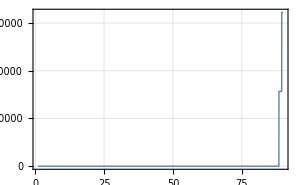

Time used: 0.8825858, total time used: 319.98423
---------------------------------------------

=============================================

Hessian for Up10.

AlphaValList = {1,1,1,1,1,1}

CkValList = {2,4,2,4,2,4}

up10Val

up10Val = 0

Time used: 0.5383583, total time used: 320.522588
---------------------------------------------

dup10Val

dup10Val = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Time used: 0.5943955, total time used: 321.116984
---------------------------------------------

ddup10Val

ddup10Val = (2060.23 | -1821.38 | -2037.25 | 126.141 | -1372.89 | 727.374 | -1665.09 | 253.644 | -1858.7 | -249.77 | -3024.93 | 87.763 | -1580. | 985.825 | -1275.43 | -1014.53 | -1510.92 | 8.23209 | -1679.41 | -74.7429 | 956.889 | -899.903 | -1153.45 | 141.295 | -364.462 | -172.152 | -1215.54 | 1202.25 | 100.685 | 688.43 | 109.628 | -640.015 | 599.973 | -948.922 | -371.369 | -244.355 | -376.933 | -190.737 | 260.235 | -1609.88 | -864.188 | -1038.27 | -394.1 | 493.996 | 505.247 | 513.584 | -1945.86 | 235.332 | 760.891 | -896.332 | -2011.22 | 1422.19 | 1057.69 | 863.739 | -2269.44 | 999.887 | 730.285 | -409.728 | -1262.13 | 1202.42 | 1162.76 | 359.546 | -1633.75 | -230.029 | -559.125 | 1497.44 | -837.002 | -658.469 | -1794.37 | -716.89 | 36.9979 | 500.052 | 404.663 | -609.433 | -13.9195 | -434.357 | -239.056 | -17.9931 | 359.729 | 875.933 | 977.718 | -1240.01 | -1289.53 | -710.72 | -273.609 | 571.797 | -835.395 | -116.048 | 776.696 | 478.49
-1821.38 | 1674.17 | 1645.64 | -254.738 | 1110.66 | -766.404 | 1440.33 | -547.76 | 1558.87 | -114.806 | 2789.42 | -226.277 | 1365.99 | -1041.11 | 965.149 | 911.803 | 1147.77 | -192.947 | 1565.29 | 116.978 | -1048.2 | 687.966 | 931.668 | -329.322 | 244.137 | 180.011 | 914.879 | -1273.18 | -173.85 | -657.269 | -391.175 | 459.175 | -820.413 | 1001.79 | 243.098 | 74.3812 | 305.897 | -1.05868 | -357.457 | 1382.05 | 622.062 | 792.881 | 436.611 | -529.514 | -685.909 | -652.749 | 1652.6 | -51.2644 | -662.723 | 898.282 | 1906.63 | -1307.61 | -922.925 | -860.233 | 2019.5 | -983.257 | -624.053 | 311.411 | 1056.01 | -1076.64 | -1053.45 | -302.27 | 1401.79 | 257.253 | 462.665 | -1384.6 | 609.908 | 614.159 | 1710.93 | 656.759 | 146.131 | -354.921 | -627.351 | 512.668 | 33.979 | 578.812 | 154.713 | 148.312 | -369.26 | -885.342 | -918.994 | 1251.35 | 1372.48 | 692.463 | 264.631 | -594.454 | 788.66 | 38.5072 | -775.906 | -402.278
-2037.25 | 1645.64 | 2406.32 | 234.385 | 1618.13 | -410.297 | 1729.47 | 557.736 | 2052.32 | 1086.22 | 2709.26 | 286.005 | 1643.05 | -550.898 | 1669.64 | 969.275 | 1966.48 | 456.94 | 1463.66 | -50.7898 | -440.778 | 1161.25 | 1363.49 | 371.947 | 557.579 | 103.188 | 1603.66 | -663.562 | 114.009 | -558.021 | 627.324 | 901.579 | 131.318 | 535.325 | 582.234 | 597.202 | 443.419 | 614.035 | 62.1774 | 1698.43 | 1211.49 | 1341.62 | 172.33 | -255.5 | 98.5195 | -12.9294 | 2094.91 | -623.88 | -778.014 | 623.3 | 1670.29 | -1282.37 | -1077.26 | -614.062 | 2213.66 | -742.2 | -776.674 | 532.288 | 1398.48 | -1156.28 | -1087.42 | -394.788 | 1723.33 | 93.3256 | 632.356 | -1330.78 | 1152.82 | 571.946 | 1465.57 | 652.337 | -482.547 | -712.315 | 271.66 | 668.375 | -40.2616 | -55.7858 | 377.834 | -312.33 | -228.339 | -590.404 | -831.623 | 840.737 | 696.893 | 543.604 | 214.136 | -344.23 | 701.986 | 274.669 | -546.286 | -525.362
126.141 | -254.738 | 234.385 | 337.141 | 154.67 | 327.991 | -26.3087 | 757.56 | 82.4425 | 754.839 | -444.723 | 347.336 | -23.1773 | 449.395 | 296.408 | -93.6967 | 340.694 | 427.182 | -284.216 | -119.348 | 522.445 | 193.633 | 133.572 | 478.115 | 158.372 | -72.3959 | 293.888 | 555.718 | 201.96 | 154.632 | 681.87 | 207.122 | 701.742 | -428.494 | 174.311 | 311.15 | 41.4831 | 378.568 | 309.007 | -1.29076 | 274.374 | 225.127 | -224.024 | 243.92 | 579.827 | 485.876 | 37.3532 | -344.67 | 23.1799 | -296.478 | -415.809 | 201.069 | 36.1084 | 273.371 | -167.236 | 287.685 | -5.25103 | 91.5673 | 60.6458 | 103.83 | 128.607 | -13.9719 | -1.2862 | -137.259 | 38.6442 | 229.553 | 247.142 | -113.094 | -393.583 | -95.9124 | -407.139 | -169.3 | 641.578 | 22.9543 | -50.4519 | -472.175 | 115.182 | -304.168 | 139.012 | 306.907 | 184.106 | -429.944 | -609.988 | -189.754 | -68.5865 | 238.148 | -165.183 | 139.687 | 251.232 | -18.567
-1372.89 | 1110.66 | 1618.13 | 154.67 | 1088.18 | -279.337 | 1164.9 | 368.332 | 1381.23 | 724.212 | 1828.69 | 189.329 | 1106.68 | -375.184 | 1121.49 | 653.672 | 1320.94 | 303.656 | 988.405 | -32.9375 | -301.741 | 780.158 | 916.921 | 245.934 | 374.02 | 70.2892 | 1077.09 | -452.075 | 74.9222 | -377.13 | 415.921 | 605.181 | 81.7442 | 364.711 | 390.468 | 399.223 | 298.282 | 409.906 | 38.9863 | 1143.75 | 813.21 | 901.31 | 118.312 | -174.291 | 60.8382 | -13.4046 | 1410.24 | -416.755 | -524.098 | 422.565 | 1128.71 | -865.422 | -725.717 | -416.121 | 1492.18 | -502.54 | -522.921 | 357.529 | 941.078 | -779.58 | -733.455 | -265.694 | 1160.41 | 64.1679 | 425.422 | -898.296 | 773.859 | 386.212 | 990.646 | 440.177 | -320.985 | -477.998 | 176.717 | 449.827 | -26.6222 | -32.9971 | 253.3 | -207.365 | -155.096 | -400.515 | -561.752 | 570.266 | 475.15 | 367.869 | 144.851 | -234.09 | 474.278 | 183.597 | -370.27 | -353.572
727.374 | -766.404 | -410.297 | 327.991 | -279.337 | 500.719 | -522.866 | 728.114 | -487.428 | 574.553 | -1291.44 | 325.237 | -494.611 | 682.837 | -128.079 | -385.441 | -160.703 | 370.064 | -749.129 | -125.217 | 737.014 | -103.726 | -231.578 | 453.869 | 26.7674 | -114.069 | -112.256 | 839.354 | 204.005 | 339.824 | 619.713 | -14.05 | 784.108 | -653.867 | 38.4105 | 194.33 | -77.5759 | 268.458 | 344.058 | -484.748 | -23.5098 | -118.184 | -311.235 | 358.262 | 650.731 | 572.43 | -552.365 | -225.941 | 248.511 | -524.403 | -962.001 | 600.251 | 348.791 | 494.726 | -825.639 | 547.942 | 214.849 | -44.272 | -326.936 | 450.548 | 459.959 | 95.9783 | -491.864 | -187.226 | -134.696 | 647.369 | -38.7283 | -295.127 | -877.732 | -297.889 | -339.279 | 4.50519 | 673.712 | -163.311 | -47.6013 | -536.84 | 27.319 | -267.18 | 227.695 | 527.251 | 452.14 | -742.504 | -912.328 | -376.798 | -141.216 | 376.716 | -393.103 | 85.3586 | 449.526 | 127.753
-1665.09 | 1440.33 | 1729.47 | -26.3087 | 1164.9 | -522.866 | 1363.92 | -35.2467 | 1547.96 | 378.153 | 2386.82 | 7.58028 | 1294.65 | -707.722 | 1117.08 | 813.506 | 1320.86 | 91.2064 | 1316.85 | 34.7493 | -667.257 | 784.792 | 979.614 | -6.607 | 336.387 | 125.574 | 1067.25 | -861.459 | -36.216 | -530.391 | 65.9262 | 574.132 | -332.812 | 683.161 | 345.705 | 272.467 | 319.973 | 243.752 | -143.01 | 1324.22 | 773.841 | 905.774 | 273.513 | -350.112 | -282.724 | -311.525 | 1608.85 | -272.184 | -620.487 | 669.521 | 1559.21 | -1123.77 | -861.629 | -647.988 | 1828.29 | -756.693 | -601.803 | 357.863 | 1051.85 | -965.207 | -926.937 | -298.887 | 1343.34 | 157.864 | 468.655 | -1179.15 | 744.76 | 515.737 | 1385.93 | 567.705 | -123.322 | -449.883 | -186.421 | 506.45 | -0.0634649 | 249.493 | 222.886 | -54.602 | -264.133 | -650.365 | -762.094 | 921.72 | 921.365 | 541.219 | 209.374 | -415.924 | 649.361 | 127.312 | -581.452 | -397.759
253.644 | -547.76 | 557.736 | 757.56 | 368.332 | 728.114 | -35.2467 | 1703.18 | 212.686 | 1704.44 | -958.259 | 781.1 | -29.4385 | 997.926 | 686.334 | -196.667 | 789.598 | 962.215 | -616.278 | -268.272 | 1162.98 | 449.2 | 317.564 | 1075.05 | 361.873 | -161.026 | 679.776 | 1234.37 | 453.28 | 337.99 | 1534.71 | 475.784 | 1572.3 | -952.156 | 397.897 | 704.424 | 98.6263 | 855.576 | 692.187 | 20.3253 | 630.64 | 522.209 | -499.491 | 542.071 | 1298.93 | 1087.47 | 112.744 | -780.231 | 41.0716 | -655.01 | -907.58 | 432.27 | 65.8518 | 603.414 | -343.585 | 633.674 | -22.5535 | 212.378 | 155.202 | 216.35 | 272.771 | -36.7658 | 21.0821 | -305.961 | 95.2988 | 495.359 | 569.265 | -245.214 | -860.672 | -205.633 | -918.104 | -388.889 | 1439.97 | 60.6771 | -113.498 | -1057.76 | 263.092 | -685.235 | 308.008 | 678.814 | 400.566 | -950.755 | -1355.79 | -417.213 | -150.556 | 528.316 | -360.009 | 316.513 | 554.797 | -48.8676
-1858.7 | 1558.87 | 2052.32 | 82.4425 | 1381.23 | -487.428 | 1547.96 | 212.686 | 1794.36 | 683.668 | 2575.81 | 124.532 | 1469.94 | -657.883 | 1374. | 897.155 | 1621.41 | 246.664 | 1408.07 | -0.355851 | -587.289 | 960.364 | 1162.69 | 152.026 | 436.735 | 119.004 | 1316.28 | -797.853 | 25.9749 | -553.931 | 302.888 | 724.403 | -145.628 | 636.524 | 452.696 | 414.808 | 378.952 | 404.552 | -60.1691 | 1510.99 | 974.836 | 1108.98 | 237.222 | -318.316 | -129.18 | -193.29 | 1848.96 | -425.835 | -700.535 | 665.208 | 1640.91 | -1215.59 | -971.477 | -648.347 | 2031.1 | -767.652 | -688.705 | 439.085 | 1220.93 | -1067.09 | -1015.12 | -345.844 | 1532.98 | 134.347 | 547.874 | -1269.3 | 932.695 | 550.927 | 1450.55 | 615.987 | -276.78 | -570.093 | 1.52893 | 585.775 | -16.9265 | 127.058 | 292.899 | -163.938 | -255.066 | -639.857 | -808.418 | 908.505 | 847.953 | 554.406 | 216.086 | -395.216 | 686.057 | 191.989 | -579.794 | -460.239
-249.77 | -114.806 | 1086.22 | 754.839 | 724.212 | 574.553 | 378.153 | 1704.44 | 683.668 | 1831.11 | -241.09 | 788.826 | 362.991 | 790.197 | 1029.96 | 48.6217 | 1195.77 | 996.59 | -221.266 | -259.728 | 968.698 | 690.347 | 616.88 | 1080.55 | 466.378 | -124.172 | 1008.24 | 981.676 | 445.401 | 179.386 | 1565.47 | 653.215 | 1482.36 | -751.752 | 505.483 | 791.961 | 196.289 | 935.472 | 653.602 | 422.075 | 869.748 | 800.572 | -420.153 | 439.6 | 1222.26 | 1000.66 | 601.59 | -868.318 | -146.864 | -456.543 | -441.01 | 94.4307 | -195.06 | 411.114 | 208.6 | 408.612 | -205.271 | 322.439 | 475.381 | -74.9177 | -6.48774 | -127.694 | 428.737 | -260.237 | 238.141 | 141.164 | 799.217 | -90.4981 | -446.334 | -34.8735 | -962.009 | -528.113 | 1393.61 | 214.739 | -114.32 | -989.554 | 332.566 | -706.646 | 230.062 | 486.327 | 172.216 | -677.875 | -1085.88 | -255.984 | -88.107 | 405.881 | -165.57 | 357.372 | 382.336 | -169.874
-3024.93 | 2789.42 | 2709.26 | -444.723 | 1828.69 | -1291.44 | 2386.82 | -958.259 | 2575.81 | -241.09 | 4649.1 | -398.275 | 2263.49 | -1754.53 | 1578.19 | 1516.09 | 1877.64 | -348.452 | 2611.09 | 201.559 | -1771.19 | 1126.08 | 1533.7 | -577.72 | 393.455 | 302.786 | 1495.11 | -2146. | -301.675 | -1099.05 | -693.858 | 746.285 | -1406.02 | 1687.64 | 390.662 | 102.057 | 503.595 | -27.4089 | -612.935 | 2288.61 | 1011.51 | 1297.7 | 737.923 | -893.489 | -1175.08 | -1113.66 | 2734.24 | -61.7083 | -1099.05 | 1507.53 | 3185.4 | -2178.97 | -1530.82 | -1442.96 | 3355.61 | -1647.66 | -1033.1 | 509.546 | 1744.7 | -1789.93 | -1753.2 | -499.627 | 2321.49 | 435.253 | 763.587 | -2308.37 | 993.4 | 1024.67 | 2859.82 | 1094.06 | 269.388 | -576.37 | -1082.07 | 847.449 | 59.6642 | 990.295 | 248.461 | 266.072 | -620.857 | -1486.8 | -1534.27 | 2101.2 | 2313.9 | 1159.51 | 442.85 | -1000.45 | 1317.16 | 54.372 | -1301.83 | -664.935
87.763 | -226.277 | 286.005 | 347.336 | 189.329 | 325.237 | 7.58028 | 781.1 | 124.532 | 788.826 | -398.275 | 358.724 | 9.04768 | 445.849 | 334.425 | -76.0094 | 385.334 | 443.279 | -259.853 | -122.334 | 522.289 | 219.864 | 162.829 | 493.363 | 172.038 | -71.5515 | 330.554 | 551.688 | 207.539 | 146.09 | 705.545 | 228.42 | 715.897 | -424.936 | 188.73 | 328.12 | 50.9577 | 396.983 | 315.32 | 32.3941 | 302.933 | 255.458 | -224.305 | 242.854 | 591.322 | 493.623 | 79.5574 | -362.733 | 8.1164 | -288.988 | -389.499 | 178.923 | 15.3172 | 265.684 | -126.045 | 277.69 | -20.7563 | 103.643 | 89.4079 | 82.5853 | 109.137 | -22.0395 | 32.9047 | -137.667 | 51.8345 | 206.915 | 274.099 | -103.603 | -370.971 | -84.542 | -423.425 | -186.23 | 657.539 | 36.6012 | -52.0822 | -481.06 | 124.58 | -315.379 | 136.769 | 300.242 | 170.629 | -420.336 | -606.201 | -182.088 | -65.4653 | 235.237 | -153.968 | 147.441 | 244.526 | -29.3025
-1580. | 1365.99 | 1643.05 | -23.1773 | 1106.68 | -494.611 | 1294.65 | -29.4385 | 1469.94 | 362.991 | 2263.49 | 9.04768 | 1228.92 | -669.454 | 1062.04 | 771.786 | 1255.72 | 88.8569 | 1248.61 | 32.371 | -630.654 | 746.047 | 930.676 | -3.72868 | 320.187 | 118.84 | 1014.72 | -814.835 | -33.2974 | -502.672 | 66.2053 | 546.137 | -312.214 | 646.277 | 329.116 | 260.315 | 303.987 | 233.412 | -134.112 | 1257.1 | 736.079 | 861.063 | 258.478 | -331.059 | -265.31 | -293.163 | 1527.49 | -260.209 | -588.91 | 634.013 | 1477.97 | -1065.73 | -817.76 | -613.693 | 1734.72 | -716.813 | -571.323 | 340.206 | 998.847 | -915.728 | -879.267 | -283.81 | 1275.24 | 149.136 | 445.102 | -1118.16 | 708.313 | 488.995 | 1313.59 | 538.419 | -119.224 | -427.973 | -173.577 | 480.898 | -0.327102 | 234.348 | 212.196 | -53.4429 | -250.008 | -615.772 | -722.487 | 872.721 | 871.432 | 512.78 | 198.398 | -393.58 | 615.57 | 121.597 | -550.648 | -377.694
985.825 | -1041.11 | -550.898 | 449.395 | -375.184 | 682.837 | -707.722 | 997.926 | -657.883 | 790.197 | -1754.53 | 445.849 | -669.454 | 931.275 | -168.126 | -523.049 | -211.469 | 507.879 | -1018.26 | -171.565 | 1005.83 | -136.996 | -310.965 | 622.115 | 38.8671 | -155.662 | -146.77 | 1144.82 | 279.335 | 462.19 | 849.99 | -15.4788 | 1072.67 | -891.964 | 54.8938 | 268.171 | -104.305 | 369.609 | 470.63 | -655.731 | -27.0903 | -155.997 | -424.981 | 488.696 | 890.146 | 782.716 | -746.381 | -311.629 | 336.502 | -714.432 | -1308.35 | 815.335 | 472.352 | 673.891 | -1119.56 | 746.113 | 290.477 | -58.2652 | -441.093 | 611.163 | 624.325 | 129.559 | -665.236 | -255.624 | -181.488 | 879.56 | -48.0329 | -401.128 | -1193.99 | -404.561 | -466.011 | 3.11671 | 922.431 | -220.464 | -65.2646 | -734.342 | 38.972 | -366.69 | 310.386 | 718.468 | 614.727 | -1011.75 | -1244.59 | -512.93 | -192.191 | 513.67 | -534.55 | 117.898 | 612.371 | 172.451
-1275.43 | 965.149 | 1669.64 | 296.408 | 1121.49 | -128.079 | 1117.08 | 686.334 | 1374. | 1029.96 | 1578.19 | 334.425 | 1062.04 | -168.126 | 1215.43 | 592.445 | 1427.94 | 479.933 | 833.876 | -83.9665 | -65.1856 | 840.003 | 946.382 | 446.166 | 431.159 | 36.4766 | 1171.31 | -196.367 | 160.328 | -298.253 | 699.512 | 676.338 | 384.376 | 166.814 | 454.029 | 522.046 | 306.922 | 561.728 | 172.083 | 1107.48 | 907.154 | 971.089 | 17.037 | -62.8774 | 311.08 | 198.4 | 1382.63 | -553.745 | -497.71 | 280.432 | 912.693 | -751.023 | -687.432 | -284.242 | 1373. | -361.746 | -508.938 | 386.245 | 938.188 | -710.157 | -654.687 | -263.508 | 1123.75 | 2.4552 | 429.001 | -770.482 | 857.309 | 324.995 | 788.595 | 384.756 | -488.132 | -536.786 | 450.349 | 445.821 | -47.7439 | -237.398 | 295.532 | -333.248 | -89.792 | -254.531 | -464.179 | 365.473 | 194.984 | 273.87 | 110.506 | -123.198 | 387.659 | 238.658 | -249.449 | -350.651
-1014.53 | 911.803 | 969.275 | -93.6967 | 653.672 | -385.441 | 813.506 | -196.667 | 897.155 | 48.6217 | 1516.09 | -76.0094 | 771.786 | -523.049 | 592.445 | 503.42 | 702.754 | -45.0697 | 845.574 | 48.4994 | -516.073 | 419.668 | 548.921 | -114.791 | 162.487 | 91.3417 | 563.538 | -638.736 | -68.1521 | -349.616 | -119.205 | 291.862 | -359.802 | 504.066 | 164.298 | 89.1618 | 179.932 | 56.5038 | -156.226 | 784.197 | 394.428 | 483.949 | 214.124 | -263.669 | -301.833 | -297.254 | 943.462 | -81.0014 | -372.599 | 465.117 | 1019.37 | -711.778 | -518.315 | -447.004 | 1120.87 | -514.664 | -354.936 | 190.514 | 608.409 | -595.348 | -578.456 | -173.64 | 795.309 | 125.317 | 268.379 | -751.175 | 383.339 | 331.498 | 911.662 | 358.261 | 21.6111 | -226.912 | -259.391 | 294.392 | 11.6845 | 257.359 | 105.146 | 38.3565 | -188.616 | -456.203 | -493.794 | 645.382 | 687.003 | 364.389 | 139.846 | -301.482 | 422.681 | 42.8902 | -402.484 | -231.086
-1510.92 | 1147.77 | 1966.48 | 340.694 | 1320.94 | -160.703 | 1320.86 | 789.598 | 1621.41 | 1195.77 | 1877.64 | 385.334 | 1255.72 | -211.469 | 1427.94 | 702.754 | 1677.84 | 555.033 | 993.472 | -95.8996 | -91.8841 | 987.177 | 1114.6 | 513.684 | 505.006 | 45.1095 | 1375.88 | -247.856 | 183.706 | -356.903 | 807.316 | 793.377 | 434.327 | 209.228 | 531.583 | 608.089 | 361.494 | 653.074 | 194.565 | 1308.81 | 1064.25 | 1141.2 | 26.431 | -81.2666 | 351.159 | 220.706 | 1632.92 | -644.65 | -588.848 | 339.812 | 1090.39 | -893.251 | -813.426 | -343.659 | 1627.34 | -435.658 | -601.312 | 453.869 | 1107.03 | -842.201 | -777.349 | -311.017 | 1328.08 | 6.78959 | 505.896 | -917.054 | 1006.16 | 387.281 | 943.107 | 457.42 | -565.339 | -629.575 | 514.047 | 526.218 | -54.9944 | -267.181 | 345.995 | -385.215 | -110.053 | -309.497 | -553.779 | 444.092 | 247.71 | 329.034 | 132.538 | -152.34 | 462.812 | 278.088 | -301.915 | -413.871
8.23209 | -192.947 | 456.94 | 427.182 | 303.656 | 370.064 | 91.2064 | 962.215 | 246.664 | 996.59 | -348.452 | 443.279 | 88.8569 | 507.879 | 479.933 | -45.0697 | 555.033 | 552.703 | -241.822 | -149.053 | 604.691 | 318.522 | 259.805 | 608.666 | 232.531 | -80.895 | 472.16 | 629.322 | 253.979 | 148.418 | 875.005 | 316.43 | 863.831 | -483.722 | 253.7 | 421.406 | 82.0467 | 504.706 | 380.641 | 119.459 | 420.428 | 369.738 | -260.612 | 278.725 | 713.028 | 590.762 | 194.886 | -464.22 | -27.2561 | -316.591 | -387.243 | 153.404 | -32.8525 | 289.111 | -45.7884 | 297.404 | -61.7828 | 149.468 | 173.585 | 43.981 | 79.0641 | -45.1687 | 121.332 | -160.494 | 92.156 | 184.638 | 383.175 | -96.9346 | -374.776 | -70.2779 | -530.213 | -256.967 | 800.666 | 75.618 | -64.3099 | -578.978 | 167.21 | -392.68 | 153. | 331.638 | 164.892 | -463.615 | -693.125 | -192.309 | -68.2515 | 265.46 | -151.093 | 189.694 | 266.984 | -60.0763
-1679.41 | 1565.29 | 1463.66 | -284.216 | 988.405 | -749.129 | 1316.85 | -616.278 | 1408.07 | -221.266 | 2611.09 | -259.853 | 1248.61 | -1018.26 | 833.876 | 845.574 | 993.472 | -241.822 | 1470.61 | 125.143 | -1036.02 | 597.145 | 828.539 | -373.988 | 198.095 | 175.332 | 788.45 | -1246.21 | -189.594 | -622.86 | -461.864 | 386.541 | -856.14 | 979.355 | 194.683 | 19.7592 | 272.455 | -59.4201 | -373.483 | 1259.86 | 524.597 | 687.894 | 432.639 | -520.231 | -714.705 | -670.034 | 1500.39 | 6.56983 | -607.584 | 864.527 | 1801.97 | -1222.84 | -846.729 | -826.277 | 1866.42 | -940.613 | -567.945 | 269.659 | 953.058 | -997.295 | -979.99 | -273.325 | 1277.78 | 255.681 | 415.694 | -1297.4 | 517.653 | 577.225 | 1620.18 | 613.394 | 196.133 | -297.295 | -670.96 | 463.692 | 38.7688 | 600.53 | 123.195 | 182.2 | -358.034 | -854.346 | -866.029 | 1206.95 | 1345.18 | 660.444 | 251.787 | -578.602 | 744.318 | 13.4973 | -745.999 | -363.762
-74.7429 | 116.978 | -50.7898 | -119.348 | -32.9375 | -125.217 | 34.7493 | -268.272 | -0.355851 | -259.728 | 201.559 | -122.334 | 32.371 | -171.565 | -83.9665 | 48.4994 | -95.8996 | -149.053 | 125.143 | 43.2941 | -196.671 | -53.695 | -28.8704 | -168.869 | -49.4418 | 28.3462 | -83.9889 | -212.005 | -71.6983 | -64.0146 | -239.635 | -62.3312 | -253.979 | 164.573 | -54.9109 | -104.673 | -8.38322 | -129.054 | -111.534 | 25.1689 | -82.4649 | -62.6201 | 84.7111 | -92.3019 | -209.922 | -177.634 | 16.2882 | 116.965 | -19.5812 | 117.183 | 175.723 | -91.7546 | -28.5782 | -108.613 | 92.7039 | -115.671 | -9.17862 | -25.837 | -2.1686 | -54.44 | -62.5052 | -0.537598 | 25.091 | 51.4623 | -5.07895 | -102.849 | -73.7896 | 49.4752 | 164.681 | 44.3487 | 141.799 | 51.6542 | -230.433 | 1.16586 | 17.8506 | 171.648 | -36.6681 | 106.625 | -54.0315 | -120.522 | -79.1199 | 169.034 | 232.734 | 77.0676 | 28.1082 | -91.8932 | 70.3569 | -47.0916 | -99.5587 | -0.724921
956.889 | -1048.2 | -440.778 | 522.445 | -301.741 | 737.014 | -667.257 | 1162.98 | -587.289 | 968.698 | -1771.19 | 522.289 | -630.654 | 1005.83 | -65.1856 | -516.073 | -91.8841 | 604.691 | -1036.02 | -196.671 | 1097.8 | -67.9079 | -248.447 | 726.788 | 84.9841 | -167.374 | -46.076 | 1237.5 | 322.368 | 478.047 | 1001.86 | 49.4166 | 1215.37 | -962.926 | 104.827 | 345.662 | -84.4107 | 460.928 | 533.54 | -611.121 | 59.3542 | -75.8849 | -464.961 | 530.281 | 1007.77 | 878.818 | -683.538 | -396.552 | 320.518 | -756.79 | -1346.7 | 821.317 | 451.017 | 711.906 | -1094.19 | 783.58 | 268.885 | -26.0059 | -392.053 | 601.179 | 621.082 | 116.34 | -619.895 | -280.4 | -157.086 | 889.914 | 31.5259 | -408.444 | -1233.34 | -406.34 | -559.594 | -49.3356 | 1056.97 | -198.223 | -76.3444 | -829.542 | 71.8321 | -435.33 | 331.938 | 763.766 | 629.267 | -1074.84 | -1347.23 | -536.213 | -200.139 | 551.834 | -548.764 | 152.892 | 647.785 | 154.866
-899.903 | 687.966 | 1161.25 | 193.633 | 780.158 | -103.726 | 784.792 | 449.2 | 960.364 | 690.347 | 1126.08 | 219.864 | 746.047 | -136.996 | 840.003 | 419.668 | 987.177 | 318.522 | 597.145 | -53.695 | -67.9079 | 581.052 | 658.233 | 292.663 | 295.78 | 28.7842 | 809.167 | -161.342 | 103.951 | -215.694 | 461.674 | 465.677 | 239.779 | 135.402 | 311.142 | 353.012 | 213.624 | 377.969 | 107.628 | 776.991 | 624.709 | 671.656 | 21.6189 | -54.4037 | 193.568 | 118.431 | 968.226 | -373.708 | -350.1 | 209.356 | 657.937 | -535.372 | -483.728 | -211.042 | 970.206 | -266.016 | -356.762 | 267.018 | 655.488 | -502.558 | -464.707 | -184.237 | 788.294 | 7.57922 | 299.266 | -550.237 | 590.799 | 232.788 | 569.942 | 273.973 | -325.019 | -369.295 | 288.513 | 311.734 | -31.3363 | -146.37 | 202.381 | -220.772 | -68.915 | -191.633 | -333.446 | 274.701 | 162.798 | 200.199 | 80.4391 | -96.5771 | 278.965 | 161.442 | -185.693 | -245.166
-1153.45 | 931.668 | 1363.49 | 133.572 | 916.921 | -231.578 | 979.614 | 317.564 | 1162.69 | 616.88 | 1533.7 | 162.829 | 930.676 | -310.965 | 946.382 | 548.921 | 1114.6 | 259.805 | 828.539 | -28.8704 | -248.447 | 658.233 | 772.658 | 211.77 | 316.259 | 58.4343 | 909.01 | -374.559 | 65.1199 | -315.598 | 356.823 | 511.191 | 75.9382 | 302.463 | 330.255 | 339.01 | 251.364 | 348.681 | 35.9811 | 962.085 | 686.854 | 760.458 | 97.2866 | -144.076 | 57.1143 | -6.33639 | 1186.58 | -354.05 | -440.601 | 352.42 | 945.169 | -725.892 | -610.058 | -347.234 | 1253.42 | -419.779 | -439.899 | 301.661 | 792.189 | -654.676 | -615.627 | -223.626 | 976.048 | 52.5786 | 358.229 | -753.254 | 653.431 | 323.707 | 829.266 | 369.273 | -274.129 | -403.781 | 155.164 | 378.598 | -22.9056 | -32.5544 | 214.23 | -177.514 | -129.043 | -333.767 | -470.637 | 475.3 | 393.464 | 307.499 | 121.142 | -194.48 | 397.252 | 155.849 | -308.893 | -297.59
141.295 | -329.322 | 371.947 | 478.115 | 245.934 | 453.869 | -6.607 | 1075.05 | 152.026 | 1080.55 | -577.72 | 493.363 | -3.72868 | 622.115 | 446.166 | -114.791 | 513.684 | 608.666 | -373.988 | -168.869 | 726.788 | 292.663 | 211.77 | 678.792 | 232.421 | -100.123 | 441.458 | 769.647 | 285.889 | 207.471 | 969.836 | 307.048 | 989.026 | -593.268 | 255.272 | 447.969 | 66.0277 | 543.075 | 435.512 | 28.0273 | 407.094 | 340.136 | -312.134 | 338.375 | 817.001 | 683.048 | 89.5051 | -495.714 | 18.8652 | -405.929 | -555.262 | 260.124 | 31.7645 | 373.598 | -196.109 | 391.465 | -21.093 | 138.164 | 109.969 | 125.605 | 161.663 | -26.6166 | 28.6087 | -191.377 | 65.5059 | 299.326 | 367.898 | -148.947 | -527.619 | -123.366 | -581.067 | -250.656 | 907.032 | 44.0772 | -71.66 | -664.994 | 168.647 | -433.258 | 191.459 | 421.176 | 244.226 | -589.782 | -845.513 | -257.252 | -92.6722 | 328.826 | -219.904 | 201.287 | 343.66 | -35.3832
-364.462 | 244.137 | 557.579 | 158.372 | 374.02 | 26.7674 | 336.387 | 361.873 | 436.735 | 466.378 | 393.455 | 172.038 | 320.187 | 38.8671 | 431.159 | 162.487 | 505.006 | 232.531 | 198.095 | -49.4418 | 84.9841 | 295.78 | 316.259 | 232.421 | 163.722 | -3.20679 | 417.167 | 51.5522 | 89.6664 | -60.0162 | 350.726 | 248.451 | 258.37 | -34.7617 | 173.91 | 222.141 | 102.305 | 247.789 | 114.724 | 338.468 | 332.498 | 342.169 | -39.5523 | 29.8434 | 211.518 | 158.075 | 430.172 | -238.394 | -147.507 | 26.285 | 195.647 | -189.28 | -202.915 | -32.0825 | 386.209 | -52.9063 | -156.641 | 136.439 | 298.974 | -196.284 | -174.358 | -83.3585 | 343.285 | -26.7708 | 138.898 | -189.517 | 311.642 | 76.6779 | 162.165 | 98.3927 | -230.861 | -198.047 | 266.317 | 140.894 | -24.7118 | -167.249 | 113.442 | -162.865 | 0.422549 | -16.2756 | -104.989 | 25.5217 | -62.6985 | 45.6779 | 20.0306 | 10.0875 | 85.3908 | 100.969 | -25.8853 | -110.92
-172.152 | 180.011 | 103.188 | -72.3959 | 70.2892 | -114.069 | 125.574 | -161.026 | 119.004 | -124.172 | 302.786 | -71.5515 | 118.84 | -155.662 | 36.4766 | 91.3417 | 45.1095 | -80.895 | 175.332 | 28.3462 | -167.374 | 28.7842 | 58.4343 | -100.123 | -3.20679 | 26.5077 | 32.6289 | -191.373 | -45.0197 | -78.5068 | -136.331 | 7.47505 | -175.482 | 149.856 | -5.71948 | -40.7402 | 19.7763 | -57.3476 | -76.7608 | 116.861 | 10.9523 | 32.8227 | 71.1756 | -81.3394 | -145.612 | -128.867 | 133.412 | 48.1274 | -59.3066 | 120.716 | 223.742 | -140.651 | -83.1743 | -113.998 | 195.422 | -126.53 | -51.726 | 12.2785 | 79.6541 | -106.416 | -108.234 | -23.3154 | 118.181 | 42.5365 | 33.0615 | -151.465 | 13.7313 | 68.8997 | 203.889 | 69.871 | 74.2464 | -4.11342 | -150.42 | 39.6574 | 10.5363 | 120.559 | -4.50331 | 58.7629 | -52.2306 | -121.214 | -105.362 | 170.74 | 208.329 | 87.1543 | 32.7089 | -86.2683 | 91.5125 | -18.0126 | -103.532 | -31.0337
-1215.54 | 914.879 | 1603.66 | 293.888 | 1077.09 | -112.256 | 1067.25 | 679.776 | 1316.28 | 1008.24 | 1495.11 | 330.554 | 1014.72 | -146.77 | 1171.31 | 563.538 | 1375.88 | 472.16 | 788.45 | -83.9889 | -46.076 | 809.167 | 909.01 | 441.458 | 417.167 | 32.6289 | 1129.06 | -170.466 | 159.577 | -280.352 | 690.022 | 653.103 | 389.333 | 146.174 | 439.529 | 508.817 | 294.747 | 548.853 | 174.144 | 1058.85 | 875.882 | 935.479 | 9.32757 | -52.5295 | 315.462 | 204.802 | 1323.11 | -540.163 | -475.149 | 258.907 | 859.713 | -711.814 | -656.143 | -263.268 | 1307.55 | -336.926 | -486.768 | 372.143 | 898.904 | -675.765 | -621.959 | -252.379 | 1074.4 | -1.92051 | 411.377 | -729.534 | 827.374 | 307.217 | 741.752 | 364.89 | -479.371 | -518.495 | 450.536 | 426.971 | -47.2176 | -241.662 | 286.145 | -328.082 | -81.5293 | -233.819 | -438.085 | 336.066 | 167.461 | 255.952 | 103.524 | -110.387 | 365.511 | 232.529 | -230.691 | -335.841
1202.25 | -1273.18 | -663.562 | 555.718 | -452.075 | 839.354 | -861.459 | 1234.37 | -797.853 | 981.676 | -2146. | 551.688 | -814.835 | 1144.82 | -196.367 | -638.736 | -247.856 | 629.322 | -1246.21 | -212.005 | 1237.5 | -161.342 | -374.559 | 769.647 | 51.5522 | -191.373 | -170.466 | 1407.45 | 345.185 | 566.249 | 1052.38 | -13.1941 | 1323.73 | -1096.6 | 71.4814 | 334.617 | -125.78 | 459.833 | 580.768 | -797.544 | -25.4615 | -183.581 | -523.068 | 600.943 | 1098.4 | 965.244 | -906.639 | -388.468 | 409.857 | -876.986 | -1602.54 | 997.064 | 575.419 | 827.047 | -1366.1 | 915.27 | 353.102 | -68.3327 | -534.739 | 746.092 | 762.782 | 157.171 | -809.025 | -314.644 | -219.641 | 1075.95 | -51.6021 | -490.926 | -1462.85 | -494.627 | -577.932 | -0.875069 | 1139.44 | -267.472 | -80.7581 | -906.039 | 50.5676 | -454.311 | 381.289 | 882.181 | 752.638 | -1242.23 | -1530.34 | -629. | -235.612 | 631.233 | -654.614 | 147.224 | 751.623 | 209.205
100.685 | -173.85 | 114.009 | 201.96 | 74.9222 | 204.005 | -36.216 | 453.28 | 25.9749 | 445.401 | -301.675 | 207.539 | -33.2974 | 279.335 | 160.328 | -68.1521 | 183.706 | 253.979 | -189.594 | -71.6983 | 322.368 | 103.951 | 65.1199 | 285.889 | 89.6664 | -45.0197 | 159.577 | 345.185 | 121.345 | 100.543 | 406.528 | 115.196 | 424.432 | -266.209 | 99.0488 | 181.912 | 20.0781 | 222.627 | 186.917 | -20.6682 | 152.356 | 120.937 | -137.85 | 151.163 | 350.835 | 295.004 | -2.01884 | -201.81 | 23.2348 | -187.262 | -272.015 | 137.129 | 34.6067 | 173.131 | -127.573 | 183.327 | 5.96577 | 49.2949 | 20.323 | 76.6344 | 90.8588 | -3.82662 | -21.0883 | -84.3947 | 15.9994 | 154.985 | 136.392 | -75.3708 | -256.115 | -65.8913 | -241.385 | -94.3455 | 386.138 | 6.05358 | -30.1421 | -285.88 | 65.4454 | -180.903 | 87.0496 | 193.203 | 121.524 | -270.818 | -378.382 | -121.557 | -44.1449 | 148.576 | -108.513 | 81.5318 | 158.897 | -5.07645
688.43 | -657.269 | -558.021 | 154.632 | -377.13 | 339.824 | -530.391 | 337.99 | -553.931 | 179.386 | -1099.05 | 146.09 | -502.672 | 462.19 | -298.253 | -349.616 | -356.903 | 148.418 | -622.86 | -64.0146 | 478.047 | -215.694 | -315.598 | 207.471 | -60.0162 | -78.5068 | -280.352 | 566.249 | 100.543 | 268.486 | 267.061 | -129.692 | 427.422 | -443.28 | -56.742 | 29.7216 | -103.798 | 69.5147 | 187.034 | -504.562 | -176.963 | -248.288 | -199.75 | 238.047 | 356.163 | 326.613 | -596.725 | -43.8726 | 246.228 | -381.883 | -771.789 | 514.039 | 343.598 | 363.792 | -767.868 | 411.318 | 226.943 | -97.0943 | -374.627 | 412.032 | 408.062 | 107.848 | -512.148 | -118.872 | -161.941 | 547.325 | -177.849 | -244.821 | -696.285 | -257.258 | -127.304 | 98.8668 | 345.614 | -183.051 | -21.571 | -297.124 | -35.5818 | -109.4 | 160.094 | 379.052 | 369.039 | -535.058 | -611.988 | -287.339 | -109.095 | 260.336 | -318.007 | 11.3054 | 328.976 | 143.535
109.628 | -391.175 | 627.324 | 681.87 | 415.921 | 619.713 | 65.9262 | 1534.71 | 302.888 | 1565.47 | -693.858 | 705.545 | 66.2053 | 849.99 | 699.512 | -119.205 | 807.316 | 875.005 | -461.864 | -239.635 | 1001.86 | 461.674 | 356.823 | 969.836 | 350.726 | -136.331 | 690.022 | 1052.38 | 406.528 | 267.061 | 1389.91 | 470.573 | 1395.26 | -810.423 | 383.908 | 655.32 | 111.952 | 789.686 | 614.505 | 113.239 | 624.65 | 536.238 | -431.216 | 464.176 | 1152.12 | 959.19 | 217.039 | -723.712 | -7.39062 | -543.215 | -707.426 | 309.629 | -2.30364 | 498.189 | -179.104 | 517.712 | -63.4776 | 217.327 | 215.449 | 126.109 | 179.775 | -54.6 | 115.284 | -264.838 | 119.594 | 362.603 | 567.163 | -184.366 | -677.504 | -144.919 | -837.485 | -383.233 | 1286.31 | 91.0542 | -102.444 | -936.816 | 253.428 | -622.381 | 259.071 | 566.073 | 306.929 | -792.073 | -1157.67 | -337.781 | -120.884 | 447.036 | -278.402 | 294.796 | 459.076 | -72.6071
-640.015 | 459.175 | 901.579 | 207.122 | 605.181 | -14.05 | 574.132 | 475.784 | 724.403 | 653.215 | 746.285 | 228.42 | 546.137 | -15.4788 | 676.338 | 291.862 | 793.377 | 316.43 | 386.541 | -62.3312 | 49.4166 | 465.677 | 511.191 | 307.048 | 248.451 | 7.47505 | 653.103 | -13.1941 | 115.196 | -129.692 | 470.573 | 383.107 | 310.616 | 18.3291 | 262.822 | 319.782 | 165.563 | 351.039 | 138.298 | 573.14 | 513.27 | 538.534 | -26.6915 | 6.33392 | 253.296 | 179.934 | 721.594 | -341.415 | -253.933 | 98.0221 | 406.314 | -356.77 | -350.079 | -103.667 | 684.09 | -141.508 | -264.265 | 214.48 | 495.253 | -351.076 | -318.426 | -138.615 | 581.459 | -20.5493 | 228.197 | -362.314 | 483.037 | 150.241 | 345.614 | 183.905 | -317.384 | -304.758 | 335.096 | 234.409 | -32.733 | -197.941 | 171.28 | -220.845 | -24.3781 | -82.9576 | -210.994 | 120.822 | 3.95455 | 111.592 | 46.2952 | -25.9094 | 174.395 | 145.737 | -89.178 | -184.451
599.973 | -820.413 | 131.318 | 701.742 | 81.7442 | 784.108 | -332.812 | 1572.3 | -145.628 | 1482.36 | -1406.02 | 715.897 | -312.214 | 1072.67 | 384.376 | -359.802 | 434.327 | 863.831 | -856.14 | -253.979 | 1215.37 | 239.779 | 75.9382 | 989.026 | 258.37 | -175.482 | 389.333 | 1323.73 | 424.432 | 427.422 | 1395.26 | 310.616 | 1517.65 | -1025.03 | 289.406 | 587.1 | 20.184 | 732.266 | 667.409 | -273.019 | 408.851 | 280.183 | -518.972 | 575.155 | 1255.51 | 1067.53 | -250.942 | -656.698 | 174.447 | -749.178 | -1177.21 | 644.672 | 250.343 | 697.04 | -718.451 | 748.787 | 111.888 | 116.224 | -89.2099 | 411.404 | 454.797 | 32.0875 | -276.634 | -315.821 | -15.7302 | 714.827 | 358.788 | -338.878 | -1095.94 | -313.973 | -816.14 | -258.08 | 1363.75 | -55.8595 | -104.238 | -1026.56 | 192.549 | -617.383 | 341.118 | 766.822 | 535.859 | -1076.4 | -1448.36 | -502.481 | -184.426 | 576.925 | -473.765 | 262.677 | 637.722 | 42.7574
-948.922 | 1001.79 | 535.325 | -428.494 | 364.711 | -653.867 | 683.161 | -952.156 | 636.524 | -751.752 | 1687.64 | -424.936 | 646.277 | -891.964 | 166.814 | 504.066 | 209.228 | -483.722 | 979.355 | 164.573 | -962.926 | 135.402 | 302.463 | -593.268 | -34.7617 | 149.856 | 146.174 | -1096.6 | -266.209 | -443.28 | -810.423 | 18.3291 | -1025.03 | 855.56 | -50.0129 | -253.976 | 101.824 | -350.954 | -449.36 | 633.329 | 30.4324 | 154.158 | 407.697 | -467.662 | -850.534 | -748.754 | 720.69 | 296.086 | -324.385 | 685.399 | 1256.88 | -784.037 | -455.295 | -646.589 | 1078.04 | -716.085 | -280.354 | 57.4451 | 426.426 | -588.329 | -600.698 | -125.199 | 641.876 | 244.818 | 175.636 | -845.627 | 49.652 | 385.541 | 1146.83 | 389.083 | 444.215 | -5.27112 | -881.484 | 213.035 | 62.2999 | 702.26 | -36.0644 | 349.756 | -297.636 | -689.153 | -590.694 | 970.495 | 1192.76 | 492.395 | 184.53 | -492.461 | 513.584 | -111.893 | -587.524 | -166.648
-371.369 | 243.098 | 582.234 | 174.311 | 390.468 | 38.4105 | 345.705 | 397.897 | 452.696 | 505.483 | 390.662 | 188.73 | 329.116 | 54.8938 | 454.029 | 164.298 | 531.583 | 253.7 | 194.683 | -54.9109 | 104.827 | 311.142 | 330.255 | 255.272 | 173.91 | -5.71948 | 439.529 | 71.4814 | 99.0488 | -56.742 | 383.908 | 262.822 | 289.406 | -50.0129 | 184.934 | 239.155 | 106.761 | 267.813 | 128.408 | 348.677 | 351.645 | 359.981 | -48.1843 | 38.7985 | 237.099 | 178.946 | 444.463 | -257.032 | -151.217 | 17.2741 | 187.828 | -188.372 | -207.878 | -24.0121 | 392.396 | -44.9943 | -161.568 | 143.609 | 310.053 | -198.805 | -175.394 | -86.3504 | 353.661 | -32.1242 | 144.392 | -187.674 | 329.276 | 75.2633 | 154.066 | 98.2055 | -251.337 | -209.658 | 295.625 | 145.93 | -27.1308 | -187.946 | 120.695 | -177.871 | 5.03435 | -6.61596 | -102.085 | 12.0722 | -84.7817 | 40.7864 | 18.3694 | 18.2724 | 82.5173 | 108.654 | -18.3593 | -114.901
-244.355 | 74.3812 | 597.202 | 311.15 | 399.223 | 194.33 | 272.467 | 704.424 | 414.808 | 791.961 | 102.057 | 328.12 | 260.315 | 268.171 | 522.046 | 89.1618 | 608.089 | 421.406 | 19.7592 | -104.673 | 345.662 | 353.012 | 339.01 | 447.969 | 222.141 | -40.7402 | 508.817 | 334.617 | 181.912 | 29.7216 | 655.32 | 319.782 | 587.1 | -253.976 | 239.155 | 351.831 | 108.68 | 408.951 | 259.269 | 287.332 | 426.527 | 408.985 | -151.039 | 152.948 | 483.408 | 388.862 | 385.742 | -383.331 | -113.437 | -132.795 | -51.0781 | -55.8924 | -153.837 | 115.766 | 241.24 | 105.531 | -136.092 | 164.071 | 286.248 | -112.748 | -81.1153 | -78.2732 | 291.555 | -94.6276 | 138.465 | -41.1867 | 394.64 | 6.08219 | -67.947 | 33.56 | -409.613 | -257.2 | 562.497 | 131.953 | -47.4419 | -389.501 | 156.854 | -297.838 | 73.1157 | 146.774 | 6.98332 | -203.298 | -372.629 | -60.4293 | -18.8454 | 133.229 | -13.7632 | 159.061 | 109.455 | -104.141
-376.933 | 305.897 | 443.419 | 41.4831 | 298.282 | -77.5759 | 319.973 | 98.6263 | 378.952 | 196.289 | 503.595 | 50.9577 | 303.987 | -104.305 | 306.922 | 179.932 | 361.494 | 82.0467 | 272.455 | -8.38322 | -84.4107 | 213.624 | 251.364 | 66.0277 | 102.305 | 19.7763 | 294.747 | -125.78 | 20.0781 | -103.798 | 111.952 | 165.563 | 20.184 | 101.824 | 106.761 | 108.68 | 81.9349 | 111.373 | 9.83901 | 314.084 | 222.408 | 246.757 | 33.4895 | -48.4543 | 14.8782 | -5.39512 | 386.838 | -113.139 | -143.894 | 116.999 | 311.187 | -238.182 | -199.264 | -115.149 | 410.045 | -138.913 | -143.471 | 97.7824 | 258.017 | -214.284 | -201.714 | -72.8571 | 318.421 | 18.0927 | 116.599 | -247.303 | 211.473 | 106.376 | 273.224 | 121.123 | -86.6394 | -130.564 | 46.2241 | 123.351 | -7.12683 | -7.38592 | 69.0983 | -55.8261 | -43.0495 | -110.986 | -154.795 | 158. | 132.536 | 101.614 | 39.9895 | -65.0756 | 130.725 | 49.8852 | -102.49 | -96.9543
-190.737 | -1.05868 | 614.035 | 378.568 | 409.906 | 268.458 | 243.752 | 855.576 | 404.552 | 935.472 | -27.4089 | 396.983 | 233.412 | 369.609 | 561.728 | 56.5038 | 653.074 | 504.706 | -59.4201 | -129.054 | 460.928 | 377.969 | 348.681 | 543.075 | 247.789 | -57.3476 | 548.853 | 459.833 | 222.627 | 69.5147 | 789.686 | 351.039 | 732.266 | -350.954 | 267.813 | 408.951 | 111.373 | 479.966 | 323.098 | 264.273 | 467.724 | 438.125 | -200.332 | 207.395 | 603.477 | 490.806 | 365.535 | -447.178 | -98.1708 | -203.235 | -160.523 | 3.38239 | -131.859 | 181.243 | 176.59 | 175.721 | -126.799 | 176.128 | 280.238 | -75.5277 | -39.6269 | -75.9171 | 268.226 | -124.626 | 138.098 | 24.7021 | 430.981 | -25.2596 | -169.997 | 4.74143 | -488.435 | -283.13 | 693.246 | 127.817 | -57.4707 | -487.656 | 175.924 | -357.37 | 105.288 | 218.959 | 56.6739 | -304.604 | -509.721 | -107.449 | -36.0768 | 187.717 | -57.7556 | 184.644 | 169.387 | -101.
260.235 | -357.457 | 62.1774 | 309.007 | 38.9863 | 344.058 | -143.01 | 692.187 | -60.1691 | 653.602 | -612.935 | 315.32 | -134.112 | 470.63 | 172.083 | -156.226 | 194.565 | 380.641 | -373.483 | -111.534 | 533.54 | 107.628 | 35.9811 | 435.512 | 114.724 | -76.7608 | 174.144 | 580.768 | 186.917 | 187.034 | 614.505 | 138.298 | 667.409 | -449.36 | 128.408 | 259.269 | 9.83901 | 323.098 | 293.611 | -116.787 | 182.024 | 125.706 | -227.599 | 252.501 | 552.144 | 469.148 | -106.557 | -289.726 | 75.2828 | -328.149 | -514.402 | 281.046 | 108.106 | 305.251 | -311.812 | 327.765 | 47.7909 | 52.0276 | -36.7167 | 178.75 | 197.944 | 13.3992 | -118.51 | -138.635 | -5.78719 | 311.792 | 159.738 | -147.916 | -479.05 | -136.827 | -359.548 | -114.693 | 599.841 | -23.3596 | -45.8838 | -451.268 | 85.2967 | -271.892 | 149.512 | 335.962 | 234.025 | -471.574 | -635.306 | -219.869 | -80.6727 | 252.942 | -206.967 | 115.934 | 279.302 | 17.856
-1609.88 | 1382.05 | 1698.43 | -1.29076 | 1143.75 | -484.748 | 1324.22 | 20.3253 | 1510.99 | 422.075 | 2288.61 | 32.3941 | 1257.1 | -655.731 | 1107.48 | 784.197 | 1308.81 | 119.459 | 1259.86 | 25.1689 | -611.121 | 776.991 | 962.085 | 28.0273 | 338.468 | 116.861 | 1058.85 | -797.544 | -20.6682 | -504.562 | 113.239 | 573.14 | -273.019 | 633.329 | 348.677 | 287.332 | 314.084 | 264.273 | -116.787 | 1287.42 | 772.163 | 896.89 | 249.771 | -322.842 | -233.106 | -267.869 | 1566.96 | -289.488 | -601.623 | 629.598 | 1486.03 | -1078.13 | -835.152 | -610.327 | 1765.58 | -714.988 | -585.506 | 354.548 | 1027.07 | -930.978 | -891.982 | -291.613 | 1306.03 | 143.596 | 458.455 | -1129.93 | 741.939 | 493.294 | 1319.16 | 545.06 | -149.254 | -449.622 | -135.007 | 494.072 | -3.69858 | 208.543 | 225.013 | -75.0153 | -246.794 | -610.22 | -727.706 | 865.188 | 851.863 | 512.544 | 198.629 | -387.232 | 619.461 | 133.854 | -547.231 | -388.076
-864.188 | 622.062 | 1211.49 | 274.374 | 813.21 | -23.5098 | 773.841 | 630.64 | 974.836 | 869.748 | 1011.51 | 302.933 | 736.079 | -27.0903 | 907.154 | 394.428 | 1064.25 | 420.428 | 524.597 | -82.4649 | 59.3542 | 624.709 | 686.854 | 407.094 | 332.498 | 10.9523 | 875.882 | -25.4615 | 152.356 | -176.963 | 624.65 | 513.27 | 408.851 | 30.4324 | 351.645 | 426.527 | 222.408 | 467.724 | 182.024 | 772.163 | 687.736 | 722.449 | -33.0166 | 5.10191 | 333.28 | 235.819 | 971.772 | -455.325 | -342.467 | 136.118 | 553.14 | -483.456 | -472.191 | -143.409 | 924.028 | -194.592 | -356.001 | 287.743 | 666.481 | -474.458 | -430.802 | -186.58 | 783.479 | -25.8168 | 306.947 | -491.315 | 647.479 | 203.977 | 471.049 | 249.103 | -422.094 | -408.324 | 442.763 | 315.531 | -43.4167 | -260.269 | 229.213 | -293.422 | -34.7426 | -115.962 | -286.806 | 168.659 | 13.6454 | 152.947 | 63.3137 | -38.1576 | 237.234 | 194.463 | -123.585 | -248.277
-1038.27 | 792.881 | 1341.62 | 225.127 | 901.31 | -118.184 | 905.774 | 522.209 | 1108.98 | 800.572 | 1297.7 | 255.458 | 861.063 | -155.997 | 971.089 | 483.949 | 1141.2 | 369.738 | 687.894 | -62.6201 | -75.8849 | 671.656 | 760.458 | 340.136 | 342.169 | 32.8227 | 935.479 | -183.581 | 120.937 | -248.288 | 536.238 | 538.534 | 280.183 | 154.158 | 359.981 | 408.985 | 246.757 | 438.125 | 125.706 | 896.89 | 722.449 | 776.402 | 23.8088 | -61.6595 | 226.241 | 139.095 | 1117.89 | -433.091 | -404.037 | 240.226 | 757.477 | -617.042 | -558.233 | -242.285 | 1119.17 | -305.677 | -411.867 | 308.69 | 756.984 | -579.638 | -535.822 | -212.749 | 909.99 | 8.07729 | 345.658 | -634.062 | 683.221 | 268.174 | 656.006 | 315.802 | -377.191 | -427.138 | 336.196 | 359.974 | -36.4212 | -171.28 | 234.19 | -256.345 | -78.8739 | -219.716 | -384.025 | 315.006 | 184.945 | 230.178 | 92.522 | -110.321 | 321.225 | 187.051 | -213.131 | -283.107
-394.1 | 436.611 | 172.33 | -224.024 | 118.312 | -311.235 | 273.513 | -499.491 | 237.222 | -420.153 | 737.923 | -224.305 | 258.478 | -424.981 | 17.037 | 214.124 | 26.431 | -260.612 | 432.639 | 84.7111 | -464.961 | 21.6189 | 97.2866 | -312.134 | -39.5523 | 71.1756 | 9.32757 | -523.068 | -137.85 | -199.75 | -431.216 | -26.6915 | -518.972 | 407.697 | -48.1843 | -151.039 | 33.4895 | -200.332 | -227.599 | 249.771 | -33.0166 | 23.8088 | 197.678 | -224.072 | -430.18 | -374.868 | 277.543 | 173.39 | -131.517 | 318.697 | 563.341 | -341.794 | -185.182 | -299.609 | 451.951 | -329.327 | -109.497 | 7.51441 | 157.864 | -248.719 | -257.673 | -46.9813 | 252.889 | 119.007 | 62.7675 | -370.736 | -21.2069 | 170.418 | 516.355 | 168.979 | 242.002 | 25.8418 | -452.792 | 80.0767 | 32.8438 | 354.306 | -33.1898 | 187.838 | -140.088 | -321.895 | -262.887 | 452.934 | 570.118 | 225.122 | 83.9504 | -233.128 | 229.412 | -67.0806 | -272.708 | -62.5401
493.996 | -529.514 | -255.5 | 243.92 | -174.291 | 358.262 | -350.112 | 542.071 | -318.316 | 439.6 | -893.489 | 242.854 | -331.059 | 488.696 | -62.8774 | -263.669 | -81.2666 | 278.725 | -520.231 | -92.3019 | 530.281 | -54.4037 | -144.076 | 338.375 | 29.8434 | -81.3394 | -52.5295 | 600.943 | 151.163 | 238.047 | 464.176 | 6.33392 | 575.155 | -467.662 | 38.7985 | 152.948 | -48.4543 | 207.395 | 252.501 | -322.842 | 5.10191 | -61.6595 | -224.072 | 257.055 | 477.143 | 417.834 | -365.043 | -176.443 | 167.247 | -371.577 | -671.996 | 414.9 | 235.005 | 350.072 | -562.452 | 386.591 | 142.687 | -22.5835 | -213.159 | 307.875 | 316.01 | 62.8657 | -327.663 | -135.03 | -86.791 | 448.426 | -7.16797 | -205.068 | -614.201 | -205.612 | -256.63 | -9.75766 | 497.019 | -107.03 | -35.5029 | -393.1 | 26.8734 | -200.854 | 162.113 | 374.26 | 314.985 | -526.883 | -653.549 | -265.235 | -99.2138 | 268.827 | -274.242 | 67.3725 | 318.302 | 83.6804
505.247 | -685.909 | 98.5195 | 579.827 | 60.8382 | 650.731 | -282.724 | 1298.93 | -129.18 | 1222.26 | -1175.08 | 591.322 | -265.31 | 890.146 | 311.08 | -301.833 | 351.159 | 713.028 | -714.705 | -209.922 | 1007.77 | 193.568 | 57.1143 | 817.001 | 211.518 | -145.612 | 315.462 | 1098.4 | 350.835 | 356.163 | 1152.12 | 253.296 | 1255.51 | -850.534 | 237.099 | 483.408 | 14.8782 | 603.477 | 552.144 | -233.106 | 333.28 | 226.241 | -430.18 | 477.143 | 1038.71 | 883.546 | -216.575 | -540.839 | 147.677 | -622.67 | -981.358 | 538.979 | 211.759 | 579.481 | -603.993 | 622.852 | 95.8967 | 93.9276 | -79.7683 | 345.39 | 381.009 | 28.232 | -236.261 | -261.772 | -15.7033 | 597.245 | 292.04 | -282.886 | -913.232 | -262.616 | -673.394 | -210.564 | 1127.49 | -49.0674 | -86.0974 | -849.354 | 157.75 | -509.624 | 283.28 | 637.133 | 447.011 | -894.406 | -1201.63 | -418.164 | -153.541 | 478.928 | -395.072 | 216.227 | 530.102 | 37.6169
513.584 | -652.749 | -12.9294 | 485.876 | -13.4046 | 572.43 | -311.525 | 1087.47 | -193.29 | 1000.66 | -1113.66 | 493.623 | -293.163 | 782.716 | 198.4 | -297.254 | 220.706 | 590.762 | -670.034 | -177.634 | 878.818 | 118.431 | -6.33639 | 683.048 | 158.075 | -128.867 | 204.802 | 965.244 | 295.004 | 326.613 | 959.19 | 179.934 | 1067.53 | -748.754 | 178.946 | 388.862 | -5.39512 | 490.806 | 469.148 | -267.869 | 235.819 | 139.095 | -374.868 | 417.834 | 883.546 | 755.678 | -269.441 | -437.133 | 157.539 | -557.282 | -905.998 | 512.285 | 224.356 | 519.997 | -605.343 | 562.224 | 113.229 | 58.8503 | -124.477 | 341.75 | 369.421 | 40.0228 | -271.307 | -227.491 | -38.8785 | 564.033 | 203.194 | -264.805 | -839.53 | -250.716 | -556.116 | -151.291 | 952.718 | -68.8446 | -71.9657 | -723.687 | 119.617 | -422.996 | 251.309 | 568.319 | 415.534 | -798.285 | -1055.08 | -379.285 | -139.851 | 423.192 | -365.924 | 173.749 | 475.065 | 53.3005
-1945.86 | 1652.6 | 2094.91 | 37.3532 | 1410.24 | -552.365 | 1608.85 | 112.744 | 1848.96 | 601.59 | 2734.24 | 79.5574 | 1527.49 | -746.381 | 1382.63 | 943.462 | 1632.92 | 194.886 | 1500.39 | 16.2882 | -683.538 | 968.226 | 1186.58 | 89.5051 | 430.172 | 133.412 | 1323.11 | -906.639 | -2.01884 | -596.725 | 217.039 | 721.594 | -250.942 | 720.69 | 444.463 | 385.742 | 386.838 | 365.535 | -106.557 | 1566.96 | 971.772 | 1117.89 | 277.543 | -365.043 | -216.575 | -269.441 | 1912.27 | -392.706 | -729.821 | 731.983 | 1760.83 | -1289.25 | -1012.65 | -711.216 | 2130.22 | -836.979 | -713.516 | 442.379 | 1257.63 | -1121.42 | -1071.05 | -356.694 | 1590.05 | 158.819 | 562.718 | -1348.99 | 932.22 | 587.427 | 1560.25 | 652.462 | -229.251 | -567.213 | -89.4965 | 604.253 | -10.3921 | 198.806 | 287.416 | -126.84 | -284.266 | -707.172 | -864.554 | 1003.26 | 966.017 | 601.917 | 233.842 | -443.691 | 734.966 | 179.282 | -636.975 | -474.682
235.332 | -51.2644 | -623.88 | -344.67 | -416.755 | -225.941 | -272.184 | -780.231 | -425.835 | -868.318 | -61.7083 | -362.733 | -260.209 | -311.629 | -553.745 | -81.0014 | -644.65 | -464.22 | 6.56983 | 116.965 | -396.552 | -373.708 | -354.05 | -495.714 | -238.394 | 48.1274 | -540.163 | -388.468 | -201.81 | -43.8726 | -723.712 | -341.415 | -656.698 | 296.086 | -257.032 | -383.331 | -113.139 | -447.178 | -289.726 | -289.488 | -455.325 | -433.091 | 173.39 | -176.443 | -540.839 | -437.133 | -392.706 | 418.556 | 112.34 | 161.295 | 89.8136 | 37.8981 | 151.92 | -141.984 | -228.053 | -132.973 | 137.819 | -173.998 | -294.445 | 104.222 | 70.0205 | 80.2744 | -294.101 | 108.125 | -143.288 | 20.4364 | -420.993 | 4.27077 | 104.791 | -25.0395 | 450.828 | 275.132 | -626.685 | -135.271 | 52.5188 | 436.517 | -168.888 | 328.554 | -86.5778 | -176.362 | -23.9912 | 244.726 | 432.174 | 78.4454 | 25.3299 | -156.364 | 29.0915 | -173.37 | -133.577 | 106.801
760.891 | -662.723 | -778.014 | 23.1799 | -524.098 | 248.511 | -620.487 | 41.0716 | -700.535 | -146.864 | -1099.05 | 8.1164 | -588.91 | 336.502 | -497.71 | -372.599 | -588.848 | -27.2561 | -607.584 | -19.5812 | 320.518 | -350.1 | -440.601 | 18.8652 | -147.507 | -59.3066 | -475.149 | 409.857 | 23.2348 | 246.228 | -7.39062 | -253.933 | 174.447 | -324.385 | -151.217 | -113.437 | -143.894 | -98.1708 | 75.2828 | -601.623 | -342.467 | -404.037 | -131.517 | 167.247 | 147.677 | 157.539 | -729.821 | 112.34 | 282.708 | -313.979 | -722.172 | 517.246 | 392.706 | 303.434 | -836.264 | 353.3 | 273.282 | -159.598 | -475.957 | 441.999 | 425.424 | 135.353 | -610.448 | -76.2477 | -211.682 | 543.351 | -330.284 | -238.068 | -642.706 | -261.116 | 42.6433 | 198.854 | 105.814 | -229.372 | -1.63084 | -128.901 | -97.4886 | 14.8047 | 124.593 | 305.617 | 352.347 | -432.967 | -438.728 | -252.169 | -97.3945 | 196.827 | -300.499 | -53.2545 | 272.473 | 180.128
-896.332 | 898.282 | 623.3 | -296.478 | 422.565 | -524.403 | 669.521 | -655.01 | 665.208 | -456.543 | 1507.53 | -288.988 | 634.013 | -714.432 | 280.432 | 465.117 | 339.812 | -316.591 | 864.527 | 117.183 | -756.79 | 209.356 | 352.42 | -405.929 | 26.285 | 120.716 | 258.907 | -876.986 | -187.262 | -381.883 | -543.215 | 98.0221 | -749.178 | 685.399 | 17.2741 | -132.795 | 116.999 | -203.235 | -328.149 | 629.598 | 136.118 | 240.226 | 318.697 | -371.577 | -622.67 | -557.282 | 731.983 | 161.295 | -313.979 | 567.558 | 1090.31 | -702.712 | -439.305 | -537.867 | 1008.53 | -601.515 | -281.153 | 92.6551 | 448.036 | -545.526 | -548.245 | -130.059 | 638.551 | 190.582 | 189.829 | -752.999 | 145.149 | 340.043 | 989.354 | 350.224 | 284.578 | -70.816 | -629.126 | 220.986 | 42.4861 | 516.299 | 8.70308 | 230.414 | -242.488 | -567.256 | -516.791 | 799.709 | 951.265 | 416.737 | 157.155 | -398.061 | 447.348 | -57.3008 | -487.637 | -173.105
-2011.22 | 1906.63 | 1670.29 | -415.809 | 1128.71 | -962.001 | 1559.21 | -907.58 | 1640.91 | -441.01 | 3185.4 | -389.499 | 1477.97 | -1308.35 | 912.693 | 1019.37 | 1090.39 | -387.243 | 1801.97 | 175.723 | -1346.7 | 657.937 | 945.169 | -555.262 | 195.647 | 223.742 | 859.713 | -1602.54 | -272.015 | -771.789 | -707.426 | 406.314 | -1177.21 | 1256.88 | 187.828 | -51.0781 | 311.187 | -160.523 | -514.402 | 1486.03 | 553.14 | 757.477 | 563.341 | -671.996 | -981.358 | -905.998 | 1760.83 | 89.8136 | -722.172 | 1090.31 | 2224.45 | -1490.22 | -1007.32 | -1039.69 | 2241.28 | -1177.96 | -668.648 | 296.265 | 1109.7 | -1201.04 | -1186.53 | -319.064 | 1507.46 | 334.259 | 481.115 | -1584.96 | 551.735 | 707.771 | 2004.73 | 746.342 | 328.279 | -310.354 | -944.163 | 541.465 | 57.7407 | 820.756 | 117.886 | 287.328 | -455.403 | -1080.79 | -1065.33 | 1525.98 | 1731.89 | 824.181 | 313.316 | -739.17 | 917.262 | -17.3386 | -939.732 | -424.641
1422.19 | -1307.61 | -1282.37 | 201.069 | -865.422 | 600.251 | -1123.77 | 432.27 | -1215.59 | 94.4307 | -2178.97 | 178.923 | -1065.73 | 815.335 | -751.023 | -711.778 | -893.251 | 153.404 | -1222.84 | -91.7546 | 821.317 | -535.372 | -725.892 | 260.124 | -189.28 | -140.651 | -711.814 | 997.064 | 137.129 | 514.039 | 309.629 | -356.77 | 644.672 | -784.037 | -188.372 | -55.8924 | -238.182 | 3.38239 | 281.046 | -1078.13 | -483.456 | -617.042 | -341.794 | 414.9 | 538.979 | 512.285 | -1289.25 | 37.8981 | 517.246 | -702.712 | -1490.22 | 1021.52 | 720.353 | 672.883 | -1576.78 | 768.962 | 486.899 | -242.427 | -823.602 | 840.706 | 822.762 | 235.767 | -1093.78 | -201.564 | -360.769 | 1081.76 | -474.387 | -479.9 | -1337.39 | -513.035 | -116.505 | 275.902 | 493.417 | -399.88 | -26.8205 | -454.51 | -120.016 | -117.579 | 288.971 | 692.679 | 718.188 | -979.018 | -1074.63 | -541.467 | -206.902 | 465.288 | -616.377 | -29.1942 | 606.95 | 313.773
1057.69 | -922.925 | -1077.26 | 36.1084 | -725.717 | 348.791 | -861.629 | 65.8518 | -971.477 | -195.06 | -1530.82 | 15.3172 | -817.76 | 472.352 | -687.432 | -518.315 | -813.426 | -32.8525 | -846.729 | -28.5782 | 451.017 | -483.728 | -610.058 | 31.7645 | -202.915 | -83.1743 | -656.143 | 575.419 | 34.6067 | 343.598 | -2.30364 | -350.079 | 250.343 | -455.295 | -207.878 | -153.837 | -199.264 | -131.859 | 108.106 | -835.152 | -472.191 | -558.233 | -185.182 | 235.005 | 211.759 | 224.356 | -1012.65 | 151.92 | 392.706 | -439.305 | -1007.32 | 720.353 | 545.55 | 424.398 | -1162.8 | 493.786 | 379.291 | -220.475 | -659.984 | 614.765 | 592.047 | 187.724 | -847.398 | -107.444 | -293.392 | 756.922 | -455.593 | -331.79 | -896.756 | -363.584 | 54.4421 | 274.06 | 154.373 | -318.132 | -2.85274 | -184.443 | -133.983 | 17.0005 | 174.575 | 427.82 | 491.253 | -606.034 | -616.133 | -352.258 | -135.997 | 276.002 | -419.061 | -72.2938 | 381.161 | 249.825
863.739 | -860.233 | -614.062 | 273.371 | -416.121 | 494.726 | -647.988 | 603.414 | -648.347 | 411.114 | -1442.96 | 265.684 | -613.693 | 673.891 | -284.242 | -447.004 | -343.659 | 289.111 | -826.277 | -108.613 | 711.906 | -211.042 | -347.234 | 373.598 | -32.0825 | -113.998 | -263.268 | 827.047 | 173.131 | 363.792 | 498.189 | -103.667 | 697.04 | -646.589 | -24.0121 | 115.766 | -115.149 | 181.243 | 305.251 | -610.327 | -143.409 | -242.285 | -299.609 | 350.072 | 579.481 | 519.997 | -711.216 | -141.984 | 303.434 | -537.867 | -1039.69 | 672.883 | 424.398 | 510.047 | -970.781 | 571.156 | 272.797 | -93.6523 | -436.902 | 524.551 | 526.153 | 126.676 | -619.021 | -179.038 | -185.653 | 720.447 | -151.041 | -324.949 | -942.744 | -335.537 | -258.898 | 75.725 | 583.149 | -215.204 | -39.0836 | -480.836 | -13.2469 | -210.686 | 229.287 | 537.14 | 493.341 | -757.365 | -896.781 | -396.103 | -149.497 | 375.976 | -426.807 | 49.7206 | 462.273 | 168.601
-2269.44 | 2019.5 | 2213.66 | -167.236 | 1492.18 | -825.639 | 1828.29 | -343.585 | 2031.1 | 208.6 | 3355.61 | -126.045 | 1734.72 | -1119.56 | 1373. | 1120.87 | 1627.34 | -45.7884 | 1866.42 | 92.7039 | -1094.19 | 970.206 | 1253.42 | -196.109 | 386.209 | 195.422 | 1307.55 | -1366.1 | -127.573 | -767.868 | -179.104 | 684.09 | -718.451 | 1078.04 | 392.396 | 241.24 | 410.045 | 176.59 | -311.812 | 1765.58 | 924.028 | 1119.17 | 451.951 | -562.452 | -603.993 | -605.343 | 2130.22 | -228.053 | -836.264 | 1008.53 | 2241.28 | -1576.78 | -1162.8 | -970.781 | 2502.78 | -1121.3 | -800.236 | 441.269 | 1378.54 | -1327.37 | -1286.04 | -392.995 | 1791.37 | 264.14 | 609.67 | -1661.76 | 896.21 | 731.785 | 2001.59 | 794.345 | -5.16659 | -533.542 | -499.458 | 666.193 | 19.648 | 517.286 | 252.089 | 46.1735 | -406.497 | -987.066 | -1087.99 | 1396.94 | 1466.89 | 795.739 | 305.951 | -647.63 | 930.298 | 115.091 | -873.421 | -523.008
999.887 | -983.257 | -742.2 | 287.685 | -502.54 | 547.942 | -756.693 | 633.674 | -767.652 | 408.612 | -1647.66 | 277.69 | -716.813 | 746.113 | -361.746 | -514.664 | -435.658 | 297.404 | -940.613 | -115.671 | 783.58 | -266.016 | -419.779 | 391.465 | -52.9063 | -126.53 | -336.926 | 915.27 | 183.327 | 411.318 | 517.712 | -141.508 | 748.787 | -716.085 | -44.9943 | 105.531 | -138.913 | 175.721 | 327.765 | -714.988 | -194.592 | -305.677 | -329.327 | 386.591 | 622.852 | 562.224 | -836.979 | -132.973 | 353.3 | -601.515 | -1177.96 | 768.962 | 493.786 | 571.156 | -1121.3 | 641.372 | 320.156 | -118.608 | -517.812 | 604.577 | 604.054 | 149.785 | -725.207 | -196.486 | -221.281 | 821.935 | -200.926 | -369.798 | -1066.52 | -383.869 | -263.913 | 105.134 | 621.135 | -254.388 | -40.9075 | -517.666 | -26.6821 | -217.398 | 255.196 | 599.651 | 560.229 | -845.777 | -991.691 | -445.744 | -168.527 | 417.471 | -484.102 | 44.7251 | 517.322 | 199.355
730.285 | -624.053 | -776.674 | -5.25103 | -522.921 | 214.849 | -601.803 | -22.5535 | -688.705 | -205.271 | -1033.1 | -20.7563 | -571.323 | 290.477 | -508.938 | -354.936 | -601.312 | -61.7828 | -567.945 | -9.17862 | 268.885 | -356.762 | -439.899 | -21.093 | -156.641 | -51.726 | -486.768 | 353.102 | 5.96577 | 226.943 | -63.4776 | -264.265 | 111.888 | -280.354 | -161.568 | -136.092 | -143.471 | -126.799 | 47.7909 | -585.506 | -356.001 | -411.867 | -109.497 | 142.687 | 95.8967 | 113.229 | -713.516 | 137.819 | 273.282 | -281.153 | -668.648 | 486.899 | 379.291 | 272.797 | -800.236 | 320.156 | 266.455 | -162.92 | -468.32 | 421.682 | 403.501 | 132.91 | -594.123 | -62.887 | -209.25 | 509.958 | -341.918 | -222.403 | -593.128 | -246.258 | 75.1324 | 207.552 | 50.0204 | -225.174 | 2.57887 | -86.4833 | -104.41 | 39.53 | 109.803 | 272.153 | 327.782 | -385.959 | -376.698 | -229.799 | -89.143 | 171.931 | -278.875 | -63.3751 | 244.486 | 176.876
-409.728 | 311.411 | 532.288 | 91.5673 | 357.529 | -44.272 | 357.863 | 212.378 | 439.085 | 322.439 | 509.546 | 103.643 | 340.206 | -58.2652 | 386.245 | 190.514 | 453.869 | 149.468 | 269.659 | -25.837 | -26.0059 | 267.018 | 301.661 | 138.164 | 136.439 | 12.2785 | 372.143 | -68.3327 | 49.2949 | -97.0943 | 217.327 | 214.48 | 116.224 | 57.4451 | 143.609 | 164.071 | 97.7824 | 176.128 | 52.0276 | 354.548 | 287.743 | 308.69 | 7.51441 | -22.5835 | 93.9276 | 58.8503 | 442.379 | -173.998 | -159.598 | 92.6551 | 296.265 | -242.427 | -220.475 | -93.6523 | 441.269 | -118.608 | -162.92 | 122.8 | 299.839 | -228.404 | -210.88 | -84.2449 | 359.857 | 2.1085 | 137.001 | -248.932 | 272.144 | 105.158 | 256.313 | 124.129 | -152.386 | -170.257 | 138.028 | 142.538 | -14.8023 | -71.4699 | 93.5245 | -103.781 | -30.0921 | -84.4617 | -150.411 | 121.172 | 68.3135 | 89.5258 | 36.0465 | -41.7442 | 125.726 | 75.0766 | -82.298 | -112.105
-1262.13 | 1056.01 | 1398.48 | 60.6458 | 941.078 | -326.936 | 1051.85 | 155.202 | 1220.93 | 475.381 | 1744.7 | 89.4079 | 998.847 | -441.093 | 938.188 | 608.409 | 1107.03 | 173.585 | 953.058 | -2.1686 | -392.053 | 655.488 | 792.189 | 109.969 | 298.974 | 79.6541 | 898.904 | -534.739 | 20.323 | -374.627 | 215.449 | 495.253 | -89.2099 | 426.426 | 310.053 | 286.248 | 258.017 | 280.238 | -36.7167 | 1027.07 | 666.481 | 756.984 | 157.864 | -213.159 | -79.7683 | -124.477 | 1257.63 | -294.445 | -475.957 | 448.036 | 1109.7 | -823.602 | -659.984 | -436.902 | 1378.54 | -517.812 | -468.32 | 299.839 | 830.969 | -724.021 | -688.339 | -235.336 | 1042.24 | 89.3812 | 373.047 | -859.712 | 637.663 | 372.956 | 980.594 | 417.435 | -193.996 | -390.02 | 10.2036 | 398.592 | -12.2288 | 79.6414 | 200.785 | -115.805 | -171.432 | -430.651 | -547.008 | 611.545 | 567.804 | 374.226 | 145.936 | -265.303 | 464.086 | 132.527 | -390.609 | -313.179
1202.42 | -1076.64 | -1156.28 | 103.83 | -779.58 | 450.548 | -965.207 | 216.35 | -1067.09 | -74.9177 | -1789.93 | 82.5853 | -915.728 | 611.163 | -710.157 | -595.348 | -842.201 | 43.981 | -997.295 | -54.44 | 601.179 | -502.558 | -654.676 | 125.605 | -196.284 | -106.416 | -675.765 | 746.092 | 76.6344 | 412.032 | 126.109 | -351.076 | 411.404 | -588.329 | -198.805 | -112.748 | -214.284 | -75.5277 | 178.75 | -930.978 | -474.458 | -579.638 | -248.719 | 307.875 | 345.39 | 341.75 | -1121.42 | 104.222 | 441.999 | -545.526 | -1201.04 | 840.706 | 614.765 | 524.551 | -1327.37 | 604.577 | 421.682 | -228.404 | -724.021 | 704.683 | 684.044 | 206.558 | -944.563 | -145.647 | -319.654 | 886.836 | -461.042 | -391.091 | -1073.63 | -423.277 | -16.1982 | 273.443 | 293.158 | -350.185 | -12.7043 | -294.685 | -127.561 | -38.4817 | 220.787 | 534.696 | 582.2 | -756.523 | -801.769 | -428.374 | -164.501 | 352.532 | -498.178 | -54.1898 | 472.189 | 274.894
1162.76 | -1053.45 | -1087.42 | 128.607 | -733.455 | 459.959 | -926.937 | 272.771 | -1015.12 | -6.48774 | -1753.2 | 109.137 | -879.267 | 624.325 | -654.687 | -578.456 | -777.349 | 79.0641 | -979.99 | -62.5052 | 621.082 | -464.707 | -615.627 | 161.663 | -174.358 | -108.234 | -621.959 | 762.782 | 90.8588 | 408.062 | 179.775 | -318.426 | 454.797 | -600.698 | -175.394 | -81.1153 | -201.714 | -39.6269 | 197.944 | -891.982 | -430.802 | -535.822 | -257.673 | 316.01 | 381.009 | 369.421 | -1071.05 | 70.0205 | 425.424 | -548.245 | -1186.53 | 822.762 | 592.047 | 526.153 | -1286.04 | 604.054 | 403.501 | -210.88 | -688.339 | 684.044 | 666.416 | 196.666 | -904.968 | -151.401 | -302.873 | 869.417 | -420.279 | -384.436 | -1062.55 | -413.782 | -50.7427 | 247.3 | 336.344 | -333.478 | -16.5353 | -323.15 | -112.233 | -63.1805 | 223.533 | 538.773 | 573.655 | -761.92 | -820.842 | -426.784 | -163.52 | 358.317 | -491.528 | -39.8262 | 474.076 | 261.732
359.546 | -302.27 | -394.788 | -13.9719 | -265.694 | 95.9783 | -298.887 | -36.7658 | -345.844 | -127.694 | -499.627 | -22.0395 | -283.81 | 129.559 | -263.508 | -173.64 | -311.017 | -45.1687 | -273.325 | -0.537598 | 116.34 | -184.237 | -223.626 | -26.6166 | -83.3585 | -23.3154 | -252.379 | 157.171 | -3.82662 | 107.848 | -54.6 | -138.615 | 32.0875 | -125.199 | -86.3504 | -78.2732 | -72.8571 | -75.9171 | 13.3992 | -291.613 | -186.58 | -212.749 | -46.9813 | 62.8657 | 28.232 | 40.0228 | -356.694 | 80.2744 | 135.353 | -130.059 | -319.064 | 235.767 | 187.724 | 126.676 | -392.995 | 149.785 | 132.91 | -84.2449 | -235.336 | 206.558 | 196.666 | 66.6798 | -295.916 | -26.6991 | -105.54 | 246.294 | -178.657 | -106.976 | -282.194 | -119.439 | 51.1538 | 109.099 | 3.2862 | -112.943 | 2.98567 | -27.1616 | -55.895 | 29.9469 | 50.0111 | 125.224 | 157.076 | -177.767 | -167.084 | -108.075 | -42.0937 | 77.6175 | -133.351 | -36.2796 | 113.319 | 88.7358
-1633.75 | 1401.79 | 1723.33 | -1.2862 | 1160.41 | -491.864 | 1343.34 | 21.0821 | 1532.98 | 428.737 | 2321.49 | 32.9047 | 1275.24 | -665.236 | 1123.75 | 795.309 | 1328.08 | 121.332 | 1277.78 | 25.091 | -619.895 | 788.294 | 976.048 | 28.6087 | 343.285 | 118.181 | 1074.4 | -809.025 | -21.0883 | -512.148 | 115.284 | 581.459 | -276.634 | 641.876 | 353.661 | 291.555 | 318.421 | 268.226 | -118.51 | 1306.03 | 783.479 | 909.99 | 252.889 | -327.663 | -236.261 | -271.307 | 1590.05 | -294.101 | -610.448 | 638.551 | 1507.46 | -1093.78 | -847.398 | -619.021 | 1791.37 | -725.207 | -594.123 | 359.857 | 1042.24 | -944.563 | -904.968 | -295.916 | 1325.24 | 145.566 | 465.238 | -1146.31 | 753.107 | 500.433 | 1338.16 | 552.978 | -151.87 | -456.409 | -136.33 | 501.363 | -3.8051 | 211.122 | 228.441 | -76.4329 | -250.28 | -618.878 | -738.219 | 877.469 | 863.762 | 519.887 | 201.479 | -392.682 | 628.402 | 135.967 | -555.02 | -393.803
-230.029 | 257.253 | 93.3256 | -137.259 | 64.1679 | -187.226 | 157.864 | -305.961 | 134.347 | -260.237 | 435.253 | -137.667 | 149.136 | -255.624 | 2.4552 | 125.317 | 6.78959 | -160.494 | 255.681 | 51.4623 | -280.4 | 7.57922 | 52.5786 | -191.377 | -26.7708 | 42.5365 | -1.92051 | -314.644 | -84.3947 | -118.872 | -264.838 | -20.5493 | -315.821 | 244.818 | -32.1242 | -94.6276 | 18.0927 | -124.626 | -138.635 | 143.596 | -25.8168 | 8.07729 | 119.007 | -135.03 | -261.772 | -227.491 | 158.819 | 108.125 | -76.2477 | 190.582 | 334.259 | -201.564 | -107.444 | -179.038 | 264.14 | -196.486 | -62.887 | 2.1085 | 89.3812 | -145.647 | -151.401 | -26.6991 | 145.566 | 71.8088 | 35.1868 | -218.91 | -18.1852 | 100.811 | 306.681 | 99.5668 | 149.122 | 18.9688 | -276.103 | 45.5278 | 20.1222 | 215.326 | -21.8878 | 115.46 | -83.9831 | -192.674 | -155.744 | 271.063 | 342.858 | 134.147 | 49.9724 | -139.926 | 136.021 | -41.9846 | -163.02 | -35.5418
-559.125 | 462.665 | 632.356 | 38.6442 | 425.422 | -134.696 | 468.655 | 95.2988 | 547.874 | 238.141 | 763.587 | 51.8345 | 445.102 | -181.488 | 429.001 | 268.379 | 505.896 | 92.156 | 415.694 | -5.07895 | -157.086 | 299.266 | 358.229 | 65.5059 | 138.898 | 33.0615 | 411.377 | -219.641 | 15.9994 | -161.941 | 119.594 | 228.197 | -15.7302 | 175.636 | 144.392 | 138.465 | 116.599 | 138.098 | -5.78719 | 458.455 | 306.947 | 345.658 | 62.7675 | -86.791 | -15.7033 | -38.8785 | 562.718 | -143.288 | -211.682 | 189.829 | 481.115 | -360.769 | -293.392 | -185.653 | 609.67 | -221.281 | -209.25 | 137.001 | 373.047 | -319.654 | -302.873 | -105.54 | 465.238 | 35.1868 | 167.865 | -375.91 | 293.158 | 162.611 | 424.24 | 183.058 | -100.59 | -179.93 | 26.5946 | 178.73 | -7.19236 | 19.3337 | 93.592 | -62.147 | -71.7561 | -181.71 | -237.873 | 258.239 | 232.527 | 160.545 | 62.7931 | -110.257 | 201.505 | 63.9618 | -165.747 | -140.448
1497.44 | -1384.6 | -1330.78 | 229.553 | -898.296 | 647.369 | -1179.15 | 495.359 | -1269.3 | 141.164 | -2308.37 | 206.915 | -1118.16 | 879.56 | -770.482 | -751.175 | -917.054 | 184.638 | -1297.4 | -102.849 | 889.914 | -550.237 | -753.254 | 299.326 | -189.517 | -151.465 | -729.534 | 1075.95 | 154.985 | 547.325 | 362.603 | -362.314 | 714.827 | -845.627 | -187.674 | -41.1867 | -247.303 | 24.7021 | 311.792 | -1129.93 | -491.315 | -634.062 | -370.736 | 448.426 | 597.245 | 564.033 | -1348.99 | 20.4364 | 543.351 | -752.999 | -1584.96 | 1081.76 | 756.922 | 720.447 | -1661.76 | 821.935 | 509.958 | -248.932 | -859.712 | 886.836 | 869.417 | 246.294 | -1146.31 | -218.91 | -375.91 | 1146.48 | -483.316 | -509.244 | -1423.55 | -543.007 | -144.867 | 279.665 | 552.969 | -417.775 | -30.929 | -502.721 | -119.329 | -140.232 | 310.606 | 743.069 | 762.932 | -1050.02 | -1160.29 | -578.051 | -220.662 | 500.925 | -655.179 | -22.7809 | 650.114 | 327.784
-837.002 | 609.908 | 1152.82 | 247.142 | 773.859 | -38.7283 | 744.76 | 569.265 | 932.695 | 799.217 | 993.4 | 274.099 | 708.313 | -48.0329 | 857.309 | 383.339 | 1006.16 | 383.175 | 517.653 | -73.7896 | 31.5259 | 590.799 | 653.431 | 367.898 | 311.642 | 13.7313 | 827.374 | -51.6021 | 136.392 | -177.849 | 567.163 | 483.037 | 358.788 | 49.652 | 329.276 | 394.64 | 211.473 | 430.981 | 159.738 | 741.939 | 647.479 | 683.221 | -21.2069 | -7.16797 | 292.04 | 203.194 | 932.22 | -420.993 | -330.284 | 145.149 | 551.735 | -474.387 | -455.593 | -151.041 | 896.21 | -200.926 | -341.918 | 272.144 | 637.663 | -461.042 | -420.279 | -178.657 | 753.107 | -18.1852 | 293.158 | -483.316 | 610.392 | 201.516 | 471.759 | 244.058 | -386.035 | -384.287 | 394.58 | 302.166 | -39.2937 | -227.356 | 214.747 | -267.334 | -40.1064 | -126.279 | -284.556 | 182.871 | 42.574 | 156.169 | 64.1666 | -48.1764 | 235.996 | 180.163 | -130.917 | -237.736
-658.469 | 614.159 | 571.946 | -113.094 | 386.212 | -295.127 | 515.737 | -245.214 | 550.927 | -90.4981 | 1024.67 | -103.603 | 488.995 | -401.128 | 324.995 | 331.498 | 387.281 | -96.9346 | 577.225 | 49.4752 | -408.444 | 232.788 | 323.707 | -148.947 | 76.6779 | 68.8997 | 307.217 | -490.926 | -75.3708 | -244.821 | -184.366 | 150.241 | -338.878 | 385.541 | 75.2633 | 6.08219 | 106.376 | -25.2596 | -147.916 | 493.294 | 203.977 | 268.174 | 170.418 | -205.068 | -282.886 | -264.805 | 587.427 | 4.27077 | -238.068 | 340.043 | 707.771 | -479.9 | -331.79 | -324.949 | 731.785 | -369.798 | -222.403 | 105.158 | 372.956 | -391.091 | -384.436 | -106.976 | 500.433 | 100.811 | 162.611 | -509.244 | 201.516 | 226.621 | 636.464 | 240.701 | 78.8189 | -115.598 | -265.935 | 181.487 | 15.4319 | 237.517 | 47.6807 | 72.8548 | -140.905 | -336.107 | -340.077 | 474.806 | 529.829 | 259.59 | 98.9473 | -227.776 | 292.318 | 4.59799 | -293.4 | -142.372
-1794.37 | 1710.93 | 1465.57 | -393.583 | 990.646 | -877.732 | 1385.93 | -860.672 | 1450.55 | -446.334 | 2859.82 | -370.971 | 1313.59 | -1193.99 | 788.595 | 911.662 | 943.107 | -374.776 | 1620.18 | 164.681 | -1233.34 | 569.942 | 829.266 | -527.619 | 162.165 | 203.889 | 741.752 | -1462.85 | -256.115 | -696.285 | -677.504 | 345.614 | -1095.94 | 1146.83 | 154.066 | -67.947 | 273.224 | -169.997 | -479.05 | 1319.16 | 471.049 | 656.006 | 516.355 | -614.201 | -913.232 | -839.53 | 1560.25 | 104.791 | -642.706 | 989.354 | 2004.73 | -1337.39 | -896.756 | -942.744 | 2001.59 | -1066.52 | -593.128 | 256.313 | 980.594 | -1073.63 | -1062.55 | -282.194 | 1338.16 | 306.681 | 424.24 | -1423.55 | 471.759 | 636.464 | 1808.08 | 669.45 | 321.004 | -263.164 | -884.731 | 478.95 | 54.9219 | 762.87 | 96.2612 | 277.164 | -414.34 | -981.658 | -959.005 | 1385.77 | 1581.64 | 745.368 | 283.097 | -673.429 | 826.202 | -25.5505 | -852.406 | -375.573
-716.89 | 656.759 | 652.337 | -95.9124 | 440.177 | -297.889 | 567.705 | -205.633 | 615.987 | -34.8735 | 1094.06 | -84.542 | 538.419 | -404.561 | 384.756 | 358.261 | 457.42 | -70.2779 | 613.394 | 44.3487 | -406.34 | 273.973 | 369.273 | -123.366 | 98.3927 | 69.871 | 364.89 | -494.627 | -65.8913 | -257.258 | -144.919 | 183.905 | -313.973 | 389.083 | 98.2055 | 33.56 | 121.123 | 4.74143 | -136.827 | 545.06 | 249.103 | 315.802 | 168.979 | -205.612 | -262.616 | -250.716 | 652.462 | -25.0395 | -261.116 | 350.224 | 746.342 | -513.035 | -363.584 | -335.537 | 794.345 | -383.869 | -246.258 | 124.129 | 417.435 | -423.277 | -413.782 | -119.439 | 552.978 | 99.5668 | 183.058 | -543.007 | 244.058 | 240.701 | 669.45 | 257.747 | 51.9591 | -142.38 | -238.521 | 202.565 | 12.6995 | 221.74 | 62.6428 | 54.2581 | -143.728 | -344.973 | -359.965 | 487.644 | 532.91 | 270.521 | 103.437 | -231.181 | 308.813 | 17.1427 | -302.58 | -158.956
36.9979 | 146.131 | -482.547 | -407.139 | -320.985 | -339.279 | -123.322 | -918.104 | -276.78 | -962.009 | 269.388 | -423.425 | -119.224 | -466.011 | -488.132 | 21.6111 | -565.339 | -530.213 | 196.133 | 141.799 | -559.594 | -325.019 | -274.129 | -581.067 | -230.861 | 74.2464 | -479.371 | -577.932 | -241.385 | -127.304 | -837.485 | -317.384 | -816.14 | 444.215 | -251.337 | -409.613 | -86.6394 | -488.435 | -359.548 | -149.254 | -422.094 | -377.191 | 242.002 | -256.63 | -673.394 | -556.116 | -229.251 | 450.828 | 42.6433 | 284.578 | 328.279 | -116.505 | 54.4421 | -258.898 | -5.16659 | -263.913 | 75.1324 | -152.386 | -193.996 | -16.1982 | -50.7427 | 51.1538 | -151.87 | 149.122 | -100.59 | -144.867 | -386.035 | 78.8189 | 321.004 | 51.9591 | 509.899 | 257.559 | -760.019 | -85.8003 | 61.4475 | 546.517 | -165.726 | 376.653 | -139.119 | -299.467 | -137.158 | 418.307 | 637.605 | 169.264 | 59.61 | -242.509 | 126.99 | -184.652 | -239.537 | 68.0427
500.052 | -354.921 | -712.315 | -169.3 | -477.998 | 4.50519 | -449.883 | -388.889 | -570.093 | -528.113 | -576.37 | -186.23 | -427.973 | 3.11671 | -536.786 | -226.912 | -629.575 | -256.967 | -297.295 | 51.6542 | -49.3356 | -369.295 | -403.781 | -250.656 | -198.047 | -4.11342 | -518.495 | -0.875069 | -94.3455 | 98.8668 | -383.233 | -304.758 | -258.08 | -5.27112 | -209.658 | -257.2 | -130.564 | -283.13 | -114.693 | -449.622 | -408.324 | -427.138 | 25.8418 | -9.75766 | -210.564 | -151.291 | -567.213 | 275.132 | 198.854 | -70.816 | -310.354 | 275.902 | 274.06 | 75.725 | -533.542 | 105.134 | 207.552 | -170.257 | -390.02 | 273.443 | 247.3 | 109.099 | -456.409 | 18.9688 | -179.93 | 279.665 | -384.287 | -115.598 | -263.164 | -142.38 | 257.559 | 242.731 | -276.31 | -184.482 | 26.738 | 165.143 | -136.834 | 179.649 | 16.2623 | 58.775 | 161.821 | -85.9543 | 9.50759 | -83.6745 | -34.923 | 15.4146 | -133.482 | -117.29 | 64.809 | 145.175
404.663 | -627.351 | 271.66 | 641.578 | 176.717 | 673.712 | -186.421 | 1439.97 | 1.52893 | 1393.61 | -1082.07 | 657.539 | -173.577 | 922.431 | 450.349 | -259.391 | 514.047 | 800.666 | -670.96 | -230.433 | 1056.97 | 288.513 | 155.164 | 907.032 | 266.317 | -150.42 | 450.536 | 1139.44 | 386.138 | 345.614 | 1286.31 | 335.096 | 1363.75 | -881.484 | 295.625 | 562.497 | 46.2241 | 693.246 | 599.841 | -135.007 | 442.763 | 336.196 | -452.792 | 497.019 | 1127.49 | 952.718 | -89.4965 | -626.685 | 105.814 | -629.126 | -944.163 | 493.417 | 154.373 | 583.149 | -499.458 | 621.135 | 50.0204 | 138.028 | 10.2036 | 293.158 | 336.344 | 3.2862 | -136.33 | -276.103 | 26.5946 | 552.969 | 394.58 | -265.935 | -884.731 | -238.521 | -760.019 | -276.31 | 1235.6 | -6.93498 | -95.697 | -920.546 | 196.276 | -571.542 | 290.021 | 647.001 | 425.193 | -907.438 | -1248.93 | -413.892 | -150.972 | 493.202 | -378.062 | 252.286 | 534.521 | 4.42414
-609.433 | 512.668 | 668.375 | 22.9543 | 449.827 | -163.311 | 506.45 | 60.6771 | 585.775 | 214.739 | 847.449 | 36.6012 | 480.898 | -220.464 | 445.821 | 294.392 | 526.218 | 75.618 | 463.692 | 1.16586 | -198.223 | 311.734 | 378.598 | 44.0772 | 140.894 | 39.6574 | 426.971 | -267.472 | 6.05358 | -183.051 | 91.0542 | 234.409 | -55.8595 | 213.035 | 145.93 | 131.953 | 123.351 | 127.817 | -23.3596 | 494.072 | 315.531 | 359.974 | 80.0767 | -107.03 | -49.0674 | -68.8446 | 604.253 | -135.271 | -229.372 | 220.986 | 541.465 | -399.88 | -318.132 | -215.204 | 666.193 | -254.388 | -225.174 | 142.538 | 398.592 | -350.185 | -333.478 | -112.943 | 501.363 | 45.5278 | 178.73 | -417.775 | 302.166 | 181.487 | 478.95 | 202.565 | -85.8003 | -184.482 | -6.93498 | 191.307 | -4.95099 | 47.0251 | 94.4553 | -50.0897 | -85.0282 | -212.816 | -266.52 | 302.101 | 284.385 | 183.513 | 71.4639 | -132.012 | 226.283 | 61.1695 | -192.528 | -150.302
-13.9195 | 33.979 | -40.2616 | -50.4519 | -26.6222 | -47.6013 | -0.0634649 | -113.498 | -16.9265 | -114.32 | 59.6642 | -52.0822 | -0.327102 | -65.2646 | -47.7439 | 11.6845 | -54.9944 | -64.3099 | 38.7688 | 17.8506 | -76.3444 | -31.3363 | -22.9056 | -71.66 | -24.7118 | 10.5363 | -47.2176 | -80.7581 | -30.1421 | -21.571 | -102.444 | -32.733 | -104.238 | 62.2999 | -27.1308 | -47.4419 | -7.12683 | -57.4707 | -45.8838 | -3.69858 | -43.4167 | -36.4212 | 32.8438 | -35.5029 | -86.0974 | -71.9657 | -10.3921 | 52.5188 | -1.63084 | 42.4861 | 57.7407 | -26.8205 | -2.85274 | -39.0836 | 19.648 | -40.9075 | 2.57887 | -14.8023 | -12.2288 | -12.7043 | -16.5353 | 2.98567 | -3.8051 | 20.1222 | -7.19236 | -30.929 | -39.2937 | 15.4319 | 54.9219 | 12.6995 | 61.4475 | 26.738 | -95.697 | -4.95099 | 7.56916 | 70.0948 | -17.9434 | 45.795 | -20.0689 | -44.1078 | -25.3522 | 61.7585 | 88.7705 | 26.8568 | 9.66646 | -34.4899 | 22.8488 | -21.3352 | -35.9603 | 3.9693
-434.357 | 578.812 | -55.7858 | -472.175 | -32.9971 | -536.84 | 249.493 | -1057.76 | 127.058 | -989.554 | 990.295 | -481.06 | 234.348 | -734.342 | -237.398 | 257.359 | -267.181 | -578.978 | 600.53 | 171.648 | -829.542 | -146.37 | -32.5544 | -664.994 | -167.249 | 120.559 | -241.662 | -906.039 | -285.88 | -297.124 | -936.816 | -197.941 | -1026.56 | 702.26 | -187.946 | -389.501 | -7.38592 | -487.656 | -451.268 | 208.543 | -260.269 | -171.28 | 354.306 | -393.1 | -849.354 | -723.687 | 198.806 | 436.517 | -128.901 | 516.299 | 820.756 | -454.51 | -184.443 | -480.836 | 517.286 | -517.666 | -86.4833 | -71.4699 | 79.6414 | -294.685 | -323.15 | -27.1616 | 211.122 | 215.326 | 19.3337 | -502.721 | -227.356 | 237.517 | 762.87 | 221.74 | 546.517 | 165.143 | -920.546 | 47.0251 | 70.0948 | 694.983 | -125.317 | 414.145 | -234.322 | -527.806 | -374.581 | 741.056 | 991.178 | 348.009 | 127.931 | -395.729 | 330.719 | -174.261 | -439.705 | -36.1838
-239.056 | 154.713 | 377.834 | 115.182 | 253.3 | 27.319 | 222.886 | 263.092 | 292.899 | 332.566 | 248.461 | 124.58 | 212.196 | 38.972 | 295.532 | 105.146 | 345.995 | 167.21 | 123.195 | -36.6681 | 71.8321 | 202.381 | 214.23 | 168.647 | 113.442 | -4.50331 | 286.145 | 50.5676 | 65.4454 | -35.5818 | 253.428 | 171.28 | 192.549 | -36.0644 | 120.695 | 156.854 | 69.0983 | 175.924 | 85.2967 | 225.013 | 229.213 | 234.19 | -33.1898 | 26.8734 | 157.75 | 119.617 | 287.416 | -168.888 | -97.4886 | 8.70308 | 117.886 | -120.016 | -133.983 | -13.2469 | 252.089 | -26.6821 | -104.41 | 93.5245 | 200.785 | -127.561 | -112.233 | -55.895 | 228.441 | -21.8878 | 93.592 | -119.329 | 214.747 | 47.6807 | 96.2612 | 62.6428 | -165.726 | -136.834 | 196.276 | 94.4553 | -17.9434 | -125.317 | 78.9186 | -117.417 | 4.40328 | -1.73191 | -64.4183 | 4.23749 | -59.8177 | 24.775 | 11.298 | 13.7756 | 51.9351 | 71.3434 | -9.77874 | -74.3754
-17.9931 | 148.312 | -312.33 | -304.168 | -207.365 | -267.18 | -54.602 | -685.235 | -163.938 | -706.646 | 266.072 | -315.379 | -53.4429 | -366.69 | -333.248 | 38.3565 | -385.215 | -392.68 | 182.2 | 106.625 | -435.33 | -220.772 | -177.514 | -433.258 | -162.865 | 58.7629 | -328.082 | -454.311 | -180.903 | -109.4 | -622.381 | -220.845 | -617.383 | 349.756 | -177.871 | -297.838 | -55.8261 | -357.37 | -271.892 | -75.0153 | -293.422 | -256.345 | 187.838 | -200.854 | -509.624 | -422.996 | -126.84 | 328.554 | 14.8047 | 230.414 | 287.328 | -117.579 | 17.0005 | -210.686 | 46.1735 | -217.398 | 39.53 | -103.781 | -115.805 | -38.4817 | -63.1805 | 29.9469 | -76.4329 | 115.46 | -62.147 | -140.232 | -267.334 | 72.8548 | 277.164 | 54.2581 | 376.653 | 179.649 | -571.542 | -50.0897 | 45.795 | 414.145 | -117.417 | 279.225 | -110.912 | -240.987 | -123.076 | 336.983 | 500.416 | 140.961 | 50.1559 | -192.122 | 112.413 | -134.137 | -194.436 | 39.829
359.729 | -369.26 | -228.339 | 139.012 | -155.096 | 227.695 | -264.133 | 308.008 | -255.066 | 230.062 | -620.857 | 136.769 | -250.008 | 310.386 | -89.792 | -188.616 | -110.053 | 153. | -358.034 | -54.0315 | 331.938 | -68.915 | -129.043 | 191.459 | 0.422549 | -52.2306 | -81.5293 | 381.289 | 87.0496 | 160.094 | 259.071 | -24.3781 | 341.118 | -297.636 | 5.03435 | 73.1157 | -43.0495 | 105.288 | 149.512 | -246.794 | -34.7426 | -78.8739 | -140.088 | 162.113 | 283.28 | 251.309 | -284.266 | -86.5778 | 124.593 | -242.488 | -455.403 | 288.971 | 174.575 | 229.287 | -406.497 | 255.196 | 109.803 | -30.0921 | -171.432 | 220.787 | 223.533 | 50.0111 | -250.28 | -83.9831 | -71.7561 | 310.606 | -40.1064 | -140.905 | -414.34 | -143.728 | -139.119 | 16.2623 | 290.021 | -85.0282 | -20.0689 | -234.322 | 4.40328 | -110.912 | 104.439 | 243.077 | 214.974 | -342.501 | -414.096 | -176.154 | -66.2277 | 172.12 | -186.482 | 31.9267 | 208.104 | 66.5654
875.933 | -885.342 | -590.404 | 306.907 | -400.515 | 527.251 | -650.365 | 678.814 | -639.857 | 486.327 | -1486.8 | 300.242 | -615.772 | 718.468 | -254.531 | -456.203 | -309.497 | 331.638 | -854.346 | -120.522 | 763.766 | -191.633 | -333.767 | 421.176 | -16.2756 | -121.214 | -233.819 | 882.181 | 193.203 | 379.052 | 566.073 | -82.9576 | 766.822 | -689.153 | -6.61596 | 146.774 | -110.986 | 218.959 | 335.962 | -610.22 | -115.962 | -219.716 | -321.895 | 374.26 | 637.133 | 568.319 | -707.172 | -176.362 | 305.617 | -567.256 | -1080.79 | 692.679 | 427.82 | 537.14 | -987.066 | 599.651 | 272.153 | -84.4617 | -430.651 | 534.696 | 538.773 | 125.224 | -618.878 | -192.674 | -181.71 | 743.069 | -126.279 | -336.107 | -981.658 | -344.973 | -299.467 | 58.775 | 647.001 | -212.816 | -44.1078 | -527.806 | -1.73191 | -240.987 | 243.077 | 567.571 | 511.521 | -799.994 | -957.339 | -414.89 | -156.285 | 399.607 | -443.125 | 63.6566 | 487.174 | 166.671
977.718 | -918.994 | -831.623 | 184.106 | -561.752 | 452.14 | -762.094 | 400.566 | -808.418 | 172.216 | -1534.27 | 170.629 | -722.487 | 614.727 | -464.179 | -493.794 | -553.779 | 164.892 | -866.029 | -79.1199 | 629.267 | -333.446 | -470.637 | 244.226 | -104.989 | -105.362 | -438.085 | 752.638 | 121.524 | 369.039 | 306.929 | -210.994 | 535.859 | -590.694 | -102.085 | 6.98332 | -154.795 | 56.6739 | 234.025 | -727.706 | -286.806 | -384.025 | -262.887 | 314.985 | 447.011 | 415.534 | -864.554 | -23.9912 | 352.347 | -516.791 | -1065.33 | 718.188 | 491.253 | 493.341 | -1087.99 | 560.229 | 327.782 | -150.411 | -547.008 | 582.2 | 573.655 | 157.076 | -738.219 | -155.744 | -237.873 | 762.932 | -284.556 | -340.077 | -959.005 | -359.965 | -137.158 | 161.821 | 425.193 | -266.52 | -25.3522 | -374.581 | -64.4183 | -123.076 | 214.974 | 511.521 | 511.074 | -722.422 | -812.823 | -392.643 | -149.471 | 348.2 | -439.656 | 0.387871 | 445.669 | 209.05
-1240.01 | 1251.35 | 840.737 | -429.944 | 570.266 | -742.504 | 921.72 | -950.755 | 908.505 | -677.875 | 2101.2 | -420.336 | 872.721 | -1011.75 | 365.473 | 645.382 | 444.092 | -463.615 | 1206.95 | 169.034 | -1074.84 | 274.701 | 475.3 | -589.782 | 25.5217 | 170.74 | 336.066 | -1242.23 | -270.818 | -535.058 | -792.073 | 120.822 | -1076.4 | 970.495 | 12.0722 | -203.298 | 158. | -304.604 | -471.574 | 865.188 | 168.659 | 315.006 | 452.934 | -526.883 | -894.406 | -798.285 | 1003.26 | 244.726 | -432.967 | 799.709 | 1525.98 | -979.018 | -606.034 | -757.365 | 1396.94 | -845.777 | -385.959 | 121.172 | 611.545 | -756.523 | -761.92 | -177.767 | 877.469 | 271.063 | 258.239 | -1050.02 | 182.871 | 474.806 | 1385.77 | 487.644 | 418.307 | -85.9543 | -907.438 | 302.101 | 61.7585 | 741.056 | 4.23749 | 336.983 | -342.501 | -799.994 | -722.422 | 1127.64 | 1347.94 | 585.324 | 220.531 | -562.907 | 625.738 | -88.0958 | -686.863 | -236.606
-1289.53 | 1372.48 | 696.893 | -609.988 | 475.15 | -912.328 | 921.365 | -1355.79 | 847.953 | -1085.88 | 2313.9 | -606.201 | 871.432 | -1244.59 | 194.984 | 687.003 | 247.71 | -693.125 | 1345.18 | 232.734 | -1347.23 | 162.798 | 393.464 | -845.513 | -62.6985 | 208.329 | 167.461 | -1530.34 | -378.382 | -611.988 | -1157.67 | 3.95455 | -1448.36 | 1192.76 | -84.7817 | -372.629 | 132.536 | -509.721 | -635.306 | 851.863 | 13.6454 | 184.945 | 570.118 | -653.549 | -1201.63 | -1055.08 | 966.017 | 432.174 | -438.728 | 951.265 | 1731.89 | -1074.63 | -616.133 | -896.781 | 1466.89 | -991.691 | -376.698 | 68.3135 | 567.804 | -801.769 | -820.842 | -167.084 | 863.762 | 342.858 | 232.527 | -1160.29 | 42.574 | 529.829 | 1581.64 | 532.91 | 637.605 | 9.50759 | -1248.93 | 284.385 | 88.7705 | 991.178 | -59.8177 | 500.416 | -414.096 | -957.339 | -812.823 | 1347.94 | 1664.65 | 681.116 | 255.008 | -685.951 | 707.217 | -164.246 | -815.139 | -222.403
-710.72 | 692.463 | 543.604 | -189.754 | 367.869 | -376.798 | 541.219 | -417.213 | 554.406 | -255.984 | 1159.51 | -182.088 | 512.78 | -512.93 | 273.87 | 364.389 | 329.034 | -192.309 | 660.444 | 77.0676 | -536.213 | 200.199 | 307.499 | -257.252 | 45.6779 | 87.1543 | 255.952 | -629. | -121.557 | -287.339 | -337.781 | 111.592 | -502.481 | 492.395 | 40.7864 | -60.4293 | 101.614 | -107.449 | -219.869 | 512.544 | 152.947 | 230.178 | 225.122 | -265.235 | -418.164 | -379.285 | 601.917 | 78.4454 | -252.169 | 416.737 | 824.181 | -541.467 | -352.258 | -396.103 | 795.739 | -445.744 | -229.799 | 89.5258 | 374.226 | -428.374 | -426.784 | -108.075 | 519.887 | 134.147 | 160.545 | -578.051 | 156.169 | 259.59 | 745.368 | 270.521 | 169.264 | -83.6745 | -413.892 | 183.513 | 26.8568 | 348.009 | 24.775 | 140.961 | -176.154 | -414.89 | -392.643 | 585.324 | 681.116 | 310.284 | 117.467 | -287.642 | 338.99 | -25.2207 | -358.591 | -143.841
-273.609 | 264.631 | 214.136 | -68.5865 | 144.851 | -141.216 | 209.374 | -150.556 | 216.086 | -88.107 | 442.85 | -65.4653 | 198.398 | -192.191 | 110.506 | 139.846 | 132.538 | -68.2515 | 251.787 | 28.1082 | -200.139 | 80.4391 | 121.142 | -92.6722 | 20.0306 | 32.7089 | 103.524 | -235.612 | -44.1449 | -109.095 | -120.884 | 46.2952 | -184.426 | 184.53 | 18.3694 | -18.8454 | 39.9895 | -36.0768 | -80.6727 | 198.629 | 63.3137 | 92.522 | 83.9504 | -99.2138 | -153.541 | -139.851 | 233.842 | 25.3299 | -97.3945 | 157.155 | 313.316 | -206.902 | -135.997 | -149.497 | 305.951 | -168.527 | -89.143 | 36.0465 | 145.936 | -164.501 | -163.52 | -42.0937 | 201.479 | 49.9724 | 62.7931 | -220.662 | 64.1666 | 98.9473 | 283.097 | 103.437 | 59.61 | -34.923 | -150.972 | 71.4639 | 9.66646 | 127.931 | 11.298 | 50.1559 | -66.2277 | -156.285 | -149.471 | 220.531 | 255.008 | 117.467 | 44.5182 | -107.979 | 128.954 | -7.71869 | -135.284 | -56.0234
571.797 | -594.454 | -344.23 | 238.148 | -234.09 | 376.716 | -415.924 | 528.316 | -395.216 | 405.881 | -1000.45 | 235.237 | -393.58 | 513.67 | -123.198 | -301.482 | -152.34 | 265.46 | -578.602 | -91.8932 | 551.834 | -96.5771 | -194.48 | 328.826 | 10.0875 | -86.2683 | -110.387 | 631.233 | 148.576 | 260.336 | 447.036 | -25.9094 | 576.925 | -492.461 | 18.2724 | 133.229 | -65.0756 | 187.717 | 252.942 | -387.232 | -38.1576 | -110.321 | -233.128 | 268.827 | 478.928 | 423.192 | -443.691 | -156.364 | 196.827 | -398.061 | -739.17 | 465.288 | 276.002 | 375.976 | -647.63 | 417.471 | 171.931 | -41.7442 | -265.303 | 352.532 | 358.317 | 77.6175 | -392.682 | -139.926 | -110.257 | 500.925 | -48.1764 | -227.776 | -673.429 | -231.181 | -242.509 | 15.4146 | 493.202 | -132.012 | -34.4899 | -395.729 | 13.7756 | -192.122 | 172.12 | 399.607 | 348.2 | -562.907 | -685.951 | -287.642 | -107.979 | 284.199 | -302.377 | 58.4119 | 341.427 | 103.312
-835.395 | 788.66 | 701.986 | -165.183 | 474.278 | -393.103 | 649.361 | -360.009 | 686.057 | -165.57 | 1317.16 | -153.968 | 615.57 | -534.55 | 387.659 | 422.681 | 462.812 | -151.093 | 744.318 | 70.3569 | -548.764 | 278.965 | 397.252 | -219.904 | 85.3908 | 91.5125 | 365.511 | -654.614 | -108.513 | -318.007 | -278.402 | 174.395 | -473.765 | 513.584 | 82.5173 | -13.7632 | 130.725 | -57.7556 | -206.967 | 619.461 | 237.234 | 321.225 | 229.412 | -274.242 | -395.072 | -365.924 | 734.966 | 29.0915 | -300.499 | 447.348 | 917.262 | -616.377 | -419.061 | -426.807 | 930.298 | -484.102 | -278.875 | 125.726 | 464.086 | -498.178 | -491.528 | -133.351 | 628.402 | 136.021 | 201.505 | -655.179 | 235.996 | 292.318 | 826.202 | 308.813 | 126.99 | -133.482 | -378.062 | 226.283 | 22.8488 | 330.719 | 51.9351 | 112.413 | -186.482 | -443.125 | -439.656 | 625.738 | 707.217 | 338.99 | 128.954 | -302.377 | 378.389 | -3.84403 | -385.671 | -177.475
-116.048 | 38.5072 | 274.669 | 139.687 | 183.597 | 85.3586 | 127.312 | 316.513 | 191.989 | 357.372 | 54.372 | 147.441 | 121.597 | 117.898 | 238.658 | 42.8902 | 278.088 | 189.694 | 13.4973 | -47.0916 | 152.892 | 161.442 | 155.849 | 201.287 | 100.969 | -18.0126 | 232.529 | 147.224 | 81.5318 | 11.3054 | 294.796 | 145.737 | 262.677 | -111.893 | 108.654 | 159.061 | 49.8852 | 184.644 | 115.934 | 133.854 | 194.463 | 187.051 | -67.0806 | 67.3725 | 216.227 | 173.749 | 179.282 | -173.37 | -53.2545 | -57.3008 | -17.3386 | -29.1942 | -72.2938 | 49.7206 | 115.091 | 44.7251 | -63.3751 | 75.0766 | 132.527 | -54.1898 | -39.8262 | -36.2796 | 135.967 | -41.9846 | 63.9618 | -22.7809 | 180.163 | 4.59799 | -25.5505 | 17.1427 | -184.652 | -117.29 | 252.286 | 61.1695 | -21.3352 | -174.261 | 71.3434 | -134.137 | 31.9267 | 63.6566 | 0.387871 | -88.0958 | -164.246 | -25.2207 | -7.71869 | 58.4119 | -3.84403 | 71.9907 | 47.1225 | -48.2696
776.696 | -775.906 | -546.286 | 251.232 | -370.27 | 449.526 | -581.452 | 554.797 | -579.794 | 382.336 | -1301.83 | 244.526 | -550.648 | 612.371 | -249.449 | -402.484 | -301.915 | 266.984 | -745.999 | -99.5587 | 647.785 | -185.693 | -308.893 | 343.66 | -25.8853 | -103.532 | -230.691 | 751.623 | 158.897 | 328.976 | 459.076 | -89.178 | 637.722 | -587.524 | -18.3593 | 109.455 | -102.49 | 169.387 | 279.302 | -547.231 | -123.585 | -213.131 | -272.708 | 318.302 | 530.102 | 475.065 | -636.975 | -133.577 | 272.473 | -487.637 | -939.732 | 606.95 | 381.161 | 462.273 | -873.421 | 517.322 | 244.486 | -82.298 | -390.609 | 472.189 | 474.076 | 113.319 | -555.02 | -163.02 | -165.747 | 650.114 | -130.917 | -293.4 | -852.406 | -302.58 | -239.537 | 64.809 | 534.521 | -192.528 | -35.9603 | -439.705 | -9.77874 | -194.436 | 208.104 | 487.174 | 445.669 | -686.863 | -815.139 | -358.591 | -135.284 | 341.427 | -385.671 | 47.1225 | 419.037 | 150.824
478.49 | -402.278 | -525.362 | -18.567 | -353.572 | 127.753 | -397.759 | -48.8676 | -460.239 | -169.874 | -664.935 | -29.3025 | -377.694 | 172.451 | -350.651 | -231.086 | -413.871 | -60.0763 | -363.762 | -0.724921 | 154.866 | -245.166 | -297.59 | -35.3832 | -110.92 | -31.0337 | -335.841 | 209.205 | -5.07645 | 143.535 | -72.6071 | -184.451 | 42.7574 | -166.648 | -114.901 | -104.141 | -96.9543 | -101. | 17.856 | -388.076 | -248.277 | -283.107 | -62.5401 | 83.6804 | 37.6169 | 53.3005 | -474.682 | 106.801 | 180.128 | -173.105 | -424.641 | 313.773 | 249.825 | 168.601 | -523.008 | 199.355 | 176.876 | -112.105 | -313.179 | 274.894 | 261.732 | 88.7358 | -393.803 | -35.5418 | -140.448 | 327.784 | -237.736 | -142.372 | -375.573 | -158.956 | 68.0427 | 145.175 | 4.42414 | -150.302 | 3.9693 | -36.1838 | -74.3754 | 39.829 | 66.5654 | 166.671 | 209.05 | -236.606 | -222.403 | -143.841 | -56.0234 | 103.312 | -177.475 | -48.2696 | 150.824 | 118.087)

Time used: 37.1493815, total time used: 358.2663652
---------------------------------------------

Eigensystem

eValHessian = {48380.5,23529.6,7.73253,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

eVecHessian = (0.203406 | -0.185948 | -0.186148 | 0.0262517 | -0.1256 | 0.0836951 | -0.161313 | 0.05619 | -0.175362 | 0.00765599 | -0.309696 | 0.022989 | -0.152997 | 0.113657 | -0.110267 | -0.101574 | -0.131055 | 0.0186963 | -0.173533 | -0.012261 | 0.113945 | -0.0784688 | -0.105381 | 0.0336359 | -0.0284513 | -0.0196561 | -0.104612 | 0.138944 | 0.0181202 | 0.0726612 | 0.0391561 | -0.0529051 | 0.0871541 | -0.109338 | -0.0284455 | -0.0104762 | -0.0345648 | -0.00248472 | 0.0379664 | -0.154951 | -0.0716393 | -0.0904532 | -0.0473781 | 0.0577139 | 0.0729178 | 0.0698243 | -0.185587 | 0.00814456 | 0.0741588 | -0.0986756 | -0.210925 | 0.145242 | 0.103249 | 0.0945693 | -0.225311 | 0.108266 | 0.0700198 | -0.0355591 | -0.118846 | 0.120016 | 0.117243 | 0.0339946 | -0.157192 | -0.0278952 | -0.0521533 | 0.153678 | -0.0701148 | -0.0680877 | -0.189133 | -0.0729844 | -0.0135579 | 0.0409787 | 0.0658939 | -0.0576517 | -0.00345985 | -0.061628 | -0.0181506 | -0.0145181 | 0.0404438 | 0.097152 | 0.101779 | -0.137343 | -0.149674 | -0.0763362 | -0.0291998 | 0.0650087 | -0.0872948 | -0.00528921 | 0.0852665 | 0.0452418
0.0495549 | 0.0069962 | -0.176124 | -0.11361 | -0.117514 | -0.0828802 | -0.0667696 | -0.256695 | -0.114142 | -0.278748 | 0.0192631 | -0.118976 | -0.0639884 | -0.114066 | -0.163262 | -0.0131564 | -0.189715 | -0.150894 | 0.0239281 | 0.038897 | -0.141264 | -0.10969 | -0.100008 | -0.162851 | -0.0727193 | 0.0178126 | -0.159631 | -0.141831 | -0.0668919 | -0.0232559 | -0.23647 | -0.102585 | -0.22109 | 0.10843 | -0.078681 | -0.121343 | -0.0318867 | -0.142771 | -0.0975138 | -0.0731066 | -0.136656 | -0.127171 | 0.0613728 | -0.063772 | -0.182238 | -0.148619 | -0.102196 | 0.132844 | 0.0265777 | 0.0640337 | 0.0553282 | -0.00619692 | 0.035568 | -0.0573393 | -0.0445238 | -0.0561846 | 0.0352489 | -0.0511667 | -0.0791864 | 0.0181978 | 0.00760838 | 0.0213875 | -0.07424 | 0.0381009 | -0.0392514 | -0.0128457 | -0.125807 | 0.0099533 | 0.0573702 | 0.00119631 | 0.145903 | 0.0828298 | -0.208749 | -0.0359941 | 0.017234 | 0.147388 | -0.0517279 | 0.106916 | -0.0327919 | -0.0686605 | -0.0205099 | 0.095595 | 0.157104 | 0.0347176 | 0.0117843 | -0.0582105 | 0.0203144 | -0.0547837 | -0.0534772 | 0.0284533
-0.311103 | -0.15046 | 0.00927254 | -0.112626 | -0.0610428 | -0.157646 | -0.0939572 | 0.0026371 | -0.0481943 | 0.0372644 | -0.121894 | -0.106912 | -0.0990207 | -0.13996 | -0.0260174 | -0.159659 | 0.00364371 | -0.0777194 | -0.169163 | -0.233383 | -0.116337 | -0.0828185 | -0.0827215 | -0.0720336 | -0.130924 | -0.212652 | -0.0309776 | -0.123774 | -0.150781 | -0.206134 | -0.0095937 | -0.0971239 | -0.038233 | -0.263211 | -0.125727 | -0.0942301 | -0.164588 | -0.0780813 | -0.130377 | -0.0904505 | -0.0614727 | -0.0637733 | -0.241839 | -0.166064 | -0.0675927 | 0.107433 | 0.147992 | -0.118416 | -0.0467032 | -0.0245257 | 0.0186794 | -0.040679 | -0.0637718 | 0.0199915 | 0.110309 | 0.0146389 | -0.0529506 | 0.0558963 | 0.106753 | -0.053946 | -0.0438329 | -0.0294344 | 0.114606 | -0.024371 | 0.050772 | -0.037558 | 0.131942 | 0.0129241 | 0.00998481 | 0.0221133 | -0.122916 | -0.0852241 | 0.16111 | 0.0496763 | -0.0139292 | -0.10896 | 0.0508623 | -0.0886176 | 0.0157605 | 0.0290434 | -0.0144091 | -0.039777 | -0.0894962 | -0.00605175 | -0.00101064 | 0.0301301 | 0.00998391 | 0.0494461 | 0.0195755 | -0.0391638
0.192029 | 0.0225286 | -0.0746154 | 0.0113918 | -0.0358872 | 0.0271598 | 0.0249597 | -0.0870384 | -0.0203788 | -0.0627164 | -0.00801812 | 0.00799911 | -0.043151 | 0.0361342 | -0.0286422 | -0.0138906 | -0.0575316 | -0.0510622 | 0.0438193 | 0.15492 | -0.010694 | -0.00711918 | -0.0780817 | -0.0475801 | -0.0103007 | 0.164797 | -0.0744986 | 0.00133227 | -0.0238524 | 0.163411 | -0.0618488 | -0.0132173 | -0.0344683 | 0.188698 | -0.00440094 | -0.0212668 | -0.00434214 | -0.124335 | -0.0365521 | 0.00094111 | -0.0864897 | -0.024636 | 0.179521 | 0.0225581 | -0.0955844 | 0.0604154 | 0.01175 | -0.0772364 | -0.15621 | -0.178073 | 0.180168 | -0.110653 | -0.118928 | 0.18917 | -0.00470454 | 0.0957504 | -0.129535 | 0.0997112 | 0.0622246 | -0.0707414 | -0.0780331 | -0.12601 | 0.0143788 | -0.0656966 | 0.118647 | -0.052453 | 0.0607357 | 0.10125 | 0.140716 | 0.115991 | -0.0945112 | -0.0670432 | 0.0599374 | 0.0899313 | -0.150914 | -0.110303 | 0.17298 | -0.140239 | 0.173212 | 0.193842 | -0.170666 | -0.174968 | -0.125727 | -0.178708 | -0.183177 | 0.162689 | 0.183927 | 0.119372 | 0.167332 | -0.113767
-0.0207924 | 0.112147 | 0.0591809 | -0.0694142 | 0.0270271 | 0.0158942 | -0.0462959 | 0.0298557 | -0.260546 | 0.226748 | 0.148898 | 0.0340338 | 0.0611109 | -0.00380566 | -0.0464535 | 0.134172 | -0.268113 | 0.27461 | 0.195637 | -0.20126 | 0.315948 | 0.141811 | 0.286008 | -0.167639 | 0.0511069 | -0.102614 | 0.0795357 | 0.0149758 | 0.10034 | 0.0826554 | -0.0436486 | -0.0382684 | -0.0712744 | -0.0106915 | -0.283757 | 0.0557935 | -0.0417687 | 0.0762839 | -0.251641 | -0.0639283 | 0.0680638 | -0.241458 | -0.00887134 | -0.210748 | -0.138848 | -0.0162244 | -0.0325 | 0.00651145 | -0.00365612 | -0.0312205 | 0.0123701 | 0.00714995 | -0.00890379 | 0.0332122 | -0.0454216 | -0.0150632 | 0.0158689 | 0.018054 | -0.03011 | 0.0334468 | 0.0121121 | -0.0024535 | -0.0364333 | 0.0100465 | 0.00719534 | 0.0204472 | -0.0371369 | -0.010525 | 0.0125893 | -0.0107474 | -0.00243677 | 0.0146608 | -0.0198128 | -0.00565532 | -0.0160528 | -0.0170686 | 0.0207596 | -0.00892106 | 0.0187848 | 0.0345348 | -0.0266772 | -0.0197127 | -0.0227573 | -0.0358646 | -0.0222866 | 0.0235004 | 0.0332137 | -0.000165561 | 0.0240724 | -0.0201368
0.0281204 | -0.166931 | -0.00439317 | -0.0985283 | -0.078304 | -0.0758012 | -0.0290384 | -0.10571 | -0.128944 | -0.0836464 | 0.0860431 | -0.0190235 | 0.0800186 | 0.00333743 | 0.040691 | 0.0213581 | -0.0245908 | 0.0295166 | -0.0751476 | -0.0530146 | -0.0685668 | 0.0305433 | -0.0122636 | -0.0286511 | 0.0633671 | -0.171577 | 0.0580642 | 0.180461 | 0.0757543 | -0.149191 | 0.0579192 | 0.00285801 | 0.126149 | -0.0658214 | -0.0161733 | 0.0410207 | 0.213177 | 0.154766 | 0.0966961 | 0.0851647 | 0.0635985 | -0.0137579 | -0.196736 | 0.0789525 | 0.0482339 | 0.0580345 | -0.0716234 | 0.0653964 | -0.122864 | 0.103375 | 0.202749 | 0.0422043 | -0.0800606 | 0.0491188 | -0.0408862 | -0.0280174 | -0.14715 | -0.130849 | 0.138931 | -0.0697794 | -0.0889325 | -0.0548965 | -0.150733 | -0.0119003 | -0.227997 | -0.00137749 | -0.161983 | -0.0223512 | -0.0801088 | 0.0538415 | 0.200532 | -0.000374837 | -0.164468 | -0.037198 | 0.0708672 | 0.067815 | 0.267268 | -0.173641 | 0.180158 | 0.138134 | -0.0624044 | 0.15121 | 0.01764 | 0.122593 | -0.15528 | 0.181724 | 0.0945543 | 0.0509065 | -0.00703048 | -0.0335923
0.00835926 | -0.212701 | 0.123871 | -0.095601 | -0.0780495 | -0.0412961 | 0.0168421 | -0.138372 | -0.146549 | -0.14717 | 0.248365 | -0.00747095 | 0.0536354 | 0.0357401 | 0.0639911 | -0.0182027 | -0.0334447 | 0.109271 | -0.130618 | 0.07453 | -0.168661 | -0.033925 | -0.157532 | -0.103949 | 0.183038 | -0.240081 | 0.199591 | 0.309477 | 0.118552 | -0.208041 | 0.0374777 | 0.00497839 | 0.122013 | 0.0447213 | -0.0638934 | 0.0113633 | 0.187263 | 0.0487696 | 0.0184847 | 0.112818 | -0.000300733 | -0.0210173 | -0.106696 | 0.0702796 | -0.0498582 | -0.0285854 | 0.0412826 | 0.0492273 | 0.0327119 | -0.153977 | 0.0370724 | -0.0653539 | -0.00127469 | 0.0812149 | -0.0160599 | -0.12967 | 0.155847 | 0.121613 | -0.106643 | 0.124408 | 0.0613251 | 0.0305515 | -0.0100212 | 0.020631 | 0.177135 | -0.0292774 | 0.0420206 | 0.0235454 | 0.140279 | -0.138919 | -0.0176552 | 0.0692154 | -0.0677341 | -0.0507081 | -0.00885861 | -0.0461458 | -0.0715839 | 0.110296 | -0.0761852 | -0.0143202 | -0.108209 | -0.137775 | -0.0661024 | -0.153353 | -0.00384796 | -0.00107452 | 0.0673315 | -0.0444743 | 0.0647921 | -0.0381128
-0.0313491 | 0.119984 | -0.0797604 | 0.040071 | 0.0545929 | 0.00672973 | -0.033326 | 0.122338 | 0.122832 | 0.0500793 | -0.174387 | -0.0365562 | -0.0120562 | -0.065764 | -0.061109 | 0.0608136 | 0.0455243 | -0.0959644 | 0.0554448 | -0.0974246 | 0.0806562 | 0.0037872 | 0.149788 | 0.119345 | -0.140862 | 0.0858536 | -0.123392 | -0.200708 | -0.0327964 | 0.0439813 | -0.0407989 | -0.0164348 | -0.0967771 | -0.113891 | 0.0734588 | -0.0105157 | -0.0692921 | 0.0876275 | 0.0829794 | -0.0791267 | 0.0729415 | 0.0544509 | -0.0436659 | -0.0131061 | 0.135784 | 0.0777583 | 0.0676118 | 0.199638 | -0.0632583 | -0.154206 | 0.161618 | -0.0995179 | -0.0687316 | 0.0186118 | 0.0324661 | -0.261471 | 0.0850307 | 0.135598 | -0.0443807 | 0.0608591 | 0.0271001 | 0.110797 | -0.126815 | -0.00648843 | 0.137769 | -0.0466998 | 0.0515679 | 0.0298105 | 0.0176735 | -0.20088 | 0.172631 | 0.181463 | -0.225682 | -0.199626 | 0.251175 | -0.0705019 | 0.0758795 | -0.00775737 | 0.00670781 | -0.034197 | -0.189867 | -0.143871 | -0.169034 | -0.0194205 | -0.108432 | 0.116385 | -0.0248031 | 0.0355086 | -0.0209588 | 0.0531938
-0.0305519 | 0.0250932 | 0.284558 | 0.108928 | 0.109719 | 0.228112 | 0.0160338 | 0.292489 | 0.0997693 | -0.179667 | 0.110428 | -0.0893195 | -0.15037 | -0.0282968 | -0.105139 | 0.0333838 | -0.0831429 | 0.0685689 | -0.162861 | 0.217519 | -0.126848 | -0.281457 | -0.128452 | -0.114837 | 0.14731 | -0.11468 | 0.310955 | 0.063985 | 0.203171 | -0.078988 | -0.102522 | 0.0817674 | -0.175166 | -0.0503752 | -0.0431169 | -0.0647907 | -0.217572 | -0.0233861 | -0.151757 | -0.0538597 | 0.12529 | 0.0480802 | 0.0481346 | -0.110385 | 0.0442436 | 0.0312863 | -0.0426132 | 0.0325153 | -0.0633887 | -0.0182853 | 0.0330853 | 0.0235555 | -0.0494436 | -0.00508191 | -0.0516869 | -0.0449191 | -0.0411897 | 0.0120572 | -0.0123068 | 0.0180125 | -0.00837327 | 0.0270638 | -0.0962871 | 0.00355884 | -0.038813 | 0.0501657 | -0.0741884 | -0.0279706 | -0.0778311 | -0.00956569 | 0.0539153 | 0.0483982 | -0.0743107 | -0.0333759 | 0.0792342 | -0.037678 | 0.091455 | -0.0676935 | 0.073089 | 0.0362663 | -0.0313921 | 0.00579979 | -0.0606744 | 0.0388832 | -0.0383003 | 0.0599604 | -0.0300776 | 0.0262487 | -0.0337644 | 0.0171968
-0.0372033 | 0.0705614 | -0.0404933 | -0.0152813 | 0.0526135 | -0.0106113 | -0.0217541 | 0.132798 | 0.0937514 | -0.0474636 | -0.0984901 | -0.105374 | 0.00976271 | -0.0983781 | -0.0464262 | 0.133989 | 0.00280673 | -0.0986614 | -0.00885552 | -0.067031 | -0.00298006 | -0.0332433 | 0.154597 | 0.0733607 | -0.11733 | -0.00741734 | -0.0561938 | -0.109265 | 0.0726738 | -0.0358457 | -0.0859314 | -0.0296206 | -0.100189 | -0.137107 | 0.0337882 | -0.0233772 | 0.0229425 | 0.21318 | 0.117286 | -0.0262495 | 0.16901 | 0.0593402 | -0.163643 | 0.020286 | 0.191669 | -0.140623 | -0.0718304 | -0.0923178 | 0.0925485 | 0.00151716 | 0.0360155 | 0.0716822 | 0.0168265 | 0.205829 | -0.128804 | 0.0151794 | 0.135719 | -0.0493334 | -0.0487001 | 0.163565 | 0.0261598 | -0.117318 | 0.0325039 | 0.0703292 | -0.018531 | 0.0102787 | -0.148683 | -0.0063672 | 0.214997 | -0.0020352 | -0.0801807 | -0.100167 | -0.00819279 | 0.114928 | -0.298184 | 0.0845207 | -0.026901 | 0.126608 | -0.0310418 | 0.138103 | -0.005031 | 0.0942825 | 0.123196 | -0.184383 | 0.0321749 | -0.000425542 | 0.288355 | -0.131499 | 0.147154 | -0.206517
-0.0723594 | 0.149447 | 0.0712363 | 0.0317152 | 0.00587761 | -0.122984 | 0.00835087 | -0.0704871 | 0.158184 | 0.0914177 | 0.11622 | 0.0538054 | -0.0399794 | -0.11422 | -0.107448 | -0.13496 | 0.194978 | 0.277842 | 0.15084 | -0.154409 | 0.0901077 | 0.105573 | 0.000181516 | 0.289186 | 0.0970587 | -0.136841 | -0.0100246 | 0.1016 | -0.0603618 | -0.326347 | -0.0662897 | -0.241629 | -0.0663071 | 0.108441 | 0.107534 | -0.173986 | -0.0324406 | -0.154287 | 0.159979 | -0.261889 | -0.302003 | 0.0278616 | 0.158944 | 0.0747642 | 0.0181075 | -0.0407069 | -0.0786944 | -0.00677648 | -0.00315069 | -0.00955067 | -0.000447324 | 0.0508052 | -0.0317148 | 0.0258919 | -0.107054 | -0.0257881 | 0.0230055 | 0.000392471 | -0.0523873 | 0.0754124 | 0.00685554 | 0.0102029 | -0.0604283 | 0.042738 | -0.0336426 | 0.0626651 | -0.10655 | -0.0238485 | -0.0228719 | 0.000177637 | -0.0130838 | 0.0126127 | -0.0250204 | 0.0221633 | -0.0298426 | -0.0233526 | 0.0455612 | -0.017295 | 0.0612786 | 0.0590551 | -0.0198113 | 0.0156138 | -0.0371964 | -0.0203917 | -0.00521762 | 0.0423279 | 0.0344805 | 0.00153112 | 0.00642311 | -0.0334655
-0.0383455 | -0.0178058 | -0.0200195 | 0.00949043 | 0.010739 | 0.00178068 | -0.0202465 | -0.0327882 | -0.022076 | 0.0161167 | 0.0162149 | 0.054181 | 0.0778061 | 0.0469288 | -0.00428895 | -0.00473277 | 0.00971954 | -0.025847 | -0.0101034 | -0.0107378 | -0.0225942 | -0.0396443 | -0.0336926 | -0.016974 | 0.0152207 | -0.0192599 | -0.0101617 | -0.0497306 | -0.0368628 | 0.0285978 | 0.072234 | 0.0451995 | -0.0103196 | -0.00575118 | -0.00173862 | 0.0652521 | -0.002129 | 0.00722747 | 0.0216888 | -0.00659993 | -0.0180505 | -0.00264387 | 0.0414789 | -0.0302111 | -0.0265212 | 0.282924 | 0.118832 | -0.178835 | -0.373791 | -0.228679 | 0.0231117 | 0.0281754 | -0.216454 | 0.250334 | -0.00916784 | 0.0145387 | -0.169334 | 0.0627659 | -0.121082 | 0.0741427 | 0.00391041 | -0.0528167 | -0.0998714 | -0.124855 | 0.0615713 | 0.139707 | -0.218262 | -0.051308 | 0.0760331 | 0.0192953 | -0.0315377 | 0.100774 | -0.212806 | -0.0344985 | 0.0397652 | -0.118703 | -0.0989123 | 0.0215488 | 0.014127 | 0.0793196 | 0.181348 | 0.195779 | 0.12122 | -0.0314164 | 0.285801 | -0.209816 | -0.124419 | -0.193874 | -0.110636 | -0.00276705
0.133985 | 0.105142 | 0.0685342 | -0.00426496 | -0.0162742 | -0.039327 | 0.179569 | 0.141843 | 0.0760374 | -0.0949195 | -0.0605066 | -0.221551 | -0.350431 | -0.208796 | 0.0792064 | 0.00593819 | -0.10501 | 0.0552701 | 0.0345383 | 0.110424 | 0.000896424 | 0.205976 | 0.11659 | -0.0129919 | -0.0460642 | 0.111761 | -0.012454 | 0.310675 | 0.166881 | -0.0492022 | -0.255068 | -0.21275 | 0.180849 | 0.0274984 | -0.00874802 | -0.315655 | 0.107869 | -0.0628076 | -0.164531 | 0.0805215 | 0.0246423 | -0.0670345 | -0.225814 | 0.150535 | 0.0590188 | 0.0736667 | 0.0489478 | -0.029691 | -0.0797853 | -0.0383922 | -0.015422 | -0.0179562 | -0.0091817 | -0.00622636 | 0.0566095 | 0.0438521 | -0.0927843 | 0.0359042 | 0.0180042 | -0.0596992 | -0.0032965 | -0.0113117 | 0.00939231 | -0.0539679 | 0.0357559 | 0.00123406 | 0.0261809 | -0.0125201 | -0.0108356 | 0.0342082 | -0.0174696 | 0.0135473 | -0.00404324 | -0.0238376 | 0.0503348 | -0.044765 | -0.0260427 | -0.0221103 | -0.0242483 | -0.0264622 | 0.0321802 | 0.00293033 | 0.0248817 | 0.0181268 | 0.0464757 | -0.0771418 | -0.0766011 | -0.0278176 | -0.0435327 | 0.0487634
-0.235231 | 0.151557 | 0.0390163 | 0.224359 | 0.253414 | -0.0574249 | 0.176984 | 0.200745 | 0.097094 | 0.00836004 | 0.0364349 | 0.112342 | 0.194937 | -0.0815229 | -0.0147634 | 0.0913157 | -0.110579 | -0.139446 | -0.0334583 | 0.0410894 | -0.248669 | -0.0656925 | -0.0642707 | -0.158709 | 0.0756986 | -0.0503567 | -0.271135 | 0.0883727 | 0.0632218 | 0.143715 | 0.226521 | -0.170707 | 0.128745 | -0.0626456 | -0.0189035 | -0.0341629 | 0.200223 | 0.144271 | 0.0315618 | -0.231599 | -0.296884 | -0.294276 | 0.00777772 | -0.0750805 | -0.0222401 | -0.0163015 | -0.0291259 | 0.0196725 | 0.0179948 | 0.00651122 | -0.020036 | 0.00834186 | 0.0117346 | -0.00857681 | -0.0259957 | -0.0109955 | 0.02587 | -0.0192517 | -0.0330758 | 0.0210485 | 0.0227832 | 0.0274709 | -0.0242923 | 0.00633743 | -0.0206477 | 0.0132763 | -0.00798195 | -0.0105221 | -0.0189552 | -0.00822543 | 0.0104297 | 0.0212868 | 0.00183276 | -0.00765457 | -0.00283316 | 0.00832689 | 0.00261645 | -0.00469601 | 0.0118052 | 0.0111343 | 0.00674324 | -0.0113815 | -0.0108109 | 0.0046861 | -0.013359 | 0.0113273 | -0.00684234 | 0.0101398 | 0.007911 | 0.00745884
0.0381719 | -0.0111958 | 0.00654406 | 0.0207297 | -0.0171742 | 0.0137631 | -0.0498867 | -0.00208648 | -0.00638553 | -0.00178719 | 0.0143593 | 0.0257895 | 0.00425399 | 0.00147154 | -0.0581722 | -0.0168907 | 0.0125793 | 0.0397144 | 0.0123039 | -0.0175213 | 0.0242186 | -0.0329332 | -0.00919755 | 0.0296436 | 0.0421639 | -0.0342663 | 0.031613 | -0.0155722 | -0.00110059 | -0.038952 | 0.0266846 | 0.0223655 | -0.0302337 | -0.0268136 | 0.0267735 | 0.0104898 | -0.0351619 | -0.00856797 | 0.025376 | -0.0543647 | -0.0101573 | 0.0195623 | 0.0338422 | -0.01902 | 0.0150276 | 0.0707023 | 0.0140003 | 0.0281595 | -0.0431867 | -0.0440546 | 0.142646 | -0.0930454 | 0.322669 | 0.0614681 | 0.0515874 | 0.131894 | -0.143253 | 0.036234 | 0.176123 | -0.169347 | 0.210096 | -0.13069 | -0.0529811 | -0.00161939 | -0.0384869 | -0.0452084 | 0.0411083 | -0.345212 | -0.0133565 | 0.0417505 | -0.0207099 | -0.0674318 | -0.0111438 | -0.262113 | 0.0215173 | -0.0392465 | 0.0991217 | -0.0757677 | -0.375933 | 0.0142638 | -0.0992168 | -0.109784 | 0.254326 | -0.0952569 | -0.194843 | -0.191657 | 0.111692 | -0.256196 | 0.146479 | 0.166088
0.0856362 | -0.0130831 | 0.0397874 | 0.0975701 | -0.0341015 | 0.0529188 | -0.0151395 | 0.00896595 | -0.00439502 | -0.00372666 | -0.05364 | 0.0336944 | -0.125073 | -0.0241777 | -0.0488741 | -0.133329 | -0.0360798 | 0.0513898 | 0.0414478 | 0.00117946 | 0.0510898 | 0.0380104 | -0.0233517 | -0.0158482 | 0.0890599 | 0.0328582 | 0.0385711 | 0.0233489 | -0.0502594 | 0.0209788 | 0.0915742 | 0.0855025 | 0.117083 | -0.075739 | 0.0790634 | -0.0167406 | -0.0639543 | -0.133735 | -0.109301 | 0.000433037 | -0.0509675 | -0.00803633 | 0.0298859 | -0.0215087 | -0.0489871 | 0.106975 | 0.225055 | -0.00103338 | -0.0794536 | 0.109111 | 0.0677709 | -0.188982 | -0.0267657 | 0.164998 | 0.0663923 | -0.211153 | 0.194823 | -0.301405 | -0.191371 | 0.110229 | 0.154715 | 0.134908 | 0.106129 | -0.0847415 | -0.177922 | -0.0411208 | 0.239998 | -0.0089665 | 0.171208 | -0.0749907 | 0.189891 | 0.0918581 | 0.0824772 | -0.0598086 | -0.0601907 | 0.227375 | 0.0338933 | -0.103472 | 0.014928 | 0.180876 | 0.151168 | 0.0611211 | 0.171914 | 0.0741007 | -0.0257032 | 0.00258417 | 0.0713079 | 0.033083 | 0.188704 | -0.096909
0.0185818 | -0.00569448 | -0.0329396 | -0.110238 | 0.000457439 | -0.0381159 | -0.0378064 | 0.00134327 | -0.0166805 | -0.00858074 | 0.0641031 | -0.0357916 | 0.111017 | 0.0181665 | -0.00944106 | 0.128802 | 0.0304992 | -0.00335102 | -0.0481923 | -0.00779858 | -0.0257737 | -0.0688161 | 0.0174981 | 0.0510739 | -0.0807671 | -0.051755 | -0.00403506 | -0.00616326 | 0.0873728 | -0.0527714 | -0.107356 | -0.0978147 | -0.160437 | 0.081235 | -0.085126 | 0.0157996 | 0.0470473 | 0.146897 | 0.15033 | -0.0483964 | 0.0572063 | 0.0236439 | -0.0176364 | 0.0188973 | 0.0915077 | -0.148235 | 0.0506495 | 0.167967 | -0.0855804 | 0.13066 | -0.264953 | -0.0100664 | 0.156893 | -0.162979 | 0.0312808 | -0.0311228 | -0.201944 | 0.0121639 | -0.199329 | -0.0331332 | 0.0560844 | 0.0730481 | 0.0367665 | -0.233721 | 0.129204 | 0.0329382 | 0.202329 | 0.0697722 | 0.178114 | 0.17859 | 0.0490779 | 0.17623 | 0.0806336 | -0.072816 | -0.0265451 | -0.133804 | 0.0830197 | -0.293012 | 0.143581 | 0.223277 | 0.143822 | -0.0469792 | 0.0867953 | -0.0843241 | 0.0288434 | -0.157774 | -0.135878 | 0.0426402 | 0.0991536 | -0.0106821
0.134333 | 0.00357304 | 0.0473021 | 0.136581 | -0.0170293 | 0.0398148 | -0.0419048 | -0.0306623 | 0.000875295 | -0.0760538 | -0.0862485 | 0.011422 | -0.0975328 | -0.0912406 | -0.117092 | -0.166743 | -0.0748651 | 0.03383 | 0.0864431 | -0.0645647 | 0.0539651 | 0.0579075 | 0.016717 | -0.0194816 | 0.14929 | -0.0228681 | 0.0303592 | -0.0259305 | -0.092067 | -0.00526769 | 0.172305 | 0.166435 | 0.154972 | -0.171151 | 0.148793 | 0.0257094 | -0.00440222 | -0.0707258 | -0.0758308 | -0.0151553 | -0.0254544 | 0.002985 | -0.00902239 | -0.0317997 | -0.0405193 | -0.0833372 | -0.0061338 | 0.237123 | 0.150029 | 0.120652 | -0.17803 | 0.212831 | 0.088818 | -0.038755 | 0.171761 | 0.0106836 | -0.164999 | 0.157963 | 0.192089 | -0.129567 | -0.181528 | -0.232249 | -0.0404304 | -0.120138 | 0.147065 | -0.0609425 | -0.0260653 | 0.160599 | 0.219097 | -0.0895398 | 0.0988928 | 0.0791774 | -0.170598 | -0.0547013 | -0.0179166 | -0.0807171 | -0.0474132 | 0.0112693 | 0.0508869 | 0.0915131 | 0.0471391 | 0.112522 | -0.032868 | -0.168595 | 0.0775066 | -0.0171223 | 0.0719988 | -0.0480886 | 0.0332645 | -0.130831
-0.253206 | 0.0680558 | -0.00271774 | 0.0799927 | 0.0751068 | 0.0364251 | 0.127048 | -0.0510056 | 0.0704584 | -0.000837355 | -0.0559115 | -0.00794182 | -0.0560074 | 0.0237445 | 0.131832 | -0.130598 | -0.00187061 | -0.0487281 | 0.0244758 | -0.032856 | -0.00861366 | 0.0971583 | -0.0145843 | -0.0659505 | -0.00104914 | 0.0216999 | -0.00413191 | -0.0463234 | -0.149084 | 0.0419779 | 0.0590795 | 0.117671 | 0.135859 | -0.0416067 | 0.0357485 | 0.0347576 | -0.01521 | -0.100305 | -0.150986 | 0.190162 | -0.000343767 | 0.0047557 | -0.0372035 | 0.0323233 | -0.13126 | -0.220419 | -0.0793279 | 0.0163546 | -0.0683046 | 0.0423934 | 0.021967 | 0.194947 | 0.13466 | -0.13885 | -0.207107 | -0.1459 | 0.0158868 | 0.0491866 | -0.158267 | 0.305764 | 0.163441 | 0.208843 | 0.0175377 | -0.00439001 | 0.0681536 | 0.0202061 | -0.16122 | -0.10156 | -0.0235372 | 0.156532 | -0.0866062 | -0.0542662 | -0.0431699 | -0.015382 | -0.0136022 | -0.206832 | 0.26345 | -0.111607 | 0.0323016 | 0.117477 | -0.145157 | 0.0392008 | 0.0185023 | -0.0328082 | -0.0368882 | -0.0111957 | 0.012245 | -0.173579 | -0.103632 | 0.0207786
0.194186 | 0.143822 | 0.0174409 | 0.00623885 | 0.266568 | 0.186538 | 0.156436 | -0.0421757 | 0.106315 | -0.195111 | -0.209867 | -0.317691 | 0.0409776 | -0.127286 | -0.151583 | -0.273168 | -0.183827 | 0.0635144 | -0.100616 | -0.265217 | 0.115592 | 0.0566535 | -0.103351 | 0.0247419 | -0.112996 | -0.122524 | 0.109234 | 0.0512639 | -0.0943153 | -0.0647267 | 0.0361337 | 0.0603741 | -0.0662212 | 0.178854 | -0.186392 | 0.228289 | 0.218571 | 0.111253 | 0.161288 | 0.0142464 | 0.0463023 | 0.0605904 | 0.0709223 | 0.0122117 | -0.121488 | 0.0618934 | 0.0270521 | -0.0352335 | -0.0105247 | -0.0279152 | 0.00312226 | -0.091139 | -0.0423202 | 0.0283047 | 0.0473711 | 0.0448002 | -0.0126714 | -0.011118 | 0.0216711 | -0.0944164 | -0.0275329 | -0.0346145 | 0.0104793 | 0.00830848 | -0.0148837 | 0.0000645325 | 0.067887 | 0.00951648 | -0.00621006 | -0.010266 | -0.00311641 | 0.0100427 | 0.0489578 | 0.00855331 | 0.00397328 | 0.0478094 | -0.0628923 | 0.0108781 | -0.015364 | -0.0402419 | 0.0328633 | -0.0356038 | 0.0037627 | 0.0234112 | 0.00499725 | -0.0141627 | -0.0160403 | 0.0605815 | 0.0260172 | 0.0134188
0.460892 | -0.0446639 | -0.00626365 | 0.0427578 | -0.0948024 | -0.0692857 | -0.155552 | -0.0772746 | -0.0464433 | -0.18071 | 0.010518 | -0.0391304 | -0.0343432 | -0.229885 | -0.287645 | -0.00192096 | -0.127085 | 0.0219613 | 0.143191 | -0.0107689 | 0.00101167 | 0.00503322 | 0.119223 | 0.0096825 | 0.174461 | -0.0552849 | 0.0289797 | -0.0601096 | 0.0250907 | -0.00672247 | 0.106554 | 0.0942792 | 0.0322267 | -0.159917 | 0.172031 | -0.0175327 | 0.0901337 | 0.116615 | 0.0894278 | -0.144028 | 0.0721529 | 0.0381855 | -0.0250165 | -0.0597748 | 0.0797519 | -0.0407786 | 0.0757432 | -0.143727 | -0.112684 | -0.0765442 | 0.112115 | -0.0723493 | -0.03028 | -0.07862 | 0.013874 | 0.0693252 | -0.0323684 | -0.00661858 | -0.0474288 | 0.0297731 | 0.0184585 | 0.133113 | 0.166524 | -0.0865001 | 0.0977255 | -0.112087 | 0.077885 | 0.0843571 | -0.00811249 | 0.1978 | -0.123635 | -0.125061 | 0.0964045 | 0.117032 | 0.017502 | -0.0329358 | 0.043918 | 0.00290133 | 0.0282046 | -0.116692 | -0.0936557 | -0.0466706 | 0.0210207 | 0.0813665 | -0.0127807 | -0.00981903 | -0.0892253 | 0.00942901 | -0.136581 | 0.0821539
-0.0127197 | 0.000146113 | 0.0540144 | 0.123386 | -0.0197709 | 0.00173302 | 0.00821376 | -0.156644 | -0.0185724 | 0.0107275 | 0.0193683 | -0.0700046 | 0.131922 | -0.0387126 | 0.0620814 | -0.118954 | 0.0693952 | 0.0303873 | 0.0755456 | -0.127182 | -0.0708896 | -0.206294 | 0.00878858 | -0.0247145 | 0.00234922 | -0.0336311 | -0.133481 | -0.175808 | 0.214054 | 0.00646219 | -0.222215 | 0.0507276 | 0.361621 | -0.21715 | -0.376157 | -0.0260401 | 0.0846385 | -0.0898045 | -0.152512 | -0.151188 | 0.148548 | 0.0918198 | 0.366414 | 0.301981 | 0.218118 | -0.000199435 | 0.000966162 | 0.0133846 | -0.0198682 | 0.0188973 | -0.0206275 | -0.00584486 | -0.0041898 | 0.0191511 | -0.00531629 | -0.0158906 | 0.000747426 | 0.0126115 | 0.00585902 | -0.0121109 | -0.00547573 | 0.00777325 | 0.00414127 | 0.0049229 | 0.00370538 | 0.00165663 | 0.00747142 | -0.00482199 | 0.000349765 | 0.00396763 | -0.0285858 | -0.00794759 | 0.000271437 | -0.0054945 | 0.00330378 | 0.0149061 | 0.0139934 | 0.00208221 | 0.00104686 | -0.0179749 | -0.0148612 | 0.00337957 | -0.00104685 | 0.014869 | 0.0141395 | 0.0124689 | -0.00569168 | -0.0116949 | 0.0131258 | -0.00775198
0.262428 | -0.104298 | 0.100352 | -0.0820569 | -0.0503596 | 0.0507614 | -0.061193 | 0.122489 | -0.0705613 | 0.0916 | -0.0928077 | -0.0288757 | 0.027822 | 0.0353085 | -0.0509016 | 0.0119629 | 0.0202099 | 0.0226215 | -0.130121 | -0.0265951 | 0.0658466 | -0.03691 | -0.0952155 | 0.0508142 | -0.104372 | 0.0996468 | -0.00591023 | 0.106996 | 0.103989 | 0.0114901 | -0.00372027 | -0.122411 | -0.0541329 | 0.14664 | -0.162106 | 0.0420863 | 0.0175464 | -0.0486677 | 0.104527 | -0.132293 | -0.0751733 | -0.0409835 | 0.0856978 | -0.0413665 | 0.040196 | 0.0490357 | 0.186585 | -0.00915603 | 0.0287608 | 0.0470504 | 0.134322 | 0.281803 | 0.0894214 | 0.0228922 | 0.196192 | -0.0323891 | 0.0492912 | -0.0580217 | 0.150016 | 0.156776 | 0.0385814 | 0.0754747 | 0.21865 | -0.269598 | 0.0536918 | -0.280768 | 0.0126501 | 0.131397 | 0.102797 | 0.0261588 | 0.00768213 | -0.174436 | -0.0633554 | -0.000644453 | 0.0457562 | -0.0272419 | 0.104508 | 0.104313 | -0.0180892 | -0.0208809 | -0.0916502 | 0.159845 | -0.0101459 | 0.0517188 | -0.00401796 | 0.102709 | 0.0191876 | -0.206021 | -0.171603 | 0.00335023
-0.0205938 | -0.0315792 | 0.00464441 | -0.000634162 | 0.0122955 | -0.0279948 | 0.0131589 | 0.0266752 | 0.0147302 | 0.0370014 | 0.0122949 | -0.0242645 | -0.00640616 | -0.00334597 | -0.00702042 | -0.0125935 | 0.0294116 | -0.0016166 | 0.0177409 | -0.00448692 | -0.00493043 | -0.0040603 | -0.000195921 | 0.00502856 | -0.0085602 | 0.00262896 | 0.026042 | 0.00122277 | -0.0262944 | -0.00286793 | 0.0324902 | -0.00656316 | 0.00474842 | -0.0067503 | -0.0173002 | 0.00604786 | -0.00938868 | 0.0154333 | -0.019871 | 0.00988868 | -0.00543695 | 0.0110771 | -0.0195277 | -0.00771116 | -0.00256656 | 0.101044 | -0.137396 | 0.247609 | -0.208099 | 0.201726 | -0.148562 | 0.0467038 | 0.0383958 | 0.301182 | -0.00349934 | 0.19257 | 0.0306585 | 0.0775084 | 0.231183 | 0.14074 | 0.00164674 | 0.2613 | 0.260013 | -0.0323327 | 0.074653 | 0.150368 | 0.138695 | -0.0838229 | -0.108692 | 0.134717 | -0.201724 | 0.225875 | -0.320495 | 0.0945541 | -0.057745 | 0.165598 | 0.0600749 | 0.113722 | -0.012152 | -0.111477 | -0.160643 | -0.0105176 | 0.0798086 | 0.00883523 | 0.0221654 | -0.0158234 | -0.00121483 | 0.213102 | 0.130541 | -0.0150626
0.00488734 | 0.00905188 | 0.0052635 | -0.0621315 | 0.00229009 | 0.0346278 | 0.0117222 | -0.0289699 | 0.0286205 | -0.0148716 | 0.0513839 | -0.0382318 | 0.0236883 | -0.0133351 | -0.0168285 | 0.00464973 | -0.00199436 | -0.0177317 | 0.0447919 | 0.00346224 | -0.0100335 | 0.0137982 | -0.0115916 | -0.0275306 | 0.0118716 | 0.065946 | -0.00476059 | -0.0367834 | 0.0266435 | -0.0483303 | 0.036534 | -0.0349281 | -0.0516229 | -0.00304302 | 0.054822 | -0.0055754 | 0.0381732 | 0.00811792 | -0.0283521 | 0.0395757 | -0.00647122 | 0.000660185 | -0.00389436 | -0.0352754 | -0.0182947 | -0.0204732 | 0.108826 | 0.143438 | -0.112618 | 0.164076 | -0.285662 | -0.119789 | 0.0312782 | 0.330013 | 0.0108492 | -0.0147602 | -0.0197438 | 0.00902902 | -0.119674 | -0.0866276 | -0.126901 | 0.11362 | -0.185775 | 0.0096556 | 0.135474 | -0.152587 | -0.152902 | -0.0139885 | -0.109065 | -0.1911 | 0.00401757 | -0.322413 | 0.204933 | -0.137562 | -0.116713 | 0.107225 | 0.161346 | -0.147502 | 0.0895848 | -0.280739 | -0.0832349 | -0.00121199 | 0.0346825 | -0.0771211 | 0.139499 | 0.207983 | -0.158852 | -0.230437 | 0.0572559 | -0.0144932
0.00212214 | 0.0459086 | -0.0274994 | -0.0127904 | -0.0332889 | 0.0510422 | -0.00213233 | -0.0369893 | -0.0110268 | -0.0430699 | 0.0911368 | -0.0391532 | 0.095233 | -0.14609 | -0.00497348 | -0.0229253 | 0.0557355 | -0.059222 | 0.00390203 | 0.0112654 | 0.0921246 | 0.0257003 | -0.0229462 | -0.127623 | 0.0458742 | 0.182632 | 0.00592472 | -0.0831094 | 0.0426157 | -0.149779 | 0.0697463 | -0.0769524 | -0.0587564 | -0.0136785 | -0.0448196 | 0.0267427 | 0.0711739 | 0.12694 | -0.218015 | 0.11228 | -0.223887 | 0.245185 | -0.00475744 | -0.0668481 | 0.127047 | 0.110638 | 0.00957521 | -0.0777358 | 0.152828 | -0.135804 | 0.0322235 | 0.0997326 | 0.0292907 | -0.0243274 | -0.0530558 | 0.247649 | 0.235948 | -0.0562887 | 0.128915 | 0.0528482 | -0.0403464 | 0.104069 | 0.0693164 | -0.0608919 | -0.0960618 | 0.034521 | -0.0168606 | 0.0136325 | 0.00840557 | 0.0154167 | 0.321601 | 0.100494 | -0.0791155 | 0.0411986 | -0.0950008 | -0.29668 | 0.0220836 | -0.24299 | -0.0227877 | -0.13277 | 0.0666593 | -0.164331 | 0.0703682 | -0.0204284 | 0.175713 | 0.0541897 | 0.0324821 | 0.0057588 | 0.0710983 | 0.0156581
0.0229024 | 0.035772 | -0.0789779 | 0.257559 | -0.0641309 | -0.166199 | -0.0186445 | 0.0899481 | -0.110178 | -0.125929 | 0.00174494 | 0.164623 | 0.0785792 | -0.195734 | 0.0022488 | 0.0455726 | 0.0344799 | -0.0844498 | -0.172014 | -0.0059276 | 0.236696 | -0.0116496 | 0.0359925 | -0.0968172 | 0.0150529 | 0.0647336 | 0.135689 | 0.0197617 | -0.12793 | -0.0514518 | -0.124821 | 0.0908739 | 0.0440995 | 0.135216 | -0.176862 | 0.0354293 | -0.0392867 | 0.165601 | -0.138698 | 0.0748969 | -0.371359 | 0.28201 | -0.0737814 | -0.0126841 | 0.178043 | -0.0295044 | -0.0153857 | 0.0462384 | -0.0803132 | 0.0437834 | -0.0311033 | -0.0729109 | 0.0157568 | 0.0273999 | 0.0257277 | -0.0807269 | -0.146439 | 0.00780373 | -0.0575069 | 0.0172937 | 0.0259637 | -0.0239131 | -0.0408535 | 0.0156053 | 0.0617216 | -0.0174303 | 0.0338165 | -0.0298582 | -0.0395029 | -0.0339533 | -0.146188 | -0.0428129 | 0.0745052 | -0.00761664 | 0.0622265 | 0.158662 | -0.0177262 | 0.175156 | 0.0308785 | 0.100245 | 0.00170644 | 0.162363 | -0.118305 | -0.040369 | -0.189673 | -0.075327 | -0.016325 | -0.0000109967 | -0.0651833 | -0.019998
-0.0475722 | -0.0608203 | -0.1054 | -0.145643 | -0.00185043 | 0.145661 | 0.10795 | 0.0205917 | -0.0155977 | 0.133257 | 0.147313 | -0.297469 | 0.0366676 | 0.0770741 | -0.187266 | -0.0794022 | 0.0909949 | -0.0194368 | 0.163264 | 0.0310059 | 0.00769424 | -0.0265362 | -0.0963736 | -0.0537805 | 0.076474 | 0.247453 | 0.0188889 | -0.134007 | 0.103842 | -0.136286 | 0.241606 | -0.194747 | -0.0706345 | -0.106092 | 0.0168987 | 0.00420712 | 0.0749752 | 0.113479 | -0.202728 | 0.0986018 | -0.128083 | 0.0960918 | -0.0322074 | 0.050149 | 0.0377925 | 0.00350941 | -0.0550649 | 0.0120031 | -0.0402772 | -0.0251623 | -0.0168284 | -0.0357325 | 0.0673996 | 0.0123132 | 0.00197392 | -0.0283902 | -0.155617 | -0.030175 | -0.0618071 | 0.0648986 | 0.0388778 | -0.00283599 | -0.047158 | -0.00664339 | 0.0403036 | -0.0217309 | 0.0734375 | -0.042587 | -0.0845381 | -0.0344001 | -0.0616643 | -0.0119801 | 0.0719096 | -0.00401641 | 0.07593 | 0.110739 | -0.0341779 | 0.24369 | 0.0407153 | 0.157633 | 0.0838956 | 0.188837 | -0.187781 | -0.0938916 | -0.281955 | -0.131674 | -0.00334456 | 0.0324834 | -0.0860988 | -0.0375941
-0.0161586 | 0.131703 | 0.0177929 | -0.163754 | -0.00268477 | 0.304009 | -0.240109 | -0.204429 | 0.104205 | -0.0681723 | -0.124655 | 0.263067 | -0.0878633 | -0.260862 | 0.364267 | -0.00752169 | -0.0759587 | 0.0761221 | -0.120481 | 0.0386342 | -0.0429841 | 0.115585 | 0.0274713 | -0.0749308 | -0.00453382 | -0.133426 | -0.230353 | 0.150538 | 0.13218 | 0.0194416 | 0.0470232 | -0.168048 | -0.0979176 | -0.131669 | 0.0376287 | 0.116309 | 0.0554011 | -0.0202482 | -0.0479522 | 0.0603986 | -0.0158078 | 0.24146 | 0.186746 | -0.269502 | 0.12004 | -0.00158353 | -0.0150396 | 0.0178283 | -0.029207 | 0.0178792 | -0.00174324 | -0.00308043 | 0.00390013 | -0.00201676 | 0.0014839 | -0.0442305 | -0.0357491 | 0.0202338 | -0.00990476 | 0.000753228 | 0.0249685 | -0.0273016 | -0.00357431 | 0.0124681 | -0.00682413 | 0.0106567 | 0.0339066 | 0.00643885 | 0.01254 | 0.011341 | -0.0910584 | -0.00433545 | -0.0184906 | -0.00278362 | 0.0158838 | 0.0429907 | -0.0124919 | 0.0611983 | 0.00380969 | 0.0375007 | -0.0188029 | 0.042402 | -0.0132974 | 0.0245855 | -0.0510295 | -0.0272303 | -0.0118876 | 0.0258007 | -0.00496697 | 0.00131866
0.0251232 | 0.000937777 | 0.0490354 | -0.00828843 | 0.0325752 | -0.0550831 | -0.00969707 | -0.0112994 | 0.0213572 | -0.0318627 | -0.0108426 | 0.0362633 | 0.0156133 | 0.0140132 | 0.0257282 | 0.00901863 | -0.0422112 | -0.00847856 | -0.0145964 | -0.00102452 | -0.00347998 | 0.00152303 | 0.0142954 | 0.0207668 | -0.000323043 | 0.00919105 | -0.00176461 | -0.0291636 | 0.00520511 | -0.0305699 | -0.0589921 | 0.0380916 | 0.0119901 | -0.00531786 | 0.0331506 | -0.0107673 | 0.0293754 | -0.0455234 | 0.0455432 | -0.023616 | 0.073879 | -0.0627703 | 0.0185009 | -0.00475342 | -0.0607522 | 0.0120078 | -0.209136 | 0.069602 | 0.0465057 | -0.00609972 | 0.011726 | -0.317794 | 0.0143712 | 0.0603874 | 0.143323 | 0.195357 | 0.0968626 | -0.107377 | 0.054125 | 0.100971 | -0.147002 | 0.123054 | 0.192424 | -0.109447 | 0.142617 | 0.0191244 | -0.100622 | -0.236703 | -0.05649 | -0.0465788 | 0.165084 | 0.202949 | 0.193257 | 0.143519 | 0.0991923 | -0.034759 | -0.0853514 | -0.177194 | 0.0305808 | -0.00545561 | 0.0842042 | 0.249167 | -0.280419 | -0.187396 | -0.191183 | -0.072345 | 0.115103 | -0.267595 | -0.202977 | -0.0636795
-0.0332572 | 0.0427642 | 0.118561 | -0.072376 | -0.0917445 | 0.0726132 | 0.0948038 | -0.0593498 | -0.0579444 | 0.00879725 | -0.0448864 | -0.0776157 | -0.151588 | 0.175739 | -0.196393 | 0.109573 | 0.0508249 | -0.0107379 | 0.0912351 | -0.0327275 | 0.0081258 | -0.0325429 | -0.0410362 | -0.0756744 | -0.0357932 | -0.0956124 | -0.054001 | 0.0272074 | -0.0590641 | 0.0851396 | 0.218094 | -0.0908737 | -0.0289494 | 0.0538555 | -0.0553197 | -0.0172207 | -0.0470572 | 0.129693 | -0.127233 | 0.0350021 | -0.151396 | 0.145534 | -0.0148309 | 0.121567 | 0.166095 | 0.0241948 | -0.119311 | 0.100009 | 0.0282292 | 0.0948764 | -0.0628667 | -0.193992 | -0.132565 | -0.0375703 | -0.0429142 | -0.134639 | 0.148203 | 0.0466953 | 0.0803166 | -0.0880082 | 0.104312 | -0.175175 | 0.0727305 | -0.0624984 | 0.00965338 | 0.0982046 | -0.0849039 | 0.0725902 | 0.0736042 | 0.0899664 | -0.186937 | 0.117503 | 0.0780007 | 0.0854254 | 0.117131 | 0.0618459 | -0.146779 | -0.2084 | -0.0941935 | 0.146709 | -0.174653 | 0.0294692 | 0.0760528 | 0.0813944 | 0.109734 | 0.227637 | 0.00916664 | -0.241658 | -0.110613 | 0.103724
-0.0475636 | 0.0677218 | 0.116514 | -0.0451757 | -0.113345 | 0.0814955 | 0.0668248 | -0.0557124 | -0.0497538 | 0.0200412 | -0.0842718 | -0.0692024 | -0.21385 | 0.15994 | -0.158625 | 0.152377 | 0.125549 | -0.000401372 | 0.132836 | -0.0805771 | -0.0586372 | -0.0325515 | -0.0303987 | -0.0836201 | -0.0811359 | -0.279976 | -0.0636975 | 0.153381 | -0.13931 | 0.240715 | 0.213564 | -0.0594676 | 0.00538771 | 0.0695248 | -0.116882 | -0.0157055 | -0.128719 | 0.0853562 | -0.0702943 | 0.0149277 | -0.112173 | 0.155029 | 0.00620996 | 0.115855 | 0.207797 | -0.100088 | -0.132138 | -0.0339234 | -0.0489997 | 0.0456251 | 0.191305 | 0.0190896 | 0.0182122 | -0.0616197 | 0.166756 | 0.0199726 | -0.00891467 | -0.0547596 | -0.174438 | -0.0271431 | -0.196512 | 0.0134261 | 0.115292 | -0.0109166 | 0.137479 | -0.0301356 | -0.123667 | -0.237229 | 0.0451622 | -0.0480086 | 0.0714617 | -0.032773 | -0.0483717 | -0.021982 | -0.0140777 | 0.0582196 | 0.0539405 | -0.035449 | 0.064525 | -0.142324 | 0.0922919 | -0.125656 | -0.0514082 | 0.0279799 | 0.0592305 | -0.112291 | 0.0255272 | 0.0238163 | 0.0582887 | -0.0968291
-0.0141537 | -0.0453094 | -0.204162 | 0.0149794 | 0.0507772 | 0.0208891 | -0.0526175 | 0.0901992 | -0.0026845 | 0.0619098 | 0.0440524 | 0.0363359 | 0.0439526 | -0.0536899 | 0.0720615 | -0.134112 | -0.10064 | 0.00486824 | -0.132179 | 0.0792802 | 0.0722525 | -0.00631302 | -0.00291971 | 0.0589928 | 0.0918854 | 0.230065 | 0.0769457 | -0.0802688 | 0.102751 | -0.176807 | -0.0752108 | -0.039032 | 0.0346424 | -0.0604473 | 0.0479695 | 0.0530219 | 0.0394947 | 0.0635782 | 0.0220138 | -0.0285748 | -0.0161092 | -0.0807241 | 0.0163253 | -0.00384009 | -0.119449 | -0.00192819 | -0.299189 | -0.0690618 | -0.068875 | 0.0453181 | 0.199713 | 0.115516 | 0.0350555 | -0.120721 | 0.124127 | -0.174895 | 0.0777025 | -0.00293673 | -0.175014 | -0.122875 | -0.137705 | -0.167107 | 0.193433 | -0.121263 | 0.0626222 | 0.131792 | 0.0295092 | -0.243775 | 0.110992 | -0.0663658 | -0.205884 | -0.0805634 | -0.0887199 | -0.0935959 | 0.0496262 | 0.117785 | 0.0470736 | -0.0834673 | 0.103382 | -0.112617 | -0.0093163 | -0.111413 | -0.067442 | 0.171097 | 0.183305 | -0.0073707 | -0.0410277 | -0.0404453 | 0.172183 | -0.103387
0.00771412 | -0.0293862 | -0.149402 | 0.0705994 | 0.0388262 | 0.0362967 | -0.108805 | 0.0463076 | 0.0113345 | 0.0453574 | 0.0284031 | -0.100875 | 0.0754315 | -0.0907512 | 0.0720688 | -0.0521161 | 0.103801 | -0.00937864 | 0.0585583 | 0.00359497 | -0.0183163 | 0.00947087 | -0.0336016 | 0.0280482 | 0.0149535 | -0.00332149 | 0.0847839 | 0.142087 | -0.0326879 | 0.106657 | -0.0369915 | -0.0371183 | -0.0131955 | -0.100488 | -0.0637991 | 0.0224025 | -0.0265405 | -0.0582213 | 0.0203179 | 0.0149565 | -0.00619668 | -0.00575977 | -0.0083838 | -0.0639409 | 0.00730659 | -0.0824548 | 0.201839 | 0.0601382 | -0.00637805 | 0.160491 | -0.0356003 | 0.0107058 | -0.136657 | 0.0570148 | 0.0421342 | 0.0491896 | -0.0498628 | -0.0639529 | -0.0494469 | -0.0185728 | -0.00717506 | 0.0061915 | 0.0165433 | 0.0252895 | 0.222375 | -0.238093 | -0.344108 | -0.0835317 | -0.156967 | 0.0857329 | 0.131622 | 0.0897246 | 0.000529251 | 0.232211 | 0.100124 | 0.0947549 | -0.0238524 | 0.0513775 | -0.228421 | 0.278299 | 0.116617 | -0.379093 | 0.131647 | -0.06609 | 0.0131309 | 0.065769 | 0.0635184 | 0.134211 | -0.141223 | 0.0409761
-0.127351 | 0.0396758 | 0.0609752 | -0.14825 | -0.148646 | 0.0346734 | 0.128392 | 0.0688598 | -0.025943 | 0.0188426 | -0.0287104 | 0.225601 | -0.209574 | 0.100428 | 0.0691072 | -0.0736175 | -0.246515 | 0.00622912 | -0.160715 | -0.130312 | -0.0804019 | -0.0516776 | 0.141993 | -0.103511 | -0.0398674 | 0.0555378 | -0.106773 | -0.223 | 0.0648873 | -0.312476 | 0.150176 | 0.117289 | 0.0852489 | 0.350151 | 0.175858 | -0.107615 | -0.0184278 | 0.289606 | -0.0932965 | -0.122472 | 0.0606416 | -0.0312626 | 0.173571 | 0.158033 | 0.0146382 | -0.0171153 | 0.142534 | -0.00634308 | 0.00837232 | 0.049838 | -0.00745826 | 0.044794 | 0.00207166 | 0.0207885 | -0.0493171 | -0.0112501 | -0.0230016 | -0.00949099 | 0.0278608 | -0.00766925 | 0.0239394 | 0.0245651 | -0.0150113 | 0.0317325 | 0.0492465 | -0.0954222 | -0.104852 | -0.0273563 | -0.0753888 | 0.0197362 | -0.0112088 | 0.0849688 | 0.00511138 | 0.058691 | 0.0519544 | 0.0459757 | 0.0292679 | 0.0122069 | -0.0242903 | 0.0154018 | 0.0764598 | -0.0946596 | -0.0258633 | -0.0239487 | 0.00252377 | -0.0667514 | 0.0642405 | 0.0504304 | -0.0100196 | -0.0310355
0.018144 | 0.00341259 | 0.10765 | 0.0278187 | 0.111 | -0.0913347 | 0.106167 | -0.111051 | -0.0318224 | 0.0383348 | -0.0437795 | 0.0877338 | -0.13171 | 0.111821 | -0.176151 | 0.0963075 | -0.0567997 | 0.0778684 | -0.11282 | 0.157578 | 0.102981 | 0.0319337 | -0.0481536 | 0.0263047 | 0.031793 | 0.00287816 | -0.0797536 | -0.170071 | 0.114867 | -0.0333831 | -0.0667471 | -0.11385 | 0.00450156 | -0.16484 | -0.0491127 | 0.161684 | 0.111369 | -0.10109 | 0.0730596 | 0.0705727 | -0.0659705 | 0.114381 | -0.0798426 | -0.00605214 | -0.0558257 | -0.0692334 | -0.0387066 | -0.169471 | 0.0959992 | 0.0677871 | 0.109486 | -0.0240417 | -0.0426506 | -0.0333755 | 0.139381 | 0.0266829 | -0.323621 | 0.00927634 | 0.17259 | 0.211247 | 0.233877 | 0.109907 | 0.0374285 | 0.0234318 | 0.0761738 | 0.134369 | -0.145556 | 0.141591 | -0.00261764 | -0.250766 | 0.0175756 | 0.0824966 | 0.147665 | -0.107828 | -0.00343068 | 0.164226 | -0.0347739 | -0.128982 | 0.100325 | -0.0594218 | -0.10778 | -0.0870036 | 0.080174 | -0.0317414 | 0.128445 | -0.0631173 | 0.0677554 | 0.0673777 | 0.00215929 | 0.00268398
0.00908385 | 0.0280117 | 0.191643 | 0.0606156 | 0.0643541 | -0.0936499 | 0.212002 | -0.115809 | -0.0937694 | 0.0648176 | -0.0420225 | 0.119744 | -0.142693 | 0.0933871 | -0.262292 | 0.101817 | -0.0368762 | 0.130483 | -0.151487 | 0.186111 | 0.0665809 | 0.0637558 | -0.0277735 | 0.0165312 | 0.0203979 | -0.063731 | -0.182422 | -0.246202 | 0.145268 | -0.021772 | -0.0979143 | -0.0904125 | 0.00555695 | -0.125115 | -0.0343057 | 0.187334 | 0.097592 | -0.130081 | 0.120085 | 0.110937 | -0.0518965 | 0.172317 | -0.14721 | -0.0181804 | -0.0928103 | 0.0529072 | 0.113038 | 0.100036 | -0.0696049 | -0.0127757 | -0.0537895 | 0.0350585 | 0.0560415 | 0.0266751 | -0.168106 | -0.0553658 | 0.238045 | 0.00605247 | -0.0689116 | -0.189274 | -0.157625 | -0.0608313 | -0.0367864 | 0.0170065 | -0.0412539 | -0.167733 | 0.0608159 | -0.0837812 | -0.0118948 | 0.206656 | -0.070679 | 0.0322698 | -0.0821716 | 0.0786012 | 0.0262623 | -0.0697672 | 0.0494054 | 0.0312559 | -0.0411032 | -0.0380666 | 0.129479 | 0.0416321 | -0.125537 | 0.0265859 | -0.0562686 | -0.0283754 | 0.0211464 | -0.0761199 | 0.0225251 | -0.0352557
0.0148434 | 0.0295707 | -0.100334 | 0.0430559 | -0.0457275 | 0.120952 | -0.0132171 | 0.00255735 | -0.0489802 | -0.0290853 | 0.0115128 | -0.0481303 | 0.104259 | -0.0388985 | -0.0346437 | 0.00796399 | 0.0631808 | 0.00826792 | 0.0346781 | -0.023008 | -0.0323418 | 0.0207978 | -0.0193824 | -0.000554629 | 0.0332082 | -0.0182539 | 0.00331141 | 0.0743705 | 0.000151013 | 0.0851103 | -0.0428315 | -0.00198377 | -0.0301487 | -0.00773656 | -0.000549144 | -0.0404458 | -0.0433484 | -0.0392557 | 0.0342337 | 0.0298642 | -0.0114216 | -0.0188843 | -0.0403298 | -0.00378775 | 0.0113917 | 0.0257334 | 0.183561 | -0.0291916 | -0.0481009 | 0.0380288 | 0.00357343 | 0.0436358 | 0.10649 | 0.0121551 | -0.205297 | -0.133027 | 0.028399 | 0.0156131 | 0.207663 | -0.0942233 | 0.236414 | -0.056582 | -0.0244083 | 0.0666771 | -0.0403219 | -0.181117 | -0.121974 | 0.100286 | 0.0301068 | 0.0196114 | -0.198628 | 0.306887 | 0.0625726 | 0.0790428 | 0.0715344 | 0.127741 | 0.172342 | -0.13173 | 0.177897 | -0.339016 | 0.207178 | -0.0538959 | -0.269791 | 0.0405069 | 0.0779403 | -0.254782 | 0.246992 | -0.102616 | 0.0487304 | -0.0510988
0.226942 | -0.0918995 | 0.103489 | -0.0697344 | -0.0585519 | -0.0522643 | -0.0682727 | 0.0393461 | -0.0246229 | 0.0361274 | -0.0485242 | -0.0757805 | 0.0111278 | -0.136967 | -0.0642861 | 0.039801 | 0.00924877 | -0.0387267 | -0.0445715 | -0.0142698 | -0.0424937 | 0.0590522 | 0.000399411 | 0.00747679 | 0.00843556 | 0.0779567 | 0.0684538 | -0.0366989 | 0.0394651 | 0.0524413 | 0.0805079 | -0.036291 | 0.0643385 | 0.0810155 | -0.0509402 | -0.00223558 | 0.0332238 | -0.0571021 | 0.043416 | -0.055679 | 0.00211938 | 0.0283027 | 0.0482762 | -0.0780612 | -0.0129893 | -0.0552552 | -0.0720415 | -0.0481155 | 0.0978 | -0.154289 | 0.00224185 | 0.062849 | -0.0650742 | 0.0505936 | 0.0967123 | -0.100473 | 0.188659 | 0.0525579 | 0.190329 | -0.119729 | -0.0336818 | 0.0713473 | 0.0322224 | 0.465069 | 0.222542 | 0.0312146 | 0.0915754 | 0.0102523 | -0.0119889 | -0.14314 | -0.0907769 | -0.00784937 | -0.0529148 | 0.0839632 | 0.0157321 | 0.0549925 | 0.266542 | -0.181469 | 0.109547 | 0.212501 | 0.149603 | 0.0594592 | 0.221166 | -0.00265732 | -0.0701129 | -0.160731 | -0.214648 | -0.0740981 | -0.0739949 | -0.0252641
0.0189651 | -0.0563128 | 0.083208 | -0.224955 | 0.198896 | -0.213914 | -0.136608 | -0.131291 | 0.26084 | -0.116421 | 0.0145719 | 0.0903793 | -0.283933 | 0.0793772 | 0.143238 | 0.153043 | -0.129782 | -0.219083 | 0.134948 | 0.0516821 | 0.256865 | -0.138492 | -0.0826169 | 0.0740008 | -0.106287 | 0.071024 | 0.352203 | 0.0163747 | -0.101472 | -0.0167381 | 0.096795 | -0.130847 | 0.0771123 | -0.209907 | -0.0836365 | 0.127341 | 0.0624276 | 0.109586 | -0.0341745 | -0.0523524 | -0.131944 | -0.181682 | 0.172797 | 0.0885916 | 0.0481811 | -0.0224522 | 0.0791252 | 0.0216972 | -0.00943798 | -0.0153026 | 0.0190456 | 0.0132258 | 0.0233307 | 0.0107396 | -0.0749797 | -0.0143323 | 0.0295051 | 0.0178763 | 0.00841882 | -0.0670957 | -0.00841471 | 0.0219355 | -0.0420247 | 0.033487 | -0.0363724 | -0.0651859 | 0.00698666 | 0.0308964 | 0.0110263 | 0.0628215 | -0.0179176 | 0.0443563 | -0.0180046 | 0.010905 | -0.0199314 | -0.00464491 | 0.009059 | 0.00747816 | 0.0266745 | -0.0496331 | 0.0646844 | 0.00497433 | -0.0469862 | 0.00688548 | -0.0122586 | -0.0370391 | 0.0380319 | -0.0443446 | 0.00763017 | 0.0125072
0.397316 | -0.0915791 | 0.113287 | -0.081209 | -0.0549327 | -0.0975636 | -0.113279 | -0.00514451 | -0.0121909 | 0.0455415 | -0.0406528 | -0.0838803 | 0.02049 | -0.205484 | -0.0792499 | 0.0174792 | -0.0106423 | -0.0394362 | -0.0243895 | 0.017748 | -0.0670207 | 0.0668034 | -0.0207882 | -0.0190705 | 0.0324172 | 0.0381433 | 0.137406 | -0.133987 | 0.00599799 | 0.13058 | 0.0780294 | -0.123074 | 0.0972794 | 0.127284 | -0.0461232 | -0.0837355 | 0.0556926 | -0.00422007 | 0.0674635 | -0.056938 | 0.0675465 | 0.0875953 | 0.0323968 | -0.103019 | -0.0388864 | 0.26691 | 0.122077 | 0.039832 | -0.0916247 | 0.20726 | 0.0185819 | -0.0202067 | 0.0245617 | -0.27587 | 0.179696 | -0.111729 | -0.00233085 | 0.122364 | -0.0736635 | -0.101653 | 0.105027 | 0.113814 | -0.0332655 | 0.104542 | -0.0786752 | 0.0847925 | -0.0841767 | -0.112697 | -0.108237 | -0.120335 | -0.087239 | 0.0245467 | 0.00192031 | 0.0788868 | -0.241498 | -0.175828 | -0.0203142 | 0.00522177 | -0.042211 | 0.0431616 | -0.0511604 | 0.0660392 | -0.0726497 | -0.0746994 | 0.0471711 | 0.0703028 | 0.154125 | 0.0141391 | 0.00280546 | -0.153323
0.0956087 | 0.134739 | 0.0847609 | -0.198336 | -0.116881 | 0.180359 | 0.115146 | -0.115806 | 0.0611789 | -0.246186 | -0.0719728 | 0.133313 | 0.287634 | -0.0364521 | -0.136479 | 0.136393 | 0.028186 | 0.0177157 | -0.0505431 | -0.0464994 | 0.0745254 | 0.00715332 | -0.0245283 | 0.0732591 | 0.0306689 | -0.00137773 | 0.0257168 | -0.0449385 | -0.00979323 | 0.0563191 | -0.0288185 | 0.0159555 | 0.0290076 | -0.0511831 | 0.0187689 | -0.139163 | -0.0543242 | -0.0681336 | -0.0533166 | 0.0578475 | -0.0347179 | -0.140567 | -0.0947768 | 0.0787931 | 0.0217462 | 0.01797 | 0.200291 | -0.195531 | 0.158472 | 0.051763 | 0.109589 | 0.148144 | 0.00801863 | -0.0159208 | -0.130399 | -0.0505434 | -0.0323785 | 0.00637507 | 0.0580227 | -0.067067 | -0.194979 | 0.142694 | 0.00988119 | -0.100247 | 0.126172 | 0.0620717 | 0.138995 | -0.149656 | -0.248782 | 0.00799117 | -0.0564722 | 0.0456965 | 0.0166468 | -0.0652228 | 0.109081 | 0.0992416 | -0.149312 | -0.0642297 | -0.0335608 | 0.184699 | -0.143253 | 0.0855799 | -0.00896444 | -0.0902157 | 0.0897088 | 0.0440937 | -0.0498525 | -0.0369555 | 0.135659 | -0.151708
-0.118565 | -0.059826 | 0.150375 | -0.0559874 | -0.0950606 | -0.00787459 | -0.0605045 | 0.12125 | -0.0280346 | 0.0132681 | -0.0730986 | -0.0876775 | 0.0128077 | -0.0568751 | -0.0162375 | 0.110501 | 0.0212797 | -0.0676327 | -0.0503176 | -0.084352 | -0.0440661 | 0.0897462 | 0.0496142 | 0.0474225 | -0.0211614 | 0.131534 | -0.0148853 | 0.0431762 | 0.0938128 | -0.0499537 | 0.0939386 | 0.103753 | 0.0284144 | -0.00284152 | -0.0346881 | 0.12863 | 0.0147628 | -0.146442 | 0.0251063 | -0.0075624 | -0.116561 | -0.0338926 | 0.0833884 | -0.00938414 | -0.0192988 | -0.223415 | -0.0439975 | 0.0204111 | -0.0918807 | 0.0371353 | -0.0485403 | -0.20776 | -0.0295358 | 0.0584734 | -0.296367 | -0.117912 | -0.134111 | 0.023713 | 0.0866478 | 0.389262 | -0.287703 | -0.272341 | 0.0494386 | -0.0605031 | -0.0791106 | -0.0326966 | 0.0555879 | 0.0132018 | -0.0765016 | 0.112082 | 0.161871 | -0.0647852 | 0.0326035 | -0.0527085 | 0.139155 | -0.0144505 | -0.112213 | 0.0155956 | -0.00577176 | -0.0743859 | -0.0246584 | -0.118882 | -0.0138303 | 0.072716 | 0.0791956 | -0.152118 | 0.060349 | -0.0218946 | 0.166343 | 0.138617
-0.0342702 | 0.0873766 | 0.0170886 | -0.260811 | -0.183285 | 0.310489 | 0.205984 | 0.00527881 | -0.00347811 | -0.105099 | 0.002568 | 0.192627 | 0.16064 | -0.231914 | -0.0992752 | 0.0458547 | 0.0442603 | 0.0384133 | -0.0784899 | 0.0211106 | 0.0408074 | -0.0954785 | 0.0256143 | 0.170884 | 0.0114067 | -0.0116648 | 0.0728612 | -0.0945564 | -0.0347143 | 0.085796 | -0.0584922 | -0.0479599 | 0.183298 | -0.0808863 | -0.0202591 | 0.0111032 | -0.17434 | 0.0616207 | 0.0564898 | 0.0884643 | -0.111407 | -0.163566 | -0.0794931 | 0.136798 | -0.107394 | 0.0560443 | -0.175126 | 0.0958549 | -0.127314 | -0.0268323 | -0.1525 | -0.082262 | -0.0296399 | -0.00782387 | 0.134021 | 0.00601527 | 0.0173096 | -0.064255 | -0.00745076 | 0.0779998 | 0.178557 | -0.176328 | 0.0619944 | 0.0144154 | -0.024247 | 0.025313 | -0.0403986 | 0.039702 | 0.110506 | -0.0764306 | 0.110581 | -0.110012 | 0.0316842 | 0.142572 | 0.0284321 | -0.113277 | 0.22196 | 0.097777 | -0.0821398 | -0.070876 | 0.0502217 | -0.0534266 | 0.0234196 | 0.00580482 | 0.00450953 | -0.0174003 | 0.0137922 | 0.117539 | -0.0958044 | 0.03566
0.0866558 | -0.0250589 | -0.0277675 | 0.0379895 | 0.145124 | 0.00157168 | -0.0542393 | -0.133012 | -0.00432325 | 0.0983148 | -0.0648418 | 0.0955527 | 0.0255348 | -0.0660044 | 0.01077 | -0.137853 | 0.0297805 | 0.0147063 | 0.0297951 | 0.150527 | 0.0451678 | -0.0079578 | -0.1396 | -0.0711762 | 0.119933 | -0.163084 | 0.201636 | -0.263809 | -0.145879 | 0.209339 | -0.0421538 | -0.34981 | 0.13889 | 0.204513 | 0.00302065 | -0.321438 | 0.0621896 | 0.204881 | -0.0041299 | -0.0434085 | 0.23205 | 0.121686 | -0.075807 | -0.0893391 | -0.0389363 | -0.0763 | -0.0036631 | 0.00293534 | 0.018178 | -0.0209289 | -0.0448022 | 0.0457306 | -0.042244 | 0.132493 | -0.0495928 | -0.063445 | -0.00864159 | -0.00730329 | 0.113188 | 0.204769 | -0.11812 | -0.151994 | 0.0839186 | -0.0202832 | -0.04862 | -0.0693163 | 0.065866 | 0.00643571 | -0.0371226 | 0.0285723 | 0.0863166 | -0.0480322 | 0.05097 | -0.0927553 | 0.113308 | 0.0188984 | -0.00490457 | -0.0130935 | 0.00732499 | 0.037054 | 0.0113279 | -0.0348925 | -0.0421061 | 0.0557403 | 0.0295261 | -0.0767967 | -0.0131829 | -0.0540057 | 0.0643778 | 0.0852229
0.151431 | -0.0141845 | 0.260827 | -0.105514 | 0.0529127 | -0.190622 | 0.00954219 | -0.108475 | 0.178027 | -0.16892 | -0.0903225 | 0.0505074 | 0.221327 | 0.0906105 | -0.0357271 | 0.0711734 | -0.0185662 | 0.000995788 | 0.0053232 | -0.0899976 | 0.107819 | 0.0430029 | -0.0537036 | -0.0182278 | -0.0456491 | 0.00520271 | -0.0577428 | -0.0529384 | 0.0359477 | -0.0402359 | 0.0702859 | 0.119875 | -0.0941621 | 0.0189791 | 0.0432928 | -0.209219 | 0.111331 | -0.136808 | -0.168802 | 0.0395636 | 0.0704193 | -0.0146009 | -0.0590123 | -0.0866013 | 0.101636 | 0.170719 | -0.276538 | -0.000314511 | -0.1489 | 0.0418737 | -0.0836371 | 0.0156331 | 0.0572407 | 0.0155266 | 0.0405025 | -0.094661 | 0.0562707 | -0.143997 | -0.0167268 | -0.03723 | 0.234806 | -0.269047 | 0.114629 | -0.107188 | 0.0704839 | 0.0252629 | 0.0191746 | 0.0760924 | -0.0128949 | -0.0706336 | 0.103327 | -0.12993 | 0.0276944 | 0.0843898 | 0.0436567 | -0.00921851 | 0.199729 | 0.138834 | -0.00949673 | -0.00230224 | 0.101413 | -0.173409 | -0.0549128 | -0.0809795 | 0.0375493 | -0.0030338 | -0.0170221 | 0.0780213 | -0.114319 | 0.0322822
-0.0411337 | 0.162327 | -0.0616104 | 0.158095 | -0.0850965 | 0.0519255 | 0.00687385 | 0.0162824 | -0.19526 | 0.111224 | 0.229613 | -0.136662 | -0.247295 | -0.0632124 | 0.105639 | -0.0393283 | 0.0748053 | -0.212408 | 0.0817173 | -0.0905508 | -0.00523388 | 0.115208 | -0.113141 | -0.309669 | -0.0203866 | -0.00328134 | 0.0489064 | 0.0243688 | 0.0637727 | -0.0275647 | -0.111469 | -0.0596862 | 0.11807 | -0.0497602 | 0.0597017 | 0.132537 | -0.210173 | 0.113119 | 0.401263 | -0.035185 | 0.0148393 | 0.0293436 | 0.112799 | -0.0476363 | -0.0666866 | -0.00362214 | 0.0258314 | -0.0959604 | 0.00844732 | 0.00636239 | 0.0195142 | 0.0794233 | 0.0212759 | -0.00923092 | -0.0905061 | -0.0722882 | -0.0130511 | -0.0997646 | 0.0536619 | -0.0738663 | 0.0896642 | -0.0608076 | 0.00602153 | -0.0539388 | 0.110243 | 0.101901 | 0.135119 | -0.0293014 | -0.159459 | 0.00501455 | 0.1428 | 0.0155323 | -0.00185505 | 0.107171 | 0.0481658 | 0.0504171 | -0.00747266 | 0.0263862 | 0.0177314 | -0.00432521 | -0.1183 | 0.0836569 | -0.0293878 | -0.168474 | 0.0901509 | 0.0381715 | -0.0679693 | -0.0630315 | 0.0783013 | -0.0235758
-0.382472 | -0.0277925 | 0.0864173 | -0.022429 | -0.0329474 | -0.0110282 | -0.096249 | 0.0680093 | 0.00172967 | 0.0195362 | -0.0495895 | -0.0590579 | 0.0288185 | -0.0517116 | -0.00773664 | 0.0869526 | -0.0168377 | -0.0409859 | -0.0207556 | -0.0087451 | -0.0504432 | 0.10318 | 0.0135393 | 0.0285779 | 0.0360924 | 0.0311368 | 0.035272 | -0.0592284 | 0.0472957 | 0.0514185 | 0.0495369 | -0.00250428 | 0.0738946 | 0.0729622 | 0.00463779 | 0.0233761 | 0.019456 | -0.0517664 | 0.023103 | 0.0427257 | -0.0418058 | 0.0247827 | 0.074445 | 0.0337422 | -0.0465522 | -0.148129 | -0.0481047 | -0.00477505 | 0.142841 | -0.0342069 | 0.00416719 | 0.142979 | -0.00905942 | 0.263875 | -0.14944 | 0.163986 | -0.0187831 | 0.102985 | -0.204313 | -0.148146 | 0.230872 | 0.00412141 | 0.0138214 | 0.00410206 | 0.0744049 | 0.120525 | -0.0548003 | -0.124892 | 0.215935 | 0.194476 | 0.134956 | 0.0306362 | 0.100469 | -0.239274 | 0.18496 | 0.108062 | 0.0000662015 | -0.024708 | -0.11152 | -0.0815274 | 0.0443429 | 0.167518 | -0.143944 | 0.0482828 | 0.0758527 | 0.173794 | 0.0756137 | 0.240499 | -0.106075 | 0.0307986
0.0689922 | 0.210163 | 0.00624023 | 0.100471 | -0.0603727 | -0.0217778 | -0.0538774 | -0.121056 | -0.0433679 | -0.0410041 | -0.00341971 | -0.105786 | 0.102408 | 0.184923 | -0.0160699 | -0.0292328 | 0.0458442 | -0.108194 | -0.186408 | -0.0642416 | 0.123306 | 0.23148 | -0.136209 | -0.166498 | 0.0427622 | 0.094748 | 0.0691078 | 0.030696 | 0.119477 | -0.0570979 | 0.0178714 | -0.0148145 | -0.028059 | -0.108001 | 0.0623269 | -0.14779 | -0.0987756 | 0.0237295 | 0.0735771 | -0.0614169 | 0.0541762 | -0.0852157 | 0.0397411 | -0.0147252 | 0.0713684 | 0.0404316 | 0.0279882 | 0.0697456 | 0.0225425 | -0.0205469 | -0.0702945 | -0.107201 | -0.00606041 | -0.0191145 | 0.0867302 | 0.130155 | 0.0265074 | 0.190421 | -0.0300775 | 0.138426 | -0.222342 | 0.145876 | 0.0168517 | 0.0635832 | -0.155309 | -0.117448 | -0.18665 | -0.0111623 | 0.2297 | -0.0553109 | -0.263497 | 0.0257468 | 0.0397703 | -0.198373 | -0.00215129 | -0.0615458 | -0.0130348 | -0.0468776 | -0.033276 | 0.0834061 | 0.0950037 | -0.0523232 | 0.0783476 | 0.284861 | -0.1287 | -0.0328056 | 0.102117 | 0.110346 | -0.0809444 | -0.0146009
0.0122367 | -0.0356704 | -0.0159444 | 0.00680772 | 0.0503857 | -0.047889 | -0.0178645 | -0.0321906 | 0.0510881 | -0.0259891 | -0.0485624 | 0.0482568 | 0.0187318 | 0.0391813 | -0.0415333 | 0.0163489 | -0.0160972 | 0.0599094 | -0.0438277 | 0.0123015 | -0.00676382 | -0.00462982 | 0.0396343 | 0.0603042 | -0.0100107 | -0.029428 | -0.0147489 | -0.0308883 | 0.0207786 | 0.0100197 | 0.0675366 | 0.0234892 | -0.103846 | 0.0505193 | -0.00733592 | -0.0376255 | 0.119719 | -0.0764222 | -0.1346 | 0.0150447 | 0.017997 | -0.0207109 | -0.0321675 | 0.0242814 | 0.0701735 | -0.15958 | 0.0043164 | 0.0975153 | -0.0804964 | -0.14135 | -0.000543977 | 0.0830942 | -0.115951 | -0.0758451 | 0.0237346 | 0.0349067 | -0.29848 | 0.000892557 | 0.018202 | -0.0499212 | 0.0174284 | 0.186272 | -0.0143854 | 0.11639 | -0.11981 | 0.0603425 | 0.238819 | -0.150209 | 0.150357 | -0.102988 | 0.0988893 | 0.0195582 | 0.0192607 | 0.367904 | 0.0565023 | 0.0786859 | 0.173505 | 0.164128 | -0.138135 | 0.0410149 | 0.115254 | -0.0319339 | -0.176638 | 0.00798016 | 0.230764 | 0.229042 | 0.0513792 | -0.286934 | 0.183429 | 0.191969
-0.150258 | 0.14202 | -0.055504 | 0.242377 | -0.063008 | -0.0279211 | -0.110338 | -0.160556 | -0.0665039 | 0.113938 | 0.0243534 | -0.0555674 | -0.0546269 | 0.00732555 | -0.0664081 | -0.11999 | 0.111795 | -0.0184564 | -0.382051 | 0.133043 | -0.0000448132 | 0.0886019 | 0.132684 | 0.163053 | -0.0803331 | -0.0800939 | 0.143118 | -0.0378616 | 0.048686 | 0.0938121 | 0.15782 | -0.0457405 | -0.246824 | 0.0101075 | 0.0458982 | 0.00761526 | 0.217126 | -0.030299 | -0.236961 | 0.0391154 | 0.0463784 | -0.292476 | 0.0914904 | 0.145017 | 0.176446 | -0.0808535 | 0.0757332 | 0.0484685 | 0.021687 | -0.0316217 | 0.00678317 | 0.00293127 | -0.0290637 | 0.00881788 | 0.0623966 | -0.0504972 | -0.0204654 | -0.0765132 | -0.0145276 | 0.026592 | 0.121316 | -0.10753 | -0.0263875 | 0.0552908 | 0.0584902 | 0.0190108 | -0.0154378 | -0.0859894 | -0.0440174 | 0.062505 | 0.0762336 | 0.0041195 | -0.0525062 | 0.165358 | -0.0108724 | -0.0584289 | -0.0404358 | -0.0411628 | 0.00429287 | -0.127937 | -0.090889 | 0.125496 | 0.000538866 | -0.0411774 | -0.024316 | -0.0101561 | -0.107701 | 0.0402523 | 0.11573 | -0.0308004
0.104514 | -0.0645692 | -0.100753 | -0.0541942 | 0.120451 | -0.00362374 | -0.0673445 | 0.0114822 | 0.118671 | -0.0904604 | -0.136811 | 0.0335661 | 0.048378 | 0.213575 | -0.0244375 | 0.134551 | -0.121876 | 0.0861589 | 0.139454 | -0.0742827 | -0.0494548 | 0.0198651 | -0.0821532 | -0.0529906 | 0.144696 | 0.129896 | -0.0517171 | 0.0764854 | -0.0187918 | -0.0933039 | -0.0685188 | 0.0161847 | 0.0545143 | 0.00112494 | -0.0970437 | -0.0600605 | -0.039049 | -0.00742425 | 0.0135621 | -0.0851526 | -0.0130768 | 0.159717 | -0.0854976 | -0.0581329 | -0.0261277 | -0.0396047 | 0.21696 | 0.0914398 | 0.0911703 | -0.147975 | -0.111001 | -0.0180758 | -0.0388025 | -0.0312616 | 0.137601 | -0.0501955 | -0.0562355 | -0.091182 | -0.00414332 | 0.121731 | 0.124029 | -0.163725 | 0.000381778 | 0.0838547 | 0.0487239 | -0.0448048 | -0.116567 | -0.214434 | 0.0314268 | 0.0247191 | -0.0220437 | -0.0347054 | -0.017062 | 0.284521 | 0.134474 | -0.131623 | 0.033567 | -0.0970587 | -0.0656155 | -0.132833 | -0.175049 | 0.231747 | 0.0193218 | 0.0949957 | -0.0261843 | -0.0278209 | -0.148321 | 0.188988 | 0.26852 | -0.145153
-0.0909249 | -0.0650841 | -0.0779895 | 0.0515074 | 0.0431621 | 0.0201966 | 0.03264 | 0.00500745 | -0.077257 | 0.0509116 | 0.0715872 | 0.0591127 | -0.160417 | -0.145004 | -0.0304387 | 0.00237536 | 0.0627336 | -0.0355594 | 0.0220847 | -0.0311848 | -0.0449404 | -0.132868 | 0.137139 | -0.00545 | -0.0802492 | -0.137743 | 0.084279 | -0.0654725 | 0.0205296 | 0.0948797 | -0.00484154 | -0.0114525 | -0.112966 | 0.0940057 | 0.0968604 | 0.0723208 | 0.206808 | -0.12747 | -0.0118558 | 0.144606 | -0.0405885 | -0.122802 | 0.0819611 | 0.0397653 | 0.118085 | 0.165859 | -0.0961118 | -0.255737 | -0.0872608 | -0.021475 | -0.25163 | 0.00538626 | 0.118102 | -0.129564 | -0.173005 | 0.020464 | 0.0971245 | 0.0669331 | 0.0959258 | -0.0398749 | -0.200997 | 0.0863299 | 0.0183171 | -0.111888 | 0.0123597 | -0.0178179 | 0.0223339 | -0.0590331 | 0.0782791 | -0.146491 | 0.0436919 | 0.113359 | 0.174524 | -0.186782 | 0.140164 | 0.0694539 | 0.209304 | 0.21122 | 0.0255947 | 0.129215 | -0.0666076 | -0.0524557 | 0.140659 | 0.0394727 | 0.0762676 | 0.0551658 | 0.187541 | 0.025452 | -0.143366 | -0.0866281
-0.866613 | 0.0346566 | -0.0131141 | 0.0244562 | -0.0139601 | 0.0491356 | -0.12316 | 0.075754 | -0.0169132 | -0.0229189 | -0.0319269 | 0.00107199 | 0.012663 | 0.0569666 | -0.0156502 | 0.0437723 | -0.0515768 | 0.0273723 | 0.00284424 | 0.0438999 | 0.0247391 | 0.0474757 | -0.0308054 | 0.0325392 | 0.0512911 | 0.0351269 | -0.00657505 | -0.0194639 | 0.0642867 | 0.0881098 | 0.0204295 | -0.0288122 | 0.0818794 | 0.107522 | 0.0274991 | 0.0315261 | 0.0241473 | -0.0178998 | 0.0447272 | 0.067597 | -0.026417 | -0.0103852 | 0.067218 | 0.0896868 | 0.0177981 | -0.106308 | -0.100759 | -0.0015554 | 0.0106332 | -0.0158721 | -0.0615273 | 0.00575216 | 0.0544649 | 0.00838036 | -0.102585 | 0.0337315 | 0.0377843 | -0.142331 | -0.0252673 | -0.000448178 | 0.0312656 | 0.0639691 | -0.149339 | -0.0892097 | -0.0481058 | 0.0469302 | -0.0814712 | -0.00874063 | 0.0224428 | -0.0739589 | -0.0291539 | 0.0394141 | -0.114206 | 0.00914914 | 0.0417998 | 0.00733624 | -0.0563694 | 0.0326337 | 0.00485466 | -0.016651 | 0.0156073 | -0.0497358 | 0.021227 | -0.0407513 | -0.0505173 | 0.00819612 | -0.0476476 | -0.0121045 | 0.0104765 | 0.0151251
-0.92703 | 0.0100668 | -0.0533706 | 0.0374832 | -0.0133551 | 0.0668382 | -0.00743286 | -0.00227774 | -0.0284054 | -0.0257264 | -0.0260165 | 0.034563 | -0.0037603 | 0.0658103 | -0.0241906 | 0.0305898 | -0.0401199 | 0.0221181 | 0.0199724 | 0.0777102 | 0.0564918 | 0.00471222 | -0.000707758 | 0.0228488 | 0.0338069 | 0.0680035 | -0.0210911 | 0.0644423 | 0.0510008 | 0.0838765 | -0.000829556 | 0.0155019 | 0.0201352 | 0.0701368 | 0.0317456 | 0.0228376 | 0.0459454 | 0.0180262 | 0.0468713 | -0.00755238 | -0.00239419 | -0.00524324 | 0.074044 | 0.0649839 | 0.0289413 | -0.0286773 | -0.0958487 | 0.0486275 | 0.0333656 | -0.00999754 | -0.0495916 | 0.0451889 | 0.0459571 | 0.010976 | -0.0888357 | 0.0158393 | 0.0350175 | -0.0292957 | -0.0661349 | 0.0454102 | 0.0408418 | 0.0184802 | -0.07692 | 0.00409471 | -0.0305801 | 0.0456369 | -0.066388 | -0.0187448 | -0.0417831 | -0.0233711 | 0.0460741 | 0.0420195 | -0.0507675 | -0.0312447 | 0.00483661 | 0.0309225 | -0.0238166 | 0.032269 | 0.00183207 | 0.00789981 | 0.0260713 | -0.0116764 | 0.00559106 | -0.0128627 | -0.00543784 | 0.00104097 | -0.0214185 | -0.0206827 | 0.0092809 | 0.0245908
-0.9069 | 0.00519216 | -0.0517662 | 0.0423795 | -0.00883888 | 0.082953 | 0.0183436 | -0.0179671 | -0.0458611 | -0.0194004 | -0.0419414 | 0.0613842 | -0.00730901 | 0.0725144 | -0.0268281 | 0.00518637 | -0.0196326 | 0.00970607 | 0.0336681 | 0.0962959 | 0.0701298 | -0.00909307 | 0.000631132 | 0.0196466 | 0.0241262 | 0.0763634 | -0.0175852 | 0.0819092 | 0.0441501 | 0.0671734 | -0.00090353 | 0.0142766 | 0.0126345 | 0.0648454 | 0.0160373 | 0.00583666 | 0.058406 | 0.0255697 | 0.0496109 | -0.028761 | 0.0137916 | -0.0106947 | 0.0639333 | 0.0412724 | 0.0355143 | -0.00581473 | -0.0556161 | 0.0551193 | 0.0522649 | 0.0217385 | 0.00808454 | -0.00915197 | 0.108215 | -0.00452826 | -0.120887 | 0.0254079 | 0.0277861 | -0.00630666 | -0.0685232 | 0.0716545 | 0.0169888 | -0.0028804 | -0.0773654 | 0.018379 | 0.0243514 | 0.109933 | -0.0737769 | 0.00367561 | -0.0275133 | -0.013797 | 0.0421722 | 0.0377971 | -0.0510868 | -0.0155523 | 0.013855 | 0.0283164 | 0.0143375 | 0.0514977 | -0.00714447 | -0.0111945 | 0.0833603 | 0.0109126 | 0.0260366 | -0.0131554 | -0.000109414 | 0.0504043 | -0.0343612 | -0.0109062 | 0.00973032 | 0.0285682
-0.0136456 | 0.0379002 | 0.0770171 | -0.00620788 | -0.053744 | -0.00484463 | -0.039827 | -0.106276 | 0.145381 | 0.0274041 | -0.0591965 | -0.0372381 | 0.0739847 | 0.0941283 | -0.0243801 | -0.0180869 | -0.0125763 | 0.0703496 | -0.108009 | 0.104282 | -0.017419 | 0.13046 | -0.0357164 | 0.0884313 | 0.018377 | 0.076094 | -0.0579902 | 0.0264681 | -0.00551599 | -0.0398376 | 0.025635 | 0.047475 | 0.108023 | -0.0463767 | -0.131961 | -0.045363 | -0.185817 | 0.183789 | -0.0314136 | -0.0723849 | -0.00504949 | 0.0121132 | -0.0545436 | -0.0556121 | -0.0782793 | -0.00867927 | 0.0198291 | -0.238267 | -0.117436 | -0.0170622 | -0.158956 | -0.0183713 | 0.132257 | -0.0276242 | -0.0204662 | -0.115927 | -0.0702235 | -0.0617517 | 0.0637375 | -0.102428 | -0.00618435 | -0.0355959 | 0.125801 | 0.161614 | 0.0933892 | -0.0179117 | -0.032435 | -0.131406 | 0.1114 | 0.143534 | 0.207266 | 0.232297 | -0.0207194 | -0.104098 | -0.197679 | 0.0131454 | -0.138691 | 0.221904 | 0.326111 | -0.082981 | -0.0580049 | -0.0967399 | 0.101008 | -0.0131909 | -0.15112 | 0.248976 | -0.0275589 | -0.146262 | -0.0909543 | 0.148804
-0.758032 | 0.0795597 | -0.049193 | 0.0358392 | 0.016734 | 0.019106 | -0.187124 | 0.0970569 | 0.00368512 | -0.135451 | 0.061839 | -0.00373739 | -0.0057665 | 0.141599 | -0.00294656 | -0.0240661 | -0.0809598 | 0.13678 | 0.0160485 | 0.0238973 | 0.0407332 | 0.00809417 | -0.0545594 | 0.0259033 | 0.0698593 | 0.0072609 | -0.118678 | -0.0338889 | 0.0254432 | 0.109599 | -0.0524389 | -0.0571281 | 0.048772 | 0.0886445 | 0.0683785 | 0.0907338 | -0.0135865 | 0.0473247 | 0.0325752 | 0.141381 | -0.0388624 | -0.0784851 | 0.033669 | 0.136116 | 0.0882723 | 0.130689 | -0.0234518 | 0.120006 | 0.096003 | -0.0136741 | 0.0438414 | 0.0259593 | 0.0869042 | -0.0289711 | -0.0457513 | 0.0236161 | 0.0238087 | 0.092759 | -0.094416 | 0.12805 | -0.016323 | -0.062664 | -0.00698155 | 0.0519129 | 0.0205074 | 0.0804324 | -0.045808 | 0.0341047 | -0.111565 | 0.0407894 | 0.0793995 | 0.0699169 | 0.0355997 | -0.0115832 | -0.0672939 | 0.0851299 | 0.0802658 | 0.0773309 | 0.0234749 | 0.0102519 | 0.0657545 | 0.00288487 | 0.0444759 | 0.00662815 | 0.00973175 | 0.0198278 | -0.0561136 | -0.0711243 | 0.0163121 | 0.0428942
-0.0932406 | -0.0349195 | -0.118738 | 0.0990788 | 0.0400832 | 0.101974 | -0.151127 | -0.273197 | 0.350526 | 0.11961 | -0.106629 | 0.0407995 | -0.119604 | 0.16944 | -0.173343 | 0.113338 | 0.0349554 | 0.161119 | -0.112726 | -0.0255241 | -0.248972 | 0.13664 | 0.0272043 | 0.0821718 | 0.12959 | 0.163112 | 0.0134362 | 0.0293208 | 0.0477887 | -0.0400516 | -0.076853 | 0.148717 | 0.113472 | 0.0636275 | -0.273739 | -0.065327 | -0.103867 | 0.229811 | -0.0132915 | 0.0439062 | -0.0940302 | -0.109629 | -0.086528 | -0.14831 | 0.00992628 | -0.0605321 | -0.0283276 | -0.0695689 | -0.0940794 | 0.0744702 | 0.0122204 | -0.00910131 | -0.00742349 | 0.0183899 | -0.0565955 | -0.0198604 | 0.0509664 | 0.0181459 | 0.00874211 | -0.107871 | -0.0588408 | 0.0302122 | 0.00758396 | -0.0180657 | -0.0479682 | 0.0822336 | 0.122994 | 0.0797522 | -0.0547215 | 0.00702092 | 0.0977127 | 0.0192355 | 0.00418683 | -0.07617 | -0.0525079 | 0.00518104 | 0.0635361 | 0.0932784 | 0.015132 | -0.0154257 | 0.00225767 | -0.0584558 | 0.0466407 | -0.166378 | 0.0352521 | -0.0206212 | 0.0919169 | -0.0500065 | -0.210215 | 0.0229812
-0.0698906 | -0.141875 | -0.113909 | -0.126058 | 0.0514413 | 0.0571133 | 0.0968871 | -0.0478029 | 0.214767 | 0.135372 | -0.0479024 | 0.105529 | -0.108829 | -0.0652397 | -0.201985 | 0.00565868 | 0.157673 | -0.00721386 | -0.0325347 | -0.214819 | -0.011439 | -0.0866294 | 0.0725047 | -0.196669 | 0.0783274 | -0.0424573 | 0.0820904 | -0.055475 | 0.163451 | 0.0552909 | -0.161941 | 0.148165 | 0.100481 | 0.0807852 | 0.0454902 | -0.114046 | 0.0814614 | -0.0565696 | 0.140177 | 0.326803 | -0.136017 | -0.208001 | 0.0901486 | -0.229269 | 0.186957 | 0.00247648 | 0.0064601 | -0.00036956 | 0.0748243 | -0.0128716 | 0.00583873 | 0.0135993 | 0.0329957 | 0.0641143 | 0.0362877 | -0.0353706 | -0.09477 | -0.0264431 | -0.0196767 | 0.0254274 | 0.0805296 | -0.0240618 | 0.0696841 | 0.068216 | 0.0177295 | -0.0380469 | -0.064293 | -0.0640706 | 0.0274631 | 0.0778 | -0.00940791 | 0.0399598 | -0.117717 | -0.03189 | -0.154064 | -0.0165121 | -0.198847 | -0.0266591 | 0.137157 | -0.0103016 | 0.0785246 | -0.0676393 | -0.0569136 | 0.0840395 | -0.13803 | 0.126942 | -0.112337 | -0.0760526 | 0.0478939 | 0.120013
-0.109313 | -0.0957974 | 0.147156 | 0.0717922 | -0.230736 | -0.104954 | 0.0640742 | -0.0249866 | 0.11855 | 0.047681 | 0.058947 | -0.188198 | 0.0335803 | -0.0269227 | 0.0124722 | -0.133347 | -0.0278821 | -0.0637059 | 0.0677953 | 0.132602 | 0.216434 | -0.149856 | -0.0230508 | 0.194952 | -0.172207 | -0.162686 | -0.1726 | 0.0367715 | 0.16612 | 0.0644737 | -0.0215954 | 0.0856066 | 0.0996608 | -0.0069217 | 0.0663639 | -0.115292 | -0.0388522 | 0.266111 | 0.0446105 | 0.255923 | -0.0932896 | -0.0603021 | 0.197348 | -0.296093 | -0.130433 | 0.0618785 | -0.0276837 | 0.0623489 | 0.00579794 | -0.0584132 | -0.00296887 | 0.0281691 | 0.0182451 | -0.105595 | -0.0274168 | 0.126223 | 0.0479056 | -0.0248743 | 0.00193719 | 0.115017 | 0.0180524 | 0.00156355 | -0.169922 | -0.0222039 | 0.088572 | -0.0695596 | -0.0646116 | -0.013794 | 0.0514845 | -0.0312656 | -0.0300695 | -0.0274466 | 0.0531193 | 0.0585939 | 0.120387 | 0.0994905 | -0.00478937 | -0.0779242 | -0.0706947 | 0.0531854 | -0.071835 | 0.0885372 | -0.0385522 | 0.108932 | 0.0638047 | -0.0587641 | -0.0182975 | 0.0409517 | 0.172984 | -0.0591137
0.461523 | -0.346836 | 0.042264 | 0.0455754 | -0.00779306 | 0.0163389 | 0.149289 | -0.11072 | 0.208625 | 0.0587253 | 0.129184 | -0.187976 | 0.0199331 | -0.107633 | 0.110635 | 0.218276 | -0.0669082 | 0.0402748 | -0.219709 | -0.242894 | 0.00520317 | 0.0997209 | 0.0851653 | -0.0718268 | 0.0265334 | -0.0747371 | 0.0370767 | -0.0699434 | -0.0369405 | 0.182448 | -0.0919223 | -0.0189773 | -0.105449 | -0.123168 | 0.196087 | -0.0161166 | -0.0567331 | 0.0399922 | -0.0859327 | -0.146558 | -0.111357 | 0.13566 | 0.0468164 | 0.130535 | -0.185751 | 0.0352801 | 0.0714967 | -0.00864167 | 0.0594329 | 0.00750946 | 0.0698954 | 0.012245 | -0.00713696 | 0.0449928 | 0.0557564 | 0.00849718 | 0.000828912 | 0.00296456 | 0.0428152 | 0.0215896 | -0.0450893 | -0.0542367 | 0.0182793 | -0.0719991 | -0.049252 | -0.0188605 | -0.00302933 | -0.0172903 | 0.075405 | 0.0308965 | -0.0424785 | 0.0397528 | 0.0853206 | 0.0108562 | -0.00396967 | 0.0227369 | 0.0786172 | 0.0288532 | 0.010345 | 0.00469409 | -0.0287005 | -0.0220999 | -0.0291496 | -0.0391052 | 0.00354905 | 0.0012739 | -0.126469 | 0.0143546 | -0.00773743 | 0.0290836
0.0342027 | 0.0400582 | -0.00583938 | -0.0461922 | 0.0207616 | -0.0275801 | 0.0188978 | -0.00216334 | 0.0263203 | -0.0363227 | 0.024922 | 0.0568618 | -0.0157419 | -0.0511725 | 0.0134685 | 0.0306012 | 0.0595634 | 0.00183891 | -0.0196879 | -0.00595055 | -0.01058 | 0.110193 | -0.0772003 | -0.0120276 | 0.0107887 | 0.00466357 | -0.00109963 | -0.0468401 | 0.0051585 | -0.0113311 | 0.0552833 | 0.0405252 | -0.0185059 | 0.00107959 | -0.0578699 | 0.0283571 | -0.0395296 | -0.0229517 | -0.0433369 | -0.0995505 | 0.079727 | 0.00256651 | -0.0639581 | 0.069366 | -0.0197735 | 0.163498 | -0.0319529 | 0.0463546 | -0.223469 | 0.135508 | 0.0876091 | 0.159094 | 0.0865126 | -0.124854 | 0.051406 | 0.233481 | 0.201062 | -0.0317007 | 0.11728 | 0.213488 | 0.0351032 | -0.0498068 | -0.490489 | 0.0878675 | 0.244368 | -0.0410625 | 0.163211 | -0.100328 | 0.22584 | 0.106713 | 0.0856513 | -0.0837656 | 0.127951 | 0.0899237 | -0.00700368 | 0.197916 | -0.200908 | -0.0798845 | 0.117736 | 0.0675063 | -0.101427 | -0.0706006 | -0.0794354 | 0.13143 | 0.0564783 | -0.0586562 | 0.0168377 | -0.0129653 | -0.0583584 | 0.0536242
0.141444 | 0.08899 | 0.154452 | -0.00495857 | 0.0688293 | 0.108647 | -0.159742 | 0.106141 | -0.184318 | -0.0457708 | -0.229245 | 0.176615 | 0.0267882 | 0.0848819 | -0.0699037 | -0.181468 | 0.206112 | -0.258967 | 0.255747 | 0.136246 | -0.0507772 | 0.0767384 | 0.0939636 | 0.0116592 | -0.0440864 | -0.0702513 | 0.0350286 | -0.0280412 | 0.0755746 | -0.274575 | 0.00123897 | 0.0150007 | 0.014613 | 0.0137769 | -0.166197 | -0.0445886 | 0.0596605 | 0.0000134602 | 0.0228336 | 0.107598 | -0.0222471 | -0.104308 | -0.044021 | -0.0476486 | -0.0514769 | 0.0718738 | -0.0277425 | 0.0598316 | 0.126129 | -0.0239858 | 0.104377 | -0.054267 | -0.0441938 | -0.00345694 | 0.0741504 | 0.0660047 | -0.0258921 | 0.0937893 | -0.0927666 | -0.00199306 | -0.0103357 | -0.0661813 | -0.0334889 | -0.0154246 | -0.163009 | -0.125644 | -0.0068565 | -0.0314979 | 0.0147381 | 0.112864 | -0.000937892 | 0.184863 | 0.117901 | 0.0340785 | -0.129664 | 0.0989253 | 0.14231 | 0.103634 | 0.0585202 | 0.0242916 | -0.181892 | -0.0686889 | -0.00475463 | -0.0699321 | 0.104282 | -0.0964684 | -0.225651 | -0.0381936 | -0.0519152 | -0.0591096
-0.182479 | 0.236865 | -0.262124 | -0.0632635 | -0.10917 | -0.236672 | 0.155181 | -0.118087 | 0.0998543 | 0.198088 | 0.0991435 | -0.164445 | -0.0138202 | -0.19566 | 0.0136771 | 0.23111 | -0.257827 | 0.208023 | -0.175 | 0.0317492 | -0.0163429 | -0.198069 | -0.172599 | 0.0470889 | 0.0406362 | 0.0701844 | 0.0299887 | 0.0820944 | -0.0698716 | 0.100576 | 0.15714 | 0.0861496 | 0.0780418 | 0.0477854 | 0.027176 | 0.0113758 | -0.065042 | -0.117511 | 0.0242874 | -0.00802997 | 0.137642 | 0.109271 | 0.0417663 | -0.0483912 | 0.109509 | -0.0185223 | 0.02887 | 0.00826375 | 0.0300303 | 0.0888075 | 0.0630141 | 0.00934175 | 0.059115 | 0.0365952 | -0.0543128 | -0.0189931 | 0.0380336 | -0.168762 | 0.119304 | 0.0638058 | -0.0522949 | -0.0129129 | -0.0520047 | -0.0372071 | -0.0759205 | 0.0343362 | -0.0522841 | -0.063314 | 0.0980073 | -0.089212 | -0.116125 | 0.0801519 | 0.0203724 | -0.0601862 | 0.0185723 | -0.0844625 | 0.0379573 | 0.0586894 | -0.0295265 | 0.0363981 | 0.0537297 | -0.0156704 | -0.0585911 | -0.111309 | 0.035501 | 0.0607376 | -0.170556 | 0.0373216 | -0.0135459 | 0.0536042
0.0190652 | 0.0543847 | 0.159253 | 0.0998991 | 0.0100094 | 0.0727228 | -0.118836 | -0.189795 | 0.019019 | 0.00141751 | 0.167581 | -0.018606 | -0.150368 | -0.214319 | 0.0378087 | 0.11325 | 0.123925 | -0.0234035 | 0.0960276 | 0.0606153 | -0.135516 | 0.064477 | -0.0386248 | 0.0570667 | -0.0751998 | 0.0629794 | -0.0632046 | -0.0848043 | -0.0775861 | -0.0333569 | 0.021329 | 0.14476 | -0.0308154 | 0.111335 | -0.121188 | 0.143886 | -0.00637773 | 0.086294 | -0.0232862 | -0.120334 | 0.0570682 | -0.0857093 | -0.177747 | 0.0905114 | -0.0856066 | 0.249265 | -0.115537 | 0.0157642 | 0.284504 | -0.110227 | -0.0840417 | -0.0642605 | 0.0264989 | 0.0124095 | -0.154158 | -0.0321992 | -0.184 | -0.0506599 | -0.0239335 | 0.0539497 | 0.0828018 | 0.0289313 | 0.186546 | -0.131884 | 0.0347737 | -0.201134 | -0.118611 | -0.0146093 | -0.0291677 | -0.145588 | -0.129222 | -0.0803856 | -0.144788 | -0.0320778 | -0.0223723 | 0.0173429 | 0.00371925 | -0.0677554 | -0.0553366 | 0.117471 | 0.157342 | 0.0204137 | -0.11257 | 0.149417 | -0.0445625 | 0.0886555 | -0.0993849 | 0.0164353 | 0.167452 | 0.0273351
0.00340318 | -0.121518 | 0.12459 | 0.0186877 | -0.0627074 | 0.0446989 | -0.0562616 | 0.0586921 | 0.0618078 | -0.257425 | 0.246594 | 0.148937 | -0.0692433 | 0.12336 | -0.0626186 | -0.307084 | 0.0909432 | 0.111355 | 0.0361844 | -0.0981692 | 0.0294931 | -0.0149381 | 0.0696764 | -0.0690047 | -0.170135 | 0.176628 | -0.09036 | 0.0119405 | 0.00992136 | 0.181657 | -0.0595759 | -0.0797782 | -0.0478605 | -0.0315868 | -0.0123473 | 0.0749969 | 0.0709699 | 0.0784592 | 0.0466199 | -0.0589472 | -0.00205148 | -0.0408702 | -0.112779 | -0.0413859 | 0.047032 | -0.175879 | -0.0318183 | 0.00672684 | -0.125124 | 0.0853645 | 0.133573 | -0.0572985 | 0.0762355 | 0.071052 | -0.0930987 | -0.0277549 | 0.0296233 | -0.0181592 | 0.125806 | -0.00379574 | 0.0203995 | -0.04502 | 0.0526698 | 0.125636 | -0.102953 | -0.191692 | -0.0104743 | -0.174777 | 0.0834326 | -0.115258 | -0.0476615 | 0.0758222 | 0.078733 | -0.0881378 | -0.067095 | -0.150394 | -0.0573607 | -0.0124094 | -0.0240612 | 0.109562 | -0.0361344 | 0.113556 | -0.110953 | -0.100009 | 0.240345 | 0.0238663 | -0.179067 | 0.224716 | -0.0885819 | 0.0666062
-0.0376225 | -0.136998 | -0.0726757 | -0.171297 | 0.226836 | 0.00824421 | -0.0575818 | -0.046886 | 0.0952781 | 0.0460123 | 0.14082 | 0.0325298 | -0.0838257 | -0.255068 | 0.0511232 | -0.113249 | 0.112759 | -0.0621717 | -0.0209285 | 0.143436 | 0.305985 | 0.12468 | -0.192511 | -0.0624996 | 0.0407526 | -0.113915 | -0.217697 | -0.0704318 | 0.298608 | 0.106269 | 0.201699 | 0.297147 | -0.0777404 | 0.158989 | -0.13923 | -0.0539407 | -0.19401 | -0.0429171 | 0.031784 | -0.166619 | -0.0158709 | -0.0624584 | -0.236819 | 0.238948 | 0.0430628 | -0.0651257 | -0.00166777 | -0.0338329 | -0.00792355 | -0.0150384 | -0.0144544 | -0.0429508 | -0.0329807 | -0.0208297 | 0.00871305 | -0.00763781 | 0.0171201 | 0.0139745 | -0.020475 | -0.0181727 | -0.0267567 | 0.0131651 | -0.0124597 | 0.00233156 | 0.00559733 | -0.00469168 | -0.0507605 | 0.0378243 | -0.0302419 | 0.0365359 | 0.0165202 | 0.0591126 | 0.0140323 | -0.0305787 | 0.00853058 | 0.00237438 | 0.0399383 | -0.0000919803 | -0.0582019 | -0.0399293 | -0.0548862 | 0.0674278 | 0.032495 | -0.0204237 | 0.00717807 | -0.0235733 | 0.0116643 | 0.0175878 | 0.0383838 | -0.047247
0.109699 | 0.153353 | -0.1772 | -0.00390905 | 0.0196699 | 0.0101552 | -0.242594 | 0.0657761 | 0.142128 | 0.210371 | -0.0635003 | 0.0829107 | 0.11263 | 0.00285677 | -0.221367 | 0.1001 | -0.0793795 | -0.108646 | 0.0478123 | 0.0697185 | -0.0418281 | 0.0163024 | -0.031212 | -0.114575 | -0.216364 | -0.245906 | 0.092328 | 0.119247 | 0.159448 | -0.0875278 | -0.0832252 | 0.0724088 | 0.0219729 | -0.0334944 | 0.10895 | -0.0615584 | 0.053823 | 0.0070636 | -0.126041 | 0.0525624 | -0.0511694 | 0.172528 | 0.0405824 | 0.252829 | -0.307727 | -0.00846447 | 0.0011075 | 0.0791853 | -0.175958 | -0.0306705 | 0.0907425 | 0.0224778 | 0.114038 | -0.015997 | -0.046189 | -0.0441222 | -0.00460743 | -0.0892158 | 0.123442 | 0.00396513 | -0.011293 | -0.0106398 | 0.103808 | 0.0888265 | 0.102266 | -0.10231 | 0.0728219 | 0.0161583 | -0.0856286 | -0.15018 | -0.0533961 | -0.0257916 | 0.0465372 | -0.0423832 | -0.0846463 | -0.141766 | -0.0998828 | -0.0378042 | -0.0230587 | 0.067332 | 0.115568 | 0.103402 | 0.0259779 | 0.0331547 | 0.0938376 | 0.108173 | 0.0450274 | 0.0915068 | -0.0369856 | 0.0444278
-0.00755327 | -0.0203211 | 0.0703423 | -0.142966 | 0.14434 | 0.0122446 | -0.0319299 | -0.0517902 | 0.0154332 | 0.109617 | -0.0320116 | -0.0561364 | 0.151387 | 0.0681627 | -0.0947546 | -0.12313 | -0.0555924 | 0.0345311 | -0.177038 | 0.105249 | -0.0733506 | 0.0340402 | 0.271579 | -0.217579 | -0.0124698 | 0.0851475 | 0.0851679 | 0.086587 | -0.188462 | -0.0361552 | -0.0459453 | -0.095686 | 0.126336 | -0.0354639 | 0.0780998 | 0.0339598 | -0.142732 | -0.0836982 | 0.0613586 | -0.0472093 | -0.0329777 | 0.0172848 | 0.0315744 | 0.0205602 | 0.16195 | -0.0251255 | -0.162902 | -0.109061 | -0.0579963 | -0.00367062 | 0.00124649 | -0.103158 | -0.15413 | -0.182452 | -0.0354025 | 0.0902818 | 0.0827332 | -0.0414239 | 0.0210626 | -0.0340173 | 0.0227725 | 0.0397998 | -0.0984756 | -0.0916269 | 0.213026 | -0.171994 | -0.0952516 | 0.175039 | -0.0430793 | 0.063335 | 0.0469735 | 0.106291 | -0.0119727 | -0.126784 | -0.148543 | 0.0822081 | 0.151284 | 0.0629048 | -0.214377 | 0.0244595 | 0.00284356 | 0.198521 | -0.0895836 | 0.042689 | 0.042891 | -0.0172419 | -0.0468927 | 0.0072953 | 0.287514 | 0.105677
0.37971 | -0.0417352 | 0.116066 | -0.00152022 | -0.189305 | 0.0254272 | -0.0508894 | 0.0833428 | 0.184018 | -0.0535925 | 0.221712 | 0.138794 | -0.0394512 | 0.0174904 | -0.047808 | -0.205474 | 0.0755135 | 0.0793326 | -0.0473622 | -0.115349 | -0.0161268 | -0.015396 | 0.0589604 | -0.155298 | -0.25177 | 0.141741 | 0.0642667 | -0.0318821 | -0.0430993 | 0.100972 | 0.0751603 | -0.0308288 | -0.0195113 | -0.105616 | -0.122622 | -0.0712744 | 0.154304 | -0.0638261 | 0.0863937 | -0.086008 | 0.0227328 | 0.0776785 | -0.145471 | -0.0664056 | -0.0859924 | 0.0926392 | 0.0645604 | -0.0380107 | 0.173158 | 0.0181467 | -0.0840535 | 0.0000207558 | -0.235054 | -0.0581273 | 0.0616995 | -0.0262354 | -0.0179684 | 0.0625596 | -0.0402154 | -0.01453 | -0.0547916 | 0.0467417 | -0.0359423 | -0.0721087 | -0.0355142 | 0.166342 | -0.0653387 | 0.000800985 | 0.136726 | 0.207086 | 0.0143242 | -0.0638997 | 0.0146169 | 0.0239934 | 0.112071 | 0.12571 | 0.0909171 | 0.0203868 | 0.0350212 | -0.125273 | -0.072353 | -0.0955055 | 0.0301649 | -0.0858316 | -0.164531 | -0.122422 | 0.0232906 | -0.0931273 | 0.076503 | -0.0147486
0.0527944+0.00258821 ⅈ | 0.0536527+0.00754722 ⅈ | 0.037903+0.0408411 ⅈ | 0.0194269-0.0208328 ⅈ | -0.112711+0.0424264 ⅈ | -0.0594234+0.0242785 ⅈ | 0.0558274-0.034566 ⅈ | 0.0351117-0.0484714 ⅈ | 0.0371717+0.000421452 ⅈ | -0.0195846+0.0209905 ⅈ | -0.0238336+0.0285721 ⅈ | 0.0746499-0.04967 ⅈ | -0.0478299+0.0257889 ⅈ | -0.0601324+0.00314754 ⅈ | -0.0105251-0.0124106 ⅈ | 0.083669-0.0201026 ⅈ | 0.0901098-0.0108615 ⅈ | 0.0392884-0.0131369 ⅈ | 0.0372933-0.0196068 ⅈ | -0.0749786+0.0488049 ⅈ | -0.117647-0.00194424 ⅈ | 0.0776684-0.0341676 ⅈ | -0.119391+0.0958897 ⅈ | 0.0353109-0.042936 ⅈ | -0.0177862-0.0205046 ⅈ | 0.0297037+0.00835318 ⅈ | 0.0419878-0.00807022 ⅈ | -0.0425858+0.011393 ⅈ | -0.0590713-0.0426479 ⅈ | -0.0257763-0.0152875 ⅈ | -0.0238778-0.0106669 ⅈ | 0.0118562+0.00395785 ⅈ | -0.014284+0.0399355 ⅈ | -0.0257843+0.0202042 ⅈ | -0.0369819+0.0232012 ⅈ | 0.071027+0.0145365 ⅈ | 0.0707037-0.0232797 ⅈ | 0.045957-0.0248384 ⅈ | -0.0849972+0.0278956 ⅈ | -0.00535654-0.012742 ⅈ | 0.0962593-0.0272115 ⅈ | -0.0198878-0.00326761 ⅈ | 0.0126359-0.0228522 ⅈ | -0.0550233-0.000191735 ⅈ | -0.0525384+0.0294933 ⅈ | -0.0585727+0.0058108 ⅈ | -0.141424+0.0085791 ⅈ | -0.024254+0.0352482 ⅈ | -0.241636-0.0151911 ⅈ | -0.0299365-0.0110534 ⅈ | 0.102943+0.0175644 ⅈ | 0.0690988+0.0352586 ⅈ | 0.124579+0.0567845 ⅈ | -0.00644757+0.035848 ⅈ | 0.137982+0.0154533 ⅈ | 0.0857063-0.000745095 ⅈ | 0.132129-0.00208842 ⅈ | 0.0592543+0.0128454 ⅈ | 0.000958711-0.013169 ⅈ | -0.0973968+0.00225735 ⅈ | 0.0319951-0.000900162 ⅈ | 0.0958419+0.00209482 ⅈ | 0.0873651+0.0124068 ⅈ | 0.0284771+0.0149756 ⅈ | -0.0308584-0.0478741 ⅈ | -0.0389882+0.0243875 ⅈ | -0.271657-0.010455 ⅈ | 0.336776+0.0047543 ⅈ | -0.0825018+0.00361967 ⅈ | 0.0571407-0.0116834 ⅈ | 0.0407994-0.00734747 ⅈ | 0.108106-0.0159955 ⅈ | 0.217153+0.0379976 ⅈ | -0.0667838+0.0369827 ⅈ | 0.190806+0.0787999 ⅈ | -0.058167-0.0137902 ⅈ | -0.0774605-0.039328 ⅈ | 0.156434-0.00195139 ⅈ | -0.0512247+0.0345246 ⅈ | 0.0932498+0.00546616 ⅈ | 0.0550774-0.00307716 ⅈ | 0.0582319-0.0287218 ⅈ | -0.0100296+0.0221179 ⅈ | 0.0338988-0.00617861 ⅈ | -0.0701315-0.00426008 ⅈ | 0.066444+0.00231384 ⅈ | -0.149793+0.000826219 ⅈ | -0.0910517-0.00560642 ⅈ | 0.449827 | -0.0342819-0.0312611 ⅈ
0.0527944-0.00258821 ⅈ | 0.0536527-0.00754722 ⅈ | 0.037903-0.0408411 ⅈ | 0.0194269+0.0208328 ⅈ | -0.112711-0.0424264 ⅈ | -0.0594234-0.0242785 ⅈ | 0.0558274+0.034566 ⅈ | 0.0351117+0.0484714 ⅈ | 0.0371717-0.000421452 ⅈ | -0.0195846-0.0209905 ⅈ | -0.0238336-0.0285721 ⅈ | 0.0746499+0.04967 ⅈ | -0.0478299-0.0257889 ⅈ | -0.0601324-0.00314754 ⅈ | -0.0105251+0.0124106 ⅈ | 0.083669+0.0201026 ⅈ | 0.0901098+0.0108615 ⅈ | 0.0392884+0.0131369 ⅈ | 0.0372933+0.0196068 ⅈ | -0.0749786-0.0488049 ⅈ | -0.117647+0.00194424 ⅈ | 0.0776684+0.0341676 ⅈ | -0.119391-0.0958897 ⅈ | 0.0353109+0.042936 ⅈ | -0.0177862+0.0205046 ⅈ | 0.0297037-0.00835318 ⅈ | 0.0419878+0.00807022 ⅈ | -0.0425858-0.011393 ⅈ | -0.0590713+0.0426479 ⅈ | -0.0257763+0.0152875 ⅈ | -0.0238778+0.0106669 ⅈ | 0.0118562-0.00395785 ⅈ | -0.014284-0.0399355 ⅈ | -0.0257843-0.0202042 ⅈ | -0.0369819-0.0232012 ⅈ | 0.071027-0.0145365 ⅈ | 0.0707037+0.0232797 ⅈ | 0.045957+0.0248384 ⅈ | -0.0849972-0.0278956 ⅈ | -0.00535654+0.012742 ⅈ | 0.0962593+0.0272115 ⅈ | -0.0198878+0.00326761 ⅈ | 0.0126359+0.0228522 ⅈ | -0.0550233+0.000191735 ⅈ | -0.0525384-0.0294933 ⅈ | -0.0585727-0.0058108 ⅈ | -0.141424-0.0085791 ⅈ | -0.024254-0.0352482 ⅈ | -0.241636+0.0151911 ⅈ | -0.0299365+0.0110534 ⅈ | 0.102943-0.0175644 ⅈ | 0.0690988-0.0352586 ⅈ | 0.124579-0.0567845 ⅈ | -0.00644757-0.035848 ⅈ | 0.137982-0.0154533 ⅈ | 0.0857063+0.000745095 ⅈ | 0.132129+0.00208842 ⅈ | 0.0592543-0.0128454 ⅈ | 0.000958711+0.013169 ⅈ | -0.0973968-0.00225735 ⅈ | 0.0319951+0.000900162 ⅈ | 0.0958419-0.00209482 ⅈ | 0.0873651-0.0124068 ⅈ | 0.0284771-0.0149756 ⅈ | -0.0308584+0.0478741 ⅈ | -0.0389882-0.0243875 ⅈ | -0.271657+0.010455 ⅈ | 0.336776-0.0047543 ⅈ | -0.0825018-0.00361967 ⅈ | 0.0571407+0.0116834 ⅈ | 0.0407994+0.00734747 ⅈ | 0.108106+0.0159955 ⅈ | 0.217153-0.0379976 ⅈ | -0.0667838-0.0369827 ⅈ | 0.190806-0.0787999 ⅈ | -0.058167+0.0137902 ⅈ | -0.0774605+0.039328 ⅈ | 0.156434+0.00195139 ⅈ | -0.0512247-0.0345246 ⅈ | 0.0932498-0.00546616 ⅈ | 0.0550774+0.00307716 ⅈ | 0.0582319+0.0287218 ⅈ | -0.0100296-0.0221179 ⅈ | 0.0338988+0.00617861 ⅈ | -0.0701315+0.00426008 ⅈ | 0.066444-0.00231384 ⅈ | -0.149793-0.000826219 ⅈ | -0.0910517+0.00560642 ⅈ | 0.449827 | -0.0342819+0.0312611 ⅈ
0.0169584 | 0.0254665 | -0.0107564 | -0.0613493 | 0.0854437 | -0.0490765 | -0.0507137 | -0.0120968 | -0.0321345 | -0.0487561 | 0.0636805 | 0.0404673 | 0.00135865 | 0.040658 | -0.108564 | -0.0778376 | 0.0749388 | -0.0270113 | -0.0180757 | -0.0733659 | -0.039613 | 0.00706016 | -0.0183221 | 0.0446218 | -0.0967773 | 0.0206418 | 0.00294622 | 0.0854474 | 0.115475 | 0.0937493 | -0.101532 | -0.00612711 | 0.0643086 | 0.0290544 | 0.140256 | 0.112 | -0.0198833 | 0.0638611 | -0.142301 | -0.0731147 | -0.00681232 | 0.0449613 | -0.0229468 | -0.0284805 | -0.0477068 | -0.017044 | 0.085315 | -0.328781 | 0.183751 | 0.307766 | -0.131272 | -0.222806 | -0.00391903 | 0.0454096 | 0.172842 | 0.146852 | 0.126251 | 0.216791 | -0.0932133 | 0.0108992 | 0.107038 | 0.00333732 | -0.0343563 | 0.0521288 | -0.132307 | 0.0119875 | -0.0144761 | -0.0303682 | 0.0479026 | 0.0722852 | 0.0400493 | -0.148937 | -0.291946 | 0.0444068 | 0.252918 | -0.0187438 | 0.116424 | 0.0662945 | 0.204256 | 0.125028 | -0.0634519 | -0.0284078 | -0.152436 | -0.0731364 | 0.0575769 | -0.104241 | 0.00630207 | -0.0859607 | 0.121869 | 0.131112
0.133932 | -0.0313437 | 0.0512303 | 0.0428992 | -0.17142 | 0.0531271 | 0.003092 | 0.0714824 | 0.131031 | 0.0426379 | 0.0580106 | -0.0140366 | -0.0130386 | -0.0272005 | 0.0911412 | 0.0251082 | -0.0520145 | 0.0967574 | -0.0371691 | 0.0260404 | 0.0439822 | -0.0157437 | 0.0241133 | -0.127385 | -0.0125155 | 0.0316746 | 0.0105545 | -0.105654 | -0.173315 | -0.0284664 | 0.110707 | 0.0123061 | -0.0734171 | -0.09086 | -0.16698 | -0.146701 | 0.114748 | -0.079924 | 0.164994 | 0.0288037 | -0.00371228 | 0.00691807 | -0.0230972 | 0.0370305 | -0.0183271 | -0.146208 | 0.00479795 | -0.167998 | -0.0527331 | 0.0124849 | 0.00554267 | -0.0281243 | 0.204604 | 0.138137 | 0.0325751 | 0.201233 | -0.0784652 | 0.0698608 | -0.246951 | 0.0081992 | 0.00641213 | -0.214791 | -0.0264659 | 0.0297754 | 0.020665 | -0.102204 | 0.172829 | 0.140402 | -0.153472 | -0.181185 | 0.0272817 | 0.24759 | -0.102607 | 0.122174 | -0.0872723 | -0.0104733 | 0.0490054 | -0.0855226 | -0.112537 | 0.0274551 | -0.144986 | -0.00275065 | -0.0310276 | 0.332079 | -0.0127025 | 0.0457923 | -0.00454684 | -0.105457 | -0.124023 | -0.182055
0.239726 | 0.129228 | 0.0468982 | -0.0783798 | 0.121101 | -0.142895 | -0.0169479 | -0.114856 | -0.0490541 | 0.0655799 | 0.0577558 | 0.0749048 | 0.00944375 | -0.0309219 | -0.139175 | -0.0888573 | 0.09333 | -0.105497 | -0.0747769 | -0.256465 | -0.0644502 | -0.156595 | -0.0996243 | 0.13146 | -0.10503 | 0.0957219 | 0.0500707 | 0.156657 | 0.187901 | 0.105391 | -0.0732502 | -0.0829195 | 0.188785 | 0.109606 | 0.228224 | 0.18593 | -0.0996613 | 0.00687473 | -0.256787 | -0.103728 | 0.103662 | 0.106173 | -0.152569 | -0.15255 | -0.049432 | -0.0194889 | 0.0100468 | 0.0353863 | -0.0149221 | -0.0707139 | 0.0345709 | 0.0420948 | -0.000850181 | 0.0183798 | -0.0702063 | 0.0337262 | -0.132983 | -0.0572957 | -0.0829136 | -0.0197809 | -0.0635572 | -0.0676903 | -0.014063 | -0.0241134 | 0.0511293 | 0.0487722 | 0.0695647 | 0.0942363 | -0.000625936 | -0.0298735 | 0.00945783 | 0.157679 | 0.0599893 | 0.0555778 | -0.108976 | 0.024421 | 0.0318457 | -0.0314619 | -0.154884 | -0.0966648 | -0.0883123 | -0.0591101 | 0.0432067 | 0.174646 | -0.106788 | 0.00342339 | -0.0287591 | -0.091155 | -0.0991751 | -0.230024
0.275281 | -0.066302 | 0.0392326 | 0.157563 | -0.0692313 | 0.0803335 | 0.0035365 | -0.0430243 | 0.120842 | 0.133182 | 0.0303139 | 0.0571496 | 0.0594196 | -0.0805676 | -0.0381553 | 0.074535 | -0.0608922 | -0.0512437 | -0.0375883 | -0.143952 | 0.110695 | -0.113258 | -0.145681 | -0.0216134 | -0.0916941 | 0.0212065 | -0.0109051 | 0.0286952 | -0.0224389 | -0.132837 | 0.06338 | -0.164465 | 0.12384 | 0.0828176 | 0.0531584 | 0.069443 | -0.0686977 | -0.140342 | -0.0717466 | 0.01518 | 0.151859 | -0.0248675 | -0.144879 | -0.0602421 | 0.0529615 | -0.161683 | -0.0494241 | 0.0678611 | 0.00738351 | -0.274026 | 0.0558277 | -0.249053 | 0.0977072 | -0.039628 | 0.0902951 | -0.0726058 | 0.0315351 | 0.276504 | 0.113751 | -0.0862823 | 0.107196 | 0.0750925 | -0.0918078 | -0.195791 | -0.0215644 | -0.100878 | -0.0137037 | -0.0877004 | -0.118167 | 0.170005 | 0.080563 | -0.0802049 | -0.00503136 | 0.0801611 | -0.124863 | 0.135367 | -0.0312463 | 0.0497468 | 0.158178 | 0.0372203 | 0.0433907 | 0.0239856 | 0.0967717 | 0.0649265 | 0.178827 | 0.00509595 | 0.0444491 | 0.0863869 | -0.0561247 | -0.129948
0.0745899 | 0.0442234 | 0.1152 | 0.158086 | 0.0550532 | 0.179571 | -0.130022 | -0.163246 | -0.11219 | -0.0335612 | 0.0741695 | -0.0992102 | -0.0101089 | 0.0260354 | 0.0835194 | 0.118325 | -0.0766862 | -0.0529826 | 0.0790638 | -0.0558285 | 0.0425016 | -0.203338 | 0.0807439 | 0.0560046 | -0.101054 | 0.0331593 | -0.0276508 | -0.0409914 | 0.0170873 | -0.0867867 | 0.0119621 | 0.00612757 | 0.0313495 | 0.0586123 | 0.0861039 | -0.0619605 | 0.0613366 | -0.0588921 | 0.0653763 | 0.0224877 | -0.102695 | -0.00822295 | -0.127115 | 0.00194216 | -0.0300893 | -0.0654319 | 0.0673406 | -0.127983 | -0.126536 | -0.0574869 | -0.134047 | 0.00483556 | 0.00965705 | -0.0857413 | 0.321186 | -0.0261944 | 0.0328731 | -0.17071 | 0.0885748 | 0.20835 | -0.0469098 | -0.0780575 | -0.029282 | 0.202657 | -0.038832 | 0.0860499 | 0.0249083 | 0.0430891 | -0.0481403 | 0.253702 | -0.111996 | 0.0221101 | -0.107131 | -0.250269 | -0.027494 | 0.091513 | 0.0477617 | -0.0944732 | -0.213095 | -0.00864607 | 0.129207 | -0.0671706 | -0.216024 | -0.126888 | 0.0338662 | 0.196146 | -0.0331983 | -0.0169975 | -0.0370777 | -0.117028
0.0509166+0.104946 ⅈ | 0.117376-0.0712275 ⅈ | -0.0709879-0.0295623 ⅈ | -0.239925+0.0362706 ⅈ | 0.191722+0.0458838 ⅈ | -0.0291354+0.093024 ⅈ | -0.0196332-0.000623812 ⅈ | 0.0964764+0.0228975 ⅈ | -0.203202-0.0112729 ⅈ | -0.0209663+0.0387092 ⅈ | 0.174401+0.0688652 ⅈ | -0.0272808+0.00528479 ⅈ | -0.069177+0.0248241 ⅈ | 0.0269003-0.0196439 ⅈ | -0.0663344-0.0444472 ⅈ | 0.00130239+0.0864255 ⅈ | 0.00596351-0.0628 ⅈ | 0.119592-0.00266664 ⅈ | -0.0430474-0.00994906 ⅈ | 0.112859+0.0126489 ⅈ | -0.154206+0.0382423 ⅈ | 0.197239+0.0655205 ⅈ | -0.09738-0.109029 ⅈ | 0.124774+0.0314342 ⅈ | -0.237271-0.127353 ⅈ | -0.029183-0.0471742 ⅈ | 0.030897-0.0203581 ⅈ | -0.0504869-0.0201608 ⅈ | -0.107505-0.0718577 ⅈ | 0.0800241-0.0886697 ⅈ | -0.0842832-0.0142307 ⅈ | 0.287003 | 0.0866123+0.0829181 ⅈ | -0.136898+0.00333602 ⅈ | 0.0133358+0.0412612 ⅈ | -0.185936-0.0217534 ⅈ | 0.124329+0.00313936 ⅈ | 0.0843587-0.0413277 ⅈ | -0.0235203-0.0454192 ⅈ | -0.0609537-0.00384034 ⅈ | -0.116814+0.0290118 ⅈ | 0.0954072-0.0222646 ⅈ | 0.132962+0.0160793 ⅈ | -0.125826-0.0474996 ⅈ | 0.0455022+0.0824086 ⅈ | -0.0988752+0.0493889 ⅈ | 0.0210597-0.00495306 ⅈ | -0.0310539+0.0186537 ⅈ | 0.0167851-0.00710143 ⅈ | -0.0836007+0.0475378 ⅈ | -0.0230748+0.0206169 ⅈ | -0.00417616-0.0154338 ⅈ | 0.0495688-0.0402847 ⅈ | 0.0541694-0.0221827 ⅈ | 0.102156-0.0422339 ⅈ | -0.106837+0.0401771 ⅈ | 0.0471391-0.0431783 ⅈ | 0.104964-0.0573402 ⅈ | 0.124711-0.0398832 ⅈ | 0.0427683-0.033839 ⅈ | 0.0292255-0.0142007 ⅈ | -0.00604199+0.00951527 ⅈ | -0.0957796+0.0564094 ⅈ | -0.18291+0.100834 ⅈ | -0.0347185+0.0143886 ⅈ | 0.0810045-0.0399434 ⅈ | 0.00326031+0.0128933 ⅈ | -0.0676582+0.0347524 ⅈ | -0.0759122+0.0489083 ⅈ | 0.0144761+0.0158571 ⅈ | -0.000528142+0.00188906 ⅈ | 0.00778902-0.00936686 ⅈ | 0.0181844-0.00420755 ⅈ | 0.0323903-0.017594 ⅈ | -0.0769847+0.0230615 ⅈ | 0.0359247-0.0351114 ⅈ | 0.0329696-0.0125291 ⅈ | 0.0134848-0.00100983 ⅈ | -0.0358354+0.00630958 ⅈ | 0.0111723-0.00695214 ⅈ | 0.10386-0.0667083 ⅈ | -0.0399401+0.000130042 ⅈ | -0.0151127-0.000410667 ⅈ | 0.095861-0.0293167 ⅈ | -0.0238114+0.0185712 ⅈ | 0.0577416-0.0379964 ⅈ | -0.0321698+0.000725733 ⅈ | -0.00227259-0.0155982 ⅈ | -0.0281726-0.00466724 ⅈ | -0.0922647-0.0152714 ⅈ
0.0509166-0.104946 ⅈ | 0.117376+0.0712275 ⅈ | -0.0709879+0.0295623 ⅈ | -0.239925-0.0362706 ⅈ | 0.191722-0.0458838 ⅈ | -0.0291354-0.093024 ⅈ | -0.0196332+0.000623812 ⅈ | 0.0964764-0.0228975 ⅈ | -0.203202+0.0112729 ⅈ | -0.0209663-0.0387092 ⅈ | 0.174401-0.0688652 ⅈ | -0.0272808-0.00528479 ⅈ | -0.069177-0.0248241 ⅈ | 0.0269003+0.0196439 ⅈ | -0.0663344+0.0444472 ⅈ | 0.00130239-0.0864255 ⅈ | 0.00596351+0.0628 ⅈ | 0.119592+0.00266664 ⅈ | -0.0430474+0.00994906 ⅈ | 0.112859-0.0126489 ⅈ | -0.154206-0.0382423 ⅈ | 0.197239-0.0655205 ⅈ | -0.09738+0.109029 ⅈ | 0.124774-0.0314342 ⅈ | -0.237271+0.127353 ⅈ | -0.029183+0.0471742 ⅈ | 0.030897+0.0203581 ⅈ | -0.0504869+0.0201608 ⅈ | -0.107505+0.0718577 ⅈ | 0.0800241+0.0886697 ⅈ | -0.0842832+0.0142307 ⅈ | 0.287003 | 0.0866123-0.0829181 ⅈ | -0.136898-0.00333602 ⅈ | 0.0133358-0.0412612 ⅈ | -0.185936+0.0217534 ⅈ | 0.124329-0.00313936 ⅈ | 0.0843587+0.0413277 ⅈ | -0.0235203+0.0454192 ⅈ | -0.0609537+0.00384034 ⅈ | -0.116814-0.0290118 ⅈ | 0.0954072+0.0222646 ⅈ | 0.132962-0.0160793 ⅈ | -0.125826+0.0474996 ⅈ | 0.0455022-0.0824086 ⅈ | -0.0988752-0.0493889 ⅈ | 0.0210597+0.00495306 ⅈ | -0.0310539-0.0186537 ⅈ | 0.0167851+0.00710143 ⅈ | -0.0836007-0.0475378 ⅈ | -0.0230748-0.0206169 ⅈ | -0.00417616+0.0154338 ⅈ | 0.0495688+0.0402847 ⅈ | 0.0541694+0.0221827 ⅈ | 0.102156+0.0422339 ⅈ | -0.106837-0.0401771 ⅈ | 0.0471391+0.0431783 ⅈ | 0.104964+0.0573402 ⅈ | 0.124711+0.0398832 ⅈ | 0.0427683+0.033839 ⅈ | 0.0292255+0.0142007 ⅈ | -0.00604199-0.00951527 ⅈ | -0.0957796-0.0564094 ⅈ | -0.18291-0.100834 ⅈ | -0.0347185-0.0143886 ⅈ | 0.0810045+0.0399434 ⅈ | 0.00326031-0.0128933 ⅈ | -0.0676582-0.0347524 ⅈ | -0.0759122-0.0489083 ⅈ | 0.0144761-0.0158571 ⅈ | -0.000528142-0.00188906 ⅈ | 0.00778902+0.00936686 ⅈ | 0.0181844+0.00420755 ⅈ | 0.0323903+0.017594 ⅈ | -0.0769847-0.0230615 ⅈ | 0.0359247+0.0351114 ⅈ | 0.0329696+0.0125291 ⅈ | 0.0134848+0.00100983 ⅈ | -0.0358354-0.00630958 ⅈ | 0.0111723+0.00695214 ⅈ | 0.10386+0.0667083 ⅈ | -0.0399401-0.000130042 ⅈ | -0.0151127+0.000410667 ⅈ | 0.095861+0.0293167 ⅈ | -0.0238114-0.0185712 ⅈ | 0.0577416+0.0379964 ⅈ | -0.0321698-0.000725733 ⅈ | -0.00227259+0.0155982 ⅈ | -0.0281726+0.00466724 ⅈ | -0.0922647+0.0152714 ⅈ
0.0256002 | 0.0105384 | -0.0708442 | -0.158004 | -0.0687366 | -0.105301 | 0.0421946 | 0.151118 | 0.144008 | -0.0645249 | 0.0252863 | -0.0158907 | -0.0426455 | -0.0190616 | -0.123563 | 0.037018 | 0.271556 | -0.0331466 | -0.131448 | 0.089371 | 0.067941 | 0.118214 | 0.0458656 | -0.110117 | 0.120637 | -0.0745594 | -0.102282 | 0.04624 | -0.1723 | -0.0349537 | -0.0403286 | -0.025754 | 0.0787501 | 0.000876813 | -0.0493061 | 0.144107 | 0.0696232 | 0.0239764 | -0.134043 | -0.0879389 | 0.186405 | -0.0239662 | 0.14076 | -0.0746321 | -0.0767404 | -0.0392815 | 0.164516 | 0.0632163 | -0.117541 | -0.258205 | -0.113627 | -0.0176228 | 0.0958057 | -0.219976 | 0.000919597 | 0.172 | 0.0248452 | -0.086741 | -0.0437864 | 0.0847308 | 0.00134928 | -0.124506 | 0.132554 | 0.0446121 | -0.15413 | 0.0159227 | -0.0301706 | 0.0294507 | -0.0488178 | -0.0207462 | -0.0881924 | -0.0440189 | -0.158364 | -0.127868 | 0.0623793 | 0.298084 | 0.0256296 | -0.1337 | -0.00933654 | 0.0177944 | 0.00524872 | -0.0335828 | -0.0582599 | -0.237545 | 0.059773 | 0.131911 | -0.0100809 | 0.00252666 | -0.0883908 | -0.105753
0.087704 | 0.047948 | -0.0082832 | -0.0140898 | -0.0165527 | 0.125473 | -0.129498 | 0.0662747 | 0.0102016 | -0.0681583 | 0.0307312 | -0.118329 | -0.104375 | 0.0215008 | -0.00755104 | 0.178792 | 0.299841 | -0.038549 | -0.101867 | -0.014759 | 0.217684 | -0.150568 | 0.0150025 | -0.0670904 | 0.160179 | -0.00848614 | -0.184436 | 0.00709529 | -0.133156 | -0.107904 | -0.0390536 | 0.0228411 | 0.0971201 | 0.0566298 | 0.02002 | 0.00846248 | 0.217823 | -0.0100309 | -0.0685167 | -0.0754904 | 0.0849768 | -0.0627361 | -0.0125507 | -0.0761265 | -0.158145 | -0.184396 | 0.228597 | 0.0870361 | -0.0778286 | 0.101368 | 0.0288401 | 0.017672 | -0.255072 | -0.05247 | -0.072093 | 0.123551 | 0.14492 | 0.0290739 | 0.0881214 | -0.116606 | 0.0751139 | -0.0746246 | 0.0778963 | -0.120705 | 0.079732 | 0.194208 | -0.0373272 | -0.114833 | 0.00687246 | -0.164592 | 0.0263598 | 0.00527493 | 0.0849859 | -0.0655074 | -0.151547 | -0.0915616 | 0.0811838 | 0.147602 | 0.0922085 | 0.0563178 | -0.0440626 | -0.00279959 | -0.0430558 | 0.168965 | -0.0863125 | -0.122949 | -0.0162163 | -0.0311076 | 0.0155097 | 0.0886789
-0.151253 | -0.00751522 | 0.0156927 | 0.00737178 | 0.021873 | -0.000579794 | -0.0703508 | 0.0227562 | 0.00366425 | 0.110937 | -0.0455215 | 0.0332222 | 0.0356045 | -0.0204439 | -0.0840178 | -0.0157272 | -0.0949301 | -0.013804 | 0.0318651 | 0.0641823 | 0.0489271 | -0.0267861 | -0.0736095 | -0.0419197 | 0.0793685 | 0.00241717 | -0.105737 | 0.110517 | -0.0848353 | -0.0261655 | -0.0803949 | -0.00137567 | -0.0882021 | -0.0143809 | 0.0271282 | 0.00628144 | -0.00505782 | 0.0802232 | 0.0133858 | 0.101672 | 0.0305496 | -0.044423 | 0.0751166 | 0.14503 | 0.0292458 | 0.0199655 | 0.00539765 | -0.156276 | -0.133894 | 0.133009 | -0.0620036 | 0.0187529 | 0.0404665 | -0.0107923 | -0.185161 | -0.144402 | -0.0114 | 0.269742 | 0.177469 | -0.0151481 | 0.00757671 | 0.100874 | 0.0980338 | 0.012273 | -0.115467 | 0.103794 | -0.100294 | -0.00751924 | 0.232838 | -0.0318699 | 0.258929 | -0.145149 | -0.0415387 | 0.106815 | -0.0985628 | 0.147439 | -0.0596413 | -0.123076 | -0.281843 | -0.000857813 | 0.000232884 | -0.0854478 | -0.197481 | 0.0222258 | -0.184461 | -0.0861946 | -0.32417 | -0.00725791 | -0.0617266 | -0.240474
0.0340033 | -0.00301779 | 0.0949658 | 0.0442433 | 0.0377129 | 0.0738669 | -0.0430778 | -0.0751201 | -0.0744898 | 0.0130825 | -0.0327699 | -0.0453624 | 0.00802498 | -0.0373125 | 0.0597236 | 0.0481682 | 0.0244612 | 0.051761 | 0.0414074 | -0.00539255 | 0.014885 | -0.0748877 | -0.0186464 | -0.0337907 | -0.0532317 | 0.0487787 | -0.00204945 | -0.0389787 | 0.00163269 | -0.0359645 | -0.00217358 | 0.0364052 | -0.00836846 | 0.00399522 | 0.0596739 | -0.0220636 | 0.0387427 | -0.00794138 | 0.0326933 | -0.00814973 | -0.04943 | -0.0466808 | -0.0681397 | 0.0171069 | 0.00170443 | -0.217351 | 0.347724 | 0.222334 | -0.116744 | 0.0029589 | 0.0235352 | -0.00898347 | -0.243318 | -0.151689 | -0.155746 | 0.307366 | 0.177722 | -0.00997846 | 0.0754662 | -0.109814 | 0.135924 | -0.147319 | 0.205819 | -0.106196 | 0.0671569 | 0.246219 | -0.089258 | -0.114622 | -0.0208778 | -0.230639 | 0.037586 | -0.080468 | 0.0219477 | -0.141767 | -0.131717 | 0.00426912 | 0.051022 | 0.146048 | 0.19395 | 0.119661 | -0.0687967 | -0.0383416 | -0.0880072 | 0.183811 | -0.0808642 | -0.123316 | -0.0589169 | -0.0888651 | 0.0126987 | 0.0234085
0.0865454 | -0.126961 | 0.0739502 | 0.0571635 | 0.0817022 | 0.0418137 | 0.0226155 | -0.0467827 | -0.00540571 | 0.012628 | 0.179078 | 0.110666 | 0.0373645 | -0.118828 | -0.200145 | 0.0203776 | -0.14591 | -0.208244 | 0.0954746 | -0.0002363 | -0.0451972 | 0.134499 | -0.0460705 | 0.111032 | -0.12867 | 0.00327603 | -0.101145 | 0.0777764 | -0.0881729 | -0.124968 | -0.00979598 | -0.0373733 | 0.0213425 | 0.0297392 | -0.0322302 | 0.0459871 | -0.101802 | -0.0277518 | -0.0419737 | 0.117539 | 0.146677 | -0.0202355 | 0.0556058 | -0.0181078 | 0.113156 | -0.0916155 | 0.126428 | -0.115981 | -0.069739 | 0.000386059 | -0.0431896 | 0.246043 | -0.0189945 | 0.0465072 | 0.131162 | -0.0536463 | 0.120304 | 0.141961 | -0.0841957 | 0.0812185 | -0.117392 | -0.15857 | -0.0157905 | -0.174604 | -0.0573603 | 0.112873 | -0.0272087 | -0.0702046 | -0.0395465 | -0.193769 | -0.0813937 | 0.141182 | 0.0858543 | 0.0993814 | -0.0968369 | 0.086366 | 0.0482077 | -0.146492 | -0.0654733 | -0.062653 | 0.0357568 | 0.0747845 | 0.0147841 | -0.0467939 | -0.21487 | 0.039046 | 0.0345235 | 0.118119 | 0.016641 | 0.386117
-0.0159549+0.0393285 ⅈ | -0.0365837-0.0809817 ⅈ | 0.0435954-0.145588 ⅈ | -0.00397463+0.0727939 ⅈ | -0.0272568+0.136169 ⅈ | 0.00611371-0.032627 ⅈ | -0.0109745+0.0348021 ⅈ | 0.00633123+0.0123236 ⅈ | 0.019794-0.0269671 ⅈ | 0.025107-0.19143 ⅈ | -0.0285098+0.109476 ⅈ | -0.0125476+0.0757266 ⅈ | 0.0125794-0.046749 ⅈ | -0.0302819+0.000347361 ⅈ | -0.0138758-0.0532217 ⅈ | 0.00484753+0.044789 ⅈ | 0.01958+0.0212912 ⅈ | 0.0109636-0.0570804 ⅈ | 0.0338317-0.0927413 ⅈ | 0.0313003-0.0975128 ⅈ | 0.0327527-0.034281 ⅈ | 0.0079476+0.0507219 ⅈ | -0.0545923+0.184123 ⅈ | -0.0585689+0.102377 ⅈ | 0.02031-0.0193963 ⅈ | 0.00664682+0.00718102 ⅈ | -0.0395245+0.00317904 ⅈ | 0.0167215+0.0280743 ⅈ | -0.0469464+0.0869186 ⅈ | -0.0162674-0.00798148 ⅈ | -0.0695369+0.220317 ⅈ | 0.00510241-0.124885 ⅈ | -0.0121511+0.0159426 ⅈ | 0.0129632-0.00839675 ⅈ | 0.0436665-0.154581 ⅈ | 0.0618353-0.135767 ⅈ | 0.0210464-0.161542 ⅈ | 0.0417185-0.0730321 ⅈ | -0.0141049+0.0440584 ⅈ | -0.0103664+0.114561 ⅈ | 0.0108201+0.0858196 ⅈ | -0.0480029+0.0874934 ⅈ | 0.0154203+0.0943614 ⅈ | 0.0129517-0.0036185 ⅈ | 0.0260749-0.123794 ⅈ | -0.0594514+0.0193561 ⅈ | -0.0801771-0.0260044 ⅈ | -0.0385054-0.0235509 ⅈ | -0.0224407-0.0320373 ⅈ | 0.146279+0.010834 ⅈ | 0.0441944+0.00388763 ⅈ | 0.0460461+0.000937311 ⅈ | -0.281065 | -0.0687934-0.0299155 ⅈ | -0.0468425-0.0299987 ⅈ | 0.0840831+0.0409998 ⅈ | -0.00478561+0.000403769 ⅈ | 0.166352+0.072823 ⅈ | 0.00542777+0.0262988 ⅈ | 0.120064+0.0221217 ⅈ | 0.125511+0.0533146 ⅈ | -0.0837816-0.00436387 ⅈ | -0.0643148+0.0320566 ⅈ | -0.0390558-0.00581523 ⅈ | -0.0266587-0.0228492 ⅈ | -0.163512-0.0705591 ⅈ | 0.167188+0.0136581 ⅈ | -0.140088+0.0160978 ⅈ | -0.0358326-0.00944667 ⅈ | -0.044192-0.00171497 ⅈ | -0.0627004+0.0284264 ⅈ | 0.0838488-0.0295819 ⅈ | 0.0273902-0.0233977 ⅈ | -0.0431058-0.013583 ⅈ | 0.105589+0.0346093 ⅈ | -0.0818696+0.0249116 ⅈ | -0.00476162-0.0418553 ⅈ | 0.016034-0.0132355 ⅈ | 0.0355658+0.00945436 ⅈ | -0.159877-0.0018834 ⅈ | 0.196164+0.0594294 ⅈ | 0.0044411-0.0166163 ⅈ | 0.205873+0.00919112 ⅈ | -0.10678-0.0204213 ⅈ | -0.119561-0.0331853 ⅈ | 0.171371+0.0583019 ⅈ | -0.0484649-0.0683245 ⅈ | -0.0543562-0.0370811 ⅈ | 0.00876613+0.0299966 ⅈ | -0.19391-0.0999689 ⅈ
-0.0159549-0.0393285 ⅈ | -0.0365837+0.0809817 ⅈ | 0.0435954+0.145588 ⅈ | -0.00397463-0.0727939 ⅈ | -0.0272568-0.136169 ⅈ | 0.00611371+0.032627 ⅈ | -0.0109745-0.0348021 ⅈ | 0.00633123-0.0123236 ⅈ | 0.019794+0.0269671 ⅈ | 0.025107+0.19143 ⅈ | -0.0285098-0.109476 ⅈ | -0.0125476-0.0757266 ⅈ | 0.0125794+0.046749 ⅈ | -0.0302819-0.000347361 ⅈ | -0.0138758+0.0532217 ⅈ | 0.00484753-0.044789 ⅈ | 0.01958-0.0212912 ⅈ | 0.0109636+0.0570804 ⅈ | 0.0338317+0.0927413 ⅈ | 0.0313003+0.0975128 ⅈ | 0.0327527+0.034281 ⅈ | 0.0079476-0.0507219 ⅈ | -0.0545923-0.184123 ⅈ | -0.0585689-0.102377 ⅈ | 0.02031+0.0193963 ⅈ | 0.00664682-0.00718102 ⅈ | -0.0395245-0.00317904 ⅈ | 0.0167215-0.0280743 ⅈ | -0.0469464-0.0869186 ⅈ | -0.0162674+0.00798148 ⅈ | -0.0695369-0.220317 ⅈ | 0.00510241+0.124885 ⅈ | -0.0121511-0.0159426 ⅈ | 0.0129632+0.00839675 ⅈ | 0.0436665+0.154581 ⅈ | 0.0618353+0.135767 ⅈ | 0.0210464+0.161542 ⅈ | 0.0417185+0.0730321 ⅈ | -0.0141049-0.0440584 ⅈ | -0.0103664-0.114561 ⅈ | 0.0108201-0.0858196 ⅈ | -0.0480029-0.0874934 ⅈ | 0.0154203-0.0943614 ⅈ | 0.0129517+0.0036185 ⅈ | 0.0260749+0.123794 ⅈ | -0.0594514-0.0193561 ⅈ | -0.0801771+0.0260044 ⅈ | -0.0385054+0.0235509 ⅈ | -0.0224407+0.0320373 ⅈ | 0.146279-0.010834 ⅈ | 0.0441944-0.00388763 ⅈ | 0.0460461-0.000937311 ⅈ | -0.281065 | -0.0687934+0.0299155 ⅈ | -0.0468425+0.0299987 ⅈ | 0.0840831-0.0409998 ⅈ | -0.00478561-0.000403769 ⅈ | 0.166352-0.072823 ⅈ | 0.00542777-0.0262988 ⅈ | 0.120064-0.0221217 ⅈ | 0.125511-0.0533146 ⅈ | -0.0837816+0.00436387 ⅈ | -0.0643148-0.0320566 ⅈ | -0.0390558+0.00581523 ⅈ | -0.0266587+0.0228492 ⅈ | -0.163512+0.0705591 ⅈ | 0.167188-0.0136581 ⅈ | -0.140088-0.0160978 ⅈ | -0.0358326+0.00944667 ⅈ | -0.044192+0.00171497 ⅈ | -0.0627004-0.0284264 ⅈ | 0.0838488+0.0295819 ⅈ | 0.0273902+0.0233977 ⅈ | -0.0431058+0.013583 ⅈ | 0.105589-0.0346093 ⅈ | -0.0818696-0.0249116 ⅈ | -0.00476162+0.0418553 ⅈ | 0.016034+0.0132355 ⅈ | 0.0355658-0.00945436 ⅈ | -0.159877+0.0018834 ⅈ | 0.196164-0.0594294 ⅈ | 0.0044411+0.0166163 ⅈ | 0.205873-0.00919112 ⅈ | -0.10678+0.0204213 ⅈ | -0.119561+0.0331853 ⅈ | 0.171371-0.0583019 ⅈ | -0.0484649+0.0683245 ⅈ | -0.0543562+0.0370811 ⅈ | 0.00876613-0.0299966 ⅈ | -0.19391+0.0999689 ⅈ
0.0377628 | -0.0401458 | 0.187513 | -0.0695692 | 0.163853 | 0.0319546 | -0.0873219 | 0.0493029 | -0.103827 | 0.156513 | 0.22361 | 0.137385 | -0.0788041 | -0.0803787 | -0.185797 | -0.0757822 | -0.113422 | -0.287944 | -0.157529 | -0.206713 | 0.0244285 | -0.00340577 | -0.026545 | 0.15921 | 0.273249 | 0.159512 | -0.218018 | 0.201799 | -0.232559 | 0.0481417 | -0.0567051 | -0.0075952 | -0.147432 | -0.112069 | -0.12121 | -0.19967 | 0.0043496 | 0.0617107 | 0.0495539 | 0.229267 | 0.136747 | 0.0659542 | 0.122794 | 0.118708 | -0.0308755 | 0.00309508 | 0.00150198 | 0.100326 | 0.0601786 | -0.00827952 | 0.0226544 | -0.0547002 | -0.0579112 | -0.0121087 | -0.0209459 | 0.0630247 | -0.0391457 | -0.118111 | 0.00336718 | -0.00430324 | 0.0370993 | 0.000630082 | -0.0210325 | 0.0530184 | 0.0432014 | -0.0170721 | 0.040107 | -0.0191277 | -0.0251176 | 0.0534664 | -0.0382493 | -0.0043257 | 0.0252474 | -0.0770881 | 0.0756147 | -0.0988931 | 0.0119807 | 0.102063 | 0.0891091 | 0.0086656 | -0.0103702 | -0.0257891 | 0.0442432 | 0.0426933 | 0.0880023 | 0.00516287 | 0.0518622 | -0.0484023 | 0.00963966 | -0.102577
-0.0517214 | 0.157549 | 0.0742215 | -0.100683 | -0.321479 | 0.119309 | 0.0362911 | 0.00736364 | 0.163378 | 0.220927 | 0.0280632 | -0.103393 | 0.0443008 | 0.184101 | 0.117894 | -0.131354 | -0.244757 | -0.228444 | 0.1175 | 0.102041 | 0.00336633 | 0.0582514 | -0.111024 | 0.0782731 | 0.160564 | -0.18422 | 0.0739429 | -0.116553 | -0.0365353 | 0.0689543 | -0.28868 | 0.139328 | 0.00411223 | 0.0720641 | 0.0757571 | 0.202009 | 0.238039 | -0.0659103 | -0.0569887 | -0.25942 | -0.162462 | 0.00724552 | -0.230699 | -0.0924102 | 0.231888 | 0.00287346 | 0.00913777 | 0.00730231 | -0.0116353 | 0.0346696 | 0.00437228 | 0.00290001 | -0.0386632 | -0.0141296 | 0.000542206 | 0.0160127 | 0.0231383 | -0.00740794 | 0.0169038 | 0.0147421 | 0.00562641 | -0.0105257 | 0.0161491 | 0.00309038 | 0.0194506 | 0.0158805 | 0.0014375 | -0.0180391 | -0.00535063 | -0.0288201 | -0.0150758 | 0.00515888 | 0.00686345 | -0.0252685 | -0.0258936 | -0.0183747 | 0.0212708 | 0.0208827 | -0.00448237 | 0.01354 | 0.0306874 | 0.00585798 | -0.0111753 | 0.00156002 | -0.0102649 | 0.00457974 | -0.00350685 | 0.00145017 | 0.00480341 | 0.0419207
0.142702 | 0.124503 | 0.0938921 | -0.0191213 | 0.0929076 | 0.121416 | -0.0856639 | -0.0128132 | -0.178197 | 0.0997931 | -0.0121265 | -0.0502115 | -0.0721986 | 0.0468227 | 0.14731 | 0.0753942 | 0.065717 | 0.0401583 | -0.149438 | -0.209239 | 0.0660411 | -0.211051 | -0.0855257 | 0.084892 | 0.0575724 | 0.0956318 | 0.0324756 | -0.049372 | -0.0193955 | 0.0390472 | 0.0241125 | 0.0665912 | 0.0518121 | -0.0700108 | 0.0472923 | -0.241111 | 0.139148 | -0.0310163 | 0.0291787 | -0.0242793 | -0.0872252 | 0.0600901 | -0.112617 | -0.0373601 | -0.0865292 | 0.0752597 | -0.0393566 | -0.0327102 | -0.136136 | -0.0295145 | 0.0694987 | 0.0232276 | 0.0335501 | -0.160357 | -0.128612 | 0.0810099 | 0.00655555 | 0.197442 | -0.165482 | -0.0555771 | -0.0599803 | -0.0159688 | 0.118736 | 0.0258673 | -0.0465239 | -0.217931 | -0.0189051 | 0.0517178 | 0.0732885 | -0.105175 | 0.0412714 | 0.00287502 | -0.0384978 | 0.159145 | 0.00400917 | 0.198151 | -0.0678514 | -0.1595 | 0.0436161 | -0.0826925 | -0.0720077 | 0.155111 | 0.150559 | -0.283176 | -0.0486246 | 0.00519487 | -0.00550595 | 0.126738 | 0.0371148 | 0.255484)

Time used: 4.4227187, total time used: 362.6890839
---------------------------------------------

Hessian eigenvalues

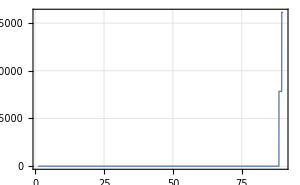

Time used: 0.146598, total time used: 362.8356819
---------------------------------------------

Time used: 0.0045028, total time used: 362.8401847
---------------------------------------------

AlphaValList = {1,1,1,1,1,1}

GammaValList = {1,4,1/4,1/4,1/16,1/16}

```mathematica
(* ============================================== *)
ClearAll["Global`*"];
(* ============================================== *)
Needs["NumericalCalculus`"];
PathList={"W:\\STM\\"};
Get["STM_Init.m",Path-> PathList];
(* ============================================= *)
rawOpts={UseY6 -> True,UseComplexVariables -> True,UseReImVariables -> True, CalculateEVPrimData -> True, UseEVPrimNumeric -> True,UseGamma2Value -> False,UseFullySymmetricPoly -> True,UseSymplecticIntegrator -> True,DoPlotSab -> True,NAPlot -> 1,NAPlotMax -> 5,UseHighPrecision -> True,HighPrecisionValue -> 100,OutputVariables -> False,UseAlternatingAS -> False};
(* ============================================= *)
LoadModules[PathList,rawOpts];
(* ============================================= *)

(* Various parameterts *)
NumberOfElements=10;
NMaxPlot=100*0;
tMax=200;

PrintHessian=True;

NT=1;
NS=3;

rndFunc=NormalDistribution;
rndArgs={0,10^-1};

IVTSpaceScale=1;
IVTTimeScale=1;

TTTval=10000/10000;

NoiseLevel=10^-6;

IMAGESIZE=300;

(* ============================================= *)
InitializeDynamicModel[NumberOfElements,rawOpts];
(* ============================================= *)
AlphaValList=Table[1,{ii,1,MaxMoment}];
(* AlphaValList={1,200/200,90/90,200/200,2}; *)
(* AlphaValList={0,0,1,0,0}; *)
(* AlphaValList={0,0,1,0,0,0}; *)
(* ============================================= *)
UseFullySymmetricPolyVal=UseFullySymmetricPoly /.rawOpts /.Options[STMDynamics];
UseUUL2Val=UseUUL2 /.rawOpts /.Options[STMDynamics];
(* ============================================= *)
Print["Creating initial values for numerical run."];
CreateInitialvalues[IVTdistribution,NIVnone,rawOpts];

(* CreateInitialvalues[IVT4DPoints,NIVnone,rawOpts]; *)
(* CreateInitialvalues[IVT4DMinPolyValue,NIVnone,rawOpts]; *)
(* CreateInitialvalues[IVT4DPointsWithNoise,NIVnone,rawOpts]; *)
PrintTimeUsed[];

(* ============================================= *)
If[NumberOfElements ≤6,
(
Print[strSeparator];

Print["Symbolic Y and related."];
Y=CalculateHY[S,A,False];
Print["Y = ",Expand[Y] // MatrixForm];

yABmyBA=Table[Y[[ii,jj]]-Y[[jj,ii]],{ii,1,NNN},{jj,1,NNN}];
Print["yABmyBA = ",Expand[yABmyBA] // MatrixForm];

yAAmyBB=Table[Y[[ii,ii]]-Y[[jj,jj]],{ii,1,NNN},{jj,1,NNN}];
Print["yAAmyBB = ",Expand[yAAmyBB] // MatrixForm];

yFuncVal=yFunc[S,A,True];
Print["yFuncVal = ",Expand[yFuncVal] // MatrixForm];

Print["(yFuncVal - Y) = ",Expand[yFuncVal-Y] // MatrixForm];

Winv=Expand[CalculateSfromY[Y]];
Print["Winv = ",Winv // MatrixForm];

Print["Winv - yABmyBA = ",Expand[Winv-yABmyBA] // MatrixForm];

WinvIm=I*RemoveI[-I*Winv];
Print["WinvIm = ",WinvIm // MatrixForm];
Print[" Sum by rows of WinvIm = ", Expand[Table[Sum[WinvIm[[ii,jj]],{ii,1,NNN}],{jj,1,NNN}]] // MatrixForm];


Print["(Winv - W) = ",Expand[(Winv-(S+I*A))] // MatrixForm];

WinvmW=(Winv-(S+I*A));
Print[" Sum by rows of WinvmW = ", Table[Sum[WinvmW[[ii,jj]],{ii,1,NNN}],{jj,1,NNN}] // MatrixForm];


Yinv=CalculateY[Winv,False];
Print["Y - Yinv = ",Expand[Y-Yinv] // MatrixForm];
PrintTimeUsed[];
)
];

(* ============================================= *)
(* PlotXXT[SI]; *)
sol=FindUncorrelatedCoordinates[SI+I*AI,rawOpts];
ee=GetE[sol];
lambdaVec=GetLambdaVec[sol];
eeprimIJ=GetEprimIJ[sol];
(* ============================================= *)

Print["e = ", Chop[N[ee]]  // MatrixForm];
Print["eeprimIJ = ", Chop[N[eeprimIJ]]  // MatrixForm];
Print["Λ = ", Chop[N[DiagonalMatrix[lambdaVec]]] // MatrixForm];

Print["eeprimIJ . ConjugateTranspose[eeprimIJ] = ", Chop[N[eeprimIJ . ConjugateTranspose[eeprimIJ]]] // MatrixForm];
Print["ConjugateTranspose[eeprimIJ] . eeprimIJ = ", Chop[N[ConjugateTranspose[eeprimIJ] . eeprimIJ]] // MatrixForm];


(* ============================================= *)

Print["Reconstructing SI"];
siReconstr=CalculateSfromLambdaVec[lambdaVec,ee];
Print["SI + I*AI - siReconstr = ", Chop[N[SI + I*AI- siReconstr]]  // MatrixForm];

(* ============================================= *)

Print[strSeparator];

Print["Reconstructing ee back."];
eerpFinal=eeReconstruct[eeprimIJ];
Print["e = ", N[ee]  // MatrixForm];
Print["eerpFinal = ", N[eerpFinal]  // MatrixForm];

Print["eerpFinal . ConjugateTranspose[eerpFinal] = ", Chop[N[eerpFinal . ConjugateTranspose[eerpFinal]]] // MatrixForm];
Print["ConjugateTranspose[eerpFinal] . eerpFinal = ", Chop[N[ConjugateTranspose[eerpFinal] . eerpFinal]] // MatrixForm];

Print["N[alphaIJ] = ", N[alphaIJ]  // MatrixForm];
(* Print["alphaIJ = ",alphaIJ  // MatrixForm]; *)

Print["e-eerpFinal = ", Chop[N[ee-eerpFinal]]  // MatrixForm];

(* ============================================= *)
Print["SI = ", N[SI]//MatrixForm];
Print["S = ", S//MatrixForm];

Print["AI = ", N[AI]//MatrixForm];
Print["A = ", A//MatrixForm];

CalculateYInvariants[SI,AI];
For[level=1,level ≤ MaxMoment,level++,
(
Print[strSeparator];
moment=mFuncYk[level,SI,AI,False];
Print["mFuncY",level," = ", moment];
)
];

(* ============================================= *)

Print[strSeparator];

Print["Constraining to R(",NT,", ",NS,")..."];

lambdaVec4D=lambdaFunc[NumberOfElements,NT,NS,TTTval];
Print["lambdaVec4D = ",N[lambdaVec4D] // MatrixForm];

div=10000/10000;
lambda4D=DiagonalMatrix[lambdaVec4D];
wi4D=(1/div)*CalculateSfromLambdaVec[lambdaVec4D,ee];
Print["wi4D = ",Chop[N[wi4D]] // MatrixForm];

si4D=Re[wi4D];
ai4D=Im[wi4D];

si4DLinear=ToSLinear[si4D];
ai4DLinear=ToALinear[ai4D];

si4DLinearSorted=Sort[si4DLinear];
ai4DLinearSorted=Sort[ai4DLinear];

Print["div = ",N[div]];
Print["1/div = ",N[1/div]];
Print["Sqrt[GammaValList[[2]]] = ", N[Sqrt[GammaValList[[2]]]]];
Print["lambdaVec4D = ",lambdaVec4D];
Print["lambda4D = ",lambda4D// MatrixForm];
Print["si4D = ",N[si4D] // MatrixForm];
(* Print["si4DLinear = ",si4DLinear]; *)

Print["ai4D = ",N[ai4D] // MatrixForm];
(* Print["ai4DLinear = ",ai4DLinear]; *)

(* ============================================= *)

Print[strSeparator];

Print["Calculating e for constrained elements... "];

solC=FindUncorrelatedCoordinates[wi4D,rawOpts];
eeC=GetE[solC];
lambdaVecC=GetLambdaVec[solC];
eeprimIJC=GetEprimIJ[solC];

Print["e - eC = ", Chop[N[ee-eeC]]  // MatrixForm];
Print["(eeprimIJ - eeprimIJC) = ", Chop[N[eeprimIJ-eeprimIJC]]  // MatrixForm];
Print["ΛC = ", Chop[N[DiagonalMatrix[lambdaVecC]]] // MatrixForm];
Print["e = ", Chop[N[ee]]  // MatrixForm];
Print["eC = ", Chop[N[eeC]]  // MatrixForm];

wi4DC=(1/div)*CalculateSfromLambdaVec[lambdaVecC,eeC];
Print["(wi4D - wi4DC) = ",Chop[N[wi4D-wi4DC]] // MatrixForm];

Y4D=CalculateY[wi4D,False];
Print["Y4D = ",Chop[N[Y4D]]// MatrixForm];

Y4DC=CalculateY[wi4DC,False];
Print["Y4DC = ",Chop[N[Y4DC]]// MatrixForm];

Print["(Y4D - Y4DC) = ",Chop[N[Y4D-Y4DC]] // MatrixForm];

(* ============================================= *)

Print[strSeparator];

Print["Checking R(",NT,", ",NS,") constraint."];

Print["AlphaValList = ",N[AlphaValList] // MatrixForm];
Print["GammaValList = ",N[GammaValList] // MatrixForm];

CalculateYInvariants[si4D,ai4D];
uukAll=Table[UUk[level,si4D,ai4D,GammaValList[[level]],UseUUL2Val,UseFullySymmetricPolyVal,False],{level,1,5}];
Print["uukAll = ",Chop[N[uukAll]] // MatrixForm];
(* Print["uukAll = ",uukAll // MatrixForm]; *)

uuTestVal=UUAll[si4D,ai4D,GammaValList,AlphaValList,UseUUL2Val,UseFullySymmetricPolyVal];
Print["uuTestVal = ",Chop[N[uuTestVal]]];
(* Print["uuTestVal = ",uuTestVal]; *)

DuuTestVal=DUUAll[si4D,ai4D,GammaValList,AlphaValList,UseUUL2Val,UseFullySymmetricPolyVal];
Print["DuuTestVal = ",Chop[N[DuuTestVal]]];
(* Print["DuuTestVal = ",DuuTestVal]; *)
PrintTimeUsed[];

(* ============================================= *)

Print[strSeparator];

Print["Hessian for UUAll."];
DabDcdUUAllVal=DabDcdUUAll[si4D,ai4D,GammaValList,AlphaValList,UseUUL2Val,UseFullySymmetricPolyVal];

If[PrintHessian,
(
Print["DabDcdUUAllVal = ",Chop[N[DabDcdUUAllVal]] // MatrixForm];
)
];

Print["Eigensystem"];
eSysHessian=Eigensystem[DabDcdUUAllVal];
eValHessian=eSysHessian[[1]];
eVecHessian=eSysHessian[[2]];
eValHessianSorted=Sort[Re[eValHessian]];
Print["eValHessian = ", Chop[N[eValHessian]]];
(* Print["eValHessian = ", eValHessian // MatrixForm]; *)
Print["eVecHessian = ", Chop[N[eVecHessian]] // MatrixForm];
PrintTimeUsed[];

(* ============================================= *)

Print[strSeparator];

Print["Hessian for Up12."];
CkValList=Table[mAnalyticFunc[ii,NT,NS,TTTval],{ii,1,MaxMoment}];

Print["AlphaValList = ", AlphaValList];
Print["CkValList = ", CkValList];

Print["up12Val"];
up12Val=Up12[si4D,ai4D,CkValList,AlphaValList];
Print["up12Val = ", Chop[N[up12Val]]];
PrintTimeUsed[];

Print["dup12Val"];
dup12Val=DUp12[si4D,ai4D,CkValList,AlphaValList];
Print["dup12Val = ", Chop[N[dup12Val]]];
PrintTimeUsed[];

Print["ddup12Val"];
ddup12Val=DabDcdUp12[si4D,ai4D,CkValList,AlphaValList];

If[PrintHessian,
(
Print["ddup12Val = ",Chop[N[ddup12Val]] // MatrixForm];
)
];

PrintTimeUsed[];

Print["Eigensystem"];
eSysHessian=Eigensystem[ddup12Val];
eValHessian=eSysHessian[[1]];
eVecHessian=eSysHessian[[2]];
eValHessianSorted=Sort[Re[eValHessian]];
Print["eValHessian = ", Chop[N[eValHessian]]];
(* Print["eValHessian = ", eValHessian // MatrixForm]; *)
Print["eVecHessian = ", Chop[N[eVecHessian]] // MatrixForm];
PrintTimeUsed[];

Print["Hessian eigenvalues"];
Print[Plot[IndexedVariableFunc[idx,eValHessianSorted],{idx,1,NAL},Evaluate[defaultPltOpts]]];
PrintTimeUsed[];
(* ============================================= *)

Print[strSeparator];

Print["Hessian for Up10."];
CkValList=Table[mAnalyticFunc[ii,NT,NS,TTTval],{ii,1,MaxMoment}];

Print["AlphaValList = ", AlphaValList];
Print["CkValList = ", CkValList];

Print["up10Val"];
up10Val=Up10[si4D,ai4D,CkValList,AlphaValList];
Print["up10Val = ", Chop[N[up10Val]]];
PrintTimeUsed[];

Print["dup10Val"];
dup10Val=DUp10[si4D,ai4D,CkValList,AlphaValList];
Print["dup10Val = ", Chop[N[dup10Val]]];
PrintTimeUsed[];

Print["ddup10Val"];
ddup10Val=DabDcdUp10[si4D,ai4D,CkValList,AlphaValList];

If[PrintHessian,
(
Print["ddup10Val = ",Chop[N[ddup10Val]] // MatrixForm];
)
];

PrintTimeUsed[];

Print["Eigensystem"];
eSysHessian=Eigensystem[ddup10Val];
eValHessian=eSysHessian[[1]];
eVecHessian=eSysHessian[[2]];
eValHessianSorted=Sort[Re[eValHessian]];
Print["eValHessian = ", Chop[N[eValHessian]]];
(* Print["eValHessian = ", eValHessian // MatrixForm]; *)
Print["eVecHessian = ", Chop[N[eVecHessian]] // MatrixForm];
PrintTimeUsed[];

Print["Hessian eigenvalues"];
Print[Plot[IndexedVariableFunc[idx,eValHessianSorted],{idx,1,NAL},Evaluate[defaultPltOpts]]];
PrintTimeUsed[];

(* ============================================= *)

plotOpts=Flatten[{defaultPltOpts2,{PlotPoints -> 2*NAL}}];
plotOptsAll=Flatten[{defaultPltOpts,{PlotPoints -> 2*NAL}}];

MaxPlot=Min[NAL,NMaxPlot];
For[idx=1,idx ≤ MaxPlot, idx++,
(
Print[strSeparator];
Print["idx = ", idx, ", eValHessian[[",idx,"]] = ", eValHessian[[idx]]];
eVecIdx=Re[eVecHessian[[idx]]];
eVecIdxSorted=Sort[eVecIdx];
Print[Plot[{IndexedVariableFunc[idx,eVecIdx],IndexedVariableFunc[idx,eVecIdxSorted]},{idx,1,NAL},Evaluate[plotOptsAll]]," ",Plot[{IndexedVariableFunc[idx,si4DLinear],IndexedVariableFunc[idx,si4DLinearSorted]},{idx,1,NAL},Evaluate[plotOptsAll]], " ", 
Plot[{IndexedVariableFunc[idx,ai4DLinear],IndexedVariableFunc[idx,ai4DLinearSorted]},{idx,1,NAL},Evaluate[plotOptsAll]], " ", 
Plot[IndexedVariableFunc[idx,eVecIdx]/IndexedVariableFunc[idx,si4DLinear],{idx,1,NAL},Evaluate[plotOpts]]];
)
];
PrintTimeUsed[];

(* ============================================= *)

(*
Print["Eigenvalues"];
eValHessian=Eigenvalues[DabDcdUUAllVal];
eValHessianSorted=Sort[Re[eValHessian]];
Print["eValHessian = ", N[eValHessian] // MatrixForm];
PrintTimeUsed[];

Print["Hessian eigenvalues"];
Print[Plot[IndexedVariableFunc[idx,eValHessianSorted],{idx,1,NAL},Evaluate[defaultPltOpts]]];
PrintTimeUsed[];
*)


(*
eps=10^-12;
idxVec=4;

MaxEpsCnt=4;
For[idxEps=1,idxEps ≤ MaxEpsCnt,idxEps++,
(
Print[strSeparator];
Print["Adding ",eps," * eVecHessian[[",idxVec,"]] to si4DLinear."];
Print["idxVec = ", idxVec, ", eValHessian[[",idxVec,"]] = ", N[eValHessian[[idxVec]]]];
Print["eVecHessian[[",idxVec,"]] = ", N[eVecHessian[[idxVec]]]];
si4DLinearEps=si4DLinear+eps*eVecHessian[[idxVec]];

si4DEps=ToMatrix[si4DLinearEps];

up10ValEps=Up10[si4DEps,CkValList,AlphaValList];
Print["up10ValEps = ", N[up10ValEps]];

dup10ValEps=DUp10[si4DEps,CkValList,AlphaValList];
Print["dup10ValEps = ", N[dup10ValEps] // MatrixForm];

dup10ValEpsLinear=ToLinear[dup10ValEps];
dup10ValEpsSqAvg=Sqrt[Sum[dup10ValEpsLinear[[ii]]^2,{ii,1,NA}]/NA];
Print["dup10ValEpsSqAvg = ", N[dup10ValEpsSqAvg]];

eps=eps*10;
)
];
*)
(* ============================================= *)

(*
ddup10ValEps=ToLinearHessian[DabDcdUp10[si4DEps,CkValList,AlphaValList]];

Print["ddup10ValEps = ",N[ddup10ValEps] // MatrixForm];
PrintTimeUsed[];

Print["Eigensystem"];
eSysHessianEps=Eigensystem[ddup10ValEps];
eValHessianEps=eSysHessian[[1]];
eVecHessianEps=eSysHessian[[2]];
eValHessianEpsSorted=Sort[Re[eValHessianEps]];
Print["eValHessianEps = ", N[eValHessianEps] // MatrixForm];
(* Print["eValHessian = ", eValHessian // MatrixForm]; *)
Print["eVecHessianEps = ", N[eVecHessianEps] // MatrixForm];
PrintTimeUsed[];
*)

(*
MaxPlot=Min[NA,10];
For[idx=1,idx ≤ MaxPlot, idx++,
(
Print[strSeparator];
Print["idx = ", idx, ", eValHessian[[",idx,"]] = ", eValHessian[[idx]]];
eVecIdx=Re[eVecHessian[[idx]]];
eVecIdxSorted=Sort[eVecIdx];
Print[Plot[{IndexedVariableFunc[idx,eVecIdx],IndexedVariableFunc[idx,eVecIdxSorted]},{idx,1,NA},Evaluate[plotOpts]]," ",Plot[{IndexedVariableFunc[idx,si4DLinear],IndexedVariableFunc[idx,si4DLinearSorted]},{idx,1,NA},Evaluate[plotOpts]], " ", Plot[IndexedVariableFunc[idx,eVecIdx]/IndexedVariableFunc[idx,si4DLinear],{idx,1,NA},Evaluate[plotOpts]]];
)
];
*)


(* ============================================= *)
(*
Print["Resetting initial values of S to 4D poits (as obtained above) + noise (original SI)."];
(* SIL=si4DLinear + SIL; *)
SIL=si4DLinear;
SIL[[1]]=SIL[[1]]+10^-4;
SI=ToMatrix[SIL];
*)
Print["AlphaValList = ", AlphaValList];
Print["GammaValList = ", GammaValList];
(* DynamicsRun[tMax,GammaValList,AlphaValList,rawOpts]; *)

(* ============================================= *)
```